```mathematica
Import["coulombLog/main/StoppingPower3.4.m"]
```

## Case A: ne=2E26/cc; nd=nt=1E26/cc; T=1 keV; α particle projectile E=0-3.5MeV

### define parameters

```mathematica
(*
nrho=6500 (* g/cm^3 ; A*Ng = 1 g *)
nrho*(2/5.01)*(6.02*10^23)            (* electron number density in 1/cm^3 *)
*)
```

```mathematica
id="A";
T=1.    (* keV   *); (* 50 and 150 keV *)
ne=2.      (* cm^-3 *);
nn=26     (* ne*10^nn cm^-3 *);

Zp=2                       (*Charge of probe in units of|e|*);
mp=4*mpev          (*mass of projectile in eV*);

Zb={-1,1,1}                                                              (*charge of plasma species in units of|e|*);
mb={meev,2*mpev,3*mpev}                              (*mass of plasma in ev*);
nb={10^nn,0.5*10^nn,0.5*10^nn}*ne    (*density/cm^3*);

β=1/(T*10^3)//N    (*inverse temp in eV^-1*);
r=3                                      (*vth=c*Sqrt[r/(β*mi)] is thermal velocity:units in cm/s*);
i=1                                      (*thermal velocity of i-th plasma species*);
mtr=10^(-6)                  (*distance unit in meters*);
ev=10^6                           (*energy unit in eV*);
convfact=cmtoa0*(mtr*100)/ev   (*atomic units to MeV/μm*);
nb=nb/cmtoa0^3         (*number of plasma species:units of a0^-3*);
Plus@@(Zb*nb)              (*total charge:should vanish*)
```

0.

```mathematica
param[β,Zp,mp,mb,Zb,nb,r,i,1] (*set parameters for BPS*)
```

gD=0.245433

gpb={0.173547,0.122716,0.122716}

etb*Sqrt[mb0]={0.190702,11.5564,14.1537}

```mathematica
paramLP[β,Zp,mp,mb,Zb,nb,r,i,1,1] (*set parameters for LP*)
```

```mathematica
vth=StoppingPower`PrivateBPS`vth
vthc=StoppingPower`PrivateBPS`vthc
```

2.29711×10^9

0.0766215

```mathematica
mp
```

3.75309×10^9

```mathematica
Clear[VP]
mpMev=mp/10^6;
VP[E_] := Sqrt[2*E/mpMev]/vthc
EMev[vp_] := 0.5*mpMev*(vp*vthc)^2


E0=3.54
vp0=VP[E0]
EMev[vp0]
```

3.54

0.566855

3.54

### LP

#### evaluate data

```mathematica
emin=0.001;
emax=3.54;
```

```mathematica
E1=emin;
E2=0.03;
NN=600;
dE=(E2-E1)/NN;
dataLPa=Table[{EE,dedxiLP[VP[EE]]},{EE,E1,E2,dE}];
```

```mathematica
E1=E2+dE;
E2=0.25;
NN=600;
dE=(E2-E1)/NN;
dataLPb=Table[{EE,dedxiLP[VP[EE]]},{EE,E1,E2,dE}];
```

```mathematica
E1=E2+dE;
E2=emax;
NN=600;
dE=(E2-E1)/NN;
dataLPc=Table[{EE,dedxiLP[VP[EE]]},{EE,E1,E2,dE}];
```

```mathematica
dataLPEI=Join[dataLPa,dataLPb,dataLPc]
```

{{0.001,{0.080791,2.61896,3.65473}},{0.00104833,{0.0842649,2.79731,3.83144}},{0.00109667,{0.087626,2.96601,3.99621}},{0.001145,{0.0908836,3.12579,4.14986}},{0.00119333,{0.0940463,3.27727,4.29315}},{0.00124167,{0.0971211,3.42101,4.42675}},{0.00129,{0.100115,3.5575,4.55128}},{0.00133833,{0.103033,3.68719,5.28029}},{0.00138667,{0.10588,3.81046,5.45602}},{0.001435,{0.108661,3.92769,5.61671}},{0.00148333,{0.111381,4.03921,5.76372}},{0.00153167,{0.114042,4.14531,5.89825}},{0.00158,{0.116649,4.24627,6.02134}},{0.00162833,{0.119204,4.34236,6.13394}},{0.00167667,{0.12171,4.4338,6.23687}},{0.001725,{0.12417,4.52082,6.33088}},{0.00177333,{0.126586,4.60362,6.41665}},{0.00182167,{0.12896,4.6824,6.49478}},{0.00187,{0.131294,4.75733,6.56582}},{0.00191833,{0.133591,4.82857,6.63027}},{0.00196667,{0.135851,4.8963,6.68858}},{0.002015,{0.138076,5.58104,6.74118}},{0.00206333,{0.140269,5.68763,6.78844}},{0.00211167,{0.142429,5.78769,6.83072}},{0.00216,{0.14456,5.88162,6.86834}},{0.00220833,{0.146661,5.96981,6.9016}},{0.00225667,{0.148734,6.05262,6.93078}},{0.002305,{0.150779,6.13035,6.95613}},{0.00235333,{0.152799,6.20331,6.97789}},{0.00240167,{0.154794,6.27177,6.99629}},{0.00245,{0.156764,6.33597,7.01154}},{0.00249833,{0.158711,6.39616,7.02382}},{0.00254667,{0.160635,6.45255,7.03332}},{0.002595,{0.162538,6.50534,7.04021}},{0.00264333,{0.164419,6.55472,7.04464}},{0.00269167,{0.16628,6.60087,7.04677}},{0.00274,{0.168121,6.64394,7.04673}},{0.00278833,{0.169943,6.68409,7.04466}},{0.00283667,{0.171746,6.72147,7.04068}},{0.002885,{0.173531,6.75621,7.0349}},{0.00293333,{0.175299,6.78844,7.02744}},{0.00298167,{0.177049,6.81828,7.0184}},{0.00303,{0.178783,6.84583,7.00787}},{0.00307833,{0.180501,6.87121,6.99595}},{0.00312667,{0.182202,6.89452,6.98273}},{0.003175,{0.183889,6.91584,6.96828}},{0.00322333,{0.185561,6.93528,6.95269}},{0.00327167,{0.187218,6.95291,6.93602}},{0.00332,{0.188861,6.96882,6.91835}},{0.00336833,{0.19049,6.98308,6.89975}},{0.00341667,{0.192106,6.99576,6.88026}},{0.003465,{0.193708,7.00695,6.85996}},{0.00351333,{0.195298,7.01669,6.8389}},{0.00356167,{0.196875,7.02505,6.81712}},{0.00361,{0.19844,7.0321,6.79469}},{0.00365833,{0.199993,7.03788,6.77164}},{0.00370667,{0.201534,7.04246,6.74803}},{0.003755,{0.203063,7.04589,6.72389}},{0.00380333,{0.204582,7.04821,6.69927}},{0.00385167,{0.206089,7.04947,6.6742}},{0.0039,{0.207586,7.04972,6.64871}},{0.00394833,{0.209072,7.049,6.62285}},{0.00399667,{0.210548,7.04735,6.59665}},{0.004045,{0.212014,7.04482,6.57013}},{0.00409333,{0.21347,7.04143,6.54333}},{0.00414167,{0.214917,7.03723,6.51626}},{0.00419,{0.216353,7.03226,6.48897}},{0.00423833,{0.217781,7.02653,6.46147}},{0.00428667,{0.219199,7.02009,6.43379}},{0.004335,{0.220608,7.01297,6.40595}},{0.00438333,{0.222009,7.0052,6.37796}},{0.00443167,{0.223401,6.9968,6.34986}},{0.00448,{0.224784,6.9878,6.32165}},{0.00452833,{0.226159,6.97823,6.29336}},{0.00457667,{0.227526,6.96812,6.26501}},{0.004625,{0.228884,6.95748,6.2366}},{0.00467333,{0.230235,6.94635,6.20815}},{0.00472167,{0.231578,6.93474,6.17969}},{0.00477,{0.232914,6.92267,6.15121}},{0.00481833,{0.234242,6.91017,6.12274}},{0.00486667,{0.235562,6.89725,6.09429}},{0.004915,{0.236875,6.88394,6.06587}},{0.00496333,{0.238181,6.87025,6.03748}},{0.00501167,{0.23948,6.8562,6.00914}},{0.00506,{0.240773,6.84181,5.98086}},{0.00510833,{0.242058,6.82709,5.95264}},{0.00515667,{0.243336,6.81207,5.9245}},{0.005205,{0.244608,6.79675,5.89644}},{0.00525333,{0.245874,6.78115,5.86847}},{0.00530167,{0.247133,6.76528,5.8406}},{0.00535,{0.248386,6.74916,5.81283}},{0.00539833,{0.249632,6.7328,5.78517}},{0.00544667,{0.250872,6.71622,5.75763}},{0.005495,{0.252107,6.69942,5.7302}},{0.00554333,{0.253335,6.68242,5.70291}},{0.00559167,{0.254557,6.66522,5.67574}},{0.00564,{0.255774,6.64785,5.6487}},{0.00568833,{0.256985,6.63031,5.62181}},{0.00573667,{0.25819,6.6126,5.59505}},{0.005785,{0.25939,6.59475,5.56844}},{0.00583333,{0.260584,6.57675,5.54198}},{0.00588167,{0.261773,6.55863,5.51567}},{0.00593,{0.262957,6.54038,5.48951}},{0.00597833,{0.264135,6.52202,5.46351}},{0.00602667,{0.265308,6.50354,5.43767}},{0.006075,{0.266476,6.48498,5.41199}},{0.00612333,{0.267639,6.46632,5.38647}},{0.00617167,{0.268797,6.44757,5.36112}},{0.00622,{0.26995,6.42875,5.33593}},{0.00626833,{0.271098,6.40986,5.3109}},{0.00631667,{0.272242,6.3909,5.28605}},{0.006365,{0.27338,6.37189,5.26136}},{0.00641333,{0.274514,6.35283,5.23684}},{0.00646167,{0.275643,6.33372,5.2125}},{0.00651,{0.276768,6.31457,5.18832}},{0.00655833,{0.277888,6.29538,5.16431}},{0.00660667,{0.279004,6.27617,5.14048}},{0.006655,{0.280115,6.25693,5.11682}},{0.00670333,{0.281222,6.23767,5.09333}},{0.00675167,{0.282325,6.21839,5.07001}},{0.0068,{0.283423,6.19911,5.04687}},{0.00684833,{0.284517,6.17981,5.02389}},{0.00689667,{0.285607,6.16052,5.00109}},{0.006945,{0.286693,6.14122,4.97846}},{0.00699333,{0.287775,6.12194,4.956}},{0.00704167,{0.288852,6.10265,4.93371}},{0.00709,{0.289926,6.08339,4.91159}},{0.00713833,{0.290996,6.06413,4.88964}},{0.00718667,{0.292062,6.0449,4.86786}},{0.007235,{0.293124,6.02569,4.84625}},{0.00728333,{0.294182,6.0065,4.8248}},{0.00733167,{0.295236,5.98734,4.80353}},{0.00738,{0.296287,5.96821,4.78241}},{0.00742833,{0.297334,5.94911,4.76147}},{0.00747667,{0.298377,5.93005,4.74068}},{0.007525,{0.299417,5.91103,4.72007}},{0.00757333,{0.300453,5.89204,4.69961}},{0.00762167,{0.301486,5.8731,4.67931}},{0.00767,{0.302515,5.85421,4.65918}},{0.00771833,{0.303541,5.83536,4.6392}},{0.00776667,{0.304563,5.81655,4.61938}},{0.007815,{0.305582,5.7978,4.59972}},{0.00786333,{0.306597,5.7791,4.58022}},{0.00791167,{0.307609,5.76046,4.56087}},{0.00796,{0.308618,5.74187,4.54168}},{0.00800833,{0.309623,5.72333,4.52264}},{0.00805667,{0.310626,5.70486,4.50375}},{0.008105,{0.311625,5.68644,4.48501}},{0.00815333,{0.312621,5.66809,4.46642}},{0.00820167,{0.313613,5.6498,4.44797}},{0.00825,{0.314603,5.63157,4.42968}},{0.00829833,{0.315589,5.61341,4.41153}},{0.00834667,{0.316573,5.59531,4.39352}},{0.008395,{0.317553,5.57728,4.37566}},{0.00844333,{0.318531,5.55931,4.35794}},{0.00849167,{0.319505,5.54142,4.34036}},{0.00854,{0.320476,5.52359,4.32292}},{0.00858833,{0.321445,5.50584,4.30562}},{0.00863667,{0.322411,5.48815,4.28846}},{0.008685,{0.323373,5.47054,4.27143}},{0.00873333,{0.324333,5.453,4.25454}},{0.00878167,{0.32529,5.43554,4.23778}},{0.00883,{0.326245,5.41814,4.22115}},{0.00887833,{0.327196,5.40083,4.20466}},{0.00892667,{0.328145,5.38358,4.18829}},{0.008975,{0.329091,5.36641,4.17205}},{0.00902333,{0.330034,5.34932,4.15594}},{0.00907167,{0.330975,5.3323,4.13996}},{0.00912,{0.331913,5.31536,4.1241}},{0.00916833,{0.332848,5.2985,4.10837}},{0.00921667,{0.333781,5.28171,4.09275}},{0.009265,{0.334711,5.26501,4.07726}},{0.00931333,{0.335639,5.24837,4.06189}},{0.00936167,{0.336564,5.23182,4.04664}},{0.00941,{0.337486,5.21535,4.03151}},{0.00945833,{0.338406,5.19895,4.01649}},{0.00950667,{0.339324,5.18263,4.00159}},{0.009555,{0.340239,5.16639,3.9868}},{0.00960333,{0.341151,5.15023,3.97213}},{0.00965167,{0.342061,5.13415,3.95757}},{0.0097,{0.342969,5.11814,3.94312}},{0.00974833,{0.343874,5.10222,3.92878}},{0.00979667,{0.344777,5.08637,3.91455}},{0.009845,{0.345678,5.0706,3.90043}},{0.00989333,{0.346576,5.05492,3.88642}},{0.00994167,{0.347472,5.03931,3.87251}},{0.00999,{0.348366,5.02377,3.8587}},{0.0100383,{0.349257,5.00832,3.845}},{0.0100867,{0.350146,4.99295,3.8314}},{0.010135,{0.351033,4.97765,3.8179}},{0.0101833,{0.351918,4.96243,3.80451}},{0.0102317,{0.3528,4.94729,3.79121}},{0.01028,{0.35368,4.93223,3.77801}},{0.0103283,{0.354559,4.91725,3.76491}},{0.0103767,{0.355434,4.90234,3.75191}},{0.010425,{0.356308,4.88751,3.739}},{0.0104733,{0.35718,4.87276,3.72618}},{0.0105217,{0.358049,4.85809,3.71346}},{0.01057,{0.358917,4.84349,3.70084}},{0.0106183,{0.359782,4.82897,3.6883}},{0.0106667,{0.360645,4.81453,3.67585}},{0.010715,{0.361506,4.80016,3.6635}},{0.0107633,{0.362365,4.78587,3.65123}},{0.0108117,{0.363222,4.77165,3.63906}},{0.01086,{0.364077,4.75751,3.62696}},{0.0109083,{0.36493,4.74345,3.61496}},{0.0109567,{0.365782,4.72945,3.60304}},{0.011005,{0.366631,4.71554,3.59121}},{0.0110533,{0.367478,4.7017,3.57946}},{0.0111017,{0.368323,4.68793,3.56779}},{0.01115,{0.369166,4.67423,3.5562}},{0.0111983,{0.370008,4.66061,3.5447}},{0.0112467,{0.370847,4.64706,3.53328}},{0.011295,{0.371685,4.63359,3.52193}},{0.0113433,{0.37252,4.62019,3.51067}},{0.0113917,{0.373354,4.60685,3.49948}},{0.01144,{0.374186,4.5936,3.48837}},{0.0114883,{0.375016,4.58041,3.47734}},{0.0115367,{0.375844,4.56729,3.46638}},{0.011585,{0.376671,4.55424,3.4555}},{0.0116333,{0.377495,4.54127,3.44469}},{0.0116817,{0.378318,4.52836,3.43396}},{0.01173,{0.379139,4.51553,3.4233}},{0.0117783,{0.379959,4.50276,3.41271}},{0.0118267,{0.380776,4.49006,3.40219}},{0.011875,{0.381592,4.47743,3.39174}},{0.0119233,{0.382406,4.46487,3.38136}},{0.0119717,{0.383218,4.45237,3.37106}},{0.01202,{0.384029,4.43995,3.36082}},{0.0120683,{0.384838,4.42759,3.35065}},{0.0121167,{0.385645,4.41529,3.34054}},{0.012165,{0.38645,4.40307,3.3305}},{0.0122133,{0.387254,4.39091,3.32053}},{0.0122617,{0.388056,4.37881,3.31063}},{0.01231,{0.388857,4.36678,3.30078}},{0.0123583,{0.389656,4.35482,3.29101}},{0.0124067,{0.390453,4.34292,3.28129}},{0.012455,{0.391249,4.33108,3.27164}},{0.0125033,{0.392043,4.31931,3.26205}},{0.0125517,{0.392835,4.3076,3.25253}},{0.0126,{0.393626,4.29595,3.24306}},{0.0126483,{0.394415,4.28436,3.23366}},{0.0126967,{0.395203,4.27284,3.22431}},{0.012745,{0.395989,4.26138,3.21502}},{0.0127933,{0.396773,4.24998,3.2058}},{0.0128417,{0.397556,4.23864,3.19663}},{0.01289,{0.398337,4.22737,3.18752}},{0.0129383,{0.399117,4.21615,3.17846}},{0.0129867,{0.399896,4.20499,3.16946}},{0.013035,{0.400673,4.19389,3.16052}},{0.0130833,{0.401448,4.18285,3.15164}},{0.0131317,{0.402222,4.17187,3.1428}},{0.01318,{0.402994,4.16095,3.13403}},{0.0132283,{0.403765,4.15009,3.1253}},{0.0132767,{0.404535,4.13928,3.11664}},{0.013325,{0.405303,4.12853,3.10802}},{0.0133733,{0.406069,4.11784,3.09946}},{0.0134217,{0.406834,4.10721,3.09094}},{0.01347,{0.407598,4.09663,3.08248}},{0.0135183,{0.40836,4.0861,3.07408}},{0.0135667,{0.409121,4.07564,3.06572}},{0.013615,{0.40988,4.06522,3.05741}},{0.0136633,{0.410638,4.05486,3.04915}},{0.0137117,{0.411395,4.04456,3.04094}},{0.01376,{0.41215,4.03431,3.03278}},{0.0138083,{0.412904,4.02411,3.02467}},{0.0138567,{0.413656,4.01397,3.0166}},{0.013905,{0.414407,4.00388,3.00859}},{0.0139533,{0.415157,3.99384,3.00062}},{0.0140017,{0.415905,3.98386,2.99269}},{0.01405,{0.416652,3.97392,2.98482}},{0.0140983,{0.417398,3.96404,2.97699}},{0.0141467,{0.418142,3.95421,2.9692}},{0.014195,{0.418885,3.94443,2.96146}},{0.0142433,{0.419627,3.9347,2.95376}},{0.0142917,{0.420367,3.92502,2.94611}},{0.01434,{0.421106,3.91539,2.9385}},{0.0143883,{0.421844,3.90581,2.93094}},{0.0144367,{0.422581,3.89628,2.92342}},{0.014485,{0.423316,3.8868,2.91594}},{0.0145333,{0.42405,3.87737,2.9085}},{0.0145817,{0.424783,3.86798,2.90111}},{0.01463,{0.425514,3.85864,2.89376}},{0.0146783,{0.426244,3.84935,2.88645}},{0.0147267,{0.426973,3.84011,2.87917}},{0.014775,{0.427701,3.83092,2.87194}},{0.0148233,{0.428427,3.82177,2.86475}},{0.0148717,{0.429152,3.81266,2.8576}},{0.01492,{0.429876,3.80361,2.85049}},{0.0149683,{0.430599,3.79459,2.84342}},{0.0150167,{0.431321,3.78563,2.83639}},{0.015065,{0.432041,3.77671,2.82939}},{0.0151133,{0.43276,3.76783,2.82244}},{0.0151617,{0.433478,3.759,2.81552}},{0.01521,{0.434195,3.75021,2.80864}},{0.0152583,{0.434911,3.74147,2.8018}},{0.0153067,{0.435625,3.73276,2.79499}},{0.015355,{0.436338,3.72411,2.78822}},{0.0154033,{0.43705,3.71549,2.78149}},{0.0154517,{0.437761,3.70692,2.77479}},{0.0155,{0.438471,3.69839,2.76813}},{0.0155483,{0.43918,3.6899,2.7615}},{0.0155967,{0.439887,3.68145,2.75491}},{0.015645,{0.440593,3.67305,2.74835}},{0.0156933,{0.441299,3.66469,2.74183}},{0.0157417,{0.442003,3.65636,2.73534}},{0.01579,{0.442706,3.64808,2.72889}},{0.0158383,{0.443407,3.63984,2.72247}},{0.0158867,{0.444108,3.63164,2.71608}},{0.015935,{0.444808,3.62348,2.70973}},{0.0159833,{0.445506,3.61535,2.70341}},{0.0160317,{0.446204,3.60727,2.69712}},{0.01608,{0.4469,3.59922,2.69087}},{0.0161283,{0.447595,3.59122,2.68464}},{0.0161767,{0.44829,3.58325,2.67845}},{0.016225,{0.448983,3.57532,2.67229}},{0.0162733,{0.449675,3.56743,2.66617}},{0.0163217,{0.450366,3.55958,2.66007}},{0.01637,{0.451056,3.55176,2.654}},{0.0164183,{0.451744,3.54398,2.64797}},{0.0164667,{0.452432,3.53624,2.64196}},{0.016515,{0.453119,3.52854,2.63599}},{0.0165633,{0.453805,3.52087,2.63004}},{0.0166117,{0.454489,3.51323,2.62412}},{0.01666,{0.455173,3.50564,2.61824}},{0.0167083,{0.455856,3.49808,2.61238}},{0.0167567,{0.456537,3.49055,2.60655}},{0.016805,{0.457218,3.48306,2.60076}},{0.0168533,{0.457897,3.4756,2.59499}},{0.0169017,{0.458576,3.46818,2.58924}},{0.01695,{0.459254,3.4608,2.58353}},{0.0169983,{0.45993,3.45344,2.57784}},{0.0170467,{0.460606,3.44612,2.57218}},{0.017095,{0.46128,3.43884,2.56655}},{0.0171433,{0.461954,3.43159,2.56095}},{0.0171917,{0.462626,3.42437,2.55537}},{0.01724,{0.463298,3.41719,2.54982}},{0.0172883,{0.463969,3.41004,2.5443}},{0.0173367,{0.464638,3.40292,2.53881}},{0.017385,{0.465307,3.39583,2.53334}},{0.0174333,{0.465975,3.38878,2.52789}},{0.0174817,{0.466642,3.38175,2.52247}},{0.01753,{0.467308,3.37476,2.51708}},{0.0175783,{0.467972,3.3678,2.51171}},{0.0176267,{0.468636,3.36088,2.50637}},{0.017675,{0.469299,3.35398,2.50106}},{0.0177233,{0.469962,3.34712,2.49577}},{0.0177717,{0.470623,3.34028,2.4905}},{0.01782,{0.471283,3.33348,2.48526}},{0.0178683,{0.471942,3.3267,2.48004}},{0.0179167,{0.472601,3.31996,2.47485}},{0.017965,{0.473258,3.31325,2.46968}},{0.0180133,{0.473915,3.30656,2.46453}},{0.0180617,{0.47457,3.29991,2.45941}},{0.01811,{0.475225,3.29328,2.45431}},{0.0181583,{0.475879,3.28669,2.44924}},{0.0182067,{0.476532,3.28012,2.44419}},{0.018255,{0.477184,3.27358,2.43916}},{0.0183033,{0.477835,3.26708,2.43415}},{0.0183517,{0.478485,3.26059,2.42917}},{0.0184,{0.479135,3.25414,2.42421}},{0.0184483,{0.479783,3.24772,2.41927}},{0.0184967,{0.480431,3.24132,2.41435}},{0.018545,{0.481077,3.23495,2.40946}},{0.0185933,{0.481723,3.22861,2.40459}},{0.0186417,{0.482368,3.2223,2.39974}},{0.01869,{0.483012,3.21601,2.39491}},{0.0187383,{0.483656,3.20975,2.39011}},{0.0187867,{0.484298,3.20352,2.38532}},{0.018835,{0.48494,3.19731,2.38056}},{0.0188833,{0.48558,3.19113,2.37581}},{0.0189317,{0.48622,3.18498,2.37109}},{0.01898,{0.486859,3.17885,2.36639}},{0.0190283,{0.487498,3.17275,2.36171}},{0.0190767,{0.488135,3.16668,2.35705}},{0.019125,{0.488771,3.16063,2.35241}},{0.0191733,{0.489407,3.1546,2.34779}},{0.0192217,{0.490042,3.1486,2.34319}},{0.01927,{0.490676,3.14263,2.33861}},{0.0193183,{0.491309,3.13668,2.33405}},{0.0193667,{0.491942,3.13076,2.32951}},{0.019415,{0.492573,3.12486,2.32499}},{0.0194633,{0.493204,3.11898,2.32049}},{0.0195117,{0.493834,3.11313,2.316}},{0.01956,{0.494463,3.10731,2.31154}},{0.0196083,{0.495092,3.1015,2.3071}},{0.0196567,{0.495719,3.09573,2.30267}},{0.019705,{0.496346,3.08997,2.29827}},{0.0197533,{0.496972,3.08424,2.29388}},{0.0198017,{0.497597,3.07853,2.28951}},{0.01985,{0.498222,3.07285,2.28516}},{0.0198983,{0.498845,3.06719,2.28083}},{0.0199467,{0.499468,3.06155,2.27651}},{0.019995,{0.50009,3.05594,2.27221}},{0.0200433,{0.500712,3.05035,2.26794}},{0.0200917,{0.501332,3.04478,2.26368}},{0.02014,{0.501952,3.03923,2.25943}},{0.0201883,{0.502571,3.03371,2.25521}},{0.0202367,{0.503189,3.0282,2.251}},{0.020285,{0.503807,3.02272,2.24681}},{0.0203333,{0.504423,3.01727,2.24264}},{0.0203817,{0.505039,3.01183,2.23848}},{0.02043,{0.505655,3.00642,2.23434}},{0.0204783,{0.506269,3.00102,2.23022}},{0.0205267,{0.506883,2.99565,2.22611}},{0.020575,{0.507496,2.9903,2.22202}},{0.0206233,{0.508108,2.98497,2.21795}},{0.0206717,{0.508719,2.97966,2.2139}},{0.02072,{0.50933,2.97438,2.20986}},{0.0207683,{0.50994,2.96911,2.20583}},{0.0208167,{0.51055,2.96386,2.20183}},{0.020865,{0.511158,2.95864,2.19784}},{0.0209133,{0.511766,2.95343,2.19386}},{0.0209617,{0.512373,2.94825,2.1899}},{0.02101,{0.512979,2.94308,2.18596}},{0.0210583,{0.513585,2.93794,2.18203}},{0.0211067,{0.51419,2.93281,2.17812}},{0.021155,{0.514794,2.92771,2.17422}},{0.0212033,{0.515398,2.92262,2.17034}},{0.0212517,{0.516001,2.91756,2.16648}},{0.0213,{0.516603,2.91251,2.16263}},{0.0213483,{0.517204,2.90749,2.15879}},{0.0213967,{0.517805,2.90248,2.15497}},{0.021445,{0.518405,2.89749,2.15116}},{0.0214933,{0.519004,2.89252,2.14737}},{0.0215417,{0.519603,2.88757,2.1436}},{0.02159,{0.520201,2.88264,2.13984}},{0.0216383,{0.520798,2.87773,2.13609}},{0.0216867,{0.521395,2.87283,2.13236}},{0.021735,{0.521991,2.86796,2.12864}},{0.0217833,{0.522586,2.8631,2.12494}},{0.0218317,{0.523181,2.85826,2.12125}},{0.02188,{0.523774,2.85344,2.11757}},{0.0219283,{0.524368,2.84864,2.11391}},{0.0219767,{0.52496,2.84385,2.11026}},{0.022025,{0.525552,2.83908,2.10663}},{0.0220733,{0.526143,2.83433,2.10301}},{0.0221217,{0.526734,2.8296,2.0994}},{0.02217,{0.527324,2.82489,2.09581}},{0.0222183,{0.527913,2.82019,2.09223}},{0.0222667,{0.528501,2.81551,2.08867}},{0.022315,{0.529089,2.81085,2.08512}},{0.0223633,{0.529676,2.8062,2.08158}},{0.0224117,{0.530263,2.80157,2.07805}},{0.02246,{0.530849,2.79696,2.07454}},{0.0225083,{0.531434,2.79237,2.07104}},{0.0225567,{0.532019,2.78779,2.06756}},{0.022605,{0.532603,2.78323,2.06408}},{0.0226533,{0.533186,2.77868,2.06062}},{0.0227017,{0.533769,2.77416,2.05718}},{0.02275,{0.534351,2.76964,2.05374}},{0.0227983,{0.534932,2.76515,2.05032}},{0.0228467,{0.535513,2.76067,2.04691}},{0.022895,{0.536093,2.75621,2.04351}},{0.0229433,{0.536673,2.75176,2.04013}},{0.0229917,{0.537252,2.74733,2.03676}},{0.02304,{0.53783,2.74291,2.0334}},{0.0230883,{0.538408,2.73851,2.03005}},{0.0231367,{0.538985,2.73413,2.02671}},{0.023185,{0.539561,2.72976,2.02339}},{0.0232333,{0.540137,2.72541,2.02008}},{0.0232817,{0.540712,2.72107,2.01678}},{0.02333,{0.541287,2.71675,2.01349}},{0.0233783,{0.541861,2.71244,2.01022}},{0.0234267,{0.542434,2.70815,2.00695}},{0.023475,{0.543007,2.70387,2.0037}},{0.0235233,{0.543579,2.69961,2.00046}},{0.0235717,{0.544151,2.69536,1.99723}},{0.02362,{0.544722,2.69113,1.99401}},{0.0236683,{0.545292,2.68691,1.99081}},{0.0237167,{0.545862,2.68271,1.98761}},{0.023765,{0.546431,2.67852,1.98443}},{0.0238133,{0.546999,2.67435,1.98125}},{0.0238617,{0.547567,2.67019,1.97809}},{0.02391,{0.548135,2.66605,1.97494}},{0.0239583,{0.548702,2.66192,1.9718}},{0.0240067,{0.549268,2.6578,1.96868}},{0.024055,{0.549833,2.6537,1.96556}},{0.0241033,{0.550398,2.64961,1.96245}},{0.0241517,{0.550963,2.64554,1.95936}},{0.0242,{0.551527,2.64148,1.95627}},{0.0242483,{0.55209,2.63743,1.9532}},{0.0242967,{0.552653,2.6334,1.95014}},{0.024345,{0.553215,2.62938,1.94708}},{0.0243933,{0.553776,2.62537,1.94404}},{0.0244417,{0.554337,2.62138,1.94101}},{0.02449,{0.554898,2.6174,1.93799}},{0.0245383,{0.555458,2.61344,1.93498}},{0.0245867,{0.556017,2.60949,1.93198}},{0.024635,{0.556576,2.60555,1.92899}},{0.0246833,{0.557134,2.60162,1.92601}},{0.0247317,{0.557692,2.59771,1.92304}},{0.02478,{0.558249,2.59381,1.92008}},{0.0248283,{0.558805,2.58992,1.91713}},{0.0248767,{0.559361,2.58605,1.91419}},{0.024925,{0.559917,2.58219,1.91126}},{0.0249733,{0.560471,2.57834,1.90833}},{0.0250217,{0.561026,2.57451,1.90542}},{0.02507,{0.561579,2.57069,1.90252}},{0.0251183,{0.562133,2.56688,1.89963}},{0.0251667,{0.562685,2.56308,1.89675}},{0.025215,{0.563237,2.5593,1.89388}},{0.0252633,{0.563789,2.55552,1.89102}},{0.0253117,{0.56434,2.55176,1.88817}},{0.02536,{0.56489,2.54802,1.88532}},{0.0254083,{0.56544,2.54428,1.88249}},{0.0254567,{0.56599,2.54056,1.87966}},{0.025505,{0.566539,2.53685,1.87685}},{0.0255533,{0.567087,2.53315,1.87404}},{0.0256017,{0.567635,2.52946,1.87125}},{0.02565,{0.568182,2.52579,1.86846}},{0.0256983,{0.568729,2.52212,1.86568}},{0.0257467,{0.569275,2.51847,1.86291}},{0.025795,{0.569821,2.51483,1.86015}},{0.0258433,{0.570366,2.5112,1.8574}},{0.0258917,{0.570911,2.50759,1.85466}},{0.02594,{0.571455,2.50398,1.85193}},{0.0259883,{0.571998,2.50039,1.8492}},{0.0260367,{0.572542,2.49681,1.84649}},{0.026085,{0.573084,2.49324,1.84378}},{0.0261333,{0.573626,2.48968,1.84108}},{0.0261817,{0.574168,2.48613,1.83839}},{0.02623,{0.574709,2.48259,1.83571}},{0.0262783,{0.575249,2.47907,1.83304}},{0.0263267,{0.575789,2.47555,1.83038}},{0.026375,{0.576329,2.47205,1.82772}},{0.0264233,{0.576868,2.46856,1.82507}},{0.0264717,{0.577406,2.46507,1.82244}},{0.02652,{0.577944,2.4616,1.81981}},{0.0265683,{0.578482,2.45814,1.81719}},{0.0266167,{0.579019,2.4547,1.81457}},{0.026665,{0.579555,2.45126,1.81197}},{0.0267133,{0.580091,2.44783,1.80937}},{0.0267617,{0.580627,2.44441,1.80678}},{0.02681,{0.581162,2.44101,1.8042}},{0.0268583,{0.581696,2.43761,1.80163}},{0.0269067,{0.582231,2.43422,1.79907}},{0.026955,{0.582764,2.43085,1.79651}},{0.0270033,{0.583297,2.42748,1.79396}},{0.0270517,{0.58383,2.42413,1.79142}},{0.0271,{0.584362,2.42079,1.78889}},{0.0271483,{0.584893,2.41745,1.78637}},{0.0271967,{0.585424,2.41413,1.78385}},{0.027245,{0.585955,2.41082,1.78134}},{0.0272933,{0.586485,2.40751,1.77884}},{0.0273417,{0.587015,2.40422,1.77635}},{0.02739,{0.587544,2.40094,1.77386}},{0.0274383,{0.588073,2.39766,1.77138}},{0.0274867,{0.588601,2.3944,1.76891}},{0.027535,{0.589129,2.39114,1.76645}},{0.0275833,{0.589656,2.3879,1.76399}},{0.0276317,{0.590183,2.38467,1.76155}},{0.02768,{0.590709,2.38144,1.75911}},{0.0277283,{0.591235,2.37823,1.75667}},{0.0277767,{0.59176,2.37502,1.75425}},{0.027825,{0.592285,2.37183,1.75183}},{0.0278733,{0.59281,2.36864,1.74942}},{0.0279217,{0.593334,2.36546,1.74701}},{0.02797,{0.593857,2.3623,1.74462}},{0.0280183,{0.59438,2.35914,1.74223}},{0.0280667,{0.594903,2.35599,1.73985}},{0.028115,{0.595425,2.35285,1.73747}},{0.0281633,{0.595947,2.34972,1.73511}},{0.0282117,{0.596468,2.3466,1.73274}},{0.02826,{0.596989,2.34349,1.73039}},{0.0283083,{0.597509,2.34039,1.72804}},{0.0283567,{0.598029,2.33729,1.72571}},{0.028405,{0.598548,2.33421,1.72337}},{0.0284533,{0.599067,2.33113,1.72105}},{0.0285017,{0.599586,2.32807,1.71873}},{0.02855,{0.600104,2.32501,1.71642}},{0.0285983,{0.600621,2.32196,1.71411}},{0.0286467,{0.601139,2.31892,1.71181}},{0.028695,{0.601655,2.31589,1.70952}},{0.0287433,{0.602172,2.31287,1.70724}},{0.0287917,{0.602687,2.30986,1.70496}},{0.02884,{0.603203,2.30685,1.70269}},{0.0288883,{0.603718,2.30386,1.70042}},{0.0289367,{0.604232,2.30087,1.69817}},{0.028985,{0.604746,2.29789,1.69591}},{0.0290333,{0.60526,2.29492,1.69367}},{0.0290817,{0.605773,2.29196,1.69143}},{0.02913,{0.606286,2.28901,1.6892}},{0.0291783,{0.606798,2.28606,1.68697}},{0.0292267,{0.60731,2.28313,1.68475}},{0.029275,{0.607822,2.2802,1.68254}},{0.0293233,{0.608333,2.27728,1.68034}},{0.0293717,{0.608843,2.27437,1.67814}},{0.02942,{0.609353,2.27146,1.67594}},{0.0294683,{0.609863,2.26857,1.67375}},{0.0295167,{0.610372,2.26568,1.67157}},{0.029565,{0.610881,2.2628,1.6694}},{0.0296133,{0.61139,2.25993,1.66723}},{0.0296617,{0.611898,2.25707,1.66507}},{0.02971,{0.612405,2.25422,1.66291}},{0.0297583,{0.612912,2.25137,1.66076}},{0.0298067,{0.613419,2.24853,1.65862}},{0.029855,{0.613926,2.2457,1.65648}},{0.0299033,{0.614431,2.24288,1.65435}},{0.0299517,{0.614937,2.24006,1.65222}},{0.03,{0.615442,2.23726,1.6501}},{0.0300483,{0.615947,2.23446,1.64799}},{0.0304149,{0.619761,2.21348,1.63215}},{0.0307815,{0.623552,2.19293,1.61664}},{0.0311481,{0.62732,2.1728,1.60145}},{0.0315147,{0.631065,2.15307,1.58657}},{0.0318813,{0.634788,2.13374,1.57199}},{0.0322479,{0.638489,2.11478,1.5577}},{0.0326144,{0.642169,2.0962,1.54369}},{0.032981,{0.645828,2.07797,1.52996}},{0.0333476,{0.649466,2.06009,1.51649}},{0.0337142,{0.653084,2.04254,1.50328}},{0.0340808,{0.656682,2.02533,1.49031}},{0.0344474,{0.66026,2.00843,1.4776}},{0.034814,{0.663818,1.99184,1.46511}},{0.0351805,{0.667358,1.97554,1.45286}},{0.0355471,{0.670879,1.95955,1.44083}},{0.0359137,{0.674381,1.94383,1.42901}},{0.0362803,{0.677866,1.92839,1.4174}},{0.0366469,{0.681332,1.91322,1.406}},{0.0370135,{0.684781,1.89831,1.3948}},{0.0373801,{0.688212,1.88365,1.38379}},{0.0377466,{0.691626,1.86924,1.37297}},{0.0381132,{0.695024,1.85507,1.36233}},{0.0384798,{0.698404,1.84114,1.35187}},{0.0388464,{0.701769,1.82743,1.34159}},{0.039213,{0.705117,1.81395,1.33148}},{0.0395796,{0.708449,1.80068,1.32153}},{0.0399462,{0.711766,1.78763,1.31174}},{0.0403127,{0.715067,1.77478,1.30211}},{0.0406793,{0.718353,1.76214,1.29263}},{0.0410459,{0.721624,1.74969,1.2833}},{0.0414125,{0.72488,1.73743,1.27412}},{0.0417791,{0.728121,1.72537,1.26508}},{0.0421457,{0.731348,1.71348,1.25618}},{0.0425123,{0.734561,1.70177,1.24741}},{0.0428788,{0.73776,1.69024,1.23878}},{0.0432454,{0.740944,1.67888,1.23027}},{0.043612,{0.744116,1.66769,1.2219}},{0.0439786,{0.747273,1.65665,1.21364}},{0.0443452,{0.750417,1.64578,1.20551}},{0.0447118,{0.753548,1.63506,1.19749}},{0.0450784,{0.756666,1.6245,1.1896}},{0.045445,{0.759771,1.61408,1.18181}},{0.0458115,{0.762863,1.60381,1.17413}},{0.0461781,{0.765943,1.59369,1.16656}},{0.0465447,{0.769011,1.5837,1.1591}},{0.0469113,{0.772066,1.57385,1.15174}},{0.0472779,{0.775109,1.56413,1.14448}},{0.0476445,{0.77814,1.55454,1.13732}},{0.0480111,{0.781159,1.54508,1.13026}},{0.0483776,{0.784166,1.53575,1.12329}},{0.0487442,{0.787162,1.52654,1.11642}},{0.0491108,{0.790146,1.51745,1.10963}},{0.0494774,{0.79312,1.50847,1.10294}},{0.049844,{0.796082,1.49962,1.09633}},{0.0502106,{0.799032,1.49087,1.08981}},{0.0505772,{0.801972,1.48224,1.08337}},{0.0509437,{0.804902,1.47372,1.07702}},{0.0513103,{0.80782,1.4653,1.07074}},{0.0516769,{0.810728,1.45699,1.06455}},{0.0520435,{0.813625,1.44878,1.05843}},{0.0524101,{0.816512,1.44067,1.05239}},{0.0527767,{0.819389,1.43266,1.04642}},{0.0531433,{0.822256,1.42475,1.04053}},{0.0535098,{0.825113,1.41693,1.0347}},{0.0538764,{0.827959,1.40921,1.02895}},{0.054243,{0.830796,1.40157,1.02327}},{0.0546096,{0.833623,1.39403,1.01765}},{0.0549762,{0.836441,1.38658,1.0121}},{0.0553428,{0.839249,1.37921,1.00662}},{0.0557094,{0.842047,1.37193,1.0012}},{0.0560759,{0.844837,1.36473,0.995845}},{0.0564425,{0.847617,1.35761,0.990551}},{0.0568091,{0.850387,1.35057,0.985318}},{0.0571757,{0.853149,1.34362,0.980144}},{0.0575423,{0.855902,1.33674,0.97503}},{0.0579089,{0.858646,1.32994,0.969972}},{0.0582755,{0.861381,1.32321,0.964972}},{0.0586421,{0.864107,1.31656,0.960027}},{0.0590086,{0.866825,1.30998,0.955137}},{0.0593752,{0.869534,1.30347,0.9503}},{0.0597418,{0.872235,1.29703,0.945517}},{0.0601084,{0.874927,1.29066,0.940785}},{0.060475,{0.877611,1.28436,0.936105}},{0.0608416,{0.880286,1.27813,0.931475}},{0.0612082,{0.882954,1.27196,0.926894}},{0.0615747,{0.885613,1.26585,0.922362}},{0.0619413,{0.888265,1.25981,0.917878}},{0.0623079,{0.890908,1.25384,0.913441}},{0.0626745,{0.893543,1.24792,0.90905}},{0.0630411,{0.896171,1.24207,0.904704}},{0.0634077,{0.898791,1.23627,0.900404}},{0.0637743,{0.901403,1.23053,0.896148}},{0.0641408,{0.904008,1.22486,0.891935}},{0.0645074,{0.906605,1.21923,0.887764}},{0.064874,{0.909194,1.21367,0.883636}},{0.0652406,{0.911777,1.20816,0.87955}},{0.0656072,{0.914351,1.2027,0.875504}},{0.0659738,{0.916919,1.1973,0.871498}},{0.0663404,{0.919479,1.19195,0.867532}},{0.0667069,{0.922032,1.18665,0.863604}},{0.0670735,{0.924578,1.1814,0.859715}},{0.0674401,{0.927117,1.17621,0.855864}},{0.0678067,{0.929649,1.17106,0.85205}},{0.0681733,{0.932174,1.16596,0.848273}},{0.0685399,{0.934692,1.16091,0.844532}},{0.0689065,{0.937203,1.15591,0.840826}},{0.069273,{0.939708,1.15095,0.837156}},{0.0696396,{0.942205,1.14604,0.83352}},{0.0700062,{0.944697,1.14118,0.829918}},{0.0703728,{0.947181,1.13636,0.826349}},{0.0707394,{0.949659,1.13158,0.822814}},{0.071106,{0.95213,1.12685,0.819311}},{0.0714726,{0.954595,1.12216,0.815841}},{0.0718392,{0.957054,1.11752,0.812402}},{0.0722057,{0.959506,1.11291,0.808994}},{0.0725723,{0.961952,1.10835,0.805617}},{0.0729389,{0.964391,1.10382,0.802271}},{0.0733055,{0.966825,1.09934,0.798954}},{0.0736721,{0.969252,1.0949,0.795667}},{0.0740387,{0.971673,1.09049,0.79241}},{0.0744053,{0.974088,1.08613,0.789181}},{0.0747718,{0.976497,1.0818,0.78598}},{0.0751384,{0.978899,1.07751,0.782807}},{0.075505,{0.981296,1.07325,0.779662}},{0.0758716,{0.983688,1.06904,0.776544}},{0.0762382,{0.986073,1.06486,0.773453}},{0.0766048,{0.988452,1.06071,0.770388}},{0.0769714,{0.990826,1.0566,0.76735}},{0.0773379,{0.993194,1.05252,0.764337}},{0.0777045,{0.995556,1.04848,0.76135}},{0.0780711,{0.997912,1.04447,0.758388}},{0.0784377,{1.00026,1.04049,0.755451}},{0.0788043,{1.00261,1.03655,0.752538}},{0.0791709,{1.00495,1.03264,0.74965}},{0.0795375,{1.00728,1.02876,0.746785}},{0.079904,{1.00961,1.02492,0.743944}},{0.0802706,{1.01193,1.0211,0.741127}},{0.0806372,{1.01425,1.01731,0.738332}},{0.0810038,{1.01657,1.01356,0.73556}},{0.0813704,{1.01887,1.00984,0.73281}},{0.081737,{1.02118,1.00614,0.730082}},{0.0821036,{1.02347,1.00248,0.727377}},{0.0824701,{1.02576,0.998838,0.724693}},{0.0828367,{1.02805,0.99523,0.72203}},{0.0832033,{1.03033,0.99165,0.719388}},{0.0835699,{1.03261,0.988098,0.716767}},{0.0839365,{1.03488,0.984573,0.714167}},{0.0843031,{1.03715,0.981076,0.711587}},{0.0846697,{1.03941,0.977606,0.709027}},{0.0850363,{1.04166,0.974162,0.706486}},{0.0854028,{1.04391,0.970744,0.703966}},{0.0857694,{1.04616,0.967352,0.701464}},{0.086136,{1.0484,0.963986,0.698982}},{0.0865026,{1.05064,0.960646,0.696519}},{0.0868692,{1.05287,0.95733,0.694074}},{0.0872358,{1.0551,0.954039,0.691648}},{0.0876024,{1.05732,0.950773,0.68924}},{0.0879689,{1.05954,0.947531,0.686851}},{0.0883355,{1.06175,0.944313,0.684479}},{0.0887021,{1.06396,0.941118,0.682124}},{0.0890687,{1.06616,0.937947,0.679787}},{0.0894353,{1.06836,0.934799,0.677467}},{0.0898019,{1.07055,0.931673,0.675165}},{0.0901685,{1.07274,0.928571,0.672879}},{0.090535,{1.07493,0.925491,0.670609}},{0.0909016,{1.07711,0.922432,0.668357}},{0.0912682,{1.07929,0.919396,0.66612}},{0.0916348,{1.08146,0.916381,0.6639}},{0.0920014,{1.08363,0.913388,0.661695}},{0.092368,{1.08579,0.910416,0.659506}},{0.0927346,{1.08795,0.907465,0.657333}},{0.0931011,{1.0901,0.904534,0.655175}},{0.0934677,{1.09225,0.901624,0.653033}},{0.0938343,{1.0944,0.898734,0.650905}},{0.0942009,{1.09654,0.895864,0.648792}},{0.0945675,{1.09868,0.893014,0.646695}},{0.0949341,{1.10081,0.890184,0.644611}},{0.0953007,{1.10294,0.887373,0.642542}},{0.0956672,{1.10506,0.884581,0.640488}},{0.0960338,{1.10719,0.881808,0.638447}},{0.0964004,{1.1093,0.879054,0.636421}},{0.096767,{1.11141,0.876318,0.634408}},{0.0971336,{1.11352,0.873601,0.632409}},{0.0975002,{1.11563,0.870902,0.630423}},{0.0978668,{1.11773,0.868222,0.628451}},{0.0982334,{1.11982,0.865558,0.626492}},{0.0985999,{1.12192,0.862913,0.624547}},{0.0989665,{1.124,0.860285,0.622614}},{0.0993331,{1.12609,0.857675,0.620694}},{0.0996997,{1.12817,0.855081,0.618787}},{0.100066,{1.13025,0.852504,0.616892}},{0.100433,{1.13232,0.849945,0.61501}},{0.100799,{1.13439,0.847401,0.61314}},{0.101166,{1.13645,0.844875,0.611283}},{0.101533,{1.13851,0.842364,0.609437}},{0.101899,{1.14057,0.83987,0.607604}},{0.102266,{1.14263,0.837391,0.605782}},{0.102632,{1.14468,0.834929,0.603972}},{0.102999,{1.14672,0.832482,0.602174}},{0.103366,{1.14877,0.83005,0.600387}},{0.103732,{1.1508,0.827634,0.598611}},{0.104099,{1.15284,0.825233,0.596847}},{0.104465,{1.15487,0.822847,0.595094}},{0.104832,{1.1569,0.820476,0.593352}},{0.105198,{1.15892,0.81812,0.591621}},{0.105565,{1.16094,0.815778,0.589901}},{0.105932,{1.16296,0.813451,0.588192}},{0.106298,{1.16498,0.811138,0.586493}},{0.106665,{1.16699,0.808839,0.584804}},{0.107031,{1.16899,0.806555,0.583127}},{0.107398,{1.171,0.804284,0.581459}},{0.107765,{1.173,0.802027,0.579802}},{0.108131,{1.17499,0.799784,0.578155}},{0.108498,{1.17698,0.797554,0.576518}},{0.108864,{1.17897,0.795338,0.574891}},{0.109231,{1.18096,0.793135,0.573273}},{0.109598,{1.18294,0.790945,0.571666}},{0.109964,{1.18492,0.788768,0.570068}},{0.110331,{1.1869,0.786605,0.56848}},{0.110697,{1.18887,0.784454,0.566901}},{0.111064,{1.19084,0.782315,0.565331}},{0.11143,{1.1928,0.78019,0.563771}},{0.111797,{1.19477,0.778076,0.562221}},{0.112164,{1.19673,0.775975,0.560679}},{0.11253,{1.19868,0.773887,0.559146}},{0.112897,{1.20064,0.77181,0.557623}},{0.113263,{1.20259,0.769745,0.556108}},{0.11363,{1.20453,0.767693,0.554602}},{0.113997,{1.20648,0.765652,0.553105}},{0.114363,{1.20842,0.763623,0.551617}},{0.11473,{1.21035,0.761605,0.550137}},{0.115096,{1.21229,0.759599,0.548666}},{0.115463,{1.21422,0.757604,0.547203}},{0.115829,{1.21614,0.755621,0.545748}},{0.116196,{1.21807,0.753649,0.544302}},{0.116563,{1.21999,0.751688,0.542864}},{0.116929,{1.22191,0.749738,0.541434}},{0.117296,{1.22382,0.747799,0.540012}},{0.117662,{1.22573,0.74587,0.538598}},{0.118029,{1.22764,0.743953,0.537193}},{0.118396,{1.22955,0.742046,0.535795}},{0.118762,{1.23145,0.740149,0.534404}},{0.119129,{1.23335,0.738263,0.533022}},{0.119495,{1.23525,0.736387,0.531647}},{0.119862,{1.23714,0.734522,0.53028}},{0.120229,{1.23904,0.732667,0.52892}},{0.120595,{1.24092,0.730822,0.527568}},{0.120962,{1.24281,0.728987,0.526223}},{0.121328,{1.24469,0.727161,0.524886}},{0.121695,{1.24657,0.725346,0.523556}},{0.122061,{1.24845,0.723541,0.522233}},{0.122428,{1.25032,0.721745,0.520917}},{0.122795,{1.25219,0.719958,0.519609}},{0.123161,{1.25406,0.718182,0.518307}},{0.123528,{1.25593,0.716414,0.517012}},{0.123894,{1.25779,0.714657,0.515725}},{0.124261,{1.25965,0.712908,0.514444}},{0.124628,{1.2615,0.711168,0.51317}},{0.124994,{1.26336,0.709438,0.511903}},{0.125361,{1.26521,0.707717,0.510642}},{0.125727,{1.26706,0.706005,0.509388}},{0.126094,{1.2689,0.704302,0.508141}},{0.12646,{1.27075,0.702607,0.506901}},{0.126827,{1.27259,0.700921,0.505666}},{0.127194,{1.27442,0.699245,0.504439}},{0.12756,{1.27626,0.697576,0.503217}},{0.127927,{1.27809,0.695917,0.502002}},{0.128293,{1.27992,0.694265,0.500793}},{0.12866,{1.28175,0.692623,0.499591}},{0.129027,{1.28357,0.690988,0.498394}},{0.129393,{1.28539,0.689362,0.497204}},{0.12976,{1.28721,0.687744,0.49602}},{0.130126,{1.28903,0.686134,0.494842}},{0.130493,{1.29084,0.684533,0.49367}},{0.13086,{1.29265,0.682939,0.492504}},{0.131226,{1.29446,0.681354,0.491344}},{0.131593,{1.29627,0.679776,0.490189}},{0.131959,{1.29807,0.678206,0.489041}},{0.132326,{1.29987,0.676645,0.487898}},{0.132692,{1.30167,0.67509,0.486761}},{0.133059,{1.30347,0.673544,0.485629}},{0.133426,{1.30526,0.672005,0.484503}},{0.133792,{1.30705,0.670474,0.483383}},{0.134159,{1.30884,0.66895,0.482269}},{0.134525,{1.31063,0.667433,0.481159}},{0.134892,{1.31241,0.665924,0.480056}},{0.135259,{1.31419,0.664423,0.478957}},{0.135625,{1.31597,0.662928,0.477865}},{0.135992,{1.31774,0.661441,0.476777}},{0.136358,{1.31952,0.659961,0.475695}},{0.136725,{1.32129,0.658489,0.474618}},{0.137091,{1.32306,0.657023,0.473546}},{0.137458,{1.32482,0.655564,0.472479}},{0.137825,{1.32659,0.654112,0.471418}},{0.138191,{1.32835,0.652668,0.470362}},{0.138558,{1.33011,0.65123,0.46931}},{0.138924,{1.33186,0.649799,0.468264}},{0.139291,{1.33362,0.648374,0.467223}},{0.139658,{1.33537,0.646957,0.466187}},{0.140024,{1.33712,0.645546,0.465155}},{0.140391,{1.33887,0.644141,0.464129}},{0.140757,{1.34061,0.642743,0.463107}},{0.141124,{1.34235,0.641352,0.46209}},{0.141491,{1.34409,0.639967,0.461078}},{0.141857,{1.34583,0.638589,0.460071}},{0.142224,{1.34757,0.637217,0.459068}},{0.14259,{1.3493,0.635851,0.45807}},{0.142957,{1.35103,0.634492,0.457077}},{0.143323,{1.35276,0.633139,0.456088}},{0.14369,{1.35449,0.631792,0.455104}},{0.144057,{1.35621,0.630451,0.454125}},{0.144423,{1.35793,0.629117,0.45315}},{0.14479,{1.35965,0.627788,0.452179}},{0.145156,{1.36137,0.626466,0.451213}},{0.145523,{1.36309,0.625149,0.450251}},{0.14589,{1.3648,0.623839,0.449294}},{0.146256,{1.36651,0.622534,0.448341}},{0.146623,{1.36822,0.621235,0.447392}},{0.146989,{1.36993,0.619942,0.446448}},{0.147356,{1.37163,0.618655,0.445508}},{0.147722,{1.37333,0.617373,0.444572}},{0.148089,{1.37503,0.616098,0.44364}},{0.148456,{1.37673,0.614828,0.442713}},{0.148822,{1.37843,0.613563,0.44179}},{0.149189,{1.38012,0.612304,0.440871}},{0.149555,{1.38181,0.611051,0.439955}},{0.149922,{1.3835,0.609803,0.439044}},{0.150289,{1.38519,0.608561,0.438137}},{0.150655,{1.38688,0.607324,0.437234}},{0.151022,{1.38856,0.606093,0.436335}},{0.151388,{1.39024,0.604867,0.43544}},{0.151755,{1.39192,0.603646,0.434549}},{0.152122,{1.3936,0.60243,0.433662}},{0.152488,{1.39527,0.60122,0.432778}},{0.152855,{1.39694,0.600015,0.431899}},{0.153221,{1.39862,0.598815,0.431023}},{0.153588,{1.40028,0.597621,0.430151}},{0.153954,{1.40195,0.596431,0.429283}},{0.154321,{1.40362,0.595247,0.428419}},{0.154688,{1.40528,0.594067,0.427558}},{0.155054,{1.40694,0.592893,0.426701}},{0.155421,{1.4086,0.591724,0.425848}},{0.155787,{1.41025,0.590559,0.424998}},{0.156154,{1.41191,0.5894,0.424152}},{0.156521,{1.41356,0.588245,0.42331}},{0.156887,{1.41521,0.587095,0.422471}},{0.157254,{1.41686,0.58595,0.421636}},{0.15762,{1.41851,0.58481,0.420804}},{0.157987,{1.42015,0.583675,0.419976}},{0.158353,{1.4218,0.582544,0.419151}},{0.15872,{1.42344,0.581418,0.41833}},{0.159087,{1.42508,0.580297,0.417512}},{0.159453,{1.42671,0.57918,0.416697}},{0.15982,{1.42835,0.578068,0.415886}},{0.160186,{1.42998,0.576961,0.415078}},{0.160553,{1.43161,0.575858,0.414274}},{0.16092,{1.43324,0.57476,0.413473}},{0.161286,{1.43487,0.573666,0.412675}},{0.161653,{1.4365,0.572577,0.411881}},{0.162019,{1.43812,0.571492,0.41109}},{0.162386,{1.43974,0.570411,0.410302}},{0.162753,{1.44136,0.569335,0.409517}},{0.163119,{1.44298,0.568263,0.408736}},{0.163486,{1.4446,0.567196,0.407958}},{0.163852,{1.44621,0.566133,0.407183}},{0.164219,{1.44782,0.565074,0.406411}},{0.164585,{1.44943,0.564019,0.405642}},{0.164952,{1.45104,0.562969,0.404876}},{0.165319,{1.45265,0.561923,0.404113}},{0.165685,{1.45425,0.560881,0.403354}},{0.166052,{1.45586,0.559843,0.402597}},{0.166418,{1.45746,0.558809,0.401844}},{0.166785,{1.45906,0.55778,0.401093}},{0.167152,{1.46066,0.556754,0.400346}},{0.167518,{1.46225,0.555733,0.399601}},{0.167885,{1.46385,0.554715,0.39886}},{0.168251,{1.46544,0.553702,0.398121}},{0.168618,{1.46703,0.552692,0.397386}},{0.168984,{1.46862,0.551687,0.396653}},{0.169351,{1.47021,0.550685,0.395923}},{0.169718,{1.47179,0.549687,0.395196}},{0.170084,{1.47338,0.548693,0.394472}},{0.170451,{1.47496,0.547703,0.39375}},{0.170817,{1.47654,0.546717,0.393032}},{0.171184,{1.47812,0.545735,0.392316}},{0.171551,{1.4797,0.544756,0.391603}},{0.171917,{1.48127,0.543781,0.390893}},{0.172284,{1.48284,0.54281,0.390186}},{0.17265,{1.48442,0.541843,0.389481}},{0.173017,{1.48599,0.540879,0.388779}},{0.173384,{1.48755,0.539919,0.38808}},{0.17375,{1.48912,0.538963,0.387383}},{0.174117,{1.49069,0.53801,0.386689}},{0.174483,{1.49225,0.537061,0.385998}},{0.17485,{1.49381,0.536116,0.385309}},{0.175216,{1.49537,0.535174,0.384623}},{0.175583,{1.49693,0.534235,0.38394}},{0.17595,{1.49848,0.533301,0.383259}},{0.176316,{1.50004,0.532369,0.382581}},{0.176683,{1.50159,0.531441,0.381905}},{0.177049,{1.50314,0.530517,0.381232}},{0.177416,{1.50469,0.529596,0.380561}},{0.177783,{1.50624,0.528679,0.379893}},{0.178149,{1.50779,0.527765,0.379228}},{0.178516,{1.50933,0.526854,0.378565}},{0.178882,{1.51088,0.525947,0.377904}},{0.179249,{1.51242,0.525043,0.377246}},{0.179615,{1.51396,0.524142,0.37659}},{0.179982,{1.5155,0.523245,0.375937}},{0.180349,{1.51704,0.522351,0.375286}},{0.180715,{1.51857,0.52146,0.374638}},{0.181082,{1.5201,0.520572,0.373992}},{0.181448,{1.52164,0.519688,0.373348}},{0.181815,{1.52317,0.518807,0.372707}},{0.182182,{1.5247,0.517929,0.372068}},{0.182548,{1.52622,0.517055,0.371431}},{0.182915,{1.52775,0.516183,0.370797}},{0.183281,{1.52927,0.515315,0.370165}},{0.183648,{1.5308,0.51445,0.369535}},{0.184015,{1.53232,0.513587,0.368908}},{0.184381,{1.53384,0.512728,0.368283}},{0.184748,{1.53535,0.511873,0.36766}},{0.185114,{1.53687,0.51102,0.367039}},{0.185481,{1.53839,0.51017,0.366421}},{0.185847,{1.5399,0.509323,0.365805}},{0.186214,{1.54141,0.508479,0.365191}},{0.186581,{1.54292,0.507639,0.364579}},{0.186947,{1.54443,0.506801,0.36397}},{0.187314,{1.54594,0.505966,0.363362}},{0.18768,{1.54744,0.505134,0.362757}},{0.188047,{1.54895,0.504305,0.362154}},{0.188414,{1.55045,0.503479,0.361553}},{0.18878,{1.55195,0.502656,0.360954}},{0.189147,{1.55345,0.501836,0.360357}},{0.189513,{1.55495,0.501018,0.359763}},{0.18988,{1.55645,0.500204,0.35917}},{0.190246,{1.55794,0.499392,0.35858}},{0.190613,{1.55944,0.498583,0.357992}},{0.19098,{1.56093,0.497777,0.357405}},{0.191346,{1.56242,0.496974,0.356821}},{0.191713,{1.56391,0.496173,0.356239}},{0.192079,{1.5654,0.495376,0.355659}},{0.192446,{1.56688,0.494581,0.355081}},{0.192813,{1.56837,0.493788,0.354504}},{0.193179,{1.56985,0.492999,0.35393}},{0.193546,{1.57133,0.492212,0.353358}},{0.193912,{1.57282,0.491428,0.352788}},{0.194279,{1.57429,0.490646,0.35222}},{0.194645,{1.57577,0.489868,0.351653}},{0.195012,{1.57725,0.489091,0.351089}},{0.195379,{1.57872,0.488318,0.350527}},{0.195745,{1.5802,0.487547,0.349966}},{0.196112,{1.58167,0.486779,0.349408}},{0.196478,{1.58314,0.486013,0.348851}},{0.196845,{1.58461,0.48525,0.348296}},{0.197212,{1.58608,0.484489,0.347743}},{0.197578,{1.58754,0.483731,0.347192}},{0.197945,{1.58901,0.482976,0.346643}},{0.198311,{1.59047,0.482223,0.346096}},{0.198678,{1.59194,0.481473,0.34555}},{0.199045,{1.5934,0.480725,0.345006}},{0.199411,{1.59486,0.479979,0.344465}},{0.199778,{1.59631,0.479236,0.343925}},{0.200144,{1.59777,0.478496,0.343386}},{0.200511,{1.59923,0.477758,0.34285}},{0.200877,{1.60068,0.477022,0.342315}},{0.201244,{1.60213,0.476289,0.341783}},{0.201611,{1.60358,0.475558,0.341251}},{0.201977,{1.60503,0.47483,0.340722}},{0.202344,{1.60648,0.474104,0.340195}},{0.20271,{1.60793,0.47338,0.339669}},{0.203077,{1.60938,0.472659,0.339145}},{0.203444,{1.61082,0.47194,0.338622}},{0.20381,{1.61226,0.471224,0.338102}},{0.204177,{1.61371,0.470509,0.337583}},{0.204543,{1.61515,0.469797,0.337065}},{0.20491,{1.61659,0.469088,0.33655}},{0.205276,{1.61802,0.468381,0.336036}},{0.205643,{1.61946,0.467676,0.335524}},{0.20601,{1.6209,0.466973,0.335013}},{0.206376,{1.62233,0.466272,0.334504}},{0.206743,{1.62376,0.465574,0.333997}},{0.207109,{1.62519,0.464878,0.333491}},{0.207476,{1.62662,0.464184,0.332987}},{0.207843,{1.62805,0.463493,0.332485}},{0.208209,{1.62948,0.462803,0.331984}},{0.208576,{1.63091,0.462116,0.331485}},{0.208942,{1.63233,0.461431,0.330988}},{0.209309,{1.63376,0.460748,0.330492}},{0.209676,{1.63518,0.460068,0.329997}},{0.210042,{1.6366,0.459389,0.329505}},{0.210409,{1.63802,0.458713,0.329013}},{0.210775,{1.63944,0.458039,0.328524}},{0.211142,{1.64086,0.457367,0.328036}},{0.211508,{1.64227,0.456697,0.327549}},{0.211875,{1.64369,0.456029,0.327064}},{0.212242,{1.6451,0.455363,0.326581}},{0.212608,{1.64651,0.454699,0.326099}},{0.212975,{1.64792,0.454038,0.325618}},{0.213341,{1.64933,0.453378,0.325139}},{0.213708,{1.65074,0.452721,0.324662}},{0.214075,{1.65215,0.452065,0.324186}},{0.214441,{1.65355,0.451412,0.323711}},{0.214808,{1.65496,0.45076,0.323238}},{0.215174,{1.65636,0.450111,0.322767}},{0.215541,{1.65776,0.449463,0.322297}},{0.215907,{1.65917,0.448818,0.321828}},{0.216274,{1.66057,0.448174,0.321361}},{0.216641,{1.66196,0.447533,0.320895}},{0.217007,{1.66336,0.446893,0.320431}},{0.217374,{1.66476,0.446256,0.319968}},{0.21774,{1.66615,0.44562,0.319507}},{0.218107,{1.66755,0.444987,0.319047}},{0.218474,{1.66894,0.444355,0.318588}},{0.21884,{1.67033,0.443725,0.318131}},{0.219207,{1.67172,0.443097,0.317675}},{0.219573,{1.67311,0.442471,0.317221}},{0.21994,{1.6745,0.441847,0.316768}},{0.220307,{1.67588,0.441225,0.316316}},{0.220673,{1.67727,0.440604,0.315866}},{0.22104,{1.67865,0.439986,0.315417}},{0.221406,{1.68004,0.439369,0.31497}},{0.221773,{1.68142,0.438754,0.314524}},{0.222139,{1.6828,0.438141,0.314079}},{0.222506,{1.68418,0.43753,0.313635}},{0.222873,{1.68556,0.436921,0.313193}},{0.223239,{1.68693,0.436313,0.312752}},{0.223606,{1.68831,0.435708,0.312313}},{0.223972,{1.68968,0.435104,0.311874}},{0.224339,{1.69106,0.434502,0.311438}},{0.224706,{1.69243,0.433901,0.311002}},{0.225072,{1.6938,0.433303,0.310568}},{0.225439,{1.69517,0.432706,0.310135}},{0.225805,{1.69654,0.432111,0.309703}},{0.226172,{1.69791,0.431518,0.309273}},{0.226538,{1.69928,0.430926,0.308843}},{0.226905,{1.70064,0.430336,0.308416}},{0.227272,{1.70201,0.429748,0.307989}},{0.227638,{1.70337,0.429162,0.307564}},{0.228005,{1.70473,0.428577,0.307139}},{0.228371,{1.70609,0.427994,0.306717}},{0.228738,{1.70745,0.427413,0.306295}},{0.229105,{1.70881,0.426834,0.305875}},{0.229471,{1.71017,0.426256,0.305455}},{0.229838,{1.71153,0.425679,0.305037}},{0.230204,{1.71288,0.425105,0.304621}},{0.230571,{1.71423,0.424532,0.304205}},{0.230938,{1.71559,0.423961,0.303791}},{0.231304,{1.71694,0.423391,0.303378}},{0.231671,{1.71829,0.422823,0.302966}},{0.232037,{1.71964,0.422257,0.302555}},{0.232404,{1.72099,0.421692,0.302146}},{0.23277,{1.72234,0.421129,0.301737}},{0.233137,{1.72368,0.420568,0.30133}},{0.233504,{1.72503,0.420008,0.300924}},{0.23387,{1.72637,0.419449,0.300519}},{0.234237,{1.72772,0.418893,0.300115}},{0.234603,{1.72906,0.418338,0.299713}},{0.23497,{1.7304,0.417784,0.299311}},{0.235337,{1.73174,0.417232,0.298911}},{0.235703,{1.73308,0.416682,0.298512}},{0.23607,{1.73442,0.416133,0.298114}},{0.236436,{1.73576,0.415585,0.297717}},{0.236803,{1.73709,0.41504,0.297322}},{0.237169,{1.73843,0.414495,0.296927}},{0.237536,{1.73976,0.413953,0.296533}},{0.237903,{1.74109,0.413411,0.296141}},{0.238269,{1.74242,0.412872,0.29575}},{0.238636,{1.74375,0.412333,0.29536}},{0.239002,{1.74508,0.411797,0.29497}},{0.239369,{1.74641,0.411261,0.294582}},{0.239736,{1.74774,0.410728,0.294196}},{0.240102,{1.74907,0.410195,0.29381}},{0.240469,{1.75039,0.409665,0.293425}},{0.240835,{1.75171,0.409135,0.293041}},{0.241202,{1.75304,0.408608,0.292659}},{0.241569,{1.75436,0.408081,0.292277}},{0.241935,{1.75568,0.407556,0.291897}},{0.242302,{1.757,0.407033,0.291517}},{0.242668,{1.75832,0.406511,0.291139}},{0.243035,{1.75964,0.40599,0.290762}},{0.243401,{1.76096,0.405471,0.290385}},{0.243768,{1.76227,0.404953,0.29001}},{0.244135,{1.76359,0.404437,0.289636}},{0.244501,{1.7649,0.403922,0.289263}},{0.244868,{1.76621,0.403408,0.28889}},{0.245234,{1.76752,0.402896,0.288519}},{0.245601,{1.76884,0.402385,0.288149}},{0.245968,{1.77015,0.401876,0.28778}},{0.246334,{1.77145,0.401368,0.287412}},{0.246701,{1.77276,0.400861,0.287045}},{0.247067,{1.77407,0.400356,0.286678}},{0.247434,{1.77537,0.399852,0.286313}},{0.2478,{1.77668,0.399349,0.285949}},{0.248167,{1.77798,0.398848,0.285586}},{0.248534,{1.77929,0.398348,0.285224}},{0.2489,{1.78059,0.397849,0.284863}},{0.249267,{1.78189,0.397352,0.284502}},{0.249633,{1.78319,0.396856,0.284143}},{0.25,{1.78449,0.396362,0.283785}},{0.250367,{1.78578,0.395869,0.283427}},{0.255849,{1.80508,0.388645,0.278195}},{0.261332,{1.82416,0.381697,0.273164}},{0.266815,{1.84304,0.375009,0.268323}},{0.272297,{1.86171,0.368567,0.26366}},{0.27778,{1.88019,0.362357,0.259167}},{0.283263,{1.89848,0.356366,0.254833}},{0.288746,{1.91659,0.350582,0.250651}},{0.294228,{1.93452,0.344995,0.246612}},{0.299711,{1.95228,0.339595,0.242709}},{0.305194,{1.96987,0.334371,0.238934}},{0.310677,{1.98729,0.329316,0.235282}},{0.316159,{2.00456,0.324422,0.231747}},{0.321642,{2.02167,0.319679,0.228323}},{0.327125,{2.03862,0.315082,0.225004}},{0.332607,{2.05543,0.310624,0.221786}},{0.33809,{2.0721,0.306298,0.218664}},{0.343573,{2.08862,0.302098,0.215634}},{0.349056,{2.105,0.298019,0.212691}},{0.354538,{2.12125,0.294055,0.209833}},{0.360021,{2.13737,0.290202,0.207054}},{0.365504,{2.15336,0.286454,0.204353}},{0.370986,{2.16922,0.282808,0.201725}},{0.376469,{2.18496,0.27926,0.199167}},{0.381952,{2.20058,0.275804,0.196678}},{0.387435,{2.21608,0.272439,0.194253}},{0.392917,{2.23147,0.269159,0.191891}},{0.3984,{2.24674,0.265962,0.189589}},{0.403883,{2.2619,0.262845,0.187344}},{0.409366,{2.27696,0.259804,0.185155}},{0.414848,{2.2919,0.256837,0.18302}},{0.420331,{2.30674,0.253941,0.180936}},{0.425814,{2.32148,0.251114,0.178901}},{0.431296,{2.33612,0.248352,0.176914}},{0.436779,{2.35066,0.245654,0.174974}},{0.442262,{2.3651,0.243018,0.173077}},{0.447745,{2.37944,0.240441,0.171224}},{0.453227,{2.3937,0.237921,0.169412}},{0.45871,{2.40786,0.235457,0.16764}},{0.464193,{2.42193,0.233046,0.165907}},{0.469675,{2.43591,0.230686,0.164212}},{0.475158,{2.4498,0.228377,0.162552}},{0.480641,{2.46361,0.226116,0.160928}},{0.486124,{2.47733,0.223902,0.159337}},{0.491606,{2.49097,0.221734,0.157779}},{0.497089,{2.50453,0.21961,0.156254}},{0.502572,{2.51801,0.217528,0.154758}},{0.508055,{2.53141,0.215487,0.153293}},{0.513537,{2.54473,0.213487,0.151857}},{0.51902,{2.55797,0.211526,0.150449}},{0.524503,{2.57114,0.209602,0.149068}},{0.529985,{2.58423,0.207715,0.147714}},{0.535468,{2.59725,0.205864,0.146385}},{0.540951,{2.6102,0.204047,0.145081}},{0.546434,{2.62307,0.202263,0.143802}},{0.551916,{2.63588,0.200513,0.142546}},{0.557399,{2.64862,0.198794,0.141313}},{0.562882,{2.66128,0.197106,0.140102}},{0.568364,{2.67388,0.195448,0.138913}},{0.573847,{2.68642,0.193819,0.137745}},{0.57933,{2.69889,0.192219,0.136597}},{0.584813,{2.71129,0.190646,0.13547}},{0.590295,{2.72363,0.1891,0.134362}},{0.595778,{2.73591,0.187581,0.133272}},{0.601261,{2.74813,0.186087,0.132202}},{0.606744,{2.76028,0.184618,0.131149}},{0.612226,{2.77237,0.183173,0.130114}},{0.617709,{2.78441,0.181752,0.129095}},{0.623192,{2.79638,0.180354,0.128094}},{0.628674,{2.8083,0.178979,0.127108}},{0.634157,{2.82016,0.177625,0.126139}},{0.63964,{2.83196,0.176293,0.125185}},{0.645123,{2.84371,0.174982,0.124246}},{0.650605,{2.8554,0.173691,0.123321}},{0.656088,{2.86704,0.172421,0.122411}},{0.661571,{2.87862,0.171169,0.121515}},{0.667053,{2.89015,0.169937,0.120633}},{0.672536,{2.90162,0.168723,0.119764}},{0.678019,{2.91305,0.167528,0.118908}},{0.683502,{2.92442,0.16635,0.118065}},{0.688984,{2.93574,0.165189,0.117234}},{0.694467,{2.94701,0.164046,0.116416}},{0.69995,{2.95823,0.162919,0.115609}},{0.705433,{2.9694,0.161808,0.114814}},{0.710915,{2.98052,0.160713,0.114031}},{0.716398,{2.99159,0.159633,0.113259}},{0.721881,{3.00262,0.158569,0.112497}},{0.727363,{3.0136,0.157519,0.111746}},{0.732846,{3.02453,0.156485,0.111006}},{0.738329,{3.03542,0.155464,0.110276}},{0.743812,{3.04626,0.154457,0.109556}},{0.749294,{3.05705,0.153464,0.108846}},{0.754777,{3.0678,0.152484,0.108145}},{0.76026,{3.0785,0.151517,0.107454}},{0.765742,{3.08917,0.150564,0.106772}},{0.771225,{3.09978,0.149622,0.106099}},{0.776708,{3.11036,0.148693,0.105435}},{0.782191,{3.12089,0.147776,0.10478}},{0.787673,{3.13138,0.146871,0.104133}},{0.793156,{3.14183,0.145978,0.103494}},{0.798639,{3.15223,0.145096,0.102864}},{0.804122,{3.1626,0.144224,0.102241}},{0.809604,{3.17292,0.143364,0.101627}},{0.815087,{3.18321,0.142515,0.10102}},{0.82057,{3.19345,0.141676,0.10042}},{0.826052,{3.20366,0.140848,0.0998284}},{0.831535,{3.21382,0.140029,0.0992438}},{0.837018,{3.22395,0.139221,0.0986663}},{0.842501,{3.23404,0.138422,0.0980958}},{0.847983,{3.24409,0.137633,0.0975322}},{0.853466,{3.2541,0.136853,0.0969753}},{0.858949,{3.26407,0.136083,0.0964251}},{0.864431,{3.27401,0.135322,0.0958813}},{0.869914,{3.28391,0.134569,0.095344}},{0.875397,{3.29378,0.133825,0.094813}},{0.88088,{3.30361,0.13309,0.0942881}},{0.886362,{3.3134,0.132364,0.0937692}},{0.891845,{3.32316,0.131645,0.0932563}},{0.897328,{3.33288,0.130935,0.0927493}},{0.902811,{3.34256,0.130233,0.092248}},{0.908293,{3.35222,0.129538,0.0917524}},{0.913776,{3.36183,0.128852,0.0912623}},{0.919259,{3.37142,0.128173,0.0907776}},{0.924741,{3.38097,0.127501,0.0902983}},{0.930224,{3.39048,0.126837,0.0898243}},{0.935707,{3.39997,0.12618,0.0893555}},{0.94119,{3.40942,0.12553,0.0888918}},{0.946672,{3.41884,0.124887,0.0884331}},{0.952155,{3.42822,0.124251,0.0879793}},{0.957638,{3.43757,0.123622,0.0875304}},{0.96312,{3.44689,0.122999,0.0870863}},{0.968603,{3.45618,0.122383,0.0866468}},{0.974086,{3.46544,0.121774,0.086212}},{0.979569,{3.47467,0.12117,0.0857817}},{0.985051,{3.48386,0.120573,0.0853559}},{0.990534,{3.49303,0.119983,0.0849345}},{0.996017,{3.50216,0.119398,0.0845174}},{1.0015,{3.51127,0.118819,0.0841046}},{1.00698,{3.52034,0.118246,0.083696}},{1.01246,{3.52938,0.117679,0.0832915}},{1.01795,{3.5384,0.117117,0.0828911}},{1.02343,{3.54738,0.116561,0.0824947}},{1.02891,{3.55634,0.116011,0.0821023}},{1.0344,{3.56527,0.115466,0.0817137}},{1.03988,{3.57417,0.114926,0.081329}},{1.04536,{3.58304,0.114392,0.080948}},{1.05084,{3.59188,0.113862,0.0805708}},{1.05633,{3.60069,0.113338,0.0801972}},{1.06181,{3.60947,0.112819,0.0798273}},{1.06729,{3.61823,0.112305,0.0794609}},{1.07277,{3.62696,0.111796,0.0790979}},{1.07826,{3.63566,0.111292,0.0787385}},{1.08374,{3.64434,0.110792,0.0783824}},{1.08922,{3.65299,0.110297,0.0780297}},{1.09471,{3.66161,0.109807,0.0776803}},{1.10019,{3.6702,0.109321,0.0773342}},{1.10567,{3.67877,0.10884,0.0769913}},{1.11115,{3.68731,0.108363,0.0766515}},{1.11664,{3.69583,0.10789,0.0763148}},{1.12212,{3.70432,0.107422,0.0759813}},{1.1276,{3.71278,0.106958,0.0756508}},{1.13308,{3.72122,0.106498,0.0753232}},{1.13857,{3.72964,0.106043,0.0749986}},{1.14405,{3.73802,0.105591,0.074677}},{1.14953,{3.74639,0.105143,0.0743582}},{1.15502,{3.75472,0.1047,0.0740422}},{1.1605,{3.76304,0.10426,0.073729}},{1.16598,{3.77132,0.103824,0.0734186}},{1.17146,{3.77959,0.103392,0.0731109}},{1.17695,{3.78783,0.102964,0.0728059}},{1.18243,{3.79604,0.102539,0.0725036}},{1.18791,{3.80423,0.102118,0.0722038}},{1.19339,{3.8124,0.101701,0.0719066}},{1.19888,{3.82054,0.101287,0.071612}},{1.20436,{3.82866,0.100877,0.0713199}},{1.20984,{3.83676,0.10047,0.0710303}},{1.21533,{3.84483,0.100067,0.0707431}},{1.22081,{3.85288,0.0996668,0.0704583}},{1.22629,{3.86091,0.0992701,0.070176}},{1.23177,{3.86892,0.0988767,0.0698959}},{1.23726,{3.8769,0.0984866,0.0696182}},{1.24274,{3.88485,0.0980997,0.0693428}},{1.24822,{3.89279,0.0977159,0.0690697}},{1.2537,{3.9007,0.0973353,0.0687988}},{1.25919,{3.9086,0.0969578,0.0685301}},{1.26467,{3.91647,0.0965833,0.0682636}},{1.27015,{3.92431,0.0962119,0.0679993}},{1.27564,{3.93214,0.0958434,0.067737}},{1.28112,{3.93994,0.0954779,0.0674769}},{1.2866,{3.94772,0.0951153,0.0672189}},{1.29208,{3.95549,0.0947555,0.0669629}},{1.29757,{3.96322,0.0943986,0.066709}},{1.30305,{3.97094,0.0940445,0.066457}},{1.30853,{3.97864,0.0936932,0.066207}},{1.31401,{3.98632,0.0933446,0.065959}},{1.3195,{3.99397,0.0929987,0.0657129}},{1.32498,{4.0016,0.0926555,0.0654688}},{1.33046,{4.00922,0.0923149,0.0652265}},{1.33595,{4.01681,0.0919769,0.0649861}},{1.34143,{4.02438,0.0916415,0.0647475}},{1.34691,{4.03194,0.0913087,0.0645107}},{1.35239,{4.03947,0.0909784,0.0642758}},{1.35788,{4.04698,0.0906505,0.0640426}},{1.36336,{4.05447,0.0903252,0.0638112}},{1.36884,{4.06194,0.0900022,0.0635815}},{1.37432,{4.06939,0.0896817,0.0633536}},{1.37981,{4.07683,0.0893636,0.0631273}},{1.38529,{4.08424,0.0890478,0.0629027}},{1.39077,{4.09163,0.0887343,0.0626798}},{1.39626,{4.09901,0.0884231,0.0624585}},{1.40174,{4.10636,0.0881143,0.0622389}},{1.40722,{4.1137,0.0878076,0.0620209}},{1.4127,{4.12101,0.0875032,0.0618044}},{1.41819,{4.12831,0.087201,0.0615895}},{1.42367,{4.13559,0.0869009,0.0613762}},{1.42915,{4.14285,0.0866031,0.0611644}},{1.43463,{4.15009,0.0863073,0.0609541}},{1.44012,{4.15731,0.0860136,0.0607454}},{1.4456,{4.16451,0.0857221,0.0605381}},{1.45108,{4.1717,0.0854325,0.0603323}},{1.45657,{4.17886,0.0851451,0.0601279}},{1.46205,{4.18601,0.0848596,0.059925}},{1.46753,{4.19314,0.0845761,0.0597235}},{1.47301,{4.20025,0.0842947,0.0595234}},{1.4785,{4.20735,0.0840151,0.0593247}},{1.48398,{4.21442,0.0837375,0.0591274}},{1.48946,{4.22148,0.0834618,0.0589315}},{1.49494,{4.22852,0.083188,0.0587369}},{1.50043,{4.23555,0.0829161,0.0585436}},{1.50591,{4.24255,0.082646,0.0583517}},{1.51139,{4.24954,0.0823777,0.058161}},{1.51688,{4.25651,0.0821113,0.0579717}},{1.52236,{4.26346,0.0818467,0.0577837}},{1.52784,{4.2704,0.0815838,0.0575969}},{1.53332,{4.27732,0.0813227,0.0574113}},{1.53881,{4.28422,0.0810633,0.057227}},{1.54429,{4.2911,0.0808057,0.057044}},{1.54977,{4.29797,0.0805498,0.0568621}},{1.55525,{4.30482,0.0802955,0.0566815}},{1.56074,{4.31165,0.080043,0.0565021}},{1.56622,{4.31847,0.079792,0.0563238}},{1.5717,{4.32527,0.0795428,0.0561467}},{1.57719,{4.33205,0.0792951,0.0559708}},{1.58267,{4.33882,0.0790491,0.055796}},{1.58815,{4.34557,0.0788046,0.0556223}},{1.59363,{4.35231,0.0785617,0.0554498}},{1.59912,{4.35902,0.0783204,0.0552784}},{1.6046,{4.36572,0.0780806,0.055108}},{1.61008,{4.37241,0.0778424,0.0549388}},{1.61556,{4.37908,0.0776056,0.0547707}},{1.62105,{4.38573,0.0773704,0.0546036}},{1.62653,{4.39237,0.0771366,0.0544376}},{1.63201,{4.39899,0.0769043,0.0542726}},{1.6375,{4.4056,0.0766735,0.0541086}},{1.64298,{4.41219,0.0764441,0.0539457}},{1.64846,{4.41876,0.0762162,0.0537839}},{1.65394,{4.42532,0.0759896,0.053623}},{1.65943,{4.43187,0.0757645,0.0534631}},{1.66491,{4.4384,0.0755408,0.0533042}},{1.67039,{4.44491,0.0753184,0.0531463}},{1.67587,{4.45141,0.0750974,0.0529894}},{1.68136,{4.45789,0.0748777,0.0528334}},{1.68684,{4.46435,0.0746594,0.0526784}},{1.69232,{4.47081,0.0744424,0.0525243}},{1.69781,{4.47724,0.0742267,0.0523712}},{1.70329,{4.48366,0.0740124,0.052219}},{1.70877,{4.49007,0.0737993,0.0520677}},{1.71425,{4.49646,0.0735875,0.0519173}},{1.71974,{4.50284,0.0733769,0.0517678}},{1.72522,{4.5092,0.0731676,0.0516193}},{1.7307,{4.51555,0.0729596,0.0514716}},{1.73618,{4.52188,0.0727528,0.0513248}},{1.74167,{4.5282,0.0725472,0.0511788}},{1.74715,{4.5345,0.0723428,0.0510337}},{1.75263,{4.54079,0.0721396,0.0508895}},{1.75812,{4.54707,0.0719376,0.0507461}},{1.7636,{4.55333,0.0717368,0.0506036}},{1.76908,{4.55957,0.0715371,0.0504619}},{1.77456,{4.5658,0.0713386,0.050321}},{1.78005,{4.57202,0.0711412,0.0501809}},{1.78553,{4.57822,0.070945,0.0500416}},{1.79101,{4.58441,0.0707499,0.0499032}},{1.79649,{4.59059,0.070556,0.0497655}},{1.80198,{4.59675,0.0703631,0.0496286}},{1.80746,{4.6029,0.0701713,0.0494925}},{1.81294,{4.60903,0.0699807,0.0493572}},{1.81843,{4.61515,0.0697911,0.0492227}},{1.82391,{4.62126,0.0696025,0.0490889}},{1.82939,{4.62735,0.0694151,0.0489559}},{1.83487,{4.63343,0.0692286,0.0488236}},{1.84036,{4.63949,0.0690433,0.048692}},{1.84584,{4.64554,0.0688589,0.0485612}},{1.85132,{4.65158,0.0686756,0.0484312}},{1.8568,{4.6576,0.0684933,0.0483018}},{1.86229,{4.66362,0.068312,0.0481732}},{1.86777,{4.66961,0.0681317,0.0480453}},{1.87325,{4.6756,0.0679524,0.047918}},{1.87874,{4.68157,0.067774,0.0477915}},{1.88422,{4.68752,0.0675967,0.0476657}},{1.8897,{4.69347,0.0674203,0.0475406}},{1.89518,{4.6994,0.0672449,0.0474161}},{1.90067,{4.70532,0.0670704,0.0472923}},{1.90615,{4.71122,0.0668969,0.0471692}},{1.91163,{4.71712,0.0667243,0.0470468}},{1.91711,{4.72299,0.0665526,0.046925}},{1.9226,{4.72886,0.0663818,0.0468039}},{1.92808,{4.73471,0.066212,0.0466834}},{1.93356,{4.74056,0.066043,0.0465636}},{1.93905,{4.74638,0.065875,0.0464444}},{1.94453,{4.7522,0.0657078,0.0463258}},{1.95001,{4.758,0.0655416,0.0462079}},{1.95549,{4.76379,0.0653762,0.0460906}},{1.96098,{4.76957,0.0652116,0.0459739}},{1.96646,{4.77533,0.065048,0.0458578}},{1.97194,{4.78108,0.0648852,0.0457423}},{1.97742,{4.78682,0.0647232,0.0456275}},{1.98291,{4.79255,0.0645621,0.0455132}},{1.98839,{4.79827,0.0644018,0.0453995}},{1.99387,{4.80397,0.0642423,0.0452865}},{1.99936,{4.80966,0.0640837,0.045174}},{2.00484,{4.81534,0.0639259,0.045062}},{2.01032,{4.821,0.0637689,0.0449507}},{2.0158,{4.82666,0.0636126,0.0448399}},{2.02129,{4.8323,0.0634572,0.0447297}},{2.02677,{4.83793,0.0633026,0.0446201}},{2.03225,{4.84355,0.0631488,0.044511}},{2.03773,{4.84915,0.0629957,0.0444025}},{2.04322,{4.85475,0.0628434,0.0442945}},{2.0487,{4.86033,0.0626919,0.0441871}},{2.05418,{4.8659,0.0625411,0.0440802}},{2.05966,{4.87146,0.0623911,0.0439738}},{2.06515,{4.877,0.0622418,0.043868}},{2.07063,{4.88254,0.0620933,0.0437627}},{2.07611,{4.88806,0.0619455,0.0436579}},{2.0816,{4.89357,0.0617985,0.0435537}},{2.08708,{4.89907,0.0616521,0.0434499}},{2.09256,{4.90456,0.0615065,0.0433467}},{2.09804,{4.91003,0.0613616,0.043244}},{2.10353,{4.9155,0.0612175,0.0431418}},{2.10901,{4.92095,0.061074,0.0430401}},{2.11449,{4.92639,0.0609312,0.0429389}},{2.11997,{4.93182,0.0607891,0.0428381}},{2.12546,{4.93724,0.0606477,0.0427379}},{2.13094,{4.94265,0.060507,0.0426382}},{2.13642,{4.94805,0.060367,0.0425389}},{2.14191,{4.95343,0.0602276,0.0424402}},{2.14739,{4.9588,0.0600889,0.0423419}},{2.15287,{4.96417,0.0599509,0.042244}},{2.15835,{4.96952,0.0598136,0.0421467}},{2.16384,{4.97486,0.0596768,0.0420498}},{2.16932,{4.98019,0.0595408,0.0419534}},{2.1748,{4.98551,0.0594054,0.0418574}},{2.18028,{4.99081,0.0592706,0.0417619}},{2.18577,{4.99611,0.0591365,0.0416668}},{2.19125,{5.00139,0.059003,0.0415722}},{2.19673,{5.00667,0.0588701,0.041478}},{2.20222,{5.01193,0.0587378,0.0413843}},{2.2077,{5.01718,0.0586062,0.041291}},{2.21318,{5.02243,0.0584751,0.0411982}},{2.21866,{5.02766,0.0583447,0.0411057}},{2.22415,{5.03288,0.0582149,0.0410138}},{2.22963,{5.03809,0.0580857,0.0409222}},{2.23511,{5.04328,0.0579571,0.0408311}},{2.24059,{5.04847,0.0578291,0.0407404}},{2.24608,{5.05365,0.0577016,0.0406501}},{2.25156,{5.05882,0.0575748,0.0405602}},{2.25704,{5.06397,0.0574485,0.0404707}},{2.26253,{5.06912,0.0573228,0.0403817}},{2.26801,{5.07425,0.0571977,0.040293}},{2.27349,{5.07938,0.0570731,0.0402048}},{2.27897,{5.08449,0.0569491,0.0401169}},{2.28446,{5.0896,0.0568257,0.0400295}},{2.28994,{5.09469,0.0567028,0.0399424}},{2.29542,{5.09977,0.0565805,0.0398557}},{2.3009,{5.10484,0.0564587,0.0397695}},{2.30639,{5.10991,0.0563375,0.0396836}},{2.31187,{5.11496,0.0562168,0.0395981}},{2.31735,{5.12,0.0560967,0.039513}},{2.32284,{5.12503,0.055977,0.0394282}},{2.32832,{5.13005,0.055858,0.0393439}},{2.3338,{5.13507,0.0557394,0.0392599}},{2.33928,{5.14007,0.0556214,0.0391763}},{2.34477,{5.14506,0.0555038,0.039093}},{2.35025,{5.15004,0.0553868,0.0390102}},{2.35573,{5.15501,0.0552704,0.0389277}},{2.36121,{5.15997,0.0551544,0.0388455}},{2.3667,{5.16492,0.0550389,0.0387637}},{2.37218,{5.16986,0.0549239,0.0386823}},{2.37766,{5.1748,0.0548095,0.0386012}},{2.38315,{5.17972,0.0546955,0.0385205}},{2.38863,{5.18463,0.054582,0.0384401}},{2.39411,{5.18953,0.054469,0.0383601}},{2.39959,{5.19442,0.0543565,0.0382804}},{2.40508,{5.1993,0.0542445,0.0382011}},{2.41056,{5.20418,0.0541329,0.0381221}},{2.41604,{5.20904,0.0540219,0.0380434}},{2.42152,{5.21389,0.0539113,0.0379651}},{2.42701,{5.21873,0.0538011,0.0378871}},{2.43249,{5.22357,0.0536915,0.0378094}},{2.43797,{5.22839,0.0535823,0.0377321}},{2.44346,{5.23321,0.0534736,0.0376551}},{2.44894,{5.23801,0.0533653,0.0375785}},{2.45442,{5.24281,0.0532575,0.0375021}},{2.4599,{5.24759,0.0531501,0.0374261}},{2.46539,{5.25237,0.0530432,0.0373504}},{2.47087,{5.25714,0.0529367,0.037275}},{2.47635,{5.26189,0.0528307,0.0371999}},{2.48183,{5.26664,0.0527251,0.0371252}},{2.48732,{5.27138,0.05262,0.0370507}},{2.4928,{5.27611,0.0525153,0.0369766}},{2.49828,{5.28083,0.052411,0.0369027}},{2.50377,{5.28554,0.0523072,0.0368292}},{2.50925,{5.29024,0.0522038,0.036756}},{2.51473,{5.29493,0.0521008,0.0366831}},{2.52021,{5.29962,0.0519982,0.0366105}},{2.5257,{5.30429,0.0518961,0.0365381}},{2.53118,{5.30895,0.0517943,0.0364661}},{2.53666,{5.31361,0.051693,0.0363944}},{2.54214,{5.31826,0.0515921,0.036323}},{2.54763,{5.32289,0.0514916,0.0362518}},{2.55311,{5.32752,0.0513915,0.036181}},{2.55859,{5.33214,0.0512918,0.0361104}},{2.56408,{5.33675,0.0511925,0.0360401}},{2.56956,{5.34135,0.0510937,0.0359701}},{2.57504,{5.34594,0.0509952,0.0359004}},{2.58052,{5.35052,0.0508971,0.0358309}},{2.58601,{5.3551,0.0507994,0.0357618}},{2.59149,{5.35966,0.0507021,0.0356929}},{2.59697,{5.36422,0.0506052,0.0356243}},{2.60245,{5.36877,0.0505086,0.035556}},{2.60794,{5.37331,0.0504125,0.0354879}},{2.61342,{5.37783,0.0503167,0.0354201}},{2.6189,{5.38236,0.0502213,0.0353526}},{2.62439,{5.38687,0.0501263,0.0352853}},{2.62987,{5.39137,0.0500316,0.0352183}},{2.63535,{5.39586,0.0499373,0.0351516}},{2.64083,{5.40035,0.0498434,0.0350851}},{2.64632,{5.40483,0.0497499,0.0350189}},{2.6518,{5.4093,0.0496567,0.034953}},{2.65728,{5.41376,0.0495639,0.0348873}},{2.66276,{5.41821,0.0494715,0.0348219}},{2.66825,{5.42265,0.0493794,0.0347567}},{2.67373,{5.42708,0.0492876,0.0346918}},{2.67921,{5.43151,0.0491962,0.0346271}},{2.6847,{5.43592,0.0491052,0.0345627}},{2.69018,{5.44033,0.0490145,0.0344985}},{2.69566,{5.44473,0.0489242,0.0344346}},{2.70114,{5.44912,0.0488342,0.0343709}},{2.70663,{5.45351,0.0487446,0.0343074}},{2.71211,{5.45788,0.0486553,0.0342443}},{2.71759,{5.46225,0.0485663,0.0341813}},{2.72307,{5.4666,0.0484777,0.0341186}},{2.72856,{5.47095,0.0483894,0.0340561}},{2.73404,{5.47529,0.0483014,0.0339939}},{2.73952,{5.47963,0.0482138,0.0339319}},{2.74501,{5.48395,0.0481265,0.0338701}},{2.75049,{5.48827,0.0480395,0.0338086}},{2.75597,{5.49257,0.0479529,0.0337473}},{2.76145,{5.49687,0.0478666,0.0336862}},{2.76694,{5.50116,0.0477806,0.0336254}},{2.77242,{5.50545,0.0476949,0.0335647}},{2.7779,{5.50972,0.0476096,0.0335043}},{2.78338,{5.51399,0.0475246,0.0334442}},{2.78887,{5.51825,0.0474398,0.0333842}},{2.79435,{5.5225,0.0473554,0.0333245}},{2.79983,{5.52674,0.0472713,0.033265}},{2.80532,{5.53097,0.0471876,0.0332058}},{2.8108,{5.5352,0.0471041,0.0331467}},{2.81628,{5.53942,0.0470209,0.0330879}},{2.82176,{5.54363,0.0469381,0.0330292}},{2.82725,{5.54783,0.0468555,0.0329708}},{2.83273,{5.55202,0.0467732,0.0329126}},{2.83821,{5.55621,0.0466913,0.0328547}},{2.84369,{5.56038,0.0466096,0.0327969}},{2.84918,{5.56455,0.0465283,0.0327393}},{2.85466,{5.56872,0.0464472,0.032682}},{2.86014,{5.57287,0.0463664,0.0326248}},{2.86563,{5.57702,0.0462859,0.0325679}},{2.87111,{5.58115,0.0462058,0.0325112}},{2.87659,{5.58528,0.0461258,0.0324547}},{2.88207,{5.58941,0.0460462,0.0323983}},{2.88756,{5.59352,0.0459669,0.0323422}},{2.89304,{5.59763,0.0458879,0.0322863}},{2.89852,{5.60173,0.0458091,0.0322306}},{2.904,{5.60582,0.0457306,0.0321751}},{2.90949,{5.6099,0.0456524,0.0321198}},{2.91497,{5.61398,0.0455745,0.0320647}},{2.92045,{5.61805,0.0454968,0.0320097}},{2.92594,{5.62211,0.0454195,0.031955}},{2.93142,{5.62616,0.0453424,0.0319005}},{2.9369,{5.6302,0.0452655,0.0318461}},{2.94238,{5.63424,0.045189,0.031792}},{2.94787,{5.63827,0.0451127,0.031738}},{2.95335,{5.64229,0.0450366,0.0316843}},{2.95883,{5.64631,0.0449609,0.0316307}},{2.96431,{5.65031,0.0448854,0.0315773}},{2.9698,{5.65431,0.0448102,0.0315241}},{2.97528,{5.65831,0.0447352,0.0314711}},{2.98076,{5.66229,0.0446605,0.0314182}},{2.98625,{5.66627,0.044586,0.0313656}},{2.99173,{5.67024,0.0445119,0.0313131}},{2.99721,{5.6742,0.0444379,0.0312608}},{3.00269,{5.67815,0.0443642,0.0312087}},{3.00818,{5.6821,0.0442908,0.0311568}},{3.01366,{5.68604,0.0442176,0.031105}},{3.01914,{5.68997,0.0441447,0.0310535}},{3.02462,{5.6939,0.044072,0.0310021}},{3.03011,{5.69781,0.0439996,0.0309509}},{3.03559,{5.70172,0.0439274,0.0308998}},{3.04107,{5.70563,0.0438555,0.030849}},{3.04655,{5.70952,0.0437838,0.0307983}},{3.05204,{5.71341,0.0437124,0.0307478}},{3.05752,{5.71729,0.0436412,0.0306974}},{3.063,{5.72116,0.0435702,0.0306472}},{3.06849,{5.72503,0.0434995,0.0305972}},{3.07397,{5.72889,0.043429,0.0305474}},{3.07945,{5.73274,0.0433588,0.0304977}},{3.08493,{5.73659,0.0432888,0.0304482}},{3.09042,{5.74042,0.043219,0.0303989}},{3.0959,{5.74425,0.0431495,0.0303497}},{3.10138,{5.74808,0.0430801,0.0303007}},{3.10686,{5.75189,0.0430111,0.0302519}},{3.11235,{5.7557,0.0429422,0.0302032}},{3.11783,{5.7595,0.0428736,0.0301547}},{3.12331,{5.7633,0.0428052,0.0301063}},{3.1288,{5.76708,0.042737,0.0300581}},{3.13428,{5.77086,0.0426691,0.0300101}},{3.13976,{5.77464,0.0426014,0.0299622}},{3.14524,{5.7784,0.0425339,0.0299145}},{3.15073,{5.78216,0.0424666,0.029867}},{3.15621,{5.78591,0.0423996,0.0298196}},{3.16169,{5.78966,0.0423328,0.0297723}},{3.16717,{5.7934,0.0422661,0.0297252}},{3.17266,{5.79713,0.0421998,0.0296783}},{3.17814,{5.80085,0.0421336,0.0296315}},{3.18362,{5.80457,0.0420676,0.0295849}},{3.18911,{5.80828,0.0420019,0.0295384}},{3.19459,{5.81199,0.0419363,0.0294921}},{3.20007,{5.81568,0.041871,0.0294459}},{3.20555,{5.81937,0.0418059,0.0293999}},{3.21104,{5.82305,0.041741,0.029354}},{3.21652,{5.82673,0.0416763,0.0293083}},{3.222,{5.8304,0.0416118,0.0292627}},{3.22748,{5.83406,0.0415476,0.0292172}},{3.23297,{5.83772,0.0414835,0.029172}},{3.23845,{5.84137,0.0414196,0.0291268}},{3.24393,{5.84501,0.041356,0.0290818}},{3.24942,{5.84864,0.0412925,0.029037}},{3.2549,{5.85227,0.0412293,0.0289923}},{3.26038,{5.85589,0.0411662,0.0289477}},{3.26586,{5.85951,0.0411034,0.0289033}},{3.27135,{5.86312,0.0410407,0.028859}},{3.27683,{5.86672,0.0409782,0.0288148}},{3.28231,{5.87031,0.040916,0.0287708}},{3.28779,{5.8739,0.0408539,0.028727}},{3.29328,{5.87748,0.0407921,0.0286832}},{3.29876,{5.88106,0.0407304,0.0286397}},{3.30424,{5.88463,0.0406689,0.0285962}},{3.30973,{5.88819,0.0406076,0.0285529}},{3.31521,{5.89174,0.0405465,0.0285097}},{3.32069,{5.89529,0.0404856,0.0284667}},{3.32617,{5.89883,0.0404249,0.0284238}},{3.33166,{5.90237,0.0403644,0.028381}},{3.33714,{5.9059,0.0403041,0.0283383}},{3.34262,{5.90942,0.0402439,0.0282958}},{3.3481,{5.91293,0.0401839,0.0282535}},{3.35359,{5.91644,0.0401242,0.0282112}},{3.35907,{5.91995,0.0400646,0.0281691}},{3.36455,{5.92344,0.0400052,0.0281271}},{3.37004,{5.92693,0.0399459,0.0280853}},{3.37552,{5.93042,0.0398869,0.0280435}},{3.381,{5.93389,0.039828,0.0280019}},{3.38648,{5.93736,0.0397693,0.0279605}},{3.39197,{5.94083,0.0397108,0.0279191}},{3.39745,{5.94428,0.0396525,0.0278779}},{3.40293,{5.94774,0.0395944,0.0278368}},{3.40841,{5.95118,0.0395364,0.0277959}},{3.4139,{5.95462,0.0394786,0.027755}},{3.41938,{5.95805,0.039421,0.0277143}},{3.42486,{5.96148,0.0393635,0.0276737}},{3.43035,{5.9649,0.0393063,0.0276333}},{3.43583,{5.96831,0.0392492,0.0275929}},{3.44131,{5.97172,0.0391923,0.0275527}},{3.44679,{5.97512,0.0391355,0.0275126}},{3.45228,{5.97851,0.0390789,0.0274726}},{3.45776,{5.9819,0.0390225,0.0274327}},{3.46324,{5.98528,0.0389663,0.027393}},{3.46872,{5.98866,0.0389102,0.0273534}},{3.47421,{5.99202,0.0388543,0.0273139}},{3.47969,{5.99539,0.0387985,0.0272745}},{3.48517,{5.99874,0.038743,0.0272352}},{3.49066,{6.00209,0.0386876,0.0271961}},{3.49614,{6.00544,0.0386323,0.0271571}},{3.50162,{6.00878,0.0385772,0.0271181}},{3.5071,{6.01211,0.0385223,0.0270793}},{3.51259,{6.01544,0.0384675,0.0270406}},{3.51807,{6.01875,0.038413,0.0270021}},{3.52355,{6.02207,0.0383585,0.0269636}},{3.52903,{6.02538,0.0383042,0.0269253}},{3.53452,{6.02868,0.0382501,0.026887}},{3.54,{6.03197,0.0381962,0.0268489}}}

```mathematica
dataLPE=
Table[
{dataLPEI[[i,1]],dataLPEI[[i,2,1]]},{i,1,Length[dataLPEI]}
];
```

```mathematica
nnb=Length[nb];
dataLPI=
Table[{dataLPEI[[i,1]],Sum[dataLPEI[[i,2,j]],{j,2,nnb}]},
{i,1,Length[dataLPEI]}
];
```

```mathematica
dataLP=Table[{dataLPEI[[i,1]],dataLPE[[i,2]]+dataLPI[[i,2]]},{i,1,Length[dataLPEI]}]
```

{{0.001,6.35448},{0.00104833,6.71301},{0.00109667,7.04985},{0.001145,7.36654},{0.00119333,7.66447},{0.00124167,7.94489},{0.00129,8.2089},{0.00133833,9.07051},{0.00138667,9.37236},{0.001435,9.65307},{0.00148333,9.91431},{0.00153167,10.1576},{0.00158,10.3843},{0.00162833,10.5955},{0.00167667,10.7924},{0.001725,10.9759},{0.00177333,11.1469},{0.00182167,11.3061},{0.00187,11.4544},{0.00191833,11.5924},{0.00196667,11.7207},{0.002015,12.4603},{0.00206333,12.6163},{0.00211167,12.7608},{0.00216,12.8945},{0.00220833,13.0181},{0.00225667,13.1321},{0.002305,13.2373},{0.00235333,13.334},{0.00240167,13.4229},{0.00245,13.5043},{0.00249833,13.5787},{0.00254667,13.6465},{0.002595,13.7081},{0.00264333,13.7638},{0.00269167,13.8139},{0.00274,13.8588},{0.00278833,13.8987},{0.00283667,13.9339},{0.002885,13.9646},{0.00293333,13.9912},{0.00298167,14.0137},{0.00303,14.0325},{0.00307833,14.0477},{0.00312667,14.0594},{0.003175,14.068},{0.00322333,14.0735},{0.00327167,14.0762},{0.00332,14.076},{0.00336833,14.0733},{0.00341667,14.0681},{0.003465,14.0606},{0.00351333,14.0509},{0.00356167,14.039},{0.00361,14.0252},{0.00365833,14.0095},{0.00370667,13.992},{0.003755,13.9728},{0.00380333,13.9521},{0.00385167,13.9298},{0.0039,13.906},{0.00394833,13.8809},{0.00399667,13.8546},{0.004045,13.827},{0.00409333,13.7982},{0.00414167,13.7684},{0.00419,13.7376},{0.00423833,13.7058},{0.00428667,13.6731},{0.004335,13.6395},{0.00438333,13.6052},{0.00443167,13.5701},{0.00448,13.5342},{0.00452833,13.4978},{0.00457667,13.4607},{0.004625,13.423},{0.00467333,13.3847},{0.00472167,13.346},{0.00477,13.3068},{0.00481833,13.2672},{0.00486667,13.2271},{0.004915,13.1867},{0.00496333,13.1459},{0.00501167,13.1048},{0.00506,13.0634},{0.00510833,13.0218},{0.00515667,12.9799},{0.005205,12.9378},{0.00525333,12.8955},{0.00530167,12.853},{0.00535,12.8104},{0.00539833,12.7676},{0.00544667,12.7247},{0.005495,12.6817},{0.00554333,12.6387},{0.00559167,12.5955},{0.00564,12.5523},{0.00568833,12.5091},{0.00573667,12.4658},{0.005785,12.4226},{0.00583333,12.3793},{0.00588167,12.3361},{0.00593,12.2928},{0.00597833,12.2497},{0.00602667,12.2065},{0.006075,12.1634},{0.00612333,12.1204},{0.00617167,12.0775},{0.00622,12.0346},{0.00626833,11.9919},{0.00631667,11.9492},{0.006365,11.9066},{0.00641333,11.8642},{0.00646167,11.8219},{0.00651,11.7797},{0.00655833,11.7376},{0.00660667,11.6957},{0.006655,11.6539},{0.00670333,11.6122},{0.00675167,11.5707},{0.0068,11.5294},{0.00684833,11.4882},{0.00689667,11.4472},{0.006945,11.4064},{0.00699333,11.3657},{0.00704167,11.3252},{0.00709,11.2849},{0.00713833,11.2448},{0.00718667,11.2048},{0.007235,11.1651},{0.00728333,11.1255},{0.00733167,11.0861},{0.00738,11.0469},{0.00742833,11.0079},{0.00747667,10.9691},{0.007525,10.9305},{0.00757333,10.8921},{0.00762167,10.8539},{0.00767,10.8159},{0.00771833,10.7781},{0.00776667,10.7405},{0.007815,10.7031},{0.00786333,10.6659},{0.00791167,10.6289},{0.00796,10.5922},{0.00800833,10.5556},{0.00805667,10.5192},{0.008105,10.4831},{0.00815333,10.4471},{0.00820167,10.4114},{0.00825,10.3759},{0.00829833,10.3405},{0.00834667,10.3054},{0.008395,10.2705},{0.00844333,10.2358},{0.00849167,10.2013},{0.00854,10.167},{0.00858833,10.1329},{0.00863667,10.099},{0.008685,10.0653},{0.00873333,10.0319},{0.00878167,9.99861},{0.00883,9.96554},{0.00887833,9.93268},{0.00892667,9.90002},{0.008975,9.86756},{0.00902333,9.8353},{0.00907167,9.80324},{0.00912,9.77138},{0.00916833,9.73971},{0.00921667,9.70825},{0.009265,9.67698},{0.00931333,9.64591},{0.00936167,9.61503},{0.00941,9.58434},{0.00945833,9.55385},{0.00950667,9.52355},{0.009555,9.49343},{0.00960333,9.46351},{0.00965167,9.43378},{0.0097,9.40423},{0.00974833,9.37488},{0.00979667,9.3457},{0.009845,9.31671},{0.00989333,9.28791},{0.00994167,9.25928},{0.00999,9.23084},{0.0100383,9.20258},{0.0100867,9.17449},{0.010135,9.14659},{0.0101833,9.11886},{0.0102317,9.0913},{0.01028,9.06392},{0.0103283,9.03672},{0.0103767,9.00968},{0.010425,8.98282},{0.0104733,8.95613},{0.0105217,8.9296},{0.01057,8.90324},{0.0106183,8.87705},{0.0106667,8.85103},{0.010715,8.82517},{0.0107633,8.79947},{0.0108117,8.77393},{0.01086,8.74855},{0.0109083,8.72334},{0.0109567,8.69828},{0.011005,8.67338},{0.0110533,8.64863},{0.0111017,8.62404},{0.01115,8.5996},{0.0111983,8.57532},{0.0112467,8.55119},{0.011295,8.52721},{0.0113433,8.50337},{0.0113917,8.47969},{0.01144,8.45615},{0.0114883,8.43276},{0.0115367,8.40952},{0.011585,8.38641},{0.0116333,8.36345},{0.0116817,8.34064},{0.01173,8.31796},{0.0117783,8.29542},{0.0118267,8.27302},{0.011875,8.25076},{0.0119233,8.22864},{0.0119717,8.20665},{0.01202,8.18479},{0.0120683,8.16307},{0.0121167,8.14148},{0.012165,8.12002},{0.0122133,8.09869},{0.0122617,8.07749},{0.01231,8.05642},{0.0123583,8.03548},{0.0124067,8.01466},{0.012455,7.99397},{0.0125033,7.9734},{0.0125517,7.95296},{0.0126,7.93264},{0.0126483,7.91243},{0.0126967,7.89235},{0.012745,7.87239},{0.0127933,7.85255},{0.0128417,7.83283},{0.01289,7.81322},{0.0129383,7.79373},{0.0129867,7.77435},{0.013035,7.75509},{0.0130833,7.73594},{0.0131317,7.7169},{0.01318,7.69797},{0.0132283,7.67916},{0.0132767,7.66045},{0.013325,7.64186},{0.0133733,7.62337},{0.0134217,7.60498},{0.01347,7.58671},{0.0135183,7.56854},{0.0135667,7.55047},{0.013615,7.53251},{0.0136633,7.51465},{0.0137117,7.4969},{0.01376,7.47924},{0.0138083,7.46169},{0.0138567,7.44423},{0.013905,7.42687},{0.0139533,7.40962},{0.0140017,7.39246},{0.01405,7.37539},{0.0140983,7.35843},{0.0141467,7.34155},{0.014195,7.32478},{0.0142433,7.30809},{0.0142917,7.2915},{0.01434,7.275},{0.0143883,7.2586},{0.0144367,7.24228},{0.014485,7.22606},{0.0145333,7.20992},{0.0145817,7.19387},{0.01463,7.17792},{0.0146783,7.16204},{0.0147267,7.14626},{0.014775,7.13056},{0.0148233,7.11495},{0.0148717,7.09942},{0.01492,7.08398},{0.0149683,7.06862},{0.0150167,7.05334},{0.015065,7.03814},{0.0151133,7.02303},{0.0151617,7.008},{0.01521,6.99304},{0.0152583,6.97817},{0.0153067,6.96338},{0.015355,6.94867},{0.0154033,6.93403},{0.0154517,6.91947},{0.0155,6.90499},{0.0155483,6.89058},{0.0155967,6.87625},{0.015645,6.862},{0.0156933,6.84782},{0.0157417,6.83371},{0.01579,6.81968},{0.0158383,6.80572},{0.0158867,6.79183},{0.015935,6.77801},{0.0159833,6.76427},{0.0160317,6.7506},{0.01608,6.73699},{0.0161283,6.72346},{0.0161767,6.70999},{0.016225,6.6966},{0.0162733,6.68327},{0.0163217,6.67001},{0.01637,6.65682},{0.0164183,6.64369},{0.0164667,6.63063},{0.016515,6.61764},{0.0165633,6.60471},{0.0166117,6.59185},{0.01666,6.57905},{0.0167083,6.56631},{0.0167567,6.55364},{0.016805,6.54103},{0.0168533,6.52849},{0.0169017,6.516},{0.01695,6.50358},{0.0169983,6.49122},{0.0170467,6.47892},{0.017095,6.46667},{0.0171433,6.45449},{0.0171917,6.44237},{0.01724,6.43031},{0.0172883,6.41831},{0.0173367,6.40636},{0.017385,6.39447},{0.0174333,6.38264},{0.0174817,6.37087},{0.01753,6.35915},{0.0175783,6.34749},{0.0176267,6.33589},{0.017675,6.32434},{0.0177233,6.31284},{0.0177717,6.3014},{0.01782,6.29002},{0.0178683,6.27868},{0.0179167,6.26741},{0.017965,6.25618},{0.0180133,6.24501},{0.0180617,6.23389},{0.01811,6.22282},{0.0181583,6.2118},{0.0182067,6.20084},{0.018255,6.18992},{0.0183033,6.17906},{0.0183517,6.16825},{0.0184,6.15748},{0.0184483,6.14677},{0.0184967,6.13611},{0.018545,6.12549},{0.0185933,6.11492},{0.0186417,6.10441},{0.01869,6.09394},{0.0187383,6.08351},{0.0187867,6.07314},{0.018835,6.06281},{0.0188833,6.05253},{0.0189317,6.04229},{0.01898,6.0321},{0.0190283,6.02196},{0.0190767,6.01186},{0.019125,6.00181},{0.0191733,5.9918},{0.0192217,5.98183},{0.01927,5.97191},{0.0193183,5.96204},{0.0193667,5.95221},{0.019415,5.94242},{0.0194633,5.93267},{0.0195117,5.92297},{0.01956,5.91331},{0.0196083,5.90369},{0.0196567,5.89412},{0.019705,5.88458},{0.0197533,5.87509},{0.0198017,5.86564},{0.01985,5.85623},{0.0198983,5.84686},{0.0199467,5.83753},{0.019995,5.82824},{0.0200433,5.81899},{0.0200917,5.80979},{0.02014,5.80062},{0.0201883,5.79148},{0.0202367,5.78239},{0.020285,5.77334},{0.0203333,5.76432},{0.0203817,5.75535},{0.02043,5.74641},{0.0204783,5.73751},{0.0205267,5.72865},{0.020575,5.71982},{0.0206233,5.71103},{0.0206717,5.70228},{0.02072,5.69356},{0.0207683,5.68488},{0.0208167,5.67624},{0.020865,5.66763},{0.0209133,5.65906},{0.0209617,5.65052},{0.02101,5.64202},{0.0210583,5.63356},{0.0211067,5.62512},{0.021155,5.61673},{0.0212033,5.60836},{0.0212517,5.60004},{0.0213,5.59174},{0.0213483,5.58348},{0.0213967,5.57525},{0.021445,5.56706},{0.0214933,5.5589},{0.0215417,5.55077},{0.02159,5.54268},{0.0216383,5.53461},{0.0216867,5.52658},{0.021735,5.51859},{0.0217833,5.51062},{0.0218317,5.50269},{0.02188,5.49478},{0.0219283,5.48691},{0.0219767,5.47907},{0.022025,5.47126},{0.0220733,5.46349},{0.0221217,5.45574},{0.02217,5.44802},{0.0222183,5.44034},{0.0222667,5.43268},{0.022315,5.42505},{0.0223633,5.41746},{0.0224117,5.40989},{0.02246,5.40235},{0.0225083,5.39484},{0.0225567,5.38736},{0.022605,5.37991},{0.0226533,5.37249},{0.0227017,5.3651},{0.02275,5.35774},{0.0227983,5.3504},{0.0228467,5.34309},{0.022895,5.33581},{0.0229433,5.32856},{0.0229917,5.32134},{0.02304,5.31414},{0.0230883,5.30697},{0.0231367,5.29983},{0.023185,5.29271},{0.0232333,5.28562},{0.0232817,5.27856},{0.02333,5.27153},{0.0233783,5.26452},{0.0234267,5.25753},{0.023475,5.25058},{0.0235233,5.24365},{0.0235717,5.23674},{0.02362,5.22986},{0.0236683,5.22301},{0.0237167,5.21618},{0.023765,5.20938},{0.0238133,5.2026},{0.0238617,5.19585},{0.02391,5.18912},{0.0239583,5.18242},{0.0240067,5.17574},{0.024055,5.16909},{0.0241033,5.16246},{0.0241517,5.15586},{0.0242,5.14927},{0.0242483,5.14272},{0.0242967,5.13618},{0.024345,5.12968},{0.0243933,5.12319},{0.0244417,5.11673},{0.02449,5.11029},{0.0245383,5.10387},{0.0245867,5.09748},{0.024635,5.09111},{0.0246833,5.08476},{0.0247317,5.07844},{0.02478,5.07213},{0.0248283,5.06586},{0.0248767,5.0596},{0.024925,5.05336},{0.0249733,5.04715},{0.0250217,5.04096},{0.02507,5.03479},{0.0251183,5.02864},{0.0251667,5.02252},{0.025215,5.01641},{0.0252633,5.01033},{0.0253117,5.00427},{0.02536,4.99823},{0.0254083,4.99221},{0.0254567,4.98621},{0.025505,4.98024},{0.0255533,4.97428},{0.0256017,4.96834},{0.02565,4.96243},{0.0256983,4.95653},{0.0257467,4.95066},{0.025795,4.94481},{0.0258433,4.93897},{0.0258917,4.93316},{0.02594,4.92736},{0.0259883,4.92159},{0.0260367,4.91584},{0.026085,4.9101},{0.0261333,4.90439},{0.0261817,4.89869},{0.02623,4.89301},{0.0262783,4.88736},{0.0263267,4.88172},{0.026375,4.8761},{0.0264233,4.8705},{0.0264717,4.86492},{0.02652,4.85936},{0.0265683,4.85381},{0.0266167,4.84829},{0.026665,4.84278},{0.0267133,4.83729},{0.0267617,4.83182},{0.02681,4.82637},{0.0268583,4.82094},{0.0269067,4.81552},{0.026955,4.81012},{0.0270033,4.80474},{0.0270517,4.79938},{0.0271,4.79404},{0.0271483,4.78871},{0.0271967,4.7834},{0.027245,4.77811},{0.0272933,4.77284},{0.0273417,4.76758},{0.02739,4.76234},{0.0274383,4.75712},{0.0274867,4.75191},{0.027535,4.74672},{0.0275833,4.74155},{0.0276317,4.73639},{0.02768,4.73126},{0.0277283,4.72613},{0.0277767,4.72103},{0.027825,4.71594},{0.0278733,4.71087},{0.0279217,4.70581},{0.02797,4.70077},{0.0280183,4.69575},{0.0280667,4.69074},{0.028115,4.68575},{0.0281633,4.68077},{0.0282117,4.67581},{0.02826,4.67087},{0.0283083,4.66594},{0.0283567,4.66103},{0.028405,4.65613},{0.0284533,4.65125},{0.0285017,4.64638},{0.02855,4.64153},{0.0285983,4.6367},{0.0286467,4.63188},{0.028695,4.62707},{0.0287433,4.62228},{0.0287917,4.6175},{0.02884,4.61274},{0.0288883,4.608},{0.0289367,4.60327},{0.028985,4.59855},{0.0290333,4.59385},{0.0290817,4.58916},{0.02913,4.58449},{0.0291783,4.57983},{0.0292267,4.57519},{0.029275,4.57056},{0.0293233,4.56595},{0.0293717,4.56135},{0.02942,4.55676},{0.0294683,4.55219},{0.0295167,4.54763},{0.029565,4.54308},{0.0296133,4.53855},{0.0296617,4.53404},{0.02971,4.52953},{0.0297583,4.52504},{0.0298067,4.52057},{0.029855,4.51611},{0.0299033,4.51166},{0.0299517,4.50722},{0.03,4.5028},{0.0300483,4.49839},{0.0304149,4.46539},{0.0307815,4.43312},{0.0311481,4.40156},{0.0315147,4.3707},{0.0318813,4.34051},{0.0322479,4.31097},{0.0326144,4.28205},{0.032981,4.25375},{0.0333476,4.22604},{0.0337142,4.1989},{0.0340808,4.17232},{0.0344474,4.14628},{0.034814,4.12077},{0.0351805,4.09576},{0.0355471,4.07125},{0.0359137,4.04722},{0.0362803,4.02366},{0.0366469,4.00055},{0.0370135,3.97789},{0.0373801,3.95565},{0.0377466,3.93383},{0.0381132,3.91243},{0.0384798,3.89141},{0.0388464,3.87079},{0.039213,3.85054},{0.0395796,3.83066},{0.0399462,3.81113},{0.0403127,3.79196},{0.0406793,3.77312},{0.0410459,3.75462},{0.0414125,3.73643},{0.0417791,3.71857},{0.0421457,3.70101},{0.0425123,3.68375},{0.0428788,3.66678},{0.0432454,3.6501},{0.043612,3.6337},{0.0439786,3.61757},{0.0443452,3.60171},{0.0447118,3.58611},{0.0450784,3.57076},{0.045445,3.55566},{0.0458115,3.54081},{0.0461781,3.52619},{0.0465447,3.51181},{0.0469113,3.49765},{0.0472779,3.48372},{0.0476445,3.47},{0.0480111,3.4565},{0.0483776,3.44321},{0.0487442,3.43012},{0.0491108,3.41723},{0.0494774,3.40453},{0.049844,3.39203},{0.0502106,3.37972},{0.0505772,3.36759},{0.0509437,3.35564},{0.0513103,3.34386},{0.0516769,3.33226},{0.0520435,3.32083},{0.0524101,3.30957},{0.0527767,3.29847},{0.0531433,3.28753},{0.0535098,3.27675},{0.0538764,3.26612},{0.054243,3.25564},{0.0546096,3.24531},{0.0549762,3.23512},{0.0553428,3.22508},{0.0557094,3.21517},{0.0560759,3.20541},{0.0564425,3.19578},{0.0568091,3.18628},{0.0571757,3.17691},{0.0575423,3.16767},{0.0579089,3.15856},{0.0582755,3.14956},{0.0586421,3.14069},{0.0590086,3.13194},{0.0593752,3.1233},{0.0597418,3.11478},{0.0601084,3.10637},{0.060475,3.09808},{0.0608416,3.08989},{0.0612082,3.08181},{0.0615747,3.07383},{0.0619413,3.06596},{0.0623079,3.05819},{0.0626745,3.05051},{0.0630411,3.04294},{0.0634077,3.03547},{0.0637743,3.02809},{0.0641408,3.0208},{0.0645074,3.0136},{0.064874,3.0065},{0.0652406,2.99948},{0.0656072,2.99256},{0.0659738,2.98571},{0.0663404,2.97896},{0.0667069,2.97229},{0.0670735,2.9657},{0.0674401,2.95919},{0.0678067,2.95276},{0.0681733,2.94641},{0.0685399,2.94013},{0.0689065,2.93394},{0.069273,2.92782},{0.0696396,2.92177},{0.0700062,2.91579},{0.0703728,2.90989},{0.0707394,2.90406},{0.071106,2.89829},{0.0714726,2.8926},{0.0718392,2.88697},{0.0722057,2.88141},{0.0725723,2.87592},{0.0729389,2.87049},{0.0733055,2.86512},{0.0736721,2.85982},{0.0740387,2.85458},{0.0744053,2.8494},{0.0747718,2.84428},{0.0751384,2.83922},{0.075505,2.83421},{0.0758716,2.82927},{0.0762382,2.82438},{0.0766048,2.81955},{0.0769714,2.81477},{0.0773379,2.81005},{0.0777045,2.80539},{0.0780711,2.80077},{0.0784377,2.79621},{0.0788043,2.7917},{0.0791709,2.78724},{0.0795375,2.78283},{0.079904,2.77847},{0.0802706,2.77416},{0.0806372,2.7699},{0.0810038,2.76569},{0.0813704,2.76152},{0.081737,2.7574},{0.0821036,2.75332},{0.0824701,2.74929},{0.0828367,2.74531},{0.0832033,2.74137},{0.0835699,2.73747},{0.0839365,2.73362},{0.0843031,2.72981},{0.0846697,2.72604},{0.0850363,2.72231},{0.0854028,2.71862},{0.0857694,2.71498},{0.086136,2.71137},{0.0865026,2.7078},{0.0868692,2.70427},{0.0872358,2.70078},{0.0876024,2.69733},{0.0879689,2.69392},{0.0883355,2.69054},{0.0887021,2.6872},{0.0890687,2.6839},{0.0894353,2.68063},{0.0898019,2.67739},{0.0901685,2.67419},{0.090535,2.67103},{0.0909016,2.6679},{0.0912682,2.6648},{0.0916348,2.66174},{0.0920014,2.65871},{0.092368,2.65571},{0.0927346,2.65275},{0.0931011,2.64981},{0.0934677,2.64691},{0.0938343,2.64404},{0.0942009,2.6412},{0.0945675,2.63839},{0.0949341,2.63561},{0.0953007,2.63285},{0.0956672,2.63013},{0.0960338,2.62744},{0.0964004,2.62478},{0.096767,2.62214},{0.0971336,2.61953},{0.0975002,2.61695},{0.0978668,2.6144},{0.0982334,2.61187},{0.0985999,2.60938},{0.0989665,2.6069},{0.0993331,2.60446},{0.0996997,2.60204},{0.100066,2.59964},{0.100433,2.59727},{0.100799,2.59493},{0.101166,2.59261},{0.101533,2.59032},{0.101899,2.58805},{0.102266,2.5858},{0.102632,2.58358},{0.102999,2.58138},{0.103366,2.5792},{0.103732,2.57705},{0.104099,2.57492},{0.104465,2.57281},{0.104832,2.57073},{0.105198,2.56866},{0.105565,2.56662},{0.105932,2.5646},{0.106298,2.56261},{0.106665,2.56063},{0.107031,2.55867},{0.107398,2.55674},{0.107765,2.55482},{0.108131,2.55293},{0.108498,2.55106},{0.108864,2.5492},{0.109231,2.54737},{0.109598,2.54555},{0.109964,2.54376},{0.110331,2.54198},{0.110697,2.54022},{0.111064,2.53849},{0.11143,2.53677},{0.111797,2.53506},{0.112164,2.53338},{0.11253,2.53172},{0.112897,2.53007},{0.113263,2.52844},{0.11363,2.52683},{0.113997,2.52523},{0.114363,2.52365},{0.11473,2.52209},{0.115096,2.52055},{0.115463,2.51902},{0.115829,2.51751},{0.116196,2.51602},{0.116563,2.51454},{0.116929,2.51308},{0.117296,2.51163},{0.117662,2.5102},{0.118029,2.50879},{0.118396,2.50739},{0.118762,2.50601},{0.119129,2.50464},{0.119495,2.50328},{0.119862,2.50195},{0.120229,2.50062},{0.120595,2.49931},{0.120962,2.49802},{0.121328,2.49674},{0.121695,2.49547},{0.122061,2.49422},{0.122428,2.49298},{0.122795,2.49176},{0.123161,2.49055},{0.123528,2.48935},{0.123894,2.48817},{0.124261,2.487},{0.124628,2.48584},{0.124994,2.4847},{0.125361,2.48357},{0.125727,2.48245},{0.126094,2.48135},{0.12646,2.48025},{0.126827,2.47918},{0.127194,2.47811},{0.12756,2.47705},{0.127927,2.47601},{0.128293,2.47498},{0.12866,2.47396},{0.129027,2.47296},{0.129393,2.47196},{0.12976,2.47098},{0.130126,2.47001},{0.130493,2.46905},{0.13086,2.4681},{0.131226,2.46716},{0.131593,2.46623},{0.131959,2.46532},{0.132326,2.46442},{0.132692,2.46352},{0.133059,2.46264},{0.133426,2.46177},{0.133792,2.46091},{0.134159,2.46006},{0.134525,2.45922},{0.134892,2.45839},{0.135259,2.45757},{0.135625,2.45676},{0.135992,2.45596},{0.136358,2.45517},{0.136725,2.45439},{0.137091,2.45363},{0.137458,2.45287},{0.137825,2.45212},{0.138191,2.45138},{0.138558,2.45065},{0.138924,2.44993},{0.139291,2.44922},{0.139658,2.44851},{0.140024,2.44782},{0.140391,2.44714},{0.140757,2.44646},{0.141124,2.4458},{0.141491,2.44514},{0.141857,2.44449},{0.142224,2.44385},{0.14259,2.44322},{0.142957,2.4426},{0.143323,2.44199},{0.14369,2.44138},{0.144057,2.44079},{0.144423,2.4402},{0.14479,2.43962},{0.145156,2.43905},{0.145523,2.43849},{0.14589,2.43793},{0.146256,2.43739},{0.146623,2.43685},{0.146989,2.43632},{0.147356,2.4358},{0.147722,2.43528},{0.148089,2.43477},{0.148456,2.43427},{0.148822,2.43378},{0.149189,2.4333},{0.149555,2.43282},{0.149922,2.43235},{0.150289,2.43189},{0.150655,2.43144},{0.151022,2.43099},{0.151388,2.43055},{0.151755,2.43012},{0.152122,2.42969},{0.152488,2.42927},{0.152855,2.42886},{0.153221,2.42845},{0.153588,2.42806},{0.153954,2.42767},{0.154321,2.42728},{0.154688,2.4269},{0.155054,2.42653},{0.155421,2.42617},{0.155787,2.42581},{0.156154,2.42546},{0.156521,2.42512},{0.156887,2.42478},{0.157254,2.42445},{0.15762,2.42412},{0.157987,2.4238},{0.158353,2.42349},{0.15872,2.42319},{0.159087,2.42288},{0.159453,2.42259},{0.15982,2.4223},{0.160186,2.42202},{0.160553,2.42175},{0.16092,2.42148},{0.161286,2.42121},{0.161653,2.42095},{0.162019,2.4207},{0.162386,2.42045},{0.162753,2.42021},{0.163119,2.41998},{0.163486,2.41975},{0.163852,2.41953},{0.164219,2.41931},{0.164585,2.41909},{0.164952,2.41889},{0.165319,2.41869},{0.165685,2.41849},{0.166052,2.4183},{0.166418,2.41811},{0.166785,2.41793},{0.167152,2.41776},{0.167518,2.41759},{0.167885,2.41742},{0.168251,2.41726},{0.168618,2.41711},{0.168984,2.41696},{0.169351,2.41682},{0.169718,2.41668},{0.170084,2.41654},{0.170451,2.41641},{0.170817,2.41629},{0.171184,2.41617},{0.171551,2.41605},{0.171917,2.41594},{0.172284,2.41584},{0.17265,2.41574},{0.173017,2.41564},{0.173384,2.41555},{0.17375,2.41547},{0.174117,2.41538},{0.174483,2.41531},{0.17485,2.41524},{0.175216,2.41517},{0.175583,2.4151},{0.17595,2.41504},{0.176316,2.41499},{0.176683,2.41494},{0.177049,2.41489},{0.177416,2.41485},{0.177783,2.41481},{0.178149,2.41478},{0.178516,2.41475},{0.178882,2.41473},{0.179249,2.41471},{0.179615,2.41469},{0.179982,2.41468},{0.180349,2.41467},{0.180715,2.41467},{0.181082,2.41467},{0.181448,2.41467},{0.181815,2.41468},{0.182182,2.41469},{0.182548,2.41471},{0.182915,2.41473},{0.183281,2.41475},{0.183648,2.41478},{0.184015,2.41481},{0.184381,2.41485},{0.184748,2.41489},{0.185114,2.41493},{0.185481,2.41498},{0.185847,2.41503},{0.186214,2.41508},{0.186581,2.41514},{0.186947,2.4152},{0.187314,2.41527},{0.18768,2.41533},{0.188047,2.41541},{0.188414,2.41548},{0.18878,2.41556},{0.189147,2.41565},{0.189513,2.41573},{0.18988,2.41582},{0.190246,2.41591},{0.190613,2.41601},{0.19098,2.41611},{0.191346,2.41621},{0.191713,2.41632},{0.192079,2.41643},{0.192446,2.41654},{0.192813,2.41666},{0.193179,2.41678},{0.193546,2.4169},{0.193912,2.41703},{0.194279,2.41716},{0.194645,2.41729},{0.195012,2.41743},{0.195379,2.41757},{0.195745,2.41771},{0.196112,2.41786},{0.196478,2.418},{0.196845,2.41816},{0.197212,2.41831},{0.197578,2.41847},{0.197945,2.41863},{0.198311,2.41879},{0.198678,2.41896},{0.199045,2.41913},{0.199411,2.4193},{0.199778,2.41948},{0.200144,2.41965},{0.200511,2.41983},{0.200877,2.42002},{0.201244,2.4202},{0.201611,2.42039},{0.201977,2.42059},{0.202344,2.42078},{0.20271,2.42098},{0.203077,2.42118},{0.203444,2.42138},{0.20381,2.42159},{0.204177,2.4218},{0.204543,2.42201},{0.20491,2.42222},{0.205276,2.42244},{0.205643,2.42266},{0.20601,2.42288},{0.206376,2.42311},{0.206743,2.42333},{0.207109,2.42356},{0.207476,2.4238},{0.207843,2.42403},{0.208209,2.42427},{0.208576,2.42451},{0.208942,2.42475},{0.209309,2.425},{0.209676,2.42524},{0.210042,2.42549},{0.210409,2.42575},{0.210775,2.426},{0.211142,2.42626},{0.211508,2.42652},{0.211875,2.42678},{0.212242,2.42704},{0.212608,2.42731},{0.212975,2.42758},{0.213341,2.42785},{0.213708,2.42812},{0.214075,2.4284},{0.214441,2.42868},{0.214808,2.42896},{0.215174,2.42924},{0.215541,2.42952},{0.215907,2.42981},{0.216274,2.4301},{0.216641,2.43039},{0.217007,2.43069},{0.217374,2.43098},{0.21774,2.43128},{0.218107,2.43158},{0.218474,2.43188},{0.21884,2.43219},{0.219207,2.43249},{0.219573,2.4328},{0.21994,2.43311},{0.220307,2.43342},{0.220673,2.43374},{0.22104,2.43406},{0.221406,2.43437},{0.221773,2.4347},{0.222139,2.43502},{0.222506,2.43534},{0.222873,2.43567},{0.223239,2.436},{0.223606,2.43633},{0.223972,2.43666},{0.224339,2.437},{0.224706,2.43733},{0.225072,2.43767},{0.225439,2.43801},{0.225805,2.43835},{0.226172,2.4387},{0.226538,2.43905},{0.226905,2.43939},{0.227272,2.43974},{0.227638,2.44009},{0.228005,2.44045},{0.228371,2.4408},{0.228738,2.44116},{0.229105,2.44152},{0.229471,2.44188},{0.229838,2.44224},{0.230204,2.44261},{0.230571,2.44297},{0.230938,2.44334},{0.231304,2.44371},{0.231671,2.44408},{0.232037,2.44445},{0.232404,2.44483},{0.23277,2.4452},{0.233137,2.44558},{0.233504,2.44596},{0.23387,2.44634},{0.234237,2.44673},{0.234603,2.44711},{0.23497,2.4475},{0.235337,2.44788},{0.235703,2.44827},{0.23607,2.44867},{0.236436,2.44906},{0.236803,2.44945},{0.237169,2.44985},{0.237536,2.45025},{0.237903,2.45064},{0.238269,2.45104},{0.238636,2.45145},{0.239002,2.45185},{0.239369,2.45226},{0.239736,2.45266},{0.240102,2.45307},{0.240469,2.45348},{0.240835,2.45389},{0.241202,2.4543},{0.241569,2.45472},{0.241935,2.45513},{0.242302,2.45555},{0.242668,2.45597},{0.243035,2.45639},{0.243401,2.45681},{0.243768,2.45723},{0.244135,2.45766},{0.244501,2.45808},{0.244868,2.45851},{0.245234,2.45894},{0.245601,2.45937},{0.245968,2.4598},{0.246334,2.46023},{0.246701,2.46067},{0.247067,2.4611},{0.247434,2.46154},{0.2478,2.46198},{0.248167,2.46242},{0.248534,2.46286},{0.2489,2.4633},{0.249267,2.46374},{0.249633,2.46419},{0.25,2.46463},{0.250367,2.46508},{0.255849,2.47192},{0.261332,2.47902},{0.266815,2.48637},{0.272297,2.49394},{0.27778,2.50172},{0.283263,2.50968},{0.288746,2.51783},{0.294228,2.52613},{0.299711,2.53458},{0.305194,2.54318},{0.310677,2.55189},{0.316159,2.56073},{0.321642,2.56967},{0.327125,2.57871},{0.332607,2.58784},{0.33809,2.59706},{0.343573,2.60635},{0.349056,2.61571},{0.354538,2.62514},{0.360021,2.63463},{0.365504,2.64417},{0.370986,2.65376},{0.376469,2.66339},{0.381952,2.67307},{0.387435,2.68278},{0.392917,2.69252},{0.3984,2.70229},{0.403883,2.71209},{0.409366,2.72192},{0.414848,2.73176},{0.420331,2.74162},{0.425814,2.7515},{0.431296,2.76139},{0.436779,2.77129},{0.442262,2.78119},{0.447745,2.79111},{0.453227,2.80103},{0.45871,2.81095},{0.464193,2.82088},{0.469675,2.83081},{0.475158,2.84073},{0.480641,2.85065},{0.486124,2.86057},{0.491606,2.87049},{0.497089,2.88039},{0.502572,2.89029},{0.508055,2.90019},{0.513537,2.91007},{0.51902,2.91994},{0.524503,2.92981},{0.529985,2.93966},{0.535468,2.9495},{0.540951,2.95932},{0.546434,2.96914},{0.551916,2.97894},{0.557399,2.98872},{0.562882,2.99849},{0.568364,3.00825},{0.573847,3.01798},{0.57933,3.0277},{0.584813,3.03741},{0.590295,3.04709},{0.595778,3.05676},{0.601261,3.06641},{0.606744,3.07605},{0.612226,3.08566},{0.617709,3.09526},{0.623192,3.10483},{0.628674,3.11439},{0.634157,3.12392},{0.63964,3.13344},{0.645123,3.14294},{0.650605,3.15241},{0.656088,3.16187},{0.661571,3.1713},{0.667053,3.18072},{0.672536,3.19011},{0.678019,3.19948},{0.683502,3.20883},{0.688984,3.21816},{0.694467,3.22747},{0.69995,3.23676},{0.705433,3.24602},{0.710915,3.25526},{0.716398,3.26449},{0.721881,3.27369},{0.727363,3.28287},{0.732846,3.29202},{0.738329,3.30116},{0.743812,3.31027},{0.749294,3.31936},{0.754777,3.32843},{0.76026,3.33748},{0.765742,3.3465},{0.771225,3.3555},{0.776708,3.36449},{0.782191,3.37345},{0.787673,3.38238},{0.793156,3.3913},{0.798639,3.40019},{0.804122,3.40906},{0.809604,3.41791},{0.815087,3.42674},{0.82057,3.43555},{0.826052,3.44433},{0.831535,3.45309},{0.837018,3.46184},{0.842501,3.47055},{0.847983,3.47925},{0.853466,3.48793},{0.858949,3.49658},{0.864431,3.50521},{0.869914,3.51383},{0.875397,3.52242},{0.88088,3.53098},{0.886362,3.53953},{0.891845,3.54806},{0.897328,3.55656},{0.902811,3.56504},{0.908293,3.57351},{0.913776,3.58195},{0.919259,3.59037},{0.924741,3.59877},{0.930224,3.60715},{0.935707,3.6155},{0.94119,3.62384},{0.946672,3.63216},{0.952155,3.64045},{0.957638,3.64873},{0.96312,3.65698},{0.968603,3.66521},{0.974086,3.67343},{0.979569,3.68162},{0.985051,3.68979},{0.990534,3.69795},{0.996017,3.70608},{1.0015,3.71419},{1.00698,3.72228},{1.01246,3.73036},{1.01795,3.73841},{1.02343,3.74644},{1.02891,3.75445},{1.0344,3.76245},{1.03988,3.77042},{1.04536,3.77838},{1.05084,3.78631},{1.05633,3.79423},{1.06181,3.80212},{1.06729,3.81},{1.07277,3.81786},{1.07826,3.82569},{1.08374,3.83351},{1.08922,3.84131},{1.09471,3.8491},{1.10019,3.85686},{1.10567,3.8646},{1.11115,3.87233},{1.11664,3.88004},{1.12212,3.88772},{1.1276,3.89539},{1.13308,3.90304},{1.13857,3.91068},{1.14405,3.91829},{1.14953,3.92589},{1.15502,3.93347},{1.1605,3.94103},{1.16598,3.94857},{1.17146,3.95609},{1.17695,3.9636},{1.18243,3.97109},{1.18791,3.97856},{1.19339,3.98601},{1.19888,3.99344},{1.20436,4.00086},{1.20984,4.00826},{1.21533,4.01564},{1.22081,4.02301},{1.22629,4.03036},{1.23177,4.03769},{1.23726,4.045},{1.24274,4.0523},{1.24822,4.05958},{1.2537,4.06684},{1.25919,4.07408},{1.26467,4.08131},{1.27015,4.08852},{1.27564,4.09572},{1.28112,4.1029},{1.2866,4.11006},{1.29208,4.1172},{1.29757,4.12433},{1.30305,4.13144},{1.30853,4.13854},{1.31401,4.14562},{1.3195,4.15268},{1.32498,4.15973},{1.33046,4.16676},{1.33595,4.17377},{1.34143,4.18077},{1.34691,4.18776},{1.35239,4.19472},{1.35788,4.20167},{1.36336,4.20861},{1.36884,4.21553},{1.37432,4.22243},{1.37981,4.22932},{1.38529,4.23619},{1.39077,4.24305},{1.39626,4.24989},{1.40174,4.25671},{1.40722,4.26352},{1.4127,4.27032},{1.41819,4.2771},{1.42367,4.28386},{1.42915,4.29061},{1.43463,4.29735},{1.44012,4.30407},{1.4456,4.31077},{1.45108,4.31746},{1.45657,4.32414},{1.46205,4.3308},{1.46753,4.33744},{1.47301,4.34407},{1.4785,4.35069},{1.48398,4.35729},{1.48946,4.36388},{1.49494,4.37045},{1.50043,4.37701},{1.50591,4.38355},{1.51139,4.39008},{1.51688,4.39659},{1.52236,4.40309},{1.52784,4.40958},{1.53332,4.41605},{1.53881,4.42251},{1.54429,4.42895},{1.54977,4.43538},{1.55525,4.4418},{1.56074,4.4482},{1.56622,4.45458},{1.5717,4.46096},{1.57719,4.46732},{1.58267,4.47366},{1.58815,4.48},{1.59363,4.48632},{1.59912,4.49262},{1.6046,4.49891},{1.61008,4.50519},{1.61556,4.51146},{1.62105,4.51771},{1.62653,4.52395},{1.63201,4.53017},{1.6375,4.53638},{1.64298,4.54258},{1.64846,4.54876},{1.65394,4.55494},{1.65943,4.56109},{1.66491,4.56724},{1.67039,4.57337},{1.67587,4.57949},{1.68136,4.5856},{1.68684,4.59169},{1.69232,4.59777},{1.69781,4.60384},{1.70329,4.6099},{1.70877,4.61594},{1.71425,4.62197},{1.71974,4.62798},{1.72522,4.63399},{1.7307,4.63998},{1.73618,4.64596},{1.74167,4.65193},{1.74715,4.65788},{1.75263,4.66382},{1.75812,4.66975},{1.7636,4.67567},{1.76908,4.68157},{1.77456,4.68746},{1.78005,4.69334},{1.78553,4.69921},{1.79101,4.70507},{1.79649,4.71091},{1.80198,4.71674},{1.80746,4.72256},{1.81294,4.72837},{1.81843,4.73416},{1.82391,4.73995},{1.82939,4.74572},{1.83487,4.75148},{1.84036,4.75723},{1.84584,4.76296},{1.85132,4.76869},{1.8568,4.7744},{1.86229,4.7801},{1.86777,4.78579},{1.87325,4.79147},{1.87874,4.79713},{1.88422,4.80279},{1.8897,4.80843},{1.89518,4.81406},{1.90067,4.81968},{1.90615,4.82529},{1.91163,4.83089},{1.91711,4.83647},{1.9226,4.84205},{1.92808,4.84761},{1.93356,4.85316},{1.93905,4.8587},{1.94453,4.86423},{1.95001,4.86975},{1.95549,4.87526},{1.96098,4.88075},{1.96646,4.88624},{1.97194,4.89171},{1.97742,4.89717},{1.98291,4.90263},{1.98839,4.90807},{1.99387,4.9135},{1.99936,4.91892},{2.00484,4.92433},{2.01032,4.92972},{2.0158,4.93511},{2.02129,4.94049},{2.02677,4.94585},{2.03225,4.95121},{2.03773,4.95655},{2.04322,4.96188},{2.0487,4.96721},{2.05418,4.97252},{2.05966,4.97782},{2.06515,4.98311},{2.07063,4.98839},{2.07611,4.99366},{2.0816,4.99892},{2.08708,5.00417},{2.09256,5.00941},{2.09804,5.01464},{2.10353,5.01986},{2.10901,5.02507},{2.11449,5.03026},{2.11997,5.03545},{2.12546,5.04063},{2.13094,5.04579},{2.13642,5.05095},{2.14191,5.0561},{2.14739,5.06124},{2.15287,5.06636},{2.15835,5.07148},{2.16384,5.07659},{2.16932,5.08168},{2.1748,5.08677},{2.18028,5.09185},{2.18577,5.09691},{2.19125,5.10197},{2.19673,5.10702},{2.20222,5.11205},{2.2077,5.11708},{2.21318,5.1221},{2.21866,5.12711},{2.22415,5.13211},{2.22963,5.13709},{2.23511,5.14207},{2.24059,5.14704},{2.24608,5.152},{2.25156,5.15695},{2.25704,5.16189},{2.26253,5.16682},{2.26801,5.17174},{2.27349,5.17666},{2.27897,5.18156},{2.28446,5.18645},{2.28994,5.19133},{2.29542,5.19621},{2.3009,5.20107},{2.30639,5.20593},{2.31187,5.21077},{2.31735,5.21561},{2.32284,5.22044},{2.32832,5.22526},{2.3338,5.23007},{2.33928,5.23486},{2.34477,5.23966},{2.35025,5.24444},{2.35573,5.24921},{2.36121,5.25397},{2.3667,5.25873},{2.37218,5.26347},{2.37766,5.26821},{2.38315,5.27293},{2.38863,5.27765},{2.39411,5.28236},{2.39959,5.28706},{2.40508,5.29175},{2.41056,5.29643},{2.41604,5.3011},{2.42152,5.30577},{2.42701,5.31042},{2.43249,5.31507},{2.43797,5.31971},{2.44346,5.32434},{2.44894,5.32896},{2.45442,5.33357},{2.4599,5.33817},{2.46539,5.34276},{2.47087,5.34735},{2.47635,5.35192},{2.48183,5.35649},{2.48732,5.36105},{2.4928,5.3656},{2.49828,5.37014},{2.50377,5.37468},{2.50925,5.3792},{2.51473,5.38372},{2.52021,5.38822},{2.5257,5.39272},{2.53118,5.39721},{2.53666,5.4017},{2.54214,5.40617},{2.54763,5.41064},{2.55311,5.41509},{2.55859,5.41954},{2.56408,5.42398},{2.56956,5.42841},{2.57504,5.43284},{2.58052,5.43725},{2.58601,5.44166},{2.59149,5.44606},{2.59697,5.45045},{2.60245,5.45483},{2.60794,5.45921},{2.61342,5.46357},{2.6189,5.46793},{2.62439,5.47228},{2.62987,5.47662},{2.63535,5.48095},{2.64083,5.48528},{2.64632,5.4896},{2.6518,5.49391},{2.65728,5.49821},{2.66276,5.5025},{2.66825,5.50679},{2.67373,5.51106},{2.67921,5.51533},{2.6847,5.51959},{2.69018,5.52385},{2.69566,5.52809},{2.70114,5.53233},{2.70663,5.53656},{2.71211,5.54078},{2.71759,5.54499},{2.72307,5.5492},{2.72856,5.5534},{2.73404,5.55759},{2.73952,5.56177},{2.74501,5.56595},{2.75049,5.57011},{2.75597,5.57427},{2.76145,5.57843},{2.76694,5.58257},{2.77242,5.58671},{2.7779,5.59084},{2.78338,5.59496},{2.78887,5.59907},{2.79435,5.60318},{2.79983,5.60727},{2.80532,5.61137},{2.8108,5.61545},{2.81628,5.61952},{2.82176,5.62359},{2.82725,5.62765},{2.83273,5.63171},{2.83821,5.63575},{2.84369,5.63979},{2.84918,5.64382},{2.85466,5.64784},{2.86014,5.65186},{2.86563,5.65587},{2.87111,5.65987},{2.87659,5.66386},{2.88207,5.66785},{2.88756,5.67183},{2.89304,5.6758},{2.89852,5.67977},{2.904,5.68372},{2.90949,5.68767},{2.91497,5.69162},{2.92045,5.69555},{2.92594,5.69948},{2.93142,5.7034},{2.9369,5.70731},{2.94238,5.71122},{2.94787,5.71512},{2.95335,5.71901},{2.95883,5.7229},{2.96431,5.72678},{2.9698,5.73065},{2.97528,5.73451},{2.98076,5.73837},{2.98625,5.74222},{2.99173,5.74606},{2.99721,5.7499},{3.00269,5.75373},{3.00818,5.75755},{3.01366,5.76136},{3.01914,5.76517},{3.02462,5.76897},{3.03011,5.77276},{3.03559,5.77655},{3.04107,5.78033},{3.04655,5.7841},{3.05204,5.78787},{3.05752,5.79163},{3.063,5.79538},{3.06849,5.79913},{3.07397,5.80287},{3.07945,5.8066},{3.08493,5.81032},{3.09042,5.81404},{3.0959,5.81775},{3.10138,5.82146},{3.10686,5.82515},{3.11235,5.82885},{3.11783,5.83253},{3.12331,5.83621},{3.1288,5.83988},{3.13428,5.84354},{3.13976,5.8472},{3.14524,5.85085},{3.15073,5.8545},{3.15621,5.85813},{3.16169,5.86177},{3.16717,5.86539},{3.17266,5.86901},{3.17814,5.87262},{3.18362,5.87622},{3.18911,5.87982},{3.19459,5.88341},{3.20007,5.887},{3.20555,5.89058},{3.21104,5.89415},{3.21652,5.89771},{3.222,5.90127},{3.22748,5.90483},{3.23297,5.90837},{3.23845,5.91191},{3.24393,5.91545},{3.24942,5.91897},{3.2549,5.92249},{3.26038,5.92601},{3.26586,5.92951},{3.27135,5.93302},{3.27683,5.93651},{3.28231,5.94},{3.28779,5.94348},{3.29328,5.94696},{3.29876,5.95043},{3.30424,5.95389},{3.30973,5.95735},{3.31521,5.9608},{3.32069,5.96424},{3.32617,5.96768},{3.33166,5.97111},{3.33714,5.97454},{3.34262,5.97796},{3.3481,5.98137},{3.35359,5.98478},{3.35907,5.98818},{3.36455,5.99157},{3.37004,5.99496},{3.37552,5.99835},{3.381,6.00172},{3.38648,6.00509},{3.39197,6.00846},{3.39745,6.01181},{3.40293,6.01517},{3.40841,6.01851},{3.4139,6.02185},{3.41938,6.02519},{3.42486,6.02851},{3.43035,6.03184},{3.43583,6.03515},{3.44131,6.03846},{3.44679,6.04176},{3.45228,6.04506},{3.45776,6.04835},{3.46324,6.05164},{3.46872,6.05492},{3.47421,6.05819},{3.47969,6.06146},{3.48517,6.06472},{3.49066,6.06798},{3.49614,6.07123},{3.50162,6.07447},{3.5071,6.07771},{3.51259,6.08094},{3.51807,6.08417},{3.52355,6.08739},{3.52903,6.09061},{3.53452,6.09381},{3.54,6.09702}}

#### saved data

```mathematica
emin=0.001;
emax=3.54;
```

```mathematica
dataLPEI={{0.001,{0.08079103868503211,2.6189642918798954,3.654726684308615}},{0.0010483333333333334,{0.0842649121985297,2.797305119215646,3.8314431762376953}},{0.0010966666666666668,{0.08762595296914738,2.9660101126186946,3.9962097566534123}},{0.001145,{0.09088364859754676,3.1257913214401967,4.149862662631624}},{0.0011933333333333334,{0.09404628418792443,3.2772745829513372,4.293151315092118}},{0.0012416666666666667,{0.0971211397194684,3.421013998641335,4.426751860496443}},{0.00129,{0.10011464838881245,3.557503460815821,4.551277980651763}},{0.0013383333333333333,{0.10303252483534614,3.6871859187382037,5.280289270956676}},{0.0013866666666666667,{0.1058798698755787,3.8104608938164337,5.4560216876466345}},{0.001435,{0.1086612567381758,3.9276906250039194,5.616713591277827}},{0.0014833333333333335,{0.111380802585349,4.039205132739804,5.763724963159303}},{0.0015316666666666666,{0.11404222824695835,4.145306421765296,5.8982497267536065}},{0.00158,{0.11664890842122398,4.246271992801317,6.021341819746942}},{0.0016283333333333334,{0.11920391411953175,4.342357795391344,6.133936408575996}},{0.0016766666666666666,{0.12171004875325624,4.433800725737616,6.236867269834962}},{0.001725,{0.12416987897461866,4.520820751642964,6.330881124347312}},{0.0017733333333333334,{0.12658576116371076,4.603622729968391,6.416649531550062}},{0.0018216666666666667,{0.128959864280201,4.68239796906728,6.494778817686053}},{0.0018700000000000001,{0.131294189669926,4.757325578541924,6.565818409430198}},{0.0019183333333333333,{0.13359058829306805,4.8285736407106326,6.630267866612676}},{0.001966666666666667,{0.13585077577778162,4.89630023187163,6.6885828475932865}},{0.002015,{0.1380763456157626,5.58103840992992,6.741180194172934}},{0.0020633333333333333,{0.14026878077170868,5.6876313984515265,6.78844228645462}},{0.0021116666666666666,{0.14242946393116163,5.787686371245639,6.830720789380839}},{0.00216,{0.1445596865743714,5.881620264261497,6.8683398899787775}},{0.0022083333333333334,{0.14666065703563774,5.969814168899442,6.901599106286316}},{0.002256666666666667,{0.14873350768024232,6.052617295867038,6.93077573448489}},{0.002305,{0.15077930131576286,6.130350416286635,6.95612698914779}},{0.002353333333333333,{0.15279903693255006,6.203308858674049,6.977891882123971}},{0.0024016666666666665,{0.154793654854695,6.271765127242227,6.996292877954504}},{0.00245,{0.15676404137771652,6.335971196236437,7.01153735750102}},{0.0024983333333333333,{0.15871103294987784,6.396160526196587,7.02381891637205}},{0.0025466666666666667,{0.16063541995052688,6.452549840788963,7.0333185205432525}},{0.002595,{0.16253795011320424,6.50534069685551,7.040205538106853}},{0.0026433333333333335,{0.16441933163165412,6.554720875355718,7.044638663216464}},{0.002691666666666667,{0.16628023598550848,6.600865616736083,7.046766745905665}},{0.0027400000000000002,{0.1681213005123477,6.6439387208025185,7.0467295394644465}},{0.002788333333333333,{0.1699431307563742,6.684093528271339,7.0446583753863194}},{0.0028366666666666666,{0.17174630261529122,6.721473798735025,7.04067677449331}},{0.002885,{0.17353136430716223,6.756214497721458,7.034901001660522}},{0.0029333333333333334,{0.17529883817231573,6.788442503783769,7.027440570558351}},{0.0029816666666666668,{0.17704922233033704,6.818277245080128,7.018398703978748}},{0.00303,{0.17878299220470165,6.845831273645017,7.007872754586685}},{0.0030783333333333335,{0.1805006019256497,6.871210784480149,6.995954590318808}},{0.0031266666666666665,{0.1822024856267674,6.8945160856747485,6.982730948121122}},{0.003175,{0.18388905864068994,6.915842024977142,6.968283759262252}},{0.0032233333333333333,{0.18556071860722828,6.9352783775620575,6.952690449067255}},{0.0032716666666666666,{0.1872178464973135,6.952910199154152,6.9360242135785635}},{0.00332,{0.1888608075660189,6.968818148163714,6.91835427535817}},{0.0033683333333333334,{0.19048995223370113,6.983078780053576,6.899746120391446}},{0.003416666666666667,{0.19210561690774555,6.995764816777315,6.880261717832256}},{0.003465,{0.19370812474594667,7.006945393798891,6.859959724136813}},{0.0035133333333333336,{0.1952977863681812,7.016686286916773,6.838895672965777}},{0.0035616666666666665,{0.19687490051991818,7.025050120864677,6.817122152087029}},{0.00361,{0.19843975469174932,7.032096561441517,6.79468896838257}},{0.0036583333333333333,{0.19999262569797588,7.037882492730894,6.771643301949643}},{0.0037066666666666667,{0.2015337802184866,7.042462180801483,6.748029850186026}},{0.003755,{0.20306347530528795,7.045887425131074,6.7238909626614705}},{0.0038033333333333335,{0.20458195885794142,7.048207698866062,6.699266767498897}},{0.003851666666666667,{0.20608947006841508,7.049470278912659,6.67419528991999}},{0.0039,{0.20758623984036897,7.049720366753736,6.6487125635480995}},{0.003948333333333333,{0.2090724911810722,7.0490012007948515,6.622852735006847}},{0.003996666666666667,{0.2105484395719091,7.047354160962586,6.596648162303855}},{0.004045,{0.21201429331505256,7.044818866207035,6.5701295074455235}},{0.004093333333333333,{0.21347025386216162,7.041433265496793,6.543325823689702}},{0.004141666666666667,{0.21491651612182835,7.0372337228382715,6.516264637808122}},{0.00419,{0.21635326875161126,7.032255096800578,6.488972027699086}},{0.0042383333333333335,{0.21778069443265563,7.026530814982227,6.46147269566244}},{0.004286666666666667,{0.21919897012908313,7.0200929438155,6.433790037623681}},{0.004335,{0.22060826733337788,7.0129722540681065,6.405946208570668}},{0.004383333333333334,{0.22200875229836875,7.005198282369403,6.377962184445906}},{0.004431666666666667,{0.2234005862574689,6.996799389059112,6.349857820718284}},{0.00448,{0.22478392563175137,6.98780281263051,6.321651907841231}},{0.004528333333333333,{0.22615892222816877,6.97823472101613,6.293362223788536}},{0.004576666666666666,{0.22752572342529714,6.968120259942927,6.265005583845053}},{0.004625,{0.2288844723519868,6.957483598564527,6.236597887816572}},{0.004673333333333333,{0.23023530805468756,6.946347972560801,6.20815416481135}},{0.0047216666666666665,{0.23157836565801104,6.934735724879236,6.179688615735069}},{0.00477,{0.23291377651678305,6.922668344278381,6.151214653631112}},{0.004818333333333333,{0.2342416683602341,6.910166501820625,6.122744941989013}},{0.004866666666666667,{0.23556216543014902,6.8972500854498575,6.09429143113567}},{0.004915,{0.23687538861109764,6.8839382327788705,6.065865392816281}},{0.0049633333333333335,{0.23818145555619466,6.870249362201658,6.037477453064922}},{0.005011666666666667,{0.2394804808051953,6.856201202436886,6.0091376234582645}},{0.00506,{0.24077257589803164,6.841810820600672,5.980855330839919}},{0.005108333333333334,{0.2420578494830527,6.827094648899642,5.95263944559743}},{0.005156666666666667,{0.24333640742036555,6.8120685100282055,5.924498308568805}},{0.005205,{0.24460835288015084,6.79674764134808,5.896439756650788}},{0.005253333333333334,{0.2458737864367002,6.78114671792228,5.868471147176629}},{0.005301666666666666,{0.24713280615888103,6.765279874470721,5.840599381127158}},{0.00535,{0.248385507695522,6.749160726309781,5.812830925235087}},{0.005398333333333333,{0.2496319843579226,6.732802389333814,5.785171833039037}},{0.0054466666666666665,{0.2508723271991154,6.7162174990926395,5.75762776494045}},{0.005495,{0.2521066250881555,6.699418229015293,5.7302040073135565}},{0.005543333333333333,{0.25333496478330403,6.68241630782699,5.702905490715719}},{0.005591666666666667,{0.25455743100051187,6.665223036203057,5.675736807242775}},{0.00564,{0.25577410648016907,6.647849302700771,5.648702227071586}},{0.0056883333333333334,{0.2569850720504827,6.63030559900735,5.621805714229642}},{0.005736666666666667,{0.25819040668824816,6.612602034539846,5.595050941629419}},{0.005785,{0.2593901875780222,6.59474835043051,5.568441305403133}},{0.005833333333333334,{0.26058449016684493,6.576753932928972,5.541979938571657}},{0.005881666666666667,{0.26177338822008944,6.558627826250748,5.515669724079566}},{0.00593,{0.26295695387169943,6.5403787448996455,5.489513307226557}},{0.005978333333333334,{0.2641352576748107,6.522015085490119,5.463513107524}},{0.006026666666666666,{0.26530836864934004,6.503544938093914,5.437671330003798}},{0.006075,{0.26647635432757516,6.484976097134002,5.411989976005388}},{0.006123333333333333,{0.26763928079970634,6.466316071847399,5.386470853465398}},{0.0061716666666666664,{0.2687972127545967,6.447572096337236,5.361115586733206}},{0.00622,{0.26995021352241255,6.428751139233274,5.335925625934522}},{0.006268333333333333,{0.27109834511301045,6.409859912978956,5.310902255903949}},{0.006316666666666667,{0.2722416682548008,6.390904882762121,5.286046604706527}},{0.006365,{0.2733802424305321,6.371892275105471,5.261359651767176}},{0.006413333333333333,{0.2745141259130417,6.3528280861320825,5.236842235626088}},{0.006461666666666667,{0.27564337579933607,6.333718089520405,5.21249506133728}},{0.00651,{0.27676804804328947,6.314567844162323,5.188318707526546}},{0.0065583333333333335,{0.27788819748713256,6.295382701537336,5.164313633124433}},{0.006606666666666667,{0.27900387789219117,6.276167812814987,5.1404801837889975}},{0.006655,{0.28011514196821397,6.256928135697222,5.116818598032412}},{0.006703333333333334,{0.28122204140215346,6.237668441011699,5.093329013064923}},{0.006751666666666667,{0.2823246268850519,6.218393319066451,5.070011470368842}},{0.0068000000000000005,{0.2834229481391669,6.199107185775898,5.046865921014857}},{0.006848333333333333,{0.2845170539430098,6.179814288567595,5.023892230732205}},{0.006896666666666666,{0.2856069921565995,6.16051871207871,5.001090184743825}},{0.006945,{0.2866928097454942,6.141224383650764,4.978459492377036}},{0.006993333333333333,{0.2877745528032836,6.121935078630737,4.9559997914598055}},{0.0070416666666666666,{0.28885226657420665,6.102654425486277,4.933710652512227}},{0.00709,{0.2899259954756996,6.0833859107423915,4.911591582742369}},{0.007138333333333333,{0.290995783118017,6.064132883746632,4.889642029855237}},{0.007186666666666667,{0.2920616723252813,6.04489856126943,4.8678613856832005}},{0.007235,{0.2931237051552501,6.025686031946034,4.846248989645857}},{0.0072833333333333335,{0.29418192291713574,6.00649826056608,4.824804132046913}},{0.007331666666666667,{0.2952363661921565,5.987338092216649,4.803526057215398}},{0.00738,{0.2962870748489146,5.968208256284354,4.782413966498078}},{0.007428333333333334,{0.29733408806271766,5.949111370321764,4.761467021109748}},{0.007476666666666667,{0.29837744433099017,5.93004994378325,4.7406843448477085}},{0.0075250000000000004,{0.29941718149003094,5.911026381635101,4.72006502667644}},{0.007573333333333333,{0.3004533367309697,5.892042987844568,4.699608123188312}},{0.007621666666666666,{0.30148594661443545,5.873101968752245,4.6793126609457785}},{0.00767,{0.3025150470858018,5.854205436332107,4.6591776387103865}},{0.007718333333333333,{0.3035406734894413,5.835355411343216,4.639202029563558}},{0.0077666666666666665,{0.3045628605823753,5.816553826377044,4.619384782924053}},{0.007815,{0.30558164254852527,5.797802528804141,4.599724826466649}},{0.007863333333333333,{0.30659705301068674,5.779103283623747,4.580221067946447}},{0.007911666666666668,{0.3076091250443245,5.7604577762197815,4.560872396933018}},{0.00796,{0.30861789118954996,5.741867615026529,4.541677686458408}},{0.008008333333333333,{0.3096233834629199,5.7233343341071725,4.5226357945828415}},{0.008056666666666667,{0.3106256333696385,5.704859395648245,4.503745565881788}},{0.008105,{0.3116246719141106,5.686444192372903,4.4850058328579205}},{0.008153333333333334,{0.3126205296117446,5.668090049875833,4.466415417281307}},{0.008201666666666666,{0.3136132364993811,5.649798228882503,4.447973131461067}},{0.00825,{0.31460282214528396,5.631569927435347,4.429677779451559}},{0.008298333333333333,{0.315589315660217,5.613406283009375,4.411528158196011}},{0.008346666666666667,{0.3165727457060912,5.595308374559603,4.393523058610447}},{0.008395,{0.31755314050643857,5.577277224502622,4.375661266610564}},{0.008443333333333334,{0.3185305278558319,5.5593138006345395,4.35794156408415}},{0.008491666666666666,{0.31950493512774414,5.541419017987372,4.340362729811476}},{0.00854,{0.32047638928485117,5.523593740626037,4.32292354033605}},{0.008588333333333333,{0.3214449168865348,5.5058387833878415,4.305622770787948}},{0.008636666666666667,{0.32241054409797143,5.488154913566433,4.2884591956618925}},{0.008685,{0.32337329669778364,5.4705428525420166,4.271431589552135}},{0.008733333333333333,{0.32433320008604777,5.4530032773596275,4.254538727846096}},{0.008781666666666667,{0.3252902792921163,5.43553682225717,4.237779387378688}},{0.00883,{0.3262445589821877,5.418144080144846,4.221152347049048}},{0.008878333333333334,{0.3271960634663372,5.4008256040375855,4.20465638840149}},{0.008926666666666666,{0.3281448167060625,5.3835819084419985,4.188290296172262}},{0.008975,{0.32909084232078034,5.366413470699315,4.172052858803713}},{0.009023333333333333,{0.33003416359499765,5.349320732285768,4.155942868927377}},{0.009071666666666667,{0.3309748034846004,5.3323041000717515,4.139959123817389}},{0.00912,{0.331912784623455,5.3153639475411065,4.124100425815684}},{0.009168333333333334,{0.33284812932973123,5.29850061597182,4.108365582730199}},{0.009216666666666666,{0.33378085961174353,5.281714415579351,4.092753408207432}},{0.009265,{0.3347109971742542,5.265005626623792,4.077262722080503}},{0.009313333333333333,{0.33563856342430126,5.248374500482025,4.061892350693932}},{0.009361666666666667,{0.3365635794764224,5.231821260685941,4.046641127206153}},{0.00941,{0.33748606615863835,5.215346103927885,4.031507891870933}},{0.009458333333333334,{0.3384060440176918,5.198949201034257,4.016491492298592}},{0.009506666666666667,{0.33932353332434206,5.182630697908375,4.001590783698096}},{0.009555,{0.3402385540784998,5.16639071644349,3.9868046291008516}},{0.009603333333333334,{0.34115112601441444,5.150229355406934,3.9721318995671635}},{0.009651666666666666,{0.3420612686053021,5.134146691296314,3.9575714743761643}},{0.0097,{0.3429690010683091,5.118142779168587,3.943122241200017}},{0.009748333333333333,{0.3438743423691303,5.102217653442901,3.9287830962631918}},{0.009796666666666667,{0.3447773112265595,5.08637132867801,3.914552944487526}},{0.009845,{0.3456779261172437,5.07060380032505,3.900430699623805}},{0.009893333333333334,{0.34657620527949873,5.054915045456454,3.8864152843705098}},{0.009941666666666666,{0.34747216671801223,5.03930502347174,3.8725056304804006}},{0.00999,{0.3483658282080158,5.023773676780871,3.8587006788555227}},{0.010038333333333333,{0.3492572072988792,5.0083209314659465,3.844999379631278}},{0.010086666666666667,{0.3501463213187126,4.992946697921802,3.831400692250064}},{0.010135,{0.3510331873778011,4.977650871476249,3.817903585525057}},{0.010183333333333334,{0.35191782237258834,4.962433332990551,3.8045070376946555}},{0.010231666666666667,{0.3528002429894857,4.947293949440726,3.7912100364680437}},{0.010280000000000001,{0.3536804657081266,4.932232574480317,3.7780115790623854}},{0.010328333333333333,{0.35455850680548834,4.917249048985141,3.7649106722320655}},{0.010376666666666666,{0.3554343823586944,4.902343201580641,3.7519063322904396}},{0.010425,{0.3563081082492554,4.887514849152269,3.738997585124439}},{0.010473333333333333,{0.3571797001654359,4.872763797339572,3.726183466202529}},{0.010521666666666667,{0.3580491736062441,4.858089841014306,3.71346302057626}},{0.01057,{0.3589165438843835,4.843492764743239,3.700835302875897}},{0.010618333333333334,{0.35978182612918136,4.828972343235958,3.688299377300363}},{0.010666666666666666,{0.36064503529000225,4.814528341778265,3.675854317601899}},{0.010715,{0.36150618613876273,4.800160516651506,3.6634992070656907}},{0.010763333333333333,{0.3623652932733668,4.785868615538336,3.6512331384848076}},{0.010811666666666667,{0.3632223711201919,4.771652377915278,3.639055214130695}},{0.01086,{0.3640774339369984,4.757511535432529,3.626964545719514}},{0.010908333333333334,{0.36493049581570014,4.7434458122813385,3.614960254374587}},{0.010956666666666667,{0.3657815706851245,4.729454925549427,3.6030414705851594}},{0.011005000000000001,{0.3666306723132809,4.715538585564709,3.591207334161766}},{0.011053333333333333,{0.3674778143105855,4.701696496227765,3.579456994188376}},{0.011101666666666666,{0.3683230101317544,4.687928355333345,3.5677896089715477}},{0.01115,{0.3691662730784176,4.67423385488127,3.5562043459868034}},{0.011198333333333333,{0.37000761630190393,4.660612681377038,3.544700381822402}},{0.011246666666666667,{0.3708470528051306,4.647064516122465,3.5332769021206936}},{0.011295,{0.37168459544520716,4.633589035496638,3.521933101517245}},{0.011343333333333334,{0.3725202569357982,4.620185911227508,3.510668183577888}},{0.011391666666666666,{0.3733540498489056,4.606854810654385,3.4994813607338493}},{0.01144,{0.374185986617702,4.593595396981604,3.4883718542151136}},{0.011488333333333333,{0.3750160795379165,4.580407329523677,3.4773388939821825}},{0.011536666666666667,{0.37584434077072854,4.567290263942131,3.466381718656328}},{0.011585,{0.37667078234416795,4.554243852474322,3.455499575448496}},{0.011633333333333334,{0.37749541615555743,4.541267744154469,3.444691720086984}},{0.011681666666666667,{0.378318253973331,4.528361585027126,3.433957416743996}},{0.01173,{0.3791393074390328,4.515525018353338,3.423295937961188}},{0.011778333333333333,{0.3799585880689316,4.502757684809707,3.4127065645743215}},{0.011826666666666666,{0.38077610725648886,4.490059222680576,3.4021885856371195}},{0.011875,{0.3815918762737104,4.477429268043514,3.391741298344394}},{0.011923333333333333,{0.38240590627291215,4.464867454948406,3.3813640079545975}},{0.011971666666666667,{0.38321820828893394,4.452373415590184,3.3710560277118016}},{0.01202,{0.38402879324037364,4.439946780475564,3.3608166787672618}},{0.012068333333333334,{0.38483767193149815,4.427587178583834,3.3506452901005797}},{0.012116666666666666,{0.38564485505405754,4.41529423752197,3.340541198440591}},{0.012165,{0.3864503531886208,4.403067583674197,3.3305037481860005}},{0.012213333333333333,{0.3872541768065301,4.39090684234619,3.32053229132586}},{0.012261666666666667,{0.3880563362709489,4.37881163790409,3.310626187359939}},{0.01231,{0.38885684183916946,4.3667815939084536,3.30078480321905}},{0.012358333333333334,{0.38965570366326735,4.354816333243341,3.2910075131853604}},{0.012406666666666667,{0.3904529317921781,4.3429154782406645,3.2812936988127994}},{0.012455,{0.3912485361731393,4.331078650799942,3.2716427488475293}},{0.012503333333333333,{0.3920425266529982,4.3193054725036095,3.262054059148599}},{0.012551666666666668,{0.39283491297938244,4.307595564728029,3.252527032608772}},{0.0126,{0.39362570480236875,4.29594854875032,3.243061079075614}},{0.012648333333333333,{0.3944149116761118,4.284364045851131,3.2336556152728164}},{0.012696666666666667,{0.39520254305940056,4.272841677413516,3.224310064721865}},{0.012745,{0.3959886083178045,4.261381065017996,3.215023857664036}},{0.012793333333333334,{0.3967731167243789,4.249981830533942,3.20579643098275}},{0.012841666666666666,{0.3975560774612304,4.238643596207396,3.196627228126357}},{0.01289,{0.39833749962068693,4.227365984745442,3.187515699031327}},{0.012938333333333333,{0.3991173922064438,4.216148619397225,3.178461300045917}},{0.012986666666666667,{0.3998957641348861,4.204991124031724,3.16946349385429}},{0.013035,{0.4006726242362817,4.19389312321241,3.16052174940116}},{0.013083333333333334,{0.4014479812555451,4.182854242268829,3.1516355418169444}},{0.013131666666666666,{0.4022218438542395,4.17187410736527,3.142804352343457}},{0.01318,{0.40299422061068463,4.160952345566565,3.134027668260168}},{0.013228333333333333,{0.4037651200217568,4.1500885849011295,3.1253049828110226}},{0.013276666666666668,{0.4045345505038063,4.139282454421344,3.116635795131861}},{0.013325,{0.4053025203935051,4.128533584261318,3.1080196101784336}},{0.013373333333333334,{0.40606903794912047,4.117841605692175,3.0994559386550327}},{0.013421666666666667,{0.40683411135161335,4.107206151174891,3.0909442969437433}},{0.01347,{0.40759774870527515,4.096626854410808,3.08248420703435}},{0.013518333333333334,{0.40835995803912734,4.086103350389839,3.074075196454851}},{0.013566666666666666,{0.409120747307713,4.075635275436504,3.0657167982026707}},{0.013615,{0.409880124392062,4.06522226725382,3.0574085506764916}},{0.013663333333333333,{0.41063809710058913,4.05486396496514,3.0491499976087866}},{0.013711666666666667,{0.411394673170117,4.044560009153974,3.04094068799899}},{0.01376,{0.41214986026697514,4.034310041901927,3.032780176047383}},{0.013808333333333334,{0.41290366598735767,4.024113706824708,3.0246680210896235}},{0.013856666666666666,{0.4136560978587707,4.013970649106397,3.016603787531991}},{0.013905,{0.4144071633406407,4.003880515531914,3.008587044787301}},{0.013953333333333333,{0.4151568698251023,3.993842954517832,3.0006173672115084}},{0.014001666666666667,{0.4159052246380505,3.9838576161415356,2.992694334041015}},{0.01405,{0.4166522350397513,3.9739241521688227,2.9848175293306634}},{0.014098333333333334,{0.41739790822590406,3.964042216079946,2.9769865418924075}},{0.014146666666666667,{0.4181422513282672,3.9542114630942153,2.969200965234705}},{0.014195,{0.41888527141540627,3.944431550193144,2.961460397502573}},{0.014243333333333334,{0.41962697549366285,3.9347021361422336,2.9537644414183566}},{0.014291666666666666,{0.42036737050777756,3.9250228815114205,2.946112704223173}},{0.01434,{0.42110646334168544,3.915393448694228,2.9385047976190495}},{0.014388333333333333,{0.42184426081925186,3.9058135019256905,2.930940337711746}},{0.014436666666666667,{0.42258076970503533,3.8962827072990542,2.923418944954256}},{0.014485,{0.4233159967048576,3.886800732781342,2.9159402440910025}},{0.014533333333333334,{0.42404994846681326,3.87736724822778,2.9085038641026917}},{0.014581666666666666,{0.4247826315816274,3.8679819253951475,2.901109438151852}},{0.01463,{0.42551405258363695,3.85864443795408,2.8937566035290465}},{0.014678333333333333,{0.42624421795121503,3.849354461500377,2.8864450015997414}},{0.014726666666666667,{0.42697313410754284,3.8401116735653127,2.879174277751843}},{0.014775,{0.42770080742145855,3.830915753625038,2.871944081343894}},{0.014823333333333334,{0.42842724420757594,3.8217663831090456,2.864754065653917}},{0.014871666666666667,{0.42915245072759883,3.812663245407791,2.857603887828916}},{0.01492,{0.42987643319041746,3.803606025879454,2.850493208835012}},{0.014968333333333333,{0.43059919775295075,3.7945944118558894,2.843421693408223}},{0.015016666666666666,{0.4313207505207538,3.785628092647804,2.836389010005876}},{0.015065,{0.43204109754856945,3.7767067595491723,2.829394830758649}},{0.015113333333333333,{0.4327602448408708,3.7678301058409263,2.8224388314232334}},{0.015161666666666667,{0.4334781983525216,3.7589978267939532,2.8155206913356152}},{0.01521,{0.43419496398938273,3.7502096196714083,2.8086400933649665}},{0.015258333333333334,{0.4349105476087771,3.7414651837303845,2.801796723868145}},{0.015306666666666666,{0.4356249550200748,3.7327642202229607,2.7949902726447937}},{0.015355,{0.43633819198518187,3.7241064323966455,2.788220432893029}},{0.015403333333333333,{0.4370502642194052,3.7154915254942433,2.7814869011657266}},{0.015451666666666667,{0.4377611773914047,3.706919206753167,2.7747893773273846}},{0.0155,{0.4384709371242107,3.6983891854042157,2.76812756451156}},{0.015548333333333334,{0.4391795489956275,3.6899011726698348,2.7615011690788767}},{0.015596666666666667,{0.4398870185383781,3.681454881761892,2.7549099005756075}},{0.015645,{0.4405933512413823,3.6730500278789724,2.748353471692794}},{0.015693333333333333,{0.4412985525493311,3.664686328203222,2.74183159822594}},{0.015741666666666668,{0.44200262786394495,3.656363501896753,2.735343999035233}},{0.01579,{0.4427055825439147,3.6480812700976353,2.7288903960063156}},{0.015838333333333333,{0.44340742190559157,3.6398393559154765,2.7224705140115812}},{0.015886666666666667,{0.4441081512237088,3.6316374844266357,2.7160840808720077}},{0.015935,{0.4448077757312595,3.623475382669046,2.709730827319501}},{0.015983333333333332,{0.4455063006204931,3.6153527796367007,2.703410486959757}},{0.016031666666666666,{0.4462037310431114,3.6072694062738013,2.6971227962356323}},{0.01608,{0.44690007211050287,3.599224995468569,2.6908674943910205}},{0.016128333333333335,{0.44759532889483006,3.591219282046766,2.684644323435214}},{0.016176666666666666,{0.4482895064287126,3.5832520027649064,2.6784530281077643}},{0.016225,{0.4489826097060547,3.575322896303198,2.6722933558438235}},{0.016273333333333334,{0.44967464368257204,3.5674317032581975,2.6661650567399575}},{0.01632166666666667,{0.4503656132757466,3.5595781661352395,2.660067883520448}},{0.01637,{0.451055523365707,3.5517620293405874,2.654001591504033}},{0.016418333333333333,{0.4517443787952485,3.54398303917337,2.6479659385711276}},{0.016466666666666668,{0.45243218437061916,3.536240943817304,2.6419606851314947}},{0.016515,{0.4531189448615673,3.5285354933321873,2.6359855940923547}},{0.016563333333333333,{0.4538046650017882,3.5208664396452027,2.630040430826943}},{0.016611666666666667,{0.4544893494896046,3.5132335365420357,2.6241249631435024}},{0.01666,{0.45517300298783864,3.5056365396578064,2.6182389612547072}},{0.016708333333333332,{0.45585563012459795,3.498075206467831,2.612382197747504}},{0.016756666666666666,{0.4565372354934559,3.490549296278234,2.6065544475533846}},{0.016805,{0.4572178236537462,3.4830585702163903,2.6007554879190535}},{0.016853333333333335,{0.4578973991312059,3.475602791221241,2.5949850983775193}},{0.016901666666666666,{0.4585759664179832,3.4681817240334585,2.589243060719578}},{0.01695,{0.45925352997322705,3.460795135185507,2.5835291589656952}},{0.016998333333333334,{0.45993009422312575,3.453442792991561,2.577843179338279}},{0.01704666666666667,{0.46060566356171645,3.4461244675373255,2.5721849102343373}},{0.017095,{0.4612802423507589,3.438839930669753,2.56655414219852}},{0.017143333333333333,{0.46195383492041314,3.431588955986654,2.560950667896523}},{0.017191666666666668,{0.46262644556914506,3.4243713188262266,2.5553742820888807}},{0.01724,{0.46329807856454797,3.417186796256504,2.549824781605104}},{0.017288333333333333,{0.46396873814334955,3.4100351670647115,2.5443019653181898}},{0.017336666666666667,{0.4646384285116479,3.402916211746568,2.538805634119477}},{0.017385,{0.46530715384544796,3.395829712495512,2.533335590893862}},{0.017433333333333332,{0.4659749182909215,3.3887754531918723,2.527891640495341}},{0.017481666666666666,{0.46664172596459047,3.3817532193919857,2.522473589722911}},{0.01753,{0.46730758095365577,3.3747627983172643,2.5170812472967934}},{0.017578333333333335,{0.4679724873163218,3.367803978843217,2.5117144238349844}},{0.017626666666666665,{0.4686364490820774,3.360876551488438,2.506372931830145}},{0.017675,{0.46929947025204743,3.3539803084035507,2.5010565856267917}},{0.017723333333333334,{0.46996155479904145,3.3471150433601426,2.495765201398824}},{0.017771666666666668,{0.47062270666819417,3.340280551739655,2.4904985971273437}},{0.01782,{0.471282929776967,3.3334766305222545,2.485256592578789}},{0.017868333333333333,{0.47194222801529784,3.3267030782757048,2.4800390092833813}},{0.017916666666666668,{0.47260060524629904,3.319959695144202,2.4748456705138424}},{0.017965000000000002,{0.47325806530624887,3.3132462828372224,2.4696764012644383}},{0.018013333333333333,{0.47391461200469126,3.306562644618355,2.4645310282302875}},{0.018061666666666667,{0.4745702491250084,3.2999085852941263,2.4594093797869636}},{0.01811,{0.4752249804246957,3.293283911202846,2.454311285970381}},{0.018158333333333332,{0.4758788096351188,3.2866884302034274,2.4492365784569485}},{0.018206666666666666,{0.4765317404624044,3.2801219516642566,2.4441850905440097}},{0.018255,{0.4771837765871168,3.273584286452029,2.439156657130536}},{0.018303333333333335,{0.4778349216651368,3.2670752469206406,2.4341511146981007}},{0.018351666666666665,{0.47848517932708146,3.260594646900058,2.429168301292095}},{0.0184,{0.4791345531793881,3.2541423016852384,2.42420805650322}},{0.018448333333333334,{0.47978304680376876,3.2477180280250546,2.419270221449222}},{0.018496666666666668,{0.48043066375813775,3.2413216441112547,2.4143546387568784}},{0.018545,{0.48107740757631245,3.2349529695674337,2.4094611525442287}},{0.018593333333333333,{0.4817232817685734,3.2286118254380476,2.4045896084030507}},{0.018641666666666667,{0.48236828982161223,3.222298034177459,2.399739853381577}},{0.018690000000000002,{0.48301243519900977,3.2160114196390004,2.394911735967438}},{0.018738333333333333,{0.4836557213412865,3.2097518070641002,2.39010510607085}},{0.018786666666666667,{0.4842981516660896,3.2035190230714057,2.3853198150080157}},{0.018835,{0.48493972956858916,3.1973128956459864,2.3805557154847663}},{0.018883333333333332,{0.48558045842151987,3.1911332541285535,2.3758126615804134}},{0.018931666666666666,{0.48622034157546307,3.1849799292047263,2.3710905087318235}},{0.01898,{0.48685938235898835,3.1788527528943393,2.3663891137177058}},{0.019028333333333335,{0.48749758407889554,3.1727515585408086,2.3617083346431187}},{0.019076666666666665,{0.4881349500204886,3.166676180800524,2.3570480309241764}},{0.019125,{0.4887714834475676,3.160626455632303,2.352408063272963}},{0.019173333333333334,{0.48940718760283614,3.1546022202868946,2.3477882936826573}},{0.019221666666666668,{0.4900420657079928,3.1486033132965234,2.3431885854128476}},{0.01927,{0.4906761209639905,3.1426295744644914,2.3386088029750494}},{0.019318333333333333,{0.49130935655098806,3.1366808448548387,2.3340488121184118}},{0.019366666666666667,{0.4919417756288803,3.1307569667820454,2.3295084798156243}},{0.019415,{0.4925733813373073,3.124857783800787,2.3249876742489968}},{0.019463333333333332,{0.49320417679570405,3.118983140695774,2.3204862647967444}},{0.019511666666666667,{0.49383416510385064,3.1131328834716014,2.3160041220194376}},{0.01956,{0.49446334934164055,3.107306859342696,2.311541117646643}},{0.019608333333333332,{0.49509173256942557,3.1015049167232975,2.307097124563734}},{0.019656666666666666,{0.49571931782835454,3.095726905217513,2.302672016798888}},{0.019705,{0.49634610814023755,3.0899726756094186,2.2982656695102386}},{0.019753333333333335,{0.4969721065077823,3.0842420798532313,2.2938779589732183}},{0.019801666666666665,{0.4975973159151896,3.0785349710635352,2.2895087625680466}},{0.01985,{0.4982217393276132,3.0728512035055675,2.285157958767402}},{0.019898333333333334,{0.49884537969185494,3.0671906325855756,2.2808254271242423}},{0.019946666666666668,{0.4994682399363504,3.061553114841224,2.2765110482597954}},{0.019995,{0.5000903229711935,3.0559385079320727,2.2722147038516978}},{0.020043333333333333,{0.5007116316886516,3.050346670630118,2.2679362766222986}},{0.020091666666666667,{0.5013321689629501,3.044777462810382,2.263675650327107}},{0.02014,{0.5019519376505542,3.039230745441599,2.2594327097434017}},{0.020188333333333332,{0.5025709405905417,3.0337063805769198,2.2552073406589694}},{0.020236666666666667,{0.5031891806042886,3.028204231344725,2.2509994298610216}},{0.020285,{0.5038066604960668,3.0227241619394696,2.246808865125218}},{0.020333333333333335,{0.5044233830529878,3.017266037612612,2.2426355352048626}},{0.020381666666666666,{0.5050393510451714,3.0118297246636,2.2384793298202257}},{0.02043,{0.5056545672258151,3.0064150904309166,2.2343401396480025}},{0.020478333333333334,{0.5062690343315549,3.0010220032832065,2.2302178563109165}},{0.020526666666666665,{0.5068827550823036,2.9956503326104493,2.226112372367452}},{0.020575,{0.5074957321817348,2.9902999488152093,2.2220235813017113}},{0.020623333333333334,{0.5081079683170878,2.984970723303952,2.2179513775134225}},{0.020671666666666668,{0.5087194661595175,2.9796625284784115,2.213895656308052}},{0.02072,{0.5093302283641854,2.974375237727051,2.2098563138870624}},{0.020768333333333333,{0.5099402575703478,2.969108725416548,2.2058332473382776}},{0.020816666666666667,{0.5105495564015401,2.9638628668833844,2.2018263546263883}},{0.020865,{0.5111581274656941,2.9586375384254833,2.197835534583571}},{0.020913333333333332,{0.5117659733552208,2.9534326172939025,2.1938606869002193}},{0.020961666666666667,{0.51237309664719,2.948247981684615,2.189901712115804}},{0.02101,{0.5129794999034715,2.9430835107303346,2.18595851160984}},{0.021058333333333335,{0.513585185670817,2.93793908449242,2.182030987592982}},{0.021106666666666666,{0.5141901564809982,2.9328145839528315,2.1781190430982083}},{0.021155,{0.5147944148509452,2.9277098910061645,2.1742225819721415}},{0.021203333333333334,{0.5153979632827931,2.922624888451738,2.170341508866463}},{0.021251666666666665,{0.5160008042641683,2.9175594599857493,2.1664757292294365}},{0.0213,{0.5166029402681396,2.912513490193502,2.16262514929755}},{0.021348333333333334,{0.5172043737534393,2.9074868645416756,2.1587896760872387}},{0.021396666666666668,{0.5178051071644425,2.9024794693706886,2.154969217386739}},{0.021445,{0.5184051429315407,2.897491191887098,2.1511636817480277}},{0.021493333333333333,{0.5190044834709302,2.892521920156076,2.1473729784788587}},{0.021541666666666667,{0.5196031311850756,2.8875715430939475,2.1435970176349124}},{0.02159,{0.5202010884624052,2.882639950460792,2.1398357100120333}},{0.021638333333333332,{0.5207983576779233,2.8777270328530986,2.1360889671385626}},{0.021686666666666667,{0.5213949411928107,2.8728326816964973,2.1323567012677738}},{0.021735,{0.5219908413548806,2.867956789238534,2.1286388253703894}},{0.021783333333333335,{0.5225860604986362,2.8630992485415274,2.1249352531272048}},{0.021831666666666666,{0.5231806009452338,2.858259953475474,2.1212458989217895}},{0.02188,{0.5237744650025998,2.8534387987110112,2.1175706778332852}},{0.021928333333333334,{0.5243676549658471,2.848635679712457,2.113909505629292}},{0.021976666666666665,{0.5249601731169021,2.8438504927308887,2.110262298758838}},{0.022025,{0.5255520217249204,2.839083134797302,2.106628974345438}},{0.022073333333333334,{0.526143203046424,2.8343335037158095,2.103009450180234}},{0.022121666666666668,{0.5267337193251408,2.8296014980569217,2.099403644715225}},{0.02217,{0.5273235727922615,2.8248870171508624,2.0958114770565697}},{0.022218333333333333,{0.5279127656666346,2.820189961080963,2.0922328669579797}},{0.022266666666666667,{0.5285013001546918,2.8155102306771007,2.088667734814188}},{0.022315,{0.5290891784505518,2.810847727509202,2.085116001654493}},{0.022363333333333332,{0.529676402736271,2.806202353880804,2.0815775891363915}},{0.022411666666666667,{0.5302629751818244,2.8015740128226683,2.0780524195392744}},{0.02246,{0.530848897945118,2.7969626080864534,2.074540415758208}},{0.022508333333333335,{0.5314341731722925,2.792368044138446,2.0710415012977874}},{0.022556666666666666,{0.5320188029976147,2.7877902261533447,2.0675556002660627}},{0.022605,{0.5326027895437211,2.7832290600081047,2.064082637368535}},{0.022653333333333334,{0.5331861349215643,2.778684452275828,2.0606225379022303}},{0.022701666666666665,{0.5337688412306262,2.774156310219721,2.057175227749842}},{0.02275,{0.5343509105590367,2.7696445417870925,2.053740633373937}},{0.022798333333333334,{0.5349323449833469,2.765149055603421,2.050318681811237}},{0.022846666666666668,{0.5355131465691703,2.7606697609664623,2.046909300666969}},{0.022895,{0.5360933173704908,2.756206567840421,2.0435124181092723}},{0.022943333333333333,{0.5366728594306469,2.7517593868501655,2.0401279628636875}},{0.022991666666666667,{0.5372517747818109,2.7473281292755027,2.036755864207692}},{0.02304,{0.5378300654450483,2.742912707045502,2.033396051965316}},{0.023088333333333332,{0.5384077334310052,2.7385130327328686,2.0300484565018104}},{0.023136666666666666,{0.5389847807390457,2.734129019548377,2.0267130087183856}},{0.023185,{0.53956120935828,2.7297605813353414,2.023389640047002}},{0.023233333333333335,{0.5401370212671023,2.725407632564148,2.020078282445232}},{0.023281666666666666,{0.5407122184331311,2.7210700883268406,2.016778868391176}},{0.02333,{0.5412868028138292,2.7167478643317344,2.013491330878432}},{0.023378333333333334,{0.5418607763562687,2.7124408768981105,2.0102156034111403}},{0.023426666666666665,{0.5424341409971253,2.708149042950933,2.0069516199990676}},{0.023475,{0.5430068986628969,2.7038722800156227,2.003699315152755}},{0.023523333333333334,{0.543579051270007,2.6996105062128937,2.0004586238787287}},{0.023571666666666668,{0.5441506007247405,2.6953636402536088,1.9972294816747513}},{0.02362,{0.5447215489232893,2.6911316014337134,1.9940118245251455}},{0.023668333333333333,{0.5452918977521893,2.686914309629189,1.9908055888961491}},{0.023716666666666667,{0.5458616490879747,2.6827116852910775,1.9876107117313508}},{0.023765,{0.5464308047973325,2.6785236494405327,1.98442713044715}},{0.023813333333333332,{0.5469993667374246,2.6743501236639244,1.981254782928292}},{0.023861666666666666,{0.5475673367556508,2.6701910301079956,1.9780936075234363}},{0.02391,{0.5481347166899133,2.666046291475052,1.9749435430407876}},{0.023958333333333335,{0.5487015083686013,2.6619158310182045,1.9718045287437695}},{0.024006666666666666,{0.5492677136106857,2.6577995725366526,1.9686765043467491}},{0.024055,{0.5498333342257044,2.6536974403710127,1.965559410010811}},{0.024103333333333334,{0.5503983720140735,2.649609359398693,1.9624531863395769}},{0.02415166666666667,{0.5509628287667426,2.6455352550293045,1.9593577743750767}},{0.0242,{0.5515267062657239,2.641475053200121,1.9562731155936581}},{0.024248333333333334,{0.5520900062839635,2.6374286803715763,1.9531991519019498}},{0.024296666666666668,{0.552652730585159,2.6333960635228157,1.9501358256328658}},{0.024345,{0.5532148809242295,2.6293771301472675,1.9470830795416563}},{0.024393333333333333,{0.5537764590470251,2.625371808248273,1.9440408568020024}},{0.024441666666666667,{0.5543374666907916,2.6213800263347595,1.9410091010021508}},{0.02449,{0.5548979055838269,2.61740171341694,1.9379877561410994}},{0.024538333333333332,{0.5554577774457793,2.6134367990020566,1.9349767666248145}},{0.024586666666666666,{0.556017083987575,2.6094852130901804,1.931976077262502}},{0.024635,{0.5565758269117148,2.6055468861700217,1.9289856332629074}},{0.024683333333333335,{0.557134007912036,2.6016217492148055,1.9260053802306658}},{0.024731666666666666,{0.5576916286738517,2.5977097336781805,1.9230352641626944}},{0.02478,{0.5582486908741883,2.593810771490143,1.9200752314446052}},{0.024828333333333334,{0.5588051961817653,2.589924795053038,1.9171252288471883}},{0.02487666666666667,{0.5593611462568586,2.5860517372375638,1.914185203522904}},{0.024925,{0.5599165427514899,2.5821915313788337,1.9112551030024327}},{0.024973333333333333,{0.5604713873097174,2.5783441112724677,1.9083348751912528}},{0.025021666666666668,{0.5610256815673419,2.574509411170719,1.9054244683662598}},{0.02507,{0.5615794271520398,2.5706873657786447,1.9025238311724213}},{0.025118333333333333,{0.5621326256835445,2.5668779102503025,1.8996329126194702}},{0.025166666666666667,{0.5626852787736188,2.5630809801849903,1.896751662078626}},{0.025215,{0.5632373880262346,2.559296511623519,1.893880029279366}},{0.025263333333333332,{0.5637889550372801,2.5555244410445193,1.891017964306216}},{0.025311666666666666,{0.5643399813949525,2.5517647053607826,1.888165417595582}},{0.02536,{0.5648904686799829,2.548017241915638,1.8853223399326235}},{0.025408333333333335,{0.5654404184649316,2.5442819884793653,1.8824886824481455}},{0.025456666666666666,{0.56598983231504,2.540558883245636,1.879664396615536}},{0.025505,{0.5665387117878865,2.5368478648279944,1.8768494342477318}},{0.025553333333333334,{0.5670870584335623,2.533148872256362,1.8740437474942129}},{0.02560166666666667,{0.5676348737945859,2.5294618449735844,1.8712472888380376}},{0.02565,{0.5681821594061299,2.5257867228320117,1.868460011092903}},{0.025698333333333333,{0.5687289167959335,2.5221234460900943,1.8656818674002358}},{0.025746666666666668,{0.5692751474844248,2.518471955409035,1.862912811226319}},{0.025795,{0.5698208529847371,2.5148321918494525,1.8601527963594477}},{0.025843333333333333,{0.5703660348028273,2.511204096868083,1.8574017769071065}},{0.025891666666666667,{0.5709106944373392,2.507587612314521,1.8546597072931923}},{0.02594,{0.5714548333798747,2.503982680427972,1.8519265422552553}},{0.025988333333333332,{0.5719984531150074,2.500389243834055,1.8492022368417675}},{0.026036666666666666,{0.5725415551200947,2.4968072455416217,1.8464867464094281}},{0.026085,{0.5730841408656482,2.4932366289396133,1.8437800266204927}},{0.026133333333333335,{0.5736262118151929,2.489677337793943,1.8410820334401286}},{0.026181666666666666,{0.5741677694252822,2.4861293162444,1.8383927231338015}},{0.02623,{0.5747088151456616,2.4825925088016043,1.8357120522646866}},{0.026278333333333334,{0.5752493504193332,2.4790668603439694,1.8330399776911108}},{0.02632666666666667,{0.5757893766823625,2.475552316114693,1.8303764565640117}},{0.026375,{0.5763288953642958,2.4720488217187992,1.8277214463244378}},{0.026423333333333333,{0.5768679078878164,2.4685563231201733,1.82507490470106}},{0.026471666666666668,{0.5774064156690097,2.465074766638657,1.822436789707719}},{0.026520000000000002,{0.57794442011752,2.461604098947152,1.8198070596409934}},{0.026568333333333333,{0.5784819226362125,2.458144267068753,1.8171856730777922}},{0.026616666666666667,{0.5790189246216303,2.45469521837391,1.814572588872975}},{0.026665,{0.5795554274638042,2.4512569005776186,1.8119677661569926}},{0.026713333333333332,{0.5800914325462134,2.447829261736636,1.8093711643335615}},{0.026761666666666666,{0.5806269412460896,2.4444122502467116,1.8067827430773435}},{0.02681,{0.5811619549343254,2.4410058148398655,1.80420246233167}},{0.026858333333333335,{0.5816964749754341,2.43760990458167,1.8016302823062755}},{0.026906666666666666,{0.5822305027277516,2.4342244688685724,1.7990661634750607}},{0.026955,{0.5827640395433459,2.4308494574252304,1.7965100665738716}},{0.027003333333333334,{0.5832970867681225,2.427484820301882,1.7939619525983128}},{0.02705166666666667,{0.5838296457417307,2.424130507871734,1.7914217828015688}},{0.0271,{0.5843617177979615,2.420786470828378,1.788889518692259}},{0.027148333333333333,{0.5848933042643613,2.417452660183223,1.7863651220323074}},{0.027196666666666668,{0.5854244064623849,2.4141290272629687,1.7838485548348364}},{0.027245000000000002,{0.5859550257078349,2.4108155237070763,1.7813397793620793}},{0.027293333333333333,{0.58648516331014,2.407512101465285,1.7788387581233203}},{0.027341666666666667,{0.5870148205730852,2.404218712795149,1.7763454538728465}},{0.02739,{0.5875439987945728,2.40093531025958,1.7738598296079262}},{0.027438333333333332,{0.588072699266482,2.3976618467244295,1.7713818485668034}},{0.027486666666666666,{0.5886009232751999,2.3943982753560893,1.768911474226718}},{0.027535,{0.5891286721010486,2.391144549619112,1.7664486703019389}},{0.027583333333333335,{0.5896559470187671,2.387900623273848,1.7639934007418205}},{0.027631666666666665,{0.5901827492973694,2.3846664503741213,1.7615456297288805}},{0.02768,{0.5907090802002894,2.381441985264905,1.7591053216768895}},{0.027728333333333334,{0.591234940985239,2.3782271825800363,1.7566724412289876}},{0.027776666666666668,{0.5917603329043993,2.3750219972399353,1.7542469532558136}},{0.027825,{0.5922852572042798,2.371826384449363,1.7518288228536563}},{0.027873333333333333,{0.5928097151261932,2.3686402996951914,1.749418015342623}},{0.027921666666666668,{0.5933337079055435,2.365463698744184,1.747014496264824}},{0.027970000000000002,{0.5938572367725842,2.362296537640814,1.7446182313825764}},{0.028018333333333333,{0.5943803029520863,2.359138772705093,1.7422291866766286}},{0.028066666666666667,{0.5949029076633848,2.3559903605304178,1.7398473283443945}},{0.028115,{0.5954250521204729,2.3528512579814445,1.7374726227982125}},{0.028163333333333332,{0.5959467375321398,2.3497214221919718,1.7351050366636176}},{0.028211666666666666,{0.5964679651017825,2.346600810562855,1.73274453677763}},{0.02826,{0.5969887360274976,2.3434893807599275,1.7303910901870638}},{0.028308333333333335,{0.5975090515022201,2.3403870907119515,1.7280446641468477}},{0.028356666666666665,{0.5980289127138595,2.3372938986085794,1.7257052261183625}},{0.028405,{0.5985483208448317,2.334209762898335,1.7233727437677993}},{0.028453333333333334,{0.5990672770727546,2.331134642286623,1.7210471849645281}},{0.028501666666666668,{0.5995857825700255,2.3280684957337345,1.7187285177794833}},{0.02855,{0.6001038385038198,2.3250112824528997,1.7164167104835681}},{0.028598333333333333,{0.6006214460365475,2.3219629619083277,1.7141117315460705}},{0.028646666666666668,{0.6011386063255741,2.318923493813293,1.711813549633093}},{0.028695000000000002,{0.601655320522938,2.3158928381282124,1.7095221336060047}},{0.028743333333333333,{0.602171589776316,2.3128709550587625,1.7072374525198997}},{0.028791666666666667,{0.6026874152279568,2.3098578050539964,1.7049594756220736}},{0.02884,{0.6032027980155976,2.306853348804486,1.7026881723505183}},{0.028888333333333332,{0.6037177392718618,2.303857547240485,1.7004235123324234}},{0.028936666666666666,{0.6042322401246195,2.300870361530094,1.6981654653826967}},{0.028985,{0.6047463016971205,2.2978917530774585,1.6959140015025014}},{0.029033333333333335,{0.6052599251076204,2.2949216835209696,1.6936690908777978}},{0.029081666666666665,{0.6057731114696051,2.29196011473149,1.6914307038779097}},{0.02913,{0.6062858618921022,2.289007008810594,1.6891988110540939}},{0.029178333333333334,{0.6067981774792648,2.286062328088816,1.6869733831381348}},{0.029226666666666668,{0.6073100593306373,2.283126035123925,1.6847543910409386}},{0.029275,{0.6078215085411485,2.280198092699209,1.6825418058511548}},{0.029323333333333333,{0.6083325262011038,2.2772784638217733,1.6803355988337958}},{0.029371666666666667,{0.608843113396224,2.2743671117208595,1.6781357414288842}},{0.02942,{0.609353271207727,2.2714639998461696,1.6759422052501014}},{0.029468333333333332,{0.6098630007122751,2.2685690918662202,1.673754962083455}},{0.029516666666666667,{0.6103723029820121,2.2656823516666944,1.6715739838859558}},{0.029565,{0.6108811790847776,2.2628037433488197,1.6693992427843058}},{0.029613333333333332,{0.6113896300836098,2.2599332312277585,1.6672307110736058}},{0.029661666666666666,{0.6118976570375374,2.257070779831005,1.6650683612160626}},{0.02971,{0.6124052610010378,2.2542163538968114,1.662912165839723}},{0.029758333333333335,{0.6129124430240259,2.25136991837261,1.6607620977372024}},{0.029806666666666665,{0.6134192041524265,2.2485314384134636,1.6586181298644411}},{0.029855,{0.6139255454275836,2.2457008793805207,1.656480235339464}},{0.029903333333333334,{0.6144314678866973,2.2428782068394915,1.6543483874411509}},{0.029951666666666668,{0.6149369725626785,2.240063386559128,1.6522225596080196}},{0.03,{0.6154420604840973,2.2372563845097284,1.650102725437023}},{0.030048333333333333,{0.6159467326753928,2.2344571668616457,1.6479888586823546}},{0.030414919444444445,{0.6197610105659902,2.213476343944594,1.6321477326117413}},{0.030781505555555554,{0.623551868505687,2.1929271264925694,1.616637324806761}},{0.031148091666666666,{0.6273197307465396,2.172795818860361,1.6014470197849988}},{0.03151467777777778,{0.6310650088767652,2.153069309586083,1.5865666601237882}},{0.031881263888888886,{0.6347881023434722,2.1337350403612225,1.5719865217247926}},{0.03224785,{0.6384893989481663,2.1147809769470807,1.5576972906773485}},{0.03261443611111111,{0.64216927531639,2.096195581899716,1.5436900416005976}},{0.032981022222222225,{0.6458280973437345,2.0779677889760846,1.5299562173546597}},{0.033347608333333334,{0.6494662206186512,2.060086979103737,1.5164876100203564}},{0.03371419444444444,{0.6530839908243234,2.042542957805427,1.5032763430553526}},{0.03408078055555556,{0.6566817441208194,2.025325933978225,1.4903148545422038}},{0.034447366666666666,{0.6602598075082594,2.008426499934326,1.477595881450681}},{0.034813952777777775,{0.6638184991725391,1.9918356126177292,1.465112444843019}},{0.03518053888888889,{0.6673581288140142,1.9755445759174266,1.452857835956447}},{0.035547125,{0.6708789979613682,1.9595450240036345,1.4408256031025342}},{0.03591371111111111,{0.67438140027003,1.9438289056190912,1.4290095393276492}},{0.03628029722222222,{0.6778656218070261,1.928388469262433,1.4174036707831195}},{0.03664688333333333,{0.6813319413227829,1.9132162492053129,1.406002245757656}},{0.03701346944444445,{0.684780630510166,1.89830505228916,1.3947997243281844}},{0.037380055555555555,{0.6882119542524174,1.8836479454514334,1.3837907685885553}},{0.037746641666666664,{0.6916261708595385,1.8692382439347817,1.3729702334186002}},{0.03811322777777778,{0.6950235322945272,1.8550695001359325,1.3623331577587976}},{0.03847981388888889,{0.6984042843892442,1.841135493054126,1.3518747563583355}},{0.0388464,{0.7017686670517153,1.8274302183017914,1.3415904119666988}},{0.03921298611111111,{0.7051169144636421,1.8139478786427659,1.3314756679410582}},{0.03957957222222222,{0.7084492552702836,1.80068287502576,1.3215262212436967}},{0.039946158333333336,{0.7117659127616492,1.787629798083018,1.3117379158055444}},{0.040312744444444444,{0.7150671050466992,1.7747834200661718,1.3021067362335492}},{0.04067933055555555,{0.7183530452199444,1.7621386871931934,1.2926288018411531}},{0.04104591666666667,{0.7216239415214439,1.7496907123821102,1.2833003609825757}},{0.04141250277777778,{0.7248799974902869,1.7374347683487885,1.2741177856729156}},{0.041779088888888885,{0.7281214121115691,1.7253662810475858,1.2650775664772815}},{0.042145675,{0.7313483799581476,1.713480823435073,1.2561763076533092}},{0.04251226111111111,{0.7345610913260506,1.7017741095383327,1.2474107225324291}},{0.042878847222222224,{0.7377597323651257,1.6902419888105438,1.2387776291262433}},{0.04324543333333333,{0.7409444852043783,1.6788804407576388,1.2302739459452252}},{0.04361201944444444,{0.7441155280725632,1.6676855698209316,1.2218966880178088}},{0.04397860555555556,{0.7472730354139933,1.656653600501489,1.2136429630986858}},{0.044345191666666665,{0.7504171780001767,1.6457808727129741,1.205509968055837}},{0.04471177777777778,{0.7535481230372513,1.635063837350497,1.1974949854264945}},{0.04507836388888889,{0.7566660342690772,1.6244990520637814,1.189595380132833}},{0.04544495,{0.7597710720771561,1.6140831772236734,1.1818085963487732}},{0.04581153611111111,{0.762863393576089,1.6038129720717051,1.1741321545097894}},{0.04617812222222222,{0.7659431527063079,1.5936852910430273,1.166563648458132}},{0.04654470833333333,{0.7690105003230004,1.583697080253618,1.159100742716316}},{0.046911294444444446,{0.7720655842820134,1.5738453741432252,1.1517411698821658}},{0.047277880555555554,{0.7751085495226089,1.564127292265997,1.1444827281391117}},{0.04764446666666666,{0.7781395381474896,1.5545400362212194,1.137323278875783}},{0.04801105277777778,{0.7811586894998931,1.5450808867170494,1.1302607444093289}},{0.04837763888888889,{0.7841661402379765,1.535747200760518,1.1232931058071818}},{0.048744225,{0.7871620244067022,1.5265364089674758,1.116418400802328}},{0.04911081111111111,{0.7901464735073422,1.5174460129865153,1.1096347217973834}},{0.04947739722222222,{0.7931196165644929,1.5084735830312437,1.1029402139530895}},{0.049843983333333335,{0.7960815801908856,1.499616755515588,1.09633307335706}},{0.05021056944444444,{0.7990324886500716,1.49087323078712,1.0898115452688486}},{0.05057715555555556,{0.8019724639169437,1.4822407709536678,1.0833739224376433}},{0.05094374166666667,{0.804901625736399,1.473717197798732,1.077018543489073}},{0.051310327777777776,{0.8078200916799386,1.4653003907814799,1.0707437913778304}},{0.05167691388888889,{0.810727977200497,1.4569882851173126,1.0645480919029673}},{0.0520435,{0.8136253956855021,1.4487788699352295,1.0584299122829237}},{0.05241008611111111,{0.8165124585083348,1.4406701865083875,1.0523877597874653}},{0.05277667222222222,{0.8193892750779872,1.4326603265544884,1.0464201804239095}},{0.05314325833333333,{0.8222559528871838,1.4247474306027637,1.0405257576751006}},{0.05350984444444444,{0.82511259755915,1.4169296864245158,1.0347031112867813}},{0.053876430555555556,{0.8279593128927034,1.4092053275243435,1.028950896102095}},{0.054243016666666664,{0.8307962009062164,1.4015726316892902,1.0232678009410852}},{0.05460960277777778,{0.8336233618799915,1.394029919593348,1.0176525475231695}},{0.05497618888888889,{0.8364408943973995,1.3865755534548379,1.0121038894306673}},{0.055342775,{0.8392488953848616,1.3792079357443296,1.0066206111115537}},{0.05570936111111111,{0.8420474601506893,1.3719255079408894,1.0012015269197154}},{0.05607594722222222,{0.8448366824223522,1.3647267493345425,0.9958454801910578}},{0.056442533333333336,{0.8476166543833321,1.3576101758729424,0.9905513423539072}},{0.056809119444444445,{0.8503874667082689,1.3505743390503555,0.9853180120722204}},{0.05717570555555555,{0.8531492085972036,1.3436178248371338,0.9801444144201952}},{0.05754229166666667,{0.8559019678092421,1.3367392526479684,0.9750295000869337}},{0.05790887777777778,{0.858645830694749,1.3299372743472788,0.9699722446098897}},{0.058275463888888886,{0.8613808822268162,1.3232105732901724,0.9649716476358816}},{0.05864205,{0.8641072060318535,1.3165578633975006,0.9600267322085114}},{0.05900863611111111,{0.8668248844192449,1.3099778882635937,0.9551365440809011}},{0.05937522222222222,{0.8695339984102808,1.303469420295321,0.9503001510526838}},{0.059741808333333334,{0.8722346277661431,1.2970312598812004,0.9455166423302607}},{0.06010839444444444,{0.8749268510151953,1.2906622345893293,0.9407851279093667}},{0.06047498055555556,{0.8776107454794603,1.2843611983929737,0.936104737979043}},{0.060841566666666666,{0.8802863873004868,1.278127030922699,0.9314746223461449}},{0.061208152777777775,{0.8829538514643553,1.2719586367439808,0.9268939498795622}},{0.06157473888888889,{0.8856132118261995,1.2658549446592837,0.9223619079733654}},{0.061941325,{0.8882645411337097,1.2598149070336462,0.9178777020281276}},{0.062307911111111114,{0.890907911050487,1.2538374991428338,0.9134405549496993}},{0.06267449722222222,{0.8935433921784126,1.2479217185431966,0.9090497066647558}},{0.06304108333333333,{0.8961710540795492,1.242066584462372,0.9047044136524603}},{0.06340766944444444,{0.8987909652974724,1.2362711372100346,0.9004039484916175}},{0.06377425555555555,{0.9014031933780372,1.2305344376079297,0.8961475994227217}},{0.06414084166666667,{0.9040078048896361,1.2248555664384397,0.8919346699243249}},{0.06450742777777778,{0.9066048654426655,1.2192336239109907,0.8877644783031817}},{0.06487401388888889,{0.9091944397090701,1.2136677291456237,0.8836363572976486}},{0.0652406,{0.9117765914407594,1.2081570196730802,0.8795496536938309}},{0.0656071861111111,{0.9143513834879531,1.2027006509507936,0.8755037279540093}},{0.06597377222222223,{0.9169188778168789,1.1972977958941917,0.8714979538568843}},{0.06634035833333334,{0.9194791355270807,1.1919476444227444,0.8675317181491919}},{0.06670694444444444,{0.9220322168683933,1.1866494030202126,0.8636044202082852}},{0.06707353055555555,{0.9245781812572875,1.1814022943085882,0.8597154717152652}},{0.06744011666666666,{0.927117087292954,1.1762055566352188,0.85586429633829}},{0.06780670277777778,{0.9296489927729841,1.171058443672644,0.8520503294256802}},{0.06817328888888889,{0.9321739547085639,1.1659602240306879,0.8482730177084726}},{0.068539875,{0.934692029339532,1.1609101808803655,0.8445318190120844}},{0.06890646111111111,{0.9372032721487028,1.1559076115891878,0.8408262019767585}},{0.06927304722222222,{0.9397077378762367,1.1509518273674588,0.8371556457864789}},{0.06963963333333334,{0.9422054805333647,1.1460421529251774,0.8335196399060599}},{0.07000621944444445,{0.944696553415985,1.1411779261391768,0.8299176838261165}},{0.07037280555555556,{0.947181009117817,1.1363584977301373,0.8263492868156427}},{0.07073939166666667,{0.9496588995433155,1.131583230949141,0.822813967681935}},{0.07110597777777777,{0.9521302759202015,1.126851501273428,0.8193112545376028}},{0.07147256388888888,{0.9545951888118172,1.1221626961110471,0.8158406845744222}},{0.07183915,{0.9570536881290777,1.117516214514094,0.8124018038438031}},{0.07220573611111111,{0.959505823142212,1.1129114669002436,0.8089941670436365}},{0.07257232222222222,{0.9619516424922737,1.1083478747823026,0.8056173373113136}},{0.07293890833333333,{0.9643911942021752,1.1038248705055012,0.8022708860226998}},{0.07330549444444444,{0.9668245256878477,1.09934189699228,0.79895439259687}},{0.07367208055555556,{0.9692516837688139,1.094898407494312,0.795667444306413}},{0.07403866666666667,{0.9716727146785348,1.0904938653515175,0.7924096360931112}},{0.07440525277777778,{0.9740876640749175,1.0861277437578576,0.7891805703888287}},{0.07477183888888889,{0.9764965770499636,1.0817995255336643,0.7859798569414285}},{0.075138425,{0.9788994981397666,1.0775087029043056,0.7828071126455571}},{0.0755050111111111,{0.9812964713339944,1.073254777284976,0.7796619613781358}},{0.07587159722222223,{0.9836875400852559,1.0690372590714206,0.7765440338384104}},{0.07623818333333333,{0.9860727473181545,1.0648556674363863,0.7734529673924037}},{0.07660476944444444,{0.9884521354383166,1.0607095301316372,0.7703884059216377}},{0.07697135555555555,{0.9908257463411023,1.05659838329534,0.7673499996759826}},{0.07733794166666666,{0.9931936214201792,1.0525217712646602,0.7643374051305079}},{0.07770452777777778,{0.9955558015758612,1.048479246393395,0.7613502848461977}},{0.07807111388888889,{0.9979123272232909,1.0444703688744945,0.7583883073344223}},{0.0784377,{1.0002632383005372,1.0404947065673118,0.7554511469250347}},{0.07880428611111111,{1.0026085742763682,1.0365518348294342,0.7525384836379871}},{0.07917087222222222,{1.0049483741579908,1.0326413363529592,0.7496500030583567}},{0.07953745833333334,{1.007282676498499,1.0287628010050724,0.7467853962146702}},{0.07990404444444445,{1.0096115194043616,1.0249158256728008,0.7439443594604345}},{0.08027063055555556,{1.0119349405424356,1.021100014111803,0.7411265943587615}},{0.08063721666666666,{1.014252977147308,1.0173149767990903,0.738331807570007}},{0.08100380277777777,{1.0165656660279927,1.0135603307895449,0.7355597107423238}},{0.0813703888888889,{1.0188730435747342,1.0098356995761262,0.7328100204050393}},{0.081736975,{1.0211751457657818,1.006140712953656,0.730082457864779}},{0.08210356111111111,{1.0234720081737223,1.002475006886074,0.7273767491042488}},{0.08247014722222222,{1.0257636659720395,0.9988382233770571,0.7246926246835946}},{0.08283673333333333,{1.0280501539411084,0.9952300103439091,0.7220298196442702}},{0.08320331944444444,{1.0303315064745848,0.991650021494623,0.7193880734153316}},{0.08356990555555556,{1.0326077575852757,0.9880979162080136,0.716767129722089}},{0.08393649166666667,{1.034878940910937,0.9845733594168457,0.7141667364970485}},{0.08430307777777778,{1.037145089720172,0.9810760214938576,0.7115866457930726}},{0.08466966388888889,{1.0394062369180508,0.9776055781406043,0.7090266136987015}},{0.08503625,{1.0416624150515676,0.9741617102790328,0.7064864002555639}},{0.08540283611111112,{1.0439136563152396,0.9707441039457181,0.7039657693778256}},{0.08576942222222222,{1.046159992556219,0.9673524501886752,0.7014644887736111}},{0.08613600833333333,{1.048401455279648,0.9639864449666808,0.6989823298683435}},{0.08650259444444444,{1.0506380756537497,0.9606457890510313,0.6965190677299498}},{0.08686918055555555,{1.0528698845149165,0.9573301879296632,0.6940744809958755}},{0.08723576666666666,{1.055096912372502,0.954039351713581,0.6916483518018619}},{0.08760235277777778,{1.0573191894137792,0.9507729950455136,0.6892404657124299}},{0.08796893888888889,{1.0595367455085791,0.9475308370107491,0.6868506116530287}},{0.088335525,{1.0617496102140265,0.944312601050081,0.6844785818438004}},{0.0887021111111111,{1.063957812779106,0.9411180148748058,0.682124171734912}},{0.08906869722222222,{1.0661613821491107,0.9379468103837247,0.6797871799434207}},{0.08943528333333334,{1.0683603469699603,0.9347987235820827,0.6774674081916192}},{0.08980186944444445,{1.0705547355926643,0.9316734945023999,0.6751646612468291}},{0.09016845555555555,{1.0727445760774854,0.9285708671271388,0.6728787468625957}},{0.09053504166666666,{1.0749298961981544,0.9254905893131649,0.670609475721254}},{0.09090162777777777,{1.0771107234457538,0.9224324127179415,0.6683566613778185}},{0.0912682138888889,{1.079287085033038,0.9193960927274206,0.6661201202051735}},{0.0916348,{1.08145900789807,0.9163813883855829,0.6638996713405149}},{0.09200138611111111,{1.083626518708319,0.9133880623255791,0.6616951366330234}},{0.09236797222222222,{1.0857896438642956,0.9104158807024316,0.6595063405927246}},{0.09273455833333333,{1.08794840950334,0.9074646131272608,0.657333110340515}},{0.09310114444444445,{1.0901028415032137,0.9045340326029857,0.6551752755593123}},{0.09346773055555556,{1.0922529654859043,0.9016239154614683,0.6530326684463101}},{0.09383431666666667,{1.0943988068208932,0.8987340413020597,0.6509051236663009}},{0.09420090277777778,{1.0965403906287667,0.8958641929315141,0.6487924783060437}},{0.09456748888888888,{1.0986777417845306,0.893014156305231,0.6466945718296454}},{0.09493407499999999,{1.1008108849210787,0.8901837204697972,0.6446112460349339}},{0.09530066111111112,{1.102939844432488,0.8873726775067907,0.642542345010794}},{0.09566724722222222,{1.1050646444770238,0.8845808224778118,0.64048771509544}},{0.09603383333333333,{1.1071853089805985,0.8818079533707196,0.6384472048356071}},{0.09640041944444444,{1.1093018616396813,0.8790538710470313,0.6364206649466304}},{0.09676700555555555,{1.1114143259245304,0.8763183791904641,0.6344079482733943}},{0.09713359166666667,{1.1135227250820732,0.8736012842565839,0.6324089097521275}},{0.09750017777777778,{1.1156270821389436,0.8709023954235405,0.6304234063730246}},{0.09786676388888889,{1.117727419904368,0.8682215245438519,0.6284512971436694}},{0.09823335,{1.119823760973041,0.8655584860972215,0.6264924430532447}},{0.0985999361111111,{1.121916127727935,0.8629130971443572,0.6245467070375041}},{0.09896652222222221,{1.124004542343078,0.8602851772817665,0.6226139539444921}},{0.09933310833333334,{1.1260890267862398,0.8576745485975076,0.6206940505009876}},{0.09969969444444444,{1.1281696028216663,0.8550810356278696,0.6187868652796578}},{0.10006628055555555,{1.1302462920125962,0.8525044653149594,0.6168922686669049}},{0.10043286666666666,{1.1323191157240609,0.849944666965175,0.6150101328313838}},{0.10079945277777777,{1.1343880951252112,0.8474014722085413,0.6131403316931805}},{0.10116603888888889,{1.1364532511918728,0.8448747149588899,0.6112827408936303}},{0.101532625,{1.1385146047091281,0.8423642313748582,0.609437237765763}},{0.10189921111111111,{1.1405721762736105,0.8398698598216939,0.607603701305359}},{0.10226579722222222,{1.1426259862960053,0.8373914408338402,0.6057820121426012}},{0.10263238333333333,{1.1446760550031623,0.8349288170782871,0.6039720525143091}},{0.10299896944444445,{1.146722402440703,0.8324818333186659,0.6021737062367402}},{0.10336555555555556,{1.148765048475062,0.8300503363800762,0.6003868586789468}},{0.10373214166666667,{1.150804012795916,0.8276341751146189,0.5986113967366724}},{0.10409872777777777,{1.1528393149180807,0.8252332003676275,0.5968472088067779}},{0.10446531388888888,{1.154870974183998,0.8228472649445739,0.5950941847621818}},{0.1048319,{1.1568990097657224,0.8204762235786397,0.5933522159273058}},{0.10519848611111111,{1.158923440667009,0.81811993289893,0.591621195054012}},{0.10556507222222222,{1.1609442857253174,0.8157782513993225,0.5899010162980187}},{0.10593165833333333,{1.162961563613962,0.8134510394079287,0.5881915751957864}},{0.10629824444444444,{1.164975292844105,0.8111381590571629,0.5864927686418632}},{0.10666483055555555,{1.1669854917665508,0.8088394742543944,0.5848044948666746}},{0.10703141666666667,{1.1689921785739306,0.8065548506531799,0.5831266534147553}},{0.10739800277777778,{1.1709953713024164,0.8042841556250527,0.5814591451234021}},{0.10776458888888889,{1.1729950878336275,0.8020272582318655,0.5798018721017497}},{0.108131175,{1.1749913458966166,0.7997840291986653,0.5781547377102513}},{0.1084977611111111,{1.1769841630694509,0.797554340887097,0.5765176465405588}},{0.10886434722222223,{1.1789735567812698,0.7953380672693152,0.5748905043957917}},{0.10923093333333334,{1.1809595443138232,0.7931350839024017,0.5732732182711877}},{0.10959751944444444,{1.1829421428033322,0.7909452679032682,0.5716656963351254}},{0.10996410555555555,{1.1849213692421265,0.7887684979240406,0.5700678479105096}},{0.11033069166666666,{1.186897240480534,0.7866046541279098,0.5684795834565127}},{0.11069727777777777,{1.1888697732281117,0.7844536181654416,0.5669008145506652}},{0.11106386388888889,{1.190838984055782,0.782315273151333,0.5653314538712834}},{0.11143045,{1.1928048893971201,0.7801895036416061,0.5637714151802324}},{0.11179703611111111,{1.1947675055500182,0.7780761956112313,0.5622206133060121}},{0.11216362222222222,{1.1967268486782408,0.7759752364321669,0.5606789641271616}},{0.11253020833333333,{1.1986829348131018,0.7738865148518116,0.5591463845559747}},{0.11289679444444445,{1.200635779854678,0.7718099209718529,0.5576227925225203}},{0.11326338055555556,{1.2025853995737013,0.7697453462275115,0.5561081069589576}},{0.11362996666666667,{1.2045318096126019,0.7676926833671665,0.5546022477841464}},{0.11399655277777777,{1.2064750254873908,0.7656518264323573,0.5531051358885374}},{0.11436313888888888,{1.2084150625887593,0.7636226707381513,0.5516166931193454}},{0.114729725,{1.2103519361836035,0.76160511285387,0.5501368422659912}},{0.11509631111111111,{1.2122856614164699,0.7595990505841704,0.5486655070458138}},{0.11546289722222222,{1.2142162533108585,0.7576043829504656,0.5472026120900411}},{0.11582948333333333,{1.216143726770569,0.7556210101726831,0.5457480829300143}},{0.11619606944444444,{1.218068096581117,0.7536488336513562,0.5443018459836687}},{0.11656265555555556,{1.21998937741089,0.7516877559500328,0.542863828542252}},{0.11692924166666667,{1.2219075838125613,0.7497376807780041,0.5414339587572866}},{0.11729582777777778,{1.2238227302244222,0.7477985129733405,0.540012165627764}},{0.11766241388888889,{1.2257348309714078,0.7458701584862295,0.5385983789875703}},{0.118029,{1.2276439002666064,0.7439525243626102,0.5371925294931342}},{0.1183955861111111,{1.229549952212265,0.7420455187281012,0.5357945486112988}},{0.11876217222222223,{1.231453000801164,0.7401490507722075,0.5344043686074045}},{0.11912875833333333,{1.2333530599176383,0.7382630307328103,0.5330219225335858}},{0.11949534444444444,{1.2352501433388914,0.7363873698809248,0.5316471442172738}},{0.11986193055555555,{1.2371442647361037,0.7345219805057294,0.5302799682499002}},{0.12022851666666666,{1.2390354376755062,0.7326667758998536,0.5289203299758011}},{0.12059510277777778,{1.2409236756196438,0.7308216703449232,0.5275681654813134}},{0.12096168888888889,{1.2428089919282992,0.7289865790973561,0.5262234115840629}},{0.121328275,{1.2446913998597808,0.7271614183744026,0.5248860058224364}},{0.12169486111111111,{1.2465709125718714,0.72534610534043,0.5235558864452391}},{0.12206144722222222,{1.2484475431228819,0.7235405580934394,0.522232992401528}},{0.12242803333333332,{1.2503213044728203,0.7217446956518155,0.5209172633306218}},{0.12279461944444445,{1.2521922094843272,0.7199584379413043,0.5196086395522845}},{0.12316120555555556,{1.2540602709236695,0.7181817057822097,0.5183070620570721}},{0.12352779166666666,{1.2559255014618773,0.7164144208768114,0.5170124724968495}},{0.12389437777777777,{1.2577879136755783,0.7146565057969909,0.5157248131754643}},{0.12426096388888888,{1.259647520048139,0.7129078839720748,0.5144440270395837}},{0.12462755,{1.2615043329704838,0.7111684796768742,0.5131700576696825}},{0.12499413611111111,{1.2633583647421593,0.7094382180199306,0.5119028492711843}},{0.12536072222222222,{1.2652096275722085,0.7077170249319574,0.510642346665754}},{0.12572730833333334,{1.267058133580176,0.7060048271544737,0.5093884952827333}},{0.12609389444444444,{1.2689038947969102,0.7043015522286284,0.5081412411507213}},{0.12646048055555556,{1.2707469231655342,0.7026071284842098,0.5069005308892953}},{0.12682706666666665,{1.2725872305423434,0.7009214850288354,0.5056663117008694}},{0.12719365277777778,{1.2744248286977886,0.6992445517373255,0.5044385313626877}},{0.1275602388888889,{1.2762597293170892,0.6975762592412438,0.5032171382189508}},{0.127926825,{1.2780919440012504,0.6959165389186179,0.5020020811730718}},{0.12829341111111112,{1.2799214842680202,0.6942653228838215,0.5007933096800581}},{0.1286599972222222,{1.2817483615525043,0.6926225439776267,0.4995907737390225}},{0.12902658333333333,{1.2835725872081563,0.6909881357574158,0.49839442388581107}},{0.12939316944444446,{1.2853941725074884,0.689362032487552,0.49720421118575625}},{0.12975975555555555,{1.2872131286429087,0.6877441691299072,0.4960200872265449}},{0.13012634166666667,{1.2890294667275517,0.6861344813345421,0.4948420041112027}},{0.13049292777777777,{1.2908431977960841,0.6845329054305355,0.4936699144511928}},{0.1308595138888889,{1.2926543328053255,0.6829393784169636,0.492503771359625}},{0.1312261,{1.2944628826352156,0.6813538379540198,0.49134352844457396}},{0.1315926861111111,{1.2962688580894255,0.6797762223542809,0.49018913980250617}},{0.13195927222222223,{1.2980722698961973,0.6782064705741068,0.48904056001180946}},{0.13232585833333332,{1.2998731287089529,0.6766445222051829,0.4878977441264282}},{0.13269244444444445,{1.3016714451071691,0.6750903174661916,0.4867606476695985}},{0.13305903055555554,{1.3034672295970644,0.6735437971946189,0.4856292266276833}},{0.13342561666666666,{1.3052604926121827,0.6720049028386855,0.4845034374441038}},{0.13379220277777779,{1.3070512445141829,0.6704735764494112,0.483383237013369}},{0.13415878888888888,{1.3088394955936415,0.6689497606727974,0.4822685826751972}},{0.134525375,{1.3106252560705316,0.6674333987421354,0.48115943220873003}},{0.1348919611111111,{1.312408536095065,0.6659244344704326,0.4800557438268378}},{0.13525854722222222,{1.3141893457481562,0.6644228122429584,0.4789574761705136}},{0.13562513333333334,{1.315967695042355,0.6629284770099038,0.4778645883033534}},{0.13599171944444444,{1.317743593922289,0.6614413742791556,0.4767770397061247}},{0.13635830555555556,{1.3195170522653612,0.6599614501091808,0.475694790271415}},{0.13672489166666665,{1.3212880798823647,0.6584886511020221,0.47461780029836764}},{0.13709147777777778,{1.32305668651822,0.6570229243963992,0.47354603048749505}},{0.1374580638888889,{1.3248228818524743,0.6555642176609172,0.47247944193557423}},{0.13782465,{1.3265866754998799,0.654112479087376,0.4714179961306177}},{0.13819123611111112,{1.3283480770112017,0.6526676573841861,0.47036165494692483}},{0.1385578222222222,{1.330107095873547,0.6512297017698775,0.46931038064020497}},{0.13892440833333333,{1.3318637415112118,0.6497985619667141,0.4682641358427775}},{0.13929099444444445,{1.3336180232859929,0.6483741881943998,0.4672228835588432}},{0.13965758055555555,{1.335369950498126,0.6469565311638807,0.46618658715982764}},{0.14002416666666667,{1.3371195323864093,0.6455455420712403,0.46515521037979424}},{0.14039075277777777,{1.3388667781291472,0.6441411725916857,0.4641287173109272}},{0.1407573388888889,{1.3406116968445363,0.6427433748736262,0.463107072399082}},{0.141123925,{1.342354297591174,0.6413521015328355,0.4620902404394018}},{0.1414905111111111,{1.3440945893687724,0.6399673056467051,0.46107818657199956}},{0.14185709722222223,{1.3458325811184746,0.6385889407485801,0.46007087627770527}},{0.14222368333333332,{1.3475682817235364,0.6372169608221796,0.4590682753738755}},{0.14259026944444445,{1.3493017000098522,0.6358513202961001,0.458070350010265}},{0.14295685555555554,{1.351032844746375,0.6344919740383992,0.45707706666496006}},{0.14332344166666666,{1.3527617246457522,0.6331388773512571,0.4560883921403697}},{0.14369002777777778,{1.354488348364648,0.631791985965721,0.45510429355928084}},{0.14405661388888888,{1.3562127245044673,0.6304512560365193,0.45412473836096345}},{0.1444232,{1.3579348616117357,0.6291166441369584,0.45314969429734053}},{0.1447897861111111,{1.3596547681785556,0.6277881072538891,0.4521791294292092}},{0.14515637222222222,{1.3613724526431275,0.6264656027827453,0.45121301212251735}},{0.14552295833333334,{1.3630879233902593,0.6251490885226604,0.450251311044697}},{0.14588954444444444,{1.364801188751792,0.6238385226716463,0.44929399516104757}},{0.14625613055555556,{1.3665122570071082,0.6225338638218469,0.4483410337311723}},{0.14662271666666665,{1.3682211363835186,0.6212350709548595,0.44739239630546834}},{0.14698930277777777,{1.3699278350568402,0.6199421034371188,0.4464480527216628}},{0.1473558888888889,{1.3716323611517134,0.6186549210153532,0.445507973101403}},{0.147722475,{1.3733347227421555,0.6173734838121007,0.444572127846893}},{0.14808906111111111,{1.375034927851948,0.6160977523212907,0.44364048763757835}},{0.1484556472222222,{1.3767329844550877,0.614827687403888,0.44271302342687835}},{0.14882223333333333,{1.3784289004762014,0.6135632502835984,0.44178970643896487}},{0.14918881944444445,{1.3801226837909624,0.6123044025426356,0.4408705081655871}},{0.14955540555555555,{1.3818143422265825,0.6110511061175454,0.4399554003629394}},{0.14992199166666667,{1.383503883562214,0.6098033232950921,0.43904435504857586}},{0.15028857777777777,{1.3851913155292053,0.6085610167081981,0.43813734449836617}},{0.1506551638888889,{1.3868766458117823,0.6073241493319447,0.4372343412434952}},{0.15102175,{1.388559882047211,0.606092684479625,0.43633531806750453}},{0.1513883361111111,{1.3902410318263068,0.604866585798854,0.4354402480033749}},{0.15175492222222223,{1.3919201026938115,0.6036458172677311,0.4345491043306495}},{0.15212150833333332,{1.3935971021488407,0.602430343191057,0.4336618605725971}},{0.15248809444444444,{1.3952720376451604,0.6012201281966014,0.4327784904934149}},{0.15285468055555557,{1.3969449165915737,0.6000151372314237,0.4318989680954694}},{0.15322126666666666,{1.3986157463524966,0.598815335558243,0.43102326761657633}},{0.15358785277777778,{1.4002845342480394,0.5976206887518575,0.43015136352731614}},{0.15395443888888888,{1.4019512875546252,0.5964311626956152,0.42928323052838924}},{0.154321025,{1.4036160135051778,0.5952467235779291,0.42841884354800397}},{0.15468761111111112,{1.405278719289596,0.594067337888844,0.42755817773930405}},{0.15505419722222222,{1.4069394120550696,0.5928929724166461,0.42670120847782783}},{0.15542078333333334,{1.4085980989064513,0.59172359424452,0.4258479113590035}},{0.15578736944444443,{1.410254786906533,0.5905591707472525,0.42499826219567843}},{0.15615395555555556,{1.4119094830765455,0.5893996695879782,0.4241522370156821}},{0.15652054166666665,{1.413562194396337,0.5882450587149699,0.4233098120594209}},{0.15688712777777777,{1.4152129278048267,0.5870953063584723,0.42247096377750615}},{0.1572537138888889,{1.4168616902003004,0.5859503810275791,0.42163566882841463}},{0.1576203,{1.4185084884406962,0.5848102515071488,0.42080390407617846}},{0.1579868861111111,{1.4201533293440252,0.5836748868547644,0.41997564658810815}},{0.1583534722222222,{1.4217962196886529,0.582544256397733,0.4191508736325449}},{0.15872005833333333,{1.4234371662136038,0.5814183297301231,0.41832956267664206}},{0.15908664444444445,{1.4250761756188397,0.580297076709845,0.4175116913841784}},{0.15945323055555555,{1.4267132545657712,0.5791804674557663,0.4166972376133984}},{0.15981981666666667,{1.4283484096773054,0.5780684723448658,0.4158861794148809}},{0.16018640277777776,{1.4299816475383043,0.5769610620094271,0.4150784950294381}},{0.1605529888888889,{1.4316129746959236,0.575858207334267,0.41427416288603974}},{0.160919575,{1.4332423976597772,0.574759879454,0.41347316159976594}},{0.1612861611111111,{1.4348699229023834,0.5736660497503403,0.4126754699697866}},{0.16165274722222223,{1.4364955568593574,0.572576689849437,0.411881066977367}},{0.16201933333333332,{1.4381193059297495,0.5714917716192451,0.4110899317839004}},{0.16238591944444444,{1.4397411764763737,0.57041126716693,0.4103020437289636}},{0.16275250555555557,{1.4413611748259472,0.5693351488363064,0.4095173823284023}},{0.16311909166666666,{1.4429793072695734,0.5682633892053088,0.4087359272724361}},{0.16348567777777778,{1.4445955800628827,0.5671959610834961,0.4079576584237916}},{0.16385226388888888,{1.446209999426324,0.5661328375095881,0.40718255581585955}},{0.16421885,{1.4478225715455832,0.5650739917490307,0.40641059965087223}},{0.16458543611111112,{1.4494333025716561,0.5640193972915991,0.40564177029810916}},{0.16495202222222222,{1.451042198621199,0.5629690278490227,0.40487604829212226}},{0.16531860833333334,{1.452649265776848,0.5619228573526467,0.40411341433098424}},{0.16568519444444443,{1.454254510087453,0.560880859951122,0.4033538492745613}},{0.16605178055555556,{1.4558579375682619,0.5598430100081228,0.40259733414280546}},{0.16641836666666665,{1.4574595542013362,0.5588092821000947,0.40184385011406987}},{0.16678495277777777,{1.459059365935636,0.5577796510140306,0.40109337852344545}},{0.1671515388888889,{1.4606573786874109,0.5567540917452741,0.400345900861118}},{0.167518125,{1.462253598340374,0.5557325794953527,0.3996013987707465}},{0.1678847111111111,{1.4638480307460071,0.5547150896698343,0.3988598540478616}},{0.1682512972222222,{1.46544068172373,0.5537015978762151,0.39812124863828535}},{0.16861788333333333,{1.4670315570612242,0.5526920799218297,0.3973855646365675}},{0.16898446944444445,{1.4686206625146812,0.5516865118117906,0.3966527842844462}},{0.16935105555555555,{1.4702080038088872,0.5506848697469517,0.39592288996932407}},{0.16971764166666667,{1.4717935866377492,0.5496871301218962,0.3951958642227644}},{0.17008422777777776,{1.473377416664183,0.5486932695229516,0.39447168971900703}},{0.17045081388888889,{1.4749594995206294,0.5477032647262277,0.3937503492735009}},{0.1708174,{1.476539840809185,0.5467170926956793,0.39303182584145646}},{0.1711839861111111,{1.4781184461017545,0.5457347305811927,0.39231610251641524}},{0.17155057222222223,{1.4796953209404065,0.5447561557166953,0.3916031625288362}},{0.17191715833333332,{1.4812704708375246,0.54378134561829,0.3908929892447012}},{0.17228374444444444,{1.4828439012760155,0.5428102779824087,0.39018556616413613}},{0.17265033055555556,{1.4844156177095762,0.5418429306839931,0.38948087692004996}},{0.17301691666666666,{1.4859856255629171,0.5408792817746951,0.3887789052767899}},{0.17338350277777778,{1.4875539302318947,0.5399193094810972,0.38807963512881244}},{0.17375008888888888,{1.4891205370838392,0.538962992202959,0.3873830504993721}},{0.174116675,{1.4906854514576684,0.5380103085114812,0.38668913553922457}},{0.17448326111111112,{1.4922486786641749,0.5370612371475926,0.3859978745253465}},{0.17484984722222222,{1.493810223986154,0.5361157570202558,0.3853092518596703}},{0.17521643333333334,{1.4953700926786837,0.5351738472047959,0.3846232520678345}},{0.17558301944444443,{1.496928289969279,0.5342354869412468,0.3839398597979491}},{0.17594960555555555,{1.498484821058135,0.5333006556327188,0.38325905981937547}},{0.17631619166666668,{1.500039691118291,0.5323693328437854,0.3825808370215217}},{0.17668277777777777,{1.5015929052958403,0.5314414982988882,0.38190517641265137}},{0.1770493638888889,{1.5031444687101172,0.5305171318807633,0.38123206311870705}},{0.17741595,{1.5046943864539475,0.5295962136288832,0.38056148238214793}},{0.1777825361111111,{1.5062426635937165,0.5286787237379207,0.3798934195608014}},{0.17814912222222223,{1.5077893051696805,0.5277646425562272,0.3792278601267276}},{0.17851570833333333,{1.5093343161961195,0.5268539505843318,0.3785647896650979}},{0.17888229444444445,{1.510877701661551,0.5259466284734573,0.37790419387308677}},{0.17924888055555555,{1.512419466528794,0.5250426570240531,0.37724605855877674}},{0.17961546666666667,{1.5139596157352957,0.5241420171843454,0.37659036964007553}},{0.17998205277777776,{1.515498154193245,0.5232446900489064,0.37593711314364736}},{0.18034863888888888,{1.5170350867898266,0.522350656857236,0.3752862752038549}},{0.180715225,{1.518570418387198,0.5214598989923637,0.37463784206171485}},{0.1810818111111111,{1.5201041538229976,0.5205723979794671,0.37399180006386684}},{0.18144839722222222,{1.5216362979101894,0.5196881354845014,0.37334813566155045}},{0.18181498333333332,{1.5231668554373956,0.5188070933128522,0.37270683540959954}},{0.18218156944444444,{1.5246958311691075,0.5179292534079979,0.37206788596544305}},{0.18254815555555556,{1.5262232298457707,0.5170545978501897,0.3714312740881214}},{0.18291474166666666,{1.5277490561839693,0.5161831088551474,0.37079698663731153}},{0.18328132777777778,{1.5292733148766222,0.5153147687727695,0.37016501057236495}},{0.18364791388888888,{1.5307960105931617,0.5144495600858577,0.36953533295135615}},{0.1840145,{1.5323171479796258,0.5135874654088576,0.3689079409301417}},{0.18438108611111112,{1.5338367316589054,0.5127284674866113,0.36828282176143085}},{0.18474767222222221,{1.5353547662308173,0.5118725491931267,0.3676599627938663}},{0.18511425833333334,{1.5368712562724056,0.5110196935303596,0.36703935147111555}},{0.18548084444444443,{1.538386206337895,0.510169883627009,0.3664209753309725}},{0.18584743055555555,{1.5398996209590299,0.5093231027373274,0.3658048220044694}},{0.18621401666666668,{1.5414115046451884,0.5084793342399451,0.365190879215}},{0.18658060277777777,{1.5429218618834706,0.5076385616367052,0.3645791347774499}},{0.1869471888888889,{1.5444306971389008,0.5068007685515126,0.3639695765973394}},{0.187313775,{1.5459380148545676,0.5059659387291998,0.36336219266997527}},{0.1876803611111111,{1.5474438194517908,0.5051340560343988,0.36275697107961136}},{0.18804694722222223,{1.548948115330251,0.504305104450431,0.36215389999861924}},{0.18841353333333333,{1.5504509068681311,0.503479068078207,0.36155296768666834}},{0.18878011944444445,{1.5519521984223137,0.5026559311351395,0.36095416248991513}},{0.18914670555555554,{1.5534519943284597,0.5018356779540682,0.3603574728402008}},{0.18951329166666667,{1.5549502989012296,0.5010182929821964,0.35976288725425903}},{0.18987987777777776,{1.5564471164343057,0.5002037607800396,0.3591703943329314}},{0.19024646388888888,{1.557942451200636,0.49939206602038594,0.35857998276039266}},{0.19061305,{1.5594363074525657,0.49858319348726765,0.357991641303383}},{0.1909796361111111,{1.560928689421982,0.4977771280749445,0.35740535881045143}},{0.19134622222222222,{1.5624196013203424,0.49697385478689815,0.35682112421120465}},{0.19171280833333332,{1.5639090473389383,0.49617335873483687,0.3562389265155661}},{0.19207939444444444,{1.5653970316490387,0.49537562513771255,0.35565875481304227}},{0.19244598055555556,{1.5668835584018699,0.49458063932074736,0.355080598271998}},{0.19281256666666666,{1.5683686317289478,0.49378838671447184,0.35450444613893883}},{0.19317915277777778,{1.5698522557420578,0.4929988528537729,0.3539302877378012}},{0.19354573888888887,{1.5713344345334848,0.4922120233769522,0.3533581124692515}},{0.193912325,{1.5728151721760337,0.4914278840247957,0.3527879098099915}},{0.19427891111111112,{1.574294472723296,0.4906464206396509,0.3522196693120717}},{0.1946454972222222,{1.5757723402096968,0.4898676191645184,0.3516533806022131}},{0.19501208333333334,{1.5772487786505491,0.48909146564214845,0.351089033381135}},{0.19537866944444443,{1.5787237920423765,0.48831794621415014,0.3505266174228906}},{0.19574525555555555,{1.58019738436284,0.48754704712011,0.3499661225742105}},{0.19611184166666668,{1.5816695595710002,0.486778754696719,0.34940753875385167}},{0.19647842777777777,{1.5831403216073527,0.48601305537690914,0.34885085595195503}},{0.1968450138888889,{1.584609674393953,0.4852499356890012,0.34829606422940923}},{0.1972116,{1.5860776218346386,0.48448938225585836,0.3477431537172215}},{0.1975781861111111,{1.5875441678149729,0.48373138179405173,0.3471921146158945}},{0.19794477222222223,{1.5890093162025851,0.4829759211130322,0.34664293719481076}},{0.19831135833333333,{1.5904730708470234,0.4822229871143145,0.3460956117916238}},{0.19867794444444445,{1.5919354355801716,0.48147256679066663,0.3455501288116548}},{0.19904453055555554,{1.5933964142160628,0.4807246472253087,0.34500647872729584}},{0.19941111666666667,{1.5948560105512244,0.47997921559112217,0.3444646520774207}},{0.1997777027777778,{1.5963142283646896,0.4792362591498651,0.3439246394668004}},{0.20014428888888888,{1.5977710714180908,0.47849576525139664,0.34338643156552584}},{0.200510875,{1.5992265434558484,0.4777577213329092,0.342850019108436}},{0.2008774611111111,{1.6006806482052371,0.4770221149181703,0.3423153928945527}},{0.20124404722222222,{1.60213338937646,0.47628893361676977,0.3417825437865208}},{0.20161063333333334,{1.6035847706628201,0.4755581651233771,0.34125146271005463}},{0.20197721944444444,{1.6050347957407982,0.47482979721700563,0.34072214065339046}},{0.20234380555555556,{1.6064834682701727,0.4741038177602837,0.3401945686667432}},{0.20271039166666666,{1.607930791894088,0.47338021469873504,0.33966873786177154}},{0.20307697777777778,{1.6093767702392379,0.4726589760600646,0.33914463941104567}},{0.20344356388888887,{1.6108214069158902,0.47194008995345477,0.3386222645475229}},{0.20381015,{1.6122647055180017,0.47122354456886456,0.33810160456402677}},{0.20417673611111112,{1.6137066696233726,0.4705093281763405,0.3375826508127335}},{0.2045433222222222,{1.6151473027937244,0.469797429125332,0.33706539470466235}},{0.20490990833333333,{1.6165866085747789,0.46908783584401353,0.33654982770917197}},{0.20527649444444443,{1.6180245904963502,0.4683805368386163,0.336035941353461}},{0.20564308055555555,{1.6194612520725014,0.4676755206927638,0.33552372722207535}},{0.20600966666666667,{1.6208965968016076,0.4669727760668157,0.33501317695641947}},{0.20637625277777777,{1.6223306281664063,0.4662722916972187,0.3345042822542723}},{0.2067428388888889,{1.6237633496341979,0.4655740563958632,0.33399703486930943}},{0.20710942499999999,{1.6251947646568994,0.46487805904944673,0.33349142661062914}},{0.2074760111111111,{1.626624876671035,0.46418428861884403,0.3329874493422835}},{0.20784259722222223,{1.6280536890980284,0.46349273413848446,0.3324850949828148}},{0.20820918333333333,{1.6294812053441325,0.462803384715733,0.33198435550479594}},{0.20857576944444445,{1.630907428800599,0.46211622953028,0.3314852229343752}},{0.20894235555555554,{1.6323323628437767,0.4614312578335375,0.3309876893508277}},{0.20930894166666666,{1.6337560108351235,0.4607484589480385,0.3304917468861084}},{0.2096755277777778,{1.6351783761214078,0.46006782226684595,0.32999738772441184}},{0.21004211388888888,{1.6365994620347033,0.45938933725296455,0.3295046041017358}},{0.2104087,{1.6380192718925852,0.4587129934387611,0.32901338830544885}},{0.2107752861111111,{1.6394378089980923,0.4580387804253888,0.32852373267386237}},{0.21114187222222222,{1.6408550766399055,0.45736668788221824,0.32803562959580773}},{0.21150845833333334,{1.6422710780924052,0.45669670554627306,0.3275490715102161}},{0.21187504444444444,{1.6436858166157542,0.4560288232216734,0.3270640509057047}},{0.21224163055555556,{1.6450992954559993,0.4553630307790817,0.3265805603201642}},{0.21260821666666666,{1.6465115178451264,0.45469931815515713,0.3260985923403536}},{0.21297480277777778,{1.6479224870012257,0.45403767535201306,0.3256181396014962}},{0.21334138888888887,{1.6493322061284437,0.4533780924366815,0.32513919478688147}},{0.213707975,{1.6507406784171972,0.45272055954058177,0.3246617506274701}},{0.21407456111111112,{1.6521479070441465,0.45206506685899517,0.3241857999015029}},{0.2144411472222222,{1.6535538951724125,0.45141160465054464,0.3237113354341143}},{0.21480773333333333,{1.6549586459514671,0.45076016323667845,0.3232383500969484}},{0.21517431944444443,{1.6563621625174274,0.45011073300116083,0.32276683680777984}},{0.21554090555555555,{1.6577644479929567,0.44946330438956655,0.3222967885301383}},{0.21590749166666667,{1.6591655054874803,0.44881786790877987,0.3218281982729363}},{0.21627407777777777,{1.6605653380971597,0.4481744141264993,0.32136105909010027}},{0.2166406638888889,{1.6619639489050395,0.4475329336707484,0.3208953640802072}},{0.21700724999999998,{1.6633613409810688,0.4468934172293865,0.3204311063861214}},{0.2173738361111111,{1.6647575173822666,0.4462558555496315,0.3199682791946387}},{0.21774042222222223,{1.6661524811526727,0.44562023943758056,0.3195068757361311}},{0.21810700833333332,{1.6675462353235977,0.444986559757739,0.3190468892841964}},{0.21847359444444445,{1.6689387829134712,0.44435480743255323,0.3185883131553102}},{0.21884018055555554,{1.6703301269281485,0.4437249734419481,0.3181311407084836}},{0.21920676666666666,{1.671720270360795,0.4430970488228678,0.31767536534492014}},{0.21957335277777779,{1.673109216192115,0.44247102466882193,0.3172209805076802}},{0.21993993888888888,{1.6744969673902987,0.44184689212943684,0.316767979681346}},{0.220306525,{1.6758835269111747,0.44122464241000914,0.31631635639169114}},{0.2206731111111111,{1.6772688976982444,0.4406042667710655,0.3158661042053525}},{0.22103969722222222,{1.67865308268278,0.43998575652792565,0.3154172167295056}},{0.22140628333333334,{1.6800360847838816,0.439369103050269,0.31496968761154354}},{0.22177286944444444,{1.6814179069085295,0.43875429776170743,0.31452351053875816}},{0.22213945555555556,{1.682798551951685,0.4381413321393596,0.31407867923802457}},{0.22250604166666665,{1.6841780227963545,0.4375301977134313,0.3136351874754894}},{0.22287262777777778,{1.6855563223136487,0.4369208860667979,0.31319302905626034}},{0.2232392138888889,{1.6869334533628548,0.43631338883459364,0.3127521978241008}},{0.2236058,{1.6883094187914875,0.4357076977038012,0.3123126876611255}},{0.22397238611111112,{1.6896842214353933,0.43510380441284835,0.3118744924875004}},{0.2243389722222222,{1.6910578641188048,0.4345017007512054,0.31143760626114375}},{0.22470555833333333,{1.6924303496543744,0.4339013785589898,0.3110020229774329}},{0.22507214444444446,{1.6938016808432803,0.4333028297265711,0.3105677366689097}},{0.22543873055555555,{1.6951718604752741,0.4327060461941827,0.3101347414049936}},{0.22580531666666667,{1.6965408913287632,0.4321110199515338,0.309703031291692}},{0.22617190277777777,{1.6979087761708527,0.43151774303742857,0.3092726004713185}},{0.2265384888888889,{1.6992755177573977,0.4309262075393868,0.3088434431222104}},{0.22690507499999998,{1.7006411188331314,0.4303364055932676,0.3084155534584497}},{0.2272716611111111,{1.7020055821316502,0.42974832938289825,0.3079889257295874}},{0.22763824722222223,{1.7033689103755392,0.42916197113970567,0.3075635542203695}},{0.22800483333333332,{1.7047311062763661,0.4285773231423513,0.30713943325046633}},{0.22837141944444445,{1.7060921725348077,0.4279943777163688,0.306716557174203}},{0.22873800555555554,{1.7074521118407133,0.4274131272338062,0.3062949203802944}},{0.22910459166666666,{1.708810926873099,0.42683356411287116,0.305874517291581}},{0.22947117777777779,{1.7101686203002804,0.42625568081757836,0.30545534236476746}},{0.22983776388888888,{1.7115251947798684,0.42567946985740185,0.3050373900901647}},{0.23020435,{1.712880652958886,0.42510492378692843,0.30462065499143204}},{0.2305709361111111,{1.7142349974738118,0.4245320352055168,0.30420513162532464}},{0.23093752222222222,{1.7155882309505883,0.42396079675695764,0.30379081458144086}},{0.23130410833333334,{1.7169403560047596,0.4233912011291378,0.303377698481973}},{0.23167069444444444,{1.7182913752414803,0.4228232410537078,0.3029657779814606}},{0.23203728055555556,{1.7196412912555865,0.4222569093057509,0.3025550477665449}},{0.23240386666666665,{1.7209901066316597,0.4216921987034577,0.3021455025557268}},{0.23277045277777778,{1.7223378239440679,0.4211291021078009,0.30173713709912586}},{0.2331370388888889,{1.7236844457570255,0.42056761242221485,0.30132994617824244}},{0.233503625,{1.7250299746246442,0.42000772259227787,0.300923924605722}},{0.23387021111111111,{1.7263744130910268,0.419449425605396,0.30051906722511984}},{0.2342367972222222,{1.7277177636902616,0.418892714490492,0.30011536891067087}},{0.23460338333333333,{1.7290600289465112,0.41833758231769413,0.29971282456705867}},{0.23496996944444445,{1.7304012113741105,0.417784022198031,0.2993114291291885}},{0.23533655555555555,{1.731741313477513,0.41723202728312664,0.2989111775619615}},{0.23570314166666667,{1.7330803377514297,0.416681590764899,0.298512064860051}},{0.23606972777777777,{1.7344182866808915,0.41613270587526285,0.29811408604768136}},{0.2364363138888889,{1.7357551627411998,0.4155853658858315,0.2977172361784075}},{0.23680289999999998,{1.7370909683981055,0.41503956410762555,0.2973215103348988}},{0.2371694861111111,{1.738425706107782,0.4144952938907811,0.2969269036287215}},{0.23753607222222223,{1.739759378316897,0.413952548624262,0.2965334112001265}},{0.23790265833333332,{1.7410919874626736,0.4134113217355748,0.2961410282178373}},{0.23826924444444444,{1.7424235359729556,0.41287160669048445,0.29574974987883906}},{0.23863583055555554,{1.7437540262661804,0.4123333969927351,0.29535957140817165}},{0.23900241666666666,{1.7450834607514982,0.41179668618377163,0.2949704880587228}},{0.23936900277777778,{1.7464118418288814,0.41126146784246387,0.29458249511102386}},{0.23973558888888888,{1.747739171889019,0.4107277355848339,0.2941955878730475}},{0.240102175,{1.7490654533134689,0.41019548306378445,0.293809761680006}},{0.2404687611111111,{1.7503906884747142,0.4096647039688318,0.2934250118941531}},{0.24083534722222222,{1.7517148797361417,0.4091353920258387,0.2930413339045864}},{0.24120193333333334,{1.7530380294521661,0.4086075409967518,0.29265872312705193}},{0.24156851944444444,{1.7543601399682436,0.4080811446793389,0.29227717500375}},{0.24193510555555556,{1.7556812136209046,0.4075561969069304,0.29189668500314286}},{0.24230169166666665,{1.7570012527378298,0.4070326915481641,0.29151724861976563}},{0.24266827777777777,{1.7583202596378626,0.4065106225067275,0.29113886137403533}},{0.2430348638888889,{1.7596382366310988,0.4059899837211084,0.290761518812066}},{0.24340145,{1.7609551860189188,0.4054707691643425,0.29038521650548116}},{0.2437680361111111,{1.7622711100940203,0.4049529728437668,0.29000995005123126}},{0.2441346222222222,{1.7635860111404387,0.4044365888007737,0.28963571507141117}},{0.24450120833333333,{1.7648998914336778,0.4039216111105656,0.2892625072130788}},{0.24486779444444445,{1.7662127532406502,0.40340803388191604,0.28889032214807653}},{0.24523438055555555,{1.7675245988198047,0.4028958512569272,0.2885191555728536}},{0.24560096666666667,{1.768835430421151,0.4023850574107945,0.28814900320828973}},{0.24596755277777776,{1.770145250286251,0.40187564655157076,0.2877798607995209}},{0.2463341388888889,{1.7714540606483375,0.4013676129199316,0.28741172411576577}},{0.246700725,{1.772761863732301,0.4008609507889458,0.28704458895015506}},{0.2470673111111111,{1.7740686617547774,0.40035565446384414,0.2866784511195602}},{0.24743389722222223,{1.775374456924166,0.3998517182817929,0.28631330646442577}},{0.24780048333333332,{1.7766792514406442,0.39934913661166827,0.28594915084860184}},{0.24816706944444444,{1.7779830474963287,0.3988479038538327,0.2855859801591783}},{0.24853365555555557,{1.7792858472751032,0.3983480144399123,0.28522379030632034}},{0.24890024166666666,{1.7805876529529154,0.39784946283257877,0.2848625772231061}},{0.24926682777777778,{1.7818884666975743,0.3973522435253291,0.2845023368653638}},{0.24963341388888888,{1.7831882906690093,0.3968563510422715,0.28414306521151333}},{0.25,{1.7844871270191551,0.3963617799379102,0.28378475826240607}},{0.2503665861111111,{1.7857849778920614,0.39586852479693263,0.2834274120411678}},{0.25584930846759263,{1.8050796835427279,0.3886447791378226,0.2781949021363243}},{0.2613320308240741,{1.8241613414585383,0.38169705677289945,0.27316382906505865}},{0.2668147531805556,{1.8430365338602221,0.37500944404025327,0.2683225135128979}},{0.27229747553703704,{1.8617115060069418,0.3685672433281438,0.2636601727656075}},{0.27778019789351854,{1.8801921898690006,0.3623568581728602,0.25916683565876225}},{0.28326292025,{1.8984842257040269,0.3563656912132811,0.2548332670764576}},{0.2887456426064815,{1.9165929817591913,0.35058205334801196,0.2506509007668331}},{0.29422836496296295,{1.9345235722948406,0.34499508268052453,0.24661177942103996}},{0.29971108731944446,{1.9522808741008901,0.33959467203883625,0.24270850111244816}},{0.3051938096759259,{1.9698695416573446,0.3343714040257171,0.2389341713193643}},{0.3106765320324074,{1.9872940210725536,0.3293164926986184,0.2352823598613578}},{0.3161592543888889,{2.004558562917547,0.32442173109996975,0.23174706216986107}},{0.3216419767453704,{2.0216672340614608,0.31967944396176046,0.22832266439068066}},{0.3271246991018519,{2.038623928601502,0.31508244499642923,0.22500391188169996}},{0.33260742145833333,{2.055432377970597,0.3106239982614518,0.2217858807251792}},{0.33809014381481484,{2.0720961602973147,0.30629778314964934,0.2186639519221775}},{0.3435728661712963,{2.088618709084373,0.3020978626128412,0.21563378797799196}},{0.3490555885277778,{2.105003321265511,0.2980186542743946,0.21269131162316263}},{0.35453831088425924,{2.12125316469437,0.2940549041276552,0.20983268644539985}},{0.36002103324074075,{2.1373712851133155,0.2902016625531319,0.20705429923446433}},{0.3655037555972222,{2.153360612646055,0.2864542624184846,0.2043527438651988}},{0.3709864779537037,{2.1692239678528087,0.28280829905248467,0.2017248065640488}},{0.3764692003101852,{2.1849640673839854,0.27925961190778503,0.1991674524219871}},{0.38195192266666667,{2.2005835292639704,0.2758042677480061,0.19667781303209894}},{0.38743464502314817,{2.216084877834582,0.2724385452127685,0.19425317514352938}},{0.3929173673796296,{2.2314705483842943,0.2691589206301857,0.1918909702352792}},{0.39840008973611113,{2.2467428914875693,0.2659620549603081,0.18958876492369922}},{0.4038828120925926,{2.26190417707593,0.26284478176531795,0.18734425212665717}},{0.4093655344490741,{2.2769565982610893,0.25980409611313515,0.1851552429153992}},{0.41484825680555554,{2.29190227492789,0.2568371443306961,0.1830196589922422}},{0.42033097916203704,{2.306743257114304,0.25394121453166835,0.18093552573852914}},{0.4258137015185185,{2.3214815281933143,0.25111372785090447,0.17890096578286185}},{0.431296423875,{2.336119007870861,0.2483522303246397,0.1769141930445865}},{0.4367791462314815,{2.3506575550125763,0.2456543853613944,0.1749735072119152}},{0.44226186858796296,{2.365098970311384,0.24301796675385948,0.17307728861799918}},{0.44774459094444446,{2.3794449988063766,0.2404408521867774,0.1712239934817722}},{0.4532273133009259,{2.3936973322633133,0.23792101720007558,0.16941214948351968}},{0.4587100356574074,{2.407857611425713,0.23545652957029378,0.16764035164792743}},{0.4641927580138889,{2.4219274281451266,0.23304554407675143,0.1659072585098797}},{0.4696754803703704,{2.435908327398564,0.23068629762194934,0.16421158854052775}},{0.47515820272685183,{2.449801809199884,0.22837710467844066,0.1625521168131753}},{0.48064092508333334,{2.463609330412348,0.22611635303687336,0.1609276718903489}},{0.48612364743981484,{2.4773323064682393,0.2239024998321302,0.1593371329150622}},{0.4916063697962963,{2.4909721130013294,0.22173406782649374,0.15777942689076233}},{0.4970890921527778,{2.5045300873976997,0.2196096419305743,0.1562535261357795}},{0.5025718145092593,{2.518007530269619,0.21752786594438112,0.15475844589931678}},{0.5080545368657408,{2.531405706857192,0.2154874395023889,0.15329324212709802}},{0.5135372592222223,{2.544725848362199,0.21348711520780578,0.1518570093657934}},{0.5190199815787037,{2.5579691532178352,0.21152569594245454,0.15044887879623073}},{0.5245027039351852,{2.5711367882983045,0.209602032339797,0.14906801638622338}},{0.5299854262916667,{2.5842298900715197,0.20771502040962841,0.14771362115458125}},{0.5354681486481482,{2.597249565698302,0.20586359930388748,0.14638492353854848}},{0.5409508710046296,{2.6101968940810645,0.20404674921386057,0.14508118385752475}},{0.5464335933611111,{2.6230729268645967,0.20226348938981933,0.14380169086648653}},{0.5519163157175926,{2.635878689391944,0.20051287627482328,0.1425457603930362}},{0.5573990380740741,{2.648615181617484,0.19879400174505385,0.14131273405247274}},{0.5628817604305556,{2.6612833789797,0.19710599144962612,0.14010197803570446}},{0.568364482787037,{2.673884233235765,0.1954480032433526,0.13891288196521495}},{0.5738472051435185,{2.6864186732599884,0.19381922570642338,0.1377448578146505}},{0.5793299275,{2.6988876058079545,0.1922188767454076,0.13659733888792477}},{0.5848126498564815,{2.711291916248148,0.19064620227039286,0.13546977885403685}},{0.5902953722129629,{2.7236324692628506,0.18910047494345522,0.1343616508340766}},{0.5957780945694444,{2.735910109519709,0.18758099299399367,0.13327244653714196}},{0.6012608169259259,{2.748125662315566,0.18608707909678468,0.13220167544212807}},{0.6067435392824074,{2.7602799341939868,0.18461807930890126,0.13114886402256287}},{0.6122262616388889,{2.772373713537464,0.18317336206191168,0.13011355501186023}},{0.6177089839953703,{2.784407771136207,0.18175231720602147,0.12909530670654534}},{0.6231917063518518,{2.7963828607338517,0.1803543551030482,0.12809369230517356}},{0.6286744287083333,{2.8082997195518176,0.17897890576533568,0.1271082992808225}},{0.6341571510648149,{2.820159068793049,0.17762541803790272,0.1261387287851746}},{0.6396398734212962,{2.8319616141262647,0.17629335882130695,0.1251845950823474}},{0.6451225957777778,{2.843708046151427,0.17498221233287023,0.12424552501074526}},{0.6506053181342593,{2.8553990408475025,0.17369147940406543,0.12332115747132283}},{0.6560880404907408,{2.867035260003314,0.17242067681200865,0.12241114294075524}},{0.6615707628472223,{2.8786173516321565,0.1711693366431355,0.12151514300810709}},{0.6670534852037037,{2.890145950370964,0.1699370056872585,0.12063282993368325}},{0.6725362075601852,{2.901621677864777,0.1687232448603244,0.11976388622882754}},{0.6780189299166667,{2.913045143137102,0.16752762865428844,0.11890800425551501}},{0.6835016522731482,{2.924416942946835,0.16634974461262816,0.1180648858446536}},{0.6889843746296296,{2.935737662132221,0.16518919283010658,0.11723424193208051}},{0.6944670969861111,{2.947007873942697,0.16404558547548354,0.11641579221130068}},{0.6999498193425926,{2.9582281403588206,0.16291854633595002,0.11560926480207116}},{0.7054325416990741,{2.96939901240092,0.16180771038213843,0.11481439593399362}},{0.7109152640555555,{2.9805210304270924,0.160712723352627,0.11403092964432317}},{0.716397986412037,{2.9915947244207337,0.15963324135692444,0.11325861748925305}},{0.7218807087685185,{3.002620614268323,0.15856893049597826,0.11249721826797544}},{0.727363431125,{3.0135992100275564,0.1575194664993087,0.11174649775886282}},{0.7328461534814815,{3.0245310121865447,0.1564845343779209,0.11100622846714969}},{0.7383288758379629,{3.035416511914213,0.1554638280921979,0.11027618938353351}},{0.7438115981944444,{3.0462561913023762,0.15445705023402284,0.1095561657531442}},{0.7492943205509259,{3.057050523599804,0.1534639117224224,0.10884594885436621}},{0.7547770429074074,{3.0677999734385173,0.1524841315120608,0.10814533578702297}},{0.7602597652638888,{3.078504997052817,0.1515174363139549,0.10745412926946422}},{0.7657424876203703,{3.0891660424910934,0.15056356032781568,0.10677213744412162}},{0.7712252099768518,{3.0997835498209168,0.14962224498545035,0.10609917369111993}},{0.7767079323333334,{3.110357951327446,0.1486932387046963,0.10543505644955797}},{0.7821906546898149,{3.120889671705764,0.14777629665338296,0.1047796090460909}},{0.7876733770462963,{3.1313791282468735,0.14687118052284645,0.10413265953046778}},{0.7931560994027778,{3.141826731018061,0.14597765831054713,0.10349404051769567}},{0.7986388217592593,{3.152232883037688,0.1450955041113657,0.10286358903652079}},{0.8041215441157408,{3.162597980444384,0.14422449791717293,0.10224114638393145}},{0.8096042664722222,{3.1729224126612587,0.14336442542429303,0.10162655798540533}},{0.8150869888287037,{3.183206562555011,0.1425150778484987,0.10101967326063745}},{0.8205697111851852,{3.193450806590275,0.141676251747195,0.10042034549449844}},{0.8260524335416667,{3.2036555149792485,0.14084774884846643,0.09982843171298572}},{0.8315351558981481,{3.21382105182699,0.1400293758866805,0.09924379256394442}},{0.8370178782546296,{3.2239477752722836,0.13922094444435387,0.09866629220234294}},{0.8425006006111111,{3.2340360376244055,0.13842227080000447,0.09809579817990224}},{0.8479833229675926,{3.2440861854959384,0.13763317578172482,0.09753218133888568}},{0.8534660453240741,{3.25409855993162,0.13685348462622815,0.096975315709868}},{0.8589487676805555,{3.2640734965335305,0.13608302684312634,0.09642507841330852}},{0.864431490037037,{3.274011325582742,0.13532163608421746,0.09588134956476577}},{0.8699142123935185,{3.2839123721573786,0.13456915001756423,0.09534401218359513}},{0.87539693475,{3.2937769562474095,0.13382541020616148,0.09481295210498174}},{0.8808796571064814,{3.303605392866216,0.133090261990996,0.09428805789516578}},{0.8863623794629629,{3.3133979921589702,0.13236355437831654,0.09376922076972698}},{0.8918451018194444,{3.32315505950809,0.13164513993093388,0.0932563345147981}},{0.8973278241759259,{3.332876895635714,0.13093487466338674,0.09274929541108651}},{0.9028105465324074,{3.3425637967033373,0.13023261794081112,0.09224800216058669}},{0.9082932688888888,{3.3522160544088266,0.12953823238136175,0.0917523558158732}},{0.9137759912453703,{3.3618339560807287,0.12885158376204067,0.09126225971186805}},{0.9192587136018519,{3.371417784770036,0.1281725409277942,0.09077761939998215}},{0.9247414359583334,{3.3809678193394817,0.1275009757037453,0.09029834258453381}},{0.9302241583148148,{3.3904843345505538,0.12683676281043738,0.08982433906135392}},{0.9357068806712963,{3.3999676011480298,0.1261797797819675,0.0893555206584891}},{0.9411896030277778,{3.409417885942425,0.12552990688689533,0.08889180117892034}},{0.9466723253842593,{3.418835451890282,0.12488702705181794,0.08843309634521664}},{0.9521550477407408,{3.428220558172209,0.12425102578750531,0.08797932374604782}},{0.9576377700972222,{3.437573460269133,0.12362179111749785,0.08753040278448429}},{0.9631204924537037,{3.446894410036367,0.12299921350906957,0.08708625462801341}},{0.9686032148101852,{3.4561836557759564,0.12238318580646546,0.0866468021602069}},{0.9740859371666667,{3.465441442307068,0.12177360316632621,0.086211969933975}},{0.9795686595231481,{3.474668011034629,0.12117036299521732,0.0857816841263479}},{0.9850513818796296,{3.4838636000162904,0.12057336488918152,0.08535587249472491}},{0.9905341042361111,{3.493028444027613,0.11998251057523932,0.08493446433453718}},{0.9960168265925926,{3.5021627746257478,0.11939770385476392,0.08451739043826992}},{1.0014995489490741,{3.5112668202114308,0.11881885054866087,0.08410458305579385}},{1.0069822713055556,{3.520340806089533,0.11824585844428544,0.08369597585595692}},{1.0124649936620371,{3.529384954528052,0.11767863724403317,0.08329150388938965}},{1.0179477160185184,{3.538399484815768,0.1171170985155431,0.08289110355247964}},{1.023430438375,{3.5473846133184006,0.11656115564345329,0.08249471255247211}},{1.0289131607314814,{3.5563405535334733,0.11601072378265416,0.08210226987365608}},{1.034395883087963,{3.56526751614384,0.1154657198129836,0.08171371574459618}},{1.0398786054444444,{3.5741657090699235,0.11492606229531349,0.08132899160637277}},{1.045361327800926,{3.5830353375207853,0.11439167142897705,0.08094804008179457}},{1.0508440501574074,{3.5918766040438608,0.1138624690104896,0.08057080494554826}},{1.056326772513889,{3.6006897085736873,0.11333837839351704,0.08019723109525276}},{1.0618094948703702,{3.609474848479321,0.11281932445004761,0.07982726452338562}},{1.0672922172268517,{3.618232218610826,0.11230523353272615,0.0794608522900515}},{1.0727749395833333,{3.6269620113445495,0.11179603343830816,0.07909794249656237}},{1.0782576619398148,{3.6356644166274323,0.11129165337219696,0.07873848425980254}},{1.0837403842962963,{3.644339622020278,0.11079202391402529,0.07838242768735018}},{1.0892231066527778,{3.6529878127400455,0.11029707698424622,0.07802972385333021}},{1.0947058290092593,{3.66160917170118,0.1098067458116979,0.07768032477497264}},{1.1001885513657408,{3.670203879556042,0.10932096490211077,0.07733418338985354}},{1.1056712737222223,{3.678772114734336,0.10883967000752325,0.07699125353379413}},{1.1111539960787036,{3.687314053481785,0.1083627980965774,0.07665148991939702}},{1.116636718435185,{3.6958298698978833,0.10789028732566308,0.07631484811519726}},{1.1221194407916666,{3.7043197359727906,0.1074220770108843,0.0759812845254084}},{1.127602163148148,{3.7127838216234466,0.10695810760081924,0.07565075637024342}},{1.1330848855046296,{3.721222294728924,0.10649832065004752,0.07532322166679149}},{1.138567607861111,{3.729635321164951,0.10604265879342072,0.07499863921043227}},{1.1440503302175926,{3.7380230648376966,0.10559106572105127,0.07467696855677074}},{1.1495330525740741,{3.746385687716905,0.10514348615399548,0.07435817000407435}},{1.1550157749305556,{3.7547233498682013,0.10469986582060989,0.07404220457619752}},{1.160498497287037,{3.7630362094847936,0.10426015143355795,0.07372903400597709}},{1.1659812196435184,{3.7713244229184553,0.10382429066744649,0.07341862071908321}},{1.171463942,{3.7795881447099013,0.10339223213707235,0.07311092781831217}},{1.1769466643564814,{3.787827527618439,0.10296392537625908,0.07280591906830612}},{1.182429386712963,{3.7960427226510847,0.10253932081726558,0.07250355888068653}},{1.1879121090694444,{3.804233879091042,0.10211836977074845,0.07220381229958847}},{1.193394831425926,{3.812401144525581,0.10170102440626054,0.07190664498758281}},{1.1988775537824075,{3.8205446648733057,0.10128723773326931,0.07161202321197446}},{1.204360276138889,{3.828664584410947,0.10087696358267877,0.07131991383146495}},{1.2098429984953702,{3.8367610457995536,0.10047015658883922,0.07103028428316785}},{1.2153257208518518,{3.8448341901101157,0.10006677217202987,0.07074310256996616}},{1.2208084432083333,{3.8528841568487375,0.09966676652140001,0.07045833724820175}},{1.2262911655648148,{3.860911083981276,0.09927009657835467,0.07017595741568566}},{1.2317738879212963,{3.8689151079574424,0.09887672002037114,0.06989593270002059}},{1.2372566102777778,{3.8768963637344824,0.09848659524523334,0.06961823324722517}},{1.2427393326342593,{3.8848549848003655,0.09809968135567158,0.06934282971065168}},{1.2482220549907408,{3.8927911031964544,0.09771593814439603,0.06906969324018807}},{1.2537047773472223,{3.9007048495398586,0.09733532607951034,0.06879879547173531}},{1.2591874997037036,{3.9085963530451755,0.09695780629029707,0.06853010851695313}},{1.264670222060185,{3.916465741545956,0.09658334055336099,0.06826360495326485}},{1.2701529444166666,{3.9243131415156833,0.09621189127912165,0.06799925781411426}},{1.275635666773148,{3.9321386780883296,0.09584342149864396,0.06773704057946739}},{1.2811183891296296,{3.939942475078554,0.0954778948507976,0.0674769271665514}},{1.2866011114861111,{3.9477246550014953,0.09511527556973524,0.0672188919208244}},{1.2920838338425926,{3.9554853390921614,0.09475552847268029,0.06696290960716851}},{1.2975665561990741,{3.9632246473245107,0.0943986189480157,0.06670895540130091}},{1.3030492785555556,{3.9709426984300773,0.09404451294366473,0.06645700488139564}},{1.308532000912037,{3.9786396099163697,0.09369317695575566,0.06620703401991053}},{1.3140147232685184,{3.9863154980847626,0.09334457801756195,0.06595901917561345}},{1.319497445625,{3.9939704780482033,0.09299868368871059,0.06571293708580196}},{1.3249801679814814,{4.001604663748495,0.09265546204465056,0.06546876485871125}},{1.330462890337963,{4.00921816797329,0.09231488166637435,0.06522647996610464}},{1.3359456126944445,{4.016811102372771,0.09197691163038554,0.06498606023604188}},{1.341428335050926,{4.024383577476002,0.09164152149890518,0.06474748384582009}},{1.3469110574074075,{4.031935702707001,0.09130868131031072,0.06451072931508257}},{1.3523937797638887,{4.039467586400508,0.090978361569801,0.06427577549909087}},{1.3578765021203703,{4.046979335817469,0.09065053324028079,0.06404260158215547}},{1.3633592244768518,{4.05447105716022,0.09032516773345929,0.06381118707122105}},{1.3688419468333333,{4.061942855587434,0.09000223690115633,0.06358151178960161}},{1.3743246691898148,{4.069394835228758,0.08968171302681095,0.06335355587086183}},{1.3798073915462963,{4.07682709919923,0.08936356881718628,0.06312729975284025}},{1.3852901139027778,{4.084239749613362,0.08904777739426686,0.06290272417181109}},{1.3907728362592593,{4.091632887599101,0.08873431228734073,0.06267981015677998}},{1.3962555586157408,{4.099006613311372,0.08842314742526433,0.062458539023911235}},{1.401738280972222,{4.106361025945556,0.08811425712890257,0.062238892371081794}},{1.4072210033287036,{4.113696223750588,0.08780761610374156,0.06202085207255972}},{1.412703725685185,{4.1210123040419075,0.08750319943266799,0.06180440027380315}},{1.4181864480416666,{4.128309363214204,0.08720098256891158,0.06158951938637674}},{1.423669170398148,{4.135587496753787,0.08690094132914582,0.06137619208298252}},{1.4291518927546296,{4.142846799250962,0.08660305188674314,0.06116440129260222}},{1.4346346151111111,{4.15008736441202,0.08630729076518057,0.06095413019574804}},{1.4401173374675926,{4.157309285071106,0.0860136348315915,0.060745362219819014}},{1.4456000598240741,{4.164512653201842,0.08572206129046038,0.06053808103456056}},{1.4510827821805554,{4.171697559928783,0.08543254767745607,0.060332270547623905}},{1.456565504537037,{4.178864095538664,0.08514507185340087,0.06012791490022348}},{1.4620482268935184,{4.18601234949145,0.08485961199837114,0.05992499846288953}},{1.46753094925,{4.193142410431198,0.08457614660592672,0.05972350583131311}},{1.4730136716064814,{4.200254366196763,0.08429465447746554,0.059523421822281944}},{1.478496393962963,{4.207348303832296,0.08401511471670027,0.05932473146970401}},{1.4839791163194445,{4.2144243095975655,0.08373750672425416,0.05912742002071713}},{1.489461838675926,{4.221482468978144,0.08346181019237256,0.058931472931882306}},{1.4949445610324075,{4.228522866695362,0.08318800509974815,0.05873687586545852}},{1.5004272833888888,{4.235545586716165,0.08291607170645586,0.05854361468575728}},{1.5059100057453703,{4.2425507122627595,0.08264599054899574,0.058351675455574584}},{1.5113927281018518,{4.249538325822137,0.08237774243544065,0.0581610444326986}},{1.5168754504583333,{4.256508509155393,0.08211130844068619,0.05797170806649123}},{1.5223581728148148,{4.263461343306966,0.08184666990180033,0.057783652994541364}},{1.5278408951712963,{4.270396908613649,0.0815838084134708,0.05759686603938872}},{1.5333236175277778,{4.277315284713508,0.08132270582354695,0.057411334205315835}},{1.5388063398842593,{4.284216550554646,0.08106334422867448,0.05722704467520707}},{1.5442890622407408,{4.291100784403812,0.08080570597002076,0.057043984807472685}},{1.549771784597222,{4.29796806385487,0.08054977362908804,0.05686214213303659}},{1.5552545069537036,{4.304818465837181,0.080295530023613,0.05668150435238622}},{1.560737229310185,{4.3116520666237665,0.08004295820355026,0.056502059332682784}},{1.5662199516666666,{4.318468941839425,0.07979204144713799,0.05632379510493106}},{1.5717026740231481,{4.325269166468685,0.07954276325704343,0.05614669986120637}},{1.5771853963796296,{4.332052814863622,0.07929510735658678,0.05597076195193842}},{1.5826681187361111,{4.338819960751543,0.0790490576860413,0.055795969883249814}},{1.5881508410925926,{4.345570677242643,0.078804598399008,0.05562231231434847}},{1.593633563449074,{4.352305036837395,0.07856171385886287,0.055449778054972254}},{1.5991162858055554,{4.359023111433941,0.07832038863527578,0.055278356062885274}},{1.604599008162037,{4.365724972335344,0.0780806075007979,0.05510803544142368}},{1.6100817305185184,{4.372410690256682,0.07784235542751776,0.05493880543709065}},{1.615564452875,{4.37908033533208,0.07760561758378312,0.05477065543719909}},{1.6210471752314815,{4.38573397712162,0.07737037933098735,0.054603574967560665}},{1.626529897587963,{4.392371684618172,0.0771366262204197,0.054437553690220845}},{1.6320126199444445,{4.398993526254028,0.07690434399017639,0.05427258140123795}},{1.637495342300926,{4.405599569907575,0.07667351856213296,0.054108648028506116}},{1.6429780646574073,{4.412189882909754,0.0764441360389749,0.05394574362962035}},{1.6484607870138888,{4.418764532050486,0.07621618270128626,0.053783858389783404}},{1.6539435093703703,{4.425323583584943,0.0759896450046946,0.053622982619753054}},{1.6594262317268518,{4.431867103239797,0.07576450957707062,0.05346310675382914}},{1.6649089540833333,{4.438395156219328,0.07554076321578222,0.05330422134787928}},{1.6703916764398148,{4.444907807211436,0.07531839288500049,0.0531463170774025}},{1.6758743987962963,{4.451405120393607,0.07509738571305775,0.05298938473563005}},{1.6813571211527778,{4.45788715943875,0.07487772898985531,0.05283341523166209}},{1.6868398435092593,{4.464353987520953,0.07465941016432094,0.05267839958864029}},{1.6923225658657406,{4.470805667321197,0.07444241684191391,0.05252432894195451}},{1.697805288222222,{4.477242261032913,0.07422673678217742,0.05237119453748382}},{1.7032880105787036,{4.483663830367516,0.074012357896337,0.052218987729870374}},{1.708770732935185,{4.4900704365598685,0.07379926824494344,0.05206769998082561}},{1.7142534552916666,{4.496462140373593,0.07358745603556043,0.05191732285746845}},{1.7197361776481481,{4.502839002106369,0.07337690962049463,0.05176784803069411}},{1.7252189000046296,{4.509201081595164,0.07316761749456817,0.05161926727357351}},{1.7307016223611111,{4.515548438221314,0.07295956829293218,0.05147157245978217}},{1.7361843447175926,{4.521881130915623,0.07275275078892068,0.05132475556205828}},{1.741667067074074,{4.528199218163346,0.07254715389194394,0.05117880865068888}},{1.7471497894305554,{4.534502758009035,0.07234276664542044,0.05103372389202423}},{1.752632511787037,{4.5407918080614875,0.07213957822474647,0.05088949354701898}},{1.7581152341435184,{4.547066425498465,0.07193757793530281,0.050746109969800196}},{1.7635979565,{4.553326667071374,0.07173675521049758,0.0506035656062613}},{1.7690806788564815,{4.559572589109971,0.0715370996098444,0.05046185299268157}},{1.774563401212963,{4.565804247526906,0.07133860081707538,0.050320964754370534}},{1.7800461235694445,{4.5720216978222314,0.07114124863828776,0.05018089360433675}},{1.785528845925926,{4.5782249950878695,0.07094503300012424,0.0500416323419807}},{1.7910115682824073,{4.584414194012003,0.0707499439479852,0.049903173851810756}},{1.7964942906388888,{4.590589348883367,0.07055597164427344,0.04976551110218252}},{1.8019770129953703,{4.596750513595581,0.07036310636666954,0.04962863714405999}},{1.8074597353518518,{4.6028977416512955,0.07017133850643814,0.04949254510979934}},{1.8129424577083333,{4.609031086166402,0.0699806585667639,0.04935722821195386}},{1.8184251800648148,{4.615150599874058,0.06979105716111687,0.049222679742099935}},{1.8239079024212963,{4.6212563351288285,0.06960252501164653,0.049088893069683906}},{1.8293906247777778,{4.627348343910566,0.0694150529476039,0.04895586164088898}},{1.8348733471342593,{4.633426677828411,0.06922863190379121,0.04882357897752199}},{1.8403560694907406,{4.639491388124634,0.06904325291903847,0.04869203867591955}},{1.845838791847222,{4.6455425256785,0.0688589071347065,0.04856123440587316}},{1.8513215142037036,{4.65158014101,0.06867558579321603,0.04843115990957315}},{1.8568042365601851,{4.6576042842835905,0.06849328023660177,0.04830180900057052}},{1.8622869589166666,{4.663615005311908,0.06831198190509173,0.048173175562757055}},{1.8677696812731481,{4.669612353559316,0.0681316823357105,0.04804525354936257}},{1.8732524036296296,{4.675596378145561,0.06795237316090688,0.047918036981969656}},{1.8787351259861111,{4.6815671278492665,0.06777404610720446,0.04779151994954497}},{1.8842178483425924,{4.687524651111402,0.06759669299387532,0.047665696607487255}},{1.889700570699074,{4.693468996038749,0.06742030573163622,0.04754056117669136}},{1.8951832930555554,{4.699400210407303,0.06724487632136679,0.04741610794262819}},{1.900666015412037,{4.705318341665581,0.06707039685284921,0.047292331254440066}},{1.9061487377685185,{4.711223436937969,0.06689685950352928,0.0471692255240515}},{1.911631460125,{4.717115543027963,0.06672425653729798,0.047046785225294735}},{1.9171141824814815,{4.722994706421384,0.06655258030329365,0.04692500489304995}},{1.922596904837963,{4.728860973289565,0.06638182323472386,0.04680387912239988}},{1.9280796271944445,{4.734714389492524,0.06621197784770692,0.04668340256779837}},{1.9335623495509258,{4.740555000581973,0.0660430367401329,0.046563569942252886}},{1.9390450719074073,{4.746382851804466,0.06587499259054277,0.046444376016520426}},{1.9445277942638888,{4.75219798810438,0.06570783815702674,0.046325815618316744}},{1.9500105166203703,{4.758000454126886,0.06554156627614019,0.04620788363153857}},{1.9554932389768518,{4.763790294220912,0.06537616986183752,0.04609057499549867}},{1.9609759613333333,{4.769567552442031,0.06521164190442347,0.045973884704173275}},{1.9664586836898148,{4.775332272555345,0.06504797546952142,0.04585780780546188}},{1.9719414060462963,{4.781084498038304,0.06488516369705842,0.045742339400459076}},{1.9774241284027778,{4.786824272083494,0.06472319980026682,0.045627474642738204}},{1.982906850759259,{4.79255163760146,0.0645620770647018,0.045513208737646575}},{1.9883895731157406,{4.7982666372233425,0.06440178884727499,0.04539953694161213}},{1.9938722954722221,{4.803969313303626,0.06424232857530332,0.045286454561461104}},{1.9993550178287036,{4.8096597079228,0.0640836897455732,0.04517395695374675}},{2.0048377401851853,{4.815337862889951,0.06392586592341992,0.04506203952408893}},{2.0103204625416664,{4.82100381974542,0.06376885074182134,0.044950697726523915}},{2.015803184898148,{4.826657619763265,0.06361263790050604,0.044839927062864895}},{2.0212859072546294,{4.832299303953917,0.06345722116507589,0.04472972308207235}},{2.026768629611111,{4.837928913066585,0.06330259436614222,0.04462008137963462}},{2.0322513519675924,{4.843546487591731,0.0631487513984755,0.044510997596958084}},{2.037734074324074,{4.849152067763576,0.06299568622016884,0.04440246742076701}},{2.0432167966805554,{4.8547456935624425,0.06284339285181403,0.04429448658251284}},{2.048699519037037,{4.860327404717185,0.06269186537569099,0.04418705085779273}},{2.0541822413935185,{4.865897240707483,0.06254109793496945,0.04408015606577717}},{2.05966496375,{4.87145524076621,0.062391084732923305,0.043973798068646444}},{2.0651476861064815,{4.877001443881743,0.06224182003215694,0.04386797277103596}},{2.070630408462963,{4.882535888800164,0.0620932981538438,0.043762676119490126}},{2.0761131308194445,{4.888058614027577,0.06194551347697645,0.04365790410192471}},{2.081595853175926,{4.893569657832257,0.061798460437628266,0.04355365274709731}},{2.0870785755324075,{4.899069058246891,0.061652133528226585,0.04344991812408632}},{2.092561297888889,{4.904556853070703,0.061506527296836595,0.043346696341777416}},{2.0980440202453705,{4.910033079871595,0.06136163634645677,0.043243983548358386}},{2.1035267426018516,{4.915497775988288,0.06121745533432448,0.0431417759308213}},{2.109009464958333,{4.920950978532371,0.06107397897123235,0.04304006971447245}},{2.1144921873148146,{4.926392724390374,0.06093120202085503,0.04293886116244953}},{2.119974909671296,{4.931823050225819,0.0607891192990861,0.042838146575246504}},{2.1254576320277776,{4.937241992481221,0.060647725673384986,0.042737922290245166}},{2.130940354384259,{4.94264958738007,0.06050701606213359,0.04263818468125417}},{2.1364230767407406,{4.948045870928814,0.06036698543400272,0.0425389301580547}},{2.141905799097222,{4.953430878918806,0.06022762880732783,0.04244015516595312}},{2.1473885214537036,{4.958804646928198,0.06008894124949425,0.04234185618534015}},{2.152871243810185,{4.964167210323878,0.05995091787633138,0.04224402973125686}},{2.1583539661666666,{4.969518604263316,0.0598135538515162,0.04214667235296689}},{2.163836688523148,{4.974858863696441,0.059676844385985015,0.042049780633535046}},{2.1693194108796297,{4.980188023367458,0.0595407847373546,0.04195335118941224}},{2.174802133236111,{4.985506117816685,0.05940537020935135,0.04185738067002653}},{2.1802848555925927,{4.9908131813823156,0.059270596151249,0.04176186575738004}},{2.185767577949074,{4.996109248202226,0.0591364579573147,0.041666803165651994}},{2.1912503003055557,{5.001394352215686,0.05900295106626296,0.04157218964080743}},{2.196733022662037,{5.006668527165141,0.05887007096071769,0.041478021960211706}},{2.2022157450185182,{5.011931806597891,0.058737813166682105,0.04138429693225057}},{2.2076984673749998,{5.017184223867782,0.05860617325301619,0.041291011395955764}},{2.2131811897314813,{5.022425812136915,0.05847514683092189,0.04119816222063615}},{2.2186639120879628,{5.027656604377273,0.05834472955343558,0.041105746305513995}},{2.2241466344444443,{5.03287663337235,0.05821491711492796,0.04101376057936666}},{2.2296293568009258,{5.038085931718795,0.058085705250611096,0.040922202000173435}},{2.2351120791574073,{5.043284531828013,0.05795708973605246,0.04083106755476728}},{2.240594801513889,{5.048472465927733,0.05782906638669611,0.04074035425849182}},{2.2460775238703703,{5.053649766063576,0.05770163105739048,0.04065005915486303}},{2.251560246226852,{5.0588164641006195,0.05757477964192299,0.040560179315235784}},{2.2570429685833333,{5.0639725917249265,0.05744850807256134,0.04047071183847529}},{2.262525690939815,{5.0691181804450105,0.05732281231960114,0.04038165385063295}},{2.2680084132962963,{5.074253261593429,0.05719768839091997,0.040293002504627}},{2.273491135652778,{5.079377866328196,0.05707313233153797,0.040204754979927614}},{2.2789738580092593,{5.084492025634245,0.056949140223184196,0.04011690848224638}},{2.284456580365741,{5.089595770324918,0.05682570818386936,0.040029460243230154}},{2.2899393027222223,{5.094689131043379,0.05670283236746443,0.03994240752015932}},{2.2954220250787034,{5.099772138264024,0.056580508963285196,0.03985574759565014}},{2.300904747435185,{5.104844822293907,0.05645873419568251,0.039769477777361256}},{2.3063874697916664,{5.109907213274109,0.056337504323638314,0.03968359539770441}},{2.311870192148148,{5.114959341181116,0.0562168156403672,0.03959809781355906}},{2.3173529145046294,{5.120001235828174,0.05609666447292354,0.03951298240599097}},{2.322835636861111,{5.125032926866676,0.05597704718181394,0.039428246579974645}},{2.3283183592175924,{5.130054443787379,0.05585796016061523,0.03934388776411981}},{2.333801081574074,{5.135065815921877,0.05573939983559749,0.039259903410401385}},{2.3392838039305555,{5.1400670724437605,0.05562136266535225,0.039176290993893255}},{2.344766526287037,{5.145058242369999,0.05550384514042587,0.039093048012505724}},{2.3502492486435185,{5.150039354562161,0.0553868437829581,0.039010171986726655}},{2.355731971,{5.155010437727703,0.05527035514632492,0.0389276604593658}},{2.3612146933564815,{5.159971520421207,0.055154375814787084,0.03884551099530305}},{2.366697415712963,{5.164922631045593,0.05503890240314277,0.03876372118123971}},{2.3721801380694445,{5.169863797853401,0.05492393155638513,0.03868228862545343}},{2.377662860425926,{5.174795048947931,0.05480945994936457,0.038601210957556205}},{2.3831455827824075,{5.179716412284501,0.054695484286455404,0.03852048582825584}},{2.388628305138889,{5.184627915671553,0.05458200130122709,0.03844011090912053}},{2.39411102749537,{5.189529586771912,0.05446900775611984,0.038360083892346575}},{2.3995937498518516,{5.194421453103877,0.05435650044212447,0.03828040249052921}},{2.405076472208333,{5.199303542042406,0.05424447617846672,0.03820106443643662}},{2.4105591945648146,{5.204175880820251,0.05413293181229557,0.038122067482786716}},{2.416041916921296,{5.209038496529041,0.054021864218375744,0.03804340940202711}},{2.4215246392777776,{5.213891416120443,0.05391127029878444,0.03796508798611794}},{2.427007361634259,{5.218734666407235,0.05380114698261179,0.0378871010463175}},{2.4324900839907406,{5.223568274064424,0.053691491225665494,0.03780944641297071}},{2.437972806347222,{5.228392265630279,0.053582300010179225,0.037732121935300546}},{2.4434555287037036,{5.233206667507429,0.05347357034452497,0.037655125481201965}},{2.448938251060185,{5.238011505963924,0.05336529926292895,0.03757845493703866}},{2.4544209734166667,{5.242806807134262,0.05325748382519141,0.0375021082074425}},{2.459903695773148,{5.247592597020431,0.053150121116410036,0.03742608321511547}},{2.4653864181296297,{5.252368901492953,0.053043208246706865,0.03735037790063435}},{2.470869140486111,{5.257135746291853,0.052936742350958986,0.03727499022225786}},{2.4763518628425927,{5.261893157027727,0.05283072058853225,0.037199918155736145}},{2.481834585199074,{5.2666411591826625,0.05272514014301906,0.037125159694123076}},{2.4873173075555557,{5.2713797781112905,0.05261999822197899,0.0370507128475906}},{2.4928000299120368,{5.276109039041725,0.052515292056683045,0.036976575643245815}},{2.4982827522685183,{5.280828967076531,0.0524110189018611,0.03690274612495009}},{2.5037654746249998,{5.285539587193664,0.052307176035452596,0.036829222353140775}},{2.5092481969814813,{5.290240924247466,0.05220376075836033,0.03675600240465498}},{2.5147309193379628,{5.294933002969564,0.052100770394207595,0.03668308437255574}},{2.5202136416944443,{5.299615847969791,0.0519982022890982,0.036610466365960354}},{2.525696364050926,{5.304289483737112,0.05189605381137966,0.03653814650987087}},{2.5311790864074073,{5.308953934640564,0.0517943223514093,0.0364661229450068}},{2.536661808763889,{5.313609224930103,0.05169300532132333,0.036394393827639863}},{2.5421445311203703,{5.318255378737534,0.05159210015480898,0.036322957329430874}},{2.547627253476852,{5.322892420077381,0.0514916043068793,0.03625181163726875}},{2.5531099758333333,{5.327520372847767,0.05139151525365086,0.03618095495311127}},{2.558592698189815,{5.332139260831264,0.05129183049212427,0.0361103854938283}},{2.5640754205462963,{5.336749107695769,0.0511925475399674,0.036040101491046465}},{2.569558142902778,{5.341349936995348,0.05109366393530142,0.035970101190996175}},{2.5750408652592593,{5.345941772171051,0.05099517723648919,0.035900382854360306}},{2.580523587615741,{5.350524636551795,0.05089708502192683,0.03583094475612491}},{2.586006309972222,{5.355098553355154,0.05079938488983726,0.035761785185431695}},{2.5914890323287034,{5.359663545688163,0.05070207445806665,0.03569290244543234}},{2.596971754685185,{5.364219636548171,0.05060515136388341,0.03562429485314468}},{2.6024544770416664,{5.3687668488235945,0.05050861326377945,0.035555960739310555}},{2.607937199398148,{5.3733052052947565,0.05041245783327408,0.035487898448255555}},{2.6134199217546294,{5.3778347286346415,0.05031668276672008,0.03542010633775032}},{2.618902644111111,{5.3823554414096675,0.05022128577711249,0.03535258277887373}},{2.6243853664675925,{5.3868673660804935,0.05012626459589946,0.03528532615587759}},{2.629868088824074,{5.391370525002736,0.05003161697279534,0.035218334866053004}},{2.6353508111805555,{5.395864940427788,0.049937340675596416,0.03515160731959857}},{2.640833533537037,{5.400350634503488,0.04984343348999856,0.035085141939489875}},{2.6463162558935185,{5.404827629274953,0.04974989321941718,0.03501893716135087}},{2.65179897825,{5.4092959466852255,0.049656717684809344,0.034952991433326495}},{2.6572817006064815,{5.413755608576063,0.04956390472449806,0.03488730321595713}},{2.662764422962963,{5.4182066366886446,0.04947145219399876,0.03482187098205444}},{2.6682471453194445,{5.4226490526642745,0.049379357965847595,0.034756693216578635}},{2.673729867675926,{5.427082878045095,0.04928761992943228,0.03469176841651738}},{2.6792125900324075,{5.431508134274799,0.04919623599082428,0.034627095090765926}},{2.6846953123888886,{5.4359248426993165,0.04910520407261376,0.034562671760009024}},{2.69017803474537,{5.440333024567497,0.049014522113745795,0.03449849695660378}},{2.6956607571018516,{5.444732701031806,0.04892418806935912,0.03443456922446439}},{2.701143479458333,{5.449123893149011,0.04883419991062634,0.03437088711894785}},{2.7066262018148146,{5.453506621880794,0.04874455562459638,0.034307449206741295}},{2.712108924171296,{5.4578809080945,0.04865525321403849,0.034244254065750525}},{2.7175916465277776,{5.462246772563735,0.04856629069728841,0.0341813002849899}},{2.723074368884259,{5.46660423596903,0.04847766610809603,0.0341185864644735}},{2.7285570912407406,{5.470953318898499,0.048389377495475096,0.03405611121510767}},{2.734039813597222,{5.475294041848468,0.04830142292355457,0.03399387315858466}},{2.7395225359537037,{5.4796264252241125,0.0482138004714316,0.033931870927277605}},{2.745005258310185,{5.483950489340097,0.048126508233026596,0.03387010316413685}},{2.7504879806666667,{5.488266254421174,0.04803954431693947,0.03380856852258721}},{2.755970703023148,{5.4925737406028174,0.047952906846308034,0.033747265666426704}},{2.7614534253796297,{5.496872967931848,0.047866593958667734,0.03368619326972627}},{2.766936147736111,{5.501163956366992,0.04778060380581308,0.03362535001673079}},{2.7724188700925927,{5.505446725779546,0.04769493455366082,0.03356473460176114}},{2.777901592449074,{5.509721295953923,0.04760958438211443,0.03350434572911745}},{2.7833843148055553,{5.513987686588245,0.04752455148493048,0.03344418211298349}},{2.7888670371620368,{5.51824591729497,0.047439834069586205,0.03338424247733201}},{2.7943497595185183,{5.522496007601421,0.047355430357148946,0.03332452555583147}},{2.799832481875,{5.526737976950401,0.04727133858214673,0.03326503009175353}},{2.8053152042314813,{5.530971844700729,0.047187556992440635,0.0332057548378817}},{2.810797926587963,{5.53519763012781,0.04710408384909842,0.033146698556421175}},{2.8162806489444443,{5.5394153524242435,0.04702091742626963,0.03308786001890948}},{2.821763371300926,{5.5436250307002775,0.04693805601106227,0.03302923800612827}},{2.8272460936574073,{5.54782668398448,0.04685549790342057,0.032970831308016105}},{2.832728816013889,{5.552020331224187,0.046773241416004495,0.03291263872358223}},{2.8382115383703703,{5.556205991286078,0.0466912848740703,0.03285465906082122}},{2.843694260726852,{5.560383682956718,0.04660962661535276,0.03279689113662882}},{2.8491769830833333,{5.56455342494309,0.04652826498994827,0.03273933377671845}},{2.854659705439815,{5.568715235873087,0.04644719836019978,0.032681985815538855}},{2.8601424277962963,{5.572869134296077,0.046366425100582635,0.032624846096192664}},{2.865625150152778,{5.577015138683399,0.04628594359759186,0.03256791347035571}},{2.8711078725092594,{5.58115326742888,0.04620575224963063,0.032511186798197415}},{2.8765905948657404,{5.5852835388493185,0.046125849466900216,0.0324546649483021}},{2.882073317222222,{5.5894059711850455,0.046046233671290585,0.032398346797590835}},{2.8875560395787034,{5.593520582600348,0.045966903296273,0.03234223123124468}},{2.893038761935185,{5.597627391184042,0.045887856786793225,0.032286317142628355}},{2.8985214842916665,{5.601726414949888,0.045809092599166025,0.03223060343321489}},{2.904004206648148,{5.6058176718371335,0.04573060920097101,0.03217508901251118}},{2.9094869290046295,{5.6099011797110006,0.0456524050709495,0.03211977279798428}},{2.914969651361111,{5.613976956363085,0.04557447869890252,0.032064653714988574}},{2.9204523737175925,{5.618045019511936,0.04549682858558996,0.03200973069669364}},{2.925935096074074,{5.622105386803438,0.04541945324263079,0.03195500268401304}},{2.9314178184305555,{5.626158075811347,0.045342351192404394,0.03190046862553377}},{2.936900540787037,{5.6302031040376965,0.04526552096795306,0.03184612747744662}},{2.9423832631435185,{5.634240488913288,0.04518896111288537,0.031791978203477116}},{2.9478659855,{5.638270247798125,0.04511267018128078,0.0317380197748174}},{2.9533487078564815,{5.642292397981897,0.04503664673759512,0.03168425117005867}},{2.958831430212963,{5.646306956684391,0.044960889356567287,0.03163067137512458}},{2.9643141525694445,{5.650313941055948,0.044885396623126746,0.03157727938320509}},{2.969796874925926,{5.6543133681779105,0.044810167132302216,0.03152407419469125}},{2.975279597282407,{5.658305255063042,0.04473519948913122,0.03147105481711061}},{2.9807623196388886,{5.662289618655967,0.044660492308570554,0.03141822026506328}},{2.98624504199537,{5.666266475833607,0.044586044215407995,0.03136556956015878}},{2.9917277643518516,{5.670235843405602,0.04451185384417459,0.03131310173095348}},{2.997210486708333,{5.674197738114701,0.04443791983905817,0.03126081581288876}},{3.0026932090648146,{5.678152176637246,0.04436424085381769,0.031208710848229806}},{3.008175931421296,{5.682099175583519,0.04429081555169829,0.031156785886005036}},{3.0136586537777776,{5.6860387514981925,0.04421764260534771,0.031105039981946286}},{3.019141376134259,{5.689970920860715,0.04414472069673323,0.031053472198429542}},{3.0246240984907407,{5.6938957000857595,0.0440720485170594,0.031002081604416167}},{3.030106820847222,{5.697813105523549,0.04399962476668715,0.030950867275395127}},{3.0355895432037037,{5.701723153460313,0.043927448155053186,0.030899828293325386}},{3.041072265560185,{5.705625860118675,0.04385551740059058,0.0308489637465793}},{3.0465549879166667,{5.7095212416580265,0.04378383123065015,0.030798272729886295}},{3.052037710273148,{5.713409314174929,0.0437123883814225,0.030747754344277345}},{3.0575204326296297,{5.717290093703473,0.04364118759786107,0.030697407697029944}},{3.063003154986111,{5.721163596215714,0.04357022763360596,0.030647231901613677}},{3.0684858773425927,{5.725029837621983,0.04349950725090838,0.030597226077636343}},{3.0739685996990738,{5.7288888337712995,0.04342902522055615,0.030547389350790707}},{3.0794513220555553,{5.732740600451775,0.0433587803217998,0.03049772085280169}},{3.084934044412037,{5.736585153390908,0.043288771342279424,0.03044821972137421}},{3.0904167667685183,{5.74042250825601,0.04321899707795242,0.030398885100141517}},{3.095899489125,{5.7442526806545535,0.04314945633302192,0.03034971613861415}},{3.1013822114814813,{5.748075686134509,0.0430801479198659,0.030300711992129227}},{3.106864933837963,{5.751891540184745,0.043011070658967136,0.03025187182180053}},{3.1123476561944443,{5.755700258235351,0.04294222337884375,0.030203194794468806}},{3.117830378550926,{5.759501855657999,0.042873604915980586,0.03015468008265286}},{3.1233131009074073,{5.7632963477663,0.04280521411476126,0.030106326864500984}},{3.128795823263889,{5.767083749816132,0.04273704982740087,0.030058134323742918}},{3.1342785456203703,{5.770864077006018,0.04266911091387939,0.030010101649642323}},{3.139761267976852,{5.774637344477423,0.04260139624187585,0.029962228036949725}},{3.1452439903333334,{5.778403567315122,0.04253390468670307,0.029914512685855953}},{3.150726712689815,{5.7821627605475365,0.042466635131243075,0.02986695480194607}},{3.1562094350462964,{5.785914939147053,0.0423995864658832,0.029819553596153663}},{3.161692157402778,{5.789660118030358,0.042332757588452945,0.029772308284715825}},{3.167174879759259,{5.7933983120587715,0.04226614740416115,0.029725218089128314}},{3.1726576021157404,{5.7971295360385735,0.04219975482553424,0.029678282236101368}},{3.178140324472222,{5.800853804721324,0.04213357877235467,0.029631499957515902}},{3.1836230468287035,{5.804571132804167,0.04206761817160039,0.02958487049038016}},{3.189105769185185,{5.808281534930177,0.04200187195738452,0.029538393076786757}},{3.1945884915416665,{5.8119850256886565,0.041936339070896,0.029492066963870214}},{3.200071213898148,{5.815681619615454,0.04187101846034059,0.029445891403764902}},{3.2055539362546295,{5.819371331193284,0.041805909080882456,0.029399865653563353}},{3.211036658611111,{5.823054174851993,0.041741009894586636,0.029353988975275143}},{3.2165193809675925,{5.8267301649689305,0.04167631987036166,0.029308260635785954}},{3.222002103324074,{5.830399315869211,0.04161183798390302,0.029262679906817208}},{3.2274848256805555,{5.834061641826004,0.04154756321763714,0.029217246064886133}},{3.232967548037037,{5.837717157060878,0.041483494560665926,0.029171958391266087}},{3.2384502703935185,{5.8413658757440485,0.04141963100871173,0.029126816171947338}},{3.24393299275,{5.845007811994714,0.04135597156406309,0.02908181869759833}},{3.2494157151064815,{5.848642979881311,0.04129251523552072,0.029036965263527125}},{3.254898437462963,{5.85227139342183,0.041229261038344345,0.02899225516964343}},{3.2603811598194445,{5.855893066584085,0.04116620799419978,0.028947687720420872}},{3.2658638821759256,{5.8595080132860335,0.04110335513110673,0.028903262224859724}},{3.271346604532407,{5.863116247395994,0.04104070148338701,0.028858977996449913}},{3.2768293268888886,{5.866717782732997,0.040978246091613234,0.028814834353134484}},{3.28231204924537,{5.870312633067014,0.040915988002558155,0.028770830617273323}},{3.2877947716018516,{5.873900812119278,0.040853926269144296,0.028726966115607322}},{3.293277493958333,{5.877482333562513,0.04079205995039422,0.028683240179222833}},{3.2987602163148146,{5.88105721102124,0.04073038811138134,0.028639652143516575}},{3.304242938671296,{5.88462545807202,0.04066890982318092,0.02859620134816067}},{3.3097256610277777,{5.888187088243749,0.040607624162821904,0.02855288713706824}},{3.315208383384259,{5.89174211501791,0.040546530213238965,0.028509708858359222}},{3.3206911057407407,{5.895290551828854,0.04048562706322513,0.028466665864326553}},{3.326173828097222,{5.898832412064029,0.040424913807384825,0.02842375751140265}},{3.3316565504537037,{5.902367709064271,0.04036438954608742,0.028380983160126275}},{3.337139272810185,{5.9058964561240535,0.04030405338542107,0.028338342175109586}},{3.3426219951666667,{5.909418666491745,0.040243904437147274,0.02829583392500569}},{3.348104717523148,{5.912934353369849,0.04018394181865554,0.028253457782476357}},{3.3535874398796297,{5.916443529915298,0.04012416465291879,0.02821121312416016}},{3.359070162236111,{5.9199462092396455,0.04006457206844899,0.028169099330640768}},{3.3645528845925923,{5.923442404409356,0.04000516319925321,0.028127115786415708}},{3.370035606949074,{5.926932128446062,0.039945937184790316,0.028085261879865348}},{3.3755183293055553,{5.930415394326769,0.0398868931699277,0.0280435370032221}},{3.381001051662037,{5.933892214984134,0.039828030304898836,0.028001940552540107}},{3.3864837740185183,{5.9373626033066795,0.03976934774526094,0.027960471927665022}},{3.391966496375,{5.940826572139074,0.03971084465185314,0.02791913053220421}},{3.3974492187314813,{5.9442841342823085,0.03965252019075507,0.027877915773497138}},{3.402931941087963,{5.947735302494004,0.03959437353324575,0.027836827062586108}},{3.4084146634444443,{5.951180089488602,0.03953640385576292,0.027795863814187215}},{3.413897385800926,{5.9546185079375995,0.039478610339862885,0.027755025446661648}},{3.4193801081574073,{5.9580505704697995,0.039420992172180466,0.02771431138198723}},{3.424862830513889,{5.961476289671526,0.039363548544389504,0.027673721045730126}},{3.4303455528703704,{5.964895678086862,0.039306278653163745,0.02763325386701703}},{3.435828275226852,{5.968308748217867,0.039249181700137935,0.02759290927850736}},{3.4413109975833334,{5.9717155125248045,0.03919225689186958,0.027552686716365977}},{3.446793719939815,{5.975115983426367,0.03913550343980068,0.027512585620235896}},{3.4522764422962964,{5.978510173299914,0.03907892056022004,0.027472605433211464}},{3.4577591646527774,{5.981898094481659,0.03902250747422603,0.027432745601811654}},{3.463241887009259,{5.985279759266913,0.03896626340768942,0.02739300557595369}},{3.4687246093657405,{5.9886551799102845,0.03891018759121675,0.027353384808926823}},{3.474207331722222,{5.992024368625911,0.038854279260113964,0.027313882757366494}},{3.4796900540787035,{5.9953873375876805,0.038798537654350464,0.027274498881228567}},{3.485172776435185,{5.998744098929403,0.03874296201852332,0.027235232643763936}},{3.4906554987916665,{6.002094664745079,0.038687551601822086,0.027196083511493267}},{3.496138221148148,{6.00543904708904,0.03863230565799365,0.027157050954182093}},{3.5016209435046295,{6.00877725797624,0.03857722344530748,0.027118134444815922}},{3.507103665861111,{6.012109309382376,0.03852230422652148,0.02707933345957593}},{3.5125863882175925,{6.015435213244166,0.03846754726884764,0.027040647477814407}},{3.518069110574074,{6.018754981459493,0.03841295184391847,0.027002075982030888}},{3.5235518329305555,{6.022068625887661,0.038358517227753436,0.02696361845784816}},{3.529034555287037,{6.025376158349545,0.03830424270072592,0.026925274393988743}},{3.5345172776435185,{6.028677590627842,0.03825012754753027,0.02688704328225133}},{3.54,{6.031972934467214,0.038196171057149286,0.02684892461748766}}};
```

```mathematica
dataei=
Table[
{dataLPEI[[k,1]],dataLPEI[[k,2,1]],dataLPEI[[k,2,2]]+dataLPEI[[k,2,3]],
dataLPEI[[k,2,1]]+dataLPEI[[k,2,2]]+dataLPEI[[k,2,3]]},
{k,1,Length[dataLPEI]}
]

Export["dedx.LIP.A.dat",dataei];
```

{{0.001,0.080791,6.27369,6.35448},{0.00104833,0.0842649,6.62875,6.71301},«1799»,{3.53452,6.02868,0.0651372,6.09381},{3.54,6.03197,0.0650451,6.09702}}

#### plot data

```mathematica
dataLPE=
Table[
{dataLPEI[[i,1]],dataLPEI[[i,2,1]]},{i,1,Length[dataLPEI]}
];

nnb=Length[nb];
dataLPI=
Table[{dataLPEI[[i,1]],Sum[dataLPEI[[i,2,j]],{j,2,nnb}]},
{i,1,Length[dataLPEI]}
];

dataLP=
Table[{dataLPEI[[i,1]],dataLPE[[i,2]]+dataLPI[[i,2]]},
{i,1,Length[dataLPEI]}
]
```

{{0.001,6.35448},{0.00104833,6.71301},{0.00109667,7.04985},{0.001145,7.36654},{0.00119333,7.66447},{0.00124167,7.94489},{0.00129,8.2089},{0.00133833,9.07051},{0.00138667,9.37236},{0.001435,9.65307},{0.00148333,9.91431},{0.00153167,10.1576},{0.00158,10.3843},{0.00162833,10.5955},{0.00167667,10.7924},{0.001725,10.9759},{0.00177333,11.1469},{0.00182167,11.3061},{0.00187,11.4544},{0.00191833,11.5924},{0.00196667,11.7207},{0.002015,12.4603},{0.00206333,12.6163},{0.00211167,12.7608},{0.00216,12.8945},{0.00220833,13.0181},{0.00225667,13.1321},{0.002305,13.2373},{0.00235333,13.334},{0.00240167,13.4229},{0.00245,13.5043},{0.00249833,13.5787},{0.00254667,13.6465},{0.002595,13.7081},{0.00264333,13.7638},{0.00269167,13.8139},{0.00274,13.8588},{0.00278833,13.8987},{0.00283667,13.9339},{0.002885,13.9646},{0.00293333,13.9912},{0.00298167,14.0137},{0.00303,14.0325},{0.00307833,14.0477},{0.00312667,14.0594},{0.003175,14.068},{0.00322333,14.0735},{0.00327167,14.0762},{0.00332,14.076},{0.00336833,14.0733},{0.00341667,14.0681},{0.003465,14.0606},{0.00351333,14.0509},{0.00356167,14.039},{0.00361,14.0252},{0.00365833,14.0095},{0.00370667,13.992},{0.003755,13.9728},{0.00380333,13.9521},{0.00385167,13.9298},{0.0039,13.906},{0.00394833,13.8809},{0.00399667,13.8546},{0.004045,13.827},{0.00409333,13.7982},{0.00414167,13.7684},{0.00419,13.7376},{0.00423833,13.7058},{0.00428667,13.6731},{0.004335,13.6395},{0.00438333,13.6052},{0.00443167,13.5701},{0.00448,13.5342},{0.00452833,13.4978},{0.00457667,13.4607},{0.004625,13.423},{0.00467333,13.3847},{0.00472167,13.346},{0.00477,13.3068},{0.00481833,13.2672},{0.00486667,13.2271},{0.004915,13.1867},{0.00496333,13.1459},{0.00501167,13.1048},{0.00506,13.0634},{0.00510833,13.0218},{0.00515667,12.9799},{0.005205,12.9378},{0.00525333,12.8955},{0.00530167,12.853},{0.00535,12.8104},{0.00539833,12.7676},{0.00544667,12.7247},{0.005495,12.6817},{0.00554333,12.6387},{0.00559167,12.5955},{0.00564,12.5523},{0.00568833,12.5091},{0.00573667,12.4658},{0.005785,12.4226},{0.00583333,12.3793},{0.00588167,12.3361},{0.00593,12.2928},{0.00597833,12.2497},{0.00602667,12.2065},{0.006075,12.1634},{0.00612333,12.1204},{0.00617167,12.0775},{0.00622,12.0346},{0.00626833,11.9919},{0.00631667,11.9492},{0.006365,11.9066},{0.00641333,11.8642},{0.00646167,11.8219},{0.00651,11.7797},{0.00655833,11.7376},{0.00660667,11.6957},{0.006655,11.6539},{0.00670333,11.6122},{0.00675167,11.5707},{0.0068,11.5294},{0.00684833,11.4882},{0.00689667,11.4472},{0.006945,11.4064},{0.00699333,11.3657},{0.00704167,11.3252},{0.00709,11.2849},{0.00713833,11.2448},{0.00718667,11.2048},{0.007235,11.1651},{0.00728333,11.1255},{0.00733167,11.0861},{0.00738,11.0469},{0.00742833,11.0079},{0.00747667,10.9691},{0.007525,10.9305},{0.00757333,10.8921},{0.00762167,10.8539},{0.00767,10.8159},{0.00771833,10.7781},{0.00776667,10.7405},{0.007815,10.7031},{0.00786333,10.6659},{0.00791167,10.6289},{0.00796,10.5922},{0.00800833,10.5556},{0.00805667,10.5192},{0.008105,10.4831},{0.00815333,10.4471},{0.00820167,10.4114},{0.00825,10.3759},{0.00829833,10.3405},{0.00834667,10.3054},{0.008395,10.2705},{0.00844333,10.2358},{0.00849167,10.2013},{0.00854,10.167},{0.00858833,10.1329},{0.00863667,10.099},{0.008685,10.0653},{0.00873333,10.0319},{0.00878167,9.99861},{0.00883,9.96554},{0.00887833,9.93268},{0.00892667,9.90002},{0.008975,9.86756},{0.00902333,9.8353},{0.00907167,9.80324},{0.00912,9.77138},{0.00916833,9.73971},{0.00921667,9.70825},{0.009265,9.67698},{0.00931333,9.64591},{0.00936167,9.61503},{0.00941,9.58434},{0.00945833,9.55385},{0.00950667,9.52355},{0.009555,9.49343},{0.00960333,9.46351},{0.00965167,9.43378},{0.0097,9.40423},{0.00974833,9.37488},{0.00979667,9.3457},{0.009845,9.31671},{0.00989333,9.28791},{0.00994167,9.25928},{0.00999,9.23084},{0.0100383,9.20258},{0.0100867,9.17449},{0.010135,9.14659},{0.0101833,9.11886},{0.0102317,9.0913},{0.01028,9.06392},{0.0103283,9.03672},{0.0103767,9.00968},{0.010425,8.98282},{0.0104733,8.95613},{0.0105217,8.9296},{0.01057,8.90324},{0.0106183,8.87705},{0.0106667,8.85103},{0.010715,8.82517},{0.0107633,8.79947},{0.0108117,8.77393},{0.01086,8.74855},{0.0109083,8.72334},{0.0109567,8.69828},{0.011005,8.67338},{0.0110533,8.64863},{0.0111017,8.62404},{0.01115,8.5996},{0.0111983,8.57532},{0.0112467,8.55119},{0.011295,8.52721},{0.0113433,8.50337},{0.0113917,8.47969},{0.01144,8.45615},{0.0114883,8.43276},{0.0115367,8.40952},{0.011585,8.38641},{0.0116333,8.36345},{0.0116817,8.34064},{0.01173,8.31796},{0.0117783,8.29542},{0.0118267,8.27302},{0.011875,8.25076},{0.0119233,8.22864},{0.0119717,8.20665},{0.01202,8.18479},{0.0120683,8.16307},{0.0121167,8.14148},{0.012165,8.12002},{0.0122133,8.09869},{0.0122617,8.07749},{0.01231,8.05642},{0.0123583,8.03548},{0.0124067,8.01466},{0.012455,7.99397},{0.0125033,7.9734},{0.0125517,7.95296},{0.0126,7.93264},{0.0126483,7.91243},{0.0126967,7.89235},{0.012745,7.87239},{0.0127933,7.85255},{0.0128417,7.83283},{0.01289,7.81322},{0.0129383,7.79373},{0.0129867,7.77435},{0.013035,7.75509},{0.0130833,7.73594},{0.0131317,7.7169},{0.01318,7.69797},{0.0132283,7.67916},{0.0132767,7.66045},{0.013325,7.64186},{0.0133733,7.62337},{0.0134217,7.60498},{0.01347,7.58671},{0.0135183,7.56854},{0.0135667,7.55047},{0.013615,7.53251},{0.0136633,7.51465},{0.0137117,7.4969},{0.01376,7.47924},{0.0138083,7.46169},{0.0138567,7.44423},{0.013905,7.42687},{0.0139533,7.40962},{0.0140017,7.39246},{0.01405,7.37539},{0.0140983,7.35843},{0.0141467,7.34155},{0.014195,7.32478},{0.0142433,7.30809},{0.0142917,7.2915},{0.01434,7.275},{0.0143883,7.2586},{0.0144367,7.24228},{0.014485,7.22606},{0.0145333,7.20992},{0.0145817,7.19387},{0.01463,7.17792},{0.0146783,7.16204},{0.0147267,7.14626},{0.014775,7.13056},{0.0148233,7.11495},{0.0148717,7.09942},{0.01492,7.08398},{0.0149683,7.06862},{0.0150167,7.05334},{0.015065,7.03814},{0.0151133,7.02303},{0.0151617,7.008},{0.01521,6.99304},{0.0152583,6.97817},{0.0153067,6.96338},{0.015355,6.94867},{0.0154033,6.93403},{0.0154517,6.91947},{0.0155,6.90499},{0.0155483,6.89058},{0.0155967,6.87625},{0.015645,6.862},{0.0156933,6.84782},{0.0157417,6.83371},{0.01579,6.81968},{0.0158383,6.80572},{0.0158867,6.79183},{0.015935,6.77801},{0.0159833,6.76427},{0.0160317,6.7506},{0.01608,6.73699},{0.0161283,6.72346},{0.0161767,6.70999},{0.016225,6.6966},{0.0162733,6.68327},{0.0163217,6.67001},{0.01637,6.65682},{0.0164183,6.64369},{0.0164667,6.63063},{0.016515,6.61764},{0.0165633,6.60471},{0.0166117,6.59185},{0.01666,6.57905},{0.0167083,6.56631},{0.0167567,6.55364},{0.016805,6.54103},{0.0168533,6.52849},{0.0169017,6.516},{0.01695,6.50358},{0.0169983,6.49122},{0.0170467,6.47892},{0.017095,6.46667},{0.0171433,6.45449},{0.0171917,6.44237},{0.01724,6.43031},{0.0172883,6.41831},{0.0173367,6.40636},{0.017385,6.39447},{0.0174333,6.38264},{0.0174817,6.37087},{0.01753,6.35915},{0.0175783,6.34749},{0.0176267,6.33589},{0.017675,6.32434},{0.0177233,6.31284},{0.0177717,6.3014},{0.01782,6.29002},{0.0178683,6.27868},{0.0179167,6.26741},{0.017965,6.25618},{0.0180133,6.24501},{0.0180617,6.23389},{0.01811,6.22282},{0.0181583,6.2118},{0.0182067,6.20084},{0.018255,6.18992},{0.0183033,6.17906},{0.0183517,6.16825},{0.0184,6.15748},{0.0184483,6.14677},{0.0184967,6.13611},{0.018545,6.12549},{0.0185933,6.11492},{0.0186417,6.10441},{0.01869,6.09394},{0.0187383,6.08351},{0.0187867,6.07314},{0.018835,6.06281},{0.0188833,6.05253},{0.0189317,6.04229},{0.01898,6.0321},{0.0190283,6.02196},{0.0190767,6.01186},{0.019125,6.00181},{0.0191733,5.9918},{0.0192217,5.98183},{0.01927,5.97191},{0.0193183,5.96204},{0.0193667,5.95221},{0.019415,5.94242},{0.0194633,5.93267},{0.0195117,5.92297},{0.01956,5.91331},{0.0196083,5.90369},{0.0196567,5.89412},{0.019705,5.88458},{0.0197533,5.87509},{0.0198017,5.86564},{0.01985,5.85623},{0.0198983,5.84686},{0.0199467,5.83753},{0.019995,5.82824},{0.0200433,5.81899},{0.0200917,5.80979},{0.02014,5.80062},{0.0201883,5.79148},{0.0202367,5.78239},{0.020285,5.77334},{0.0203333,5.76432},{0.0203817,5.75535},{0.02043,5.74641},{0.0204783,5.73751},{0.0205267,5.72865},{0.020575,5.71982},{0.0206233,5.71103},{0.0206717,5.70228},{0.02072,5.69356},{0.0207683,5.68488},{0.0208167,5.67624},{0.020865,5.66763},{0.0209133,5.65906},{0.0209617,5.65052},{0.02101,5.64202},{0.0210583,5.63356},{0.0211067,5.62512},{0.021155,5.61673},{0.0212033,5.60836},{0.0212517,5.60004},{0.0213,5.59174},{0.0213483,5.58348},{0.0213967,5.57525},{0.021445,5.56706},{0.0214933,5.5589},{0.0215417,5.55077},{0.02159,5.54268},{0.0216383,5.53461},{0.0216867,5.52658},{0.021735,5.51859},{0.0217833,5.51062},{0.0218317,5.50269},{0.02188,5.49478},{0.0219283,5.48691},{0.0219767,5.47907},{0.022025,5.47126},{0.0220733,5.46349},{0.0221217,5.45574},{0.02217,5.44802},{0.0222183,5.44034},{0.0222667,5.43268},{0.022315,5.42505},{0.0223633,5.41746},{0.0224117,5.40989},{0.02246,5.40235},{0.0225083,5.39484},{0.0225567,5.38736},{0.022605,5.37991},{0.0226533,5.37249},{0.0227017,5.3651},{0.02275,5.35774},{0.0227983,5.3504},{0.0228467,5.34309},{0.022895,5.33581},{0.0229433,5.32856},{0.0229917,5.32134},{0.02304,5.31414},{0.0230883,5.30697},{0.0231367,5.29983},{0.023185,5.29271},{0.0232333,5.28562},{0.0232817,5.27856},{0.02333,5.27153},{0.0233783,5.26452},{0.0234267,5.25753},{0.023475,5.25058},{0.0235233,5.24365},{0.0235717,5.23674},{0.02362,5.22986},{0.0236683,5.22301},{0.0237167,5.21618},{0.023765,5.20938},{0.0238133,5.2026},{0.0238617,5.19585},{0.02391,5.18912},{0.0239583,5.18242},{0.0240067,5.17574},{0.024055,5.16909},{0.0241033,5.16246},{0.0241517,5.15586},{0.0242,5.14927},{0.0242483,5.14272},{0.0242967,5.13618},{0.024345,5.12968},{0.0243933,5.12319},{0.0244417,5.11673},{0.02449,5.11029},{0.0245383,5.10387},{0.0245867,5.09748},{0.024635,5.09111},{0.0246833,5.08476},{0.0247317,5.07844},{0.02478,5.07213},{0.0248283,5.06586},{0.0248767,5.0596},{0.024925,5.05336},{0.0249733,5.04715},{0.0250217,5.04096},{0.02507,5.03479},{0.0251183,5.02864},{0.0251667,5.02252},{0.025215,5.01641},{0.0252633,5.01033},{0.0253117,5.00427},{0.02536,4.99823},{0.0254083,4.99221},{0.0254567,4.98621},{0.025505,4.98024},{0.0255533,4.97428},{0.0256017,4.96834},{0.02565,4.96243},{0.0256983,4.95653},{0.0257467,4.95066},{0.025795,4.94481},{0.0258433,4.93897},{0.0258917,4.93316},{0.02594,4.92736},{0.0259883,4.92159},{0.0260367,4.91584},{0.026085,4.9101},{0.0261333,4.90439},{0.0261817,4.89869},{0.02623,4.89301},{0.0262783,4.88736},{0.0263267,4.88172},{0.026375,4.8761},{0.0264233,4.8705},{0.0264717,4.86492},{0.02652,4.85936},{0.0265683,4.85381},{0.0266167,4.84829},{0.026665,4.84278},{0.0267133,4.83729},{0.0267617,4.83182},{0.02681,4.82637},{0.0268583,4.82094},{0.0269067,4.81552},{0.026955,4.81012},{0.0270033,4.80474},{0.0270517,4.79938},{0.0271,4.79404},{0.0271483,4.78871},{0.0271967,4.7834},{0.027245,4.77811},{0.0272933,4.77284},{0.0273417,4.76758},{0.02739,4.76234},{0.0274383,4.75712},{0.0274867,4.75191},{0.027535,4.74672},{0.0275833,4.74155},{0.0276317,4.73639},{0.02768,4.73126},{0.0277283,4.72613},{0.0277767,4.72103},{0.027825,4.71594},{0.0278733,4.71087},{0.0279217,4.70581},{0.02797,4.70077},{0.0280183,4.69575},{0.0280667,4.69074},{0.028115,4.68575},{0.0281633,4.68077},{0.0282117,4.67581},{0.02826,4.67087},{0.0283083,4.66594},{0.0283567,4.66103},{0.028405,4.65613},{0.0284533,4.65125},{0.0285017,4.64638},{0.02855,4.64153},{0.0285983,4.6367},{0.0286467,4.63188},{0.028695,4.62707},{0.0287433,4.62228},{0.0287917,4.6175},{0.02884,4.61274},{0.0288883,4.608},{0.0289367,4.60327},{0.028985,4.59855},{0.0290333,4.59385},{0.0290817,4.58916},{0.02913,4.58449},{0.0291783,4.57983},{0.0292267,4.57519},{0.029275,4.57056},{0.0293233,4.56595},{0.0293717,4.56135},{0.02942,4.55676},{0.0294683,4.55219},{0.0295167,4.54763},{0.029565,4.54308},{0.0296133,4.53855},{0.0296617,4.53404},{0.02971,4.52953},{0.0297583,4.52504},{0.0298067,4.52057},{0.029855,4.51611},{0.0299033,4.51166},{0.0299517,4.50722},{0.03,4.5028},{0.0300483,4.49839},{0.0304149,4.46539},{0.0307815,4.43312},{0.0311481,4.40156},{0.0315147,4.3707},{0.0318813,4.34051},{0.0322479,4.31097},{0.0326144,4.28205},{0.032981,4.25375},{0.0333476,4.22604},{0.0337142,4.1989},{0.0340808,4.17232},{0.0344474,4.14628},{0.034814,4.12077},{0.0351805,4.09576},{0.0355471,4.07125},{0.0359137,4.04722},{0.0362803,4.02366},{0.0366469,4.00055},{0.0370135,3.97789},{0.0373801,3.95565},{0.0377466,3.93383},{0.0381132,3.91243},{0.0384798,3.89141},{0.0388464,3.87079},{0.039213,3.85054},{0.0395796,3.83066},{0.0399462,3.81113},{0.0403127,3.79196},{0.0406793,3.77312},{0.0410459,3.75462},{0.0414125,3.73643},{0.0417791,3.71857},{0.0421457,3.70101},{0.0425123,3.68375},{0.0428788,3.66678},{0.0432454,3.6501},{0.043612,3.6337},{0.0439786,3.61757},{0.0443452,3.60171},{0.0447118,3.58611},{0.0450784,3.57076},{0.045445,3.55566},{0.0458115,3.54081},{0.0461781,3.52619},{0.0465447,3.51181},{0.0469113,3.49765},{0.0472779,3.48372},{0.0476445,3.47},{0.0480111,3.4565},{0.0483776,3.44321},{0.0487442,3.43012},{0.0491108,3.41723},{0.0494774,3.40453},{0.049844,3.39203},{0.0502106,3.37972},{0.0505772,3.36759},{0.0509437,3.35564},{0.0513103,3.34386},{0.0516769,3.33226},{0.0520435,3.32083},{0.0524101,3.30957},{0.0527767,3.29847},{0.0531433,3.28753},{0.0535098,3.27675},{0.0538764,3.26612},{0.054243,3.25564},{0.0546096,3.24531},{0.0549762,3.23512},{0.0553428,3.22508},{0.0557094,3.21517},{0.0560759,3.20541},{0.0564425,3.19578},{0.0568091,3.18628},{0.0571757,3.17691},{0.0575423,3.16767},{0.0579089,3.15856},{0.0582755,3.14956},{0.0586421,3.14069},{0.0590086,3.13194},{0.0593752,3.1233},{0.0597418,3.11478},{0.0601084,3.10637},{0.060475,3.09808},{0.0608416,3.08989},{0.0612082,3.08181},{0.0615747,3.07383},{0.0619413,3.06596},{0.0623079,3.05819},{0.0626745,3.05051},{0.0630411,3.04294},{0.0634077,3.03547},{0.0637743,3.02809},{0.0641408,3.0208},{0.0645074,3.0136},{0.064874,3.0065},{0.0652406,2.99948},{0.0656072,2.99256},{0.0659738,2.98571},{0.0663404,2.97896},{0.0667069,2.97229},{0.0670735,2.9657},{0.0674401,2.95919},{0.0678067,2.95276},{0.0681733,2.94641},{0.0685399,2.94013},{0.0689065,2.93394},{0.069273,2.92782},{0.0696396,2.92177},{0.0700062,2.91579},{0.0703728,2.90989},{0.0707394,2.90406},{0.071106,2.89829},{0.0714726,2.8926},{0.0718392,2.88697},{0.0722057,2.88141},{0.0725723,2.87592},{0.0729389,2.87049},{0.0733055,2.86512},{0.0736721,2.85982},{0.0740387,2.85458},{0.0744053,2.8494},{0.0747718,2.84428},{0.0751384,2.83922},{0.075505,2.83421},{0.0758716,2.82927},{0.0762382,2.82438},{0.0766048,2.81955},{0.0769714,2.81477},{0.0773379,2.81005},{0.0777045,2.80539},{0.0780711,2.80077},{0.0784377,2.79621},{0.0788043,2.7917},{0.0791709,2.78724},{0.0795375,2.78283},{0.079904,2.77847},{0.0802706,2.77416},{0.0806372,2.7699},{0.0810038,2.76569},{0.0813704,2.76152},{0.081737,2.7574},{0.0821036,2.75332},{0.0824701,2.74929},{0.0828367,2.74531},{0.0832033,2.74137},{0.0835699,2.73747},{0.0839365,2.73362},{0.0843031,2.72981},{0.0846697,2.72604},{0.0850363,2.72231},{0.0854028,2.71862},{0.0857694,2.71498},{0.086136,2.71137},{0.0865026,2.7078},{0.0868692,2.70427},{0.0872358,2.70078},{0.0876024,2.69733},{0.0879689,2.69392},{0.0883355,2.69054},{0.0887021,2.6872},{0.0890687,2.6839},{0.0894353,2.68063},{0.0898019,2.67739},{0.0901685,2.67419},{0.090535,2.67103},{0.0909016,2.6679},{0.0912682,2.6648},{0.0916348,2.66174},{0.0920014,2.65871},{0.092368,2.65571},{0.0927346,2.65275},{0.0931011,2.64981},{0.0934677,2.64691},{0.0938343,2.64404},{0.0942009,2.6412},{0.0945675,2.63839},{0.0949341,2.63561},{0.0953007,2.63285},{0.0956672,2.63013},{0.0960338,2.62744},{0.0964004,2.62478},{0.096767,2.62214},{0.0971336,2.61953},{0.0975002,2.61695},{0.0978668,2.6144},{0.0982334,2.61187},{0.0985999,2.60938},{0.0989665,2.6069},{0.0993331,2.60446},{0.0996997,2.60204},{0.100066,2.59964},{0.100433,2.59727},{0.100799,2.59493},{0.101166,2.59261},{0.101533,2.59032},{0.101899,2.58805},{0.102266,2.5858},{0.102632,2.58358},{0.102999,2.58138},{0.103366,2.5792},{0.103732,2.57705},{0.104099,2.57492},{0.104465,2.57281},{0.104832,2.57073},{0.105198,2.56866},{0.105565,2.56662},{0.105932,2.5646},{0.106298,2.56261},{0.106665,2.56063},{0.107031,2.55867},{0.107398,2.55674},{0.107765,2.55482},{0.108131,2.55293},{0.108498,2.55106},{0.108864,2.5492},{0.109231,2.54737},{0.109598,2.54555},{0.109964,2.54376},{0.110331,2.54198},{0.110697,2.54022},{0.111064,2.53849},{0.11143,2.53677},{0.111797,2.53506},{0.112164,2.53338},{0.11253,2.53172},{0.112897,2.53007},{0.113263,2.52844},{0.11363,2.52683},{0.113997,2.52523},{0.114363,2.52365},{0.11473,2.52209},{0.115096,2.52055},{0.115463,2.51902},{0.115829,2.51751},{0.116196,2.51602},{0.116563,2.51454},{0.116929,2.51308},{0.117296,2.51163},{0.117662,2.5102},{0.118029,2.50879},{0.118396,2.50739},{0.118762,2.50601},{0.119129,2.50464},{0.119495,2.50328},{0.119862,2.50195},{0.120229,2.50062},{0.120595,2.49931},{0.120962,2.49802},{0.121328,2.49674},{0.121695,2.49547},{0.122061,2.49422},{0.122428,2.49298},{0.122795,2.49176},{0.123161,2.49055},{0.123528,2.48935},{0.123894,2.48817},{0.124261,2.487},{0.124628,2.48584},{0.124994,2.4847},{0.125361,2.48357},{0.125727,2.48245},{0.126094,2.48135},{0.12646,2.48025},{0.126827,2.47918},{0.127194,2.47811},{0.12756,2.47705},{0.127927,2.47601},{0.128293,2.47498},{0.12866,2.47396},{0.129027,2.47296},{0.129393,2.47196},{0.12976,2.47098},{0.130126,2.47001},{0.130493,2.46905},{0.13086,2.4681},{0.131226,2.46716},{0.131593,2.46623},{0.131959,2.46532},{0.132326,2.46442},{0.132692,2.46352},{0.133059,2.46264},{0.133426,2.46177},{0.133792,2.46091},{0.134159,2.46006},{0.134525,2.45922},{0.134892,2.45839},{0.135259,2.45757},{0.135625,2.45676},{0.135992,2.45596},{0.136358,2.45517},{0.136725,2.45439},{0.137091,2.45363},{0.137458,2.45287},{0.137825,2.45212},{0.138191,2.45138},{0.138558,2.45065},{0.138924,2.44993},{0.139291,2.44922},{0.139658,2.44851},{0.140024,2.44782},{0.140391,2.44714},{0.140757,2.44646},{0.141124,2.4458},{0.141491,2.44514},{0.141857,2.44449},{0.142224,2.44385},{0.14259,2.44322},{0.142957,2.4426},{0.143323,2.44199},{0.14369,2.44138},{0.144057,2.44079},{0.144423,2.4402},{0.14479,2.43962},{0.145156,2.43905},{0.145523,2.43849},{0.14589,2.43793},{0.146256,2.43739},{0.146623,2.43685},{0.146989,2.43632},{0.147356,2.4358},{0.147722,2.43528},{0.148089,2.43477},{0.148456,2.43427},{0.148822,2.43378},{0.149189,2.4333},{0.149555,2.43282},{0.149922,2.43235},{0.150289,2.43189},{0.150655,2.43144},{0.151022,2.43099},{0.151388,2.43055},{0.151755,2.43012},{0.152122,2.42969},{0.152488,2.42927},{0.152855,2.42886},{0.153221,2.42845},{0.153588,2.42806},{0.153954,2.42767},{0.154321,2.42728},{0.154688,2.4269},{0.155054,2.42653},{0.155421,2.42617},{0.155787,2.42581},{0.156154,2.42546},{0.156521,2.42512},{0.156887,2.42478},{0.157254,2.42445},{0.15762,2.42412},{0.157987,2.4238},{0.158353,2.42349},{0.15872,2.42319},{0.159087,2.42288},{0.159453,2.42259},{0.15982,2.4223},{0.160186,2.42202},{0.160553,2.42175},{0.16092,2.42148},{0.161286,2.42121},{0.161653,2.42095},{0.162019,2.4207},{0.162386,2.42045},{0.162753,2.42021},{0.163119,2.41998},{0.163486,2.41975},{0.163852,2.41953},{0.164219,2.41931},{0.164585,2.41909},{0.164952,2.41889},{0.165319,2.41869},{0.165685,2.41849},{0.166052,2.4183},{0.166418,2.41811},{0.166785,2.41793},{0.167152,2.41776},{0.167518,2.41759},{0.167885,2.41742},{0.168251,2.41726},{0.168618,2.41711},{0.168984,2.41696},{0.169351,2.41682},{0.169718,2.41668},{0.170084,2.41654},{0.170451,2.41641},{0.170817,2.41629},{0.171184,2.41617},{0.171551,2.41605},{0.171917,2.41594},{0.172284,2.41584},{0.17265,2.41574},{0.173017,2.41564},{0.173384,2.41555},{0.17375,2.41547},{0.174117,2.41538},{0.174483,2.41531},{0.17485,2.41524},{0.175216,2.41517},{0.175583,2.4151},{0.17595,2.41504},{0.176316,2.41499},{0.176683,2.41494},{0.177049,2.41489},{0.177416,2.41485},{0.177783,2.41481},{0.178149,2.41478},{0.178516,2.41475},{0.178882,2.41473},{0.179249,2.41471},{0.179615,2.41469},{0.179982,2.41468},{0.180349,2.41467},{0.180715,2.41467},{0.181082,2.41467},{0.181448,2.41467},{0.181815,2.41468},{0.182182,2.41469},{0.182548,2.41471},{0.182915,2.41473},{0.183281,2.41475},{0.183648,2.41478},{0.184015,2.41481},{0.184381,2.41485},{0.184748,2.41489},{0.185114,2.41493},{0.185481,2.41498},{0.185847,2.41503},{0.186214,2.41508},{0.186581,2.41514},{0.186947,2.4152},{0.187314,2.41527},{0.18768,2.41533},{0.188047,2.41541},{0.188414,2.41548},{0.18878,2.41556},{0.189147,2.41565},{0.189513,2.41573},{0.18988,2.41582},{0.190246,2.41591},{0.190613,2.41601},{0.19098,2.41611},{0.191346,2.41621},{0.191713,2.41632},{0.192079,2.41643},{0.192446,2.41654},{0.192813,2.41666},{0.193179,2.41678},{0.193546,2.4169},{0.193912,2.41703},{0.194279,2.41716},{0.194645,2.41729},{0.195012,2.41743},{0.195379,2.41757},{0.195745,2.41771},{0.196112,2.41786},{0.196478,2.418},{0.196845,2.41816},{0.197212,2.41831},{0.197578,2.41847},{0.197945,2.41863},{0.198311,2.41879},{0.198678,2.41896},{0.199045,2.41913},{0.199411,2.4193},{0.199778,2.41948},{0.200144,2.41965},{0.200511,2.41983},{0.200877,2.42002},{0.201244,2.4202},{0.201611,2.42039},{0.201977,2.42059},{0.202344,2.42078},{0.20271,2.42098},{0.203077,2.42118},{0.203444,2.42138},{0.20381,2.42159},{0.204177,2.4218},{0.204543,2.42201},{0.20491,2.42222},{0.205276,2.42244},{0.205643,2.42266},{0.20601,2.42288},{0.206376,2.42311},{0.206743,2.42333},{0.207109,2.42356},{0.207476,2.4238},{0.207843,2.42403},{0.208209,2.42427},{0.208576,2.42451},{0.208942,2.42475},{0.209309,2.425},{0.209676,2.42524},{0.210042,2.42549},{0.210409,2.42575},{0.210775,2.426},{0.211142,2.42626},{0.211508,2.42652},{0.211875,2.42678},{0.212242,2.42704},{0.212608,2.42731},{0.212975,2.42758},{0.213341,2.42785},{0.213708,2.42812},{0.214075,2.4284},{0.214441,2.42868},{0.214808,2.42896},{0.215174,2.42924},{0.215541,2.42952},{0.215907,2.42981},{0.216274,2.4301},{0.216641,2.43039},{0.217007,2.43069},{0.217374,2.43098},{0.21774,2.43128},{0.218107,2.43158},{0.218474,2.43188},{0.21884,2.43219},{0.219207,2.43249},{0.219573,2.4328},{0.21994,2.43311},{0.220307,2.43342},{0.220673,2.43374},{0.22104,2.43406},{0.221406,2.43437},{0.221773,2.4347},{0.222139,2.43502},{0.222506,2.43534},{0.222873,2.43567},{0.223239,2.436},{0.223606,2.43633},{0.223972,2.43666},{0.224339,2.437},{0.224706,2.43733},{0.225072,2.43767},{0.225439,2.43801},{0.225805,2.43835},{0.226172,2.4387},{0.226538,2.43905},{0.226905,2.43939},{0.227272,2.43974},{0.227638,2.44009},{0.228005,2.44045},{0.228371,2.4408},{0.228738,2.44116},{0.229105,2.44152},{0.229471,2.44188},{0.229838,2.44224},{0.230204,2.44261},{0.230571,2.44297},{0.230938,2.44334},{0.231304,2.44371},{0.231671,2.44408},{0.232037,2.44445},{0.232404,2.44483},{0.23277,2.4452},{0.233137,2.44558},{0.233504,2.44596},{0.23387,2.44634},{0.234237,2.44673},{0.234603,2.44711},{0.23497,2.4475},{0.235337,2.44788},{0.235703,2.44827},{0.23607,2.44867},{0.236436,2.44906},{0.236803,2.44945},{0.237169,2.44985},{0.237536,2.45025},{0.237903,2.45064},{0.238269,2.45104},{0.238636,2.45145},{0.239002,2.45185},{0.239369,2.45226},{0.239736,2.45266},{0.240102,2.45307},{0.240469,2.45348},{0.240835,2.45389},{0.241202,2.4543},{0.241569,2.45472},{0.241935,2.45513},{0.242302,2.45555},{0.242668,2.45597},{0.243035,2.45639},{0.243401,2.45681},{0.243768,2.45723},{0.244135,2.45766},{0.244501,2.45808},{0.244868,2.45851},{0.245234,2.45894},{0.245601,2.45937},{0.245968,2.4598},{0.246334,2.46023},{0.246701,2.46067},{0.247067,2.4611},{0.247434,2.46154},{0.2478,2.46198},{0.248167,2.46242},{0.248534,2.46286},{0.2489,2.4633},{0.249267,2.46374},{0.249633,2.46419},{0.25,2.46463},{0.250367,2.46508},{0.255849,2.47192},{0.261332,2.47902},{0.266815,2.48637},{0.272297,2.49394},{0.27778,2.50172},{0.283263,2.50968},{0.288746,2.51783},{0.294228,2.52613},{0.299711,2.53458},{0.305194,2.54318},{0.310677,2.55189},{0.316159,2.56073},{0.321642,2.56967},{0.327125,2.57871},{0.332607,2.58784},{0.33809,2.59706},{0.343573,2.60635},{0.349056,2.61571},{0.354538,2.62514},{0.360021,2.63463},{0.365504,2.64417},{0.370986,2.65376},{0.376469,2.66339},{0.381952,2.67307},{0.387435,2.68278},{0.392917,2.69252},{0.3984,2.70229},{0.403883,2.71209},{0.409366,2.72192},{0.414848,2.73176},{0.420331,2.74162},{0.425814,2.7515},{0.431296,2.76139},{0.436779,2.77129},{0.442262,2.78119},{0.447745,2.79111},{0.453227,2.80103},{0.45871,2.81095},{0.464193,2.82088},{0.469675,2.83081},{0.475158,2.84073},{0.480641,2.85065},{0.486124,2.86057},{0.491606,2.87049},{0.497089,2.88039},{0.502572,2.89029},{0.508055,2.90019},{0.513537,2.91007},{0.51902,2.91994},{0.524503,2.92981},{0.529985,2.93966},{0.535468,2.9495},{0.540951,2.95932},{0.546434,2.96914},{0.551916,2.97894},{0.557399,2.98872},{0.562882,2.99849},{0.568364,3.00825},{0.573847,3.01798},{0.57933,3.0277},{0.584813,3.03741},{0.590295,3.04709},{0.595778,3.05676},{0.601261,3.06641},{0.606744,3.07605},{0.612226,3.08566},{0.617709,3.09526},{0.623192,3.10483},{0.628674,3.11439},{0.634157,3.12392},{0.63964,3.13344},{0.645123,3.14294},{0.650605,3.15241},{0.656088,3.16187},{0.661571,3.1713},{0.667053,3.18072},{0.672536,3.19011},{0.678019,3.19948},{0.683502,3.20883},{0.688984,3.21816},{0.694467,3.22747},{0.69995,3.23676},{0.705433,3.24602},{0.710915,3.25526},{0.716398,3.26449},{0.721881,3.27369},{0.727363,3.28287},{0.732846,3.29202},{0.738329,3.30116},{0.743812,3.31027},{0.749294,3.31936},{0.754777,3.32843},{0.76026,3.33748},{0.765742,3.3465},{0.771225,3.3555},{0.776708,3.36449},{0.782191,3.37345},{0.787673,3.38238},{0.793156,3.3913},{0.798639,3.40019},{0.804122,3.40906},{0.809604,3.41791},{0.815087,3.42674},{0.82057,3.43555},{0.826052,3.44433},{0.831535,3.45309},{0.837018,3.46184},{0.842501,3.47055},{0.847983,3.47925},{0.853466,3.48793},{0.858949,3.49658},{0.864431,3.50521},{0.869914,3.51383},{0.875397,3.52242},{0.88088,3.53098},{0.886362,3.53953},{0.891845,3.54806},{0.897328,3.55656},{0.902811,3.56504},{0.908293,3.57351},{0.913776,3.58195},{0.919259,3.59037},{0.924741,3.59877},{0.930224,3.60715},{0.935707,3.6155},{0.94119,3.62384},{0.946672,3.63216},{0.952155,3.64045},{0.957638,3.64873},{0.96312,3.65698},{0.968603,3.66521},{0.974086,3.67343},{0.979569,3.68162},{0.985051,3.68979},{0.990534,3.69795},{0.996017,3.70608},{1.0015,3.71419},{1.00698,3.72228},{1.01246,3.73036},{1.01795,3.73841},{1.02343,3.74644},{1.02891,3.75445},{1.0344,3.76245},{1.03988,3.77042},{1.04536,3.77838},{1.05084,3.78631},{1.05633,3.79423},{1.06181,3.80212},{1.06729,3.81},{1.07277,3.81786},{1.07826,3.82569},{1.08374,3.83351},{1.08922,3.84131},{1.09471,3.8491},{1.10019,3.85686},{1.10567,3.8646},{1.11115,3.87233},{1.11664,3.88004},{1.12212,3.88772},{1.1276,3.89539},{1.13308,3.90304},{1.13857,3.91068},{1.14405,3.91829},{1.14953,3.92589},{1.15502,3.93347},{1.1605,3.94103},{1.16598,3.94857},{1.17146,3.95609},{1.17695,3.9636},{1.18243,3.97109},{1.18791,3.97856},{1.19339,3.98601},{1.19888,3.99344},{1.20436,4.00086},{1.20984,4.00826},{1.21533,4.01564},{1.22081,4.02301},{1.22629,4.03036},{1.23177,4.03769},{1.23726,4.045},{1.24274,4.0523},{1.24822,4.05958},{1.2537,4.06684},{1.25919,4.07408},{1.26467,4.08131},{1.27015,4.08852},{1.27564,4.09572},{1.28112,4.1029},{1.2866,4.11006},{1.29208,4.1172},{1.29757,4.12433},{1.30305,4.13144},{1.30853,4.13854},{1.31401,4.14562},{1.3195,4.15268},{1.32498,4.15973},{1.33046,4.16676},{1.33595,4.17377},{1.34143,4.18077},{1.34691,4.18776},{1.35239,4.19472},{1.35788,4.20167},{1.36336,4.20861},{1.36884,4.21553},{1.37432,4.22243},{1.37981,4.22932},{1.38529,4.23619},{1.39077,4.24305},{1.39626,4.24989},{1.40174,4.25671},{1.40722,4.26352},{1.4127,4.27032},{1.41819,4.2771},{1.42367,4.28386},{1.42915,4.29061},{1.43463,4.29735},{1.44012,4.30407},{1.4456,4.31077},{1.45108,4.31746},{1.45657,4.32414},{1.46205,4.3308},{1.46753,4.33744},{1.47301,4.34407},{1.4785,4.35069},{1.48398,4.35729},{1.48946,4.36388},{1.49494,4.37045},{1.50043,4.37701},{1.50591,4.38355},{1.51139,4.39008},{1.51688,4.39659},{1.52236,4.40309},{1.52784,4.40958},{1.53332,4.41605},{1.53881,4.42251},{1.54429,4.42895},{1.54977,4.43538},{1.55525,4.4418},{1.56074,4.4482},{1.56622,4.45458},{1.5717,4.46096},{1.57719,4.46732},{1.58267,4.47366},{1.58815,4.48},{1.59363,4.48632},{1.59912,4.49262},{1.6046,4.49891},{1.61008,4.50519},{1.61556,4.51146},{1.62105,4.51771},{1.62653,4.52395},{1.63201,4.53017},{1.6375,4.53638},{1.64298,4.54258},{1.64846,4.54876},{1.65394,4.55494},{1.65943,4.56109},{1.66491,4.56724},{1.67039,4.57337},{1.67587,4.57949},{1.68136,4.5856},{1.68684,4.59169},{1.69232,4.59777},{1.69781,4.60384},{1.70329,4.6099},{1.70877,4.61594},{1.71425,4.62197},{1.71974,4.62798},{1.72522,4.63399},{1.7307,4.63998},{1.73618,4.64596},{1.74167,4.65193},{1.74715,4.65788},{1.75263,4.66382},{1.75812,4.66975},{1.7636,4.67567},{1.76908,4.68157},{1.77456,4.68746},{1.78005,4.69334},{1.78553,4.69921},{1.79101,4.70507},{1.79649,4.71091},{1.80198,4.71674},{1.80746,4.72256},{1.81294,4.72837},{1.81843,4.73416},{1.82391,4.73995},{1.82939,4.74572},{1.83487,4.75148},{1.84036,4.75723},{1.84584,4.76296},{1.85132,4.76869},{1.8568,4.7744},{1.86229,4.7801},{1.86777,4.78579},{1.87325,4.79147},{1.87874,4.79713},{1.88422,4.80279},{1.8897,4.80843},{1.89518,4.81406},{1.90067,4.81968},{1.90615,4.82529},{1.91163,4.83089},{1.91711,4.83647},{1.9226,4.84205},{1.92808,4.84761},{1.93356,4.85316},{1.93905,4.8587},{1.94453,4.86423},{1.95001,4.86975},{1.95549,4.87526},{1.96098,4.88075},{1.96646,4.88624},{1.97194,4.89171},{1.97742,4.89717},{1.98291,4.90263},{1.98839,4.90807},{1.99387,4.9135},{1.99936,4.91892},{2.00484,4.92433},{2.01032,4.92972},{2.0158,4.93511},{2.02129,4.94049},{2.02677,4.94585},{2.03225,4.95121},{2.03773,4.95655},{2.04322,4.96188},{2.0487,4.96721},{2.05418,4.97252},{2.05966,4.97782},{2.06515,4.98311},{2.07063,4.98839},{2.07611,4.99366},{2.0816,4.99892},{2.08708,5.00417},{2.09256,5.00941},{2.09804,5.01464},{2.10353,5.01986},{2.10901,5.02507},{2.11449,5.03026},{2.11997,5.03545},{2.12546,5.04063},{2.13094,5.04579},{2.13642,5.05095},{2.14191,5.0561},{2.14739,5.06124},{2.15287,5.06636},{2.15835,5.07148},{2.16384,5.07659},{2.16932,5.08168},{2.1748,5.08677},{2.18028,5.09185},{2.18577,5.09691},{2.19125,5.10197},{2.19673,5.10702},{2.20222,5.11205},{2.2077,5.11708},{2.21318,5.1221},{2.21866,5.12711},{2.22415,5.13211},{2.22963,5.13709},{2.23511,5.14207},{2.24059,5.14704},{2.24608,5.152},{2.25156,5.15695},{2.25704,5.16189},{2.26253,5.16682},{2.26801,5.17174},{2.27349,5.17666},{2.27897,5.18156},{2.28446,5.18645},{2.28994,5.19133},{2.29542,5.19621},{2.3009,5.20107},{2.30639,5.20593},{2.31187,5.21077},{2.31735,5.21561},{2.32284,5.22044},{2.32832,5.22526},{2.3338,5.23007},{2.33928,5.23486},{2.34477,5.23966},{2.35025,5.24444},{2.35573,5.24921},{2.36121,5.25397},{2.3667,5.25873},{2.37218,5.26347},{2.37766,5.26821},{2.38315,5.27293},{2.38863,5.27765},{2.39411,5.28236},{2.39959,5.28706},{2.40508,5.29175},{2.41056,5.29643},{2.41604,5.3011},{2.42152,5.30577},{2.42701,5.31042},{2.43249,5.31507},{2.43797,5.31971},{2.44346,5.32434},{2.44894,5.32896},{2.45442,5.33357},{2.4599,5.33817},{2.46539,5.34276},{2.47087,5.34735},{2.47635,5.35192},{2.48183,5.35649},{2.48732,5.36105},{2.4928,5.3656},{2.49828,5.37014},{2.50377,5.37468},{2.50925,5.3792},{2.51473,5.38372},{2.52021,5.38822},{2.5257,5.39272},{2.53118,5.39721},{2.53666,5.4017},{2.54214,5.40617},{2.54763,5.41064},{2.55311,5.41509},{2.55859,5.41954},{2.56408,5.42398},{2.56956,5.42841},{2.57504,5.43284},{2.58052,5.43725},{2.58601,5.44166},{2.59149,5.44606},{2.59697,5.45045},{2.60245,5.45483},{2.60794,5.45921},{2.61342,5.46357},{2.6189,5.46793},{2.62439,5.47228},{2.62987,5.47662},{2.63535,5.48095},{2.64083,5.48528},{2.64632,5.4896},{2.6518,5.49391},{2.65728,5.49821},{2.66276,5.5025},{2.66825,5.50679},{2.67373,5.51106},{2.67921,5.51533},{2.6847,5.51959},{2.69018,5.52385},{2.69566,5.52809},{2.70114,5.53233},{2.70663,5.53656},{2.71211,5.54078},{2.71759,5.54499},{2.72307,5.5492},{2.72856,5.5534},{2.73404,5.55759},{2.73952,5.56177},{2.74501,5.56595},{2.75049,5.57011},{2.75597,5.57427},{2.76145,5.57843},{2.76694,5.58257},{2.77242,5.58671},{2.7779,5.59084},{2.78338,5.59496},{2.78887,5.59907},{2.79435,5.60318},{2.79983,5.60727},{2.80532,5.61137},{2.8108,5.61545},{2.81628,5.61952},{2.82176,5.62359},{2.82725,5.62765},{2.83273,5.63171},{2.83821,5.63575},{2.84369,5.63979},{2.84918,5.64382},{2.85466,5.64784},{2.86014,5.65186},{2.86563,5.65587},{2.87111,5.65987},{2.87659,5.66386},{2.88207,5.66785},{2.88756,5.67183},{2.89304,5.6758},{2.89852,5.67977},{2.904,5.68372},{2.90949,5.68767},{2.91497,5.69162},{2.92045,5.69555},{2.92594,5.69948},{2.93142,5.7034},{2.9369,5.70731},{2.94238,5.71122},{2.94787,5.71512},{2.95335,5.71901},{2.95883,5.7229},{2.96431,5.72678},{2.9698,5.73065},{2.97528,5.73451},{2.98076,5.73837},{2.98625,5.74222},{2.99173,5.74606},{2.99721,5.7499},{3.00269,5.75373},{3.00818,5.75755},{3.01366,5.76136},{3.01914,5.76517},{3.02462,5.76897},{3.03011,5.77276},{3.03559,5.77655},{3.04107,5.78033},{3.04655,5.7841},{3.05204,5.78787},{3.05752,5.79163},{3.063,5.79538},{3.06849,5.79913},{3.07397,5.80287},{3.07945,5.8066},{3.08493,5.81032},{3.09042,5.81404},{3.0959,5.81775},{3.10138,5.82146},{3.10686,5.82515},{3.11235,5.82885},{3.11783,5.83253},{3.12331,5.83621},{3.1288,5.83988},{3.13428,5.84354},{3.13976,5.8472},{3.14524,5.85085},{3.15073,5.8545},{3.15621,5.85813},{3.16169,5.86177},{3.16717,5.86539},{3.17266,5.86901},{3.17814,5.87262},{3.18362,5.87622},{3.18911,5.87982},{3.19459,5.88341},{3.20007,5.887},{3.20555,5.89058},{3.21104,5.89415},{3.21652,5.89771},{3.222,5.90127},{3.22748,5.90483},{3.23297,5.90837},{3.23845,5.91191},{3.24393,5.91545},{3.24942,5.91897},{3.2549,5.92249},{3.26038,5.92601},{3.26586,5.92951},{3.27135,5.93302},{3.27683,5.93651},{3.28231,5.94},{3.28779,5.94348},{3.29328,5.94696},{3.29876,5.95043},{3.30424,5.95389},{3.30973,5.95735},{3.31521,5.9608},{3.32069,5.96424},{3.32617,5.96768},{3.33166,5.97111},{3.33714,5.97454},{3.34262,5.97796},{3.3481,5.98137},{3.35359,5.98478},{3.35907,5.98818},{3.36455,5.99157},{3.37004,5.99496},{3.37552,5.99835},{3.381,6.00172},{3.38648,6.00509},{3.39197,6.00846},{3.39745,6.01181},{3.40293,6.01517},{3.40841,6.01851},{3.4139,6.02185},{3.41938,6.02519},{3.42486,6.02851},{3.43035,6.03184},{3.43583,6.03515},{3.44131,6.03846},{3.44679,6.04176},{3.45228,6.04506},{3.45776,6.04835},{3.46324,6.05164},{3.46872,6.05492},{3.47421,6.05819},{3.47969,6.06146},{3.48517,6.06472},{3.49066,6.06798},{3.49614,6.07123},{3.50162,6.07447},{3.5071,6.07771},{3.51259,6.08094},{3.51807,6.08417},{3.52355,6.08739},{3.52903,6.09061},{3.53452,6.09381},{3.54,6.09702}}

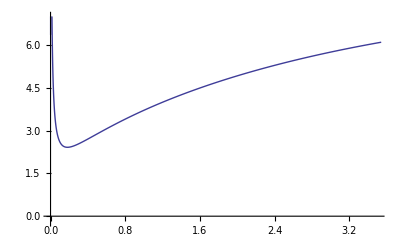

```mathematica
xm=0;
xM=3.5;
ym=-0.2;
yM=7.;
gr3LP=ListPlot[dataLP,Joined-> True,PlotRange-> {{xm,xM},{ym,yM}}]
```

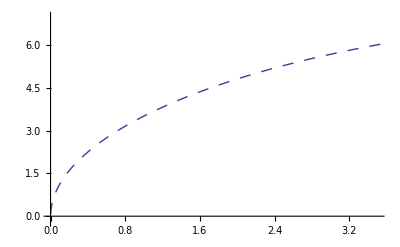

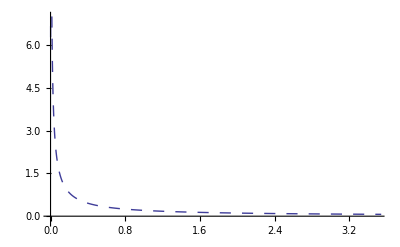

```mathematica
gr4E=ListPlot[dataLPE,Joined->True,PlotStyle->Dashing[{0.02,0.02}],PlotRange->{{xm,xM},{ym,yM}}]
gr4I=ListPlot[dataLPI,Joined->True,PlotStyle->Dashing[{0.02,0.02}],PlotRange->{{xm,xM},{ym,yM}}]
```

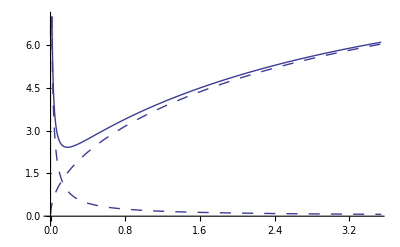

```mathematica
Show[gr3LP,gr4E,gr4I,PlotRange-> {{xm,xM},{ym,yM}}]
```

#### E vs x and range R

```mathematica
Clear[dxELP,ExLP, xELP]
```

```mathematica
dEdxELP=Interpolation[dataLP];
```

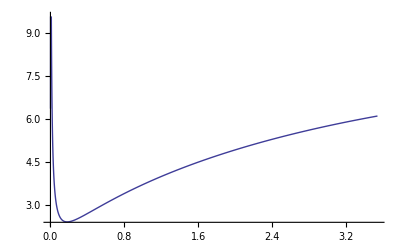

```mathematica
Plot[dEdxELP[e],{e,emin,emax}]
```

```mathematica
E0=emax;
dxELP[E_] :=1/dEdxELP[E]
xELP[E_]   := NIntegrate[1/dEdxELP[Ep],{Ep,E,E0},PrecisionGoal->Automatic]
```

```mathematica
FindRoot[dEdxELP[EE]==0,{EE,0.0.01}];
EzeroLPa=EE /. %
 FindRoot[dEdxELP[EE]==0,{EE, EzeroLPa}];
EzeroLP=EE /. %
dEdxELP[EzeroLP]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000349932} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

0.000433271

InterpolatingFunction::dmval: Input value {0.000433271} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

0.000433271

InterpolatingFunction::dmval: Input value {0.000433271} lies outside the range of data in the interpolating function. Extrapolation will be used.

2.00751×10^-15

```mathematica
eth=1.04*T/1000
dEdxELP[eth]
xELP[eth]
```

0.00104

6.65279

0.842828

```mathematica
NN=1000;
E1=eth;
dE=(E0-E1)/NN;
(*
dataExLP=Table[{xELP[E],E},{E,E1,emax,dE}]
*)
```

```mathematica
dataExLP={{0.8428283154384882,0.0010400000000000001},{0.8425392532352692,0.00457896},{0.842241336419498,0.00811792},{0.8418604003377942,0.01165688},{0.8413951871646239,0.015195839999999999},{0.8408509627910632,0.0187348},{0.8402338782613009,0.02227376},{0.8395496686722803,0.025812719999999997},{0.8388035105107606,0.029351679999999998},{0.8380000830676577,0.03289064},{0.8371436470620816,0.0364296},{0.8362381057982247,0.03996856},{0.8352870511907251,0.04350752},{0.8342938004829857,0.04704648},{0.8332614235419813,0.050585439999999995},{0.8321927664699593,0.054124399999999996},{0.8310904721606179,0.05766336},{0.8299569960419928,0.06120232},{0.8287946223893432,0.06474128},{0.827605477068154,0.06828023999999999},{0.826391538834894,0.0718192},{0.8251546524554063,0.07535816},{0.8238965361585244,0.07889712},{0.8226187925643988,0.08243608},{0.8213229164376461,0.08597504},{0.8200103017400998,0.089514},{0.818682250663924,0.09305295999999999},{0.8173399773683889,0.09659192},{0.8159846167427669,0.10013087999999999},{0.8146172292132527,0.10366984},{0.8132388033608838,0.10720879999999999},{0.8118502658853526,0.11074776},{0.81045248152442,0.11428672},{0.809046259187216,0.11782567999999999},{0.8076323554278539,0.12136464},{0.8062114779974309,0.12490359999999999},{0.8047842891392398,0.12844255999999998},{0.8033514086466984,0.13198152},{0.8019134167019534,0.13552048},{0.800470856511696,0.13905944},{0.7990242367554357,0.1425984},{0.7975740338602961,0.14613736},{0.7961206941153036,0.14967632},{0.7946646356371351,0.15321527999999998},{0.7932062501983774,0.15675424},{0.791745904928488,0.1602932},{0.7902839438968712,0.16383216},{0.7888206895867597,0.16737111999999998},{0.787356444267919,0.17091008},{0.7858914912755856,0.17444904},{0.7844260962024773,0.17798799999999998},{0.782960508010193,0.18152696},{0.7814949600658382,0.18506592},{0.7800296711092666,0.18860488},{0.7785648461559207,0.19214383999999998},{0.7771006773398744,0.1956828},{0.7756373447013358,0.19922176},{0.7741750169225428,0.20276072},{0.7727138520156938,0.20629967999999999},{0.7712539979662795,0.20983864},{0.7697955933349314,0.2133776},{0.7683387678206717,0.21691655999999998},{0.7668836427882327,0.22045552},{0.7654303317619229,0.22399448},{0.7639789408883247,0.22753344},{0.7625295693699546,0.23107239999999998},{0.7610823098718464,0.23461136},{0.7596372489028896,0.23815032},{0.7581944671736127,0.24168927999999998},{0.7567540399319833,0.24522824},{0.755316037278686,0.2487672},{0.7538805244636668,0.25230616},{0.7524475621675918,0.25584512},{0.751017206727568,0.25938408},{0.7495895104727627,0.26292304},{0.7481645218551964,0.266462},{0.7467422857337314,0.27000096},{0.7453228435416992,0.27353992},{0.7439062334862124,0.27707887999999997},{0.7424924907553105,0.28061784},{0.7410816476533965,0.2841568},{0.739673733778841,0.28769575999999997},{0.7382687761886321,0.29123472},{0.7368667995125917,0.29477368},{0.7354678261084387,0.29831263999999996},{0.7340718761915231,0.3018516},{0.73267896793492,0.30539056},{0.7312891176025857,0.30892952},{0.7299023396506016,0.31246848},{0.728518646817677,0.31600744},{0.7271380502376932,0.3195464},{0.7257605595182153,0.32308536},{0.7243861828240655,0.32662431999999997},{0.7230149269700785,0.33016328},{0.7216467974838668,0.33370224},{0.720281798681747,0.33724119999999996},{0.7189199337442352,0.34078016},{0.7175612047681452,0.34431912},{0.7162056128342369,0.34785807999999996},{0.7148531580680639,0.35139704},{0.713503839684843,0.354936},{0.7121576560487497,0.35847496},{0.7108146047214341,0.36201392},{0.709474682501984,0.36555287999999997},{0.7081378854781516,0.36909184},{0.7068042090645682,0.3726308},{0.7054736480393858,0.37616975999999996},{0.7041461965876763,0.37970872},{0.7028218483316351,0.38324768},{0.7015005963644554,0.38678663999999996},{0.700182433286277,0.3903256},{0.6988673512288782,0.39386456},{0.6975553418863939,0.39740352},{0.6962463965447621,0.40094248},{0.6949405061026172,0.40448143999999997},{0.6936376610986827,0.4080204},{0.692337851735596,0.41155936},{0.6910410678982181,0.41509831999999997},{0.6897472991776886,0.41863728},{0.6884565348904379,0.42217624},{0.6871687640947529,0.42571519999999996},{0.685883975611586,0.42925416},{0.6846021580395076,0.43279312},{0.6833232997701086,0.43633207999999996},{0.6820473890055355,0.43987104},{0.6807744137704694,0.44340999999999997},{0.6795043619263249,0.44694896},{0.6782372211857691,0.45048792},{0.6769729791226343,0.45402687999999997},{0.6757116231847721,0.45756584},{0.6744531407059036,0.4611048},{0.6731975189141185,0.46464375999999996},{0.6719447449433176,0.46818272},{0.6706948058427281,0.47172168},{0.6694476885844558,0.47526063999999996},{0.6682033800735089,0.4787996},{0.66696186715529,0.48233855999999997},{0.6657231366225363,0.48587751999999995},{0.6644871752239209,0.48941648},{0.6632539696698871,0.49295543999999997},{0.6620235066391427,0.4964944},{0.6607957727858237,0.50003336},{0.6595707547441664,0.50357232},{0.6583484391344686,0.5071112799999999},{0.6571288125689504,0.51065024},{0.6559118616556243,0.5141892},{0.6546975730036635,0.51772816},{0.653485933228097,0.52126712},{0.6522769289531478,0.52480608},{0.6510705468169745,0.5283450399999999},{0.64986677347534,0.531884},{0.6486655956046085,0.53542296},{0.6474669999058535,0.53896192},{0.6462709731076328,0.54250088},{0.6450775019687852,0.5460398399999999},{0.643886573281874,0.5495787999999999},{0.6426981738752799,0.55311776},{0.6415122906158093,0.55665672},{0.6403289104114865,0.56019568},{0.6391480202131825,0.56373464},{0.637969607016984,0.5672735999999999},{0.6367936578663963,0.57081256},{0.6356201598536618,0.57435152},{0.6344491001218608,0.57789048},{0.633280465866585,0.58142944},{0.6321142443370614,0.5849683999999999},{0.6309504228379689,0.5885073599999999},{0.6297889887306416,0.59204632},{0.6286299294340842,0.59558528},{0.6274732324264914,0.59912424},{0.6263188852460533,0.6026632},{0.6251668754919125,0.6062021599999999},{0.6240171908253643,0.60974112},{0.6228698189703843,0.61328008},{0.6217247477145038,0.61681904},{0.6205819649097096,0.620358},{0.6194414584727886,0.62389696},{0.618303216386097,0.6274359199999999},{0.6171672266981866,0.63097488},{0.6160334775240366,0.63451384},{0.6149019570457013,0.6380528},{0.6137726535126905,0.64159176},{0.6126455552421398,0.6451307199999999},{0.6115206506193289,0.64866968},{0.6103979280978427,0.65220864},{0.6092773761997211,0.6557476},{0.6081589835158316,0.65928656},{0.6070427387058619,0.66282552},{0.6059286304984549,0.6663644799999999},{0.6048166476914308,0.66990344},{0.6037067791516698,0.6734424},{0.6025990138152156,0.67698136},{0.6014933406873579,0.68052032},{0.6003897488424486,0.6840592799999999},{0.5992882274239616,0.6875982399999999},{0.5981887656444475,0.6911372},{0.5970913527853167,0.69467616},{0.5959959781968469,0.69821512},{0.5949026312980228,0.70175408},{0.593811301576311,0.7052930399999999},{0.5927219785876076,0.708832},{0.5916346519559802,0.71237096},{0.5905493113734503,0.71590992},{0.5894659465998704,0.71944888},{0.5883845474626003,0.7229878399999999},{0.5873051038562904,0.7265267999999999},{0.5862276057426901,0.73006576},{0.5851520431502862,0.73360472},{0.5840784061740778,0.73714368},{0.58300668497532,0.74068264},{0.5819368697811472,0.7442215999999999},{0.5808689508843302,0.74776056},{0.5798029186429648,0.75129952},{0.5787387634800911,0.75483848},{0.5776764758834324,0.75837744},{0.5766160464050313,0.7619163999999999},{0.5755574656608802,0.7654553599999999},{0.5745007243306328,0.76899432},{0.5734458131572034,0.77253328},{0.5723927229464086,0.77607224},{0.5713414445666495,0.7796112},{0.5702919689484891,0.7831501599999999},{0.569244287084302,0.78668912},{0.5681983900279268,0.79022808},{0.5671542688942369,0.79376704},{0.5661119148587905,0.797306},{0.5650713191574578,0.8008449599999999},{0.5640324730859936,0.8043839199999999},{0.5629953679996852,0.80792288},{0.5619599953129568,0.81146184},{0.560926346498951,0.8150008},{0.5598944130891721,0.81853976},{0.5588641866730704,0.8220787199999999},{0.557835658897639,0.8256176799999999},{0.5568088214670472,0.82915664},{0.5557836661422151,0.8326956},{0.5547601847404218,0.83623456},{0.5537383691349296,0.8397735199999999},{0.5527182112545559,0.8433124799999999},{0.5516997030832915,0.84685144},{0.550682836659914,0.8503904},{0.5496676040775654,0.85392936},{0.548653997483375,0.85746832},{0.5476420090780661,0.8610072799999999},{0.5466316311155421,0.8645462399999999},{0.5456228559025132,0.8680852},{0.5446156757980966,0.87162416},{0.5436100832134148,0.87516312},{0.5426060706112243,0.8787020799999999},{0.5416036305055124,0.8822410399999999},{0.5406027554611084,0.88578},{0.5396034380933119,0.88931896},{0.5386056710674919,0.89285792},{0.5376094470987088,0.89639688},{0.5366147589513421,0.8999358399999999},{0.5356215994386954,0.9034747999999999},{0.5346299614226272,0.90701376},{0.5336398378131794,0.91055272},{0.5326512215681896,0.91409168},{0.5316641056929305,0.9176306399999999},{0.5306784832397383,0.9211695999999999},{0.5296943473076361,0.92470856},{0.5287116910419789,0.92824752},{0.5277305076340838,0.93178648},{0.5267507903208658,0.93532544},{0.5257725323844862,0.9388643999999999},{0.524795727151988,0.9424033599999999},{0.5238203679949416,0.94594232},{0.5228464483290983,0.94948128},{0.5218739616140314,0.95302024},{0.5209029013527918,0.9565591999999999},{0.519933261091565,0.9600981599999999},{0.5189650344193213,0.96363712},{0.5179982149674787,0.96717608},{0.5170327964095652,0.97071504},{0.5160687724608777,0.974254},{0.5151061368781523,0.9777929599999999},{0.5141448834592318,0.9813319199999999},{0.5131850060427338,0.98487088},{0.5122264985077282,0.98840984},{0.5112693547734098,0.9919488},{0.5103135687987767,0.9954877599999999},{0.5093591345823132,0.9990267199999999},{0.5084060461616696,1.00256568},{0.5074542976133494,1.00610464},{0.5065038830523979,1.0096436},{0.5055547966320904,1.01318256},{0.5046070325436257,1.01672152},{0.5036605850158233,1.02026048},{0.5027154483148176,1.02379944},{0.50177161674376,1.0273383999999999},{0.5008290846425216,1.0308773599999999},{0.49988784638739614,1.03441632},{0.49894789639080933,1.03795528},{0.49800922910102724,1.04149424},{0.49707183900186824,1.0450332},{0.49613572061241845,1.04857216},{0.4952008684867472,1.05211112},{0.494267277213627,1.05565008},{0.49333494141625467,1.05918904},{0.4924038557519752,1.062728},{0.49147401491200776,1.0662669599999999},{0.4905454136211744,1.0698059199999999},{0.48961804663763026,1.07334488},{0.48869190875259744,1.07688384},{0.4877669947900994,1.0804228},{0.48684329960669903,1.08396176},{0.48592081809123844,1.08750072},{0.48499954516458077,1.09103968},{0.48407947577935484,1.09457864},{0.48316060491970125,1.0981176},{0.4822429276010213,1.10165656},{0.4813264388697279,1.1051955199999999},{0.4804111338029983,1.1087344799999999},{0.47949700750852964,1.11227344},{0.47858405512429647,1.1158124},{0.477672271818309,1.11935136},{0.4767616527883764,1.12289032},{0.47585219326186934,1.12642928},{0.47494388849548547,1.12996824},{0.4740367337750185,1.1335072},{0.4731307244151269,1.13704616},{0.4722258557591058,1.14058512},{0.4713221231786621,1.1441240799999999},{0.4704195220736889,1.1476630399999999},{0.46951804787204376,1.151202},{0.4686176960293298,1.15474096},{0.4677184620286754,1.15827992},{0.4668203413805196,1.16181888},{0.46592332962239763,1.16535784},{0.46502742231872707,1.1688968},{0.4641326150605993,1.17243576},{0.46323890346556984,1.17597472},{0.4623462831774508,1.17951368},{0.4614547498661078,1.1830526399999999},{0.4605642992272556,1.1865915999999999},{0.4596749269822563,1.19013056},{0.45878662887792193,1.19366952},{0.4578994006863145,1.19720848},{0.45701323820455086,1.20074744},{0.4561281372546095,1.2042864},{0.4552440936831365,1.20782536},{0.45436110336125546,1.21136432},{0.4534791621843796,1.21490328},{0.452598266072022,1.21844224},{0.4517184109676122,1.2219811999999999},{0.4508395928383117,1.2255201599999999},{0.44996180767483,1.2290591199999998},{0.4490850514912464,1.23259808},{0.44820932032482963,1.23613704},{0.44733461023585924,1.239676},{0.4464609173074524,1.24321496},{0.4455882376453875,1.24675392},{0.44471656737793125,1.25029288},{0.4438459026556695,1.25383184},{0.4429762396513354,1.2573708},{0.44210757455964184,1.2609097599999999},{0.44123990359711623,1.2644487199999999},{0.44037322300193277,1.2679876799999998},{0.4395075290337506,1.27152664},{0.4386428179735519,1.2750656},{0.43777908612347877,1.27860456},{0.4369163298066763,1.28214352},{0.4360545453671341,1.28568248},{0.43519372916952803,1.28922144},{0.4343338775990678,1.2927604},{0.4334749870613414,1.29629936},{0.4326170539821625,1.2998383199999999},{0.43176007480742123,1.3033772799999999},{0.4309040460029329,1.3069162399999998},{0.43004896405428933,1.3104552},{0.4291948254667141,1.31399416},{0.4283416267649142,1.31753312},{0.42748936449293673,1.32107208},{0.4266380352140267,1.32461104},{0.4257876355104829,1.32815},{0.424938161983519,1.33168896},{0.4240896112531245,1.33522792},{0.4232419799579241,1.3387668799999999},{0.42239526475504363,1.3423058399999999},{0.42154946231997314,1.3458447999999998},{0.4207045693464311,1.34938376},{0.41986058254623354,1.35292272},{0.4190174986491603,1.35646168},{0.4181753144028233,1.36000064},{0.4173340265725391,1.3635396},{0.41649363194119793,1.36707856},{0.4156541273091365,1.37061752},{0.4148155094940131,1.37415648},{0.41397777533067986,1.3776954399999999},{0.41314092167106004,1.3812343999999999},{0.41230494538402507,1.3847733599999998},{0.4114698433552706,1.38831232},{0.4106356124871975,1.39185128},{0.4098022496987912,1.39539024},{0.4089697519255014,1.3989292},{0.40813811611912637,1.40246816},{0.40730733924769497,1.40600712},{0.4064774182953496,1.40954608},{0.40564835026223395,1.41308504},{0.40482013216437696,1.4166239999999999},{0.40399276103358006,1.4201629599999999},{0.40316623391730716,1.4237019199999998},{0.4023405478785712,1.42724088},{0.4015156999958255,1.43077984},{0.40069168736285526,1.4343188},{0.39986850708866745,1.43785776},{0.39904615629738555,1.44139672},{0.3982246321281431,1.44493568},{0.39740393173497646,1.44847464},{0.3965840522867227,1.4520136},{0.3957649909669154,1.4555525599999999},{0.3949467449736804,1.4590915199999999},{0.3941293115196362,1.4626304799999998},{0.3933126878317921,1.46616944},{0.3924968711514472,1.4697084},{0.39168185873409334,1.47324736},{0.3908676478493147,1.47678632},{0.39005423578069065,1.48032528},{0.3892416198257007,1.48386424},{0.38842979729562604,1.4874032},{0.38761876551545615,1.49094216},{0.3868085218237947,1.4944811199999999},{0.3859990635727645,1.4980200799999999},{0.3851903881279162,1.5015590399999998},{0.3843824928681364,1.5050979999999998},{0.38357537518555496,1.50863696},{0.38276903248545674,1.51217592},{0.3819634621861907,1.51571488},{0.3811586617190806,1.51925384},{0.3803546285283383,1.5227928},{0.37955136007097556,1.52633176},{0.37874885381671664,1.52987072},{0.37794710724791425,1.5334096799999999},{0.37714611785946245,1.5369486399999999},{0.37634588315871287,1.5404875999999998},{0.3755464006653917,1.5440265599999998},{0.3747476679115147,1.54756552},{0.37394968244130655,1.55110448},{0.37315244181111873,1.55464344},{0.372355943589347,1.5581824},{0.371560185356353,1.56172136},{0.37076516470438375,1.56526032},{0.3699708792374914,1.56879928},{0.36917732657145685,1.5723382399999999},{0.3683845043337108,1.5758771999999999},{0.3675924101632559,1.5794161599999998},{0.366801041710592,1.5829551199999998},{0.36601039663763907,1.58649408},{0.36522047261766144,1.59003304},{0.364431267335195,1.593572},{0.36364277848597104,1.59711096},{0.3628550037768439,1.60064992},{0.3620679409257186,1.60418888},{0.36128158766147694,1.60772784},{0.36049594172390736,1.6112667999999999},{0.3597110008636336,1.6148057599999999},{0.3589267628420428,1.6183447199999998},{0.35814322543121735,1.6218836799999998},{0.3573603864138649,1.62542264},{0.3565782435832485,1.6289616},{0.35579679474312,1.63250056},{0.35501603770765117,1.63603952},{0.35423597030136633,1.63957848},{0.353456590359077,1.64311744},{0.3526778957258145,1.6466564},{0.35189988425676444,1.6501953599999999},{0.35112255381720303,1.6537343199999999},{0.3503459022824304,1.6572732799999998},{0.34956992753770816,1.6608122399999998},{0.34879462747819573,1.6643512},{0.3480200000088861,1.66789016},{0.34724604304454476,1.67142912},{0.3464727545096472,1.67496808},{0.34570013233831637,1.67850704},{0.3449281744742633,1.682046},{0.34415687887072555,1.68558496},{0.3433862434904066,1.68912392},{0.34261626630541764,1.6926628799999999},{0.34184694529721743,1.6962018399999998},{0.34107827845655314,1.6997407999999998},{0.3403102637834038,1.70327976},{0.33954289928692083,1.70681872},{0.33877618298537115,1.71035768},{0.33801011290608135,1.71389664},{0.3372446870853794,1.7174356},{0.3364799035685401,1.72097456},{0.3357157604097293,1.72451352},{0.33495225567194775,1.72805248},{0.3341893874269777,1.7315914399999999},{0.3334271537553281,1.7351303999999999},{0.3326655527461799,1.7386693599999998},{0.3319045824973341,1.74220832},{0.33114424111515794,1.74574728},{0.33038452671453145,1.74928624},{0.32962543741879696,1.7528252},{0.32886697135970583,1.75636416},{0.32810912667736736,1.75990312},{0.32735190152019844,1.76344208},{0.3265952940448718,1.76698104},{0.3258393024162664,1.7705199999999999},{0.3250839248074178,1.7740589599999999},{0.32432915939946766,1.7775979199999998},{0.3235750043816154,1.78113688},{0.32282145795106987,1.78467584},{0.3220685183129992,1.7882148},{0.3213161836804848,1.79175376},{0.32056445227447267,1.79529272},{0.31981332232372567,1.79883168},{0.3190627920647777,1.80237064},{0.31831285974188656,1.8059096},{0.317563523606987,1.8094485599999999},{0.3168147819196463,1.8129875199999999},{0.31606663294701737,1.8165264799999998},{0.31531907496379413,1.8200654399999998},{0.31457210625216697,1.8236044},{0.31382572510177725,1.82714336},{0.3130799298096738,1.83068232},{0.3123347186802694,1.83422128},{0.31159009002529575,1.83776024},{0.3108460421637618,1.8412992},{0.3101025734219104,1.84483816},{0.3093596821331747,1.8483771199999999},{0.30861736663813755,1.8519160799999999},{0.30787562528448825,1.8554550399999998},{0.30713445642698106,1.8589939999999998},{0.3063938584273946,1.86253296},{0.30565382965449006,1.86607192},{0.30491436848397035,1.86961088},{0.3041754732984406,1.87314984},{0.30343714248736664,1.8766888},{0.3026993744470363,1.88022776},{0.3019621675805195,1.88376672},{0.3012255202976284,1.8873056799999999},{0.30048943101487907,1.8908446399999999},{0.2997538981554529,1.8943835999999998},{0.2990189201491571,1.8979225599999998},{0.2982844954323878,1.90146152},{0.2975506224480917,1.90500048},{0.2968172996457278,1.90853944},{0.29608452548123126,1.9120784},{0.2953522984169756,1.91561736},{0.2946206169217355,1.91915632},{0.29388947947065164,1.92269528},{0.29315888454519284,1.9262342399999999},{0.29242883063312103,1.9297731999999999},{0.29169931622845546,1.9333121599999998},{0.29097033983143655,1.9368511199999998},{0.2902418999484912,1.94039008},{0.2895139950921981,1.94392904},{0.2887866237812518,1.947468},{0.2880597845404293,1.95100696},{0.28733347590055575,1.95454592},{0.28660769639846934,1.95808488},{0.2858824445769889,1.96162384},{0.28515771898487985,1.9651627999999999},{0.2844335181768202,1.9687017599999999},{0.2837098407133687,1.9722407199999998},{0.28298668516093123,1.9757796799999998},{0.28226405009172795,1.97931864},{0.2815419340837622,1.9828576},{0.28082033572078685,1.98639656},{0.2800992535922731,1.98993552},{0.27937868629337914,1.99347448},{0.2786586324249177,1.99701344},{0.27793909059332556,2.0005524},{0.27722005941063277,2.00409136},{0.27650153749443035,2.00763032},{0.27578352346784163,2.01116928},{0.27506601595949054,2.01470824},{0.2743490136034716,2.0182472},{0.2736325150393203,2.02178616},{0.27291651891198343,2.0253251199999998},{0.2722010238717886,2.02886408},{0.27148602857441634,2.0324030399999997},{0.2707715316808693,2.035942},{0.2700575318574445,2.03948096},{0.26934402777570454,2.04301992},{0.2686310181124479,2.04655888},{0.26791850154968183,2.05009784},{0.2672064767745937,2.0536368},{0.26649494247952277,2.05717576},{0.26578389736193264,2.06071472},{0.2650733401243841,2.0642536799999998},{0.26436326947450645,2.06779264},{0.26365368412497175,2.0713315999999997},{0.2629445827934669,2.07487056},{0.2622359642026666,2.07840952},{0.2615278270802077,2.08194848},{0.26082017015866155,2.08548744},{0.2601129921755082,2.0890264},{0.25940629187311043,2.09256536},{0.25870006799868756,2.09610432},{0.2579943193042892,2.09964328},{0.2572890445467708,2.1031822399999998},{0.2565842424877669,2.1067212},{0.25587991189366677,2.1102601599999997},{0.25517605153558887,2.11379912},{0.2544726601893558,2.11733808},{0.25376973663547026,2.12087704},{0.2530672796590893,2.124416},{0.2523652880500008,2.12795496},{0.2516637606025987,2.13149392},{0.25096269611585925,2.13503288},{0.25026209339331634,2.13857184},{0.24956195124303887,2.1421107999999998},{0.24886226847760573,2.14564976},{0.24816304391408328,2.1491887199999997},{0.2474642763740017,2.15272768},{0.24676596468333167,2.15626664},{0.24606810767246165,2.1598056},{0.24537070417617465,2.16334456},{0.24467375303362568,2.16688352},{0.24397725308831902,2.17042248},{0.24328120318808635,2.17396144},{0.24258560218506325,2.1775004},{0.2418904489356685,2.1810393599999998},{0.24119574230058105,2.18457832},{0.24050148114471845,2.1881172799999997},{0.23980766433721526,2.19165624},{0.23911429075140148,2.1951952},{0.2384213592647808,2.19873416},{0.23772886875900967,2.20227312},{0.237036818119876,2.20581208},{0.23634520623727778,2.20935104},{0.23565403200520313,2.21289},{0.2349632943217083,2.21642896},{0.23427299208889804,2.2199679199999998},{0.23358312421290475,2.22350688},{0.23289368960386794,2.2270458399999997},{0.23220468717591425,2.2305848},{0.23151611584713747,2.23412376},{0.23082797453957807,2.23766272},{0.23014026217920378,2.24120168},{0.22945297769589001,2.24474064},{0.22876612002339938,2.2482796},{0.22807968809936358,2.25181856},{0.22739368086526277,2.25535752},{0.22670809726640717,2.2588964799999998},{0.22602293625191763,2.26243544},{0.22533819677470676,2.2659743999999997},{0.22465387779145968,2.26951336},{0.22396997826261625,2.2730523199999997},{0.22328649715235108,2.27659128},{0.2226034334285562,2.28013024},{0.22192078606282234,2.2836692},{0.22123855403041987,2.28720816},{0.220556736310282,2.29074712},{0.21987533188498568,2.29428608},{0.21919433974073396,2.2978250399999998},{0.21851375886733831,2.301364},{0.21783358825820104,2.3049029599999997},{0.21715382691029686,2.30844192},{0.21647447382415666,2.3119808799999997},{0.215795528003849,2.31551984},{0.2151169884569634,2.3190588},{0.2144388541945933,2.32259776},{0.21376112423131832,2.32613672},{0.21308379758518803,2.32967568},{0.21240687327770474,2.33321464},{0.21173035033380677,2.3367535999999998},{0.21105422778185168,2.34029256},{0.21037850465360033,2.3438315199999997},{0.20970317998419932,2.34737048},{0.20902825281216594,2.3509094399999997},{0.2083537221793709,2.3544484},{0.2076795871310226,2.35798736},{0.2070058467156514,2.36152632},{0.20633249998509287,2.36506528},{0.20565954599447267,2.36860424},{0.2049869838021904,2.3721432},{0.2043148124699043,2.3756821599999998},{0.20364303106251497,2.37922112},{0.20297163864815101,2.3827600799999997},{0.2023006342981524,2.38629904},{0.20163001708705622,2.3898379999999997},{0.20095978609258094,2.39337696},{0.20028994039561132,2.39691592},{0.19962047908018382,2.40045488},{0.19895140123347113,2.40399384},{0.19828270594576763,2.4075328},{0.1976143923104746,2.41107176},{0.1969464594240858,2.4146107199999998},{0.19627890638617226,2.41814968},{0.19561173229936873,2.4216886399999997},{0.1949449362693583,2.4252276},{0.1942785174048589,2.4287665599999997},{0.19361247481760863,2.43230552},{0.19294680762235175,2.43584448},{0.1922815149368247,2.43938344},{0.19161659588174196,2.4429224},{0.19095204958078232,2.44646136},{0.1902878751605749,2.45000032},{0.1896240717506859,2.4535392799999998},{0.18896063848360403,2.45707824},{0.18829757449472803,2.4606171999999997},{0.1876348789223524,2.46415616},{0.18697255090765436,2.4676951199999997},{0.18631058959468041,2.47123408},{0.1856489941303332,2.47477304},{0.1849877636643582,2.478312},{0.1843268973493307,2.48185096},{0.18366639434064286,2.48538992},{0.18300625379649038,2.48892888},{0.18234647487786054,2.4924678399999998},{0.18168705674851818,2.4960068},{0.18102799857499408,2.4995457599999997},{0.18036929952657166,2.50308472},{0.1797109587752747,2.5066236799999997},{0.17905297549585467,2.51016264},{0.1783953488657786,2.5137016},{0.17773807806521635,2.51724056},{0.17708116227702853,2.52077952},{0.1764246006867545,2.52431848},{0.1757683924825996,2.52785744},{0.175112536855424,2.5313963999999998},{0.17445703299872975,2.53493536},{0.17380188010864958,2.5384743199999997},{0.17314707738393462,2.54201328},{0.17249262402594287,2.5455522399999997},{0.17183851923862709,2.5490912},{0.17118476222852375,2.55263016},{0.1705313522047409,2.55616912},{0.16987828837894664,2.55970808},{0.1692255699653584,2.56324704},{0.1685731961807303,2.566786},{0.1679211662443431,2.5703249599999998},{0.16726947937799203,2.57386392},{0.16661813480597598,2.5774028799999997},{0.16596713175508623,2.58094184},{0.16531646945459566,2.5844807999999997},{0.1646661471362471,2.58801976},{0.1640161640342432,2.59155872},{0.163366519385235,2.59509768},{0.1627172124283109,2.59863664},{0.1620682424049868,2.6021756},{0.16141960855919424,2.60571456},{0.16077131013727075,2.6092535199999998},{0.1601233463879486,2.61279248},{0.15947571656234455,2.6163314399999997},{0.15882841991394933,2.6198704},{0.1581814556986174,2.6234093599999997},{0.15753482317455608,2.62694832},{0.15688852160231592,2.63048728},{0.15624255024478018,2.63402624},{0.15559690836715415,2.6375652},{0.15495159523695612,2.64110416},{0.1543066101240062,2.64464312},{0.15366195230041702,2.6481820799999998},{0.15301762104058342,2.65172104},{0.15237361562117283,2.6552599999999997},{0.15172993532111492,2.65879896},{0.1510865794215927,2.6623379199999997},{0.15044354720603156,2.66587688},{0.1498008379600907,2.66941584},{0.14915845097165306,2.6729548},{0.1485163855308153,2.67649376},{0.1478746409298792,2.68003272},{0.1472332164633413,2.68357168},{0.14659211142788406,2.6871106399999998},{0.14595132512236605,2.6906496},{0.14531085684781328,2.6941885599999997},{0.1446707059074089,2.69772752},{0.1440308716064852,2.7012664799999997},{0.14339135325251334,2.70480544},{0.14275215015509496,2.7083444},{0.14211326162595292,2.71188336},{0.14147468697892188,2.71542232},{0.14083642552994005,2.71896128},{0.14019847659703963,2.72250024},{0.1395608395003383,2.7260391999999998},{0.13892351356203012,2.72957816},{0.1382864981063772,2.7331171199999997},{0.13764979245970024,2.73665608},{0.13701339595037068,2.7401950399999997},{0.13637730790880134,2.743734},{0.13574152766743827,2.74727296},{0.13510605456075214,2.75081192},{0.13447088792522946,2.75435088},{0.13383602709936449,2.75788984},{0.13320147142365052,2.7614288},{0.13256722024057183,2.7649677599999998},{0.1319332728945949,2.76850672},{0.13129962873216075,2.7720456799999997},{0.130666287101676,2.77558464},{0.13003324735350538,2.7791235999999997},{0.12940050883996304,2.78266256},{0.12876807091530462,2.78620152},{0.1281359329357195,2.78974048},{0.12750409425932216,2.79327944},{0.12687255424614474,2.7968184},{0.1262413122581288,2.80035736},{0.1256103676591177,2.8038963199999998},{0.12497971981484829,2.80743528},{0.1243493680929438,2.8109742399999997},{0.12371931186290525,2.8145132},{0.12308955049610443,2.8180521599999997},{0.12246008336577573,2.82159112},{0.1218309098470088,2.82513008},{0.12120202931674083,2.82866904},{0.12057344115374884,2.832208},{0.11994514473864243,2.83574696},{0.11931713945385596,2.83928592},{0.11868942468364158,2.8428248799999998},{0.1180619998140611,2.84636384},{0.1174348642329795,2.8499027999999997},{0.11680801733005675,2.85344176},{0.11618145849674112,2.8569807199999997},{0.11555518712626155,2.86051968},{0.11492920261362077,2.8640586399999997},{0.11430350435558759,2.8675976},{0.11367809175069042,2.87113656},{0.11305296419920972,2.87467552},{0.11242812110317078,2.87821448},{0.11180356186633736,2.8817534399999998},{0.11117928589420378,2.8852924},{0.11055529259398882,2.8888313599999997},{0.10993158137462813,2.89237032},{0.1093081516467678,2.8959092799999997},{0.10868500282275706,2.89944824},{0.10806213431664205,2.9029871999999997},{0.10743954554415823,2.90652616},{0.10681723592272442,2.91006512},{0.10619520487143572,2.91360408},{0.10557345181105648,2.91714304},{0.10495197616401451,2.920682},{0.10433077735439349,2.92422096},{0.10370985480792715,2.9277599199999997},{0.10308920795199221,2.93129888},{0.1024688362156023,2.9348378399999997},{0.10184873902940088,2.9383768},{0.10122891582565559,2.9419157599999997},{0.10060936603825095,2.94545472},{0.09999008910268264,2.94899368},{0.09937108445605106,2.95253264},{0.09875235153705438,2.9560716},{0.0981338897859832,2.95961056},{0.09751569864471347,2.96314952},{0.09689777755670084,2.9666884799999997},{0.096280125966974,2.97022744},{0.09566274332212898,2.9737663999999997},{0.09504562907032245,2.97730536},{0.09442878266126628,2.9808443199999997},{0.09381220354622079,2.98438328},{0.09319589117798917,2.98792224},{0.09257984501091147,2.9914612},{0.09196406450085813,2.99500016},{0.09134854910522465,2.99853912},{0.09073329828292517,3.00207808},{0.09011831149438695,3.0056170399999997},{0.08950358820154408,3.009156},{0.08888912786783223,3.0126949599999997},{0.0882749299581821,3.01623392},{0.08766099393901439,3.0197728799999997},{0.08704731927823342,3.02331184},{0.08643390544522178,3.0268508},{0.08582075191083466,3.03038976},{0.08520785814739376,3.03392872},{0.0845952236286822,3.03746768},{0.08398284782993845,3.04100664},{0.08337073022785113,3.0445455999999997},{0.08275887030055297,3.04808456},{0.08214726752761596,3.0516235199999997},{0.08153592139004502,3.05516248},{0.08092483137027334,3.0587014399999997},{0.08031399695215627,3.0622404},{0.07970341762096625,3.06577936},{0.07909309286338746,3.06931832},{0.0784830221675101,3.07285728},{0.07787320502282541,3.07639624},{0.07726364092022006,3.0799352},{0.07665432935197126,3.0834741599999997},{0.07604526981174083,3.08701312},{0.07543646179457077,3.0905520799999997},{0.07482790479687727,3.09409104},{0.07421959831644616,3.0976299999999997},{0.07361154185242721,3.10116896},{0.07300373490532938,3.10470792},{0.07239617697701559,3.10824688},{0.07178886757069738,3.11178584},{0.07118180619093031,3.1153248},{0.07057499234360835,3.11886376},{0.06996842553595954,3.1224027199999997},{0.06936210527654019,3.12594168},{0.06875603107523069,3.1294806399999997},{0.06815020244322997,3.1330196},{0.06754461889305095,3.1365585599999997},{0.06693927993851534,3.14009752},{0.06633418509474905,3.14363648},{0.0657293338781772,3.14717544},{0.06512472580651912,3.1507144},{0.06452036039878395,3.15425336},{0.06391623717526526,3.15779232},{0.06331235565753708,3.1613312799999997},{0.06270871536844824,3.16487024},{0.06210531583211849,3.1684091999999997},{0.06150215657393319,3.17194816},{0.06089923712053905,3.1754871199999997},{0.06029655699983909,3.17902608},{0.05969411574098844,3.18256504},{0.05909191287438945,3.186104},{0.058489947931687,3.18964296},{0.05788822044576438,3.19318192},{0.057286729950738094,3.19672088},{0.05668547598195411,3.2002598399999997},{0.05608445807598257,3.2037988},{0.055483675770613985,3.2073377599999997},{0.05488312860485424,3.21087672},{0.05428281611892061,3.2144156799999997},{0.053682737854236835,3.21795464},{0.053082893353429306,3.2214936},{0.05248328216032227,3.22503256},{0.051883903819933415,3.22857152},{0.051284757878470054,3.23211048},{0.05068584388332403,3.23564944},{0.05008716138306827,3.2391883999999997},{0.04948870992745174,3.24272736},{0.04889048906739575,3.2462663199999997},{0.04829249835498932,3.24980528},{0.04769473734348535,3.2533442399999997},{0.0470972055872959,3.2568832},{0.046499902641988604,3.26042216},{0.04590282806428214,3.26396112},{0.04530598141204197,3.26750008},{0.044709362244276754,3.27103904},{0.04411297012113352,3.274578},{0.04351680460389431,3.2781169599999997},{0.042920865254971505,3.28165592},{0.04232515163790423,3.2851948799999997},{0.041729663317353914,3.28873384},{0.041134399859100806,3.2922727999999997},{0.040539360830039284,3.29581176},{0.03994454579817457,3.29935072},{0.03934995433261847,3.30288968},{0.03875558600358512,3.30642864},{0.03816144038238779,3.3099676},{0.03756751704143423,3.31350656},{0.036973815554223376,3.3170455199999997},{0.03638033549534102,3.32058448},{0.03578707644045639,3.3241234399999997},{0.035194037966317815,3.3276624},{0.03460121965074956,3.3312013599999997},{0.034008621072647245,3.33474032},{0.033416241811974765,3.33827928},{0.03282408144976027,3.34181824},{0.03223213956809206,3.3453572},{0.03164041575011556,3.34889616},{0.031048909580028917,3.35243512},{0.030457620643079844,3.3559740799999997},{0.029866548525561483,3.35951304},{0.02927569281480923,3.3630519999999997},{0.028685053099196476,3.36659096},{0.0280946289681317,3.3701299199999997},{0.02750442001205411,3.37366888},{0.026914425822430615,3.37720784},{0.026324645991752115,3.3807468},{0.02573508011352953,3.38428576},{0.0251457277822909,3.38782472},{0.024556588593577258,3.39136368},{0.02396766214393959,3.3949026399999997},{0.023378948030934855,3.3984416},{0.02279044585312307,3.4019805599999997},{0.02220215521006314,3.40551952},{0.02161407570231014,3.4090584799999997},{0.0210262069314112,3.41259744},{0.020438548499902547,3.4161364},{0.019851100011306005,3.41967536},{0.01926386107012526,3.42321432},{0.018676831281843,3.42675328},{0.018090010252917066,3.43029224},{0.017503397590777545,3.4338311999999998},{0.01691699290382291,3.43737016},{0.016330795801417348,3.4409091199999997},{0.015744805893886705,3.44444808},{0.01515902279251592,3.4479870399999997},{0.014573446109545135,3.451526},{0.013988075458166837,3.45506496},{0.013402910452522523,3.45860392},{0.012817950707699189,3.46214288},{0.01223319583972654,3.46568184},{0.01164864546557335,3.4692208},{0.011064299203144735,3.4727597599999998},{0.01048015667127838,3.47629872},{0.009896217489742067,3.4798376799999997},{0.009312481279229816,3.48337664},{0.008728947661359362,3.4869155999999997},{0.008145616258668519,3.49045456},{0.007562486694612523,3.4939935199999996},{0.006979558593560432,3.49753248},{0.006396831580792573,3.50107144},{0.005814305282497132,3.5046104},{0.005231979325766999,3.50814936},{0.004649853338597198,3.5116883199999998},{0.004067926949881181,3.51522728},{0.0034861997894085296,3.5187662399999997},{0.0029046714878612884,3.5223052},{0.0023233416768115023,3.5258441599999997},{0.001742209988717782,3.52938312},{0.0011612760569228112,3.5329220799999996},{0.0005805395156497635,3.53646104},{0.,3.54}};
```

```mathematica
xy1=dataExLP[[2]]
xy2=dataExLP[[1]]
dxy=xy2-xy1
m=dxy[[2]]/dxy[[1]]
b=xy1[[2]]-m*xy1[[1]]
xRLP=-b/m
```

{0.842539,0.00457896}

{0.842828,0.00104}

{0.000289062,-0.00353896}

-12.2429

10.3197

0.842913

```mathematica
dataExLP=Prepend[dataExLP,{xRLP,0}]
```

{{0.842913,0},{0.842828,0.00104},{0.842539,0.00457896},{0.842241,0.00811792},{0.84186,0.0116569},{0.841395,0.0151958},{0.840851,0.0187348},{0.840234,0.0222738},{0.83955,0.0258127},{0.838804,0.0293517},{0.838,0.0328906},{0.837144,0.0364296},{0.836238,0.0399686},{0.835287,0.0435075},{0.834294,0.0470465},{0.833261,0.0505854},{0.832193,0.0541244},{0.83109,0.0576634},{0.829957,0.0612023},{0.828795,0.0647413},{0.827605,0.0682802},{0.826392,0.0718192},{0.825155,0.0753582},{0.823897,0.0788971},{0.822619,0.0824361},{0.821323,0.085975},{0.82001,0.089514},{0.818682,0.093053},{0.81734,0.0965919},{0.815985,0.100131},{0.814617,0.10367},{0.813239,0.107209},{0.81185,0.110748},{0.810452,0.114287},{0.809046,0.117826},{0.807632,0.121365},{0.806211,0.124904},{0.804784,0.128443},{0.803351,0.131982},{0.801913,0.13552},{0.800471,0.139059},{0.799024,0.142598},{0.797574,0.146137},{0.796121,0.149676},{0.794665,0.153215},{0.793206,0.156754},{0.791746,0.160293},{0.790284,0.163832},{0.788821,0.167371},{0.787356,0.17091},{0.785891,0.174449},{0.784426,0.177988},{0.782961,0.181527},{0.781495,0.185066},{0.78003,0.188605},{0.778565,0.192144},{0.777101,0.195683},{0.775637,0.199222},{0.774175,0.202761},{0.772714,0.2063},{0.771254,0.209839},{0.769796,0.213378},{0.768339,0.216917},{0.766884,0.220456},{0.76543,0.223994},{0.763979,0.227533},{0.76253,0.231072},{0.761082,0.234611},{0.759637,0.23815},{0.758194,0.241689},{0.756754,0.245228},{0.755316,0.248767},{0.753881,0.252306},{0.752448,0.255845},{0.751017,0.259384},{0.74959,0.262923},{0.748165,0.266462},{0.746742,0.270001},{0.745323,0.27354},{0.743906,0.277079},{0.742492,0.280618},{0.741082,0.284157},{0.739674,0.287696},{0.738269,0.291235},{0.736867,0.294774},{0.735468,0.298313},{0.734072,0.301852},{0.732679,0.305391},{0.731289,0.30893},{0.729902,0.312468},{0.728519,0.316007},{0.727138,0.319546},{0.725761,0.323085},{0.724386,0.326624},{0.723015,0.330163},{0.721647,0.333702},{0.720282,0.337241},{0.71892,0.34078},{0.717561,0.344319},{0.716206,0.347858},{0.714853,0.351397},{0.713504,0.354936},{0.712158,0.358475},{0.710815,0.362014},{0.709475,0.365553},{0.708138,0.369092},{0.706804,0.372631},{0.705474,0.37617},{0.704146,0.379709},{0.702822,0.383248},{0.701501,0.386787},{0.700182,0.390326},{0.698867,0.393865},{0.697555,0.397404},{0.696246,0.400942},{0.694941,0.404481},{0.693638,0.40802},{0.692338,0.411559},{0.691041,0.415098},{0.689747,0.418637},{0.688457,0.422176},{0.687169,0.425715},{0.685884,0.429254},{0.684602,0.432793},{0.683323,0.436332},{0.682047,0.439871},{0.680774,0.44341},{0.679504,0.446949},{0.678237,0.450488},{0.676973,0.454027},{0.675712,0.457566},{0.674453,0.461105},{0.673198,0.464644},{0.671945,0.468183},{0.670695,0.471722},{0.669448,0.475261},{0.668203,0.4788},{0.666962,0.482339},{0.665723,0.485878},{0.664487,0.489416},{0.663254,0.492955},{0.662024,0.496494},{0.660796,0.500033},{0.659571,0.503572},{0.658348,0.507111},{0.657129,0.51065},{0.655912,0.514189},{0.654698,0.517728},{0.653486,0.521267},{0.652277,0.524806},{0.651071,0.528345},{0.649867,0.531884},{0.648666,0.535423},{0.647467,0.538962},{0.646271,0.542501},{0.645078,0.54604},{0.643887,0.549579},{0.642698,0.553118},{0.641512,0.556657},{0.640329,0.560196},{0.639148,0.563735},{0.63797,0.567274},{0.636794,0.570813},{0.63562,0.574352},{0.634449,0.57789},{0.63328,0.581429},{0.632114,0.584968},{0.63095,0.588507},{0.629789,0.592046},{0.62863,0.595585},{0.627473,0.599124},{0.626319,0.602663},{0.625167,0.606202},{0.624017,0.609741},{0.62287,0.61328},{0.621725,0.616819},{0.620582,0.620358},{0.619441,0.623897},{0.618303,0.627436},{0.617167,0.630975},{0.616033,0.634514},{0.614902,0.638053},{0.613773,0.641592},{0.612646,0.645131},{0.611521,0.64867},{0.610398,0.652209},{0.609277,0.655748},{0.608159,0.659287},{0.607043,0.662826},{0.605929,0.666364},{0.604817,0.669903},{0.603707,0.673442},{0.602599,0.676981},{0.601493,0.68052},{0.60039,0.684059},{0.599288,0.687598},{0.598189,0.691137},{0.597091,0.694676},{0.595996,0.698215},{0.594903,0.701754},{0.593811,0.705293},{0.592722,0.708832},{0.591635,0.712371},{0.590549,0.71591},{0.589466,0.719449},{0.588385,0.722988},{0.587305,0.726527},{0.586228,0.730066},{0.585152,0.733605},{0.584078,0.737144},{0.583007,0.740683},{0.581937,0.744222},{0.580869,0.747761},{0.579803,0.7513},{0.578739,0.754838},{0.577676,0.758377},{0.576616,0.761916},{0.575557,0.765455},{0.574501,0.768994},{0.573446,0.772533},{0.572393,0.776072},{0.571341,0.779611},{0.570292,0.78315},{0.569244,0.786689},{0.568198,0.790228},{0.567154,0.793767},{0.566112,0.797306},{0.565071,0.800845},{0.564032,0.804384},{0.562995,0.807923},{0.56196,0.811462},{0.560926,0.815001},{0.559894,0.81854},{0.558864,0.822079},{0.557836,0.825618},{0.556809,0.829157},{0.555784,0.832696},{0.55476,0.836235},{0.553738,0.839774},{0.552718,0.843312},{0.5517,0.846851},{0.550683,0.85039},{0.549668,0.853929},{0.548654,0.857468},{0.547642,0.861007},{0.546632,0.864546},{0.545623,0.868085},{0.544616,0.871624},{0.54361,0.875163},{0.542606,0.878702},{0.541604,0.882241},{0.540603,0.88578},{0.539603,0.889319},{0.538606,0.892858},{0.537609,0.896397},{0.536615,0.899936},{0.535622,0.903475},{0.53463,0.907014},{0.53364,0.910553},{0.532651,0.914092},{0.531664,0.917631},{0.530678,0.92117},{0.529694,0.924709},{0.528712,0.928248},{0.527731,0.931786},{0.526751,0.935325},{0.525773,0.938864},{0.524796,0.942403},{0.52382,0.945942},{0.522846,0.949481},{0.521874,0.95302},{0.520903,0.956559},{0.519933,0.960098},{0.518965,0.963637},{0.517998,0.967176},{0.517033,0.970715},{0.516069,0.974254},{0.515106,0.977793},{0.514145,0.981332},{0.513185,0.984871},{0.512226,0.98841},{0.511269,0.991949},{0.510314,0.995488},{0.509359,0.999027},{0.508406,1.00257},{0.507454,1.0061},{0.506504,1.00964},{0.505555,1.01318},{0.504607,1.01672},{0.503661,1.02026},{0.502715,1.0238},{0.501772,1.02734},{0.500829,1.03088},{0.499888,1.03442},{0.498948,1.03796},{0.498009,1.04149},{0.497072,1.04503},{0.496136,1.04857},{0.495201,1.05211},{0.494267,1.05565},{0.493335,1.05919},{0.492404,1.06273},{0.491474,1.06627},{0.490545,1.06981},{0.489618,1.07334},{0.488692,1.07688},{0.487767,1.08042},{0.486843,1.08396},{0.485921,1.0875},{0.485,1.09104},{0.484079,1.09458},{0.483161,1.09812},{0.482243,1.10166},{0.481326,1.1052},{0.480411,1.10873},{0.479497,1.11227},{0.478584,1.11581},{0.477672,1.11935},{0.476762,1.12289},{0.475852,1.12643},{0.474944,1.12997},{0.474037,1.13351},{0.473131,1.13705},{0.472226,1.14059},{0.471322,1.14412},{0.47042,1.14766},{0.469518,1.1512},{0.468618,1.15474},{0.467718,1.15828},{0.46682,1.16182},{0.465923,1.16536},{0.465027,1.1689},{0.464133,1.17244},{0.463239,1.17597},{0.462346,1.17951},{0.461455,1.18305},{0.460564,1.18659},{0.459675,1.19013},{0.458787,1.19367},{0.457899,1.19721},{0.457013,1.20075},{0.456128,1.20429},{0.455244,1.20783},{0.454361,1.21136},{0.453479,1.2149},{0.452598,1.21844},{0.451718,1.22198},{0.45084,1.22552},{0.449962,1.22906},{0.449085,1.2326},{0.448209,1.23614},{0.447335,1.23968},{0.446461,1.24321},{0.445588,1.24675},{0.444717,1.25029},{0.443846,1.25383},{0.442976,1.25737},{0.442108,1.26091},{0.44124,1.26445},{0.440373,1.26799},{0.439508,1.27153},{0.438643,1.27507},{0.437779,1.2786},{0.436916,1.28214},{0.436055,1.28568},{0.435194,1.28922},{0.434334,1.29276},{0.433475,1.2963},{0.432617,1.29984},{0.43176,1.30338},{0.430904,1.30692},{0.430049,1.31046},{0.429195,1.31399},{0.428342,1.31753},{0.427489,1.32107},{0.426638,1.32461},{0.425788,1.32815},{0.424938,1.33169},{0.42409,1.33523},{0.423242,1.33877},{0.422395,1.34231},{0.421549,1.34584},{0.420705,1.34938},{0.419861,1.35292},{0.419017,1.35646},{0.418175,1.36},{0.417334,1.36354},{0.416494,1.36708},{0.415654,1.37062},{0.414816,1.37416},{0.413978,1.3777},{0.413141,1.38123},{0.412305,1.38477},{0.41147,1.38831},{0.410636,1.39185},{0.409802,1.39539},{0.40897,1.39893},{0.408138,1.40247},{0.407307,1.40601},{0.406477,1.40955},{0.405648,1.41309},{0.40482,1.41662},{0.403993,1.42016},{0.403166,1.4237},{0.402341,1.42724},{0.401516,1.43078},{0.400692,1.43432},{0.399869,1.43786},{0.399046,1.4414},{0.398225,1.44494},{0.397404,1.44847},{0.396584,1.45201},{0.395765,1.45555},{0.394947,1.45909},{0.394129,1.46263},{0.393313,1.46617},{0.392497,1.46971},{0.391682,1.47325},{0.390868,1.47679},{0.390054,1.48033},{0.389242,1.48386},{0.38843,1.4874},{0.387619,1.49094},{0.386809,1.49448},{0.385999,1.49802},{0.38519,1.50156},{0.384382,1.5051},{0.383575,1.50864},{0.382769,1.51218},{0.381963,1.51571},{0.381159,1.51925},{0.380355,1.52279},{0.379551,1.52633},{0.378749,1.52987},{0.377947,1.53341},{0.377146,1.53695},{0.376346,1.54049},{0.375546,1.54403},{0.374748,1.54757},{0.37395,1.5511},{0.373152,1.55464},{0.372356,1.55818},{0.37156,1.56172},{0.370765,1.56526},{0.369971,1.5688},{0.369177,1.57234},{0.368385,1.57588},{0.367592,1.57942},{0.366801,1.58296},{0.36601,1.58649},{0.36522,1.59003},{0.364431,1.59357},{0.363643,1.59711},{0.362855,1.60065},{0.362068,1.60419},{0.361282,1.60773},{0.360496,1.61127},{0.359711,1.61481},{0.358927,1.61834},{0.358143,1.62188},{0.35736,1.62542},{0.356578,1.62896},{0.355797,1.6325},{0.355016,1.63604},{0.354236,1.63958},{0.353457,1.64312},{0.352678,1.64666},{0.3519,1.6502},{0.351123,1.65373},{0.350346,1.65727},{0.34957,1.66081},{0.348795,1.66435},{0.34802,1.66789},{0.347246,1.67143},{0.346473,1.67497},{0.3457,1.67851},{0.344928,1.68205},{0.344157,1.68558},{0.343386,1.68912},{0.342616,1.69266},{0.341847,1.6962},{0.341078,1.69974},{0.34031,1.70328},{0.339543,1.70682},{0.338776,1.71036},{0.33801,1.7139},{0.337245,1.71744},{0.33648,1.72097},{0.335716,1.72451},{0.334952,1.72805},{0.334189,1.73159},{0.333427,1.73513},{0.332666,1.73867},{0.331905,1.74221},{0.331144,1.74575},{0.330385,1.74929},{0.329625,1.75283},{0.328867,1.75636},{0.328109,1.7599},{0.327352,1.76344},{0.326595,1.76698},{0.325839,1.77052},{0.325084,1.77406},{0.324329,1.7776},{0.323575,1.78114},{0.322821,1.78468},{0.322069,1.78821},{0.321316,1.79175},{0.320564,1.79529},{0.319813,1.79883},{0.319063,1.80237},{0.318313,1.80591},{0.317564,1.80945},{0.316815,1.81299},{0.316067,1.81653},{0.315319,1.82007},{0.314572,1.8236},{0.313826,1.82714},{0.31308,1.83068},{0.312335,1.83422},{0.31159,1.83776},{0.310846,1.8413},{0.310103,1.84484},{0.30936,1.84838},{0.308617,1.85192},{0.307876,1.85546},{0.307134,1.85899},{0.306394,1.86253},{0.305654,1.86607},{0.304914,1.86961},{0.304175,1.87315},{0.303437,1.87669},{0.302699,1.88023},{0.301962,1.88377},{0.301226,1.88731},{0.300489,1.89084},{0.299754,1.89438},{0.299019,1.89792},{0.298284,1.90146},{0.297551,1.905},{0.296817,1.90854},{0.296085,1.91208},{0.295352,1.91562},{0.294621,1.91916},{0.293889,1.9227},{0.293159,1.92623},{0.292429,1.92977},{0.291699,1.93331},{0.29097,1.93685},{0.290242,1.94039},{0.289514,1.94393},{0.288787,1.94747},{0.28806,1.95101},{0.287333,1.95455},{0.286608,1.95808},{0.285882,1.96162},{0.285158,1.96516},{0.284434,1.9687},{0.28371,1.97224},{0.282987,1.97578},{0.282264,1.97932},{0.281542,1.98286},{0.28082,1.9864},{0.280099,1.98994},{0.279379,1.99347},{0.278659,1.99701},{0.277939,2.00055},{0.27722,2.00409},{0.276502,2.00763},{0.275784,2.01117},{0.275066,2.01471},{0.274349,2.01825},{0.273633,2.02179},{0.272917,2.02533},{0.272201,2.02886},{0.271486,2.0324},{0.270772,2.03594},{0.270058,2.03948},{0.269344,2.04302},{0.268631,2.04656},{0.267919,2.0501},{0.267206,2.05364},{0.266495,2.05718},{0.265784,2.06071},{0.265073,2.06425},{0.264363,2.06779},{0.263654,2.07133},{0.262945,2.07487},{0.262236,2.07841},{0.261528,2.08195},{0.26082,2.08549},{0.260113,2.08903},{0.259406,2.09257},{0.2587,2.0961},{0.257994,2.09964},{0.257289,2.10318},{0.256584,2.10672},{0.25588,2.11026},{0.255176,2.1138},{0.254473,2.11734},{0.25377,2.12088},{0.253067,2.12442},{0.252365,2.12795},{0.251664,2.13149},{0.250963,2.13503},{0.250262,2.13857},{0.249562,2.14211},{0.248862,2.14565},{0.248163,2.14919},{0.247464,2.15273},{0.246766,2.15627},{0.246068,2.15981},{0.245371,2.16334},{0.244674,2.16688},{0.243977,2.17042},{0.243281,2.17396},{0.242586,2.1775},{0.24189,2.18104},{0.241196,2.18458},{0.240501,2.18812},{0.239808,2.19166},{0.239114,2.1952},{0.238421,2.19873},{0.237729,2.20227},{0.237037,2.20581},{0.236345,2.20935},{0.235654,2.21289},{0.234963,2.21643},{0.234273,2.21997},{0.233583,2.22351},{0.232894,2.22705},{0.232205,2.23058},{0.231516,2.23412},{0.230828,2.23766},{0.23014,2.2412},{0.229453,2.24474},{0.228766,2.24828},{0.22808,2.25182},{0.227394,2.25536},{0.226708,2.2589},{0.226023,2.26244},{0.225338,2.26597},{0.224654,2.26951},{0.22397,2.27305},{0.223286,2.27659},{0.222603,2.28013},{0.221921,2.28367},{0.221239,2.28721},{0.220557,2.29075},{0.219875,2.29429},{0.219194,2.29783},{0.218514,2.30136},{0.217834,2.3049},{0.217154,2.30844},{0.216474,2.31198},{0.215796,2.31552},{0.215117,2.31906},{0.214439,2.3226},{0.213761,2.32614},{0.213084,2.32968},{0.212407,2.33321},{0.21173,2.33675},{0.211054,2.34029},{0.210379,2.34383},{0.209703,2.34737},{0.209028,2.35091},{0.208354,2.35445},{0.20768,2.35799},{0.207006,2.36153},{0.206332,2.36507},{0.20566,2.3686},{0.204987,2.37214},{0.204315,2.37568},{0.203643,2.37922},{0.202972,2.38276},{0.202301,2.3863},{0.20163,2.38984},{0.20096,2.39338},{0.20029,2.39692},{0.19962,2.40045},{0.198951,2.40399},{0.198283,2.40753},{0.197614,2.41107},{0.196946,2.41461},{0.196279,2.41815},{0.195612,2.42169},{0.194945,2.42523},{0.194279,2.42877},{0.193612,2.43231},{0.192947,2.43584},{0.192282,2.43938},{0.191617,2.44292},{0.190952,2.44646},{0.190288,2.45},{0.189624,2.45354},{0.188961,2.45708},{0.188298,2.46062},{0.187635,2.46416},{0.186973,2.4677},{0.186311,2.47123},{0.185649,2.47477},{0.184988,2.47831},{0.184327,2.48185},{0.183666,2.48539},{0.183006,2.48893},{0.182346,2.49247},{0.181687,2.49601},{0.181028,2.49955},{0.180369,2.50308},{0.179711,2.50662},{0.179053,2.51016},{0.178395,2.5137},{0.177738,2.51724},{0.177081,2.52078},{0.176425,2.52432},{0.175768,2.52786},{0.175113,2.5314},{0.174457,2.53494},{0.173802,2.53847},{0.173147,2.54201},{0.172493,2.54555},{0.171839,2.54909},{0.171185,2.55263},{0.170531,2.55617},{0.169878,2.55971},{0.169226,2.56325},{0.168573,2.56679},{0.167921,2.57032},{0.167269,2.57386},{0.166618,2.5774},{0.165967,2.58094},{0.165316,2.58448},{0.164666,2.58802},{0.164016,2.59156},{0.163367,2.5951},{0.162717,2.59864},{0.162068,2.60218},{0.16142,2.60571},{0.160771,2.60925},{0.160123,2.61279},{0.159476,2.61633},{0.158828,2.61987},{0.158181,2.62341},{0.157535,2.62695},{0.156889,2.63049},{0.156243,2.63403},{0.155597,2.63757},{0.154952,2.6411},{0.154307,2.64464},{0.153662,2.64818},{0.153018,2.65172},{0.152374,2.65526},{0.15173,2.6588},{0.151087,2.66234},{0.150444,2.66588},{0.149801,2.66942},{0.149158,2.67295},{0.148516,2.67649},{0.147875,2.68003},{0.147233,2.68357},{0.146592,2.68711},{0.145951,2.69065},{0.145311,2.69419},{0.144671,2.69773},{0.144031,2.70127},{0.143391,2.70481},{0.142752,2.70834},{0.142113,2.71188},{0.141475,2.71542},{0.140836,2.71896},{0.140198,2.7225},{0.139561,2.72604},{0.138924,2.72958},{0.138286,2.73312},{0.13765,2.73666},{0.137013,2.7402},{0.136377,2.74373},{0.135742,2.74727},{0.135106,2.75081},{0.134471,2.75435},{0.133836,2.75789},{0.133201,2.76143},{0.132567,2.76497},{0.131933,2.76851},{0.1313,2.77205},{0.130666,2.77558},{0.130033,2.77912},{0.129401,2.78266},{0.128768,2.7862},{0.128136,2.78974},{0.127504,2.79328},{0.126873,2.79682},{0.126241,2.80036},{0.12561,2.8039},{0.12498,2.80744},{0.124349,2.81097},{0.123719,2.81451},{0.12309,2.81805},{0.12246,2.82159},{0.121831,2.82513},{0.121202,2.82867},{0.120573,2.83221},{0.119945,2.83575},{0.119317,2.83929},{0.118689,2.84282},{0.118062,2.84636},{0.117435,2.8499},{0.116808,2.85344},{0.116181,2.85698},{0.115555,2.86052},{0.114929,2.86406},{0.114304,2.8676},{0.113678,2.87114},{0.113053,2.87468},{0.112428,2.87821},{0.111804,2.88175},{0.111179,2.88529},{0.110555,2.88883},{0.109932,2.89237},{0.109308,2.89591},{0.108685,2.89945},{0.108062,2.90299},{0.10744,2.90653},{0.106817,2.91007},{0.106195,2.9136},{0.105573,2.91714},{0.104952,2.92068},{0.104331,2.92422},{0.10371,2.92776},{0.103089,2.9313},{0.102469,2.93484},{0.101849,2.93838},{0.101229,2.94192},{0.100609,2.94545},{0.0999901,2.94899},{0.0993711,2.95253},{0.0987524,2.95607},{0.0981339,2.95961},{0.0975157,2.96315},{0.0968978,2.96669},{0.0962801,2.97023},{0.0956627,2.97377},{0.0950456,2.97731},{0.0944288,2.98084},{0.0938122,2.98438},{0.0931959,2.98792},{0.0925798,2.99146},{0.0919641,2.995},{0.0913485,2.99854},{0.0907333,3.00208},{0.0901183,3.00562},{0.0895036,3.00916},{0.0888891,3.01269},{0.0882749,3.01623},{0.087661,3.01977},{0.0870473,3.02331},{0.0864339,3.02685},{0.0858208,3.03039},{0.0852079,3.03393},{0.0845952,3.03747},{0.0839828,3.04101},{0.0833707,3.04455},{0.0827589,3.04808},{0.0821473,3.05162},{0.0815359,3.05516},{0.0809248,3.0587},{0.080314,3.06224},{0.0797034,3.06578},{0.0790931,3.06932},{0.078483,3.07286},{0.0778732,3.0764},{0.0772636,3.07994},{0.0766543,3.08347},{0.0760453,3.08701},{0.0754365,3.09055},{0.0748279,3.09409},{0.0742196,3.09763},{0.0736115,3.10117},{0.0730037,3.10471},{0.0723962,3.10825},{0.0717889,3.11179},{0.0711818,3.11532},{0.070575,3.11886},{0.0699684,3.1224},{0.0693621,3.12594},{0.068756,3.12948},{0.0681502,3.13302},{0.0675446,3.13656},{0.0669393,3.1401},{0.0663342,3.14364},{0.0657293,3.14718},{0.0651247,3.15071},{0.0645204,3.15425},{0.0639162,3.15779},{0.0633124,3.16133},{0.0627087,3.16487},{0.0621053,3.16841},{0.0615022,3.17195},{0.0608992,3.17549},{0.0602966,3.17903},{0.0596941,3.18257},{0.0590919,3.1861},{0.0584899,3.18964},{0.0578882,3.19318},{0.0572867,3.19672},{0.0566855,3.20026},{0.0560845,3.2038},{0.0554837,3.20734},{0.0548831,3.21088},{0.0542828,3.21442},{0.0536827,3.21795},{0.0530829,3.22149},{0.0524833,3.22503},{0.0518839,3.22857},{0.0512848,3.23211},{0.0506858,3.23565},{0.0500872,3.23919},{0.0494887,3.24273},{0.0488905,3.24627},{0.0482925,3.24981},{0.0476947,3.25334},{0.0470972,3.25688},{0.0464999,3.26042},{0.0459028,3.26396},{0.045306,3.2675},{0.0447094,3.27104},{0.044113,3.27458},{0.0435168,3.27812},{0.0429209,3.28166},{0.0423252,3.28519},{0.0417297,3.28873},{0.0411344,3.29227},{0.0405394,3.29581},{0.0399445,3.29935},{0.03935,3.30289},{0.0387556,3.30643},{0.0381614,3.30997},{0.0375675,3.31351},{0.0369738,3.31705},{0.0363803,3.32058},{0.0357871,3.32412},{0.035194,3.32766},{0.0346012,3.3312},{0.0340086,3.33474},{0.0334162,3.33828},{0.0328241,3.34182},{0.0322321,3.34536},{0.0316404,3.3489},{0.0310489,3.35244},{0.0304576,3.35597},{0.0298665,3.35951},{0.0292757,3.36305},{0.0286851,3.36659},{0.0280946,3.37013},{0.0275044,3.37367},{0.0269144,3.37721},{0.0263246,3.38075},{0.0257351,3.38429},{0.0251457,3.38782},{0.0245566,3.39136},{0.0239677,3.3949},{0.0233789,3.39844},{0.0227904,3.40198},{0.0222022,3.40552},{0.0216141,3.40906},{0.0210262,3.4126},{0.0204385,3.41614},{0.0198511,3.41968},{0.0192639,3.42321},{0.0186768,3.42675},{0.01809,3.43029},{0.0175034,3.43383},{0.016917,3.43737},{0.0163308,3.44091},{0.0157448,3.44445},{0.015159,3.44799},{0.0145734,3.45153},{0.0139881,3.45506},{0.0134029,3.4586},{0.012818,3.46214},{0.0122332,3.46568},{0.0116486,3.46922},{0.0110643,3.47276},{0.0104802,3.4763},{0.00989622,3.47984},{0.00931248,3.48338},{0.00872895,3.48692},{0.00814562,3.49045},{0.00756249,3.49399},{0.00697956,3.49753},{0.00639683,3.50107},{0.00581431,3.50461},{0.00523198,3.50815},{0.00464985,3.51169},{0.00406793,3.51523},{0.0034862,3.51877},{0.00290467,3.52231},{0.00232334,3.52584},{0.00174221,3.52938},{0.00116128,3.53292},{0.00058054,3.53646},{0.,3.54}}

```mathematica
ExLP=Interpolation[dataExLP];
ExLP[xRLP]
```

0.

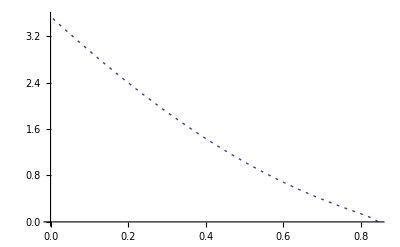

```mathematica
grExLP=ListPlot[dataExLP,Joined->True,PlotStyle->Dashing[{0.005,0.01}]]
```

#### dE/dx vs E: dEdxELP

```mathematica
dEdxEeLP =Interpolation[dataLPE];
dEdxEiLP =Interpolation[dataLPI];
```

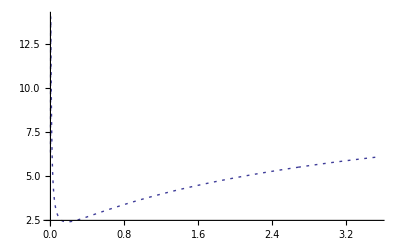

```mathematica
grdEdxELP=Plot[dEdxELP[e],{e,emin,emax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->10000,PlotRange->All]
```

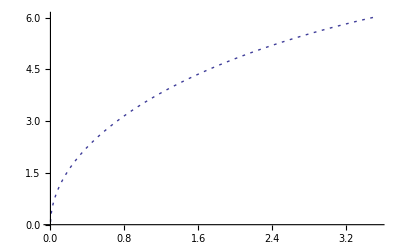

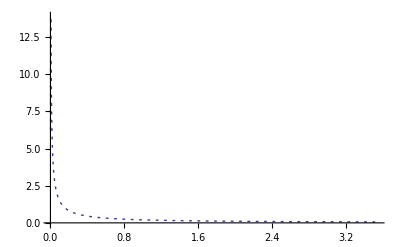

```mathematica
grdEdxEeLP=Plot[dEdxEeLP[e],{e,emin,emax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->1000,PlotRange->All]
grdEdxEiLP=Plot[dEdxEiLP[e],{e,emin,emax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->1000,PlotRange->All]
```

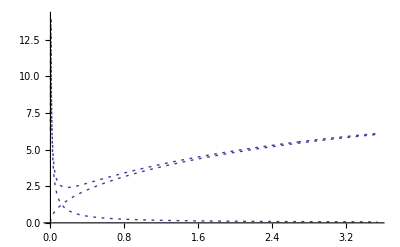

```mathematica
grdEdxEeiLP=Show[grdEdxEeLP,grdEdxEiLP,grdEdxELP]
```

#### dE/dx vs x: dEdxx LP

```mathematica
dEdxxLP[x_] := dEdxELP[ExLP[x]]
dEdxxeLP[x_] := dEdxEeLP[ExLP[x]]
dEdxxiLP[x_] := dEdxEiLP[ExLP[x]]
```

```mathematica
xRLP
xRLPmax=FindRoot[dEdxxLP[x]==0,{x,xRLP}][[1,2]]
```

0.842913

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000350258} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

0.842878

```mathematica
dEdxxLP[xRLP]
dEdxxLP[xRLPmax]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-8.57559

InterpolatingFunction::dmval: Input value {0.000433271} lies outside the range of data in the interpolating function. Extrapolation will be used.

-5.59609×10^-10

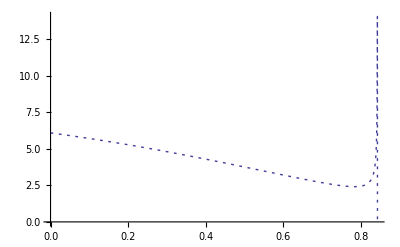

```mathematica
grdEdxxLP=Plot[dEdxxLP[x],{x,0,xRLPmax},PlotStyle->Dashing[{0.005,0.01}],
PlotPoints->1000,PlotPoints->All,PlotRange->All]
```

```mathematica
x0=0.2;
NIntegrate[dEdxxLP[x],{x,0,x0},MaxRecursion->10]
NIntegrate[dEdxxLP[x],{x,x0,xRLPmax},MaxRecursion->100]
% + %%
```

1.14155

2.39772

3.53927

```mathematica
100*(%-E0)/E0
100*eth/E0
```

-0.0206975

0.0293785

```mathematica
100*eth/E0
```

0.0293785

partitioned among plasma components

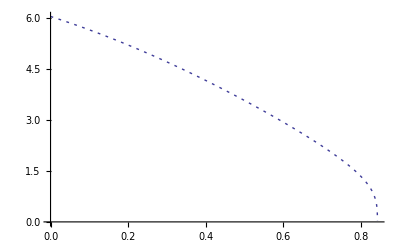

```mathematica
grdEdxxeLP=Plot[dEdxxeLP[x] ,{x,0,xRLPmax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->1000,PlotPoints->All]
```

```mathematica
Ee=NIntegrate[dEdxxeLP[x],{x,0,xRLPmax}]
```

3.25748

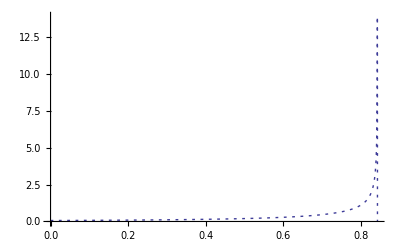

```mathematica
grdEdxxiLP=Plot[dEdxxiLP[x] ,{x,0,xRLPmax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->1000,PlotRange->All]
```

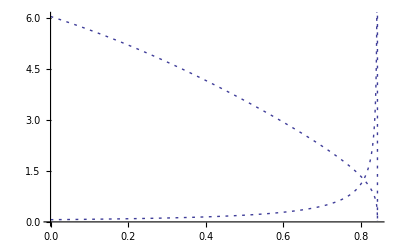

```mathematica
grdEdxxeiLP=Show[grdEdxxeLP,grdEdxxiLP]
```

```mathematica
xRLPmax
```

0.842878

```mathematica
x1=0.4;
NIntegrate[dEdxxiLP[x],{x,0,x1},MaxRecursion->10]
NIntegrate[dEdxxiLP[x],{x,x1,xRLPmax},MaxRecursion->10]
Ei=% + %%
```

0.0387883

0.243006

0.281794

```mathematica
{Ee,Ei,Ee+Ei,E0}
```

{3.25748,0.281794,3.53927,3.54}

```mathematica
100*(E0-Ee-Ei)/E0
```

0.020546

### BPS

#### evaluate data

```mathematica
emin=0.001;
emax=3.54;
```

```mathematica
E1=emin;
E2=0.03;
NN=600;
dE=(E2-E1)/NN;
dataBPSa=Table[{EE,dedxi[VP[EE]]},{EE,E1,E2,dE}];

E1=E2+dE;
E2=0.25;
NN=100;
dE=(E2-E1)/NN;
dataBPSb=Table[{EE,dedxi[VP[EE]]},{EE,E1,E2,dE}];

E1=E2+dE;
E2=emax;
NN=100;
dE=(E2-E1)/NN;
dataBPSc=Table[{EE,dedxi[VP[EE]]},{EE,E1,E2,dE}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in StoppingPower`PrivateBPS`u near {StoppingPower`PrivateBPS`u} = {0.00175267}. NIntegrate obtained -1.483×10^-9 and 1.87892×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in StoppingPower`PrivateBPS`u near {StoppingPower`PrivateBPS`u} = {0.0092537}. NIntegrate obtained -1.62982×10^-9 and 1.5105×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in StoppingPower`PrivateBPS`u near {StoppingPower`PrivateBPS`u} = {0.0131228}. NIntegrate obtained -1.78357×10^-9 and 1.5458×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
dataBPSEI=Join[dataBPSa,dataBPSb,dataBPSc]
```

{{0.001,{-0.0355488,-1.15188,-1.12489}},{0.00104833,{-0.033188,-1.01042,-0.973254}},{0.00109667,{-0.0308796,-0.874872,-0.827989}},{0.001145,{-0.0286166,-0.744748,-0.688653}},{0.00119333,{-0.0263931,-0.619626,-0.554866}},{0.00124167,{-0.0242041,-0.499145,-0.426299}},{0.00129,{-0.0220454,-0.382988,-0.302659}},{0.00133833,{-0.0199134,-0.270879,-0.183689}},{0.00138667,{-0.017805,-0.162577,-0.069158}},{0.001435,{-0.0157177,-0.0578649,0.041142}},{0.00148333,{-0.0136493,0.0434471,0.1474}},{0.00153167,{-0.0115978,0.14153,0.249788}},{0.00158,{-0.00956166,0.236539,0.348466}},{0.00162833,{-0.00753954,0.328613,0.44358}},{0.00167667,{-0.00553024,0.417879,0.535266}},{0.001725,{-0.00353279,0.504452,0.623651}},{0.00177333,{-0.00154636,0.588438,0.708856}},{0.00182167,{0.000429731,0.669935,0.790994}},{0.00187,{0.00239606,0.749034,0.87017}},{0.00191833,{0.00435309,0.825819,0.946486}},{0.00196667,{0.00630119,0.900368,1.02004}},{0.002015,{0.00824067,0.972754,1.09092}},{0.00206333,{0.0101717,1.04305,1.15921}},{0.00211167,{0.0120946,1.11131,1.22501}},{0.00216,{0.0140093,1.17761,1.28838}},{0.00220833,{0.0159159,1.24199,1.34942}},{0.00225667,{0.0178145,1.30453,1.40818}},{0.002305,{0.019705,1.36526,1.46476}},{0.00235333,{0.0215874,1.42424,1.5192}},{0.00240167,{0.0234617,1.48151,1.57159}},{0.00245,{0.0253276,1.53713,1.62199}},{0.00249833,{0.0271852,1.59114,1.67046}},{0.00254667,{0.0290342,1.64358,1.71706}},{0.002595,{0.0308745,1.69449,1.76184}},{0.00264333,{0.032706,1.74391,1.80488}},{0.00269167,{0.0345285,1.79188,1.84622}},{0.00274,{0.0363418,1.83843,1.88592}},{0.00278833,{0.0381457,1.88361,1.92402}},{0.00283667,{0.0399401,1.92745,1.96059}},{0.002885,{0.0417247,1.96998,1.99567}},{0.00293333,{0.0434994,2.01123,2.0293}},{0.00298167,{0.045264,2.05124,2.06154}},{0.00303,{0.0470183,2.09004,2.09242}},{0.00307833,{0.0487622,2.12766,2.122}},{0.00312667,{0.0504954,2.16413,2.15031}},{0.003175,{0.0522178,2.19947,2.1774}},{0.00322333,{0.0539292,2.23372,2.2033}},{0.00327167,{0.0556295,2.26691,2.22806}},{0.00332,{0.0573185,2.29905,2.25171}},{0.00336833,{0.0589961,2.33019,2.27428}},{0.00341667,{0.0606621,2.36033,2.29583}},{0.003465,{0.0623165,2.38952,2.31637}},{0.00351333,{0.063959,2.41776,2.33594}},{0.00356167,{0.0655896,2.44509,2.35457}},{0.00361,{0.0672082,2.47153,2.3723}},{0.00365833,{0.0688147,2.49711,2.38916}},{0.00370667,{0.0704091,2.52183,2.40517}},{0.003755,{0.0719911,2.54574,2.42037}},{0.00380333,{0.0735609,2.56884,2.43478}},{0.00385167,{0.0751183,2.59116,2.44842}},{0.0039,{0.0766632,2.61271,2.46133}},{0.00394833,{0.0781958,2.63353,2.47353}},{0.00399667,{0.0797158,2.65362,2.48504}},{0.004045,{0.0812234,2.67301,2.49589}},{0.00409333,{0.0827184,2.69171,2.5061}},{0.00414167,{0.084201,2.70975,2.51569}},{0.00419,{0.0856711,2.72714,2.52469}},{0.00423833,{0.0871286,2.74389,2.53311}},{0.00428667,{0.0885737,2.76003,2.54097}},{0.004335,{0.0900064,2.77556,2.5483}},{0.00438333,{0.0914267,2.79051,2.55511}},{0.00443167,{0.0928347,2.8049,2.56142}},{0.00448,{0.0942303,2.81873,2.56725}},{0.00452833,{0.0956137,2.83202,2.57262}},{0.00457667,{0.0969849,2.84479,2.57754}},{0.004625,{0.0983439,2.85704,2.58203}},{0.00467333,{0.0996909,2.8688,2.5861}},{0.00472167,{0.101026,2.88008,2.58977}},{0.00477,{0.102349,2.89088,2.59305}},{0.00481833,{0.10366,2.90123,2.59596}},{0.00486667,{0.10496,2.91113,2.5985}},{0.004915,{0.106248,2.9206,2.60071}},{0.00496333,{0.107524,2.92964,2.60257}},{0.00501167,{0.108789,2.93828,2.60412}},{0.00506,{0.110043,2.94651,2.60535}},{0.00510833,{0.111285,2.95436,2.60629}},{0.00515667,{0.112517,2.96183,2.60694}},{0.005205,{0.113737,2.96893,2.60731}},{0.00525333,{0.114946,2.97567,2.60742}},{0.00530167,{0.116145,2.98206,2.60726}},{0.00535,{0.117333,2.98811,2.60686}},{0.00539833,{0.11851,2.99384,2.60623}},{0.00544667,{0.119677,2.99924,2.60536}},{0.005495,{0.120833,3.00433,2.60427}},{0.00554333,{0.12198,3.00912,2.60297}},{0.00559167,{0.123116,3.01361,2.60147}},{0.00564,{0.124242,3.01781,2.59977}},{0.00568833,{0.125358,3.02173,2.59788}},{0.00573667,{0.126465,3.02539,2.59582}},{0.005785,{0.127562,3.02878,2.59357}},{0.00583333,{0.128649,3.03191,2.59116}},{0.00588167,{0.129727,3.03479,2.58859}},{0.00593,{0.130796,3.03742,2.58587}},{0.00597833,{0.131856,3.03982,2.58299}},{0.00602667,{0.132906,3.04199,2.57998}},{0.006075,{0.133948,3.04394,2.57682}},{0.00612333,{0.134981,3.04567,2.57354}},{0.00617167,{0.136005,3.04719,2.57013}},{0.00622,{0.137021,3.0485,2.5666}},{0.00626833,{0.138028,3.04961,2.56296}},{0.00631667,{0.139027,3.05053,2.5592}},{0.006365,{0.140017,3.05125,2.55534}},{0.00641333,{0.141,3.0518,2.55138}},{0.00646167,{0.141974,3.05216,2.54732}},{0.00651,{0.142941,3.05235,2.54317}},{0.00655833,{0.1439,3.05237,2.53892}},{0.00660667,{0.144851,3.05223,2.5346}},{0.006655,{0.145795,3.05193,2.53019}},{0.00670333,{0.146731,3.05147,2.52571}},{0.00675167,{0.14766,3.05086,2.52115}},{0.0068,{0.148582,3.05011,2.51652}},{0.00684833,{0.149496,3.04921,2.51183}},{0.00689667,{0.150404,3.04817,2.50707}},{0.006945,{0.151304,3.047,2.50225}},{0.00699333,{0.152198,3.0457,2.49737}},{0.00704167,{0.153085,3.04428,2.49244}},{0.00709,{0.153965,3.04272,2.48745}},{0.00713833,{0.154839,3.04105,2.48242}},{0.00718667,{0.155706,3.03927,2.47734}},{0.007235,{0.156567,3.03737,2.47221}},{0.00728333,{0.157422,3.03535,2.46704}},{0.00733167,{0.158271,3.03324,2.46184}},{0.00738,{0.159113,3.03102,2.45659}},{0.00742833,{0.159949,3.0287,2.45131}},{0.00747667,{0.16078,3.02628,2.446}},{0.007525,{0.161605,3.02377,2.44066}},{0.00757333,{0.162424,3.02116,2.43529}},{0.00762167,{0.163237,3.01847,2.42989}},{0.00767,{0.164045,3.01569,2.42446}},{0.00771833,{0.164847,3.01282,2.41901}},{0.00776667,{0.165644,3.00988,2.41354}},{0.007815,{0.166435,3.00686,2.40805}},{0.00786333,{0.167221,3.00375,2.40255}},{0.00791167,{0.168002,3.00058,2.39702}},{0.00796,{0.168778,2.99733,2.39148}},{0.00800833,{0.169549,2.99402,2.38592}},{0.00805667,{0.170315,2.99063,2.38035}},{0.008105,{0.171076,2.98719,2.37477}},{0.00815333,{0.171832,2.98367,2.36918}},{0.00820167,{0.172583,2.9801,2.36358}},{0.00825,{0.17333,2.97647,2.35798}},{0.00829833,{0.174072,2.97278,2.35236}},{0.00834667,{0.174809,2.96903,2.34675}},{0.008395,{0.175542,2.96523,2.34112}},{0.00844333,{0.176271,2.96138,2.33549}},{0.00849167,{0.176995,2.95748,2.32987}},{0.00854,{0.177715,2.95353,2.32423}},{0.00858833,{0.178431,2.94953,2.3186}},{0.00863667,{0.179142,2.94549,2.31297}},{0.008685,{0.179849,2.9414,2.30734}},{0.00873333,{0.180552,2.93727,2.30171}},{0.00878167,{0.181252,2.9331,2.29609}},{0.00883,{0.181947,2.92889,2.29046}},{0.00887833,{0.182638,2.92464,2.28485}},{0.00892667,{0.183325,2.92036,2.27923}},{0.008975,{0.184009,2.91604,2.27363}},{0.00902333,{0.184689,2.91168,2.26803}},{0.00907167,{0.185365,2.9073,2.26243}},{0.00912,{0.186038,2.90288,2.25684}},{0.00916833,{0.186706,2.89843,2.25127}},{0.00921667,{0.187372,2.89396,2.2457}},{0.009265,{0.188034,2.88945,2.24013}},{0.00931333,{0.188692,2.88492,2.23458}},{0.00936167,{0.189347,2.88036,2.22904}},{0.00941,{0.189998,2.87578,2.22351}},{0.00945833,{0.190647,2.87117,2.21799}},{0.00950667,{0.191292,2.86654,2.21248}},{0.009555,{0.191933,2.86189,2.20699}},{0.00960333,{0.192572,2.85722,2.2015}},{0.00965167,{0.193207,2.85253,2.19603}},{0.0097,{0.19384,2.84782,2.19057}},{0.00974833,{0.194469,2.84309,2.18513}},{0.00979667,{0.195095,2.83835,2.1797}},{0.009845,{0.195718,2.83358,2.17428}},{0.00989333,{0.196338,2.82881,2.16888}},{0.00994167,{0.196956,2.82402,2.16349}},{0.00999,{0.19757,2.81921,2.15811}},{0.0100383,{0.198182,2.81439,2.15275}},{0.0100867,{0.19879,2.80956,2.14741}},{0.010135,{0.199396,2.80472,2.14208}},{0.0101833,{0.2,2.79986,2.13677}},{0.0102317,{0.2006,2.795,2.13148}},{0.01028,{0.201198,2.79013,2.1262}},{0.0103283,{0.201793,2.78524,2.12093}},{0.0103767,{0.202386,2.78035,2.11569}},{0.010425,{0.202976,2.77545,2.11046}},{0.0104733,{0.203563,2.77055,2.10525}},{0.0105217,{0.204148,2.76564,2.10005}},{0.01057,{0.204731,2.76072,2.09487}},{0.0106183,{0.205311,2.75579,2.08971}},{0.0106667,{0.205888,2.75087,2.08457}},{0.010715,{0.206464,2.74593,2.07944}},{0.0107633,{0.207036,2.741,2.07434}},{0.0108117,{0.207607,2.73606,2.06925}},{0.01086,{0.208175,2.73112,2.06417}},{0.0109083,{0.208741,2.72617,2.05912}},{0.0109567,{0.209305,2.72122,2.05408}},{0.011005,{0.209866,2.71628,2.04907}},{0.0110533,{0.210425,2.71133,2.04407}},{0.0111017,{0.210983,2.70638,2.03909}},{0.01115,{0.211537,2.70143,2.03413}},{0.0111983,{0.21209,2.69648,2.02918}},{0.0112467,{0.212641,2.69153,2.02426}},{0.011295,{0.213189,2.68658,2.01935}},{0.0113433,{0.213736,2.68164,2.01446}},{0.0113917,{0.214281,2.67669,2.00959}},{0.01144,{0.214823,2.67175,2.00474}},{0.0114883,{0.215363,2.66681,1.99991}},{0.0115367,{0.215902,2.66187,1.9951}},{0.011585,{0.216439,2.65694,1.9903}},{0.0116333,{0.216973,2.65201,1.98552}},{0.0116817,{0.217506,2.64708,1.98077}},{0.01173,{0.218037,2.64216,1.97603}},{0.0117783,{0.218566,2.63724,1.97131}},{0.0118267,{0.219093,2.63233,1.96661}},{0.011875,{0.219618,2.62742,1.96193}},{0.0119233,{0.220142,2.62252,1.95726}},{0.0119717,{0.220664,2.61762,1.95262}},{0.01202,{0.221184,2.61273,1.94799}},{0.0120683,{0.221702,2.60784,1.94339}},{0.0121167,{0.222218,2.60296,1.9388}},{0.012165,{0.222733,2.59809,1.93423}},{0.0122133,{0.223246,2.59322,1.92968}},{0.0122617,{0.223758,2.58837,1.92514}},{0.01231,{0.224268,2.58351,1.92063}},{0.0123583,{0.224776,2.57867,1.91613}},{0.0124067,{0.225282,2.57383,1.91166}},{0.012455,{0.225787,2.569,1.9072}},{0.0125033,{0.226291,2.56418,1.90276}},{0.0125517,{0.226792,2.55936,1.89834}},{0.0126,{0.227293,2.55456,1.89393}},{0.0126483,{0.227791,2.54976,1.88955}},{0.0126967,{0.228288,2.54497,1.88518}},{0.012745,{0.228784,2.54019,1.88083}},{0.0127933,{0.229278,2.53542,1.8765}},{0.0128417,{0.229771,2.53066,1.87219}},{0.01289,{0.230262,2.5259,1.86789}},{0.0129383,{0.230751,2.52116,1.86362}},{0.0129867,{0.23124,2.51643,1.85936}},{0.013035,{0.231727,2.5117,1.85512}},{0.0130833,{0.232212,2.50699,1.85089}},{0.0131317,{0.232696,2.50228,1.84669}},{0.01318,{0.233179,2.49758,1.8425}},{0.0132283,{0.23366,2.4929,1.83833}},{0.0132767,{0.23414,2.48822,1.83418}},{0.013325,{0.234618,2.48356,1.83004}},{0.0133733,{0.235096,2.4789,1.82592}},{0.0134217,{0.235571,2.47426,1.82182}},{0.01347,{0.236046,2.46963,1.81774}},{0.0135183,{0.236519,2.465,1.81368}},{0.0135667,{0.236991,2.46039,1.80963}},{0.013615,{0.237462,2.45579,1.8056}},{0.0136633,{0.237931,2.4512,1.80158}},{0.0137117,{0.2384,2.44662,1.79758}},{0.01376,{0.238867,2.44205,1.7936}},{0.0138083,{0.239332,2.4375,1.78964}},{0.0138567,{0.239797,2.43295,1.78569}},{0.013905,{0.24026,2.42842,1.78176}},{0.0139533,{0.240722,2.42389,1.77785}},{0.0140017,{0.241183,2.41938,1.77395}},{0.01405,{0.241643,2.41488,1.77007}},{0.0140983,{0.242101,2.41039,1.7662}},{0.0141467,{0.242559,2.40592,1.76236}},{0.014195,{0.243015,2.40145,1.75852}},{0.0142433,{0.24347,2.397,1.75471}},{0.0142917,{0.243924,2.39255,1.75091}},{0.01434,{0.244377,2.38812,1.74713}},{0.0143883,{0.244829,2.38371,1.74336}},{0.0144367,{0.245279,2.3793,1.73961}},{0.014485,{0.245729,2.3749,1.73587}},{0.0145333,{0.246177,2.37052,1.73215}},{0.0145817,{0.246625,2.36615,1.72845}},{0.01463,{0.247071,2.36179,1.72476}},{0.0146783,{0.247516,2.35744,1.72108}},{0.0147267,{0.247961,2.35311,1.71742}},{0.014775,{0.248404,2.34879,1.71378}},{0.0148233,{0.248846,2.34447,1.71015}},{0.0148717,{0.249287,2.34018,1.70654}},{0.01492,{0.249727,2.33589,1.70294}},{0.0149683,{0.250166,2.33161,1.69936}},{0.0150167,{0.250604,2.32735,1.69579}},{0.015065,{0.251041,2.3231,1.69224}},{0.0151133,{0.251478,2.31886,1.6887}},{0.0151617,{0.251913,2.31464,1.68518}},{0.01521,{0.252347,2.31042,1.68167}},{0.0152583,{0.25278,2.30622,1.67818}},{0.0153067,{0.253212,2.30203,1.6747}},{0.015355,{0.253644,2.29785,1.67124}},{0.0154033,{0.254074,2.29369,1.66779}},{0.0154517,{0.254504,2.28954,1.66435}},{0.0155,{0.254932,2.2854,1.66093}},{0.0155483,{0.25536,2.28127,1.65752}},{0.0155967,{0.255786,2.27715,1.65413}},{0.015645,{0.256212,2.27305,1.65075}},{0.0156933,{0.256637,2.26896,1.64738}},{0.0157417,{0.257061,2.26488,1.64403}},{0.01579,{0.257484,2.26081,1.64069}},{0.0158383,{0.257906,2.25675,1.63737}},{0.0158867,{0.258328,2.25271,1.63406}},{0.015935,{0.258748,2.24868,1.63076}},{0.0159833,{0.259168,2.24466,1.62748}},{0.0160317,{0.259587,2.24066,1.62421}},{0.01608,{0.260005,2.23666,1.62095}},{0.0161283,{0.260422,2.23268,1.61771}},{0.0161767,{0.260838,2.22871,1.61448}},{0.016225,{0.261253,2.22475,1.61126}},{0.0162733,{0.261668,2.2208,1.60806}},{0.0163217,{0.262082,2.21687,1.60486}},{0.01637,{0.262495,2.21295,1.60169}},{0.0164183,{0.262907,2.20904,1.59852}},{0.0164667,{0.263318,2.20514,1.59537}},{0.016515,{0.263729,2.20126,1.59223}},{0.0165633,{0.264138,2.19738,1.5891}},{0.0166117,{0.264547,2.19352,1.58599}},{0.01666,{0.264956,2.18967,1.58289}},{0.0167083,{0.265363,2.18583,1.5798}},{0.0167567,{0.26577,2.18201,1.57672}},{0.016805,{0.266176,2.17819,1.57365}},{0.0168533,{0.266581,2.17439,1.5706}},{0.0169017,{0.266985,2.1706,1.56756}},{0.01695,{0.267389,2.16682,1.56453}},{0.0169983,{0.267792,2.16305,1.56152}},{0.0170467,{0.268194,2.1593,1.55851}},{0.017095,{0.268595,2.15555,1.55552}},{0.0171433,{0.268996,2.15182,1.55254}},{0.0171917,{0.269396,2.1481,1.54957}},{0.01724,{0.269795,2.14439,1.54662}},{0.0172883,{0.270193,2.1407,1.54367}},{0.0173367,{0.270591,2.13701,1.54074}},{0.017385,{0.270988,2.13334,1.53781}},{0.0174333,{0.271385,2.12968,1.5349}},{0.0174817,{0.27178,2.12603,1.53201}},{0.01753,{0.272175,2.12239,1.52912}},{0.0175783,{0.272569,2.11876,1.52624}},{0.0176267,{0.272963,2.11514,1.52338}},{0.017675,{0.273356,2.11154,1.52052}},{0.0177233,{0.273748,2.10794,1.51768}},{0.0177717,{0.27414,2.10436,1.51485}},{0.01782,{0.274531,2.10079,1.51203}},{0.0178683,{0.274921,2.09723,1.50922}},{0.0179167,{0.27531,2.09368,1.50642}},{0.017965,{0.275699,2.09015,1.50363}},{0.0180133,{0.276087,2.08662,1.50085}},{0.0180617,{0.276475,2.0831,1.49809}},{0.01811,{0.276862,2.0796,1.49533}},{0.0181583,{0.277248,2.07611,1.49258}},{0.0182067,{0.277634,2.07263,1.48985}},{0.018255,{0.278019,2.06916,1.48712}},{0.0183033,{0.278403,2.0657,1.48441}},{0.0183517,{0.278787,2.06225,1.48171}},{0.0184,{0.27917,2.05881,1.47901}},{0.0184483,{0.279553,2.05538,1.47633}},{0.0184967,{0.279934,2.05196,1.47366}},{0.018545,{0.280316,2.04856,1.471}},{0.0185933,{0.280696,2.04516,1.46834}},{0.0186417,{0.281076,2.04178,1.4657}},{0.01869,{0.281456,2.03841,1.46307}},{0.0187383,{0.281835,2.03504,1.46044}},{0.0187867,{0.282213,2.03169,1.45783}},{0.018835,{0.282591,2.02835,1.45523}},{0.0188833,{0.282968,2.02502,1.45264}},{0.0189317,{0.283344,2.0217,1.45005}},{0.01898,{0.28372,2.01839,1.44748}},{0.0190283,{0.284095,2.01509,1.44491}},{0.0190767,{0.28447,2.0118,1.44236}},{0.019125,{0.284844,2.00852,1.43981}},{0.0191733,{0.285218,2.00525,1.43728}},{0.0192217,{0.285591,2.002,1.43475}},{0.01927,{0.285963,1.99875,1.43224}},{0.0193183,{0.286335,1.99551,1.42973}},{0.0193667,{0.286706,1.99228,1.42723}},{0.019415,{0.287077,1.98907,1.42474}},{0.0194633,{0.287447,1.98586,1.42226}},{0.0195117,{0.287817,1.98266,1.41979}},{0.01956,{0.288186,1.97948,1.41733}},{0.0196083,{0.288554,1.9763,1.41487}},{0.0196567,{0.288922,1.97313,1.41243}},{0.019705,{0.28929,1.96997,1.41}},{0.0197533,{0.289657,1.96683,1.40757}},{0.0198017,{0.290023,1.96369,1.40515}},{0.01985,{0.290389,1.96056,1.40274}},{0.0198983,{0.290754,1.95745,1.40034}},{0.0199467,{0.291119,1.95434,1.39795}},{0.019995,{0.291483,1.95124,1.39557}},{0.0200433,{0.291847,1.94815,1.3932}},{0.0200917,{0.29221,1.94507,1.39083}},{0.02014,{0.292573,1.942,1.38847}},{0.0201883,{0.292935,1.93894,1.38613}},{0.0202367,{0.293297,1.93589,1.38379}},{0.020285,{0.293658,1.93285,1.38145}},{0.0203333,{0.294019,1.92982,1.37913}},{0.0203817,{0.294379,1.9268,1.37682}},{0.02043,{0.294738,1.92379,1.37451}},{0.0204783,{0.295098,1.92079,1.37221}},{0.0205267,{0.295456,1.91779,1.36992}},{0.020575,{0.295814,1.91481,1.36764}},{0.0206233,{0.296172,1.91183,1.36537}},{0.0206717,{0.296529,1.90887,1.3631}},{0.02072,{0.296886,1.90591,1.36084}},{0.0207683,{0.297242,1.90296,1.35859}},{0.0208167,{0.297598,1.90003,1.35635}},{0.020865,{0.297953,1.8971,1.35411}},{0.0209133,{0.298308,1.89418,1.35189}},{0.0209617,{0.298662,1.89127,1.34967}},{0.02101,{0.299016,1.88836,1.34746}},{0.0210583,{0.299369,1.88547,1.34526}},{0.0211067,{0.299722,1.88259,1.34306}},{0.021155,{0.300074,1.87971,1.34087}},{0.0212033,{0.300426,1.87684,1.33869}},{0.0212517,{0.300778,1.87399,1.33652}},{0.0213,{0.301129,1.87114,1.33435}},{0.0213483,{0.301479,1.8683,1.3322}},{0.0213967,{0.301829,1.86547,1.33004}},{0.021445,{0.302179,1.86264,1.3279}},{0.0214933,{0.302528,1.85983,1.32577}},{0.0215417,{0.302877,1.85702,1.32364}},{0.02159,{0.303225,1.85423,1.32152}},{0.0216383,{0.303573,1.85144,1.3194}},{0.0216867,{0.30392,1.84866,1.3173}},{0.021735,{0.304267,1.84589,1.3152}},{0.0217833,{0.304614,1.84312,1.3131}},{0.0218317,{0.30496,1.84037,1.31102}},{0.02188,{0.305305,1.83762,1.30894}},{0.0219283,{0.30565,1.83489,1.30687}},{0.0219767,{0.305995,1.83216,1.30481}},{0.022025,{0.306339,1.82944,1.30275}},{0.0220733,{0.306683,1.82672,1.3007}},{0.0221217,{0.307027,1.82402,1.29866}},{0.02217,{0.30737,1.82132,1.29662}},{0.0222183,{0.307712,1.81863,1.29459}},{0.0222667,{0.308054,1.81595,1.29257}},{0.022315,{0.308396,1.81328,1.29055}},{0.0223633,{0.308737,1.81061,1.28854}},{0.0224117,{0.309078,1.80796,1.28654}},{0.02246,{0.309419,1.80531,1.28454}},{0.0225083,{0.309759,1.80267,1.28255}},{0.0225567,{0.310099,1.80004,1.28057}},{0.022605,{0.310438,1.79741,1.27859}},{0.0226533,{0.310777,1.7948,1.27662}},{0.0227017,{0.311115,1.79219,1.27466}},{0.02275,{0.311453,1.78959,1.27271}},{0.0227983,{0.311791,1.78699,1.27075}},{0.0228467,{0.312128,1.78441,1.26881}},{0.022895,{0.312465,1.78183,1.26687}},{0.0229433,{0.312801,1.77926,1.26494}},{0.0229917,{0.313137,1.7767,1.26302}},{0.02304,{0.313473,1.77414,1.2611}},{0.0230883,{0.313808,1.77159,1.25919}},{0.0231367,{0.314143,1.76905,1.25728}},{0.023185,{0.314477,1.76652,1.25538}},{0.0232333,{0.314811,1.764,1.25349}},{0.0232817,{0.315145,1.76148,1.2516}},{0.02333,{0.315478,1.75897,1.24972}},{0.0233783,{0.315811,1.75647,1.24784}},{0.0234267,{0.316143,1.75397,1.24597}},{0.023475,{0.316475,1.75148,1.24411}},{0.0235233,{0.316807,1.749,1.24225}},{0.0235717,{0.317138,1.74653,1.2404}},{0.02362,{0.317469,1.74406,1.23855}},{0.0236683,{0.3178,1.7416,1.23671}},{0.0237167,{0.31813,1.73915,1.23488}},{0.023765,{0.31846,1.73671,1.23305}},{0.0238133,{0.31879,1.73427,1.23123}},{0.0238617,{0.319119,1.73184,1.22941}},{0.02391,{0.319447,1.72941,1.2276}},{0.0239583,{0.319776,1.727,1.2258}},{0.0240067,{0.320104,1.72459,1.224}},{0.024055,{0.320431,1.72219,1.22221}},{0.0241033,{0.320758,1.71979,1.22042}},{0.0241517,{0.321085,1.7174,1.21863}},{0.0242,{0.321412,1.71502,1.21686}},{0.0242483,{0.321738,1.71265,1.21509}},{0.0242967,{0.322064,1.71028,1.21332}},{0.024345,{0.322389,1.70792,1.21156}},{0.0243933,{0.322714,1.70556,1.20981}},{0.0244417,{0.323039,1.70322,1.20806}},{0.02449,{0.323363,1.70088,1.20631}},{0.0245383,{0.323687,1.69854,1.20458}},{0.0245867,{0.324011,1.69621,1.20284}},{0.024635,{0.324334,1.69389,1.20111}},{0.0246833,{0.324657,1.69158,1.19939}},{0.0247317,{0.32498,1.68927,1.19768}},{0.02478,{0.325302,1.68697,1.19596}},{0.0248283,{0.325624,1.68468,1.19426}},{0.0248767,{0.325946,1.68239,1.19256}},{0.024925,{0.326267,1.68011,1.19086}},{0.0249733,{0.326588,1.67783,1.18917}},{0.0250217,{0.326909,1.67556,1.18748}},{0.02507,{0.327229,1.6733,1.1858}},{0.0251183,{0.327549,1.67105,1.18413}},{0.0251667,{0.327868,1.6688,1.18246}},{0.025215,{0.328187,1.66655,1.18079}},{0.0252633,{0.328506,1.66432,1.17913}},{0.0253117,{0.328825,1.66209,1.17748}},{0.02536,{0.329143,1.65986,1.17583}},{0.0254083,{0.329461,1.65765,1.17418}},{0.0254567,{0.329778,1.65543,1.17254}},{0.025505,{0.330096,1.65323,1.17091}},{0.0255533,{0.330413,1.65103,1.16928}},{0.0256017,{0.330729,1.64884,1.16765}},{0.02565,{0.331045,1.64665,1.16603}},{0.0256983,{0.331361,1.64447,1.16442}},{0.0257467,{0.331677,1.64229,1.1628}},{0.025795,{0.331992,1.64013,1.1612}},{0.0258433,{0.332307,1.63796,1.1596}},{0.0258917,{0.332622,1.63581,1.158}},{0.02594,{0.332936,1.63365,1.15641}},{0.0259883,{0.33325,1.63151,1.15482}},{0.0260367,{0.333564,1.62937,1.15324}},{0.026085,{0.333877,1.62724,1.15166}},{0.0261333,{0.33419,1.62511,1.15009}},{0.0261817,{0.334503,1.62299,1.14852}},{0.02623,{0.334815,1.62087,1.14696}},{0.0262783,{0.335127,1.61876,1.1454}},{0.0263267,{0.335439,1.61666,1.14384}},{0.026375,{0.335751,1.61456,1.14229}},{0.0264233,{0.336062,1.61247,1.14075}},{0.0264717,{0.336373,1.61038,1.1392}},{0.02652,{0.336683,1.6083,1.13767}},{0.0265683,{0.336993,1.60623,1.13614}},{0.0266167,{0.337303,1.60416,1.13461}},{0.026665,{0.337613,1.60209,1.13309}},{0.0267133,{0.337922,1.60004,1.13157}},{0.0267617,{0.338231,1.59798,1.13005}},{0.02681,{0.33854,1.59594,1.12854}},{0.0268583,{0.338849,1.59389,1.12704}},{0.0269067,{0.339157,1.59186,1.12553}},{0.026955,{0.339465,1.58983,1.12404}},{0.0270033,{0.339772,1.5878,1.12254}},{0.0270517,{0.340079,1.58578,1.12106}},{0.0271,{0.340386,1.58377,1.11957}},{0.0271483,{0.340693,1.58176,1.11809}},{0.0271967,{0.340999,1.57976,1.11662}},{0.027245,{0.341305,1.57776,1.11514}},{0.0272933,{0.341611,1.57577,1.11368}},{0.0273417,{0.341917,1.57378,1.11221}},{0.02739,{0.342222,1.5718,1.11076}},{0.0274383,{0.342527,1.56982,1.1093}},{0.0274867,{0.342831,1.56785,1.10785}},{0.027535,{0.343136,1.56588,1.1064}},{0.0275833,{0.34344,1.56392,1.10496}},{0.0276317,{0.343744,1.56196,1.10352}},{0.02768,{0.344047,1.56001,1.10209}},{0.0277283,{0.34435,1.55807,1.10066}},{0.0277767,{0.344653,1.55613,1.09923}},{0.027825,{0.344956,1.55419,1.09781}},{0.0278733,{0.345258,1.55226,1.09639}},{0.0279217,{0.34556,1.55034,1.09497}},{0.02797,{0.345862,1.54842,1.09356}},{0.0280183,{0.346164,1.5465,1.09216}},{0.0280667,{0.346465,1.54459,1.09075}},{0.028115,{0.346766,1.54269,1.08936}},{0.0281633,{0.347066,1.54079,1.08796}},{0.0282117,{0.347367,1.53889,1.08657}},{0.02826,{0.347667,1.537,1.08518}},{0.0283083,{0.347967,1.53512,1.0838}},{0.0283567,{0.348266,1.53324,1.08242}},{0.028405,{0.348566,1.53136,1.08104}},{0.0284533,{0.348865,1.52949,1.07967}},{0.0285017,{0.349164,1.52763,1.0783}},{0.02855,{0.349462,1.52576,1.07694}},{0.0285983,{0.34976,1.52391,1.07558}},{0.0286467,{0.350058,1.52206,1.07422}},{0.028695,{0.350356,1.52021,1.07287}},{0.0287433,{0.350653,1.51837,1.07152}},{0.0287917,{0.350951,1.51653,1.07017}},{0.02884,{0.351248,1.5147,1.06883}},{0.0288883,{0.351544,1.51287,1.06749}},{0.0289367,{0.351841,1.51105,1.06615}},{0.028985,{0.352137,1.50923,1.06482}},{0.0290333,{0.352433,1.50742,1.06349}},{0.0290817,{0.352728,1.50561,1.06217}},{0.02913,{0.353023,1.50381,1.06085}},{0.0291783,{0.353319,1.50201,1.05953}},{0.0292267,{0.353613,1.50021,1.05822}},{0.029275,{0.353908,1.49842,1.05691}},{0.0293233,{0.354202,1.49664,1.0556}},{0.0293717,{0.354496,1.49486,1.0543}},{0.02942,{0.35479,1.49308,1.053}},{0.0294683,{0.355084,1.49131,1.0517}},{0.0295167,{0.355377,1.48954,1.05041}},{0.029565,{0.35567,1.48778,1.04912}},{0.0296133,{0.355963,1.48602,1.04783}},{0.0296617,{0.356255,1.48426,1.04655}},{0.02971,{0.356547,1.48251,1.04527}},{0.0297583,{0.356839,1.48077,1.044}},{0.0298067,{0.357131,1.47903,1.04272}},{0.029855,{0.357423,1.47729,1.04145}},{0.0299033,{0.357714,1.47556,1.04019}},{0.0299517,{0.358005,1.47383,1.03893}},{0.03,{0.358296,1.4721,1.03767}},{0.0300483,{0.358586,1.47038,1.03641}},{0.0322479,{0.371557,1.39644,0.982548}},{0.0344474,{0.384074,1.33004,0.934408}},{0.0366469,{0.396185,1.27008,0.891108}},{0.0388464,{0.407929,1.21567,0.85194}},{0.0410459,{0.419339,1.16606,0.816326}},{0.0432454,{0.430442,1.12063,0.783794}},{0.045445,{0.441265,1.07886,0.75395}},{0.0476445,{0.451827,1.04032,0.726467}},{0.049844,{0.462148,1.00465,0.70107}},{0.0520435,{0.472243,0.971529,0.677522}},{0.054243,{0.482128,0.940685,0.655626}},{0.0564425,{0.491816,0.911886,0.635207}},{0.0586421,{0.501318,0.884933,0.616119}},{0.0608416,{0.510646,0.859648,0.598231}},{0.0630411,{0.519808,0.835877,0.581432}},{0.0652406,{0.528813,0.813486,0.565621}},{0.0674401,{0.537671,0.792355,0.550712}},{0.0696396,{0.546387,0.772376,0.536629}},{0.0718392,{0.554969,0.753458,0.523302}},{0.0740387,{0.563422,0.735514,0.51067}},{0.0762382,{0.571754,0.71847,0.49868}},{0.0784377,{0.579968,0.702258,0.487282}},{0.0806372,{0.588071,0.686816,0.476432}},{0.0828367,{0.596066,0.67209,0.46609}},{0.0850363,{0.603958,0.65803,0.456221}},{0.0872358,{0.611751,0.644591,0.446793}},{0.0894353,{0.619449,0.631731,0.437775}},{0.0916348,{0.627055,0.619412,0.42914}},{0.0938343,{0.634573,0.6076,0.420865}},{0.0960338,{0.642006,0.596264,0.412926}},{0.0982334,{0.649356,0.585375,0.405302}},{0.100433,{0.656627,0.574905,0.397976}},{0.102632,{0.663821,0.564832,0.390929}},{0.104832,{0.670941,0.555131,0.384145}},{0.107031,{0.677989,0.545782,0.37761}},{0.109231,{0.684967,0.536766,0.371309}},{0.11143,{0.691877,0.528065,0.36523}},{0.11363,{0.698721,0.519662,0.359361}},{0.115829,{0.705502,0.511542,0.353691}},{0.118029,{0.712221,0.50369,0.34821}},{0.120229,{0.71888,0.496093,0.342909}},{0.122428,{0.725481,0.488739,0.337777}},{0.124628,{0.732024,0.481614,0.332808}},{0.126827,{0.738512,0.47471,0.327993}},{0.129027,{0.744947,0.468015,0.323326}},{0.131226,{0.751328,0.461519,0.318798}},{0.133426,{0.757659,0.455214,0.314405}},{0.135625,{0.763939,0.449092,0.310139}},{0.137825,{0.770171,0.443143,0.305995}},{0.140024,{0.776355,0.437361,0.301969}},{0.142224,{0.782493,0.431739,0.298054}},{0.144423,{0.788586,0.42627,0.294246}},{0.146623,{0.794634,0.420947,0.290541}},{0.148822,{0.80064,0.415764,0.286935}},{0.151022,{0.806602,0.410717,0.283423}},{0.153221,{0.812524,0.405799,0.280002}},{0.155421,{0.818405,0.401006,0.276668}},{0.15762,{0.824246,0.396332,0.273418}},{0.15982,{0.830049,0.391774,0.270248}},{0.162019,{0.835813,0.387326,0.267156}},{0.164219,{0.841541,0.382985,0.264139}},{0.166418,{0.847232,0.378747,0.261193}},{0.168618,{0.852887,0.374608,0.258317}},{0.170817,{0.858508,0.370565,0.255508}},{0.173017,{0.864094,0.366614,0.252763}},{0.175216,{0.869646,0.362752,0.250081}},{0.177416,{0.875166,0.358976,0.247458}},{0.179615,{0.880653,0.355284,0.244894}},{0.181815,{0.886108,0.351671,0.242385}},{0.184015,{0.891532,0.348136,0.239931}},{0.186214,{0.896926,0.344676,0.237529}},{0.188414,{0.902289,0.341289,0.235178}},{0.190613,{0.907623,0.337972,0.232876}},{0.192813,{0.912928,0.334723,0.230622}},{0.195012,{0.918204,0.33154,0.228414}},{0.197212,{0.923452,0.328422,0.22625}},{0.199411,{0.928673,0.325365,0.224129}},{0.201611,{0.933866,0.322368,0.222051}},{0.20381,{0.939033,0.319429,0.220013}},{0.20601,{0.944174,0.316547,0.218014}},{0.208209,{0.949289,0.31372,0.216054}},{0.210409,{0.954378,0.310947,0.214131}},{0.212608,{0.959443,0.308225,0.212244}},{0.214808,{0.964482,0.305553,0.210392}},{0.217007,{0.969498,0.30293,0.208574}},{0.219207,{0.97449,0.300355,0.206789}},{0.221406,{0.979458,0.297826,0.205036}},{0.223606,{0.984404,0.295341,0.203315}},{0.225805,{0.989326,0.292901,0.201624}},{0.228005,{0.994226,0.290503,0.199963}},{0.230204,{0.999104,0.288147,0.19833}},{0.232404,{1.00396,0.285831,0.196726}},{0.234603,{1.00879,0.283554,0.195149}},{0.236803,{1.01361,0.281315,0.193598}},{0.239002,{1.0184,0.279114,0.192074}},{0.241202,{1.02317,0.276949,0.190575}},{0.243401,{1.02793,0.274819,0.1891}},{0.245601,{1.03266,0.272724,0.18765}},{0.2478,{1.03737,0.270663,0.186223}},{0.25,{1.04206,0.268634,0.184818}},{0.2522,{1.04673,0.266638,0.183436}},{0.285078,{1.11446,0.240146,0.165109}},{0.317956,{1.17866,0.218677,0.15027}},{0.350834,{1.23987,0.200902,0.137993}},{0.383712,{1.29852,0.185925,0.127656}},{0.41659,{1.35493,0.173122,0.118825}},{0.449468,{1.40937,0.162044,0.111187}},{0.482346,{1.46205,0.152358,0.104512}},{0.515224,{1.51316,0.143813,0.0986259}},{0.548102,{1.56284,0.136214,0.0933935}},{0.58098,{1.61123,0.12941,0.0887101}},{0.613858,{1.65843,0.123281,0.0844921}},{0.646736,{1.70454,0.117728,0.0806723}},{0.679614,{1.74964,0.112674,0.077196}},{0.712492,{1.7938,0.108052,0.0740181}},{0.74537,{1.8371,0.103808,0.0711011}},{0.778248,{1.87959,0.0998981,0.0684136}},{0.811126,{1.92131,0.0962826,0.0659292}},{0.844004,{1.96232,0.0929291,0.0636253}},{0.876882,{2.00265,0.0898098,0.0614827}},{0.90976,{2.04235,0.0869006,0.0594848}},{0.942638,{2.08144,0.0841806,0.0576171}},{0.975516,{2.11996,0.0816318,0.0558671}},{1.00839,{2.15794,0.0792381,0.0542239}},{1.04127,{2.19539,0.0769856,0.0526779}},{1.07415,{2.23236,0.074862,0.0512205}},{1.10703,{2.26885,0.0728565,0.0498443}},{1.13991,{2.30489,0.0709592,0.0485426}},{1.17278,{2.34049,0.0691615,0.0473094}},{1.20566,{2.37568,0.0674558,0.0461393}},{1.23854,{2.41047,0.0658349,0.0450275}},{1.27142,{2.44487,0.0642927,0.0439698}},{1.3043,{2.47891,0.0628234,0.0429623}},{1.33717,{2.51258,0.061422,0.0420014}},{1.37005,{2.54591,0.0600838,0.0410838}},{1.40293,{2.5789,0.0588045,0.0402068}},{1.43581,{2.61157,0.0575803,0.0393676}},{1.46869,{2.64393,0.0564077,0.0385639}},{1.50156,{2.67598,0.0552834,0.0377933}},{1.53444,{2.70774,0.0542045,0.0370539}},{1.56732,{2.73921,0.0531682,0.0363437}},{1.6002,{2.77041,0.0521721,0.0356611}},{1.63308,{2.80133,0.0512138,0.0350045}},{1.66595,{2.83199,0.0502911,0.0343723}},{1.69883,{2.86239,0.0494021,0.0337632}},{1.73171,{2.89254,0.048545,0.0331761}},{1.76459,{2.92245,0.0477181,0.0326096}},{1.79747,{2.95211,0.0469197,0.0320627}},{1.83034,{2.98155,0.0461484,0.0315344}},{1.86322,{3.01076,0.0454029,0.0310238}},{1.8961,{3.03974,0.0446818,0.0305299}},{1.92898,{3.06851,0.0439839,0.030052}},{1.96186,{3.09706,0.0433082,0.0295893}},{1.99473,{3.12541,0.0426536,0.029141}},{2.02761,{3.15355,0.042019,0.0287065}},{2.06049,{3.18148,0.0414037,0.0282852}},{2.09337,{3.20923,0.0408066,0.0278764}},{2.12625,{3.23678,0.040227,0.0274796}},{2.15912,{3.26414,0.0396642,0.0270943}},{2.192,{3.29131,0.0391174,0.02672}},{2.22488,{3.3183,0.0385859,0.0263561}},{2.25776,{3.34511,0.0380691,0.0260023}},{2.29064,{3.37174,0.0375663,0.0256582}},{2.32351,{3.3982,0.0370771,0.0253233}},{2.35639,{3.42449,0.0366008,0.0249974}},{2.38927,{3.45061,0.0361369,0.0246799}},{2.42215,{3.47657,0.0356851,0.0243707}},{2.45503,{3.50236,0.0352447,0.0240693}},{2.4879,{3.52799,0.0348154,0.0237755}},{2.52078,{3.55346,0.0343967,0.023489}},{2.55366,{3.57877,0.0339882,0.0232095}},{2.58654,{3.60393,0.0335897,0.0229368}},{2.61942,{3.62894,0.0332006,0.0226706}},{2.65229,{3.6538,0.0328208,0.0224106}},{2.68517,{3.6785,0.0324497,0.0221568}},{2.71805,{3.70307,0.0320872,0.0219088}},{2.75093,{3.72749,0.031733,0.0216664}},{2.78381,{3.75176,0.0313867,0.0214296}},{2.81668,{3.7759,0.0310482,0.0211979}},{2.84956,{3.79989,0.030717,0.0209714}},{2.88244,{3.82375,0.0303931,0.0207498}},{2.91532,{3.84747,0.0300761,0.020533}},{2.9482,{3.87106,0.0297659,0.0203208}},{2.98107,{3.89451,0.0294621,0.020113}},{3.01395,{3.91783,0.0291647,0.0199096}},{3.04683,{3.94102,0.0288734,0.0197104}},{3.07971,{3.96409,0.0285881,0.0195152}},{3.11259,{3.98702,0.0283085,0.0193239}},{3.14546,{4.00983,0.0280344,0.0191365}},{3.17834,{4.03251,0.0277658,0.0189528}},{3.21122,{4.05507,0.0275024,0.0187727}},{3.2441,{4.07751,0.0272441,0.0185961}},{3.27698,{4.09982,0.0269908,0.0184228}},{3.30985,{4.12202,0.0267422,0.0182529}},{3.34273,{4.14409,0.0264984,0.0180861}},{3.37561,{4.16605,0.026259,0.0179224}},{3.40849,{4.18789,0.0260241,0.0177618}},{3.44137,{4.20961,0.0257935,0.0176041}},{3.47424,{4.23122,0.025567,0.0174492}},{3.50712,{4.25272,0.0253446,0.0172972}},{3.54,{4.2741,0.0251261,0.0171478}}}

#### saved data

```mathematica
emin=0.001;
emax=3.54;
```

```mathematica
dataBPSEI={{0.001,{-0.035548770452305686,-1.1518837313585772,-1.1248862066514123}},{0.0010483333333333334,{-0.03318796512793627,-1.0104198819047174,-0.973253622958759}},{0.0010966666666666668,{-0.03087959042248288,-0.8748717191667451,-0.827988933308236}},{0.001145,{-0.028616606649860425,-0.7447475294073838,-0.6886529718144261}},{0.0011933333333333334,{-0.026393104426106855,-0.6196263010008255,-0.5548664694406895}},{0.0012416666666666667,{-0.024204101107089877,-0.49914487667603147,-0.4262987662128088}},{0.00129,{-0.022045379956093483,-0.3829878086854928,-0.30265897617595855}},{0.0013383333333333333,{-0.01991336184643281,-0.27087927412761365,-0.18368901126706416}},{0.0013866666666666667,{-0.017805002021212102,-0.16257657739216297,-0.0691580286466569}},{0.001435,{-0.015717706307612832,-0.057864887407495125,0.041142021618430905}},{0.0014833333333333335,{-0.013649262625508545,0.043447055648948935,0.1473999908827146}},{0.0015316666666666666,{-0.011597784574707564,0.14153046606635455,0.2497884518806669}},{0.00158,{-0.009561664668624296,0.23653942582286322,0.3484660847256215}},{0.0016283333333333334,{-0.007539535308784893,0.3286133054972885,0.44357963723943483}},{0.0016766666666666666,{-0.005530236030653394,0.4178787867793333,0.5352655437991309}},{0.001725,{-0.0035327858470371714,0.5044515605252855,0.6236512686333913}},{0.0017733333333333334,{-0.001546359763550019,0.5884377590088289,0.7088564255634825}},{0.0018216666666666667,{0.000429731250326703,0.66993516920011,0.7909937154558598}},{0.0018700000000000001,{0.002396057458766549,0.749034264708159,0.870169714336939}},{0.0019183333333333333,{0.004353085171386661,0.8258190868132562,0.9464855386282384}},{0.001966666666666667,{0.0063011895813342225,0.9003679993260894,1.0200374088588537}},{0.002015,{0.008240665927902815,0.9727543374933928,1.0909171291800717}},{0.0020633333333333333,{0.01017173925966354,1.0430469675605876,1.1592124968010957}},{0.0021116666666666666,{0.01209457300338572,1.1113107707029415,1.2250076529023768}},{0.00216,{0.014009276511662935,1.1776070626951418,1.2883833845245163}},{0.0022083333333333334,{0.015915911749685853,1.2419939587885704,1.3494173852687568}},{0.002256666666666667,{0.0178144992283521,1.3045266917150362,1.4081844812976447}},{0.002305,{0.01970502330262803,1.3652578894658265,1.4647568280268244}},{0.002353333333333333,{0.02158743690169425,1.4242378184492153,1.5192040820014774}},{0.0024016666666666665,{0.023461665779949736,1.4815145967659233,1.5715935517144535}},{0.00245,{0.025327612341608442,1.537134381625559,1.6219903305158843}},{0.0024983333333333333,{0.027185159093602015,1.5911415343299977,1.6704574142625996}},{0.0025466666666666667,{0.029034171761785937,1.6435787657512,1.7170558059392582}},{0.002595,{0.03087450212348085,1.6944872648126494,1.7618446091368554}},{0.0026433333333333335,{0.03270599057159285,1.7439068121314791,1.8048811119851036}},{0.002691666666666667,{0.03452846844791512,1.7918758806815667,1.846220862893393}},{0.0027400000000000002,{0.03634176015918493,1.838431725085838,1.8859177392516575}},{0.002788333333333333,{0.03814568510921426,1.8836104609327193,1.9240240100717239}},{0.0028366666666666666,{0.039940059447969314,1.9274471353291054,1.9605903934054152}},{0.002885,{0.04172469766557176,1.9699757897468766,1.995666109253461}},{0.0029333333333333334,{0.04349941403427564,2.011229516086388,2.0292989285760163}},{0.0029816666666666668,{0.04526402391833172,2.051240506765667,2.0615352189273555}},{0.00303,{0.04701834495211423,2.0900400995450696,2.0924199871625064}},{0.0030783333333333335,{0.04876219810598481,2.1276588177116786,2.1219969195994306}},{0.0031266666666666665,{0.05049540863732015,2.164126406173268,2.1503084199656772}},{0.003175,{0.05221780693770221,2.1994718639472586,2.1773956454114294}},{0.0032233333333333333,{0.05392922929102262,2.2337234734734817,2.203298540830502}},{0.0032716666666666666,{0.05562951852850059,2.266908827130355,2.2280558716961743}},{0.00332,{0.05731852461281775,2.299054851290496,2.251705255588795}},{0.0033683333333333334,{0.058996105129191234,2.330187828213776,2.27428319256631}},{0.003416666666666667,{0.06066212570929902,2.360333416041962,2.2958250945066108}},{0.003465,{0.062316460383804895,2.389516667129231,2.3163653135312607}},{0.0035133333333333336,{0.06395899186343425,2.417762044916264,2.33593716960362}},{0.0035616666666666665,{0.06558961176730628,2.4450934395320623,2.354572977379889}},{0.00361,{0.06720822078475058,2.471534182286507,2.372304072379258}},{0.0036583333333333333,{0.06881472879085544,2.4971070591978206,2.3891608365285064}},{0.0037066666666666667,{0.07040905490841233,2.521834323682327,2.4051727231273072}},{0.003755,{0.0719911275243052,2.5457377085186894,2.4203682812723555}},{0.0038033333333333335,{0.07356088426666263,2.5688384371853767,2.4347751797717474}},{0.003851666666666667,{0.07511827193940437,2.5911572346578295,2.4484202305751857}},{0.0039,{0.07666324642590104,2.6127143377410174,2.461329411740645}},{0.003948333333333333,{0.0781957725576817,2.63352950500323,2.4735278899538584}},{0.003996666666666667,{0.07971582395782414,2.653622026368121,2.4850400426136066}},{0.004045,{0.08122338285527247,2.6730107324143715,2.495889479492777}},{0.004093333333333333,{0.08271843988046253,2.6917140034250546,2.5060990639827776}},{0.004141666666666667,{0.08420099383782371,2.7097497782227493,2.5156909339269093}},{0.00419,{0.08567105146555297,2.727135562820777,2.5246865220468355}},{0.0042383333333333335,{0.08712862717687003,2.743888438915953,2.5331065759648914}},{0.004286666666666667,{0.08857374279095294,2.7600250722440096,2.540971177824267}},{0.004335,{0.0900064272563458,2.7755617208148227,2.548299763508255}},{0.004383333333333334,{0.09142671636261103,2.7905142430413417,2.5551111414594163}},{0.004431666666666667,{0.09283465244897691,2.804898105773063,2.5614235110992167}},{0.00448,{0.09423028410847327,2.818728392242317,2.5672544808485616}},{0.004528333333333333,{0.09561366588997453,2.832019809930031,2.5726210857497778}},{0.004576666666666666,{0.09698485799759791,2.844786698353761,2.5775398046905686}},{0.004625,{0.09834392599498117,2.8570430367825863,2.582026577230856}},{0.004673333333333333,{0.09969094050623077,2.8688024518786497,2.586096820033558}},{0.0047216666666666665,{0.10102597692492142,2.8800782252661214,2.589765442900665}},{0.00477,{0.10234911512136202,2.8908833010267676,2.593046864417314}},{0.004818333333333333,{0.103660439161223,2.901230293120609,2.5959550272038965}},{0.004866666666666667,{0.10496003702506024,2.9111314927297145,2.5985034127817017}},{0.004915,{0.10624800033387258,2.9205988755226002,2.6007050560531226}},{0.0049633333333333335,{0.10752442408668521,2.9296441088365195,2.602572559400603}},{0.005011666666666667,{0.10878940640011432,2.9382785587746727,2.6041181064081895}},{0.00506,{0.11004304825710583,2.9465132972152532,2.6053534752099368}},{0.005108333333333334,{0.11128545326534858,2.9543591087292964,2.6062900514697884}},{0.005156666666666667,{0.11251672742230698,2.9618264974041835,2.606938840998}},{0.005205,{0.11373697889132274,2.968925693569933,2.6073104820093955}},{0.005253333333333334,{0.11494631778101506,2.975666660425361,2.60741525702911}},{0.005301666666666666,{0.11614485594005788,2.98205910056152,2.6072631044517665}},{0.00535,{0.11733270675655103,2.9881124623799056,2.6068636297603422}},{0.005398333333333333,{0.1185099849653442,2.993835946403216,2.606226116410247}},{0.0054466666666666665,{0.11967680646885961,2.999238511476652,2.605359536387549}},{0.005495,{0.12083328816165403,3.004328880857975,2.6042725604447763}},{0.005543333333333333,{0.12197954776539914,3.0091155481948513,2.602973568023755}},{0.005591666666666667,{0.12311570367048578,3.013606783388197,2.601470656871392}},{0.00564,{0.12424187479190271,3.017810638340484,2.599771652355687}},{0.0056883333333333334,{0.12535818042288133,3.0217349525883392,2.5978841164890465}},{0.005736666666666667,{0.1264647401058517,3.0253873588184748,2.595815356666177}},{0.005785,{0.12756167350542283,3.028775288268791,2.5935724341236224}},{0.005833333333333334,{0.1286491002893595,3.031905976009244,2.5911621721282563}},{0.005881666666666667,{0.12972714001983743,3.0347864661099453,2.588591163901808}},{0.00593,{0.13079591204768717,3.0374236166910364,2.5858657802886316}},{0.005978333333333334,{0.1318555354149058,3.0398241048578774,2.582992177173753}},{0.006026666666666666,{0.13290612876315508,3.041994431520569,2.5799763026582454}},{0.006075,{0.13394781024950503,3.043940926099934,2.5768239039985943}},{0.006123333333333333,{0.13498069746630328,3.045669751120373,2.5735405343185267}},{0.0061716666666666664,{0.1360049073676278,3.047186906690877,2.5701315590964624}},{0.00622,{0.13702055620165046,3.0484982348754683,2.5666021624382584}},{0.006268333333333333,{0.138027759445538,3.049609423954518,2.5629573531432666}},{0.006316666666666667,{0.13902663175065527,3.0505260125783873,2.559201970564701}},{0.006365,{0.14001728688480328,3.051253393815027,2.5553406902754516}},{0.006413333333333333,{0.1409998376850464,3.0517968190932065,2.5513780295434687}},{0.006461666666666667,{0.14197439601412282,3.052161402043085,2.547318352623111}},{0.00651,{0.1429410727161576,3.052352122236005,2.543165875868307}},{0.0065583333333333335,{0.14389997758145445,3.052373828825267,2.538924672673287}},{0.006606666666666667,{0.14485121931360445,3.05223124408987,2.534598678246473}},{0.006655,{0.14579490549716265,3.051928966883132,2.5301916942229883}},{0.006703333333333334,{0.14673114257226286,3.0514714759881003,2.525707393121091}},{0.006751666666666667,{0.14766003581094758,3.050863133381824,2.5211493226477155}},{0.0068000000000000005,{0.14858168929364535,3.0501081874104137,2.5165209098581127}},{0.006848333333333333,{0.1494962058934863,3.0492107758769307,2.511825465174494}},{0.006896666666666666,{0.15040368725916808,3.0481749290441,2.5070661862684225}},{0.006945,{0.15130423380144287,3.04700457255385,2.5022461618115193}},{0.006993333333333333,{0.15219794468213588,3.0457035302656994,2.4973683750989712}},{0.0070416666666666666,{0.1530849178049776,3.044275527015933,2.4924357075501615}},{0.00709,{0.15396524980842696,3.042724191299618,2.4874509420911215}},{0.007138333333333333,{0.15483903606065788,3.0410530578772876,2.4824167664197914}},{0.007186666666666667,{0.1557063706543804,3.0392655703083933,2.4773357761655603}},{0.007235,{0.15656734640752187,3.0373650834132815,2.472210477936303}},{0.0072833333333333335,{0.15742205485953922,3.035354865665668,2.467043292268208}},{0.007331666666666667,{0.15827058627573468,3.0332381015174508,2.4618365564683153}},{0.00738,{0.15911302964635204,3.031017893657656,2.456592527367845}},{0.007428333333333334,{0.15994947269127396,3.0286972652073345,2.451313383979181}},{0.007476666666666667,{0.16078000186384794,3.0262791618521843,2.446001230063846}},{0.0075250000000000004,{0.1616047023596254,3.0237664539145963,2.440658096613902}},{0.007573333333333333,{0.16242365811699067,3.021161938366847,2.4352859442497583}},{0.007621666666666666,{0.16323695182952436,3.0184683407870816,2.4298866655337834}},{0.00767,{0.16404466495085782,3.0156883172596776,2.424462087223221}},{0.007718333333333333,{0.16484687770649697,3.012824456221658,2.41901397241424}},{0.0077666666666666665,{0.16564366910068204,3.009879280256603,2.413544022650845}},{0.007815,{0.1664351169275832,3.0068552478376573,2.408053879925547}},{0.007863333333333333,{0.16722129778266506,3.0037547550210397,2.4025451286590136}},{0.007911666666666668,{0.16800228707325449,3.000580137091568,2.397019297571594}},{0.00796,{0.16877815902945,2.997333670161521,2.3914778615144194}},{0.008008333333333333,{0.1695489867181526,2.9940175727242635,2.3859222432279066}},{0.008056666666666667,{0.17031484205360467,2.990634007163942,2.38035381505668}},{0.008105,{0.1710757958115826,2.9871850812225538,2.374773900592616}},{0.008153333333333334,{0.1718319176412147,2.9836728494256386,2.3691837762706998}},{0.008201666666666666,{0.1725832760795934,2.9800993144678127,2.36358467291049}},{0.00825,{0.17332993856385903,2.9764664285593687,2.3579777772065276}},{0.008298333333333333,{0.17407197144675146,2.9727760947350697,2.352364233169447}},{0.008346666666666667,{0.1748094400087999,2.9690301681262614,2.3467451435194926}},{0.008395,{0.17554240847312128,2.965230457197413,2.341121571034047}},{0.008443333333333334,{0.1762709400195862,2.9613787249481325,2.335494539850773}},{0.008491666666666666,{0.17699509679958178,2.95747669008169,2.3298650367278935}},{0.00854,{0.1777149399482458,2.953526028141064,2.3242340122630285}},{0.008588333333333333,{0.17843052960080164,2.949528372613439,2.3186023820720667}},{0.008636666666666667,{0.17914192490724343,2.9454853159925345,2.3129710279293847}},{0.008685,{0.1798491840437831,2.941398410869396,2.3073407988707593}},{0.008733333333333333,{0.18055236423023455,2.937269170889417,2.301712512260207}},{0.008781666666666667,{0.18125152174309103,2.933099071740683,2.296086954822019}},{0.00883,{0.18194671192935272,2.928889552171706,2.290464883639128}},{0.008878333333333334,{0.18263798922166644,2.924642014879548,2.284847027118977}},{0.008926666666666666,{0.1833254071516784,2.9203578274300233,2.2792340859279614}},{0.008975,{0.18400901836398703,2.916038323141616,2.2736267338955187}},{0.009023333333333333,{0.18468887463088443,2.9116848019454022,2.268025618888892}},{0.009071666666666667,{0.1853650268662641,2.907298531221385,2.2624313636595317}},{0.00912,{0.1860375251378872,2.902880746613522,2.2568445666621146}},{0.009168333333333334,{0.186706418682231,2.898432652820282,2.251265802847051}},{0.009216666666666666,{0.18737175591822208,2.8939554243663768,2.2456956244274404}},{0.009265,{0.18803358446007937,2.889450206352982,2.240134561621248}},{0.009313333333333333,{0.1886919511305682,2.8849181151862924,2.2345831233695677}},{0.009361666666666667,{0.18934690197436732,2.8803602392902485,2.2290417980317785}},{0.00941,{0.18999848227031269,2.8757776397967536,2.2235110540583394}},{0.009458333333333334,{0.1906467365456157,2.8711713512193326,2.2179913406419405}},{0.009506666666666667,{0.1912917085873933,2.8665423821086047,2.2124830883478035}},{0.009555,{0.19193344145523278,2.86189171569047,2.2069867097237585}},{0.009603333333333334,{0.19257197749459895,2.8572203104874934,2.2015025998907216}},{0.009651666666666666,{0.19320735834749786,2.852529100923973,2.196031137114362}},{0.0097,{0.19383962496520793,2.8478189979151973,2.190572683358425}},{0.009748333333333333,{0.1944688176215611,2.843090889441265,2.1851275848203975}},{0.009796666666666667,{0.1950949759219864,2.838345641106019,2.1796961724500825}},{0.009845,{0.19571813881731034,2.8335840966814407,2.174278762451616}},{0.009893333333333334,{0.1963383446139082,2.828807078637935,2.1688756567694902}},{0.009941666666666666,{0.19695563098519608,2.824015388660954,2.163487143559114}},{0.00999,{0.19757003498308795,2.819209808154262,2.1581134976423617}},{0.010038333333333333,{0.1981815930487172,2.8143910987303227,2.1527549809486626}},{0.010086666666666667,{0.19879034102295276,2.809560002688088,2.1474118429420734}},{0.010135,{0.19939631415685416,2.804717243478574,2.1420843210347704}},{0.010183333333333334,{0.19999954712221585,2.7998635261586076,2.136772640987422}},{0.010231666666666667,{0.20060007402263705,2.794999537832977,2.1314770172968776}},{0.010280000000000001,{0.20119792840239006,2.7901259480854295,2.1261976535715252}},{0.010328333333333333,{0.20179314325606235,2.7852434093987215,2.120934742894814}},{0.010376666666666666,{0.20238575104040504,2.7803525575641075,2.1156884681771944}},{0.010425,{0.20297578368137753,2.77545401208049,2.1104590024969774}},{0.010473333333333333,{0.2035632725851267,2.7705483765435774,2.1052465094303767}},{0.010521666666666667,{0.20414824864708048,2.7656362390252895,2.1000511433711035}},{0.01057,{0.20473074226087318,2.760718172443677,2.094873049839894}},{0.010618333333333334,{0.20531078332611916,2.7557947349243035,2.0897123657842127}},{0.010666666666666666,{0.20588840126029284,2.7508664701493606,2.084569219868497}},{0.010715,{0.2064636250042864,2.745933907704546,2.0794437327552844}},{0.010763333333333333,{0.20703648303271835,2.7409975634110824,2.0743360173773606}},{0.010811666666666667,{0.20760700335992327,2.736057939651685,2.0692461792013854}},{0.01086,{0.20817521355209803,2.7311155256924304,2.0641743164832196}},{0.010908333333333334,{0.20874114073225322,2.7261707979878564,2.0591205205151235}},{0.010956666666666667,{0.20930481158854145,2.721224220487253,2.0540848758652013}},{0.011005000000000001,{0.20986625238266626,2.7162762449292313,2.0490674606092742}},{0.011053333333333333,{0.21042548895995383,2.711327311129929,2.0440683465554557}},{0.011101666666666666,{0.21098254675115183,2.7063778472641786,2.039087599461605}},{0.01115,{0.21153745078427239,2.7014282701398837,2.0341252792459543}},{0.011198333333333333,{0.2120902256905106,2.6964789854657076,2.0291814401910866}},{0.011246666666666667,{0.2126408957110793,2.691530388112309,2.0242561311414544}},{0.011295,{0.21318948470440655,2.6865828623672607,2.0193493956946904}},{0.011343333333333334,{0.21373601615355528,2.6816367821838263,2.0144612723868747}},{0.011391666666666666,{0.21428051317211716,2.6766925114237554,2.009591794871937}},{0.01144,{0.21482299851198383,2.6717504040942686,2.004740992095421}},{0.011488333333333333,{0.2153634945675285,2.6668108045793435,1.999908888450403}},{0.011536666666666667,{0.21590202338498282,2.661874047865483,1.995095503989054}},{0.011585,{0.2164386066659142,2.6569404597621022,1.9903008545087069}},{0.011633333333333334,{0.21697326577583834,2.6520103571166644,1.9855249517661222}},{0.011681666666666667,{0.2175060217477032,2.647084048024697,1.980767803556714}},{0.01173,{0.21803689529031206,2.642161832034834,1.9760294139427326}},{0.011778333333333333,{0.21856590679191243,2.6372440003490074,1.9713097833361153}},{0.011826666666666666,{0.21909307632733604,2.6323308360178834,1.9666089086466525}},{0.011875,{0.2196184236638854,2.6274226141317136,1.9619267834121068}},{0.011923333333333333,{0.22014196826437044,2.6225196020079773,1.9572633979242164}},{0.011971666666666667,{0.22066372929524872,2.617622059368141,1.9526187393506682}},{0.01202,{0.22118372563102393,2.612730238523137,1.9479927918532352}},{0.012068333333333334,{0.2217019758587345,2.607844384541698,1.943385536702146}},{0.012116666666666666,{0.22221849828333373,2.6029647354211125,1.938796952386823}},{0.012165,{0.2227333109332622,2.598091522252734,1.934227014723089}},{0.012213333333333333,{0.22324643156548946,2.593224969383607,1.929675696956979}},{0.012261666666666667,{0.2237578776682683,2.5883652945743547,1.925142969865229}},{0.01231,{0.22426766646837112,2.583512709153369,1.9206288018525688}},{0.012358333333333334,{0.22477581493489004,2.5786674181674325,1.9161331590458959}},{0.012406666666666667,{0.2252823397828929,2.5738296205288425,1.9116560053854785}},{0.012455,{0.22578725747857853,2.5689995091591276,1.9071973027131757}},{0.012503333333333333,{0.2262905842443263,2.56417727112944,1.9027570108579042}},{0.012551666666666668,{0.22679233606121404,2.5593630877976947,1.8983350877183098}},{0.0126,{0.22729252867541647,2.5545571349425638,1.8939314893428243}},{0.012648333333333333,{0.2277911775999002,2.5497595828943616,1.8895461700071265}},{0.012696666666666667,{0.228288298120873,2.5449705966629343,1.8851790822891132}},{0.012745,{0.22878390529986448,2.540190336062587,1.8808301771414733}},{0.012793333333333334,{0.22927801397871683,2.5354189558341877,1.8764994039618923}},{0.012841666666666666,{0.2297706387828564,2.5306566057643964,1.872186710661014}},{0.01289,{0.23026179412568815,2.5259034308022437,1.8678920437281878}},{0.012938333333333333,{0.2307514942115336,2.52115957117298,1.8636153482950883}},{0.012986666666666667,{0.23123975303918565,2.516425162489364,1.8593565681972732}},{0.013035,{0.23172658440652072,2.511700335860375,1.8551156460337404}},{0.013083333333333334,{0.23221200191246208,2.506985217975428,1.850892523224536}},{0.013131666666666666,{0.23269601896199962,2.5022799312967354,1.8466871400664946}},{0.01318,{0.23317864876831942,2.4975845940486767,1.8424994357871425}},{0.013228333333333333,{0.2336599043565096,2.4928993203207526,1.83832934859686}},{0.013276666666666668,{0.2341397985664204,2.48822422027087,1.834176815739297}},{0.013325,{0.23461834405699256,2.4835594001338013,1.8300417735401593}},{0.013373333333333334,{0.23509555330774673,2.4789049623353834,1.8259241574543845}},{0.013421666666666667,{0.23557143862304294,2.474261005582967,1.8218239021117348}},{0.01347,{0.2360460121343729,2.4696276249538287,1.81774094136091}},{0.013518333333333334,{0.23651928580373827,2.465004911981566,1.8136752083121768}},{0.013566666666666666,{0.2369912714263871,2.4603929547405525,1.8096266353785948}},{0.013615,{0.23746198063337007,2.455791837928465,1.8055951543158528}},{0.013663333333333333,{0.237931424894545,2.45120164294697,1.801580696260783}},{0.013711666666666667,{0.23839961552159075,2.4466224479805647,1.7975831917685847}},{0.01376,{0.238866563669845,2.4420543280736595,1.793602570848783}},{0.013808333333333334,{0.23933228034207701,2.4374973552059056,1.789638762999996}},{0.013856666666666666,{0.23979677638958719,2.4329515983658476,1.7856916972435035}},{0.013905,{0.24026006251675977,2.428417123622887,1.7817613021557033}},{0.013953333333333333,{0.24072214928097765,2.423893994197653,1.7778475058994339}},{0.014001666666666667,{0.24118304709697042,2.419382270530777,1.7739502362542525}},{0.01405,{0.24164276623913677,2.4148820103501185,1.770069420645659}},{0.014098333333333334,{0.24210131684241779,2.410393268736489,1.7662049861733278}},{0.014146666666666667,{0.2425587089067772,2.405916098187903,1.7623568596383548}},{0.014195,{0.2430149522967574,2.40145054868234,1.758524967569566}},{0.014243333333333334,{0.2434700567463606,2.396996667739183,1.7547092362489256}},{0.014291666666666666,{0.24392403185934308,2.392554500479222,1.7509095917360238}},{0.01434,{0.24437688711234606,2.3881240896832816,1.747125959891742}},{0.014388333333333333,{0.24482863185628195,2.383705475849611,1.743358266401069}},{0.014436666666666667,{0.2452792753196444,2.3792986972499257,1.7396064367951}},{0.014485,{0.2457288266085818,2.3749037899842342,1.7358703964722852}},{0.014533333333333334,{0.24617729471081803,2.3705207880343915,1.7321500707188902}},{0.014581666666666666,{0.2466246884957479,2.366149723316502,1.728445384728749}},{0.01463,{0.2470710167182074,2.3617906257321093,1.7247562636222769}},{0.014678333333333333,{0.247516288019102,2.35744352321826,1.721082632464829}},{0.014726666666666667,{0.24796051092755936,2.3531084417964365,1.7174244162843595}},{0.014775,{0.24840369386326067,2.3487854056204007,1.7137815400884633}},{0.014823333333333334,{0.24884584513657892,2.3444744370229698,1.7101539288807692}},{0.014871666666666667,{0.249286972952523,2.3401755565617215,1.7065415076767356}},{0.01492,{0.24972708541125394,2.3358887830637087,1.7029442015188598}},{0.014968333333333333,{0.2501661905088697,2.331614133669154,1.699361935491324}},{0.015016666666666666,{0.2506042961418584,2.327351623874163,1.695794634734068}},{0.015065,{0.25104141010528375,2.323101267572484,1.692242224456347}},{0.015113333333333333,{0.2514775400964611,2.3188630770963514,1.6887046299497819}},{0.015161666666666667,{0.25191269371708624,2.314637063256381,1.6851817766008683}},{0.01521,{0.25234687847206677,2.310423235380603,1.6816735899030504}},{0.015258333333333334,{0.2527801017740254,2.3062216013525974,1.6781799954682781}},{0.015306666666666666,{0.25321237094299237,2.302032167648779,1.674700919038151}},{0.015355,{0.253643693208011,2.2978549393748757,1.6712362864945822}},{0.015403333333333333,{0.2540740757092912,2.29368992030154,1.6677860238700728}},{0.015451666666666667,{0.254503525499337,2.2895371128991955,1.66435005735754}},{0.0155,{0.2549320495435582,2.2853965183721057,1.6609283133197617}},{0.015548333333333334,{0.25535965472238525,2.281268136691645,1.6575207182984366}},{0.015596666666666667,{0.25578634783344356,2.277151966628863,1.6541271990228619}},{0.015645,{0.2562121355902895,2.2730480057862956,1.6507476824182408}},{0.015693333333333333,{0.25663702462608523,2.268956250629061,1.6473820956136553}},{0.015741666666666668,{0.2570610214942285,2.2648766965152607,1.644030365949684}},{0.01579,{0.25748413266863046,2.2608093377257115,1.6406924209857028}},{0.015838333333333333,{0.2579063645466607,2.256754167492978,1.6373681885068456}},{0.015886666666666667,{0.25832772344814925,2.2527111780297826,1.6340575965306843}},{0.015935,{0.2587482156191348,2.2486803605567616,1.6307605733135846}},{0.015983333333333332,{0.2591678472301453,2.24466170532958,1.6274770473567872}},{0.016031666666666666,{0.25958662438005237,2.240655201665508,1.6242069474122047}},{0.01608,{0.26000455309514453,2.2366608379692696,1.6209502024879494}},{0.016128333333333335,{0.2604216393314446,2.232678601758442,1.6177067418535929}},{0.016176666666666666,{0.2608378889753898,2.2287084796881667,1.614476495045176}},{0.016225,{0.26125330784431144,2.224750457575419,1.6112593918699787}},{0.016273333333333334,{0.26166790168847104,2.220804520422631,1.6080553624110432}},{0.01632166666666667,{0.26208167619154216,2.2168706524408246,1.6048643370314728}},{0.01637,{0.26249463697178427,2.212948837072212,1.601686246378506}},{0.016418333333333333,{0.2629067895826204,2.2090390570122915,1.5985210213873786}},{0.016466666666666668,{0.2633181395136736,2.2051412942314306,1.5953685932849775}},{0.016515,{0.26372869219248624,2.2012555299959695,1.592228893593295}},{0.016563333333333333,{0.2641384529849251,2.197381744888839,1.5891018541326745}},{0.016611666666666667,{0.26454748902778735,2.1935199188297068,1.5859874070248985}},{0.01666,{0.26495568199128183,2.1896700310946886,1.5828854846960603}},{0.016708333333333332,{0.26536309323716245,2.1858320603355748,1.5797960198792937}},{0.016756666666666666,{0.2657697390341926,2.182005984598643,1.576718945617296}},{0.016805,{0.2661756188779529,2.1781917813430365,1.57365419526473}},{0.016853333333333335,{0.2665807377826864,2.1743894274587205,1.5706017024904306}},{0.016901666666666666,{0.2669851007067003,2.170598899284031,1.5675614012794712}},{0.01695,{0.2673887125535821,2.1668201726228156,1.5645332259350995}},{0.016998333333333334,{0.26779157817312454,2.1630532227611905,1.5615171110804973}},{0.01704666666666667,{0.26819370236104256,2.159298024483906,1.5585129916604326}},{0.017095,{0.26859508986142516,2.1555545520903467,1.5555208029427618}},{0.017143333333333333,{0.26899574536655385,2.1518227794101374,1.5525404805198044}},{0.017191666666666668,{0.26939567351730725,2.148102679818426,1.5495719603096045}},{0.01724,{0.26979487890456505,2.144394226250795,1.5466151785570634}},{0.017288333333333333,{0.27019336606971367,2.1406973912178167,1.54367007162099}},{0.017336666666666667,{0.2705911395054249,2.137012146819302,1.5407365770447943}},{0.017385,{0.27098820365598236,2.133338464758184,1.537814631417758}},{0.017433333333333332,{0.27138456291850876,2.1296763163541232,1.5349041725152304}},{0.017481666666666666,{0.2717802216434092,2.126025672556746,1.5320051382294904}},{0.01753,{0.27217518413430897,2.1223865039586216,1.5291174667841818}},{0.017578333333333335,{0.27256945465064075,2.1187587808079025,1.5262410967347209}},{0.017626666666666665,{0.2729630374054385,2.1151424730206996,1.5233759669686209}},{0.017675,{0.27335593656917434,2.111537550193135,1.5205220167057094}},{0.017723333333333334,{0.2737481562675092,2.1079439816131487,1.5176791854982783}},{0.017771666666666668,{0.27413970058378284,2.1043617362719913,1.5148474132311596}},{0.01782,{0.27453057355899163,2.1007907828754693,1.5120266401216966}},{0.017868333333333333,{0.274920779191946,2.0972310898549855,1.509216806719674}},{0.017916666666666668,{0.2753103214406401,2.0936826253781406,1.506417853907145}},{0.017965000000000002,{0.2756992042222726,2.090145357359288,1.5036297228982207}},{0.018013333333333333,{0.27608743141428793,2.0866192534697188,1.5008523552387665}},{0.018061666666666667,{0.27647500685374504,2.083104281147648,1.4980856928060444}},{0.01811,{0.2768619343392398,2.079600407607954,1.495329677806198}},{0.018158333333333332,{0.2772482176322301,2.0761075998516803,1.4925842527820365}},{0.018206666666666666,{0.2776338604543993,2.072625824675321,1.4898493606003376}},{0.018255,{0.2780188664906359,2.069155048679875,1.4871249444592072}},{0.018303333333333335,{0.2784032393892086,2.0656952382797042,1.4844109478881695}},{0.018351666666666665,{0.2787869827616616,2.0622463597111373,1.4817073147368949}},{0.0184,{0.27917010018343996,2.058808379040909,1.4790139891901406}},{0.018448333333333334,{0.2795525951956514,2.0553812621743885,1.4763309157566455}},{0.018496666666666668,{0.27993447130320503,2.0519649748635773,1.4736580392708447}},{0.018545,{0.28031573197728643,2.0485594827149525,1.4709953048920053}},{0.018593333333333333,{0.28069638065455776,2.0451647511970976,1.4683426581032906}},{0.018641666666666667,{0.2810764207389172,2.041780745648152,1.4657000447108455}},{0.018690000000000002,{0.28145585560005015,2.038407431283087,1.4630674108427755}},{0.018738333333333333,{0.28183468857577393,2.0350447732007857,1.4604447029480865}},{0.018786666666666667,{0.2822129229718141,2.031692736390966,1.4578318677958337}},{0.018835,{0.28259056206112043,2.028351285740928,1.455228852473679}},{0.018883333333333332,{0.28296760908617075,2.0250203860421334,1.4526356043870552}},{0.018931666666666666,{0.2833440672582152,2.021700001996616,1.450052071257899}},{0.01898,{0.28371993975748444,2.0183900982232554,1.44747820112349}},{0.019028333333333335,{0.2840952297345436,2.0150906392638577,1.444913942335238}},{0.019076666666666665,{0.28446994031001527,2.0118015895891257,1.442359243557464}},{0.019125,{0.2848440745751854,2.0085229136044442,1.4398140537661201}},{0.019173333333333334,{0.2852176355917714,2.005254575655542,1.4372783222475265}},{0.019221666666666668,{0.2855906263937679,2.001996540034007,1.4347519985970631}},{0.01927,{0.28596304998625366,1.998748770982648,1.4322350327178408}},{0.019318333333333333,{0.2863349093463387,1.9955112327007434,1.4297273748193595}},{0.019366666666666667,{0.28670620742433184,1.992283889349129,1.4272289754161571}},{0.019415,{0.2870769471421668,1.9890667050551907,1.4247397853264048}},{0.019463333333333332,{0.28744713139576566,1.9858596439176912,1.4222597556705332}},{0.019511666666666667,{0.2878167630542858,1.9826626700114964,1.419788837869805}},{0.01956,{0.28818584496051813,1.9794757473921765,1.4173269836448945}},{0.019608333333333332,{0.28855437993201183,1.9762988401004737,1.414874145014438}},{0.019656666666666666,{0.28892237075966254,1.9731319121666768,1.4124302742935817}},{0.019705,{0.2892898202106371,1.9699749276148601,1.409995324092519}},{0.019753333333333335,{0.289656731025761,1.9668278504670227,1.4075692473149979}},{0.019801666666666665,{0.29002310592229097,1.9636906447471145,1.405151997156852}},{0.01985,{0.29038894759244444,1.9605632744849486,1.4027435271044797}},{0.019898333333333334,{0.2907542587053903,1.9574457037200255,1.400343790933344}},{0.019946666666666668,{0.29111904190573873,1.9543378965052496,1.3979527427064535}},{0.019995,{0.29148329981487375,1.9512398169105263,1.3955703367728374}},{0.020043333333333333,{0.2918470350316564,1.9481514290262933,1.39319652776601}},{0.020091666666666667,{0.2922102501317481,1.945072696966932,1.3908312706024355}},{0.02014,{0.29257294766768405,1.9420035848740969,1.3884745204799778}},{0.020188333333333332,{0.2929351301709932,1.938944056919951,1.3861262328763506}},{0.020236666666666667,{0.29329680015003456,1.9358940773103104,1.3837863635475647}},{0.020285,{0.2936579600923049,1.9328536102877043,1.3814548685263568}},{0.020333333333333335,{0.2940186124632266,1.9298226201343511,1.3791317041206435}},{0.020381666666666666,{0.29437875970743144,1.9268010711750394,1.376816826911941}},{0.02043,{0.2947384042482693,1.923788927779948,1.3745101937537936}},{0.020478333333333334,{0.29509754848876707,1.9207861543673692,1.3722117617702134}},{0.020526666666666665,{0.2954561948112134,1.9177927154063539,1.3699214883540913}},{0.020575,{0.2958143455776372,1.914808575419294,1.3676393311656363}},{0.020623333333333334,{0.29617200313050607,1.9118336989844262,1.3653652481307879}},{0.020671666666666668,{0.29652916979229876,1.9088680507382436,1.3630991974396416}},{0.02072,{0.29688584786581756,1.9059115953778663,1.3608411375448781}},{0.020768333333333333,{0.2972420396350066,1.9029642976633232,1.3585910271601798}},{0.020816666666666667,{0.2975977473643864,1.900026122419768,1.3563488252586542}},{0.020865,{0.29795297330005394,1.897097034539627,1.354114491071259}},{0.020913333333333332,{0.2983077196693994,1.8941769989847048,1.3518879840852374}},{0.020961666666666667,{0.2986619886810509,1.8912659807881822,1.349669264042527}},{0.02101,{0.29901578252585753,1.8883639450565937,1.3474582909382113}},{0.021058333333333335,{0.2993691033766332,1.8854708569717284,1.3452550250189304}},{0.021106666666666666,{0.299721953388876,1.8825866817924604,1.3430594267813318}},{0.021155,{0.30007433469966693,1.87971138485654,1.3408714569704965}},{0.021203333333333334,{0.30042624942919227,1.8768449315823243,1.3386910765783824}},{0.021251666666666665,{0.30077769968096574,1.873987287470437,1.3365182468423205}},{0.0213,{0.3011286875407525,1.8711384181053918,1.334352929243265}},{0.021348333333333334,{0.3014792150782302,1.8682982891571631,1.3321950855045317}},{0.021396666666666668,{0.30182928434603834,1.8654668663826848,1.3300446775900574}},{0.021445,{0.30217889738077774,1.8626441156273275,1.3279016677029205}},{0.021493333333333333,{0.3025280562025907,1.8598300028262993,1.3257660182837887}},{0.021541666666666667,{0.3028767628159755,1.8570244940060172,1.323637692009395}},{0.02159,{0.3032250192091929,1.8542275552854253,1.3215166517910113}},{0.021638333333333332,{0.3035728273551857,1.8514391528772642,1.3194028607729245}},{0.021686666666666667,{0.30392018921178754,1.8486592530892971,1.317296282330915}},{0.021735,{0.3042671067203906,1.8458878223254997,1.3151968800707572}},{0.021783333333333335,{0.30461358180827947,1.8431248270837022,1.3131046178267}},{0.021831666666666666,{0.3049596163872192,1.8403702339706702,1.311019459659978}},{0.02188,{0.30530521235474795,1.8376240096821639,1.3089413698573078}},{0.021928333333333334,{0.3056503715934601,1.834886121017978,1.306870312929406}},{0.021976666666666665,{0.3059950959714012,1.8321565348794042,1.3048062536095066}},{0.022025,{0.3063393869934152,1.8294352182701736,1.3027491568518785}},{0.022073333333333334,{0.306683247185517,1.8267221382973702,1.3006989878303632}},{0.022121666666666668,{0.30702667840776643,1.8240172621755755,1.2986557119369084}},{0.02217,{0.30736968174001106,1.8213205572145095,1.2966192947801083}},{0.022218333333333333,{0.3077122593402816,1.8186319908396684,1.294589702183759}},{0.022266666666666667,{0.3080544129936898,1.815951530579838,1.292566900185412}},{0.022315,{0.30839614447126296,1.8132791440711307,1.290550855034939}},{0.022363333333333332,{0.30873745553114684,1.8106147990576986,1.288541533193095}},{0.022411666666666667,{0.30907834791764077,1.8079584633923877,1.2865389013301147}},{0.02246,{0.3094188233629772,1.8053101050373879,1.284542926324273}},{0.022508333333333335,{0.3097588835861826,1.8026696920648289,1.2825535752604895}},{0.022556666666666666,{0.31009853029341444,1.8000371926573568,1.280570815428931}},{0.022605,{0.31043776517881255,1.7974125751086907,1.2785946143236098}},{0.022653333333333334,{0.3107765899232954,1.794795807824138,1.2766249396409974}},{0.022701666666666665,{0.31111500619624277,1.7921868593210863,1.2746617592786547}},{0.02275,{0.31145301565427674,1.7895856982294787,1.2727050413338465}},{0.022798333333333334,{0.31179061994248713,1.7869922932922413,1.2707547541021875}},{0.022846666666666668,{0.3121278206935689,1.7844066133657197,1.2688108660762827}},{0.022895,{0.3124646195286828,1.7818286274200412,1.2668733459443773}},{0.022943333333333333,{0.31280101805714794,1.7792583045394417,1.264942162589018}},{0.022991666666666667,{0.31313701787750264,1.7766956139228924,1.2630172850857195}},{0.02304,{0.313472620575614,1.774140524883958,1.261098682701629}},{0.023088333333333332,{0.31380782772678706,1.7715930068514147,1.2591863248942265}},{0.023136666666666666,{0.3141426408950633,1.7690530293694484,1.2572801813099919}},{0.023185,{0.314477061633168,1.766520562097909,1.255380221783123}},{0.023233333333333335,{0.3148110914836609,1.7639955748125495,1.253486416334225}},{0.023281666666666666,{0.31514473197694987,1.761478037405234,1.2515987351690314}},{0.02333,{0.3154779846336145,1.7589679198841437,1.2497171486771228}},{0.023378333333333334,{0.31581085096352757,1.7564651923739405,1.247841627430654}},{0.023426666666666665,{0.31614333246561466,1.753969825115944,1.2459721421830894}},{0.023475,{0.3164754306287891,1.75148178925491,1.2441086638679544}},{0.023523333333333334,{0.3168071469313132,1.7490010529058722,1.242251163597574}},{0.023571666666666668,{0.3171384828417308,1.746527589020833,1.2403996126618408}},{0.02362,{0.31746943981789294,1.7440613675222594,1.2385539825269891}},{0.023668333333333333,{0.31780001930799656,1.7416023592364545,1.2367142448343595}},{0.023716666666666667,{0.3181302227503245,1.7391505351069227,1.2348803713991794}},{0.023765,{0.3184600515733355,1.73670586619452,1.2330523342093664}},{0.023813333333333332,{0.31878950719553173,1.7342683236773293,1.2312301054243207}},{0.023861666666666666,{0.31911859102577966,1.7318378788507605,1.2294136573737342}},{0.02391,{0.3194473044642142,1.7294145031275328,1.2276029625563942}},{0.023958333333333335,{0.3197756489003905,1.7269981680376434,1.225797993639025}},{0.024006666666666666,{0.32010362571557893,1.7245888452283649,1.2239987234551004}},{0.024055,{0.32043123628078257,1.7221865064641613,1.2222051250036918}},{0.024103333333333334,{0.3207584819586757,1.7197911236266692,1.2204171714483067}},{0.02415166666666667,{0.321085364102278,1.7174026687146013,1.2186348361157535}},{0.0242,{0.32141188405619847,1.715021113843683,1.2168580924949866}},{0.024248333333333334,{0.32173804315584165,1.7126464312465444,1.21508691423599}},{0.024296666666666668,{0.3220638427275485,1.710278593272631,1.2133212751486433}},{0.024345,{0.3223892840897541,1.7079175723880693,1.211561149201609}},{0.024393333333333333,{0.3227143685509206,1.7055633411755622,1.209806510521233}},{0.024441666666666667,{0.3230390974121209,1.7032158723342283,1.2080573333904214}},{0.02449,{0.32336347196576937,1.7008751386794745,1.206313592247575}},{0.024538333333333332,{0.3236874934955705,1.6985411131428234,1.2045752616854841}},{0.024586666666666666,{0.32401116327662777,1.6962137687717573,1.202842316450258}},{0.024635,{0.324334482576617,1.6938930787295334,1.2011147314402522}},{0.024683333333333335,{0.32465745265438706,1.6915790162950046,1.1993924817050112}},{0.024731666666666666,{0.3249800747615051,1.6892715548624202,1.1976755424442016}},{0.02478,{0.3253023501400197,1.6869706679412226,1.1959638890065718}},{0.024828333333333334,{0.3256242800255287,1.6846763291558404,1.1942574968889126}},{0.02487666666666667,{0.32594586564554784,1.6823885122454654,1.1925563417350218}},{0.024925,{0.32626710821887445,1.6801071910638277,1.19086039933467}},{0.024973333333333333,{0.3265880089575921,1.677832339578953,1.1891696456225938}},{0.025021666666666668,{0.3269085690656533,1.6755639318729327,1.1874840566774811}},{0.02507,{0.3272287897392988,1.6733019421416646,1.185803608720957}},{0.025118333333333333,{0.3275486721677738,1.6710463446945991,1.184128278116603}},{0.025166666666666667,{0.3278682175326074,1.6687971139544775,1.1824580413689498}},{0.025215,{0.32818742700801756,1.6665542244570617,1.180792875122507}},{0.025263333333333332,{0.32850630176063167,1.6643176508508573,1.1791327561607827}},{0.025311666666666666,{0.3288248429501054,1.6620873678968329,1.1774776614053122}},{0.02536,{0.3291430517290418,1.6598633504681257,1.1758275679146992}},{0.025408333333333335,{0.32946092924282944,1.6576455735497642,1.1741824528836609}},{0.025456666666666666,{0.3297784766295246,1.6554340122383482,1.172542293642074}},{0.025505,{0.3300956950208944,1.6532286417417605,1.1709070676540483}},{0.025553333333333334,{0.3304125855408964,1.6510294373788454,1.1692767525169747}},{0.02560166666666667,{0.330729149307158,1.6488363745791066,1.1676513259606063}},{0.02565,{0.3310453874309766,1.6466494288823783,1.1660307658461422}},{0.025698333333333333,{0.3313613010155995,1.6444685759384985,1.1644150501653021}},{0.025746666666666668,{0.3316768911590659,1.6422937915069955,1.1628041570394303}},{0.025795,{0.3319921589517353,1.6401250514567391,1.1611980647185902}},{0.025843333333333333,{0.33230710547800235,1.6379623317656173,1.159596751580663}},{0.025891666666666667,{0.3326217318155797,1.63580560852017,1.1580001961304747}},{0.02594,{0.3329360390354089,1.633654857915279,1.1564083769989075}},{0.025988333333333332,{0.333250028202493,1.6315100562537956,1.154821272942023}},{0.026036666666666666,{0.3335637003756969,1.629371179946207,1.1532388628402013}},{0.026085,{0.33387705660682365,1.6272382055102608,1.1516611256972697}},{0.026133333333333335,{0.33419009794235865,1.6251111095706092,1.1500880406396585}},{0.026181666666666666,{0.3345028254219111,1.6229898688584632,1.1485195869155456}},{0.02623,{0.3348152400794238,1.620874460211209,1.1469557438940112}},{0.026278333333333334,{0.3351273429422238,1.6187648605720573,1.1453964910642132}},{0.02632666666666667,{0.3354391350324829,1.6166610469896567,1.143841808034543}},{0.026375,{0.33575061736553696,1.614562996617737,1.1422916745318108}},{0.026423333333333333,{0.3360617909517419,1.6124706867147118,1.14074607040043}},{0.026471666666666668,{0.3363726567945742,1.6103840946433226,1.1392049756015932}},{0.026520000000000002,{0.3366832158921756,1.6083031978702442,1.1376683702124788}},{0.026568333333333333,{0.3369934692375152,1.6062279739657068,1.1361362344254482}},{0.026616666666666667,{0.3373034178166681,1.6041584006031147,1.1346085485472468}},{0.026665,{0.3376130626112602,1.6020944555586514,1.1330852929982242}},{0.026713333333333332,{0.3379224045962402,1.600036116710897,1.131566448311552}},{0.026761666666666666,{0.33823144474191535,1.5979833620404333,1.1300519951324342}},{0.02681,{0.3385401840121867,1.5959361696294616,1.1285419142173596}},{0.026858333333333335,{0.33884862336617166,1.5938945176613946,1.1270361864333212}},{0.026906666666666666,{0.3391567637573771,1.5918583844204752,1.1255347927570596}},{0.026955,{0.3394646061336582,1.5898277482913652,1.1240377142743152}},{0.027003333333333334,{0.3397721514377781,1.5878025877587645,1.1225449321790828}},{0.02705166666666667,{0.34007940060734687,1.585782881406999,1.1210564277728556}},{0.0271,{0.340386354574307,1.5837686079196216,1.1195721824639069}},{0.027148333333333333,{0.34069301426587323,1.5817597460790194,1.1180921777665482}},{0.027196666666666668,{0.34099938060359597,1.5797562747660019,1.1166163953004127}},{0.027245000000000002,{0.34130545450432037,1.5777581729594015,1.115144816789728}},{0.027293333333333333,{0.34161123687977163,1.5757654197356739,1.1136774240626015}},{0.027341666666666667,{0.34191672863624684,1.5737779942684815,1.1122141990503231}},{0.02739,{0.3422219306755157,1.5717958758283002,1.1107551237866458}},{0.027438333333333332,{0.34252684389395227,1.5698190437820083,1.1093001804071039}},{0.027486666666666666,{0.3428314691833454,1.567847477592479,1.107849351148278}},{0.027535,{0.34313580743045624,1.5658811568181692,1.1064026183472224}},{0.027583333333333335,{0.3434398595174705,1.563920061112725,1.1049599644406227}},{0.027631666666666665,{0.3437436263211791,1.561964170224558,1.1035213719642507}},{0.02768,{0.34404710871433997,1.5600134639964491,1.1020868235521644}},{0.027728333333333334,{0.3443503075645111,1.558067922365131,1.100656301936187}},{0.027776666666666668,{0.3446532237343803,1.5561275253608862,1.0992297899451517}},{0.027825,{0.34495585808255724,1.554192253107137,1.0978072705042614}},{0.027873333333333333,{0.3452582114630105,1.5522620858200311,1.096388726634445}},{0.027921666666666668,{0.3455602847243372,1.5503370038080384,1.0949741414517071}},{0.027970000000000002,{0.34586207871121766,1.548416987523783,1.093563498166482}},{0.028018333333333333,{0.3461635942640407,1.546502017302426,1.0921567800830034}},{0.028066666666666667,{0.346464832218492,1.5445920738836523,1.0907539705986622}},{0.028115,{0.3467657934051706,1.5426871378889173,1.089355053203391}},{0.028163333333333332,{0.34706647865137535,1.5407871900821712,1.0879600114790262}},{0.028211666666666666,{0.3473668887793793,1.5388922113171817,1.0865688290987068}},{0.02826,{0.3476670246071871,1.5370021825372429,1.0851814898262422}},{0.028308333333333335,{0.3479668869487811,1.535117084774681,1.0837979775155173}},{0.028356666666666665,{0.34826647661332605,1.5332368991504726,1.0824182761098824}},{0.028405,{0.3485657944062375,1.5313616068738305,1.081042369641552}},{0.028453333333333334,{0.34886484112894856,1.5294911892418113,1.079670242231013}},{0.028501666666666668,{0.34916361757784437,1.527625627638892,1.078301878086432}},{0.02855,{0.349462124545987,1.5257649035365812,1.076937261503066}},{0.028598333333333333,{0.3497603628217121,1.523908998493001,1.075576376862683}},{0.028646666666666668,{0.3500583331899134,1.522057894152497,1.0742192086329867}},{0.028695000000000002,{0.35035603643099605,1.520211572245225,1.0728657413670406}},{0.028743333333333333,{0.35065347332160035,1.518370014586754,1.0715159597026966}},{0.028791666666666667,{0.3509506446341416,1.516533203077663,1.0701698483620348}},{0.02884,{0.35124755113717426,1.5147011197031408,1.0688273921507996}},{0.028888333333333332,{0.35154419359557326,1.5128737465325837,1.0674885759578472}},{0.028936666666666666,{0.3518405727698374,1.511051065719195,1.066153384754586}},{0.028985,{0.3521366894169012,1.5092330594995984,1.064821803594442}},{0.029033333333333335,{0.35243254429010246,1.5074197101934244,1.0634938176122979}},{0.029081666666666665,{0.35272813813837217,1.5056110002029242,1.0621694120239713}},{0.02913,{0.3530234717070383,1.5038069120125692,1.0608485721257093}},{0.029178333333333334,{0.35331854573835536,1.502007428188661,1.059531283293479}},{0.029226666666666668,{0.35361336096988377,1.500212531378934,1.0582175309827238}},{0.029275,{0.35390791813614,1.4984222043121609,1.0569073007275966}},{0.029323333333333333,{0.3542022179676453,1.4966364297977677,1.0556005781406796}},{0.029371666666666667,{0.3544962611913792,1.4948551907254357,1.0542973489121858}},{0.02942,{0.3547900485305878,1.4930784700647206,1.0529975988104028}},{0.029468333333333332,{0.3550835807051146,1.491306250864651,1.0517013136780735}},{0.029516666666666667,{0.3553768584313682,1.4895385162533552,1.0504084794364796}},{0.029565,{0.35566988242184383,1.487775249437667,1.0491190820818916}},{0.029613333333333332,{0.35596265338570354,1.4860164337027406,1.047833107685826}},{0.029661666666666666,{0.3562551720284568,1.4842620524116719,1.046550542394557}},{0.02971,{0.3565474390526134,1.482512089005112,1.0452713724286287}},{0.029758333333333335,{0.3568394551566894,1.4807665270008834,1.0439955840823663}},{0.029806666666666665,{0.35713122103625095,1.4790253499936024,1.042723163723394}},{0.029855,{0.35742273738299185,1.477288541654303,1.0414540977921605}},{0.029903333333333334,{0.357714004885668,1.4755560857300536,1.040188372801459}},{0.029951666666666668,{0.35800502422954755,1.4738279660435856,1.0389259753359585}},{0.03,{0.3582957960964892,1.4721041664929084,1.0376668920517413}},{0.030048333333333333,{0.3585863211653668,1.4703846710509527,1.0364111096758217}},{0.03224785,{0.3715568984753043,1.3964357393814353,0.982548082112385}},{0.034447366666666666,{0.3840741251552596,1.3300358297517976,0.9344079712279635}},{0.03664688333333333,{0.3961850585415806,1.2700812854028694,0.8911084061566967}},{0.0388464,{0.40792886168618486,1.2156693768615547,0.8519400246139535}},{0.04104591666666667,{0.41933859313323796,1.1660563899221883,0.8163262507192205}},{0.04324543333333333,{0.43044249562482356,1.120625053730112,0.7837936848106224}},{0.04544495,{0.4412649478131572,1.0788592844917524,0.7539500246321026}},{0.04764446666666666,{0.4518271824280216,1.0403245506625514,0.7264673976397115}},{0.049843983333333335,{0.46214783837374507,1.0046525300431488,0.7010696299343239}},{0.0520435,{0.47224339207707855,0.971529043867365,0.6775224143296701}},{0.054243016666666664,{0.48212849930488766,0.9406845018031238,0.6556256386538057}},{0.056442533333333336,{0.4918162694719299,0.9118862812642479,0.6352073417094375}},{0.05864205,{0.5013184882446879,0.8849326063193479,0.6161189085532983}},{0.060841566666666666,{0.5106458000215318,0.8596475970879083,0.5982312187692113}},{0.06304108333333333,{0.51980785888794,0.8358772390788586,0.5814315343903542}},{0.0652406,{0.5288134545295368,0.8134860805385311,0.5656209669066684}},{0.06744011666666666,{0.5376706180523534,0.7923545098017576,0.5507124013762263}},{0.06963963333333334,{0.5463867115344483,0.772376497748212,0.5366287841394437}},{0.07183915,{0.5549685042928686,0.7534577155687981,0.5233017018605315}},{0.07403866666666667,{0.5634222382205194,0.7355139572144812,0.5106701955852012}},{0.07623818333333333,{0.5717535544659591,0.7184698106126114,0.4986797656100287}},{0.0784377,{0.5799680586321909,0.702257533122436,0.487281532216787}},{0.08063721666666666,{0.5880705913318274,0.6868160955489171,0.4764315244577686}},{0.08283673333333333,{0.5960657778081332,0.672090365970835,0.46609007471482594}},{0.08503625,{0.6039579327560584,0.6580304100941058,0.4562213010710994}},{0.08723576666666666,{0.6117510888509023,0.6445908891648483,0.4467926630250811}},{0.08943528333333334,{0.6194490222941457,0.6317305399267776,0.43777457843837014}},{0.0916348,{0.6270552750239868,0.6194117238410985,0.42914009246810564}},{0.09383431666666667,{0.6345731743403037,0.60760003505326,0.42086459000367266}},{0.09603383333333333,{0.6420058514084049,0.5962639583280711,0.41292554530930686}},{0.09823335,{0.6493562567350709,0.5853745696789037,0.40530230327786165}},{0.10043286666666666,{0.6566271745811599,0.5749052735860124,0.39797588773084136}},{0.10263238333333333,{0.6638212358341021,0.5648315716812206,0.3909288329316771}},{0.1048319,{0.6709409296219646,0.5551308585803073,0.38414503508696796}},{0.10703141666666667,{0.6779886138157188,0.5457822412086872,0.377609621114333}},{0.10923093333333334,{0.6849665245471178,0.536766378519661,0.3713088323715146}},{0.11143045,{0.6918767848548302,0.5280653389616925,0.36522992138751703}},{0.11362996666666667,{0.6987214125534313,0.5196624734384485,0.35936105992489287}},{0.11582948333333333,{0.7055023274094007,0.5115423018264595,0.3536912569440346}},{0.118029,{0.7122213576983856,0.5036904113873939,0.3482102852422733}},{0.12022851666666666,{0.7188802462072288,0.49609336563669915,0.34290861571421616}},{0.12242803333333332,{0.7254806557373492,0.488738622462448,0.3377773583193559}},{0.12462755,{0.7320241741598987,0.4816144603142479,0.33280820897383}},{0.12682706666666665,{0.7385123190658772,0.474709911736647,0.3279934016735469}},{0.12902658333333333,{0.744946542051281,0.4680147031916739,0.32332566526605255}},{0.1312261,{0.7513282326704129,0.4615192005487748,0.31879818434152074}},{0.13342561666666666,{0.7576587220900186,0.45521435983643765,0.31440456379552806}},{0.13562513333333334,{0.7639392864701614,0.449091682311634,0.31013879666463057}},{0.13782465,{0.7701711500969362,0.44314317368061235,0.3059952348865589}},{0.14002416666666667,{0.7763554882889285,0.43736130693178676,0.3019685626780915}},{0.14222368333333332,{0.7824934300977178,0.43173898841209785,0.2980537722603605}},{0.1444232,{0.7885860608190575,0.42626952684592,0.29424614169268176}},{0.14662271666666665,{0.7946344243310041,0.42094660497662595,0.29054121460350396}},{0.14882223333333333,{0.8006395252741763,0.41576425358957764,0.28693478163104497}},{0.15102175,{0.806602331085766,0.4107168276807083,0.28342286340702144}},{0.15322126666666666,{0.8125237739002171,0.4057989845667212,0.28000169493542526}},{0.15542078333333334,{0.8184047523263247,0.4010056637543046,0.27666771123400263}},{0.1576203,{0.8242461331111789,0.39633206840458035,0.2734175341206939}},{0.15981981666666667,{0.8300487526988732,0.3917736482477287,0.27024796003945}},{0.16201933333333332,{0.8358134186926233,0.38732608381571326,0.2671559488308983}},{0.16421885,{0.8415409112270466,0.3829852718755036,0.26413861336309}},{0.16641836666666665,{0.8472319842583599,0.3787473119581093,0.26119320994620676}},{0.16861788333333333,{0.852887359440712,0.37460849388711476,0.25831712946258717}},{0.1708174,{0.8585077639455927,0.37056528622141477,0.2555078891504428}},{0.17301691666666666,{0.8640938581817466,0.366614325534596,0.2527631249854127}},{0.17521643333333334,{0.8696463101631943,0.36275240646032997,0.25008058460967814}},{0.17741595,{0.8751657597884202,0.3589764724415998,0.24745812076313953}},{0.17961546666666667,{0.880652827077999,0.35528360712599044,0.24489368517533466}},{0.18181498333333332,{0.8861081130272997,0.3516710263516961,0.24238532288059356}},{0.1840145,{0.8915322004134523,0.3481360706843854,0.23993116692296862}},{0.18621401666666668,{0.8969256545573817,0.34467619845076825,0.2375294334189867}},{0.18841353333333333,{0.9022890240465518,0.341288979242659,0.2351784169514015}},{0.19061305,{0.9076228414189645,0.3379720878441517,0.23287648626747734}},{0.19281256666666666,{0.9129276238120337,0.33472329855610305,0.2306220802586943}},{0.19501208333333334,{0.9182038735778167,0.33154047988580226,0.2284137042005995}},{0.1972116,{0.9234520788669225,0.3284215895748348,0.22624992623321438}},{0.19941111666666667,{0.9286727141837839,0.3253646699402948,0.2241293740642236}},{0.20161063333333334,{0.9338662409129439,0.3223678435063492,0.2220507318786558}},{0.20381015,{0.9390331078211751,0.3194293089052602,0.22001273743966024}},{0.20600966666666667,{0.9441737515338523,0.31654733702852744,0.21801417936769715}},{0.20820918333333333,{0.9492885969890814,0.3137202674105436,0.21605389458392618}},{0.2104087,{0.9543780578701588,0.3109465048270526,0.2141307659076864}},{0.21260821666666666,{0.9594425370174238,0.30822451610288343,0.21224371979647877}},{0.21480773333333333,{0.9644824268210168,0.3055528270869315,0.21039172421818178}},{0.21700724999999998,{0.9694981095958835,0.3029300198286513,0.20857378665172327}},{0.21920676666666666,{0.9744899579391799,0.3003547298973307,0.2067889521917841}},{0.22140628333333334,{0.9794583350717423,0.2978256438614836,0.20503630177657628}},{0.2236058,{0.9844035951642727,0.2953414969089256,0.20331495050474202}},{0.22580531666666667,{0.9893260836492266,0.29290107059955484,0.20162404605096848}},{0.22800483333333332,{0.9942261375184935,0.2905031907424408,0.1999627671686794}},{0.23020435,{0.9991040856089366,0.28814672538899694,0.19833032227505576}},{0.23240386666666665,{1.0039602488751616,0.2858305829344955,0.19672594811295238}},{0.23460338333333333,{1.0087949406506211,0.2835537103231012,0.19514890848521074}},{0.23680289999999998,{1.0136084668977678,0.28131509134636806,0.19359849305635285}},{0.23900241666666666,{1.0184011264480546,0.27911374503306025,0.1920740162178909}},{0.24120193333333334,{1.0231732112316343,0.276948724122526,0.19057481601308252}},{0.24340145,{1.0279250064976584,0.27481911361728656,0.18910025311765002}},{0.24560096666666667,{1.032656791025807,0.2727240294099583,0.1876497098730551}},{0.24780048333333332,{1.0373688373291454,0.27066261698007366,0.18622258936911745}},{0.25,{1.042061411849019,0.26863405015669056,0.18481831457312942}},{0.2521995166666667,{1.0467347751418712,0.266637529942912,0.18343632750271696}},{0.2850775215,{1.1144611375263966,0.24014623072869115,0.16510892454219508}},{0.31795552633333335,{1.1786590442237597,0.21867738524292613,0.15026984584811842}},{0.3508335311666667,{1.2398725740090306,0.2009016258667479,0.13799291880423528}},{0.383711536,{1.2985198026967477,0.18592476090992466,0.1276559518168796}},{0.4165895408333333,{1.354930071917047,0.17312229854937602,0.11882487994746486}},{0.4494675456666667,{1.4093681919364598,0.16204437246722958,0.1111873025089651}},{0.48234555050000005,{1.4620507752521876,0.15235836683737514,0.10451242617759995}},{0.5152235553333333,{1.513157617172835,0.14381284390594457,0.0986259083987624}},{0.5481015601666667,{1.5628398437406055,0.13621406342496165,0.09339349790227135}},{0.580979565,{1.6112258823528478,0.12941023577130362,0.0887100727059107}},{0.6138575698333334,{1.6584259261724763,0.12328068440182724,0.08449210135160741}},{0.6467355746666668,{1.7045353319038377,0.1177282156952127,0.08067233882704099}},{0.6796135795,{1.74963724472321,0.11267363793524074,0.0771960187823043}},{0.7124915843333334,{1.7938046665015228,0.1080517530032383,0.0740180704212924}},{0.7453695891666667,{1.8371020721492237,0.1038083776585444,0.07110105132969445}},{0.778247594,{1.8795867398184014,0.09989809768029362,0.06841358962938043}},{0.8111255988333333,{1.9213068681237573,0.09628255220656695,0.06592919442605427}},{0.8440036036666667,{1.9623171376596025,0.09292910735384798,0.06362533653873192}},{0.8768816085000001,{2.0026500524416275,0.0898098195263044,0.06148273027708172}},{0.9097596133333334,{2.042345915567083,0.08690061697710508,0.05948476662677664}},{0.9426376181666667,{2.0814386416559714,0.08418064767525628,0.05761706176236644}},{0.975515623,{2.1199591173719496,0.08163175522751286,0.055867094330610836}},{1.0083936278333334,{2.1579355602255963,0.07923805436137547,0.054223911728338244}},{1.0412716326666667,{2.195393824835975,0.07698558451411296,0.05267789048973673}},{1.0741496375000001,{2.2323576657370174,0.07486202521079843,0.05122053946614647}},{1.1070276423333334,{2.268848964019425,0.07285646070543758,0.04984433711380456}},{1.1399056471666666,{2.304887923693213,0.07095918418696374,0.04854259616723249}},{1.1727836520000001,{2.340493242564797,0.06916153397826365,0.047309350451719065}},{1.2056616568333334,{2.375682261542655,0.06745575577287764,0.04613925970921884}},{1.2385396616666666,{2.4104710956024813,0.06583488619059619,0.04502752916957091}},{1.2714176665,{2.4448747490836107,0.0642926538882447,0.043969841261352435}},{1.3042956713333334,{2.4789072175418148,0.0628233952045118,0.042962297370698545}},{1.3371736761666668,{2.512581578019245,0.06142198189859687,0.04200136795954848}},{1.370051681,{2.545910069295172,0.06008375900128819,0.041083849672265735}},{1.4029296858333333,{2.578904163441917,0.05880449116000505,0.040206828311077414}},{1.4358076906666668,{2.6115746298037648,0.057580316150005806,0.03936764676169971}},{1.4686856955,{2.643931592352888,0.05640770445513697,0.03856387711163062}},{1.5015637003333335,{2.675984581238946,0.05528342401225815,0.03779329633366055}},{1.5344417051666668,{2.7077425792318723,0.054204509362002294,0.03705386501208293}},{1.56731971,{2.7392140636595133,0.05316823457539202,0.03634370867549304}},{1.6001977148333335,{2.7704070443599416,0.05217208942633732,0.03566110136982424}},{1.6330757196666668,{2.801329098101543,0.05121375836324733,0.03500445116337444}},{1.6659537245,{2.831987399859982,0.05029110190289111,0.03437228732288513}},{1.6988317293333335,{2.8623887512949637,0.04940214012573344,0.03376324893982175}},{1.7317097341666667,{2.892539606726928,0.0485450380005273,0.03317607481826871}},{1.764587739,{2.9224460968569,0.047718092305050676,0.032609594463890286}},{1.7974657438333335,{2.9521140505473378,0.046919719943656735,0.0320627200361349}},{1.8303437486666667,{2.9815490146757564,0.04614844748997257,0.03153443914526473}},{1.8632217535000002,{3.0107562724622654,0.04540290180724987,0.031023808392369078}},{1.8960997583333334,{3.0397408602886,0.04468180161842847,0.030529947564154485}},{1.9289777631666667,{3.0685075831908164,0.04398394991543303,0.03005203440611303}},{1.9618557680000002,{3.0970610291527985,0.04330822711147845,0.029589299908005087}},{1.9947337728333334,{3.1254055823053175,0.04265358485273227,0.029141024043482525}},{2.027611777666667,{3.1535454351339878,0.042019040416113304,0.02870653191381901}},{2.0604897825,{3.1814845997842234,0.041403671629527204,0.02828519025148454}},{2.0933677873333334,{3.209226918540695,0.04080661225815341,0.027876404244756757}},{2.126245792166667,{3.236776073556024,0.04022704780766756,0.027479614649743224}},{2.1591237970000003,{3.264135595891304,0.039664211701068874,0.02709429515950442}},{2.1920018018333334,{3.2913088739265173,0.03911738179046518,0.026719950004122042}},{2.224879806666667,{3.318299161193949,0.038585877170419794,0.026356111758169407}},{2.2577578115000003,{3.3451095836803573,0.038069055262372066,0.026002339335021454}},{2.2906358163333334,{3.371743146642912,0.037566309143862775,0.02565821614972802}},{2.323513821166667,{3.3982027409772795,0.03707706509867178,0.025323348433932826}},{2.3563918260000003,{3.424491149167657,0.036600780366860354,0.024997363688330138}},{2.3892698308333333,{3.450611050862581,0.03613694107586726,0.024679909259980815}},{2.422147835666667,{3.47656502808849,0.03568506033581821,0.024370651032438205}},{2.4550258405000003,{3.502355570148419,0.03524467648422953,0.024069272218689083}},{2.4879038453333333,{3.527985078214078,0.03481535146604063,0.023775472247518338}},{2.520781850166667,{3.5534558696345893,0.03439666933767288,0.023488965734863268}},{2.5536598550000003,{3.5787701819896807,0.03398823488347295,0.023209481532679058}},{2.5865378598333333,{3.6039301769066223,0.033589672335229026,0.02293676184876004}},{2.6194158646666668,{3.6289379436456732,0.03320062418560422,0.022670561431017425}},{2.6522938695000002,{3.6537955024774114,0.032820750087803365,0.022410646811303506}},{2.6851718743333333,{3.67850480742909,0.03244972583399023,0.022156795603118194}},{2.7180498791666667,{3.703067751098801,0.03208724240604609,0.021908795849464778}},{2.750927884,{3.727486165202178,0.03173300509283437,0.021666445415956845}},{2.7838058888333337,{3.75176182330155,0.03138673266829428,0.021429551426298855}},{2.8166838936666667,{3.775896445567896,0.03104815662602166,0.021197929736108952}},{2.8495618985,{3.799891699379536,0.03071702046522944,0.02097140444245993}},{2.8824399033333337,{3.823749202042799,0.030393079024593008,0.02074980742617944}},{2.9153179081666667,{3.8474705229403616,0.03007609786012052,0.020532977924317127}},{2.948195913,{3.8710571855653186,0.029765852663462784,0.020320762130774824}},{2.9810739178333336,{3.89451066944995,0.02946212871807079,0.02011301282244681}},{3.0139519226666667,{3.9178324120030728,0.029164720389845744,0.019909589009514443}},{3.0468299275,{3.9410238102391206,0.028873430650152604,0.0197103556078444}},{3.0797079323333336,{3.9640862224342395,0.0285880706286269,0.019515183131708976}},{3.1125859371666666,{3.987020969692499,0.02830845919365536,0.019323947405757876}},{3.145463942,{4.009829337434431,0.028034422558515612,0.01913652929445979}},{3.1783419468333336,{4.032512576816141,0.02776579391145793,0.01895281444820844}},{3.211219951666667,{4.055071906080593,0.027502413067919822,0.018772693064328584}},{3.2440979565,{4.077507775844761,0.027244126143465743,0.018596059662572995}},{3.2769759613333336,{4.099823550284211,0.026990785245885208,0.018422812873718115}},{3.309853966166667,{4.1220181483848695,0.026742248185317105,0.01825285524053082}},{3.342731971,{4.1440934049622555,0.026498378200922216,0.018086094025469627}},{3.3756099758333336,{4.166050391771735,0.026259043703425158,0.01792243702356011}},{3.408487980666667,{4.187890154507118,0.026024118031925506,0.0177617984553466}},{3.4413659855,{4.209613713761263,0.025793479224542545,0.01760409473923148}},{3.4742439903333335,{4.231222065957992,0.025567009801712604,0.01744924536791937}},{3.507121995166667,{4.2527161842247185,0.02534459656136496,0.01729717276800985}},{3.54,{4.27409701923266,0.025126130385336166,0.017147802167036857}}};
```

```mathematica
dataei=
Table[
{dataBPSEI[[k,1]],dataBPSEI[[k,2,1]],dataBPSEI[[k,2,2]]+dataBPSEI[[k,2,3]],
dataBPSEI[[k,2,1]]+dataBPSEI[[k,2,2]]+dataBPSEI[[k,2,3]]},
{k,1,Length[dataBPSEI]}
]

Export["dedx.BPS.A.dat",dataei];
```

{{0.001,-0.0355488,-2.27677,-2.31232},{0.00104833,-0.033188,-1.98367,-2.01686},{0.00109667,-0.0308796,-1.70286,-1.73374},{0.001145,-0.0286166,-1.4334,-1.46202},{0.00119333,-0.0263931,-1.17449,-1.20089},{0.00124167,-0.0242041,-0.925444,-0.949648},{0.00129,-0.0220454,-0.685647,-0.707692},{0.00133833,-0.0199134,-0.454568,-0.474482},{0.00138667,-0.017805,-0.231735,-0.24954},{0.001435,-0.0157177,-0.0167229,-0.0324406},{0.00148333,-0.0136493,0.190847,0.177198},{0.00153167,-0.0115978,0.391319,0.379721},{0.00158,-0.00956166,0.585006,0.575444},{0.00162833,-0.00753954,0.772193,0.764653},{0.00167667,-0.00553024,0.953144,0.947614},{0.001725,-0.00353279,1.1281,1.12457},{0.00177333,-0.00154636,1.29729,1.29575},{0.00182167,0.000429731,1.46093,1.46136},{0.00187,0.00239606,1.6192,1.6216},{0.00191833,0.00435309,1.7723,1.77666},{0.00196667,0.00630119,1.92041,1.92671},{0.002015,0.00824067,2.06367,2.07191},{0.00206333,0.0101717,2.20226,2.21243},{0.00211167,0.0120946,2.33632,2.34841},{0.00216,0.0140093,2.46599,2.48},{0.00220833,0.0159159,2.59141,2.60733},{0.00225667,0.0178145,2.71271,2.73053},{0.002305,0.019705,2.83001,2.84972},{0.00235333,0.0215874,2.94344,2.96503},{0.00240167,0.0234617,3.05311,3.07657},{0.00245,0.0253276,3.15912,3.18445},{0.00249833,0.0271852,3.2616,3.28878},{0.00254667,0.0290342,3.36063,3.38967},{0.002595,0.0308745,3.45633,3.48721},{0.00264333,0.032706,3.54879,3.58149},{0.00269167,0.0345285,3.6381,3.67263},{0.00274,0.0363418,3.72435,3.76069},{0.00278833,0.0381457,3.80763,3.84578},{0.00283667,0.0399401,3.88804,3.92798},{0.002885,0.0417247,3.96564,4.00737},{0.00293333,0.0434994,4.04053,4.08403},{0.00298167,0.045264,4.11278,4.15804},{0.00303,0.0470183,4.18246,4.22948},{0.00307833,0.0487622,4.24966,4.29842},{0.00312667,0.0504954,4.31443,4.36493},{0.003175,0.0522178,4.37687,4.42909},{0.00322333,0.0539292,4.43702,4.49095},{0.00327167,0.0556295,4.49496,4.55059},{0.00332,0.0573185,4.55076,4.60808},{0.00336833,0.0589961,4.60447,4.66347},{0.00341667,0.0606621,4.65616,4.71682},{0.003465,0.0623165,4.70588,4.7682},{0.00351333,0.063959,4.7537,4.81766},{0.00356167,0.0655896,4.79967,4.86526},{0.00361,0.0672082,4.84384,4.91105},{0.00365833,0.0688147,4.88627,4.95508},{0.00370667,0.0704091,4.92701,4.99742},{0.003755,0.0719911,4.96611,5.0381},{0.00380333,0.0735609,5.00361,5.07717},{0.00385167,0.0751183,5.03958,5.1147},{0.0039,0.0766632,5.07404,5.15071},{0.00394833,0.0781958,5.10706,5.18525},{0.00399667,0.0797158,5.13866,5.21838},{0.004045,0.0812234,5.1689,5.25012},{0.00409333,0.0827184,5.19781,5.28053},{0.00414167,0.084201,5.22544,5.30964},{0.00419,0.0856711,5.25182,5.33749},{0.00423833,0.0871286,5.277,5.36412},{0.00428667,0.0885737,5.301,5.38957},{0.004335,0.0900064,5.32386,5.41387},{0.00438333,0.0914267,5.34563,5.43705},{0.00443167,0.0928347,5.36632,5.45916},{0.00448,0.0942303,5.38598,5.48021},{0.00452833,0.0956137,5.40464,5.50025},{0.00457667,0.0969849,5.42233,5.51931},{0.004625,0.0983439,5.43907,5.53741},{0.00467333,0.0996909,5.4549,5.55459},{0.00472167,0.101026,5.46984,5.57087},{0.00477,0.102349,5.48393,5.58628},{0.00481833,0.10366,5.49719,5.60085},{0.00486667,0.10496,5.50963,5.61459},{0.004915,0.106248,5.5213,5.62755},{0.00496333,0.107524,5.53222,5.63974},{0.00501167,0.108789,5.5424,5.65119},{0.00506,0.110043,5.55187,5.66191},{0.00510833,0.111285,5.56065,5.67193},{0.00515667,0.112517,5.56877,5.68128},{0.005205,0.113737,5.57624,5.68997},{0.00525333,0.114946,5.58308,5.69803},{0.00530167,0.116145,5.58932,5.70547},{0.00535,0.117333,5.59498,5.71231},{0.00539833,0.11851,5.60006,5.71857},{0.00544667,0.119677,5.6046,5.72427},{0.005495,0.120833,5.6086,5.72943},{0.00554333,0.12198,5.61209,5.73407},{0.00559167,0.123116,5.61508,5.73819},{0.00564,0.124242,5.61758,5.74182},{0.00568833,0.125358,5.61962,5.74498},{0.00573667,0.126465,5.6212,5.74767},{0.005785,0.127562,5.62235,5.74991},{0.00583333,0.128649,5.62307,5.75172},{0.00588167,0.129727,5.62338,5.7531},{0.00593,0.130796,5.62329,5.75409},{0.00597833,0.131856,5.62282,5.75467},{0.00602667,0.132906,5.62197,5.75488},{0.006075,0.133948,5.62076,5.75471},{0.00612333,0.134981,5.61921,5.75419},{0.00617167,0.136005,5.61732,5.75332},{0.00622,0.137021,5.6151,5.75212},{0.00626833,0.138028,5.61257,5.75059},{0.00631667,0.139027,5.60973,5.74875},{0.006365,0.140017,5.60659,5.74661},{0.00641333,0.141,5.60317,5.74417},{0.00646167,0.141974,5.59948,5.74145},{0.00651,0.142941,5.59552,5.73846},{0.00655833,0.1439,5.5913,5.7352},{0.00660667,0.144851,5.58683,5.73168},{0.006655,0.145795,5.58212,5.72792},{0.00670333,0.146731,5.57718,5.72391},{0.00675167,0.14766,5.57201,5.71967},{0.0068,0.148582,5.56663,5.71521},{0.00684833,0.149496,5.56104,5.71053},{0.00689667,0.150404,5.55524,5.70564},{0.006945,0.151304,5.54925,5.70055},{0.00699333,0.152198,5.54307,5.69527},{0.00704167,0.153085,5.53671,5.6898},{0.00709,0.153965,5.53018,5.68414},{0.00713833,0.154839,5.52347,5.67831},{0.00718667,0.155706,5.5166,5.67231},{0.007235,0.156567,5.50958,5.66614},{0.00728333,0.157422,5.5024,5.65982},{0.00733167,0.158271,5.49507,5.65335},{0.00738,0.159113,5.48761,5.64672},{0.00742833,0.159949,5.48001,5.63996},{0.00747667,0.16078,5.47228,5.63306},{0.007525,0.161605,5.46442,5.62603},{0.00757333,0.162424,5.45645,5.61887},{0.00762167,0.163237,5.44836,5.61159},{0.00767,0.164045,5.44015,5.6042},{0.00771833,0.164847,5.43184,5.59669},{0.00776667,0.165644,5.42342,5.58907},{0.007815,0.166435,5.41491,5.58134},{0.00786333,0.167221,5.4063,5.57352},{0.00791167,0.168002,5.3976,5.5656},{0.00796,0.168778,5.38881,5.55759},{0.00800833,0.169549,5.37994,5.54949},{0.00805667,0.170315,5.37099,5.5413},{0.008105,0.171076,5.36196,5.53303},{0.00815333,0.171832,5.35286,5.52469},{0.00820167,0.172583,5.34368,5.51627},{0.00825,0.17333,5.33444,5.50777},{0.00829833,0.174072,5.32514,5.49921},{0.00834667,0.174809,5.31578,5.49058},{0.008395,0.175542,5.30635,5.48189},{0.00844333,0.176271,5.29687,5.47314},{0.00849167,0.176995,5.28734,5.46434},{0.00854,0.177715,5.27776,5.45547},{0.00858833,0.178431,5.26813,5.44656},{0.00863667,0.179142,5.25846,5.4376},{0.008685,0.179849,5.24874,5.42859},{0.00873333,0.180552,5.23898,5.41953},{0.00878167,0.181252,5.22919,5.41044},{0.00883,0.181947,5.21935,5.4013},{0.00887833,0.182638,5.20949,5.39213},{0.00892667,0.183325,5.19959,5.38292},{0.008975,0.184009,5.18967,5.37367},{0.00902333,0.184689,5.17971,5.3644},{0.00907167,0.185365,5.16973,5.35509},{0.00912,0.186038,5.15973,5.34576},{0.00916833,0.186706,5.1497,5.3364},{0.00921667,0.187372,5.13965,5.32702},{0.009265,0.188034,5.12958,5.31762},{0.00931333,0.188692,5.1195,5.30819},{0.00936167,0.189347,5.1094,5.29875},{0.00941,0.189998,5.09929,5.28929},{0.00945833,0.190647,5.08916,5.27981},{0.00950667,0.191292,5.07903,5.27032},{0.009555,0.191933,5.06888,5.26081},{0.00960333,0.192572,5.05872,5.25129},{0.00965167,0.193207,5.04856,5.24177},{0.0097,0.19384,5.03839,5.23223},{0.00974833,0.194469,5.02822,5.22269},{0.00979667,0.195095,5.01804,5.21314},{0.009845,0.195718,5.00786,5.20358},{0.00989333,0.196338,4.99768,5.19402},{0.00994167,0.196956,4.9875,5.18446},{0.00999,0.19757,4.97732,5.17489},{0.0100383,0.198182,4.96715,5.16533},{0.0100867,0.19879,4.95697,5.15576},{0.010135,0.199396,4.9468,5.1462},{0.0101833,0.2,4.93664,5.13664},{0.0102317,0.2006,4.92648,5.12708},{0.01028,0.201198,4.91632,5.11752},{0.0103283,0.201793,4.90618,5.10797},{0.0103767,0.202386,4.89604,5.09843},{0.010425,0.202976,4.88591,5.08889},{0.0104733,0.203563,4.87579,5.07936},{0.0105217,0.204148,4.86569,5.06984},{0.01057,0.204731,4.85559,5.06032},{0.0106183,0.205311,4.84551,5.05082},{0.0106667,0.205888,4.83544,5.04132},{0.010715,0.206464,4.82538,5.03184},{0.0107633,0.207036,4.81533,5.02237},{0.0108117,0.207607,4.8053,5.01291},{0.01086,0.208175,4.79529,5.00347},{0.0109083,0.208741,4.78529,4.99403},{0.0109567,0.209305,4.77531,4.98461},{0.011005,0.209866,4.76534,4.97521},{0.0110533,0.210425,4.7554,4.96582},{0.0111017,0.210983,4.74547,4.95645},{0.01115,0.211537,4.73555,4.94709},{0.0111983,0.21209,4.72566,4.93775},{0.0112467,0.212641,4.71579,4.92843},{0.011295,0.213189,4.70593,4.91912},{0.0113433,0.213736,4.6961,4.90983},{0.0113917,0.214281,4.68628,4.90056},{0.01144,0.214823,4.67649,4.89131},{0.0114883,0.215363,4.66672,4.88208},{0.0115367,0.215902,4.65697,4.87287},{0.011585,0.216439,4.64724,4.86368},{0.0116333,0.216973,4.63754,4.85451},{0.0116817,0.217506,4.62785,4.84536},{0.01173,0.218037,4.61819,4.83623},{0.0117783,0.218566,4.60855,4.82712},{0.0118267,0.219093,4.59894,4.81803},{0.011875,0.219618,4.58935,4.80897},{0.0119233,0.220142,4.57978,4.79992},{0.0119717,0.220664,4.57024,4.7909},{0.01202,0.221184,4.56072,4.78191},{0.0120683,0.221702,4.55123,4.77293},{0.0121167,0.222218,4.54176,4.76398},{0.012165,0.222733,4.53232,4.75505},{0.0122133,0.223246,4.5229,4.74615},{0.0122617,0.223758,4.51351,4.73727},{0.01231,0.224268,4.50414,4.72841},{0.0123583,0.224776,4.4948,4.71958},{0.0124067,0.225282,4.48549,4.71077},{0.012455,0.225787,4.4762,4.70198},{0.0125033,0.226291,4.46693,4.69322},{0.0125517,0.226792,4.4577,4.68449},{0.0126,0.227293,4.44849,4.67578},{0.0126483,0.227791,4.43931,4.6671},{0.0126967,0.228288,4.43015,4.65844},{0.012745,0.228784,4.42102,4.6498},{0.0127933,0.229278,4.41192,4.6412},{0.0128417,0.229771,4.40284,4.63261},{0.01289,0.230262,4.3938,4.62406},{0.0129383,0.230751,4.38477,4.61553},{0.0129867,0.23124,4.37578,4.60702},{0.013035,0.231727,4.36682,4.59854},{0.0130833,0.232212,4.35788,4.59009},{0.0131317,0.232696,4.34897,4.58166},{0.01318,0.233179,4.34008,4.57326},{0.0132283,0.23366,4.33123,4.56489},{0.0132767,0.23414,4.3224,4.55654},{0.013325,0.234618,4.3136,4.54822},{0.0133733,0.235096,4.30483,4.53992},{0.0134217,0.235571,4.29608,4.53166},{0.01347,0.236046,4.28737,4.52341},{0.0135183,0.236519,4.27868,4.5152},{0.0135667,0.236991,4.27002,4.50701},{0.013615,0.237462,4.26139,4.49885},{0.0136633,0.237931,4.25278,4.49071},{0.0137117,0.2384,4.24421,4.48261},{0.01376,0.238867,4.23566,4.47452},{0.0138083,0.239332,4.22714,4.46647},{0.0138567,0.239797,4.21864,4.45844},{0.013905,0.24026,4.21018,4.45044},{0.0139533,0.240722,4.20174,4.44246},{0.0140017,0.241183,4.19333,4.43452},{0.01405,0.241643,4.18495,4.42659},{0.0140983,0.242101,4.1766,4.4187},{0.0141467,0.242559,4.16827,4.41083},{0.014195,0.243015,4.15998,4.40299},{0.0142433,0.24347,4.15171,4.39518},{0.0142917,0.243924,4.14346,4.38739},{0.01434,0.244377,4.13525,4.37963},{0.0143883,0.244829,4.12706,4.37189},{0.0144367,0.245279,4.11891,4.36418},{0.014485,0.245729,4.11077,4.3565},{0.0145333,0.246177,4.10267,4.34885},{0.0145817,0.246625,4.0946,4.34122},{0.01463,0.247071,4.08655,4.33362},{0.0146783,0.247516,4.07853,4.32604},{0.0147267,0.247961,4.07053,4.31849},{0.014775,0.248404,4.06257,4.31097},{0.0148233,0.248846,4.05463,4.30347},{0.0148717,0.249287,4.04672,4.296},{0.01492,0.249727,4.03883,4.28856},{0.0149683,0.250166,4.03098,4.28114},{0.0150167,0.250604,4.02315,4.27375},{0.015065,0.251041,4.01534,4.26638},{0.0151133,0.251478,4.00757,4.25905},{0.0151617,0.251913,3.99982,4.25173},{0.01521,0.252347,3.9921,4.24444},{0.0152583,0.25278,3.9844,4.23718},{0.0153067,0.253212,3.97673,4.22995},{0.015355,0.253644,3.96909,4.22273},{0.0154033,0.254074,3.96148,4.21555},{0.0154517,0.254504,3.95389,4.20839},{0.0155,0.254932,3.94632,4.20126},{0.0155483,0.25536,3.93879,4.19415},{0.0155967,0.255786,3.93128,4.18707},{0.015645,0.256212,3.9238,4.18001},{0.0156933,0.256637,3.91634,4.17298},{0.0157417,0.257061,3.90891,4.16597},{0.01579,0.257484,3.9015,4.15899},{0.0158383,0.257906,3.89412,4.15203},{0.0158867,0.258328,3.88677,4.1451},{0.015935,0.258748,3.87944,4.13819},{0.0159833,0.259168,3.87214,4.13131},{0.0160317,0.259587,3.86486,4.12445},{0.01608,0.260005,3.85761,4.11762},{0.0161283,0.260422,3.85039,4.11081},{0.0161767,0.260838,3.84318,4.10402},{0.016225,0.261253,3.83601,4.09726},{0.0162733,0.261668,3.82886,4.09053},{0.0163217,0.262082,3.82173,4.08382},{0.01637,0.262495,3.81464,4.07713},{0.0164183,0.262907,3.80756,4.07047},{0.0164667,0.263318,3.80051,4.06383},{0.016515,0.263729,3.79348,4.05721},{0.0165633,0.264138,3.78648,4.05062},{0.0166117,0.264547,3.77951,4.04405},{0.01666,0.264956,3.77256,4.03751},{0.0167083,0.265363,3.76563,4.03099},{0.0167567,0.26577,3.75872,4.02449},{0.016805,0.266176,3.75185,4.01802},{0.0168533,0.266581,3.74499,4.01157},{0.0169017,0.266985,3.73816,4.00515},{0.01695,0.267389,3.73135,3.99874},{0.0169983,0.267792,3.72457,3.99236},{0.0170467,0.268194,3.71781,3.986},{0.017095,0.268595,3.71108,3.97967},{0.0171433,0.268996,3.70436,3.97336},{0.0171917,0.269396,3.69767,3.96707},{0.01724,0.269795,3.69101,3.9608},{0.0172883,0.270193,3.68437,3.95456},{0.0173367,0.270591,3.67775,3.94834},{0.017385,0.270988,3.67115,3.94214},{0.0174333,0.271385,3.66458,3.93597},{0.0174817,0.27178,3.65803,3.92981},{0.01753,0.272175,3.6515,3.92368},{0.0175783,0.272569,3.645,3.91757},{0.0176267,0.272963,3.63852,3.91148},{0.017675,0.273356,3.63206,3.90542},{0.0177233,0.273748,3.62562,3.89937},{0.0177717,0.27414,3.61921,3.89335},{0.01782,0.274531,3.61282,3.88735},{0.0178683,0.274921,3.60645,3.88137},{0.0179167,0.27531,3.6001,3.87541},{0.017965,0.275699,3.59378,3.86947},{0.0180133,0.276087,3.58747,3.86356},{0.0180617,0.276475,3.58119,3.85766},{0.01811,0.276862,3.57493,3.85179},{0.0181583,0.277248,3.56869,3.84594},{0.0182067,0.277634,3.56248,3.84011},{0.018255,0.278019,3.55628,3.8343},{0.0183033,0.278403,3.55011,3.82851},{0.0183517,0.278787,3.54395,3.82274},{0.0184,0.27917,3.53782,3.81699},{0.0184483,0.279553,3.53171,3.81126},{0.0184967,0.279934,3.52562,3.80556},{0.018545,0.280316,3.51955,3.79987},{0.0185933,0.280696,3.51351,3.7942},{0.0186417,0.281076,3.50748,3.78856},{0.01869,0.281456,3.50147,3.78293},{0.0187383,0.281835,3.49549,3.77732},{0.0187867,0.282213,3.48952,3.77174},{0.018835,0.282591,3.48358,3.76617},{0.0188833,0.282968,3.47766,3.76062},{0.0189317,0.283344,3.47175,3.7551},{0.01898,0.28372,3.46587,3.74959},{0.0190283,0.284095,3.46,3.7441},{0.0190767,0.28447,3.45416,3.73863},{0.019125,0.284844,3.44834,3.73318},{0.0191733,0.285218,3.44253,3.72775},{0.0192217,0.285591,3.43675,3.72234},{0.01927,0.285963,3.43098,3.71695},{0.0193183,0.286335,3.42524,3.71157},{0.0193667,0.286706,3.41951,3.70622},{0.019415,0.287077,3.41381,3.70088},{0.0194633,0.287447,3.40812,3.69557},{0.0195117,0.287817,3.40245,3.69027},{0.01956,0.288186,3.3968,3.68499},{0.0196083,0.288554,3.39117,3.67973},{0.0196567,0.288922,3.38556,3.67448},{0.019705,0.28929,3.37997,3.66926},{0.0197533,0.289657,3.3744,3.66405},{0.0198017,0.290023,3.36884,3.65887},{0.01985,0.290389,3.36331,3.6537},{0.0198983,0.290754,3.35779,3.64854},{0.0199467,0.291119,3.35229,3.64341},{0.019995,0.291483,3.34681,3.63829},{0.0200433,0.291847,3.34135,3.63319},{0.0200917,0.29221,3.3359,3.62811},{0.02014,0.292573,3.33048,3.62305},{0.0201883,0.292935,3.32507,3.61801},{0.0202367,0.293297,3.31968,3.61298},{0.020285,0.293658,3.31431,3.60797},{0.0203333,0.294019,3.30895,3.60297},{0.0203817,0.294379,3.30362,3.598},{0.02043,0.294738,3.2983,3.59304},{0.0204783,0.295098,3.293,3.5881},{0.0205267,0.295456,3.28771,3.58317},{0.020575,0.295814,3.28245,3.57826},{0.0206233,0.296172,3.2772,3.57337},{0.0206717,0.296529,3.27197,3.5685},{0.02072,0.296886,3.26675,3.56364},{0.0207683,0.297242,3.26156,3.5588},{0.0208167,0.297598,3.25637,3.55397},{0.020865,0.297953,3.25121,3.54916},{0.0209133,0.298308,3.24606,3.54437},{0.0209617,0.298662,3.24094,3.5396},{0.02101,0.299016,3.23582,3.53484},{0.0210583,0.299369,3.23073,3.53009},{0.0211067,0.299722,3.22565,3.52537},{0.021155,0.300074,3.22058,3.52066},{0.0212033,0.300426,3.21554,3.51596},{0.0212517,0.300778,3.21051,3.51128},{0.0213,0.301129,3.20549,3.50662},{0.0213483,0.301479,3.20049,3.50197},{0.0213967,0.301829,3.19551,3.49734},{0.021445,0.302179,3.19055,3.49272},{0.0214933,0.302528,3.1856,3.48812},{0.0215417,0.302877,3.18066,3.48354},{0.02159,0.303225,3.17574,3.47897},{0.0216383,0.303573,3.17084,3.47441},{0.0216867,0.30392,3.16596,3.46988},{0.021735,0.304267,3.16108,3.46535},{0.0217833,0.304614,3.15623,3.46084},{0.0218317,0.30496,3.15139,3.45635},{0.02188,0.305305,3.14657,3.45187},{0.0219283,0.30565,3.14176,3.44741},{0.0219767,0.305995,3.13696,3.44296},{0.022025,0.306339,3.13218,3.43852},{0.0220733,0.306683,3.12742,3.4341},{0.0221217,0.307027,3.12267,3.4297},{0.02217,0.30737,3.11794,3.42531},{0.0222183,0.307712,3.11322,3.42093},{0.0222667,0.308054,3.10852,3.41657},{0.022315,0.308396,3.10383,3.41223},{0.0223633,0.308737,3.09916,3.40789},{0.0224117,0.309078,3.0945,3.40358},{0.02246,0.309419,3.08985,3.39927},{0.0225083,0.309759,3.08522,3.39498},{0.0225567,0.310099,3.08061,3.39071},{0.022605,0.310438,3.07601,3.38644},{0.0226533,0.310777,3.07142,3.3822},{0.0227017,0.311115,3.06685,3.37796},{0.02275,0.311453,3.06229,3.37374},{0.0227983,0.311791,3.05775,3.36954},{0.0228467,0.312128,3.05322,3.36535},{0.022895,0.312465,3.0487,3.36117},{0.0229433,0.312801,3.0442,3.357},{0.0229917,0.313137,3.03971,3.35285},{0.02304,0.313473,3.03524,3.34871},{0.0230883,0.313808,3.03078,3.34459},{0.0231367,0.314143,3.02633,3.34048},{0.023185,0.314477,3.0219,3.33638},{0.0232333,0.314811,3.01748,3.33229},{0.0232817,0.315145,3.01308,3.32822},{0.02333,0.315478,3.00869,3.32416},{0.0233783,0.315811,3.00431,3.32012},{0.0234267,0.316143,2.99994,3.31609},{0.023475,0.316475,2.99559,3.31207},{0.0235233,0.316807,2.99125,3.30806},{0.0235717,0.317138,2.98693,3.30407},{0.02362,0.317469,2.98262,3.30008},{0.0236683,0.3178,2.97832,3.29612},{0.0237167,0.31813,2.97403,3.29216},{0.023765,0.31846,2.96976,3.28822},{0.0238133,0.31879,2.9655,3.28429},{0.0238617,0.319119,2.96125,3.28037},{0.02391,0.319447,2.95702,3.27646},{0.0239583,0.319776,2.9528,3.27257},{0.0240067,0.320104,2.94859,3.26869},{0.024055,0.320431,2.94439,3.26482},{0.0241033,0.320758,2.94021,3.26097},{0.0241517,0.321085,2.93604,3.25712},{0.0242,0.321412,2.93188,3.25329},{0.0242483,0.321738,2.92773,3.24947},{0.0242967,0.322064,2.9236,3.24566},{0.024345,0.322389,2.91948,3.24187},{0.0243933,0.322714,2.91537,3.23808},{0.0244417,0.323039,2.91127,3.23431},{0.02449,0.323363,2.90719,3.23055},{0.0245383,0.323687,2.90312,3.2268},{0.0245867,0.324011,2.89906,3.22307},{0.024635,0.324334,2.89501,3.21934},{0.0246833,0.324657,2.89097,3.21563},{0.0247317,0.32498,2.88695,3.21193},{0.02478,0.325302,2.88293,3.20824},{0.0248283,0.325624,2.87893,3.20456},{0.0248767,0.325946,2.87494,3.20089},{0.024925,0.326267,2.87097,3.19723},{0.0249733,0.326588,2.867,3.19359},{0.0250217,0.326909,2.86305,3.18996},{0.02507,0.327229,2.85911,3.18633},{0.0251183,0.327549,2.85517,3.18272},{0.0251667,0.327868,2.85126,3.17912},{0.025215,0.328187,2.84735,3.17553},{0.0252633,0.328506,2.84345,3.17196},{0.0253117,0.328825,2.83957,3.16839},{0.02536,0.329143,2.83569,3.16483},{0.0254083,0.329461,2.83183,3.16129},{0.0254567,0.329778,2.82798,3.15775},{0.025505,0.330096,2.82414,3.15423},{0.0255533,0.330413,2.82031,3.15072},{0.0256017,0.330729,2.81649,3.14722},{0.02565,0.331045,2.81268,3.14373},{0.0256983,0.331361,2.80888,3.14024},{0.0257467,0.331677,2.8051,3.13677},{0.025795,0.331992,2.80132,3.13332},{0.0258433,0.332307,2.79756,3.12987},{0.0258917,0.332622,2.79381,3.12643},{0.02594,0.332936,2.79006,3.123},{0.0259883,0.33325,2.78633,3.11958},{0.0260367,0.333564,2.78261,3.11617},{0.026085,0.333877,2.7789,3.11278},{0.0261333,0.33419,2.7752,3.10939},{0.0261817,0.334503,2.77151,3.10601},{0.02623,0.334815,2.76783,3.10265},{0.0262783,0.335127,2.76416,3.09929},{0.0263267,0.335439,2.7605,3.09594},{0.026375,0.335751,2.75685,3.09261},{0.0264233,0.336062,2.75322,3.08928},{0.0264717,0.336373,2.74959,3.08596},{0.02652,0.336683,2.74597,3.08265},{0.0265683,0.336993,2.74236,3.07936},{0.0266167,0.337303,2.73877,3.07607},{0.026665,0.337613,2.73518,3.07279},{0.0267133,0.337922,2.7316,3.06952},{0.0267617,0.338231,2.72804,3.06627},{0.02681,0.33854,2.72448,3.06302},{0.0268583,0.338849,2.72093,3.05978},{0.0269067,0.339157,2.71739,3.05655},{0.026955,0.339465,2.71387,3.05333},{0.0270033,0.339772,2.71035,3.05012},{0.0270517,0.340079,2.70684,3.04692},{0.0271,0.340386,2.70334,3.04373},{0.0271483,0.340693,2.69985,3.04054},{0.0271967,0.340999,2.69637,3.03737},{0.027245,0.341305,2.6929,3.03421},{0.0272933,0.341611,2.68944,3.03105},{0.0273417,0.341917,2.68599,3.02791},{0.02739,0.342222,2.68255,3.02477},{0.0274383,0.342527,2.67912,3.02165},{0.0274867,0.342831,2.6757,3.01853},{0.027535,0.343136,2.67228,3.01542},{0.0275833,0.34344,2.66888,3.01232},{0.0276317,0.343744,2.66549,3.00923},{0.02768,0.344047,2.6621,3.00615},{0.0277283,0.34435,2.65872,3.00307},{0.0277767,0.344653,2.65536,3.00001},{0.027825,0.344956,2.652,2.99696},{0.0278733,0.345258,2.64865,2.99391},{0.0279217,0.34556,2.64531,2.99087},{0.02797,0.345862,2.64198,2.98784},{0.0280183,0.346164,2.63866,2.98482},{0.0280667,0.346465,2.63535,2.98181},{0.028115,0.346766,2.63204,2.97881},{0.0281633,0.347066,2.62875,2.97581},{0.0282117,0.347367,2.62546,2.97283},{0.02826,0.347667,2.62218,2.96985},{0.0283083,0.347967,2.61892,2.96688},{0.0283567,0.348266,2.61566,2.96392},{0.028405,0.348566,2.6124,2.96097},{0.0284533,0.348865,2.60916,2.95803},{0.0285017,0.349164,2.60593,2.95509},{0.02855,0.349462,2.6027,2.95216},{0.0285983,0.34976,2.59949,2.94925},{0.0286467,0.350058,2.59628,2.94634},{0.028695,0.350356,2.59308,2.94343},{0.0287433,0.350653,2.58989,2.94054},{0.0287917,0.350951,2.5867,2.93765},{0.02884,0.351248,2.58353,2.93478},{0.0288883,0.351544,2.58036,2.93191},{0.0289367,0.351841,2.5772,2.92905},{0.028985,0.352137,2.57405,2.92619},{0.0290333,0.352433,2.57091,2.92335},{0.0290817,0.352728,2.56778,2.92051},{0.02913,0.353023,2.56466,2.91768},{0.0291783,0.353319,2.56154,2.91486},{0.0292267,0.353613,2.55843,2.91204},{0.029275,0.353908,2.55533,2.90924},{0.0293233,0.354202,2.55224,2.90644},{0.0293717,0.354496,2.54915,2.90365},{0.02942,0.35479,2.54608,2.90087},{0.0294683,0.355084,2.54301,2.89809},{0.0295167,0.355377,2.53995,2.89532},{0.029565,0.35567,2.53689,2.89256},{0.0296133,0.355963,2.53385,2.88981},{0.0296617,0.356255,2.53081,2.88707},{0.02971,0.356547,2.52778,2.88433},{0.0297583,0.356839,2.52476,2.8816},{0.0298067,0.357131,2.52175,2.87888},{0.029855,0.357423,2.51874,2.87617},{0.0299033,0.357714,2.51574,2.87346},{0.0299517,0.358005,2.51275,2.87076},{0.03,0.358296,2.50977,2.86807},{0.0300483,0.358586,2.5068,2.86538},{0.0322479,0.371557,2.37898,2.75054},{0.0344474,0.384074,2.26444,2.64852},{0.0366469,0.396185,2.16119,2.55737},{0.0388464,0.407929,2.06761,2.47554},{0.0410459,0.419339,1.98238,2.40172},{0.0432454,0.430442,1.90442,2.33486},{0.045445,0.441265,1.83281,2.27407},{0.0476445,0.451827,1.76679,2.21862},{0.049844,0.462148,1.70572,2.16787},{0.0520435,0.472243,1.64905,2.12129},{0.054243,0.482128,1.59631,2.07844},{0.0564425,0.491816,1.54709,2.03891},{0.0586421,0.501318,1.50105,2.00237},{0.0608416,0.510646,1.45788,1.96852},{0.0630411,0.519808,1.41731,1.93712},{0.0652406,0.528813,1.37911,1.90792},{0.0674401,0.537671,1.34307,1.88074},{0.0696396,0.546387,1.30901,1.85539},{0.0718392,0.554969,1.27676,1.83173},{0.0740387,0.563422,1.24618,1.80961},{0.0762382,0.571754,1.21715,1.7889},{0.0784377,0.579968,1.18954,1.76951},{0.0806372,0.588071,1.16325,1.75132},{0.0828367,0.596066,1.13818,1.73425},{0.0850363,0.603958,1.11425,1.71821},{0.0872358,0.611751,1.09138,1.70313},{0.0894353,0.619449,1.06951,1.68895},{0.0916348,0.627055,1.04855,1.67561},{0.0938343,0.634573,1.02846,1.66304},{0.0960338,0.642006,1.00919,1.6512},{0.0982334,0.649356,0.990677,1.64003},{0.100433,0.656627,0.972881,1.62951},{0.102632,0.663821,0.95576,1.61958},{0.104832,0.670941,0.939276,1.61022},{0.107031,0.677989,0.923392,1.60138},{0.109231,0.684967,0.908075,1.59304},{0.11143,0.691877,0.893295,1.58517},{0.11363,0.698721,0.879024,1.57774},{0.115829,0.705502,0.865234,1.57074},{0.118029,0.712221,0.851901,1.56412},{0.120229,0.71888,0.839002,1.55788},{0.122428,0.725481,0.826516,1.552},{0.124628,0.732024,0.814423,1.54645},{0.126827,0.738512,0.802703,1.54122},{0.129027,0.744947,0.79134,1.53629},{0.131226,0.751328,0.780317,1.53165},{0.133426,0.757659,0.769619,1.52728},{0.135625,0.763939,0.75923,1.52317},{0.137825,0.770171,0.749138,1.51931},{0.140024,0.776355,0.73933,1.51569},{0.142224,0.782493,0.729793,1.51229},{0.144423,0.788586,0.720516,1.5091},{0.146623,0.794634,0.711488,1.50612},{0.148822,0.80064,0.702699,1.50334},{0.151022,0.806602,0.69414,1.50074},{0.153221,0.812524,0.685801,1.49832},{0.155421,0.818405,0.677673,1.49608},{0.15762,0.824246,0.66975,1.494},{0.15982,0.830049,0.662022,1.49207},{0.162019,0.835813,0.654482,1.4903},{0.164219,0.841541,0.647124,1.48866},{0.166418,0.847232,0.639941,1.48717},{0.168618,0.852887,0.632926,1.48581},{0.170817,0.858508,0.626073,1.48458},{0.173017,0.864094,0.619377,1.48347},{0.175216,0.869646,0.612833,1.48248},{0.177416,0.875166,0.606435,1.4816},{0.179615,0.880653,0.600177,1.48083},{0.181815,0.886108,0.594056,1.48016},{0.184015,0.891532,0.588067,1.4796},{0.186214,0.896926,0.582206,1.47913},{0.188414,0.902289,0.576467,1.47876},{0.190613,0.907623,0.570849,1.47847},{0.192813,0.912928,0.565345,1.47827},{0.195012,0.918204,0.559954,1.47816},{0.197212,0.923452,0.554672,1.47812},{0.199411,0.928673,0.549494,1.47817},{0.201611,0.933866,0.544419,1.47828},{0.20381,0.939033,0.539442,1.47848},{0.20601,0.944174,0.534562,1.47874},{0.208209,0.949289,0.529774,1.47906},{0.210409,0.954378,0.525077,1.47946},{0.212608,0.959443,0.520468,1.47991},{0.214808,0.964482,0.515945,1.48043},{0.217007,0.969498,0.511504,1.481},{0.219207,0.97449,0.507144,1.48163},{0.221406,0.979458,0.502862,1.48232},{0.223606,0.984404,0.498656,1.48306},{0.225805,0.989326,0.494525,1.48385},{0.228005,0.994226,0.490466,1.48469},{0.230204,0.999104,0.486477,1.48558},{0.232404,1.00396,0.482557,1.48652},{0.234603,1.00879,0.478703,1.4875},{0.236803,1.01361,0.474914,1.48852},{0.239002,1.0184,0.471188,1.48959},{0.241202,1.02317,0.467524,1.4907},{0.243401,1.02793,0.463919,1.49184},{0.245601,1.03266,0.460374,1.49303},{0.2478,1.03737,0.456885,1.49425},{0.25,1.04206,0.453452,1.49551},{0.2522,1.04673,0.450074,1.49681},{0.285078,1.11446,0.405255,1.51972},{0.317956,1.17866,0.368947,1.54761},{0.350834,1.23987,0.338895,1.57877},{0.383712,1.29852,0.313581,1.6121},{0.41659,1.35493,0.291947,1.64688},{0.449468,1.40937,0.273232,1.6826},{0.482346,1.46205,0.256871,1.71892},{0.515224,1.51316,0.242439,1.7556},{0.548102,1.56284,0.229608,1.79245},{0.58098,1.61123,0.21812,1.82935},{0.613858,1.65843,0.207773,1.8662},{0.646736,1.70454,0.198401,1.90294},{0.679614,1.74964,0.18987,1.93951},{0.712492,1.7938,0.18207,1.97587},{0.74537,1.8371,0.174909,2.01201},{0.778248,1.87959,0.168312,2.0479},{0.811126,1.92131,0.162212,2.08352},{0.844004,1.96232,0.156554,2.11887},{0.876882,2.00265,0.151293,2.15394},{0.90976,2.04235,0.146385,2.18873},{0.942638,2.08144,0.141798,2.22324},{0.975516,2.11996,0.137499,2.25746},{1.00839,2.15794,0.133462,2.2914},{1.04127,2.19539,0.129663,2.32506},{1.07415,2.23236,0.126083,2.35844},{1.10703,2.26885,0.122701,2.39155},{1.13991,2.30489,0.119502,2.42439},{1.17278,2.34049,0.116471,2.45696},{1.20566,2.37568,0.113595,2.48928},{1.23854,2.41047,0.110862,2.52133},{1.27142,2.44487,0.108262,2.55314},{1.3043,2.47891,0.105786,2.58469},{1.33717,2.51258,0.103423,2.616},{1.37005,2.54591,0.101168,2.64708},{1.40293,2.5789,0.0990113,2.67792},{1.43581,2.61157,0.096948,2.70852},{1.46869,2.64393,0.0949716,2.7389},{1.50156,2.67598,0.0930767,2.76906},{1.53444,2.70774,0.0912584,2.799},{1.56732,2.73921,0.0895119,2.82873},{1.6002,2.77041,0.0878332,2.85824},{1.63308,2.80133,0.0862182,2.88755},{1.66595,2.83199,0.0846634,2.91665},{1.69883,2.86239,0.0831654,2.94555},{1.73171,2.89254,0.0817211,2.97426},{1.76459,2.92245,0.0803277,3.00277},{1.79747,2.95211,0.0789824,3.0311},{1.83034,2.98155,0.0776829,3.05923},{1.86322,3.01076,0.0764267,3.08718},{1.8961,3.03974,0.0752117,3.11495},{1.92898,3.06851,0.074036,3.14254},{1.96186,3.09706,0.0728975,3.16996},{1.99473,3.12541,0.0717946,3.1972},{2.02761,3.15355,0.0707256,3.22427},{2.06049,3.18148,0.0696889,3.25117},{2.09337,3.20923,0.068683,3.27791},{2.12625,3.23678,0.0677067,3.30448},{2.15912,3.26414,0.0667585,3.33089},{2.192,3.29131,0.0658373,3.35715},{2.22488,3.3183,0.064942,3.38324},{2.25776,3.34511,0.0640714,3.40918},{2.29064,3.37174,0.0632245,3.43497},{2.32351,3.3982,0.0624004,3.4606},{2.35639,3.42449,0.0615981,3.48609},{2.38927,3.45061,0.0608169,3.51143},{2.42215,3.47657,0.0600557,3.53662},{2.45503,3.50236,0.0593139,3.56167},{2.4879,3.52799,0.0585908,3.58658},{2.52078,3.55346,0.0578856,3.61134},{2.55366,3.57877,0.0571977,3.63597},{2.58654,3.60393,0.0565264,3.66046},{2.61942,3.62894,0.0558712,3.68481},{2.65229,3.6538,0.0552314,3.70903},{2.68517,3.6785,0.0546065,3.73311},{2.71805,3.70307,0.053996,3.75706},{2.75093,3.72749,0.0533995,3.78089},{2.78381,3.75176,0.0528163,3.80458},{2.81668,3.7759,0.0522461,3.82814},{2.84956,3.79989,0.0516884,3.85158},{2.88244,3.82375,0.0511429,3.87489},{2.91532,3.84747,0.0506091,3.89808},{2.9482,3.87106,0.0500866,3.92114},{2.98107,3.89451,0.0495751,3.94409},{3.01395,3.91783,0.0490743,3.96691},{3.04683,3.94102,0.0485838,3.98961},{3.07971,3.96409,0.0481033,4.01219},{3.11259,3.98702,0.0476324,4.03465},{3.14546,4.00983,0.047171,4.057},{3.17834,4.03251,0.0467186,4.07923},{3.21122,4.05507,0.0462751,4.10135},{3.2441,4.07751,0.0458402,4.12335},{3.27698,4.09982,0.0454136,4.14524},{3.30985,4.12202,0.0449951,4.16701},{3.34273,4.14409,0.0445845,4.18868},{3.37561,4.16605,0.0441815,4.21023},{3.40849,4.18789,0.0437859,4.23168},{3.44137,4.20961,0.0433976,4.25301},{3.47424,4.23122,0.0430163,4.27424},{3.50712,4.25272,0.0426418,4.29536},{3.54,4.2741,0.0422739,4.31637}}

#### plot data

```mathematica
dataBPSE=
Table[
{dataBPSEI[[i,1]],dataBPSEI[[i,2,1]]},{i,1,Length[dataBPSEI]}
];

nnb=Length[nb];
dataBPSI=
Table[{dataBPSEI[[i,1]],Sum[dataBPSEI[[i,2,j]],{j,2,nnb}]},
{i,1,Length[dataBPSEI]}
];

dataBPS=
Table[{dataBPSEI[[i,1]],dataBPSE[[i,2]]+dataBPSI[[i,2]]},
{i,1,Length[dataBPSEI]}
]
```

{{0.001,-2.31232},{0.00104833,-2.01686},{0.00109667,-1.73374},{0.001145,-1.46202},{0.00119333,-1.20089},{0.00124167,-0.949648},{0.00129,-0.707692},{0.00133833,-0.474482},{0.00138667,-0.24954},{0.001435,-0.0324406},{0.00148333,0.177198},{0.00153167,0.379721},{0.00158,0.575444},{0.00162833,0.764653},{0.00167667,0.947614},{0.001725,1.12457},{0.00177333,1.29575},{0.00182167,1.46136},{0.00187,1.6216},{0.00191833,1.77666},{0.00196667,1.92671},{0.002015,2.07191},{0.00206333,2.21243},{0.00211167,2.34841},{0.00216,2.48},{0.00220833,2.60733},{0.00225667,2.73053},{0.002305,2.84972},{0.00235333,2.96503},{0.00240167,3.07657},{0.00245,3.18445},{0.00249833,3.28878},{0.00254667,3.38967},{0.002595,3.48721},{0.00264333,3.58149},{0.00269167,3.67263},{0.00274,3.76069},{0.00278833,3.84578},{0.00283667,3.92798},{0.002885,4.00737},{0.00293333,4.08403},{0.00298167,4.15804},{0.00303,4.22948},{0.00307833,4.29842},{0.00312667,4.36493},{0.003175,4.42909},{0.00322333,4.49095},{0.00327167,4.55059},{0.00332,4.60808},{0.00336833,4.66347},{0.00341667,4.71682},{0.003465,4.7682},{0.00351333,4.81766},{0.00356167,4.86526},{0.00361,4.91105},{0.00365833,4.95508},{0.00370667,4.99742},{0.003755,5.0381},{0.00380333,5.07717},{0.00385167,5.1147},{0.0039,5.15071},{0.00394833,5.18525},{0.00399667,5.21838},{0.004045,5.25012},{0.00409333,5.28053},{0.00414167,5.30964},{0.00419,5.33749},{0.00423833,5.36412},{0.00428667,5.38957},{0.004335,5.41387},{0.00438333,5.43705},{0.00443167,5.45916},{0.00448,5.48021},{0.00452833,5.50025},{0.00457667,5.51931},{0.004625,5.53741},{0.00467333,5.55459},{0.00472167,5.57087},{0.00477,5.58628},{0.00481833,5.60085},{0.00486667,5.61459},{0.004915,5.62755},{0.00496333,5.63974},{0.00501167,5.65119},{0.00506,5.66191},{0.00510833,5.67193},{0.00515667,5.68128},{0.005205,5.68997},{0.00525333,5.69803},{0.00530167,5.70547},{0.00535,5.71231},{0.00539833,5.71857},{0.00544667,5.72427},{0.005495,5.72943},{0.00554333,5.73407},{0.00559167,5.73819},{0.00564,5.74182},{0.00568833,5.74498},{0.00573667,5.74767},{0.005785,5.74991},{0.00583333,5.75172},{0.00588167,5.7531},{0.00593,5.75409},{0.00597833,5.75467},{0.00602667,5.75488},{0.006075,5.75471},{0.00612333,5.75419},{0.00617167,5.75332},{0.00622,5.75212},{0.00626833,5.75059},{0.00631667,5.74875},{0.006365,5.74661},{0.00641333,5.74417},{0.00646167,5.74145},{0.00651,5.73846},{0.00655833,5.7352},{0.00660667,5.73168},{0.006655,5.72792},{0.00670333,5.72391},{0.00675167,5.71967},{0.0068,5.71521},{0.00684833,5.71053},{0.00689667,5.70564},{0.006945,5.70055},{0.00699333,5.69527},{0.00704167,5.6898},{0.00709,5.68414},{0.00713833,5.67831},{0.00718667,5.67231},{0.007235,5.66614},{0.00728333,5.65982},{0.00733167,5.65335},{0.00738,5.64672},{0.00742833,5.63996},{0.00747667,5.63306},{0.007525,5.62603},{0.00757333,5.61887},{0.00762167,5.61159},{0.00767,5.6042},{0.00771833,5.59669},{0.00776667,5.58907},{0.007815,5.58134},{0.00786333,5.57352},{0.00791167,5.5656},{0.00796,5.55759},{0.00800833,5.54949},{0.00805667,5.5413},{0.008105,5.53303},{0.00815333,5.52469},{0.00820167,5.51627},{0.00825,5.50777},{0.00829833,5.49921},{0.00834667,5.49058},{0.008395,5.48189},{0.00844333,5.47314},{0.00849167,5.46434},{0.00854,5.45547},{0.00858833,5.44656},{0.00863667,5.4376},{0.008685,5.42859},{0.00873333,5.41953},{0.00878167,5.41044},{0.00883,5.4013},{0.00887833,5.39213},{0.00892667,5.38292},{0.008975,5.37367},{0.00902333,5.3644},{0.00907167,5.35509},{0.00912,5.34576},{0.00916833,5.3364},{0.00921667,5.32702},{0.009265,5.31762},{0.00931333,5.30819},{0.00936167,5.29875},{0.00941,5.28929},{0.00945833,5.27981},{0.00950667,5.27032},{0.009555,5.26081},{0.00960333,5.25129},{0.00965167,5.24177},{0.0097,5.23223},{0.00974833,5.22269},{0.00979667,5.21314},{0.009845,5.20358},{0.00989333,5.19402},{0.00994167,5.18446},{0.00999,5.17489},{0.0100383,5.16533},{0.0100867,5.15576},{0.010135,5.1462},{0.0101833,5.13664},{0.0102317,5.12708},{0.01028,5.11752},{0.0103283,5.10797},{0.0103767,5.09843},{0.010425,5.08889},{0.0104733,5.07936},{0.0105217,5.06984},{0.01057,5.06032},{0.0106183,5.05082},{0.0106667,5.04132},{0.010715,5.03184},{0.0107633,5.02237},{0.0108117,5.01291},{0.01086,5.00347},{0.0109083,4.99403},{0.0109567,4.98461},{0.011005,4.97521},{0.0110533,4.96582},{0.0111017,4.95645},{0.01115,4.94709},{0.0111983,4.93775},{0.0112467,4.92843},{0.011295,4.91912},{0.0113433,4.90983},{0.0113917,4.90056},{0.01144,4.89131},{0.0114883,4.88208},{0.0115367,4.87287},{0.011585,4.86368},{0.0116333,4.85451},{0.0116817,4.84536},{0.01173,4.83623},{0.0117783,4.82712},{0.0118267,4.81803},{0.011875,4.80897},{0.0119233,4.79992},{0.0119717,4.7909},{0.01202,4.78191},{0.0120683,4.77293},{0.0121167,4.76398},{0.012165,4.75505},{0.0122133,4.74615},{0.0122617,4.73727},{0.01231,4.72841},{0.0123583,4.71958},{0.0124067,4.71077},{0.012455,4.70198},{0.0125033,4.69322},{0.0125517,4.68449},{0.0126,4.67578},{0.0126483,4.6671},{0.0126967,4.65844},{0.012745,4.6498},{0.0127933,4.6412},{0.0128417,4.63261},{0.01289,4.62406},{0.0129383,4.61553},{0.0129867,4.60702},{0.013035,4.59854},{0.0130833,4.59009},{0.0131317,4.58166},{0.01318,4.57326},{0.0132283,4.56489},{0.0132767,4.55654},{0.013325,4.54822},{0.0133733,4.53992},{0.0134217,4.53166},{0.01347,4.52341},{0.0135183,4.5152},{0.0135667,4.50701},{0.013615,4.49885},{0.0136633,4.49071},{0.0137117,4.48261},{0.01376,4.47452},{0.0138083,4.46647},{0.0138567,4.45844},{0.013905,4.45044},{0.0139533,4.44246},{0.0140017,4.43452},{0.01405,4.42659},{0.0140983,4.4187},{0.0141467,4.41083},{0.014195,4.40299},{0.0142433,4.39518},{0.0142917,4.38739},{0.01434,4.37963},{0.0143883,4.37189},{0.0144367,4.36418},{0.014485,4.3565},{0.0145333,4.34885},{0.0145817,4.34122},{0.01463,4.33362},{0.0146783,4.32604},{0.0147267,4.31849},{0.014775,4.31097},{0.0148233,4.30347},{0.0148717,4.296},{0.01492,4.28856},{0.0149683,4.28114},{0.0150167,4.27375},{0.015065,4.26638},{0.0151133,4.25905},{0.0151617,4.25173},{0.01521,4.24444},{0.0152583,4.23718},{0.0153067,4.22995},{0.015355,4.22273},{0.0154033,4.21555},{0.0154517,4.20839},{0.0155,4.20126},{0.0155483,4.19415},{0.0155967,4.18707},{0.015645,4.18001},{0.0156933,4.17298},{0.0157417,4.16597},{0.01579,4.15899},{0.0158383,4.15203},{0.0158867,4.1451},{0.015935,4.13819},{0.0159833,4.13131},{0.0160317,4.12445},{0.01608,4.11762},{0.0161283,4.11081},{0.0161767,4.10402},{0.016225,4.09726},{0.0162733,4.09053},{0.0163217,4.08382},{0.01637,4.07713},{0.0164183,4.07047},{0.0164667,4.06383},{0.016515,4.05721},{0.0165633,4.05062},{0.0166117,4.04405},{0.01666,4.03751},{0.0167083,4.03099},{0.0167567,4.02449},{0.016805,4.01802},{0.0168533,4.01157},{0.0169017,4.00515},{0.01695,3.99874},{0.0169983,3.99236},{0.0170467,3.986},{0.017095,3.97967},{0.0171433,3.97336},{0.0171917,3.96707},{0.01724,3.9608},{0.0172883,3.95456},{0.0173367,3.94834},{0.017385,3.94214},{0.0174333,3.93597},{0.0174817,3.92981},{0.01753,3.92368},{0.0175783,3.91757},{0.0176267,3.91148},{0.017675,3.90542},{0.0177233,3.89937},{0.0177717,3.89335},{0.01782,3.88735},{0.0178683,3.88137},{0.0179167,3.87541},{0.017965,3.86947},{0.0180133,3.86356},{0.0180617,3.85766},{0.01811,3.85179},{0.0181583,3.84594},{0.0182067,3.84011},{0.018255,3.8343},{0.0183033,3.82851},{0.0183517,3.82274},{0.0184,3.81699},{0.0184483,3.81126},{0.0184967,3.80556},{0.018545,3.79987},{0.0185933,3.7942},{0.0186417,3.78856},{0.01869,3.78293},{0.0187383,3.77732},{0.0187867,3.77174},{0.018835,3.76617},{0.0188833,3.76062},{0.0189317,3.7551},{0.01898,3.74959},{0.0190283,3.7441},{0.0190767,3.73863},{0.019125,3.73318},{0.0191733,3.72775},{0.0192217,3.72234},{0.01927,3.71695},{0.0193183,3.71157},{0.0193667,3.70622},{0.019415,3.70088},{0.0194633,3.69557},{0.0195117,3.69027},{0.01956,3.68499},{0.0196083,3.67973},{0.0196567,3.67448},{0.019705,3.66926},{0.0197533,3.66405},{0.0198017,3.65887},{0.01985,3.6537},{0.0198983,3.64854},{0.0199467,3.64341},{0.019995,3.63829},{0.0200433,3.63319},{0.0200917,3.62811},{0.02014,3.62305},{0.0201883,3.61801},{0.0202367,3.61298},{0.020285,3.60797},{0.0203333,3.60297},{0.0203817,3.598},{0.02043,3.59304},{0.0204783,3.5881},{0.0205267,3.58317},{0.020575,3.57826},{0.0206233,3.57337},{0.0206717,3.5685},{0.02072,3.56364},{0.0207683,3.5588},{0.0208167,3.55397},{0.020865,3.54916},{0.0209133,3.54437},{0.0209617,3.5396},{0.02101,3.53484},{0.0210583,3.53009},{0.0211067,3.52537},{0.021155,3.52066},{0.0212033,3.51596},{0.0212517,3.51128},{0.0213,3.50662},{0.0213483,3.50197},{0.0213967,3.49734},{0.021445,3.49272},{0.0214933,3.48812},{0.0215417,3.48354},{0.02159,3.47897},{0.0216383,3.47441},{0.0216867,3.46988},{0.021735,3.46535},{0.0217833,3.46084},{0.0218317,3.45635},{0.02188,3.45187},{0.0219283,3.44741},{0.0219767,3.44296},{0.022025,3.43852},{0.0220733,3.4341},{0.0221217,3.4297},{0.02217,3.42531},{0.0222183,3.42093},{0.0222667,3.41657},{0.022315,3.41223},{0.0223633,3.40789},{0.0224117,3.40358},{0.02246,3.39927},{0.0225083,3.39498},{0.0225567,3.39071},{0.022605,3.38644},{0.0226533,3.3822},{0.0227017,3.37796},{0.02275,3.37374},{0.0227983,3.36954},{0.0228467,3.36535},{0.022895,3.36117},{0.0229433,3.357},{0.0229917,3.35285},{0.02304,3.34871},{0.0230883,3.34459},{0.0231367,3.34048},{0.023185,3.33638},{0.0232333,3.33229},{0.0232817,3.32822},{0.02333,3.32416},{0.0233783,3.32012},{0.0234267,3.31609},{0.023475,3.31207},{0.0235233,3.30806},{0.0235717,3.30407},{0.02362,3.30008},{0.0236683,3.29612},{0.0237167,3.29216},{0.023765,3.28822},{0.0238133,3.28429},{0.0238617,3.28037},{0.02391,3.27646},{0.0239583,3.27257},{0.0240067,3.26869},{0.024055,3.26482},{0.0241033,3.26097},{0.0241517,3.25712},{0.0242,3.25329},{0.0242483,3.24947},{0.0242967,3.24566},{0.024345,3.24187},{0.0243933,3.23808},{0.0244417,3.23431},{0.02449,3.23055},{0.0245383,3.2268},{0.0245867,3.22307},{0.024635,3.21934},{0.0246833,3.21563},{0.0247317,3.21193},{0.02478,3.20824},{0.0248283,3.20456},{0.0248767,3.20089},{0.024925,3.19723},{0.0249733,3.19359},{0.0250217,3.18996},{0.02507,3.18633},{0.0251183,3.18272},{0.0251667,3.17912},{0.025215,3.17553},{0.0252633,3.17196},{0.0253117,3.16839},{0.02536,3.16483},{0.0254083,3.16129},{0.0254567,3.15775},{0.025505,3.15423},{0.0255533,3.15072},{0.0256017,3.14722},{0.02565,3.14373},{0.0256983,3.14024},{0.0257467,3.13677},{0.025795,3.13332},{0.0258433,3.12987},{0.0258917,3.12643},{0.02594,3.123},{0.0259883,3.11958},{0.0260367,3.11617},{0.026085,3.11278},{0.0261333,3.10939},{0.0261817,3.10601},{0.02623,3.10265},{0.0262783,3.09929},{0.0263267,3.09594},{0.026375,3.09261},{0.0264233,3.08928},{0.0264717,3.08596},{0.02652,3.08265},{0.0265683,3.07936},{0.0266167,3.07607},{0.026665,3.07279},{0.0267133,3.06952},{0.0267617,3.06627},{0.02681,3.06302},{0.0268583,3.05978},{0.0269067,3.05655},{0.026955,3.05333},{0.0270033,3.05012},{0.0270517,3.04692},{0.0271,3.04373},{0.0271483,3.04054},{0.0271967,3.03737},{0.027245,3.03421},{0.0272933,3.03105},{0.0273417,3.02791},{0.02739,3.02477},{0.0274383,3.02165},{0.0274867,3.01853},{0.027535,3.01542},{0.0275833,3.01232},{0.0276317,3.00923},{0.02768,3.00615},{0.0277283,3.00307},{0.0277767,3.00001},{0.027825,2.99696},{0.0278733,2.99391},{0.0279217,2.99087},{0.02797,2.98784},{0.0280183,2.98482},{0.0280667,2.98181},{0.028115,2.97881},{0.0281633,2.97581},{0.0282117,2.97283},{0.02826,2.96985},{0.0283083,2.96688},{0.0283567,2.96392},{0.028405,2.96097},{0.0284533,2.95803},{0.0285017,2.95509},{0.02855,2.95216},{0.0285983,2.94925},{0.0286467,2.94634},{0.028695,2.94343},{0.0287433,2.94054},{0.0287917,2.93765},{0.02884,2.93478},{0.0288883,2.93191},{0.0289367,2.92905},{0.028985,2.92619},{0.0290333,2.92335},{0.0290817,2.92051},{0.02913,2.91768},{0.0291783,2.91486},{0.0292267,2.91204},{0.029275,2.90924},{0.0293233,2.90644},{0.0293717,2.90365},{0.02942,2.90087},{0.0294683,2.89809},{0.0295167,2.89532},{0.029565,2.89256},{0.0296133,2.88981},{0.0296617,2.88707},{0.02971,2.88433},{0.0297583,2.8816},{0.0298067,2.87888},{0.029855,2.87617},{0.0299033,2.87346},{0.0299517,2.87076},{0.03,2.86807},{0.0300483,2.86538},{0.0322479,2.75054},{0.0344474,2.64852},{0.0366469,2.55737},{0.0388464,2.47554},{0.0410459,2.40172},{0.0432454,2.33486},{0.045445,2.27407},{0.0476445,2.21862},{0.049844,2.16787},{0.0520435,2.12129},{0.054243,2.07844},{0.0564425,2.03891},{0.0586421,2.00237},{0.0608416,1.96852},{0.0630411,1.93712},{0.0652406,1.90792},{0.0674401,1.88074},{0.0696396,1.85539},{0.0718392,1.83173},{0.0740387,1.80961},{0.0762382,1.7889},{0.0784377,1.76951},{0.0806372,1.75132},{0.0828367,1.73425},{0.0850363,1.71821},{0.0872358,1.70313},{0.0894353,1.68895},{0.0916348,1.67561},{0.0938343,1.66304},{0.0960338,1.6512},{0.0982334,1.64003},{0.100433,1.62951},{0.102632,1.61958},{0.104832,1.61022},{0.107031,1.60138},{0.109231,1.59304},{0.11143,1.58517},{0.11363,1.57774},{0.115829,1.57074},{0.118029,1.56412},{0.120229,1.55788},{0.122428,1.552},{0.124628,1.54645},{0.126827,1.54122},{0.129027,1.53629},{0.131226,1.53165},{0.133426,1.52728},{0.135625,1.52317},{0.137825,1.51931},{0.140024,1.51569},{0.142224,1.51229},{0.144423,1.5091},{0.146623,1.50612},{0.148822,1.50334},{0.151022,1.50074},{0.153221,1.49832},{0.155421,1.49608},{0.15762,1.494},{0.15982,1.49207},{0.162019,1.4903},{0.164219,1.48866},{0.166418,1.48717},{0.168618,1.48581},{0.170817,1.48458},{0.173017,1.48347},{0.175216,1.48248},{0.177416,1.4816},{0.179615,1.48083},{0.181815,1.48016},{0.184015,1.4796},{0.186214,1.47913},{0.188414,1.47876},{0.190613,1.47847},{0.192813,1.47827},{0.195012,1.47816},{0.197212,1.47812},{0.199411,1.47817},{0.201611,1.47828},{0.20381,1.47848},{0.20601,1.47874},{0.208209,1.47906},{0.210409,1.47946},{0.212608,1.47991},{0.214808,1.48043},{0.217007,1.481},{0.219207,1.48163},{0.221406,1.48232},{0.223606,1.48306},{0.225805,1.48385},{0.228005,1.48469},{0.230204,1.48558},{0.232404,1.48652},{0.234603,1.4875},{0.236803,1.48852},{0.239002,1.48959},{0.241202,1.4907},{0.243401,1.49184},{0.245601,1.49303},{0.2478,1.49425},{0.25,1.49551},{0.2522,1.49681},{0.285078,1.51972},{0.317956,1.54761},{0.350834,1.57877},{0.383712,1.6121},{0.41659,1.64688},{0.449468,1.6826},{0.482346,1.71892},{0.515224,1.7556},{0.548102,1.79245},{0.58098,1.82935},{0.613858,1.8662},{0.646736,1.90294},{0.679614,1.93951},{0.712492,1.97587},{0.74537,2.01201},{0.778248,2.0479},{0.811126,2.08352},{0.844004,2.11887},{0.876882,2.15394},{0.90976,2.18873},{0.942638,2.22324},{0.975516,2.25746},{1.00839,2.2914},{1.04127,2.32506},{1.07415,2.35844},{1.10703,2.39155},{1.13991,2.42439},{1.17278,2.45696},{1.20566,2.48928},{1.23854,2.52133},{1.27142,2.55314},{1.3043,2.58469},{1.33717,2.616},{1.37005,2.64708},{1.40293,2.67792},{1.43581,2.70852},{1.46869,2.7389},{1.50156,2.76906},{1.53444,2.799},{1.56732,2.82873},{1.6002,2.85824},{1.63308,2.88755},{1.66595,2.91665},{1.69883,2.94555},{1.73171,2.97426},{1.76459,3.00277},{1.79747,3.0311},{1.83034,3.05923},{1.86322,3.08718},{1.8961,3.11495},{1.92898,3.14254},{1.96186,3.16996},{1.99473,3.1972},{2.02761,3.22427},{2.06049,3.25117},{2.09337,3.27791},{2.12625,3.30448},{2.15912,3.33089},{2.192,3.35715},{2.22488,3.38324},{2.25776,3.40918},{2.29064,3.43497},{2.32351,3.4606},{2.35639,3.48609},{2.38927,3.51143},{2.42215,3.53662},{2.45503,3.56167},{2.4879,3.58658},{2.52078,3.61134},{2.55366,3.63597},{2.58654,3.66046},{2.61942,3.68481},{2.65229,3.70903},{2.68517,3.73311},{2.71805,3.75706},{2.75093,3.78089},{2.78381,3.80458},{2.81668,3.82814},{2.84956,3.85158},{2.88244,3.87489},{2.91532,3.89808},{2.9482,3.92114},{2.98107,3.94409},{3.01395,3.96691},{3.04683,3.98961},{3.07971,4.01219},{3.11259,4.03465},{3.14546,4.057},{3.17834,4.07923},{3.21122,4.10135},{3.2441,4.12335},{3.27698,4.14524},{3.30985,4.16701},{3.34273,4.18868},{3.37561,4.21023},{3.40849,4.23168},{3.44137,4.25301},{3.47424,4.27424},{3.50712,4.29536},{3.54,4.31637}}

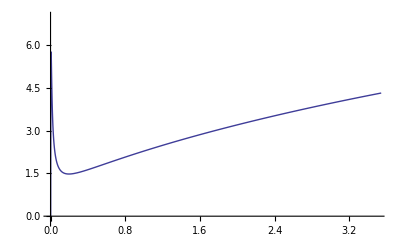

```mathematica
xm=0;
xM=3.5;
ym=-0.2;
yM=7.;
gr3BPS=ListPlot[dataBPS,Joined-> True, PlotRange-> {{xm,xM},{ym,yM}}]
```

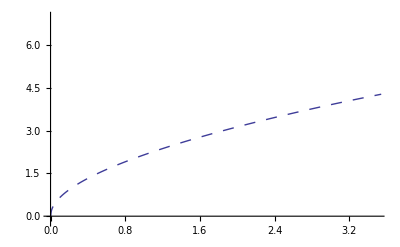

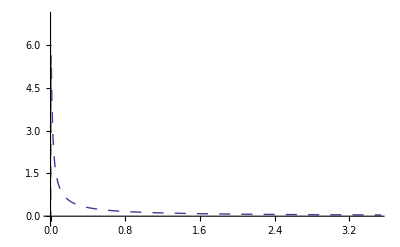

```mathematica
gr4E=ListPlot[dataBPSE,Joined->True,PlotStyle->Dashing[{0.02,0.02}],PlotRange->{{xm,xM},{ym,yM}}]
gr4I=ListPlot[dataBPSI,Joined->True,PlotStyle->Dashing[{0.02,0.02}],PlotRange->{{xm,xM},{ym,yM}}]
```

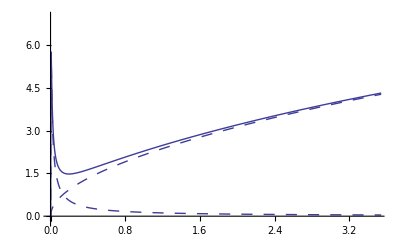

```mathematica
Show[gr3BPS,gr4E,gr4I,PlotRange-> {{xm,xM},{ym,yM}}]
```

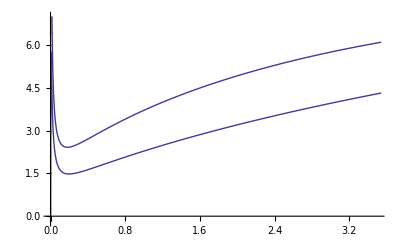

```mathematica
Show[gr3LP,gr3BPS]
```

#### E vs x and range R

```mathematica
dEdxEBPS=Interpolation[dataBPS];
```

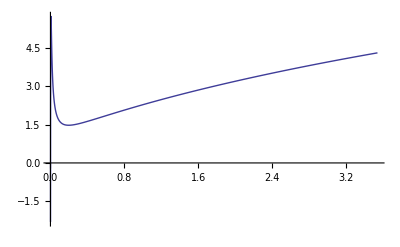

```mathematica
Plot[dEdxEBPS[e],{e,emin,emax}]
```

```mathematica
E0=emax;
dxEBPS[E_] :=1/dEdxEBPS[E]
xEBPS[E_]   := NIntegrate[1/dEdxEBPS[Ep],{Ep,E,E0},PrecisionGoal->Automatic]
```

```mathematica
FindRoot[dEdxEBPS[EE]==0,{EE,0.0.01}];
EzeroBPSa=EE /. %
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000794956} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

0.00144237

```mathematica
FindRoot[dEdxEBPS[EE]==0,{EE, EzeroBPSa}];
EzeroBPS=EE /. %
```

0.00144237

```mathematica
dEdxEBPS[EzeroBPS]
```

-2.72406×10^-18

```mathematica
eth=2*T/1000
dEdxEBPS[eth]
xEBPS[eth]
```

0.002

2.02736

1.3238

```mathematica
NN=1000;
E1=eth;
dE=(E0-E1)/NN;
dataExBPS=Table[{xEBPS[E],E},{E,E1,emax,dE}];
```

```mathematica
xy1=dataExBPS[[2]]
xy2=dataExBPS[[1]]
dxy=xy2-xy1
m=dxy[[2]]/dxy[[1]]
b=xy1[[2]]-m*xy1[[1]]
xRBPS=-b/m
```

{1.32299,0.005538}

{1.3238,0.002}

{0.000810244,-0.003538}

-4.36658

5.78248

1.32426

```mathematica
dataExBPS=Prepend[dataExBPS,{xRBPS,0}]
```

{{1.32426,0},{1.3238,0.002},{1.32299,0.005538},{1.32236,0.009076},{1.32165,0.012614},{1.32084,0.016152},{1.31993,0.01969},{1.31892,0.023228},{1.31781,0.026766},{1.31661,0.030304},{1.31533,0.033842},{1.31397,0.03738},{1.31253,0.040918},{1.31103,0.044456},{1.30946,0.047994},{1.30783,0.051532},{1.30614,0.05507},{1.3044,0.058608},{1.30261,0.062146},{1.30077,0.065684},{1.29889,0.069222},{1.29697,0.07276},{1.29501,0.076298},{1.29301,0.079836},{1.29098,0.083374},{1.28892,0.086912},{1.28683,0.09045},{1.28472,0.093988},{1.28258,0.097526},{1.28041,0.101064},{1.27823,0.104602},{1.27602,0.10814},{1.2738,0.111678},{1.27156,0.115216},{1.2693,0.118754},{1.26703,0.122292},{1.26474,0.12583},{1.26244,0.129368},{1.26013,0.132906},{1.25781,0.136444},{1.25548,0.139982},{1.25315,0.14352},{1.2508,0.147058},{1.24845,0.150596},{1.24609,0.154134},{1.24372,0.157672},{1.24135,0.16121},{1.23897,0.164748},{1.2366,0.168286},{1.23421,0.171824},{1.23183,0.175362},{1.22944,0.1789},{1.22705,0.182438},{1.22466,0.185976},{1.22227,0.189514},{1.21987,0.193052},{1.21748,0.19659},{1.21509,0.200128},{1.21269,0.203666},{1.2103,0.207204},{1.20791,0.210742},{1.20552,0.21428},{1.20313,0.217818},{1.20074,0.221356},{1.19835,0.224894},{1.19597,0.228432},{1.19359,0.23197},{1.19121,0.235508},{1.18883,0.239046},{1.18646,0.242584},{1.18409,0.246122},{1.18172,0.24966},{1.17936,0.253198},{1.177,0.256736},{1.17464,0.260274},{1.17228,0.263812},{1.16993,0.26735},{1.16759,0.270888},{1.16525,0.274426},{1.16291,0.277964},{1.16057,0.281502},{1.15824,0.28504},{1.15592,0.288578},{1.1536,0.292116},{1.15128,0.295654},{1.14896,0.299192},{1.14666,0.30273},{1.14435,0.306268},{1.14205,0.309806},{1.13976,0.313344},{1.13747,0.316882},{1.13518,0.32042},{1.1329,0.323958},{1.13063,0.327496},{1.12836,0.331034},{1.12609,0.334572},{1.12383,0.33811},{1.12157,0.341648},{1.11932,0.345186},{1.11708,0.348724},{1.11483,0.352262},{1.1126,0.3558},{1.11037,0.359338},{1.10814,0.362876},{1.10592,0.366414},{1.1037,0.369952},{1.10149,0.37349},{1.09928,0.377028},{1.09708,0.380566},{1.09488,0.384104},{1.09269,0.387642},{1.09051,0.39118},{1.08833,0.394718},{1.08615,0.398256},{1.08398,0.401794},{1.08181,0.405332},{1.07965,0.40887},{1.07749,0.412408},{1.07534,0.415946},{1.07319,0.419484},{1.07105,0.423022},{1.06892,0.42656},{1.06678,0.430098},{1.06466,0.433636},{1.06253,0.437174},{1.06042,0.440712},{1.0583,0.44425},{1.0562,0.447788},{1.05409,0.451326},{1.052,0.454864},{1.0499,0.458402},{1.04782,0.46194},{1.04573,0.465478},{1.04365,0.469016},{1.04158,0.472554},{1.03951,0.476092},{1.03745,0.47963},{1.03539,0.483168},{1.03333,0.486706},{1.03128,0.490244},{1.02924,0.493782},{1.0272,0.49732},{1.02516,0.500858},{1.02313,0.504396},{1.0211,0.507934},{1.01908,0.511472},{1.01706,0.51501},{1.01505,0.518548},{1.01304,0.522086},{1.01104,0.525624},{1.00904,0.529162},{1.00704,0.5327},{1.00505,0.536238},{1.00306,0.539776},{1.00108,0.543314},{0.999103,0.546852},{0.99713,0.55039},{0.995161,0.553928},{0.993197,0.557466},{0.991237,0.561004},{0.989281,0.564542},{0.987329,0.56808},{0.985382,0.571618},{0.983439,0.575156},{0.9815,0.578694},{0.979565,0.582232},{0.977635,0.58577},{0.975708,0.589308},{0.973786,0.592846},{0.971868,0.596384},{0.969954,0.599922},{0.968045,0.60346},{0.966139,0.606998},{0.964237,0.610536},{0.96234,0.614074},{0.960446,0.617612},{0.958557,0.62115},{0.956671,0.624688},{0.954789,0.628226},{0.952912,0.631764},{0.951038,0.635302},{0.949168,0.63884},{0.947302,0.642378},{0.94544,0.645916},{0.943582,0.649454},{0.941728,0.652992},{0.939877,0.65653},{0.93803,0.660068},{0.936187,0.663606},{0.934348,0.667144},{0.932513,0.670682},{0.930681,0.67422},{0.928853,0.677758},{0.927029,0.681296},{0.925208,0.684834},{0.923391,0.688372},{0.921578,0.69191},{0.919768,0.695448},{0.917962,0.698986},{0.91616,0.702524},{0.914361,0.706062},{0.912566,0.7096},{0.910774,0.713138},{0.908986,0.716676},{0.907201,0.720214},{0.90542,0.723752},{0.903642,0.72729},{0.901868,0.730828},{0.900097,0.734366},{0.89833,0.737904},{0.896566,0.741442},{0.894806,0.74498},{0.893049,0.748518},{0.891295,0.752056},{0.889544,0.755594},{0.887797,0.759132},{0.886054,0.76267},{0.884313,0.766208},{0.882576,0.769746},{0.880842,0.773284},{0.879112,0.776822},{0.877384,0.78036},{0.87566,0.783898},{0.87394,0.787436},{0.872222,0.790974},{0.870507,0.794512},{0.868796,0.79805},{0.867088,0.801588},{0.865383,0.805126},{0.863681,0.808664},{0.861983,0.812202},{0.860287,0.81574},{0.858595,0.819278},{0.856905,0.822816},{0.855219,0.826354},{0.853535,0.829892},{0.851855,0.83343},{0.850178,0.836968},{0.848504,0.840506},{0.846833,0.844044},{0.845164,0.847582},{0.843499,0.85112},{0.841837,0.854658},{0.840177,0.858196},{0.838521,0.861734},{0.836867,0.865272},{0.835217,0.86881},{0.833569,0.872348},{0.831924,0.875886},{0.830282,0.879424},{0.828643,0.882962},{0.827007,0.8865},{0.825374,0.890038},{0.823743,0.893576},{0.822115,0.897114},{0.82049,0.900652},{0.818868,0.90419},{0.817249,0.907728},{0.815632,0.911266},{0.814018,0.914804},{0.812407,0.918342},{0.810799,0.92188},{0.809193,0.925418},{0.80759,0.928956},{0.805989,0.932494},{0.804392,0.936032},{0.802797,0.93957},{0.801204,0.943108},{0.799615,0.946646},{0.798028,0.950184},{0.796443,0.953722},{0.794861,0.95726},{0.793282,0.960798},{0.791705,0.964336},{0.790131,0.967874},{0.78856,0.971412},{0.786991,0.97495},{0.785425,0.978488},{0.783861,0.982026},{0.782299,0.985564},{0.780741,0.989102},{0.779184,0.99264},{0.777631,0.996178},{0.776079,0.999716},{0.77453,1.00325},{0.772984,1.00679},{0.77144,1.01033},{0.769899,1.01387},{0.76836,1.01741},{0.766823,1.02094},{0.765289,1.02448},{0.763757,1.02802},{0.762228,1.03156},{0.760701,1.0351},{0.759176,1.03863},{0.757654,1.04217},{0.756134,1.04571},{0.754616,1.04925},{0.753101,1.05279},{0.751588,1.05632},{0.750078,1.05986},{0.748569,1.0634},{0.747063,1.06694},{0.74556,1.07048},{0.744058,1.07401},{0.742559,1.07755},{0.741062,1.08109},{0.739568,1.08463},{0.738075,1.08817},{0.736585,1.0917},{0.735098,1.09524},{0.733612,1.09878},{0.732129,1.10232},{0.730647,1.10586},{0.729168,1.10939},{0.727691,1.11293},{0.726217,1.11647},{0.724744,1.12001},{0.723274,1.12355},{0.721806,1.12708},{0.72034,1.13062},{0.718876,1.13416},{0.717414,1.1377},{0.715955,1.14124},{0.714497,1.14477},{0.713042,1.14831},{0.711589,1.15185},{0.710137,1.15539},{0.708688,1.15893},{0.707241,1.16246},{0.705796,1.166},{0.704353,1.16954},{0.702913,1.17308},{0.701474,1.17662},{0.700037,1.18015},{0.698602,1.18369},{0.69717,1.18723},{0.695739,1.19077},{0.69431,1.19431},{0.692884,1.19784},{0.691459,1.20138},{0.690036,1.20492},{0.688615,1.20846},{0.687197,1.212},{0.68578,1.21553},{0.684365,1.21907},{0.682952,1.22261},{0.681541,1.22615},{0.680132,1.22969},{0.678725,1.23322},{0.67732,1.23676},{0.675917,1.2403},{0.674516,1.24384},{0.673116,1.24738},{0.671719,1.25091},{0.670323,1.25445},{0.668929,1.25799},{0.667537,1.26153},{0.666147,1.26507},{0.664759,1.2686},{0.663373,1.27214},{0.661988,1.27568},{0.660606,1.27922},{0.659225,1.28276},{0.657846,1.28629},{0.656469,1.28983},{0.655094,1.29337},{0.65372,1.29691},{0.652349,1.30045},{0.650979,1.30398},{0.649611,1.30752},{0.648244,1.31106},{0.64688,1.3146},{0.645517,1.31814},{0.644156,1.32167},{0.642797,1.32521},{0.641439,1.32875},{0.640084,1.33229},{0.63873,1.33583},{0.637377,1.33936},{0.636027,1.3429},{0.634678,1.34644},{0.633331,1.34998},{0.631986,1.35352},{0.630642,1.35705},{0.6293,1.36059},{0.62796,1.36413},{0.626621,1.36767},{0.625284,1.37121},{0.623949,1.37474},{0.622616,1.37828},{0.621284,1.38182},{0.619954,1.38536},{0.618625,1.3889},{0.617298,1.39243},{0.615973,1.39597},{0.61465,1.39951},{0.613328,1.40305},{0.612007,1.40659},{0.610689,1.41012},{0.609372,1.41366},{0.608056,1.4172},{0.606742,1.42074},{0.60543,1.42428},{0.604119,1.42781},{0.60281,1.43135},{0.601503,1.43489},{0.600197,1.43843},{0.598893,1.44197},{0.59759,1.4455},{0.596289,1.44904},{0.594989,1.45258},{0.593691,1.45612},{0.592395,1.45966},{0.5911,1.46319},{0.589807,1.46673},{0.588515,1.47027},{0.587224,1.47381},{0.585936,1.47735},{0.584648,1.48088},{0.583363,1.48442},{0.582078,1.48796},{0.580796,1.4915},{0.579515,1.49504},{0.578235,1.49857},{0.576957,1.50211},{0.57568,1.50565},{0.574405,1.50919},{0.573131,1.51273},{0.571859,1.51626},{0.570588,1.5198},{0.569319,1.52334},{0.568051,1.52688},{0.566784,1.53042},{0.565519,1.53395},{0.564256,1.53749},{0.562994,1.54103},{0.561733,1.54457},{0.560474,1.54811},{0.559216,1.55164},{0.55796,1.55518},{0.556705,1.55872},{0.555452,1.56226},{0.5542,1.5658},{0.552949,1.56933},{0.5517,1.57287},{0.550452,1.57641},{0.549205,1.57995},{0.54796,1.58349},{0.546717,1.58702},{0.545474,1.59056},{0.544234,1.5941},{0.542994,1.59764},{0.541756,1.60118},{0.540519,1.60471},{0.539284,1.60825},{0.53805,1.61179},{0.536817,1.61533},{0.535586,1.61887},{0.534356,1.6224},{0.533127,1.62594},{0.5319,1.62948},{0.530674,1.63302},{0.529449,1.63656},{0.528226,1.64009},{0.527004,1.64363},{0.525783,1.64717},{0.524564,1.65071},{0.523346,1.65425},{0.522129,1.65778},{0.520914,1.66132},{0.5197,1.66486},{0.518487,1.6684},{0.517276,1.67194},{0.516065,1.67547},{0.514857,1.67901},{0.513649,1.68255},{0.512443,1.68609},{0.511237,1.68963},{0.510034,1.69316},{0.508831,1.6967},{0.50763,1.70024},{0.50643,1.70378},{0.505231,1.70732},{0.504034,1.71085},{0.502837,1.71439},{0.501642,1.71793},{0.500449,1.72147},{0.499256,1.72501},{0.498065,1.72854},{0.496875,1.73208},{0.495686,1.73562},{0.494499,1.73916},{0.493312,1.7427},{0.492127,1.74623},{0.490943,1.74977},{0.489761,1.75331},{0.488579,1.75685},{0.487399,1.76039},{0.48622,1.76392},{0.485042,1.76746},{0.483865,1.771},{0.48269,1.77454},{0.481515,1.77808},{0.480342,1.78161},{0.47917,1.78515},{0.478,1.78869},{0.47683,1.79223},{0.475662,1.79577},{0.474494,1.7993},{0.473328,1.80284},{0.472164,1.80638},{0.471,1.80992},{0.469837,1.81346},{0.468676,1.81699},{0.467516,1.82053},{0.466357,1.82407},{0.465199,1.82761},{0.464042,1.83115},{0.462886,1.83468},{0.461732,1.83822},{0.460578,1.84176},{0.459426,1.8453},{0.458275,1.84884},{0.457125,1.85237},{0.455976,1.85591},{0.454828,1.85945},{0.453681,1.86299},{0.452536,1.86653},{0.451391,1.87006},{0.450248,1.8736},{0.449106,1.87714},{0.447965,1.88068},{0.446825,1.88422},{0.445686,1.88775},{0.444548,1.89129},{0.443411,1.89483},{0.442276,1.89837},{0.441141,1.90191},{0.440007,1.90544},{0.438875,1.90898},{0.437744,1.91252},{0.436613,1.91606},{0.435484,1.9196},{0.434356,1.92313},{0.433229,1.92667},{0.432103,1.93021},{0.430978,1.93375},{0.429854,1.93729},{0.428731,1.94082},{0.42761,1.94436},{0.426489,1.9479},{0.425369,1.95144},{0.424251,1.95498},{0.423133,1.95851},{0.422016,1.96205},{0.420901,1.96559},{0.419786,1.96913},{0.418673,1.97267},{0.41756,1.9762},{0.416449,1.97974},{0.415339,1.98328},{0.414229,1.98682},{0.413121,1.99036},{0.412014,1.99389},{0.410907,1.99743},{0.409802,2.00097},{0.408698,2.00451},{0.407594,2.00805},{0.406492,2.01158},{0.405391,2.01512},{0.40429,2.01866},{0.403191,2.0222},{0.402093,2.02574},{0.400995,2.02927},{0.399899,2.03281},{0.398804,2.03635},{0.397709,2.03989},{0.396616,2.04343},{0.395524,2.04696},{0.394432,2.0505},{0.393342,2.05404},{0.392252,2.05758},{0.391164,2.06112},{0.390076,2.06465},{0.388989,2.06819},{0.387904,2.07173},{0.386819,2.07527},{0.385735,2.07881},{0.384653,2.08234},{0.383571,2.08588},{0.38249,2.08942},{0.38141,2.09296},{0.380331,2.0965},{0.379253,2.10003},{0.378176,2.10357},{0.3771,2.10711},{0.376024,2.11065},{0.37495,2.11419},{0.373877,2.11772},{0.372804,2.12126},{0.371733,2.1248},{0.370662,2.12834},{0.369593,2.13188},{0.368524,2.13541},{0.367456,2.13895},{0.366389,2.14249},{0.365323,2.14603},{0.364258,2.14957},{0.363194,2.1531},{0.362131,2.15664},{0.361068,2.16018},{0.360007,2.16372},{0.358946,2.16726},{0.357887,2.17079},{0.356828,2.17433},{0.35577,2.17787},{0.354713,2.18141},{0.353657,2.18495},{0.352602,2.18848},{0.351547,2.19202},{0.350494,2.19556},{0.349441,2.1991},{0.34839,2.20264},{0.347339,2.20617},{0.346289,2.20971},{0.34524,2.21325},{0.344192,2.21679},{0.343145,2.22033},{0.342098,2.22386},{0.341053,2.2274},{0.340008,2.23094},{0.338964,2.23448},{0.337921,2.23802},{0.336879,2.24155},{0.335838,2.24509},{0.334797,2.24863},{0.333758,2.25217},{0.332719,2.25571},{0.331681,2.25924},{0.330644,2.26278},{0.329608,2.26632},{0.328573,2.26986},{0.327538,2.2734},{0.326505,2.27693},{0.325472,2.28047},{0.32444,2.28401},{0.323409,2.28755},{0.322378,2.29109},{0.321349,2.29462},{0.32032,2.29816},{0.319292,2.3017},{0.318265,2.30524},{0.317239,2.30878},{0.316214,2.31231},{0.315189,2.31585},{0.314166,2.31939},{0.313143,2.32293},{0.312121,2.32647},{0.311099,2.33},{0.310079,2.33354},{0.309059,2.33708},{0.30804,2.34062},{0.307022,2.34416},{0.306005,2.34769},{0.304989,2.35123},{0.303973,2.35477},{0.302958,2.35831},{0.301944,2.36185},{0.300931,2.36538},{0.299918,2.36892},{0.298907,2.37246},{0.297896,2.376},{0.296886,2.37954},{0.295876,2.38307},{0.294868,2.38661},{0.29386,2.39015},{0.292853,2.39369},{0.291847,2.39723},{0.290841,2.40076},{0.289837,2.4043},{0.288833,2.40784},{0.28783,2.41138},{0.286827,2.41492},{0.285826,2.41845},{0.284825,2.42199},{0.283825,2.42553},{0.282826,2.42907},{0.281827,2.43261},{0.280829,2.43614},{0.279832,2.43968},{0.278836,2.44322},{0.277841,2.44676},{0.276846,2.4503},{0.275852,2.45383},{0.274859,2.45737},{0.273866,2.46091},{0.272874,2.46445},{0.271883,2.46799},{0.270893,2.47152},{0.269904,2.47506},{0.268915,2.4786},{0.267927,2.48214},{0.26694,2.48568},{0.265953,2.48921},{0.264967,2.49275},{0.263982,2.49629},{0.262998,2.49983},{0.262014,2.50337},{0.261031,2.5069},{0.260049,2.51044},{0.259068,2.51398},{0.258087,2.51752},{0.257107,2.52106},{0.256128,2.52459},{0.255149,2.52813},{0.254171,2.53167},{0.253194,2.53521},{0.252218,2.53875},{0.251242,2.54228},{0.250267,2.54582},{0.249293,2.54936},{0.248319,2.5529},{0.247346,2.55644},{0.246374,2.55997},{0.245403,2.56351},{0.244432,2.56705},{0.243462,2.57059},{0.242493,2.57413},{0.241524,2.57766},{0.240556,2.5812},{0.239589,2.58474},{0.238622,2.58828},{0.237657,2.59182},{0.236691,2.59535},{0.235727,2.59889},{0.234763,2.60243},{0.2338,2.60597},{0.232838,2.60951},{0.231876,2.61304},{0.230915,2.61658},{0.229954,2.62012},{0.228995,2.62366},{0.228036,2.6272},{0.227077,2.63073},{0.22612,2.63427},{0.225163,2.63781},{0.224206,2.64135},{0.223251,2.64489},{0.222296,2.64842},{0.221342,2.65196},{0.220388,2.6555},{0.219435,2.65904},{0.218483,2.66258},{0.217531,2.66611},{0.21658,2.66965},{0.21563,2.67319},{0.21468,2.67673},{0.213731,2.68027},{0.212783,2.6838},{0.211835,2.68734},{0.210888,2.69088},{0.209942,2.69442},{0.208996,2.69796},{0.208051,2.70149},{0.207107,2.70503},{0.206163,2.70857},{0.20522,2.71211},{0.204278,2.71565},{0.203336,2.71918},{0.202395,2.72272},{0.201454,2.72626},{0.200514,2.7298},{0.199575,2.73334},{0.198636,2.73687},{0.197698,2.74041},{0.196761,2.74395},{0.195824,2.74749},{0.194888,2.75103},{0.193953,2.75456},{0.193018,2.7581},{0.192084,2.76164},{0.19115,2.76518},{0.190217,2.76872},{0.189285,2.77225},{0.188353,2.77579},{0.187422,2.77933},{0.186492,2.78287},{0.185562,2.78641},{0.184633,2.78994},{0.183705,2.79348},{0.182777,2.79702},{0.181849,2.80056},{0.180923,2.8041},{0.179997,2.80763},{0.179071,2.81117},{0.178146,2.81471},{0.177222,2.81825},{0.176298,2.82179},{0.175375,2.82532},{0.174453,2.82886},{0.173531,2.8324},{0.17261,2.83594},{0.171689,2.83948},{0.170769,2.84301},{0.16985,2.84655},{0.168931,2.85009},{0.168013,2.85363},{0.167095,2.85717},{0.166178,2.8607},{0.165262,2.86424},{0.164346,2.86778},{0.163431,2.87132},{0.162516,2.87486},{0.161602,2.87839},{0.160689,2.88193},{0.159776,2.88547},{0.158864,2.88901},{0.157952,2.89255},{0.157041,2.89608},{0.15613,2.89962},{0.155221,2.90316},{0.154311,2.9067},{0.153402,2.91024},{0.152494,2.91377},{0.151587,2.91731},{0.15068,2.92085},{0.149773,2.92439},{0.148867,2.92793},{0.147962,2.93146},{0.147057,2.935},{0.146153,2.93854},{0.14525,2.94208},{0.144347,2.94562},{0.143444,2.94915},{0.142542,2.95269},{0.141641,2.95623},{0.14074,2.95977},{0.13984,2.96331},{0.138941,2.96684},{0.138042,2.97038},{0.137143,2.97392},{0.136245,2.97746},{0.135348,2.981},{0.134451,2.98453},{0.133555,2.98807},{0.132659,2.99161},{0.131764,2.99515},{0.13087,2.99869},{0.129976,3.00222},{0.129082,3.00576},{0.128189,3.0093},{0.127297,3.01284},{0.126405,3.01638},{0.125514,3.01991},{0.124623,3.02345},{0.123733,3.02699},{0.122844,3.03053},{0.121955,3.03407},{0.121066,3.0376},{0.120178,3.04114},{0.119291,3.04468},{0.118404,3.04822},{0.117518,3.05176},{0.116632,3.05529},{0.115747,3.05883},{0.114862,3.06237},{0.113978,3.06591},{0.113094,3.06945},{0.112211,3.07298},{0.111328,3.07652},{0.110446,3.08006},{0.109565,3.0836},{0.108684,3.08714},{0.107804,3.09067},{0.106924,3.09421},{0.106044,3.09775},{0.105165,3.10129},{0.104287,3.10483},{0.103409,3.10836},{0.102532,3.1119},{0.101655,3.11544},{0.100779,3.11898},{0.0999034,3.12252},{0.0990282,3.12605},{0.0981536,3.12959},{0.0972794,3.13313},{0.0964058,3.13667},{0.0955327,3.14021},{0.0946601,3.14374},{0.0937881,3.14728},{0.0929165,3.15082},{0.0920455,3.15436},{0.091175,3.1579},{0.090305,3.16143},{0.0894355,3.16497},{0.0885665,3.16851},{0.087698,3.17205},{0.08683,3.17559},{0.0859626,3.17912},{0.0850956,3.18266},{0.0842292,3.1862},{0.0833632,3.18974},{0.0824978,3.19328},{0.0816328,3.19681},{0.0807684,3.20035},{0.0799045,3.20389},{0.0790411,3.20743},{0.0781781,3.21097},{0.0773157,3.2145},{0.0764538,3.21804},{0.0755923,3.22158},{0.0747314,3.22512},{0.0738709,3.22866},{0.073011,3.23219},{0.0721516,3.23573},{0.0712926,3.23927},{0.0704341,3.24281},{0.0695762,3.24635},{0.0687187,3.24988},{0.0678617,3.25342},{0.0670052,3.25696},{0.0661492,3.2605},{0.0652936,3.26404},{0.0644386,3.26757},{0.063584,3.27111},{0.06273,3.27465},{0.0618764,3.27819},{0.0610233,3.28173},{0.0601707,3.28526},{0.0593185,3.2888},{0.0584669,3.29234},{0.0576157,3.29588},{0.056765,3.29942},{0.0559148,3.30295},{0.055065,3.30649},{0.0542158,3.31003},{0.053367,3.31357},{0.0525187,3.31711},{0.0516708,3.32064},{0.0508235,3.32418},{0.0499766,3.32772},{0.0491302,3.33126},{0.0482842,3.3348},{0.0474387,3.33833},{0.0465937,3.34187},{0.0457492,3.34541},{0.0449051,3.34895},{0.0440615,3.35249},{0.0432184,3.35602},{0.0423757,3.35956},{0.0415335,3.3631},{0.0406918,3.36664},{0.0398505,3.37018},{0.0390097,3.37371},{0.0381693,3.37725},{0.0373294,3.38079},{0.03649,3.38433},{0.035651,3.38787},{0.0348125,3.3914},{0.0339745,3.39494},{0.0331369,3.39848},{0.0322998,3.40202},{0.0314631,3.40556},{0.0306268,3.40909},{0.0297911,3.41263},{0.0289558,3.41617},{0.0281209,3.41971},{0.0272865,3.42325},{0.0264525,3.42678},{0.025619,3.43032},{0.024786,3.43386},{0.0239534,3.4374},{0.0231212,3.44094},{0.0222895,3.44447},{0.0214582,3.44801},{0.0206274,3.45155},{0.019797,3.45509},{0.0189671,3.45863},{0.0181376,3.46216},{0.0173086,3.4657},{0.01648,3.46924},{0.0156518,3.47278},{0.0148241,3.47632},{0.0139968,3.47985},{0.01317,3.48339},{0.0123436,3.48693},{0.0115177,3.49047},{0.0106922,3.49401},{0.00986708,3.49754},{0.00904244,3.50108},{0.00821823,3.50462},{0.00739446,3.50816},{0.00657112,3.5117},{0.00574822,3.51523},{0.00492575,3.51877},{0.00410372,3.52231},{0.00328211,3.52585},{0.00246094,3.52939},{0.0016402,3.53292},{0.000819884,3.53646},{-1.02885×10^-16,3.54}}

```mathematica
ExBPS=Interpolation[dataExBPS];
```

```mathematica
ExBPS[xRBPS]
```

0.

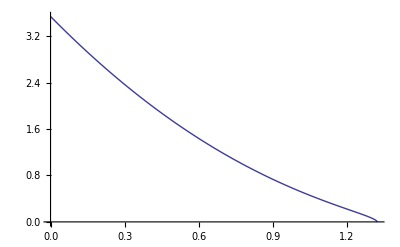

```mathematica
grExBPS=ListPlot[dataExBPS,Joined->True]
```

#### dE/dx vs E: dEdxEBPS

```mathematica
dEdxEeBPS =Interpolation[dataBPSE];
dEdxEiBPS =Interpolation[dataBPSI];
```

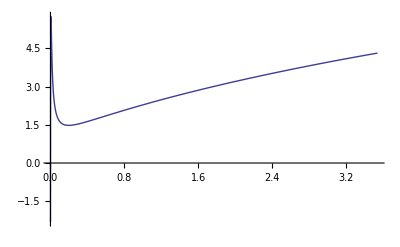

```mathematica
grdEdxEBPS=Plot[dEdxEBPS[e],{e,emin,emax},PlotPoints->10000,PlotRange->All]
```

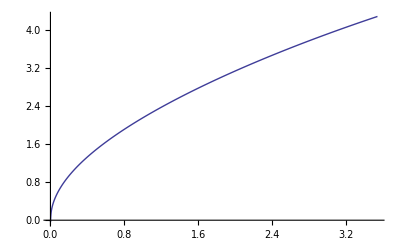

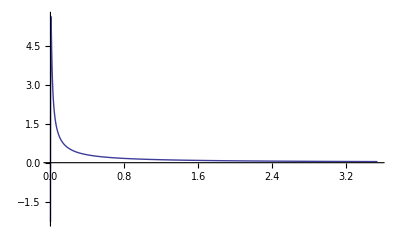

```mathematica
grdEdxEeBPS=Plot[dEdxEeBPS[e],{e,emin,emax},PlotPoints->1000,PlotRange->All]
grdEdxEiBPS=Plot[dEdxEiBPS[e],{e,emin,emax},PlotPoints->1000,PlotRange->All]
```

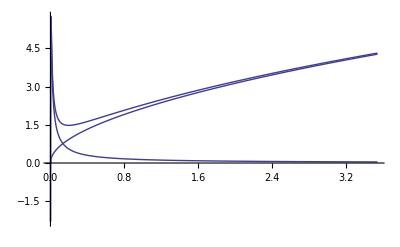

```mathematica
grdEdxEeiBPS=Show[grdEdxEeBPS,grdEdxEiBPS,grdEdxEBPS]
```

#### dE/dx vs x: dEdxx BPS

```mathematica
dEdxxBPS[x_] := dEdxEBPS[ExBPS[x]]
dEdxxeBPS[x_] := dEdxEeBPS[ExBPS[x]]
dEdxxiBPS[x_] := dEdxEiBPS[ExBPS[x]]
```

```mathematica
xRBPS
xRBPSmax=FindRoot[dEdxxBPS[x]==0,{x,xRBPS}][[1,2]]
```

1.32426

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000773995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

1.32393

```mathematica
dEdxxBPS[xRBPS]
dEdxxBPS[xRBPSmax]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-12.7848

-3.92451×10^-9

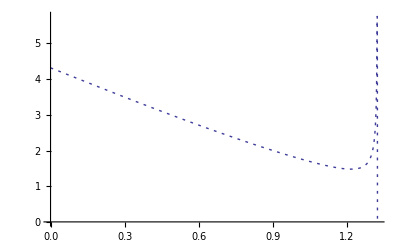

```mathematica
grdEdxxBPS=Plot[dEdxxBPS[x],{x,0,xRBPSmax},PlotStyle->Dashing[{0.005,0.01}],
PlotPoints->1000,PlotRange->All]
```

```mathematica
x0=0.6;
NIntegrate[dEdxxBPS[x],{x,0,x0},MaxRecursion->10]
NIntegrate[dEdxxBPS[x],{x,x0,xRBPSmax},MaxRecursion->10]
% + %%
```

2.10104

1.43733

3.53836

```mathematica
100*(%-E0)/E0
```

-0.0461989

```mathematica
100*eth/E0
```

0.0564972

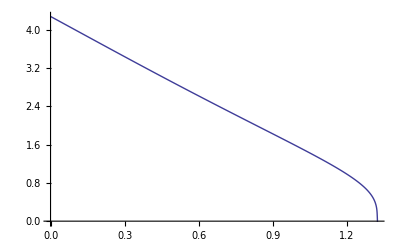

```mathematica
grdEdxxeBPS=Plot[dEdxxeBPS[x] ,{x,0,xRBPSmax},PlotPoints->1000,PlotPoints->All]
```

```mathematica
Ee=NIntegrate[dEdxxeBPS[x],{x,0,xRBPSmax}]
```

3.2412

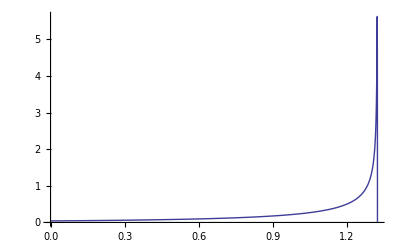

```mathematica
grdEdxxiBPS=Plot[dEdxxiBPS[x],{x,0,xRBPSmax},PlotPoints->1000,PlotRange->All]
```

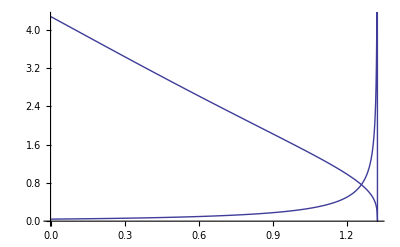

```mathematica
grdEdxxeiBPS=Show[grdEdxxeBPS,grdEdxxiBPS]
```

```mathematica
xRBPSmax
```

1.32393

```mathematica
x1=0.6;
NIntegrate[dEdxxiBPS[x],{x,0,x1},MaxRecursion->10]
NIntegrate[dEdxxiBPS[x],{x,x1,xRBPSmax},MaxRecursion->10]
Ei=% + %%
```

0.0383759

0.258786

0.297162

```mathematica
{Ee,Ei,Ee+Ei,E0}
```

{3.2412,0.297162,3.53836,3.54}

```mathematica
100*(E0-Ee-Ei)/E0
```

0.0462048

### LP cf BPS: Figs

```mathematica
id
```

A

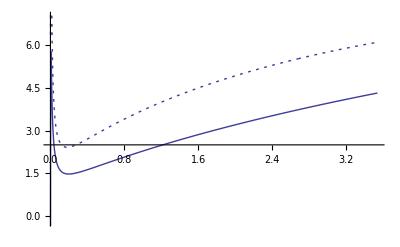

```mathematica
grdEdxELPBPS=Show[grdEdxELP,grdEdxEBPS,PlotRange->{ym,yM}]
```

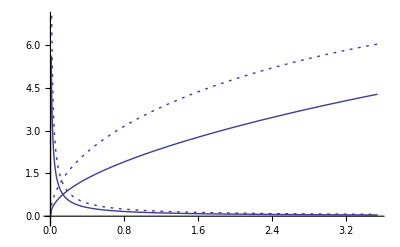

```mathematica
grdEdxEeiLPBPS=Show[grdEdxEeLP,grdEdxEiLP,
grdEdxEeBPS,grdEdxEiBPS,PlotRange->{ym,yM}]
```

```mathematica
NN=300;
Emin=emin;
Emax=0.2;
dE=(Emax-Emin)/NN;
data1=
Table[{EE,dEdxELP[EE],dEdxEeLP[EE],dEdxEiLP[EE],
dEdxEBPS[EE],dEdxEeBPS[EE],dEdxEiBPS[EE]},{EE,Emin,Emax,dE}];


NN=100;
Emin=Emax;
Emax=emax;
dE=(Emax-Emin)/NN;
data2=
Table[{EE,dEdxELP[EE],dEdxEeLP[EE],dEdxEiLP[EE],
dEdxEBPS[EE],dEdxEeBPS[EE],dEdxEiBPS[EE]},{EE,Emin,Emax,dE}];

data=Join[data1,data2]

(*
Export["LPvsBPS.dEdxE.aDT300127.dat",data,"Table",ConversionOptions-> {"FormatType"-> FortranForm}];
*)
```

{{0.001,6.35448,0.080791,6.27369,-2.31232,-0.0355488,-2.27677},{0.00166333,10.7394,0.121023,10.6184,0.897752,-0.0060833,0.903836},{0.00232667,13.2816,0.151688,13.1299,2.90188,0.0205499,2.88133},{0.00299,14.0172,0.177349,13.8399,4.17054,0.0455672,4.12497},{0.00365333,14.0112,0.199833,13.8114,4.95061,0.0686491,4.88196},{0.00431667,13.6524,0.220075,13.4323,5.40478,0.0894645,5.31532},{0.00498,13.1318,0.23863,12.8931,5.64377,0.107962,5.53581},{0.00564333,12.5493,0.255858,12.2935,5.74206,0.124319,5.61774},{0.00630667,11.958,0.272006,11.686,5.74916,0.138821,5.61034},{0.00697,11.3853,0.287253,11.0981,5.69785,0.151767,5.54608},{0.00763333,10.8447,0.301735,10.543,5.60982,0.163432,5.44638},{0.00829667,10.3417,0.315555,10.0262,5.49951,0.174046,5.32546},{0.00896,9.87761,0.328798,9.54881,5.37655,0.183797,5.19275},{0.00962333,9.45119,0.341528,9.10966,5.24735,0.192835,5.05452},{0.0102867,9.06016,0.353802,8.70636,5.1162,0.20128,4.91492},{0.01095,8.70172,0.365664,8.33606,4.98591,0.209227,4.77668},{0.0116133,8.37294,0.377154,7.99578,4.8583,0.216752,4.64155},{0.0122767,8.07094,0.388305,7.68264,4.73451,0.223916,4.5106},{0.01294,7.79306,0.399144,7.39391,4.61523,0.230768,4.38446},{0.0136033,7.53684,0.409697,7.12714,4.50082,0.237348,4.26347},{0.0142667,7.30007,0.419985,6.88009,4.39141,0.243689,4.14772},{0.01493,7.08079,0.430026,6.65076,4.28702,0.249818,4.03721},{0.0155933,6.87724,0.439838,6.4374,4.18755,0.255757,3.9318},{0.0162567,6.68786,0.449436,6.23842,4.09285,0.261525,3.83132},{0.01692,6.51128,0.458833,6.05245,4.00271,0.267138,3.73558},{0.0175833,6.34629,0.468041,5.87825,3.91694,0.27261,3.64433},{0.0182467,6.1918,0.477071,5.71473,3.8353,0.277953,3.55735},{0.01891,6.04687,0.485934,5.56094,3.75757,0.283175,3.4744},{0.0195733,5.91065,0.494637,5.41602,3.68354,0.288288,3.39525},{0.0202367,5.78239,0.503189,5.2792,3.61298,0.293297,3.31968},{0.0209,5.66142,0.511598,5.14982,3.54569,0.29821,3.24748},{0.0215633,5.54714,0.519871,5.02727,3.48149,0.303033,3.17846},{0.0222267,5.43901,0.528014,4.911,3.42018,0.307771,3.11241},{0.02289,5.33656,0.536033,4.80053,3.3616,0.31243,3.04917},{0.0235533,5.23936,0.543934,4.69543,3.30558,0.317013,2.98857},{0.0242167,5.14701,0.551721,4.59529,3.25197,0.321524,2.93045},{0.02488,5.05917,0.559399,4.49977,3.20064,0.325968,2.87467},{0.0255433,4.97551,0.566974,4.40854,3.15144,0.330347,2.8211},{0.0262067,4.89575,0.574448,4.3213,3.10427,0.334664,2.76961},{0.02687,4.81963,0.581825,4.2378,3.059,0.338923,2.72008},{0.0275333,4.7469,0.58911,4.15779,3.01553,0.343125,2.6724},{0.0281967,4.67735,0.596306,4.08104,2.97375,0.347274,2.62648},{0.02886,4.61078,0.603416,4.00736,2.93359,0.35137,2.58222},{0.0295233,4.547,0.610443,3.93656,2.89494,0.355417,2.53953},{0.0301867,4.48585,0.617389,3.86846,2.85774,0.359416,2.49832},{0.03085,4.42717,0.624258,3.80291,2.8219,0.36337,2.45853},{0.0315133,4.37081,0.631051,3.73976,2.78736,0.367278,2.42008},{0.0321767,4.31665,0.637772,3.67888,2.75405,0.371144,2.3829},{0.03284,4.26457,0.644423,3.62015,2.72189,0.374969,2.34692},{0.0335033,4.21444,0.651006,3.56344,2.69086,0.378754,2.31211},{0.0341667,4.16617,0.657522,3.50865,2.66089,0.3825,2.27839},{0.03483,4.11966,0.663974,3.45569,2.63192,0.386209,2.24572},{0.0354933,4.07482,0.670364,3.40445,2.60392,0.389882,2.21403},{0.0361567,4.03155,0.676693,3.35486,2.57683,0.393519,2.18331},{0.03682,3.98979,0.682963,3.30683,2.55061,0.397122,2.15349},{0.0374833,3.94946,0.689176,3.26029,2.52523,0.400693,2.12453},{0.0381467,3.91049,0.695333,3.21516,2.50064,0.404231,2.09641},{0.03881,3.87282,0.701435,3.17138,2.47682,0.407737,2.06909},{0.0394733,3.83638,0.707485,3.1289,2.45373,0.411214,2.04251},{0.0401367,3.80113,0.713483,3.08764,2.43133,0.414661,2.01667},{0.0408,3.76699,0.719431,3.04756,2.40961,0.418079,1.99153},{0.0414633,3.73394,0.72533,3.00861,2.38852,0.421469,1.96706},{0.0421267,3.70191,0.731181,2.97073,2.36805,0.424831,1.94322},{0.04279,3.67086,0.736986,2.93388,2.34818,0.428167,1.92001},{0.0434533,3.64076,0.742745,2.89802,2.32887,0.431477,1.89739},{0.0441167,3.61156,0.748459,2.86311,2.3101,0.434762,1.87534},{0.04478,3.58323,0.754129,2.8291,2.29185,0.438022,1.85383},{0.0454433,3.55573,0.759757,2.79597,2.27412,0.441257,1.83286},{0.0461067,3.52902,0.765344,2.76368,2.25686,0.444469,1.81239},{0.04677,3.50308,0.770889,2.73219,2.24007,0.447658,1.79241},{0.0474333,3.47788,0.776395,2.70148,2.22373,0.450824,1.7729},{0.0480967,3.45338,0.781862,2.67152,2.20782,0.453968,1.75385},{0.04876,3.42956,0.787291,2.64227,2.19233,0.457091,1.73524},{0.0494233,3.40639,0.792682,2.61371,2.17724,0.460192,1.71704},{0.0500867,3.38386,0.798036,2.58582,2.16253,0.463273,1.69926},{0.05075,3.36193,0.803355,2.55858,2.14821,0.466333,1.68187},{0.0514133,3.34059,0.808638,2.53195,2.13424,0.469373,1.66487},{0.0520767,3.31981,0.813887,2.50592,2.12062,0.472394,1.64823},{0.05274,3.29957,0.819102,2.48047,2.10734,0.475396,1.63194},{0.0534033,3.27986,0.824284,2.45558,2.09439,0.478379,1.61601},{0.0540667,3.26066,0.829433,2.43123,2.08175,0.481343,1.6004},{0.05473,3.24194,0.83455,2.40739,2.06941,0.48429,1.58512},{0.0553933,3.2237,0.839635,2.38407,2.05737,0.487219,1.57015},{0.0560567,3.20592,0.84469,2.36123,2.04562,0.49013,1.55549},{0.05672,3.18858,0.849715,2.33886,2.03414,0.493025,1.54112},{0.0573833,3.17166,0.854709,2.31695,2.02293,0.495903,1.52703},{0.0580467,3.15516,0.859675,2.29549,2.01198,0.498764,1.51322},{0.05871,3.13906,0.864612,2.27445,2.00129,0.501609,1.49968},{0.0593733,3.12335,0.86952,2.25383,1.99083,0.504439,1.48639},{0.0600367,3.10801,0.874401,2.23361,1.98061,0.507252,1.47336},{0.0607,3.09304,0.879254,2.21378,1.97063,0.510051,1.46058},{0.0613633,3.07842,0.884081,2.19434,1.96086,0.512834,1.44803},{0.0620267,3.06414,0.888881,2.17526,1.95131,0.515602,1.43571},{0.06269,3.05019,0.893655,2.15654,1.94198,0.518356,1.42362},{0.0633533,3.03657,0.898403,2.13816,1.93284,0.521096,1.41175},{0.0640167,3.02326,0.903126,2.12013,1.92391,0.523821,1.40008},{0.06468,3.01025,0.907825,2.10242,1.91516,0.526533,1.38863},{0.0653433,2.99753,0.912499,2.08503,1.90661,0.52923,1.37738},{0.0660067,2.9851,0.917149,2.06796,1.89823,0.531915,1.36632},{0.06667,2.97295,0.921775,2.05118,1.89004,0.534586,1.35545},{0.0673333,2.96107,0.926378,2.0347,1.88201,0.537244,1.34477},{0.0679967,2.94946,0.930958,2.0185,1.87416,0.539889,1.33427},{0.06866,2.9381,0.935516,2.00258,1.86646,0.542522,1.32394},{0.0693233,2.92698,0.940051,1.98693,1.85893,0.545142,1.31379},{0.0699867,2.91611,0.944564,1.97155,1.85155,0.547749,1.3038},{0.07065,2.90547,0.949055,1.95642,1.84432,0.550345,1.29398},{0.0713133,2.89506,0.953525,1.94154,1.83724,0.552929,1.28431},{0.0719767,2.88488,0.957974,1.9269,1.8303,0.555501,1.2748},{0.07264,2.87491,0.962402,1.91251,1.8235,0.558061,1.26544},{0.0733033,2.86515,0.96681,1.89834,1.81684,0.56061,1.25623},{0.0739667,2.8556,0.971198,1.8844,1.81031,0.563147,1.24716},{0.07463,2.84625,0.975565,1.87068,1.80391,0.565674,1.23823},{0.0752933,2.83709,0.979913,1.85718,1.79763,0.568189,1.22944},{0.0759567,2.82813,0.984242,1.84389,1.79148,0.570694,1.22078},{0.07662,2.81935,0.988551,1.8308,1.78545,0.573188,1.21226},{0.0772833,2.81075,0.992841,1.81791,1.77953,0.575671,1.20386},{0.0779467,2.80233,0.997113,1.80522,1.77373,0.578144,1.19558},{0.07861,2.79408,1.00137,1.79272,1.76804,0.580607,1.18743},{0.0792733,2.786,1.0056,1.7804,1.76246,0.583059,1.1794},{0.0799367,2.77809,1.00982,1.76827,1.75699,0.585502,1.17148},{0.0806,2.77033,1.01402,1.75631,1.75162,0.587934,1.16368},{0.0812633,2.76273,1.0182,1.74453,1.74635,0.590357,1.15599},{0.0819267,2.75528,1.02236,1.73292,1.74118,0.59277,1.14841},{0.08259,2.74799,1.02651,1.72148,1.73611,0.595174,1.14093},{0.0832533,2.74084,1.03064,1.71019,1.73113,0.597568,1.13356},{0.0839167,2.73383,1.03476,1.69907,1.72625,0.599953,1.12629},{0.08458,2.72696,1.03885,1.6881,1.72145,0.602329,1.11913},{0.0852433,2.72022,1.04293,1.67729,1.71675,0.604696,1.11205},{0.0859067,2.71362,1.047,1.66662,1.71213,0.607054,1.10508},{0.08657,2.70715,1.05105,1.6561,1.7076,0.609402,1.0982},{0.0872333,2.70081,1.05508,1.64573,1.70315,0.611743,1.09141},{0.0878967,2.69459,1.0591,1.63549,1.69878,0.614074,1.08471},{0.08856,2.68849,1.0631,1.62539,1.69449,0.616397,1.0781},{0.0892233,2.68251,1.06709,1.61542,1.69028,0.618711,1.07157},{0.0898867,2.67665,1.07106,1.60559,1.68615,0.621017,1.06513},{0.09055,2.6709,1.07502,1.59588,1.68209,0.623315,1.05877},{0.0912133,2.66526,1.07896,1.5863,1.6781,0.625605,1.0525},{0.0918767,2.65974,1.08289,1.57685,1.67419,0.627886,1.0463},{0.09254,2.65432,1.0868,1.56751,1.67034,0.63016,1.04018},{0.0932033,2.649,1.0907,1.5583,1.66657,0.632425,1.03414},{0.0938667,2.64379,1.09459,1.5492,1.66286,0.634683,1.02818},{0.09453,2.63867,1.09846,1.54021,1.65922,0.636933,1.02228},{0.0951933,2.63366,1.10232,1.53134,1.65564,0.639175,1.01646},{0.0958567,2.62874,1.10616,1.52258,1.65212,0.64141,1.01071},{0.09652,2.62391,1.10999,1.51392,1.64867,0.643638,1.00503},{0.0971833,2.61918,1.11381,1.50537,1.64528,0.645857,0.999422},{0.0978467,2.61454,1.11761,1.49693,1.64195,0.64807,0.993878},{0.09851,2.60999,1.1214,1.48858,1.63868,0.650275,0.9884},{0.0991733,2.60552,1.12518,1.48034,1.63546,0.652473,0.982986},{0.0998367,2.60114,1.12895,1.47219,1.6323,0.654664,0.977636},{0.1005,2.59684,1.1327,1.46414,1.6292,0.656848,0.972349},{0.101163,2.59263,1.13644,1.45619,1.62615,0.659025,0.967122},{0.101827,2.58849,1.14017,1.44833,1.62315,0.661195,0.961956},{0.10249,2.58444,1.14388,1.44056,1.62021,0.663358,0.956849},{0.103153,2.58046,1.14758,1.43288,1.61731,0.665514,0.9518},{0.103817,2.57656,1.15127,1.42528,1.61447,0.667664,0.946808},{0.10448,2.57273,1.15495,1.41778,1.61168,0.669807,0.941872},{0.105143,2.56897,1.15862,1.41035,1.60893,0.671943,0.936991},{0.105807,2.56529,1.16227,1.40302,1.60624,0.674073,0.932164},{0.10647,2.56168,1.16592,1.39576,1.60359,0.676196,0.927391},{0.107133,2.55813,1.16955,1.38858,1.60098,0.678313,0.92267},{0.107797,2.55466,1.17317,1.38149,1.59842,0.680424,0.918},{0.10846,2.55125,1.17678,1.37447,1.59591,0.682529,0.913381},{0.109123,2.5479,1.18038,1.36753,1.59344,0.684627,0.908812},{0.109787,2.54462,1.18396,1.36066,1.59101,0.686719,0.904291},{0.11045,2.54141,1.18754,1.35387,1.58862,0.688805,0.899819},{0.111113,2.53825,1.1911,1.34715,1.58628,0.690885,0.895394},{0.111777,2.53516,1.19466,1.3405,1.58397,0.692958,0.891016},{0.11244,2.53212,1.1982,1.33392,1.58171,0.695026,0.886683},{0.113103,2.52915,1.20173,1.32741,1.57948,0.697088,0.882396},{0.113767,2.52623,1.20526,1.32097,1.5773,0.699145,0.878153},{0.11443,2.52337,1.20877,1.3146,1.57515,0.701195,0.873953},{0.115093,2.52056,1.21227,1.30829,1.57304,0.70324,0.869797},{0.115757,2.51781,1.21576,1.30205,1.57096,0.705279,0.865683},{0.11642,2.51511,1.21924,1.29587,1.56892,0.707312,0.86161},{0.117083,2.51247,1.22271,1.28976,1.56692,0.70934,0.857579},{0.117747,2.50988,1.22617,1.2837,1.56495,0.711362,0.853587},{0.11841,2.50734,1.22962,1.27771,1.56301,0.713379,0.849636},{0.119073,2.50484,1.23307,1.27178,1.56111,0.71539,0.845724},{0.119737,2.5024,1.2365,1.2659,1.55925,0.717396,0.84185},{0.1204,2.50001,1.23992,1.26009,1.55741,0.719397,0.838014},{0.121063,2.49766,1.24333,1.25433,1.55561,0.721392,0.834215},{0.121727,2.49536,1.24673,1.24863,1.55384,0.723382,0.830454},{0.12239,2.49311,1.25013,1.24298,1.5521,0.725367,0.826728},{0.123053,2.4909,1.25351,1.23739,1.55039,0.727347,0.823039},{0.123717,2.48874,1.25689,1.23186,1.54871,0.729321,0.819384},{0.12438,2.48662,1.26025,1.22637,1.54706,0.731291,0.815765},{0.125043,2.48455,1.26361,1.22094,1.54543,0.733255,0.812179},{0.125707,2.48251,1.26695,1.21556,1.54384,0.735214,0.808627},{0.12637,2.48052,1.27029,1.21023,1.54228,0.737169,0.805109},{0.127033,2.47857,1.27362,1.20495,1.54074,0.739118,0.801623},{0.127697,2.47666,1.27694,1.19972,1.53923,0.741063,0.798169},{0.12836,2.47479,1.28025,1.19454,1.53775,0.743002,0.794747},{0.129023,2.47296,1.28356,1.18941,1.53629,0.744937,0.791357},{0.129687,2.47117,1.28685,1.18432,1.53486,0.746867,0.787997},{0.13035,2.46942,1.29014,1.17928,1.53346,0.748793,0.784668},{0.131013,2.4677,1.29341,1.17429,1.53208,0.750713,0.781369},{0.131677,2.46602,1.29668,1.16934,1.53073,0.752629,0.7781},{0.13234,2.46438,1.29994,1.16444,1.5294,0.75454,0.77486},{0.133003,2.46277,1.30319,1.15958,1.5281,0.756447,0.771648},{0.133667,2.4612,1.30644,1.15476,1.52681,0.758349,0.768466},{0.13433,2.45966,1.30967,1.14999,1.52556,0.760247,0.765311},{0.134993,2.45816,1.3129,1.14526,1.52432,0.76214,0.762184},{0.135657,2.45669,1.31612,1.14057,1.52311,0.764029,0.759084},{0.13632,2.45526,1.31933,1.13592,1.52192,0.765913,0.756011},{0.136983,2.45385,1.32254,1.13132,1.52076,0.767793,0.752964},{0.137647,2.45248,1.32573,1.12675,1.51961,0.769669,0.749944},{0.13831,2.45114,1.32892,1.12222,1.51849,0.77154,0.74695},{0.138973,2.44983,1.3321,1.11773,1.51739,0.773407,0.743981},{0.139637,2.44855,1.33527,1.11328,1.51631,0.775269,0.741038},{0.1403,2.44731,1.33843,1.10887,1.51525,0.777128,0.738119},{0.140963,2.44609,1.34159,1.1045,1.51421,0.778982,0.735225},{0.141627,2.4449,1.34474,1.10016,1.51319,0.780832,0.732355},{0.14229,2.44374,1.34788,1.09586,1.51219,0.782678,0.729509},{0.142953,2.44261,1.35102,1.09159,1.51121,0.78452,0.726687},{0.143617,2.4415,1.35414,1.08736,1.51025,0.786357,0.723888},{0.14428,2.44043,1.35726,1.08317,1.5093,0.788191,0.721112},{0.144943,2.43938,1.36037,1.07901,1.50838,0.79002,0.718359},{0.145607,2.43836,1.36348,1.07488,1.50747,0.791846,0.715628},{0.14627,2.43737,1.36658,1.07079,1.50659,0.793667,0.712919},{0.146933,2.4364,1.36967,1.06673,1.50572,0.795485,0.710232},{0.147597,2.43546,1.37275,1.06271,1.50487,0.797299,0.707567},{0.14826,2.43454,1.37583,1.05871,1.50403,0.799109,0.704923},{0.148923,2.43365,1.3789,1.05475,1.50322,0.800915,0.702301},{0.149587,2.43278,1.38196,1.05082,1.50242,0.802717,0.699699},{0.15025,2.43194,1.38501,1.04692,1.50163,0.804515,0.697117},{0.150913,2.43112,1.38806,1.04306,1.50087,0.806309,0.694556},{0.151577,2.43032,1.3911,1.03922,1.50012,0.8081,0.692015},{0.15224,2.42955,1.39414,1.03541,1.49938,0.809887,0.689494},{0.152903,2.4288,1.39717,1.03164,1.49866,0.81167,0.686993},{0.153567,2.42808,1.40019,1.02789,1.49796,0.81345,0.684511},{0.15423,2.42738,1.4032,1.02417,1.49727,0.815226,0.682048},{0.154893,2.4267,1.40621,1.02048,1.4966,0.816998,0.679603},{0.155557,2.42604,1.40921,1.01682,1.49594,0.818767,0.677178},{0.15622,2.4254,1.41221,1.01319,1.4953,0.820532,0.674771},{0.156883,2.42478,1.4152,1.00959,1.49468,0.822293,0.672382},{0.157547,2.42419,1.41818,1.00601,1.49406,0.824051,0.670012},{0.15821,2.42361,1.42115,1.00246,1.49346,0.825806,0.667659},{0.158873,2.42306,1.42412,0.998936,1.49288,0.827557,0.665324},{0.159537,2.42252,1.42709,0.995439,1.49231,0.829304,0.663006},{0.1602,2.42201,1.43004,0.991969,1.49175,0.831048,0.660705},{0.160863,2.42152,1.43299,0.988524,1.49121,0.832788,0.658422},{0.161527,2.42104,1.43594,0.985105,1.49068,0.834525,0.656155},{0.16219,2.42059,1.43887,0.981711,1.49016,0.836259,0.653905},{0.162853,2.42015,1.44181,0.978342,1.48966,0.837989,0.651671},{0.163517,2.41973,1.44473,0.974998,1.48917,0.839716,0.649454},{0.16418,2.41933,1.44765,0.971678,1.48869,0.84144,0.647252},{0.164843,2.41895,1.45057,0.968383,1.48823,0.84316,0.645067},{0.165507,2.41858,1.45347,0.965111,1.48777,0.844877,0.642897},{0.16617,2.41824,1.45637,0.961863,1.48733,0.846591,0.640743},{0.166833,2.41791,1.45927,0.958639,1.48691,0.848302,0.638604},{0.167497,2.4176,1.46216,0.955437,1.48649,0.850009,0.636481},{0.16816,2.4173,1.46504,0.952259,1.48609,0.851713,0.634372},{0.168823,2.41702,1.46792,0.949103,1.48569,0.853414,0.632279},{0.169487,2.41676,1.47079,0.945969,1.48531,0.855111,0.6302},{0.17015,2.41652,1.47366,0.942857,1.48494,0.856806,0.628136},{0.170813,2.41629,1.47652,0.939768,1.48458,0.858497,0.626086},{0.171477,2.41608,1.47938,0.9367,1.48424,0.860186,0.62405},{0.17214,2.41588,1.48223,0.933653,1.4839,0.861871,0.622029},{0.172803,2.4157,1.48507,0.930628,1.48357,0.863553,0.620021},{0.173467,2.41553,1.48791,0.927623,1.48326,0.865232,0.618027},{0.17413,2.41538,1.49074,0.92464,1.48295,0.866908,0.616047},{0.174793,2.41525,1.49357,0.921677,1.48266,0.868581,0.61408},{0.175457,2.41513,1.49639,0.918734,1.48238,0.870251,0.612127},{0.17612,2.41502,1.49921,0.915811,1.4821,0.871918,0.610187},{0.176783,2.41493,1.50202,0.912908,1.48184,0.873582,0.60826},{0.177447,2.41485,1.50482,0.910025,1.48159,0.875243,0.606346},{0.17811,2.41479,1.50762,0.907161,1.48135,0.876901,0.604445},{0.178773,2.41474,1.51042,0.904316,1.48111,0.878556,0.602557},{0.179437,2.4147,1.51321,0.901491,1.48089,0.880208,0.600681},{0.1801,2.41468,1.51599,0.898684,1.48067,0.881857,0.598817},{0.180763,2.41467,1.51877,0.895896,1.48047,0.883504,0.596966},{0.181427,2.41467,1.52155,0.893127,1.48027,0.885147,0.595127},{0.18209,2.41469,1.52431,0.890375,1.48009,0.886788,0.5933},{0.182753,2.41472,1.52708,0.887642,1.47991,0.888426,0.591485},{0.183417,2.41476,1.52984,0.884927,1.47974,0.890061,0.589682},{0.18408,2.41482,1.53259,0.88223,1.47958,0.891693,0.587891},{0.184743,2.41489,1.53534,0.87955,1.47943,0.893323,0.586111},{0.185407,2.41497,1.53808,0.876888,1.47929,0.894949,0.584343},{0.18607,2.41506,1.54082,0.874242,1.47916,0.896573,0.582586},{0.186733,2.41516,1.54355,0.871614,1.47903,0.898195,0.58084},{0.187397,2.41528,1.54628,0.869003,1.47892,0.899813,0.579105},{0.18806,2.41541,1.549,0.866408,1.47881,0.901429,0.577382},{0.188723,2.41555,1.55172,0.86383,1.47871,0.903042,0.575669},{0.189387,2.4157,1.55443,0.861268,1.47862,0.904652,0.573967},{0.19005,2.41586,1.55714,0.858723,1.47854,0.90626,0.572276},{0.190713,2.41604,1.55984,0.856193,1.47846,0.907865,0.570595},{0.191377,2.41622,1.56254,0.85368,1.47839,0.909468,0.568925},{0.19204,2.41642,1.56524,0.851182,1.47833,0.911068,0.567265},{0.192703,2.41663,1.56793,0.8487,1.47828,0.912665,0.565616},{0.193367,2.41684,1.57061,0.846233,1.47824,0.914259,0.563977},{0.19403,2.41707,1.57329,0.843782,1.4782,0.915852,0.562348},{0.194693,2.41731,1.57597,0.841346,1.47817,0.917441,0.560729},{0.195357,2.41756,1.57864,0.838925,1.47815,0.919028,0.559119},{0.19602,2.41782,1.5813,0.836518,1.47813,0.920612,0.55752},{0.196683,2.41809,1.58396,0.834127,1.47812,0.922194,0.555931},{0.197347,2.41837,1.58662,0.83175,1.47812,0.923773,0.554351},{0.19801,2.41866,1.58927,0.829387,1.47813,0.92535,0.55278},{0.198673,2.41896,1.59192,0.827039,1.47814,0.926925,0.551219},{0.199337,2.41926,1.59456,0.824705,1.47816,0.928496,0.549668},{0.2,2.41958,1.5972,0.822385,1.47819,0.930066,0.548125},{0.2,2.41958,1.5972,0.822385,1.47819,0.930066,0.548125},{0.2334,2.44585,1.72465,0.721204,1.48696,1.00615,0.480803},{0.2668,2.48635,1.84299,0.643362,1.50623,1.07729,0.428939},{0.3002,2.53534,1.95386,0.581489,1.53203,1.14439,0.387634},{0.3336,2.5895,2.05846,0.531045,1.56209,1.20813,0.35396},{0.367,2.64678,2.1577,0.489078,1.59493,1.26901,0.325921},{0.4004,2.70587,2.25229,0.453579,1.6296,1.32742,0.302188},{0.4338,2.7659,2.34277,0.423135,1.66548,1.38366,0.281822},{0.4672,2.82632,2.42961,0.396718,1.70213,1.43799,0.264142},{0.5006,2.88673,2.51317,0.373564,1.73925,1.49061,0.248641},{0.534,2.94686,2.59377,0.353094,1.77663,1.5417,0.234931},{0.5674,3.00653,2.67167,0.334858,1.81411,1.59139,0.222715},{0.6008,3.0656,2.7471,0.318503,1.85157,1.63982,0.211756},{0.6342,3.124,2.82025,0.303746,1.88895,1.68708,0.201867},{0.6676,3.18165,2.89129,0.290361,1.92617,1.73327,0.192896},{0.701,3.23853,2.96037,0.278161,1.96319,1.77847,0.184719},{0.7344,3.29461,3.02762,0.266992,1.99998,1.82275,0.177232},{0.7678,3.34988,3.09316,0.256727,2.03652,1.86617,0.170351},{0.8012,3.40434,3.15708,0.247259,2.07279,1.90879,0.164004},{0.8346,3.45798,3.21949,0.238496,2.10879,1.95066,0.15813},{0.868,3.51082,3.28046,0.230362,2.1445,1.99182,0.152677},{0.9014,3.56286,3.34007,0.222789,2.17991,2.03231,0.147601},{0.9348,3.61412,3.3984,0.215721,2.21504,2.07217,0.142864},{0.9682,3.66461,3.4555,0.209107,2.24987,2.11144,0.138432},{1.0016,3.71434,3.51143,0.202905,2.28441,2.15013,0.134276},{1.035,3.76333,3.56625,0.197077,2.31866,2.18829,0.130371},{1.0684,3.81159,3.62,0.191589,2.35262,2.22593,0.126694},{1.1018,3.85914,3.67272,0.186412,2.3863,2.26308,0.123226},{1.1352,3.90599,3.72447,0.18152,2.41971,2.29976,0.119949},{1.1686,3.95216,3.77527,0.176889,2.45283,2.33599,0.116848},{1.202,3.99767,3.82517,0.172499,2.48569,2.37178,0.113908},{1.2354,4.04253,3.8742,0.16833,2.51828,2.40717,0.111117},{1.2688,4.08675,3.92238,0.164368,2.55061,2.44215,0.108465},{1.3022,4.13034,3.96975,0.160595,2.58269,2.47675,0.10594},{1.3356,4.17333,4.01633,0.156999,2.61451,2.51098,0.103534},{1.369,4.21573,4.06216,0.153568,2.64609,2.54485,0.101238},{1.4024,4.25754,4.10725,0.15029,2.67742,2.57838,0.0990453},{1.4358,4.29878,4.15162,0.147154,2.70852,2.61157,0.0969484},{1.4692,4.33946,4.19531,0.144153,2.73938,2.64444,0.0949413},{1.5026,4.3796,4.23832,0.141276,2.77001,2.67699,0.0930183},{1.536,4.4192,4.28069,0.138517,2.80041,2.70924,0.091174},{1.5694,4.45828,4.32242,0.135868,2.8306,2.7412,0.0894038},{1.6028,4.49685,4.36353,0.133323,2.86057,2.77286,0.0877031},{1.6362,4.53492,4.40404,0.130875,2.89032,2.80425,0.0860679},{1.6696,4.57249,4.44397,0.128519,2.91987,2.83537,0.0844945},{1.703,4.60958,4.48333,0.126251,2.9492,2.86623,0.0829794},{1.7364,4.64619,4.52213,0.124064,2.97834,2.89682,0.0815193},{1.7698,4.68235,4.56039,0.121954,3.00728,2.92717,0.0801113},{1.8032,4.71804,4.59812,0.119918,3.03602,2.95726,0.0787526},{1.8366,4.75329,4.63534,0.117952,3.06456,2.98712,0.0774406},{1.87,4.7881,4.67205,0.116052,3.09292,3.01675,0.0761729},{1.9034,4.82248,4.70826,0.114215,3.12109,3.04615,0.0749474},{1.9368,4.85643,4.744,0.112437,3.14908,3.07532,0.0737618},{1.9702,4.88997,4.77926,0.110716,3.17689,3.10427,0.0726143},{2.0036,4.92311,4.81406,0.109049,3.20452,3.13301,0.071503},{2.037,4.95584,4.8484,0.107433,3.23197,3.16154,0.0704263},{2.0704,4.98817,4.8823,0.105867,3.25925,3.18987,0.0693825},{2.1038,5.02012,4.91577,0.104347,3.28636,3.21799,0.0683701},{2.1372,5.05168,4.94881,0.102872,3.3133,3.24591,0.0673877},{2.1706,5.08287,4.98143,0.10144,3.34008,3.27364,0.066434},{2.204,5.11369,5.01364,0.100049,3.36669,3.30118,0.0655077},{2.2374,5.14415,5.04545,0.0986968,3.39314,3.32853,0.0646076},{2.2708,5.17425,5.07686,0.0973822,3.41943,3.3557,0.0637327},{2.3042,5.20399,5.10789,0.0961036,3.44556,3.38268,0.0628818},{2.3376,5.23339,5.13853,0.0948595,3.47154,3.40949,0.0620541},{2.371,5.26245,5.1688,0.0936484,3.49737,3.43612,0.0612485},{2.4044,5.29117,5.1987,0.0924691,3.52304,3.46258,0.0604641},{2.4378,5.31956,5.22824,0.0913203,3.54856,3.48886,0.0597002},{2.4712,5.34762,5.25742,0.0902008,3.57394,3.51498,0.0589559},{2.5046,5.37537,5.28626,0.0891095,3.59917,3.54094,0.0582305},{2.538,5.40279,5.31474,0.0880453,3.62426,3.56673,0.0575233},{2.5714,5.4299,5.34289,0.0870072,3.6492,3.59236,0.0568335},{2.6048,5.4567,5.37071,0.0859942,3.674,3.61784,0.0561605},{2.6382,5.4832,5.3982,0.0850055,3.69866,3.64316,0.0555038},{2.6716,5.5094,5.42536,0.0840402,3.72319,3.66832,0.0548627},{2.705,5.5353,5.45221,0.0830973,3.74757,3.69334,0.0542367},{2.7384,5.56092,5.47874,0.0821763,3.77182,3.7182,0.0536252},{2.7718,5.58624,5.50496,0.0812762,3.79594,3.74291,0.0530277},{2.8052,5.61128,5.53088,0.0803963,3.81993,3.76748,0.0524438},{2.8386,5.63604,5.5565,0.079536,3.84378,3.79191,0.051873},{2.872,5.66052,5.58183,0.0786947,3.8675,3.81619,0.0513148},{2.9054,5.68473,5.60686,0.0778717,3.8911,3.84033,0.0507689},{2.9388,5.70867,5.6316,0.0770663,3.91457,3.86433,0.0502348},{2.9722,5.73234,5.65606,0.0762781,3.93791,3.88819,0.0497121},{3.0056,5.75575,5.68025,0.0755064,3.96112,3.91192,0.0492005},{3.039,5.7789,5.70415,0.0747508,3.98421,3.93551,0.0486997},{3.0724,5.8018,5.72779,0.0740108,4.00718,3.95897,0.0482092},{3.1058,5.82444,5.75115,0.0732858,4.03003,3.9823,0.0477288},{3.1392,5.84683,5.77425,0.0725754,4.05275,4.00549,0.0472582},{3.1726,5.86897,5.79709,0.0718792,4.07536,4.02856,0.046797},{3.206,5.89087,5.81967,0.0711967,4.09784,4.0515,0.0463449},{3.2394,5.91252,5.842,0.0705276,4.12021,4.07431,0.0459018},{3.2728,5.93394,5.86407,0.0698714,4.14246,4.097,0.0454673},{3.3062,5.95513,5.8859,0.0692277,4.1646,4.11956,0.0450412},{3.3396,5.97607,5.90748,0.0685963,4.18662,4.142,0.0446233},{3.373,5.99679,5.92882,0.0679767,4.20852,4.16431,0.0442132},{3.4064,6.01728,5.94992,0.0673686,4.23032,4.18651,0.0438108},{3.4398,6.03755,5.97078,0.0667717,4.252,4.20858,0.0434159},{3.4732,6.05759,5.99141,0.0661857,4.27357,4.23054,0.0430283},{3.5066,6.07741,6.0118,0.0656102,4.29502,4.25238,0.0426477},{3.54,6.09702,6.03197,0.0650451,4.31637,4.2741,0.0422739}}

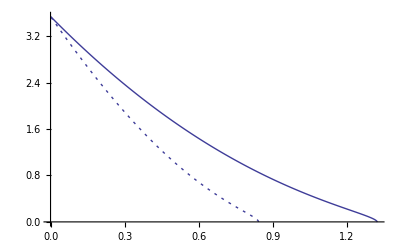

```mathematica
Show[grExLP,grExBPS,PlotRange-> All]
```

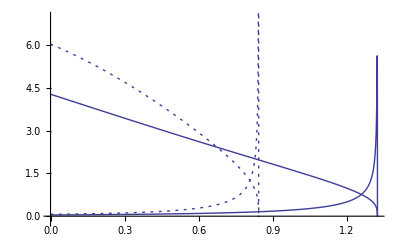

```mathematica
Show[grdEdxxeLP,grdEdxxiLP,grdEdxxeBPS,
grdEdxxiBPS,PlotRange->{ym,yM}]
```

```mathematica
NN=500;
xmin=0;
xmax=xRLPmax;
dx=(xmax-xmin)/NN;
data=Table[{x,dEdxxLP[x],dEdxxeLP[x],dEdxxiLP[x],ExLP[x]},{x,xmin,xmax,dx}]

(* Export["LPvsBPS.dEdxxExLP.aDT300127.dat",data,"Table",ConversionOptions-> {"FormatType"-> FortranForm}];
*)
```

InterpolatingFunction::dmval: Input value {0.000433271} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{{0.,6.09702,6.03197,0.0650451,3.54},{0.00168576,6.09101,6.02579,0.0652178,3.52973},{0.00337151,6.08499,6.0196,0.0653914,3.51946},{0.00505727,6.07895,6.01339,0.0655657,3.50921},{0.00674302,6.0729,6.00716,0.0657408,3.49897},{0.00842878,6.06684,6.00092,0.0659167,3.48874},{0.0101145,6.06076,5.99467,0.0660934,3.47851},{0.0118003,6.05467,5.9884,0.0662709,3.4683},{0.013486,6.04856,5.98211,0.0664493,3.4581},{0.0151718,6.04244,5.97581,0.0666284,3.44791},{0.0168576,6.0363,5.96949,0.0668084,3.43773},{0.0185433,6.03015,5.96316,0.0669892,3.42756},{0.0202291,6.02398,5.95681,0.0671708,3.4174},{0.0219148,6.0178,5.95045,0.0673533,3.40725},{0.0236006,6.01161,5.94407,0.0675366,3.39711},{0.0252863,6.0054,5.93768,0.0677208,3.38698},{0.0269721,5.99917,5.93127,0.0679058,3.37686},{0.0286578,5.99294,5.92484,0.0680917,3.36675},{0.0303436,5.98668,5.91841,0.0682784,3.35666},{0.0320294,5.98042,5.91195,0.068466,3.34657},{0.0337151,5.97414,5.90548,0.0686545,3.33649},{0.0354009,5.96784,5.899,0.0688439,3.32643},{0.0370866,5.96153,5.8925,0.0690341,3.31637},{0.0387724,5.95521,5.88598,0.0692253,3.30633},{0.0404581,5.94887,5.87945,0.0694173,3.29629},{0.0421439,5.94252,5.8729,0.0696103,3.28627},{0.0438296,5.93615,5.86634,0.0698041,3.27626},{0.0455154,5.92977,5.85977,0.0699989,3.26626},{0.0472012,5.92337,5.85318,0.0701946,3.25627},{0.0488869,5.91696,5.84657,0.0703912,3.24629},{0.0505727,5.91054,5.83995,0.0705888,3.23632},{0.0522584,5.9041,5.83331,0.0707873,3.22636},{0.0539442,5.89765,5.82666,0.0709867,3.21641},{0.0556299,5.89118,5.81999,0.0711871,3.20648},{0.0573157,5.8847,5.81331,0.0713885,3.19655},{0.0590014,5.8782,5.80661,0.0715908,3.18664},{0.0606872,5.87169,5.7999,0.0717941,3.17673},{0.062373,5.86517,5.79317,0.0719983,3.16684},{0.0640587,5.85863,5.78643,0.0722036,3.15696},{0.0657445,5.85208,5.77967,0.0724098,3.14709},{0.0674302,5.84551,5.77289,0.072617,3.13723},{0.069116,5.83893,5.76611,0.0728252,3.12738},{0.0708017,5.83234,5.7593,0.0730345,3.11754},{0.0724875,5.82573,5.75248,0.0732447,3.10771},{0.0741732,5.8191,5.74565,0.073456,3.0979},{0.075859,5.81247,5.7388,0.0736683,3.0881},{0.0775448,5.80582,5.73193,0.0738816,3.0783},{0.0792305,5.79915,5.72505,0.074096,3.06852},{0.0809163,5.79247,5.71816,0.0743114,3.05875},{0.082602,5.78578,5.71125,0.0745278,3.04899},{0.0842878,5.77907,5.70433,0.0747454,3.03924},{0.0859735,5.77235,5.69739,0.074964,3.02951},{0.0876593,5.76561,5.69043,0.0751837,3.01978},{0.089345,5.75886,5.68346,0.0754044,3.01007},{0.0910308,5.7521,5.67648,0.0756263,3.00037},{0.0927166,5.74532,5.66947,0.0758492,2.99068},{0.0944023,5.73853,5.66246,0.0760733,2.981},{0.0960881,5.73173,5.65543,0.0762985,2.97133},{0.0977738,5.72491,5.64838,0.0765247,2.96167},{0.0994596,5.71808,5.64132,0.0767522,2.95203},{0.101145,5.71123,5.63425,0.0769807,2.94239},{0.102831,5.70437,5.62716,0.0772104,2.93277},{0.104517,5.69749,5.62005,0.0774412,2.92316},{0.106203,5.6906,5.61293,0.0776732,2.91356},{0.107888,5.6837,5.6058,0.0779064,2.90397},{0.109574,5.67679,5.59865,0.0781408,2.8944},{0.11126,5.66986,5.59148,0.0783763,2.88484},{0.112946,5.66291,5.5843,0.078613,2.87528},{0.114631,5.65596,5.5771,0.0788509,2.86574},{0.116317,5.64898,5.56989,0.07909,2.85621},{0.118003,5.642,5.56267,0.0793304,2.8467},{0.119689,5.635,5.55543,0.0795719,2.83719},{0.121374,5.62799,5.54817,0.0798147,2.8277},{0.12306,5.62096,5.5409,0.0800587,2.81822},{0.124746,5.61392,5.53362,0.080304,2.80875},{0.126432,5.60687,5.52632,0.0805506,2.79929},{0.128117,5.5998,5.519,0.0807984,2.78984},{0.129803,5.59272,5.51167,0.0810474,2.78041},{0.131489,5.58563,5.50433,0.0812978,2.77099},{0.133175,5.57852,5.49697,0.0815494,2.76158},{0.13486,5.5714,5.4896,0.0818024,2.75218},{0.136546,5.56426,5.48221,0.0820567,2.74279},{0.138232,5.55712,5.4748,0.0823122,2.73342},{0.139918,5.54995,5.46739,0.0825692,2.72406},{0.141603,5.54278,5.45995,0.0828274,2.71471},{0.143289,5.53559,5.4525,0.083087,2.70537},{0.144975,5.52839,5.44504,0.083348,2.69605},{0.146661,5.52117,5.43756,0.0836103,2.68673},{0.148346,5.51394,5.43007,0.083874,2.67743},{0.150032,5.5067,5.42256,0.0841391,2.66814},{0.151718,5.49945,5.41504,0.0844056,2.65886},{0.153404,5.49218,5.4075,0.0846735,2.6496},{0.15509,5.4849,5.39995,0.0849428,2.64035},{0.156775,5.4776,5.39239,0.0852135,2.63111},{0.158461,5.47029,5.38481,0.0854857,2.62188},{0.160147,5.46297,5.37721,0.0857593,2.61266},{0.161833,5.45564,5.3696,0.0860344,2.60346},{0.163518,5.44829,5.36198,0.0863109,2.59427},{0.165204,5.44093,5.35434,0.0865889,2.58509},{0.16689,5.43355,5.34668,0.0868685,2.57593},{0.168576,5.42616,5.33901,0.0871495,2.56677},{0.170261,5.41876,5.33133,0.087432,2.55763},{0.171947,5.41135,5.32363,0.087716,2.5485},{0.173633,5.40392,5.31592,0.0880016,2.53939},{0.175319,5.39648,5.30819,0.0882888,2.53028},{0.177004,5.38903,5.30045,0.0885774,2.52119},{0.17869,5.38156,5.2927,0.0888677,2.51212},{0.180376,5.37408,5.28492,0.0891595,2.50305},{0.182062,5.36659,5.27714,0.0894529,2.494},{0.183747,5.35909,5.26934,0.089748,2.48496},{0.185433,5.35157,5.26153,0.0900446,2.47593},{0.187119,5.34404,5.2537,0.0903429,2.46691},{0.188805,5.3365,5.24585,0.0906428,2.45791},{0.19049,5.32894,5.238,0.0909443,2.44892},{0.192176,5.32137,5.23012,0.0912476,2.43994},{0.193862,5.31379,5.22224,0.0915524,2.43098},{0.195548,5.3062,5.21434,0.091859,2.42203},{0.197233,5.29859,5.20642,0.0921673,2.41309},{0.198919,5.29097,5.19849,0.0924773,2.40416},{0.200605,5.28334,5.19055,0.092789,2.39525},{0.202291,5.27569,5.18259,0.0931025,2.38635},{0.203976,5.26803,5.17462,0.0934177,2.37746},{0.205662,5.26036,5.16663,0.0937347,2.36859},{0.207348,5.25268,5.15863,0.0940535,2.35973},{0.209034,5.24499,5.15061,0.094374,2.35088},{0.210719,5.23728,5.14258,0.0946964,2.34205},{0.212405,5.22956,5.13454,0.0950206,2.33322},{0.214091,5.22183,5.12648,0.0953466,2.32441},{0.215777,5.21408,5.11841,0.0956745,2.31562},{0.217462,5.20632,5.11032,0.0960042,2.30683},{0.219148,5.19855,5.10222,0.0963359,2.29806},{0.220834,5.19077,5.0941,0.0966694,2.28931},{0.22252,5.18298,5.08597,0.0970048,2.28056},{0.224206,5.17517,5.07783,0.0973421,2.27183},{0.225891,5.16735,5.06967,0.0976814,2.26312},{0.227577,5.15952,5.0615,0.0980226,2.25441},{0.229263,5.15168,5.05331,0.0983658,2.24572},{0.230949,5.14382,5.04511,0.098711,2.23704},{0.232634,5.13596,5.0369,0.0990582,2.22838},{0.23432,5.12808,5.02867,0.0994074,2.21973},{0.236006,5.12019,5.02043,0.0997586,2.21109},{0.237692,5.11228,5.01217,0.100112,2.20246},{0.239377,5.10437,5.0039,0.100467,2.19385},{0.241063,5.09644,4.99561,0.100825,2.18525},{0.242749,5.0885,4.98732,0.101184,2.17667},{0.244435,5.08055,4.979,0.101546,2.1681},{0.24612,5.07259,4.97068,0.10191,2.15954},{0.247806,5.06461,4.96233,0.102275,2.151},{0.249492,5.05662,4.95398,0.102644,2.14247},{0.251178,5.04862,4.94561,0.103014,2.13395},{0.252863,5.04061,4.93723,0.103386,2.12544},{0.254549,5.03259,4.92883,0.103761,2.11695},{0.256235,5.02456,4.92042,0.104138,2.10848},{0.257921,5.01651,4.912,0.104517,2.10001},{0.259606,5.00846,4.90356,0.104898,2.09156},{0.261292,5.00039,4.89511,0.105282,2.08313},{0.262978,4.99231,4.88664,0.105668,2.0747},{0.264664,4.98422,4.87816,0.106057,2.0663},{0.266349,4.97611,4.86967,0.106447,2.0579},{0.268035,4.968,4.86116,0.10684,2.04952},{0.269721,4.95987,4.85264,0.107236,2.04115},{0.271407,4.95174,4.8441,0.107634,2.0328},{0.273092,4.94359,4.83556,0.108034,2.02446},{0.274778,4.93543,4.82699,0.108437,2.01613},{0.276464,4.92726,4.81842,0.108842,2.00782},{0.27815,4.91908,4.80983,0.10925,1.99952},{0.279835,4.91088,4.80122,0.10966,1.99123},{0.281521,4.90268,4.79261,0.110073,1.98296},{0.283207,4.89446,4.78398,0.110488,1.9747},{0.284893,4.88624,4.77533,0.110906,1.96646},{0.286578,4.878,4.76667,0.111326,1.95823},{0.288264,4.86975,4.758,0.111749,1.95001},{0.28995,4.86149,4.74932,0.112175,1.94181},{0.291636,4.85322,4.74062,0.112604,1.93362},{0.293321,4.84494,4.7319,0.113035,1.92545},{0.295007,4.83665,4.72318,0.113468,1.91729},{0.296693,4.82834,4.71444,0.113905,1.90914},{0.298379,4.82003,4.70569,0.114344,1.90101},{0.300065,4.81171,4.69692,0.114786,1.89289},{0.30175,4.80337,4.68814,0.115231,1.88478},{0.303436,4.79502,4.67935,0.115679,1.87669},{0.305122,4.78667,4.67054,0.116129,1.86862},{0.306808,4.7783,4.66172,0.116583,1.86056},{0.308493,4.76992,4.65288,0.117039,1.85251},{0.310179,4.76154,4.64404,0.117498,1.84447},{0.311865,4.75314,4.63518,0.117961,1.83645},{0.313551,4.74473,4.6263,0.118426,1.82845},{0.315236,4.73631,4.61742,0.118894,1.82046},{0.316922,4.72788,4.60851,0.119365,1.81248},{0.318608,4.71944,4.5996,0.11984,1.80452},{0.320294,4.71099,4.59067,0.120317,1.79657},{0.321979,4.70253,4.58173,0.120798,1.78863},{0.323665,4.69406,4.57278,0.121281,1.78071},{0.325351,4.68558,4.56381,0.121768,1.77281},{0.327037,4.67709,4.55483,0.122258,1.76492},{0.328722,4.66859,4.54584,0.122751,1.75704},{0.330408,4.66008,4.53683,0.123248,1.74918},{0.332094,4.65156,4.52781,0.123748,1.74133},{0.33378,4.64303,4.51878,0.124251,1.73349},{0.335465,4.63449,4.50973,0.124757,1.72567},{0.337151,4.62594,4.50067,0.125267,1.71787},{0.338837,4.61738,4.4916,0.12578,1.71008},{0.340523,4.60881,4.48251,0.126297,1.7023},{0.342208,4.60023,4.47341,0.126817,1.69454},{0.343894,4.59164,4.4643,0.127341,1.68679},{0.34558,4.58304,4.45517,0.127868,1.67906},{0.347266,4.57443,4.44603,0.128399,1.67134},{0.348951,4.56581,4.43688,0.128934,1.66364},{0.350637,4.55719,4.42771,0.129472,1.65595},{0.352323,4.54855,4.41854,0.130014,1.64827},{0.354009,4.5399,4.40935,0.130559,1.64061},{0.355694,4.53125,4.40014,0.131108,1.63296},{0.35738,4.52259,4.39092,0.131661,1.62533},{0.359066,4.51391,4.38169,0.132218,1.61772},{0.360752,4.50523,4.37245,0.132779,1.61011},{0.362437,4.49654,4.36319,0.133343,1.60253},{0.364123,4.48784,4.35392,0.133912,1.59495},{0.365809,4.47913,4.34464,0.134484,1.5874},{0.367495,4.47041,4.33535,0.135061,1.57985},{0.36918,4.46168,4.32604,0.135641,1.57232},{0.370866,4.45294,4.31672,0.136226,1.56481},{0.372552,4.4442,4.30738,0.136815,1.55731},{0.374238,4.43544,4.29804,0.137408,1.54983},{0.375924,4.42668,4.28868,0.138005,1.54236},{0.377609,4.41791,4.2793,0.138606,1.5349},{0.379295,4.40913,4.26992,0.139212,1.52746},{0.380981,4.40034,4.26052,0.139822,1.52004},{0.382667,4.39154,4.25111,0.140436,1.51263},{0.384352,4.38274,4.24168,0.141055,1.50523},{0.386038,4.37392,4.23225,0.141678,1.49785},{0.387724,4.3651,4.2228,0.142306,1.49048},{0.38941,4.35627,4.21333,0.142938,1.48313},{0.391095,4.34743,4.20386,0.143575,1.4758},{0.392781,4.33858,4.19437,0.144216,1.46848},{0.394467,4.32973,4.18487,0.144863,1.46117},{0.396153,4.32087,4.17535,0.145514,1.45388},{0.397838,4.312,4.16583,0.146169,1.4466},{0.399524,4.30312,4.15629,0.14683,1.43934},{0.40121,4.29423,4.14673,0.147496,1.43209},{0.402896,4.28533,4.13717,0.148166,1.42486},{0.404581,4.27643,4.12759,0.148841,1.41764},{0.406267,4.26752,4.118,0.149522,1.41044},{0.407953,4.2586,4.10839,0.150207,1.40326},{0.409639,4.24968,4.09878,0.150898,1.39609},{0.411324,4.24074,4.08915,0.151594,1.38893},{0.41301,4.2318,4.07951,0.152295,1.38179},{0.414696,4.22285,4.06985,0.153002,1.37466},{0.416382,4.2139,4.06018,0.153714,1.36755},{0.418067,4.20494,4.0505,0.154431,1.36045},{0.419753,4.19596,4.04081,0.155154,1.35337},{0.421439,4.18699,4.03111,0.155882,1.34631},{0.423125,4.178,4.02139,0.156616,1.33926},{0.42481,4.16901,4.01166,0.157355,1.33222},{0.426496,4.16001,4.00191,0.158101,1.3252},{0.428182,4.15101,3.99216,0.158852,1.3182},{0.429868,4.14199,3.98239,0.159609,1.31121},{0.431553,4.13298,3.9726,0.160371,1.30423},{0.433239,4.12395,3.96281,0.16114,1.29727},{0.434925,4.11492,3.953,0.161915,1.29033},{0.436611,4.10588,3.94318,0.162696,1.2834},{0.438296,4.09683,3.93335,0.163483,1.27648},{0.439982,4.08778,3.9235,0.164277,1.26959},{0.441668,4.07872,3.91364,0.165076,1.2627},{0.443354,4.06965,3.90377,0.165883,1.25583},{0.445039,4.06058,3.89389,0.166695,1.24898},{0.446725,4.05151,3.88399,0.167514,1.24214},{0.448411,4.04242,3.87408,0.16834,1.23532},{0.450097,4.03333,3.86416,0.169172,1.22851},{0.451783,4.02424,3.85423,0.170011,1.22172},{0.453468,4.01513,3.84428,0.170857,1.21495},{0.455154,4.00603,3.83432,0.17171,1.20819},{0.45684,3.99691,3.82434,0.17257,1.20144},{0.458526,3.98779,3.81436,0.173437,1.19471},{0.460211,3.97867,3.80436,0.174311,1.188},{0.461897,3.96954,3.79435,0.175193,1.1813},{0.463583,3.9604,3.78432,0.176081,1.17461},{0.465269,3.95126,3.77429,0.176977,1.16794},{0.466954,3.94212,3.76424,0.177881,1.16129},{0.46864,3.93296,3.75417,0.178792,1.15465},{0.470326,3.92381,3.7441,0.179711,1.14803},{0.472012,3.91465,3.73401,0.180638,1.14142},{0.473697,3.90548,3.72391,0.181572,1.13483},{0.475383,3.89631,3.71379,0.182515,1.12826},{0.477069,3.88713,3.70366,0.183465,1.1217},{0.478755,3.87795,3.69352,0.184424,1.11515},{0.48044,3.86876,3.68337,0.185391,1.10862},{0.482126,3.85957,3.67321,0.186366,1.10211},{0.483812,3.85038,3.66303,0.18735,1.09561},{0.485498,3.84118,3.65283,0.188342,1.08913},{0.487183,3.83197,3.64263,0.189343,1.08266},{0.488869,3.82276,3.63241,0.190352,1.07621},{0.490555,3.81355,3.62218,0.191371,1.06977},{0.492241,3.80433,3.61194,0.192399,1.06335},{0.493926,3.79511,3.60168,0.193435,1.05694},{0.495612,3.78589,3.59141,0.194481,1.05055},{0.497298,3.77666,3.58113,0.195536,1.04418},{0.498984,3.76743,3.57083,0.196601,1.03782},{0.500669,3.75819,3.56052,0.197675,1.03148},{0.502355,3.74896,3.5502,0.198759,1.02515},{0.504041,3.73971,3.53986,0.199853,1.01884},{0.505727,3.73047,3.52951,0.200957,1.01254},{0.507412,3.72122,3.51915,0.202071,1.00626},{0.509098,3.71197,3.50877,0.203195,0.999995},{0.510784,3.70271,3.49838,0.204329,0.993745},{0.51247,3.69345,3.48798,0.205474,0.987511},{0.514155,3.68419,3.47756,0.206629,0.981293},{0.515841,3.67493,3.46713,0.207795,0.97509},{0.517527,3.66566,3.45669,0.208973,0.968903},{0.519213,3.65639,3.44623,0.210161,0.962731},{0.520898,3.64712,3.43576,0.21136,0.956575},{0.522584,3.63785,3.42528,0.212571,0.950435},{0.52427,3.62858,3.41478,0.213793,0.94431},{0.525956,3.6193,3.40427,0.215027,0.938201},{0.527642,3.61002,3.39375,0.216273,0.932108},{0.529327,3.60074,3.38321,0.217531,0.92603},{0.531013,3.59146,3.37265,0.218801,0.919968},{0.532699,3.58217,3.36209,0.220083,0.913921},{0.534385,3.57289,3.35151,0.221378,0.90789},{0.53607,3.5636,3.34091,0.222685,0.901875},{0.537756,3.55431,3.33031,0.224005,0.895876},{0.539442,3.54502,3.31968,0.225339,0.889892},{0.541128,3.53573,3.30905,0.226685,0.883924},{0.542813,3.52644,3.2984,0.228045,0.877971},{0.544499,3.51715,3.28773,0.229418,0.872034},{0.546185,3.50786,3.27705,0.230806,0.866113},{0.547871,3.49857,3.26636,0.232207,0.860207},{0.549556,3.48927,3.25565,0.233623,0.854318},{0.551242,3.47998,3.24493,0.235053,0.848443},{0.552928,3.47069,3.23419,0.236497,0.842585},{0.554614,3.4614,3.22344,0.237957,0.836742},{0.556299,3.4521,3.21267,0.239431,0.830915},{0.557985,3.44281,3.20189,0.240921,0.825103},{0.559671,3.43352,3.1911,0.242426,0.819307},{0.561357,3.42423,3.18028,0.243947,0.813527},{0.563042,3.41494,3.16946,0.245484,0.807762},{0.564728,3.40565,3.15862,0.247038,0.802013},{0.566414,3.39637,3.14776,0.248607,0.79628},{0.5681,3.38708,3.13689,0.250194,0.790562},{0.569785,3.3778,3.126,0.251798,0.784861},{0.571471,3.36852,3.1151,0.253418,0.779174},{0.573157,3.35924,3.10418,0.255057,0.773504},{0.574843,3.34996,3.09325,0.256713,0.767848},{0.576528,3.34069,3.0823,0.258387,0.762209},{0.578214,3.33142,3.07134,0.26008,0.756585},{0.5799,3.32215,3.06035,0.261792,0.750977},{0.581586,3.31288,3.04936,0.263522,0.745385},{0.583271,3.30362,3.03834,0.265272,0.739808},{0.584957,3.29436,3.02732,0.267041,0.734246},{0.586643,3.2851,3.01627,0.268831,0.728701},{0.588329,3.27585,3.00521,0.27064,0.723171},{0.590014,3.2666,2.99413,0.272471,0.717656},{0.5917,3.25736,2.98303,0.274322,0.712157},{0.593386,3.24812,2.97192,0.276194,0.706674},{0.595072,3.23888,2.96079,0.278089,0.701206},{0.596758,3.22965,2.94965,0.280005,0.695754},{0.598443,3.22043,2.93848,0.281944,0.690317},{0.600129,3.21121,2.9273,0.283905,0.684896},{0.601815,3.20199,2.9161,0.28589,0.679491},{0.603501,3.19279,2.90489,0.287899,0.674101},{0.605186,3.18358,2.89365,0.289931,0.668726},{0.606872,3.17439,2.8824,0.291988,0.663367},{0.608558,3.1652,2.87113,0.29407,0.658024},{0.610244,3.15602,2.85984,0.296177,0.652696},{0.611929,3.14685,2.84854,0.29831,0.647383},{0.613615,3.13768,2.83721,0.30047,0.642086},{0.615301,3.12852,2.82587,0.302656,0.636805},{0.616987,3.11937,2.8145,0.304869,0.631538},{0.618672,3.11023,2.80312,0.30711,0.626288},{0.620358,3.1011,2.79172,0.30938,0.621052},{0.622044,3.09197,2.78029,0.311678,0.615832},{0.62373,3.08286,2.76885,0.314006,0.610628},{0.625415,3.07376,2.75739,0.316363,0.605438},{0.627101,3.06466,2.74591,0.318752,0.600264},{0.628787,3.05558,2.73441,0.321171,0.595106},{0.630473,3.04651,2.72288,0.323622,0.589962},{0.632158,3.03745,2.71134,0.326105,0.584834},{0.633844,3.0284,2.69978,0.328622,0.579722},{0.63553,3.01936,2.68819,0.331172,0.574624},{0.637216,3.01034,2.67658,0.333756,0.569542},{0.638901,3.00133,2.66495,0.336376,0.564475},{0.640587,2.99233,2.6533,0.339031,0.559423},{0.642273,2.98335,2.64162,0.341722,0.554386},{0.643959,2.97438,2.62993,0.344451,0.549364},{0.645644,2.96542,2.61821,0.347218,0.544358},{0.64733,2.95649,2.60646,0.350024,0.539366},{0.649016,2.94756,2.5947,0.352869,0.53439},{0.650702,2.93866,2.5829,0.355755,0.529429},{0.652387,2.92977,2.57109,0.358682,0.524482},{0.654073,2.9209,2.55925,0.361652,0.519551},{0.655759,2.91205,2.54738,0.364665,0.514634},{0.657445,2.90321,2.53549,0.367721,0.509733},{0.65913,2.8944,2.52358,0.370824,0.504846},{0.660816,2.8856,2.51163,0.373972,0.499974},{0.662502,2.87683,2.49966,0.377167,0.495117},{0.664188,2.86808,2.48767,0.380411,0.490275},{0.665873,2.85935,2.47564,0.383704,0.485448},{0.667559,2.85064,2.46359,0.387048,0.480635},{0.669245,2.84196,2.45151,0.390444,0.475837},{0.670931,2.8333,2.43941,0.393893,0.471053},{0.672617,2.82467,2.42727,0.397396,0.466284},{0.674302,2.81606,2.4151,0.400954,0.46153},{0.675988,2.80748,2.40291,0.40457,0.45679},{0.677674,2.79893,2.39068,0.408244,0.452064},{0.67936,2.7904,2.37842,0.411978,0.447353},{0.681045,2.78191,2.36613,0.415773,0.442656},{0.682731,2.77344,2.35381,0.419631,0.437974},{0.684417,2.76501,2.34146,0.423554,0.433306},{0.686103,2.75661,2.32907,0.427543,0.428652},{0.687788,2.74825,2.31665,0.4316,0.424012},{0.689474,2.73992,2.30419,0.435727,0.419386},{0.69116,2.73163,2.2917,0.439925,0.414774},{0.692846,2.72337,2.27917,0.444197,0.410176},{0.694531,2.71515,2.26661,0.448545,0.405592},{0.696217,2.70698,2.25401,0.45297,0.401022},{0.697903,2.69884,2.24137,0.457475,0.396465},{0.699589,2.69075,2.22869,0.462063,0.391923},{0.701274,2.6827,2.21597,0.466735,0.387393},{0.70296,2.6747,2.20321,0.471494,0.382878},{0.704646,2.66675,2.19041,0.476342,0.378376},{0.706332,2.65885,2.17757,0.481283,0.373887},{0.708017,2.651,2.16468,0.486318,0.369411},{0.709703,2.6432,2.15175,0.491452,0.364949},{0.711389,2.63546,2.13877,0.496686,0.3605},{0.713075,2.62777,2.12575,0.502024,0.356063},{0.71476,2.62015,2.11268,0.50747,0.35164},{0.716446,2.61259,2.09956,0.513026,0.34723},{0.718132,2.60509,2.08639,0.518697,0.342832},{0.719818,2.59766,2.07317,0.524485,0.338446},{0.721503,2.5903,2.0599,0.530396,0.334074},{0.723189,2.58301,2.04658,0.536433,0.329713},{0.724875,2.5758,2.0332,0.5426,0.325365},{0.726561,2.56866,2.01976,0.548903,0.321029},{0.728246,2.56161,2.00627,0.555345,0.316705},{0.729932,2.55465,1.99271,0.561932,0.312392},{0.731618,2.54777,1.9791,0.568669,0.308091},{0.733304,2.54098,1.96542,0.575561,0.303802},{0.734989,2.53429,1.95168,0.582615,0.299524},{0.736675,2.52771,1.93787,0.589836,0.295258},{0.738361,2.52123,1.92399,0.597231,0.291002},{0.740047,2.51485,1.91005,0.604807,0.286757},{0.741732,2.5086,1.89603,0.61257,0.282523},{0.743418,2.50246,1.88193,0.62053,0.2783},{0.745104,2.49645,1.86776,0.628692,0.274086},{0.74679,2.49058,1.85351,0.637067,0.269883},{0.748476,2.48484,1.83918,0.645664,0.265689},{0.750161,2.47925,1.82476,0.65449,0.261505},{0.751847,2.47381,1.81025,0.663558,0.25733},{0.753533,2.46854,1.79566,0.672878,0.253164},{0.755219,2.46343,1.78097,0.682461,0.249007},{0.756904,2.4585,1.76618,0.69232,0.244859},{0.75859,2.45376,1.75129,0.702468,0.240718},{0.760276,2.44922,1.7363,0.712918,0.236586},{0.761962,2.44489,1.7212,0.723687,0.232461},{0.763647,2.44078,1.70599,0.73479,0.228343},{0.765333,2.4369,1.69066,0.746244,0.224231},{0.767019,2.43327,1.6752,0.758068,0.220127},{0.768705,2.42991,1.65962,0.770282,0.216028},{0.77039,2.42682,1.64391,0.782908,0.211934},{0.772076,2.42403,1.62806,0.795969,0.207845},{0.773762,2.42156,1.61207,0.80949,0.203761},{0.775448,2.41943,1.59593,0.8235,0.199681},{0.777133,2.41766,1.57963,0.838026,0.195604},{0.778819,2.41627,1.56316,0.853103,0.191529},{0.780505,2.41529,1.54653,0.868766,0.187457},{0.782191,2.41476,1.52971,0.885052,0.183386},{0.783876,2.4147,1.5127,0.902006,0.179315},{0.785562,2.41516,1.49549,0.919673,0.175245},{0.787248,2.41617,1.47807,0.938105,0.171172},{0.788934,2.41778,1.46042,0.957358,0.167098},{0.790619,2.42004,1.44254,0.977497,0.16302},{0.792305,2.42301,1.42441,0.998592,0.158938},{0.793991,2.42674,1.40602,1.02072,0.154851},{0.795677,2.43131,1.38734,1.04397,0.150756},{0.797362,2.4368,1.36836,1.06844,0.146653},{0.799048,2.44331,1.34906,1.09425,0.14254},{0.800734,2.45093,1.32942,1.12151,0.138415},{0.80242,2.45979,1.30941,1.15038,0.134276},{0.804105,2.47002,1.289,1.18102,0.130121},{0.805791,2.48179,1.26817,1.21362,0.125947},{0.807477,2.49528,1.24687,1.24841,0.121753},{0.809163,2.51071,1.22506,1.28564,0.117533},{0.810848,2.52834,1.20271,1.32563,0.113286},{0.812534,2.54848,1.17975,1.36873,0.109008},{0.81422,2.57152,1.15613,1.41539,0.104693},{0.815906,2.5979,1.13177,1.46613,0.100336},{0.817591,2.62819,1.10659,1.5216,0.0959315},{0.819277,2.66309,1.0805,1.5826,0.0914723},{0.820963,2.7035,1.05336,1.65014,0.0869498},{0.822649,2.75057,1.02504,1.72553,0.0823537},{0.824335,2.8058,0.995344,1.81046,0.0776716},{0.82602,2.87123,0.964054,1.90718,0.0728882},{0.827706,2.94968,0.93087,2.01881,0.0679839},{0.829392,3.04515,0.895403,2.14975,0.0629338},{0.831078,3.16363,0.857116,2.30651,0.0577043},{0.832763,3.31448,0.81525,2.49923,0.0522496},{0.834449,3.51344,0.76866,2.74478,0.0465028},{0.836135,3.78945,0.715502,3.07395,0.0403612},{0.837821,4.20356,0.652459,3.55111,0.0336507},{0.839506,4.91702,0.572429,4.3446,0.0260267},{0.841192,6.60024,0.454043,6.14619,0.0165801},{0.842878,-5.59609×10^-10,0.028402,-0.028402,0.000433271}}

```mathematica
NN=500;
xmin=0;
xmax=xRBPSmax;
dx=(xmax-xmin)/NN;
data=Table[{x,dEdxxBPS[x],dEdxxeBPS[x],dEdxxiBPS[x],ExBPS[x]},{x,xmin,xmax,dx}]

(*
Export["LPvsBPS.dEdxxExBPS.aDT300127.dat",data,"Table",ConversionOptions-> {"FormatType"-> FortranForm}];
*)
```

{{0.,4.31637,4.2741,0.0422739,3.54},{0.00264786,4.30908,4.26668,0.042401,3.52858},{0.00529573,4.3018,4.25927,0.0425285,3.51718},{0.00794359,4.29451,4.25185,0.0426567,3.5058},{0.0105915,4.28722,4.24444,0.0427854,3.49444},{0.0132393,4.27993,4.23702,0.0429148,3.4831},{0.0158872,4.27265,4.2296,0.0430447,3.47177},{0.018535,4.26536,4.22218,0.0431752,3.46047},{0.0211829,4.25807,4.21476,0.0433063,3.44918},{0.0238308,4.25078,4.20734,0.043438,3.43792},{0.0264786,4.24349,4.19992,0.0435702,3.42667},{0.0291265,4.2362,4.1925,0.0437031,3.41545},{0.0317744,4.22891,4.18507,0.0438366,3.40424},{0.0344222,4.22162,4.17765,0.0439707,3.39305},{0.0370701,4.21433,4.17023,0.0441054,3.38188},{0.0397179,4.20704,4.1628,0.0442408,3.37073},{0.0423658,4.19975,4.15538,0.0443767,3.3596},{0.0450137,4.19246,4.14795,0.0445133,3.34849},{0.0476615,4.18517,4.14052,0.0446505,3.3374},{0.0503094,4.17788,4.1331,0.0447884,3.32633},{0.0529573,4.17059,4.12567,0.0449268,3.31528},{0.0556051,4.1633,4.11824,0.045066,3.30424},{0.058253,4.15602,4.11081,0.0452057,3.29323},{0.0609008,4.14873,4.10338,0.0453461,3.28223},{0.0635487,4.14144,4.09595,0.0454872,3.27126},{0.0661966,4.13415,4.08852,0.0456289,3.2603},{0.0688444,4.12686,4.08109,0.0457713,3.24936},{0.0714923,4.11957,4.07366,0.0459143,3.23845},{0.0741402,4.11229,4.06623,0.046058,3.22755},{0.076788,4.105,4.0588,0.0462024,3.21667},{0.0794359,4.09772,4.05137,0.0463475,3.20581},{0.0820838,4.09043,4.04394,0.0464932,3.19497},{0.0847316,4.08315,4.03651,0.0466397,3.18415},{0.0873795,4.07586,4.02907,0.0467868,3.17335},{0.0900273,4.06858,4.02164,0.0469346,3.16256},{0.0926752,4.06129,4.01421,0.0470831,3.1518},{0.0953231,4.05401,4.00678,0.0472323,3.14106},{0.0979709,4.04673,3.99935,0.0473822,3.13033},{0.100619,4.03945,3.99192,0.0475328,3.11963},{0.103267,4.03217,3.98448,0.0476842,3.10894},{0.105915,4.02489,3.97705,0.0478362,3.09827},{0.108562,4.01761,3.96962,0.047989,3.08762},{0.11121,4.01033,3.96219,0.0481425,3.077},{0.113858,4.00305,3.95476,0.0482968,3.06639},{0.116506,3.99578,3.94733,0.0484517,3.0558},{0.119154,3.9885,3.9399,0.0486075,3.04523},{0.121802,3.98123,3.93247,0.048764,3.03468},{0.12445,3.97396,3.92503,0.0489212,3.02414},{0.127097,3.96668,3.9176,0.0490792,3.01363},{0.129745,3.95941,3.91017,0.0492379,3.00314},{0.132393,3.95214,3.90275,0.0493974,2.99266},{0.135041,3.94487,3.89532,0.0495577,2.98221},{0.137689,3.93761,3.88789,0.0497188,2.97177},{0.140337,3.93034,3.88046,0.0498806,2.96135},{0.142985,3.92308,3.87303,0.0500432,2.95096},{0.145632,3.91581,3.8656,0.0502067,2.94058},{0.14828,3.90855,3.85818,0.0503709,2.93022},{0.150928,3.90129,3.85075,0.0505359,2.91988},{0.153576,3.89403,3.84333,0.0507017,2.90956},{0.156224,3.88677,3.8359,0.0508684,2.89926},{0.158872,3.87951,3.82848,0.0510358,2.88898},{0.16152,3.87226,3.82105,0.0512041,2.87871},{0.164168,3.865,3.81363,0.0513732,2.86847},{0.166815,3.85775,3.80621,0.0515432,2.85825},{0.169463,3.8505,3.79878,0.051714,2.84804},{0.172111,3.84325,3.79136,0.0518856,2.83785},{0.174759,3.836,3.78394,0.0520581,2.82769},{0.177407,3.82875,3.77652,0.0522314,2.81754},{0.180055,3.82151,3.7691,0.0524056,2.80741},{0.182703,3.81427,3.76169,0.0525807,2.7973},{0.18535,3.80703,3.75427,0.0527566,2.78721},{0.187998,3.79979,3.74685,0.0529334,2.77714},{0.190646,3.79255,3.73944,0.0531111,2.76709},{0.193294,3.78531,3.73202,0.0532897,2.75706},{0.195942,3.77808,3.72461,0.0534692,2.74704},{0.19859,3.77085,3.7172,0.0536496,2.73705},{0.201238,3.76362,3.70978,0.0538309,2.72707},{0.203885,3.75639,3.70237,0.0540131,2.71712},{0.206533,3.74916,3.69496,0.0541963,2.70718},{0.209181,3.74194,3.68756,0.0543803,2.69726},{0.211829,3.73471,3.68015,0.0545653,2.68737},{0.214477,3.72749,3.67274,0.0547513,2.67749},{0.217125,3.72027,3.66534,0.0549382,2.66763},{0.219773,3.71306,3.65793,0.055126,2.65778},{0.22242,3.70584,3.65053,0.0553148,2.64796},{0.225068,3.69863,3.64313,0.0555046,2.63816},{0.227716,3.69142,3.63573,0.0556953,2.62838},{0.230364,3.68421,3.62833,0.055887,2.61861},{0.233012,3.67701,3.62093,0.0560798,2.60886},{0.23566,3.66981,3.61353,0.0562735,2.59914},{0.238308,3.6626,3.60614,0.0564682,2.58943},{0.240956,3.65541,3.59874,0.0566639,2.57974},{0.243603,3.64821,3.59135,0.0568606,2.57007},{0.246251,3.64102,3.58396,0.0570583,2.56042},{0.248899,3.63382,3.57657,0.0572571,2.55079},{0.251547,3.62664,3.56918,0.0574569,2.54118},{0.254195,3.61945,3.56179,0.0576577,2.53158},{0.256843,3.61226,3.5544,0.0578596,2.52201},{0.259491,3.60508,3.54702,0.0580626,2.51246},{0.262138,3.5979,3.53964,0.0582666,2.50292},{0.264786,3.59073,3.53226,0.0584717,2.4934},{0.267434,3.58355,3.52488,0.0586778,2.4839},{0.270082,3.57638,3.5175,0.0588851,2.47442},{0.27273,3.56921,3.51012,0.0590934,2.46496},{0.275378,3.56205,3.50274,0.0593029,2.45552},{0.278026,3.55488,3.49537,0.0595134,2.4461},{0.280673,3.54772,3.488,0.0597251,2.4367},{0.283321,3.54057,3.48063,0.0599379,2.42731},{0.285969,3.53341,3.47326,0.0601519,2.41795},{0.288617,3.52626,3.46589,0.0603669,2.4086},{0.291265,3.51911,3.45853,0.0605832,2.39927},{0.293913,3.51196,3.45116,0.0608006,2.38996},{0.296561,3.50482,3.4438,0.0610191,2.38067},{0.299209,3.49768,3.43644,0.0612389,2.3714},{0.301856,3.49054,3.42908,0.0614598,2.36215},{0.304504,3.4834,3.42172,0.0616819,2.35292},{0.307152,3.47627,3.41437,0.0619052,2.3437},{0.3098,3.46914,3.40701,0.0621297,2.33451},{0.312448,3.46202,3.39966,0.0623555,2.32533},{0.315096,3.45489,3.39231,0.0625824,2.31618},{0.317744,3.44777,3.38496,0.0628106,2.30704},{0.320391,3.44066,3.37762,0.0630401,2.29792},{0.323039,3.43354,3.37027,0.0632708,2.28882},{0.325687,3.42643,3.36293,0.0635028,2.27973},{0.328335,3.41933,3.35559,0.063736,2.27067},{0.330983,3.41222,3.34825,0.0639705,2.26163},{0.333631,3.40512,3.34092,0.0642064,2.2526},{0.336279,3.39802,3.33358,0.0644435,2.24359},{0.338926,3.39093,3.32625,0.0646819,2.23461},{0.341574,3.38384,3.31892,0.0649217,2.22564},{0.344222,3.37675,3.31159,0.0651628,2.21669},{0.34687,3.36967,3.30426,0.0654052,2.20775},{0.349518,3.36259,3.29694,0.065649,2.19884},{0.352166,3.35551,3.28962,0.0658941,2.18995},{0.354814,3.34844,3.2823,0.0661407,2.18107},{0.357462,3.34137,3.27498,0.0663886,2.17221},{0.360109,3.3343,3.26766,0.0666379,2.16338},{0.362757,3.32723,3.26035,0.0668886,2.15456},{0.365405,3.32017,3.25303,0.0671407,2.14576},{0.368053,3.31312,3.24572,0.0673942,2.13697},{0.370701,3.30607,3.23842,0.0676492,2.12821},{0.373349,3.29902,3.23111,0.0679057,2.11947},{0.375997,3.29197,3.22381,0.0681635,2.11074},{0.378644,3.28493,3.21651,0.0684229,2.10203},{0.381292,3.27789,3.20921,0.0686837,2.09334},{0.38394,3.27086,3.20191,0.0689461,2.08467},{0.386588,3.26382,3.19462,0.0692099,2.07602},{0.389236,3.2568,3.18732,0.0694753,2.06739},{0.391884,3.24977,3.18003,0.0697422,2.05878},{0.394532,3.24275,3.17274,0.0700106,2.05018},{0.397179,3.23574,3.16546,0.0702806,2.0416},{0.399827,3.22873,3.15818,0.0705521,2.03304},{0.402475,3.22172,3.15089,0.0708252,2.0245},{0.405123,3.21472,3.14362,0.0710999,2.01598},{0.407771,3.20771,3.13634,0.0713762,2.00748},{0.410419,3.20072,3.12906,0.0716542,1.999},{0.413067,3.19373,3.12179,0.0719337,1.99053},{0.415714,3.18674,3.11452,0.0722149,1.98208},{0.418362,3.17975,3.10726,0.0724978,1.97365},{0.42101,3.17277,3.09999,0.0727823,1.96524},{0.423658,3.1658,3.09273,0.0730685,1.95685},{0.426306,3.15882,3.08547,0.0733564,1.94848},{0.428954,3.15186,3.07821,0.073646,1.94012},{0.431602,3.14489,3.07096,0.0739373,1.93179},{0.43425,3.13793,3.0637,0.0742304,1.92347},{0.436897,3.13098,3.05645,0.0745252,1.91517},{0.439545,3.12403,3.0492,0.0748217,1.90689},{0.442193,3.11708,3.04196,0.0751201,1.89862},{0.444841,3.11013,3.03471,0.0754202,1.89038},{0.447489,3.1032,3.02747,0.0757222,1.88215},{0.450137,3.09626,3.02024,0.0760259,1.87395},{0.452785,3.08933,3.013,0.0763316,1.86576},{0.455432,3.08241,3.00577,0.076639,1.85759},{0.45808,3.07548,2.99854,0.0769484,1.84943},{0.460728,3.06857,2.99131,0.0772596,1.8413},{0.463376,3.06165,2.98408,0.0775727,1.83318},{0.466024,3.05474,2.97686,0.0778877,1.82509},{0.468672,3.04784,2.96964,0.0782047,1.81701},{0.47132,3.04094,2.96242,0.0785236,1.80895},{0.473967,3.03405,2.9552,0.0788445,1.8009},{0.476615,3.02716,2.94799,0.0791674,1.79288},{0.479263,3.02027,2.94078,0.0794922,1.78487},{0.481911,3.01339,2.93357,0.0798191,1.77688},{0.484559,3.00651,2.92636,0.080148,1.76891},{0.487207,2.99964,2.91916,0.080479,1.76096},{0.489855,2.99277,2.91196,0.080812,1.75303},{0.492503,2.98591,2.90476,0.0811471,1.74511},{0.49515,2.97905,2.89756,0.0814843,1.73722},{0.497798,2.9722,2.89037,0.0818236,1.72934},{0.500446,2.96535,2.88318,0.0821651,1.72148},{0.503094,2.9585,2.87599,0.0825087,1.71363},{0.505742,2.95166,2.86881,0.0828545,1.70581},{0.50839,2.94483,2.86162,0.0832025,1.698},{0.511038,2.938,2.85444,0.0835527,1.69021},{0.513685,2.93117,2.84727,0.0839052,1.68244},{0.516333,2.92435,2.84009,0.0842599,1.67469},{0.518981,2.91754,2.83292,0.0846169,1.66696},{0.521629,2.91072,2.82575,0.0849762,1.65924},{0.524277,2.90392,2.81858,0.0853377,1.65154},{0.526925,2.89712,2.81142,0.0857017,1.64386},{0.529573,2.89032,2.80425,0.0860679,1.6362},{0.53222,2.88353,2.79709,0.0864366,1.62856},{0.534868,2.87674,2.78994,0.0868077,1.62093},{0.537516,2.86996,2.78278,0.0871811,1.61332},{0.540164,2.86319,2.77563,0.087557,1.60573},{0.542812,2.85642,2.76848,0.0879354,1.59816},{0.54546,2.84965,2.76133,0.0883163,1.5906},{0.548108,2.84289,2.75419,0.0886997,1.58307},{0.550756,2.83613,2.74705,0.0890856,1.57555},{0.553403,2.82938,2.73991,0.089474,1.56805},{0.556051,2.82264,2.73277,0.0898651,1.56057},{0.558699,2.8159,2.72564,0.0902587,1.5531},{0.561347,2.80916,2.71851,0.090655,1.54565},{0.563995,2.80243,2.71138,0.0910539,1.53822},{0.566643,2.79571,2.70425,0.0914555,1.53081},{0.569291,2.78899,2.69713,0.0918598,1.52342},{0.571938,2.78227,2.69001,0.0922668,1.51604},{0.574586,2.77556,2.68289,0.0926766,1.50868},{0.577234,2.76886,2.67577,0.0930891,1.50134},{0.579882,2.76216,2.66866,0.0935045,1.49402},{0.58253,2.75547,2.66155,0.0939227,1.48672},{0.585178,2.74878,2.65444,0.0943437,1.47943},{0.587826,2.7421,2.64733,0.0947676,1.47216},{0.590473,2.73542,2.64023,0.0951945,1.46491},{0.593121,2.72875,2.63313,0.0956242,1.45767},{0.595769,2.72209,2.62603,0.096057,1.45046},{0.598417,2.71543,2.61893,0.0964927,1.44326},{0.601065,2.70877,2.61184,0.0969315,1.43608},{0.603713,2.70212,2.60475,0.0973733,1.42891},{0.606361,2.69548,2.59766,0.0978182,1.42177},{0.609008,2.68884,2.59058,0.0982662,1.41464},{0.611656,2.68221,2.58349,0.0987173,1.40753},{0.614304,2.67558,2.57641,0.0991717,1.40043},{0.616952,2.66896,2.56933,0.0996292,1.39336},{0.6196,2.66235,2.56226,0.10009,1.3863},{0.622248,2.65574,2.55518,0.100554,1.37926},{0.624896,2.64913,2.54811,0.101021,1.37224},{0.627544,2.64254,2.54104,0.101492,1.36523},{0.630191,2.63594,2.53398,0.101966,1.35824},{0.632839,2.62936,2.52691,0.102444,1.35127},{0.635487,2.62278,2.51985,0.102924,1.34432},{0.638135,2.6162,2.51279,0.103409,1.33738},{0.640783,2.60963,2.50574,0.103897,1.33046},{0.643431,2.60307,2.49868,0.104388,1.32356},{0.646079,2.59651,2.49163,0.104883,1.31668},{0.648726,2.58996,2.48458,0.105382,1.30981},{0.651374,2.58342,2.47753,0.105884,1.30296},{0.654022,2.57688,2.47049,0.10639,1.29613},{0.65667,2.57035,2.46345,0.106899,1.28932},{0.659318,2.56382,2.45641,0.107413,1.28252},{0.661966,2.5573,2.44937,0.10793,1.27574},{0.664614,2.55078,2.44233,0.108451,1.26898},{0.667261,2.54427,2.4353,0.108976,1.26223},{0.669909,2.53777,2.42827,0.109505,1.2555},{0.672557,2.53128,2.42124,0.110038,1.24879},{0.675205,2.52479,2.41421,0.110575,1.2421},{0.677853,2.5183,2.40719,0.111116,1.23542},{0.680501,2.51183,2.40016,0.111661,1.22876},{0.683149,2.50535,2.39314,0.11221,1.22212},{0.685797,2.49889,2.38613,0.112763,1.21549},{0.688444,2.49243,2.37911,0.113321,1.20888},{0.691092,2.48598,2.3721,0.113883,1.20229},{0.69374,2.47953,2.36508,0.114449,1.19572},{0.696388,2.47309,2.35807,0.11502,1.18916},{0.699036,2.46666,2.35107,0.115595,1.18262},{0.701684,2.46023,2.34406,0.116174,1.1761},{0.704332,2.45382,2.33706,0.116758,1.16959},{0.706979,2.4474,2.33006,0.117346,1.1631},{0.709627,2.441,2.32306,0.11794,1.15663},{0.712275,2.4346,2.31606,0.118537,1.15018},{0.714923,2.4282,2.30906,0.11914,1.14374},{0.717571,2.42182,2.30207,0.119747,1.13732},{0.720219,2.41544,2.29508,0.120359,1.13091},{0.722867,2.40906,2.28809,0.120976,1.12453},{0.725514,2.4027,2.2811,0.121598,1.11816},{0.728162,2.39634,2.27411,0.122225,1.1118},{0.73081,2.38998,2.26713,0.122857,1.10547},{0.733458,2.38364,2.26014,0.123494,1.09915},{0.736106,2.3773,2.25316,0.124136,1.09284},{0.738754,2.37097,2.24618,0.124784,1.08656},{0.741402,2.36464,2.23921,0.125437,1.08029},{0.74405,2.35832,2.23223,0.126095,1.07403},{0.746697,2.35201,2.22525,0.126758,1.0678},{0.749345,2.34571,2.21828,0.127427,1.06158},{0.751993,2.33941,2.21131,0.128102,1.05538},{0.754641,2.33312,2.20434,0.128782,1.04919},{0.757289,2.32684,2.19737,0.129468,1.04302},{0.759937,2.32056,2.19041,0.130159,1.03687},{0.762585,2.3143,2.18344,0.130856,1.03073},{0.765232,2.30804,2.17648,0.13156,1.02461},{0.76788,2.30178,2.16951,0.132269,1.01851},{0.770528,2.29554,2.16255,0.132984,1.01242},{0.773176,2.2893,2.15559,0.133705,1.00635},{0.775824,2.28307,2.14863,0.134433,1.0003},{0.778472,2.27684,2.14168,0.135167,0.994262},{0.78112,2.27063,2.13472,0.135907,0.988241},{0.783767,2.26442,2.12777,0.136653,0.982237},{0.786415,2.25822,2.12081,0.137406,0.97625},{0.789063,2.25203,2.11386,0.138165,0.970278},{0.791711,2.24584,2.10691,0.138931,0.964323},{0.794359,2.23966,2.09996,0.139704,0.958385},{0.797007,2.23349,2.09301,0.140484,0.952463},{0.799655,2.22733,2.08606,0.141271,0.946557},{0.802302,2.22118,2.07911,0.142064,0.940667},{0.80495,2.21503,2.07217,0.142865,0.934794},{0.807598,2.20889,2.06522,0.143673,0.928937},{0.810246,2.20276,2.05827,0.144488,0.923097},{0.812894,2.19664,2.05133,0.14531,0.917272},{0.815542,2.19053,2.04439,0.14614,0.911464},{0.81819,2.18442,2.03744,0.146977,0.905672},{0.820838,2.17832,2.0305,0.147822,0.899896},{0.823485,2.17223,2.02356,0.148675,0.894136},{0.826133,2.16615,2.01662,0.149536,0.888392},{0.828781,2.16008,2.00968,0.150405,0.882664},{0.831429,2.15402,2.00274,0.151282,0.876953},{0.834077,2.14796,1.9958,0.152166,0.871257},{0.836725,2.14192,1.98886,0.15306,0.865578},{0.839373,2.13588,1.98192,0.153961,0.859914},{0.84202,2.12985,1.97498,0.154871,0.854267},{0.844668,2.12383,1.96804,0.15579,0.848635},{0.847316,2.11782,1.9611,0.156718,0.84302},{0.849964,2.11181,1.95416,0.157654,0.83742},{0.852612,2.10582,1.94722,0.1586,0.831836},{0.85526,2.09983,1.94028,0.159554,0.826268},{0.857908,2.09386,1.93334,0.160518,0.820716},{0.860555,2.08789,1.9264,0.161491,0.815179},{0.863203,2.08194,1.91946,0.162474,0.809659},{0.865851,2.07599,1.91252,0.163466,0.804154},{0.868499,2.07005,1.90558,0.164469,0.798665},{0.871147,2.06412,1.89864,0.165481,0.793192},{0.873795,2.0582,1.8917,0.166503,0.787734},{0.876443,2.05229,1.88476,0.167536,0.782292},{0.879091,2.0464,1.87782,0.168579,0.776866},{0.881738,2.04051,1.87087,0.169632,0.771455},{0.884386,2.03463,1.86393,0.170696,0.76606},{0.887034,2.02876,1.85698,0.171771,0.76068},{0.889682,2.0229,1.85004,0.172857,0.755316},{0.89233,2.01705,1.84309,0.173954,0.749967},{0.894978,2.01121,1.83614,0.175063,0.744634},{0.897626,2.00538,1.82919,0.176183,0.739316},{0.900273,1.99956,1.82224,0.177315,0.734014},{0.902921,1.99375,1.81529,0.178459,0.728727},{0.905569,1.98795,1.80834,0.179615,0.723456},{0.908217,1.98217,1.80138,0.180783,0.7182},{0.910865,1.97639,1.79443,0.181964,0.712959},{0.913513,1.97062,1.78747,0.183157,0.707733},{0.916161,1.96487,1.78051,0.184363,0.702523},{0.918808,1.95913,1.77355,0.185582,0.697328},{0.921456,1.9534,1.76658,0.186815,0.692148},{0.924104,1.94768,1.75962,0.188061,0.686983},{0.926752,1.94197,1.75265,0.189321,0.681834},{0.9294,1.93627,1.74568,0.190595,0.676699},{0.932048,1.93059,1.73871,0.191883,0.67158},{0.934696,1.92491,1.73173,0.193185,0.666475},{0.937344,1.91925,1.72475,0.194502,0.661386},{0.939991,1.91361,1.71777,0.195834,0.656311},{0.942639,1.90797,1.71079,0.197181,0.651252},{0.945287,1.90235,1.7038,0.198544,0.646207},{0.947935,1.89674,1.69681,0.199922,0.641177},{0.950583,1.89114,1.68982,0.201316,0.636163},{0.953231,1.88555,1.68283,0.202727,0.631162},{0.955879,1.87998,1.67583,0.204154,0.626177},{0.958526,1.87442,1.66882,0.205598,0.621207},{0.961174,1.86888,1.66182,0.207059,0.616251},{0.963822,1.86335,1.65481,0.208538,0.61131},{0.96647,1.85783,1.64779,0.210034,0.606383},{0.969118,1.85232,1.64078,0.211548,0.601471},{0.971766,1.84684,1.63375,0.21308,0.596574},{0.974414,1.84136,1.62673,0.214632,0.591691},{0.977061,1.8359,1.6197,0.216203,0.586822},{0.979709,1.83046,1.61266,0.217793,0.581968},{0.982357,1.82502,1.60562,0.219403,0.577129},{0.985005,1.81961,1.59858,0.221033,0.572303},{0.987653,1.81421,1.59153,0.222683,0.567492},{0.990301,1.80883,1.58447,0.224355,0.562696},{0.992949,1.80346,1.57741,0.226048,0.557913},{0.995596,1.79811,1.57034,0.227763,0.553145},{0.998244,1.79277,1.56327,0.229501,0.548391},{1.00089,1.78745,1.55619,0.23126,0.543651},{1.00354,1.78215,1.54911,0.233043,0.538925},{1.00619,1.77687,1.54202,0.234849,0.534213},{1.00884,1.7716,1.53492,0.23668,0.529515},{1.01148,1.76635,1.52782,0.238535,0.524831},{1.01413,1.76112,1.52071,0.240416,0.520161},{1.01678,1.75591,1.51359,0.242323,0.515505},{1.01943,1.75072,1.50646,0.244254,0.510862},{1.02208,1.74554,1.49933,0.246212,0.506234},{1.02472,1.74039,1.49219,0.248198,0.501618},{1.02737,1.73525,1.48504,0.250212,0.497017},{1.03002,1.73014,1.47789,0.252255,0.492429},{1.03267,1.72505,1.47072,0.254327,0.487855},{1.03531,1.71998,1.46355,0.256429,0.483294},{1.03796,1.71492,1.45636,0.25856,0.478746},{1.04061,1.70989,1.44917,0.260722,0.474212},{1.04326,1.70489,1.44197,0.262916,0.469691},{1.04591,1.6999,1.43476,0.265144,0.465183},{1.04855,1.69494,1.42754,0.267405,0.460689},{1.0512,1.69,1.4203,0.2697,0.456207},{1.05385,1.68509,1.41306,0.272031,0.451739},{1.0565,1.6802,1.40581,0.274396,0.447283},{1.05915,1.67534,1.39854,0.276796,0.442841},{1.06179,1.6705,1.39127,0.279235,0.438411},{1.06444,1.66569,1.38398,0.281712,0.433994},{1.06709,1.66091,1.37668,0.284229,0.42959},{1.06974,1.65615,1.36937,0.286787,0.425199},{1.07238,1.65143,1.36204,0.289388,0.42082},{1.07503,1.64673,1.3547,0.29203,0.416453},{1.07768,1.64206,1.34735,0.294713,0.412099},{1.08033,1.63742,1.33998,0.297441,0.407757},{1.08298,1.63281,1.3326,0.300215,0.403428},{1.08562,1.62824,1.3252,0.303037,0.39911},{1.08827,1.6237,1.31779,0.305908,0.394805},{1.09092,1.61919,1.31036,0.30883,0.390512},{1.09357,1.61472,1.30292,0.311803,0.38623},{1.09622,1.61028,1.29546,0.314827,0.38196},{1.09886,1.60588,1.28798,0.317901,0.377702},{1.10151,1.60151,1.28048,0.321032,0.373456},{1.10416,1.59719,1.27297,0.324221,0.369221},{1.10681,1.5929,1.26543,0.32747,0.364998},{1.10945,1.58866,1.25788,0.330781,0.360786},{1.1121,1.58446,1.25031,0.334155,0.356585},{1.11475,1.58031,1.24271,0.337594,0.352395},{1.1174,1.57619,1.2351,0.341094,0.348216},{1.12005,1.57212,1.22746,0.344659,0.344048},{1.12269,1.5681,1.2198,0.348297,0.33989},{1.12534,1.56413,1.21212,0.352008,0.335743},{1.12799,1.56021,1.20441,0.355796,0.331607},{1.13064,1.55635,1.19668,0.359664,0.327481},{1.13329,1.55254,1.18892,0.363613,0.323365},{1.13593,1.54879,1.18114,0.367647,0.319259},{1.13858,1.54509,1.17333,0.371756,0.315163},{1.14123,1.54144,1.16549,0.375951,0.311076},{1.14388,1.53786,1.15763,0.38024,0.307},{1.14652,1.53435,1.14973,0.384626,0.302932},{1.14917,1.53091,1.1418,0.389113,0.298874},{1.15182,1.52754,1.13384,0.393705,0.294825},{1.15447,1.52425,1.12584,0.398406,0.290785},{1.15712,1.52103,1.11781,0.403218,0.286753},{1.15976,1.51789,1.10975,0.408146,0.28273},{1.16241,1.51483,1.10165,0.413187,0.278714},{1.16506,1.51186,1.09351,0.418348,0.274707},{1.16771,1.50897,1.08533,0.423635,0.270708},{1.17036,1.50617,1.07711,0.429054,0.266716},{1.173,1.50347,1.06885,0.434612,0.262732},{1.17565,1.50087,1.06055,0.440316,0.258754},{1.1783,1.49837,1.0522,0.446173,0.254783},{1.18095,1.49599,1.0438,0.452188,0.250819},{1.18359,1.49373,1.03536,0.458368,0.246861},{1.18624,1.49158,1.02686,0.464722,0.242909},{1.18889,1.48957,1.01831,0.471256,0.238962},{1.19154,1.48769,1.00971,0.47798,0.23502},{1.19419,1.48595,1.00105,0.484902,0.231083},{1.19683,1.48436,0.992326,0.492034,0.227151},{1.19948,1.48293,0.983543,0.499384,0.223222},{1.20213,1.48166,0.974695,0.506965,0.219298},{1.20478,1.48057,0.96578,0.51479,0.215376},{1.20743,1.47966,0.956794,0.52287,0.211457},{1.21007,1.47896,0.947734,0.531222,0.20754},{1.21272,1.47846,0.938598,0.539859,0.203624},{1.21537,1.47818,0.92938,0.548798,0.19971},{1.21802,1.47814,0.920078,0.558059,0.195796},{1.22066,1.47835,0.910687,0.56766,0.191882},{1.22331,1.47883,0.901202,0.577623,0.187967},{1.22596,1.47959,0.89162,0.587971,0.18405},{1.22861,1.48066,0.881935,0.59873,0.180131},{1.23126,1.48207,0.872141,0.609928,0.176209},{1.2339,1.48383,0.862232,0.621597,0.172282},{1.23655,1.48597,0.852202,0.63377,0.16835},{1.2392,1.48853,0.842044,0.646484,0.164413},{1.24185,1.49153,0.83175,0.659783,0.160467},{1.2445,1.49502,0.821311,0.673712,0.156513},{1.24714,1.49904,0.81072,0.688324,0.15255},{1.24979,1.50364,0.799965,0.703678,0.148574},{1.25244,1.50887,0.789036,0.719839,0.144586},{1.25509,1.5148,0.77792,0.736881,0.140583},{1.25773,1.52149,0.766604,0.75489,0.136563},{1.26038,1.52903,0.755073,0.773961,0.132525},{1.26303,1.53752,0.74331,0.794207,0.128465},{1.26568,1.54705,0.731296,0.815755,0.124382},{1.26833,1.55776,0.71901,0.838754,0.120272},{1.27097,1.56981,0.706427,0.863378,0.116131},{1.27362,1.58335,0.693521,0.889834,0.111957},{1.27627,1.59862,0.680259,0.918365,0.107745},{1.27892,1.61587,0.666604,0.949264,0.103489},{1.28157,1.6354,0.652513,0.982889,0.0991854},{1.28421,1.65761,0.637936,1.01967,0.0948263},{1.28686,1.68297,0.622811,1.06016,0.0904044},{1.28951,1.71211,0.607067,1.10504,0.0859104},{1.29216,1.7458,0.590613,1.15518,0.0813335},{1.29481,1.78508,0.573339,1.21174,0.0766602},{1.29745,1.83137,0.555104,1.27626,0.0718741},{1.3001,1.88658,0.535725,1.35086,0.066954},{1.30275,1.95351,0.514962,1.43855,0.0618729},{1.3054,2.03629,0.49248,1.54381,0.0565949},{1.30804,2.14143,0.467801,1.67363,0.0510697},{1.31069,2.27989,0.440196,1.8397,0.0452253},{1.31334,2.4719,0.408471,2.06343,0.0389496},{1.31599,2.76023,0.37042,2.38981,0.0320518},{1.31864,3.25685,0.321108,2.93575,0.0241551},{1.32128,4.38871,0.243847,4.14487,0.0142834},{1.32393,-3.92451×10^-9,-0.0154011,0.0154011,0.00144237}}

## Case B: ne=2E26/cc; nd=nt=1E26/cc; T=0.5 keV; triton particle projectile E=1-10.5

### define parameters

```mathematica
(*
nrho=6500 (* g/cm^3 ; A*Ng = 1 g *)
nrho*(2/5.01)*(6.02*10^23)            (* electron number density in 1/cm^3 *)
*)
```

```mathematica
id="B";
T=0.5    (* keV   *); (* 50 and 150 keV *)
ne=2.      (* cm^-3 *);
nn=26     (* ne*10^nn cm^-3 *);

Zp=1                       (*Charge of probe in units of|e|*);
mp=3*mpev          (*mass of projectile in eV*);

Zb={-1,1,1}                                                              (*charge of plasma species in units of|e|*);
mb={meev,2*mpev,3*mpev}                              (*mass of plasma in ev*);
nb={10^nn,0.5*10^nn,0.5*10^nn}*ne    (*density/cm^3*);

β=1/(T*10^3)//N    (*inverse temp in eV^-1*);
r=3                                      (*vth=c*Sqrt[r/(β*mi)] is thermal velocity:units in cm/s*);
i=1                                      (*thermal velocity of i-th plasma species*);
mtr=10^(-6)                  (*distance unit in meters*);
ev=10^6                           (*energy unit in eV*);
convfact=cmtoa0*(mtr*100)/ev   (*atomic units to MeV/μm*);
nb=nb/cmtoa0^3         (*number of plasma species:units of a0^-3*);
Plus@@(Zb*nb)              (*total charge:should vanish*)
```

0.

```mathematica
param[β,Zp,mp,mb,Zb,nb,r,i,1] (*set parameters for BPS*)
```

gD=0.347094

gpb={0.245433,0.173547,0.173547}

etb*Sqrt[mb0]={0.134846,8.17163,10.0082}

```mathematica
paramLP[β,Zp,mp,mb,Zb,nb,r,i,1,1] (*set parameters for LP*)
```

```mathematica
vth=StoppingPower`PrivateBPS`vth
vthc=StoppingPower`PrivateBPS`vthc
```

1.6243×10^9

0.0541796

```mathematica
mp
```

2.81482×10^9

```mathematica
Clear[VP]
mpMev=mp/10^6;
VP[E_] := Sqrt[2*E/mpMev]/vthc
EMev[vp_] := 0.5*mpMev*(vp*vthc)^2


E0=10.5
vp0=VP[E0]
EMev[vp0]
```

10.5

1.59422

10.5

### LP

#### evaluate data

```mathematica
emin=0.001;
emax=10.5;
```

```mathematica
E1=emin;
E2=0.03;
NN=600;
dE=(E2-E1)/NN;
dataLPa=Table[{EE,dedxiLP[VP[EE]]},{EE,E1,E2,dE}];
```

```mathematica
E1=E2+dE;
E2=0.25;
NN=600;
dE=(E2-E1)/NN;
dataLPb=Table[{EE,dedxiLP[VP[EE]]},{EE,E1,E2,dE}];
```

```mathematica
E1=E2+dE;
E2=emax;
NN=600;
dE=(E2-E1)/NN;
dataLPc=Table[{EE,dedxiLP[VP[EE]]},{EE,E1,E2,dE}];
```

```mathematica
dataLPEI=Join[dataLPa,dataLPb,dataLPc]
```

{{0.001,{0.0672231,3.0084,3.3203}},{0.00104833,{0.0677462,3.06193,3.31958}},«1799»,{10.4829,{2.91466,0.00271871,0.00190704}},{10.5,{2.91248,0.0027146,0.00190414}}}

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

```mathematica
dataLPE=
Table[
{dataLPEI[[i,1]],dataLPEI[[i,2,1]]},{i,1,Length[dataLPEI]}
];
```

```mathematica
nnb=Length[nb];
dataLPI=
Table[{dataLPEI[[i,1]],Sum[dataLPEI[[i,2,j]],{j,2,nnb}]},
{i,1,Length[dataLPEI]}
];
```

```mathematica
dataLP=Table[{dataLPEI[[i,1]],dataLPE[[i,2]]+dataLPI[[i,2]]},{i,1,Length[dataLPEI]}]
```

{{0.001,6.39592},{0.00104833,6.44926},{0.00109667,6.48782},{0.001145,6.51356},{0.00119333,6.52814},{0.00124167,6.53298},{0.00129,6.52935},{0.00133833,6.51833},{0.00138667,6.50086},{0.001435,6.47778},{0.00148333,6.44982},{0.00153167,6.41764},{0.00158,6.38179},{0.00162833,6.3428},{0.00167667,6.3011},{0.001725,6.2571},{0.00177333,6.21115},{0.00182167,6.16356},{0.00187,6.11462},{0.00191833,6.06458},{0.00196667,6.01364},{0.002015,5.96202},{0.00206333,5.90987},{0.00211167,5.85737},{0.00216,5.80465},{0.00220833,5.75182},{0.00225667,5.69899},{0.002305,5.64626},{0.00235333,5.59372},{0.00240167,5.54143},{0.00245,5.48947},{0.00249833,5.43788},{0.00254667,5.38671},{0.002595,5.33601},{0.00264333,5.28582},{0.00269167,5.23616},{0.00274,5.18706},{0.00278833,5.13855},{0.00283667,5.09064},{0.002885,5.04334},{0.00293333,4.99668},{0.00298167,4.95065},{0.00303,4.90527},{0.00307833,4.86054},{0.00312667,4.81646},{0.003175,4.77304},{0.00322333,4.73026},{0.00327167,4.68815},{0.00332,4.64668},{0.00336833,4.60585},{0.00341667,4.56567},{0.003465,4.52612},{0.00351333,4.4872},{0.00356167,4.4489},{0.00361,4.41121},{0.00365833,4.37413},{0.00370667,4.33765},{0.003755,4.30176},{0.00380333,4.26645},{0.00385167,4.23171},{0.0039,4.19753},{0.00394833,4.16391},{0.00399667,4.13083},{0.004045,4.09829},{0.00409333,4.06627},{0.00414167,4.03477},{0.00419,4.00377},{0.00423833,3.97327},{0.00428667,3.94326},{0.004335,3.91373},{0.00438333,3.88467},{0.00443167,3.85607},{0.00448,3.82791},{0.00452833,3.80021},{0.00457667,3.77293},{0.004625,3.74608},{0.00467333,3.71965},{0.00472167,3.69363},{0.00477,3.66801},{0.00481833,3.64278},{0.00486667,3.61793},{0.004915,3.59346},{0.00496333,3.56936},{0.00501167,3.54562},{0.00506,3.52224},{0.00510833,3.4992},{0.00515667,3.47651},{0.005205,3.45414},{0.00525333,3.43211},{0.00530167,3.41039},{0.00535,3.38899},{0.00539833,3.36789},{0.00544667,3.3471},{0.005495,3.3266},{0.00554333,3.30639},{0.00559167,3.28647},{0.00564,3.26682},{0.00568833,3.24745},{0.00573667,3.22834},{0.005785,3.20949},{0.00583333,3.1909},{0.00588167,3.17256},{0.00593,3.15447},{0.00597833,3.13663},{0.00602667,3.11901},{0.006075,3.10164},{0.00612333,3.08448},{0.00617167,3.06756},{0.00622,3.05085},{0.00626833,3.03436},{0.00631667,3.01808},{0.006365,3.00201},{0.00641333,2.98614},{0.00646167,2.97047},{0.00651,2.955},{0.00655833,2.93972},{0.00660667,2.92463},{0.006655,2.90972},{0.00670333,2.895},{0.00675167,2.88046},{0.0068,2.86609},{0.00684833,2.85189},{0.00689667,2.83786},{0.006945,2.824},{0.00699333,2.81031},{0.00704167,2.79677},{0.00709,2.78339},{0.00713833,2.77017},{0.00718667,2.7571},{0.007235,2.74417},{0.00728333,2.7314},{0.00733167,2.71877},{0.00738,2.70628},{0.00742833,2.69394},{0.00747667,2.68173},{0.007525,2.66965},{0.00757333,2.65771},{0.00762167,2.6459},{0.00767,2.63422},{0.00771833,2.62266},{0.00776667,2.61123},{0.007815,2.59992},{0.00786333,2.58873},{0.00791167,2.57766},{0.00796,2.5667},{0.00800833,2.55586},{0.00805667,2.54514},{0.008105,2.53452},{0.00815333,2.52402},{0.00820167,2.51362},{0.00825,2.50333},{0.00829833,2.49314},{0.00834667,2.48305},{0.008395,2.47307},{0.00844333,2.46319},{0.00849167,2.4534},{0.00854,2.44371},{0.00858833,2.43412},{0.00863667,2.42462},{0.008685,2.41521},{0.00873333,2.40589},{0.00878167,2.39667},{0.00883,2.38753},{0.00887833,2.37848},{0.00892667,2.36951},{0.008975,2.36063},{0.00902333,2.35183},{0.00907167,2.34312},{0.00912,2.33449},{0.00916833,2.32593},{0.00921667,2.31746},{0.009265,2.30906},{0.00931333,2.30074},{0.00936167,2.2925},{0.00941,2.28432},{0.00945833,2.27623},{0.00950667,2.2682},{0.009555,2.26025},{0.00960333,2.25237},{0.00965167,2.24456},{0.0097,2.23681},{0.00974833,2.22914},{0.00979667,2.22153},{0.009845,2.21399},{0.00989333,2.20651},{0.00994167,2.1991},{0.00999,2.19175},{0.0100383,2.18446},{0.0100867,2.17723},{0.010135,2.17007},{0.0101833,2.16296},{0.0102317,2.15592},{0.01028,2.14893},{0.0103283,2.14201},{0.0103767,2.13514},{0.010425,2.12832},{0.0104733,2.12156},{0.0105217,2.11486},{0.01057,2.10821},{0.0106183,2.10162},{0.0106667,2.09508},{0.010715,2.08859},{0.0107633,2.08215},{0.0108117,2.07576},{0.01086,2.06943},{0.0109083,2.06314},{0.0109567,2.05691},{0.011005,2.05072},{0.0110533,2.04458},{0.0111017,2.03849},{0.01115,2.03245},{0.0111983,2.02645},{0.0112467,2.0205},{0.011295,2.01459},{0.0113433,2.00873},{0.0113917,2.00292},{0.01144,1.99714},{0.0114883,1.99142},{0.0115367,1.98573},{0.011585,1.98009},{0.0116333,1.97449},{0.0116817,1.96893},{0.01173,1.96341},{0.0117783,1.95793},{0.0118267,1.95249},{0.011875,1.94709},{0.0119233,1.94173},{0.0119717,1.93641},{0.01202,1.93113},{0.0120683,1.92589},{0.0121167,1.92068},{0.012165,1.91552},{0.0122133,1.91038},{0.0122617,1.90529},{0.01231,1.90023},{0.0123583,1.8952},{0.0124067,1.89022},{0.012455,1.88526},{0.0125033,1.88034},{0.0125517,1.87546},{0.0126,1.87061},{0.0126483,1.86579},{0.0126967,1.86101},{0.012745,1.85625},{0.0127933,1.85153},{0.0128417,1.84685},{0.01289,1.84219},{0.0129383,1.83757},{0.0129867,1.83298},{0.013035,1.82841},{0.0130833,1.82388},{0.0131317,1.81938},{0.01318,1.81491},{0.0132283,1.81047},{0.0132767,1.80605},{0.013325,1.80167},{0.0133733,1.79732},{0.0134217,1.79299},{0.01347,1.78869},{0.0135183,1.78442},{0.0135667,1.78018},{0.013615,1.77596},{0.0136633,1.77178},{0.0137117,1.76762},{0.01376,1.76348},{0.0138083,1.75937},{0.0138567,1.75529},{0.013905,1.75123},{0.0139533,1.7472},{0.0140017,1.7432},{0.01405,1.73922},{0.0140983,1.73526},{0.0141467,1.73133},{0.014195,1.72742},{0.0142433,1.72354},{0.0142917,1.71968},{0.01434,1.71585},{0.0143883,1.71204},{0.0144367,1.70825},{0.014485,1.70449},{0.0145333,1.70075},{0.0145817,1.69703},{0.01463,1.69333},{0.0146783,1.68966},{0.0147267,1.686},{0.014775,1.68237},{0.0148233,1.67877},{0.0148717,1.67518},{0.01492,1.67161},{0.0149683,1.66807},{0.0150167,1.66455},{0.015065,1.66104},{0.0151133,1.65756},{0.0151617,1.6541},{0.01521,1.65066},{0.0152583,1.64724},{0.0153067,1.64383},{0.015355,1.64045},{0.0154033,1.63709},{0.0154517,1.63375},{0.0155,1.63042},{0.0155483,1.62712},{0.0155967,1.62383},{0.015645,1.62056},{0.0156933,1.61732},{0.0157417,1.61408},{0.01579,1.61087},{0.0158383,1.60768},{0.0158867,1.6045},{0.015935,1.60134},{0.0159833,1.5982},{0.0160317,1.59508},{0.01608,1.59197},{0.0161283,1.58889},{0.0161767,1.58581},{0.016225,1.58276},{0.0162733,1.57972},{0.0163217,1.5767},{0.01637,1.5737},{0.0164183,1.57071},{0.0164667,1.56774},{0.016515,1.56478},{0.0165633,1.56184},{0.0166117,1.55892},{0.01666,1.55601},{0.0167083,1.55312},{0.0167567,1.55024},{0.016805,1.54738},{0.0168533,1.54453},{0.0169017,1.5417},{0.01695,1.53888},{0.0169983,1.53608},{0.0170467,1.53329},{0.017095,1.53052},{0.0171433,1.52776},{0.0171917,1.52502},{0.01724,1.52229},{0.0172883,1.51958},{0.0173367,1.51688},{0.017385,1.51419},{0.0174333,1.51152},{0.0174817,1.50886},{0.01753,1.50622},{0.0175783,1.50358},{0.0176267,1.50097},{0.017675,1.49836},{0.0177233,1.49577},{0.0177717,1.49319},{0.01782,1.49063},{0.0178683,1.48808},{0.0179167,1.48554},{0.017965,1.48301},{0.0180133,1.4805},{0.0180617,1.478},{0.01811,1.47551},{0.0181583,1.47303},{0.0182067,1.47057},{0.018255,1.46812},{0.0183033,1.46568},{0.0183517,1.46325},{0.0184,1.46083},{0.0184483,1.45843},{0.0184967,1.45604},{0.018545,1.45366},{0.0185933,1.45129},{0.0186417,1.44893},{0.01869,1.44659},{0.0187383,1.44425},{0.0187867,1.44193},{0.018835,1.43962},{0.0188833,1.43732},{0.0189317,1.43503},{0.01898,1.43275},{0.0190283,1.43049},{0.0190767,1.42823},{0.019125,1.42598},{0.0191733,1.42375},{0.0192217,1.42152},{0.01927,1.41931},{0.0193183,1.41711},{0.0193667,1.41491},{0.019415,1.41273},{0.0194633,1.41056},{0.0195117,1.4084},{0.01956,1.40625},{0.0196083,1.4041},{0.0196567,1.40197},{0.019705,1.39985},{0.0197533,1.39774},{0.0198017,1.39564},{0.01985,1.39354},{0.0198983,1.39146},{0.0199467,1.38939},{0.019995,1.38732},{0.0200433,1.38527},{0.0200917,1.38322},{0.02014,1.38119},{0.0201883,1.37916},{0.0202367,1.37714},{0.020285,1.37513},{0.0203333,1.37314},{0.0203817,1.37115},{0.02043,1.36916},{0.0204783,1.36719},{0.0205267,1.36523},{0.020575,1.36327},{0.0206233,1.36133},{0.0206717,1.35939},{0.02072,1.35746},{0.0207683,1.35554},{0.0208167,1.35363},{0.020865,1.35173},{0.0209133,1.34983},{0.0209617,1.34795},{0.02101,1.34607},{0.0210583,1.3442},{0.0211067,1.34234},{0.021155,1.34049},{0.0212033,1.33864},{0.0212517,1.3368},{0.0213,1.33497},{0.0213483,1.33315},{0.0213967,1.33134},{0.021445,1.32953},{0.0214933,1.32774},{0.0215417,1.32595},{0.02159,1.32416},{0.0216383,1.32239},{0.0216867,1.32062},{0.021735,1.31886},{0.0217833,1.31711},{0.0218317,1.31537},{0.02188,1.31363},{0.0219283,1.3119},{0.0219767,1.31018},{0.022025,1.30846},{0.0220733,1.30675},{0.0221217,1.30505},{0.02217,1.30336},{0.0222183,1.30167},{0.0222667,1.29999},{0.022315,1.29832},{0.0223633,1.29666},{0.0224117,1.295},{0.02246,1.29335},{0.0225083,1.2917},{0.0225567,1.29006},{0.022605,1.28843},{0.0226533,1.28681},{0.0227017,1.28519},{0.02275,1.28358},{0.0227983,1.28198},{0.0228467,1.28038},{0.022895,1.27879},{0.0229433,1.2772},{0.0229917,1.27562},{0.02304,1.27405},{0.0230883,1.27249},{0.0231367,1.27093},{0.023185,1.26937},{0.0232333,1.26783},{0.0232817,1.26629},{0.02333,1.26475},{0.0233783,1.26323},{0.0234267,1.2617},{0.023475,1.26019},{0.0235233,1.25868},{0.0235717,1.25717},{0.02362,1.25568},{0.0236683,1.25419},{0.0237167,1.2527},{0.023765,1.25122},{0.0238133,1.24975},{0.0238617,1.24828},{0.02391,1.24682},{0.0239583,1.24536},{0.0240067,1.24391},{0.024055,1.24246},{0.0241033,1.24102},{0.0241517,1.23959},{0.0242,1.23816},{0.0242483,1.23674},{0.0242967,1.23532},{0.024345,1.23391},{0.0243933,1.2325},{0.0244417,1.2311},{0.02449,1.22971},{0.0245383,1.22832},{0.0245867,1.22693},{0.024635,1.22555},{0.0246833,1.22418},{0.0247317,1.22281},{0.02478,1.22145},{0.0248283,1.22009},{0.0248767,1.21874},{0.024925,1.21739},{0.0249733,1.21605},{0.0250217,1.21471},{0.02507,1.21338},{0.0251183,1.21205},{0.0251667,1.21073},{0.025215,1.20941},{0.0252633,1.2081},{0.0253117,1.20679},{0.02536,1.20549},{0.0254083,1.20419},{0.0254567,1.2029},{0.025505,1.20161},{0.0255533,1.20032},{0.0256017,1.19905},{0.02565,1.19777},{0.0256983,1.1965},{0.0257467,1.19524},{0.025795,1.19398},{0.0258433,1.19273},{0.0258917,1.19148},{0.02594,1.19023},{0.0259883,1.18899},{0.0260367,1.18775},{0.026085,1.18652},{0.0261333,1.18529},{0.0261817,1.18407},{0.02623,1.18285},{0.0262783,1.18164},{0.0263267,1.18043},{0.026375,1.17922},{0.0264233,1.17802},{0.0264717,1.17683},{0.02652,1.17563},{0.0265683,1.17445},{0.0266167,1.17326},{0.026665,1.17208},{0.0267133,1.17091},{0.0267617,1.16974},{0.02681,1.16857},{0.0268583,1.16741},{0.0269067,1.16625},{0.026955,1.1651},{0.0270033,1.16395},{0.0270517,1.1628},{0.0271,1.16166},{0.0271483,1.16052},{0.0271967,1.15939},{0.027245,1.15826},{0.0272933,1.15713},{0.0273417,1.15601},{0.02739,1.1549},{0.0274383,1.15378},{0.0274867,1.15267},{0.027535,1.15157},{0.0275833,1.15046},{0.0276317,1.14937},{0.02768,1.14827},{0.0277283,1.14718},{0.0277767,1.1461},{0.027825,1.14501},{0.0278733,1.14393},{0.0279217,1.14286},{0.02797,1.14179},{0.0280183,1.14072},{0.0280667,1.13966},{0.028115,1.1386},{0.0281633,1.13754},{0.0282117,1.13649},{0.02826,1.13544},{0.0283083,1.13439},{0.0283567,1.13335},{0.028405,1.13231},{0.0284533,1.13128},{0.0285017,1.13024},{0.02855,1.12922},{0.0285983,1.12819},{0.0286467,1.12717},{0.028695,1.12615},{0.0287433,1.12514},{0.0287917,1.12413},{0.02884,1.12312},{0.0288883,1.12212},{0.0289367,1.12112},{0.028985,1.12012},{0.0290333,1.11913},{0.0290817,1.11814},{0.02913,1.11715},{0.0291783,1.11617},{0.0292267,1.11519},{0.029275,1.11421},{0.0293233,1.11324},{0.0293717,1.11226},{0.02942,1.1113},{0.0294683,1.11033},{0.0295167,1.10937},{0.029565,1.10842},{0.0296133,1.10746},{0.0296617,1.10651},{0.02971,1.10556},{0.0297583,1.10462},{0.0298067,1.10367},{0.029855,1.10274},{0.0299033,1.1018},{0.0299517,1.10087},{0.03,1.09994},{0.0300483,1.09901},{0.0304149,1.09208},{0.0307815,1.08533},{0.0311481,1.07873},{0.0315147,1.07229},{0.0318813,1.06601},{0.0322479,1.05987},{0.0326144,1.05388},{0.032981,1.04803},{0.0333476,1.04231},{0.0337142,1.03672},{0.0340808,1.03126},{0.0344474,1.02592},{0.034814,1.0207},{0.0351805,1.0156},{0.0355471,1.01061},{0.0359137,1.00573},{0.0362803,1.00095},{0.0366469,0.996275},{0.0370135,0.991701},{0.0373801,0.987224},{0.0377466,0.982842},{0.0381132,0.978551},{0.0384798,0.97435},{0.0388464,0.970236},{0.039213,0.966206},{0.0395796,0.962259},{0.0399462,0.958392},{0.0403127,0.954603},{0.0406793,0.950891},{0.0410459,0.947253},{0.0414125,0.943687},{0.0417791,0.940191},{0.0421457,0.936765},{0.0425123,0.933405},{0.0428788,0.930111},{0.0432454,0.926881},{0.043612,0.923713},{0.0439786,0.920606},{0.0443452,0.917558},{0.0447118,0.914568},{0.0450784,0.911635},{0.045445,0.908757},{0.0458115,0.905933},{0.0461781,0.903162},{0.0465447,0.900442},{0.0469113,0.897773},{0.0472779,0.895153},{0.0476445,0.892582},{0.0480111,0.890057},{0.0483776,0.887579},{0.0487442,0.885146},{0.0491108,0.882757},{0.0494774,0.880411},{0.049844,0.878107},{0.0502106,0.875845},{0.0505772,0.873623},{0.0509437,0.871441},{0.0513103,0.869298},{0.0516769,0.867193},{0.0520435,0.865125},{0.0524101,0.863093},{0.0527767,0.861097},{0.0531433,0.859137},{0.0535098,0.85721},{0.0538764,0.855318},{0.054243,0.853458},{0.0546096,0.851631},{0.0549762,0.849835},{0.0553428,0.84807},{0.0557094,0.846336},{0.0560759,0.844632},{0.0564425,0.842958},{0.0568091,0.841312},{0.0571757,0.839694},{0.0575423,0.838104},{0.0579089,0.836541},{0.0582755,0.835005},{0.0586421,0.833495},{0.0590086,0.832011},{0.0593752,0.830553},{0.0597418,0.829119},{0.0601084,0.827709},{0.060475,0.826323},{0.0608416,0.824961},{0.0612082,0.823622},{0.0615747,0.822306},{0.0619413,0.821012},{0.0623079,0.81974},{0.0626745,0.818489},{0.0630411,0.81726},{0.0634077,0.816051},{0.0637743,0.814863},{0.0641408,0.813695},{0.0645074,0.812546},{0.064874,0.811417},{0.0652406,0.810308},{0.0656072,0.809216},{0.0659738,0.808144},{0.0663404,0.80709},{0.0667069,0.806053},{0.0670735,0.805034},{0.0674401,0.804032},{0.0678067,0.803048},{0.0681733,0.80208},{0.0685399,0.801129},{0.0689065,0.800193},{0.069273,0.799274},{0.0696396,0.798371},{0.0700062,0.797483},{0.0703728,0.79661},{0.0707394,0.795752},{0.071106,0.794909},{0.0714726,0.79408},{0.0718392,0.793266},{0.0722057,0.792466},{0.0725723,0.79168},{0.0729389,0.790907},{0.0733055,0.790148},{0.0736721,0.789402},{0.0740387,0.788669},{0.0744053,0.787949},{0.0747718,0.787242},{0.0751384,0.786547},{0.075505,0.785865},{0.0758716,0.785194},{0.0762382,0.784536},{0.0766048,0.783889},{0.0769714,0.783254},{0.0773379,0.78263},{0.0777045,0.782018},{0.0780711,0.781417},{0.0784377,0.780826},{0.0788043,0.780247},{0.0791709,0.779678},{0.0795375,0.77912},{0.079904,0.778572},{0.0802706,0.778034},{0.0806372,0.777506},{0.0810038,0.776988},{0.0813704,0.77648},{0.081737,0.775982},{0.0821036,0.775493},{0.0824701,0.775014},{0.0828367,0.774544},{0.0832033,0.774083},{0.0835699,0.773631},{0.0839365,0.773188},{0.0843031,0.772753},{0.0846697,0.772328},{0.0850363,0.771911},{0.0854028,0.771502},{0.0857694,0.771102},{0.086136,0.770709},{0.0865026,0.770325},{0.0868692,0.769949},{0.0872358,0.769581},{0.0876024,0.769221},{0.0879689,0.768868},{0.0883355,0.768523},{0.0887021,0.768186},{0.0890687,0.767856},{0.0894353,0.767533},{0.0898019,0.767217},{0.0901685,0.766909},{0.090535,0.766608},{0.0909016,0.766313},{0.0912682,0.766026},{0.0916348,0.765745},{0.0920014,0.765471},{0.092368,0.765203},{0.0927346,0.764942},{0.0931011,0.764688},{0.0934677,0.764439},{0.0938343,0.764198},{0.0942009,0.763962},{0.0945675,0.763732},{0.0949341,0.763509},{0.0953007,0.763291},{0.0956672,0.76308},{0.0960338,0.762874},{0.0964004,0.762674},{0.096767,0.76248},{0.0971336,0.762291},{0.0975002,0.762108},{0.0978668,0.761931},{0.0982334,0.761759},{0.0985999,0.761592},{0.0989665,0.761431},{0.0993331,0.761275},{0.0996997,0.761124},{0.100066,0.760978},{0.100433,0.760838},{0.100799,0.760702},{0.101166,0.760571},{0.101533,0.760445},{0.101899,0.760324},{0.102266,0.760208},{0.102632,0.760097},{0.102999,0.75999},{0.103366,0.759888},{0.103732,0.75979},{0.104099,0.759697},{0.104465,0.759609},{0.104832,0.759525},{0.105198,0.759445},{0.105565,0.75937},{0.105932,0.759299},{0.106298,0.759232},{0.106665,0.759169},{0.107031,0.75911},{0.107398,0.759056},{0.107765,0.759005},{0.108131,0.758959},{0.108498,0.758916},{0.108864,0.758878},{0.109231,0.758843},{0.109598,0.758812},{0.109964,0.758785},{0.110331,0.758762},{0.110697,0.758742},{0.111064,0.758726},{0.11143,0.758714},{0.111797,0.758705},{0.112164,0.7587},{0.11253,0.758699},{0.112897,0.758701},{0.113263,0.758706},{0.11363,0.758715},{0.113997,0.758727},{0.114363,0.758742},{0.11473,0.758761},{0.115096,0.758783},{0.115463,0.758808},{0.115829,0.758836},{0.116196,0.758868},{0.116563,0.758903},{0.116929,0.75894},{0.117296,0.758981},{0.117662,0.759025},{0.118029,0.759072},{0.118396,0.759122},{0.118762,0.759175},{0.119129,0.75923},{0.119495,0.759289},{0.119862,0.759351},{0.120229,0.759415},{0.120595,0.759482},{0.120962,0.759552},{0.121328,0.759624},{0.121695,0.7597},{0.122061,0.759778},{0.122428,0.759859},{0.122795,0.759942},{0.123161,0.760028},{0.123528,0.760116},{0.123894,0.760207},{0.124261,0.760301},{0.124628,0.760397},{0.124994,0.760496},{0.125361,0.760597},{0.125727,0.7607},{0.126094,0.760806},{0.12646,0.760914},{0.126827,0.761025},{0.127194,0.761138},{0.12756,0.761253},{0.127927,0.761371},{0.128293,0.761491},{0.12866,0.761613},{0.129027,0.761737},{0.129393,0.761864},{0.12976,0.761992},{0.130126,0.762123},{0.130493,0.762256},{0.13086,0.762391},{0.131226,0.762529},{0.131593,0.762668},{0.131959,0.762809},{0.132326,0.762953},{0.132692,0.763098},{0.133059,0.763246},{0.133426,0.763395},{0.133792,0.763547},{0.134159,0.7637},{0.134525,0.763856},{0.134892,0.764013},{0.135259,0.764172},{0.135625,0.764333},{0.135992,0.764496},{0.136358,0.76466},{0.136725,0.764827},{0.137091,0.764995},{0.137458,0.765165},{0.137825,0.765337},{0.138191,0.765511},{0.138558,0.765686},{0.138924,0.765864},{0.139291,0.766042},{0.139658,0.766223},{0.140024,0.766405},{0.140391,0.766589},{0.140757,0.766775},{0.141124,0.766962},{0.141491,0.767151},{0.141857,0.767341},{0.142224,0.767533},{0.14259,0.767727},{0.142957,0.767922},{0.143323,0.768118},{0.14369,0.768317},{0.144057,0.768516},{0.144423,0.768717},{0.14479,0.76892},{0.145156,0.769124},{0.145523,0.76933},{0.14589,0.769537},{0.146256,0.769746},{0.146623,0.769956},{0.146989,0.770167},{0.147356,0.77038},{0.147722,0.770594},{0.148089,0.77081},{0.148456,0.771026},{0.148822,0.771245},{0.149189,0.771464},{0.149555,0.771685},{0.149922,0.771908},{0.150289,0.772131},{0.150655,0.772356},{0.151022,0.772582},{0.151388,0.772809},{0.151755,0.773038},{0.152122,0.773268},{0.152488,0.773499},{0.152855,0.773732},{0.153221,0.773965},{0.153588,0.7742},{0.153954,0.774436},{0.154321,0.774673},{0.154688,0.774911},{0.155054,0.775151},{0.155421,0.775392},{0.155787,0.775633},{0.156154,0.775876},{0.156521,0.77612},{0.156887,0.776366},{0.157254,0.776612},{0.15762,0.776859},{0.157987,0.777108},{0.158353,0.777357},{0.15872,0.777608},{0.159087,0.777859},{0.159453,0.778112},{0.15982,0.778366},{0.160186,0.778621},{0.160553,0.778876},{0.16092,0.779133},{0.161286,0.779391},{0.161653,0.77965},{0.162019,0.77991},{0.162386,0.78017},{0.162753,0.780432},{0.163119,0.780695},{0.163486,0.780959},{0.163852,0.781223},{0.164219,0.781489},{0.164585,0.781755},{0.164952,0.782023},{0.165319,0.782291},{0.165685,0.78256},{0.166052,0.78283},{0.166418,0.783101},{0.166785,0.783373},{0.167152,0.783646},{0.167518,0.78392},{0.167885,0.784194},{0.168251,0.784469},{0.168618,0.784746},{0.168984,0.785023},{0.169351,0.785301},{0.169718,0.785579},{0.170084,0.785859},{0.170451,0.786139},{0.170817,0.78642},{0.171184,0.786702},{0.171551,0.786985},{0.171917,0.787268},{0.172284,0.787553},{0.17265,0.787838},{0.173017,0.788124},{0.173384,0.78841},{0.17375,0.788698},{0.174117,0.788986},{0.174483,0.789275},{0.17485,0.789564},{0.175216,0.789854},{0.175583,0.790145},{0.17595,0.790437},{0.176316,0.79073},{0.176683,0.791023},{0.177049,0.791317},{0.177416,0.791611},{0.177783,0.791906},{0.178149,0.792202},{0.178516,0.792499},{0.178882,0.792796},{0.179249,0.793094},{0.179615,0.793393},{0.179982,0.793692},{0.180349,0.793992},{0.180715,0.794292},{0.181082,0.794593},{0.181448,0.794895},{0.181815,0.795198},{0.182182,0.795501},{0.182548,0.795804},{0.182915,0.796109},{0.183281,0.796414},{0.183648,0.796719},{0.184015,0.797025},{0.184381,0.797332},{0.184748,0.797639},{0.185114,0.797947},{0.185481,0.798255},{0.185847,0.798564},{0.186214,0.798874},{0.186581,0.799184},{0.186947,0.799495},{0.187314,0.799806},{0.18768,0.800118},{0.188047,0.80043},{0.188414,0.800743},{0.18878,0.801056},{0.189147,0.80137},{0.189513,0.801685},{0.18988,0.802},{0.190246,0.802315},{0.190613,0.802631},{0.19098,0.802948},{0.191346,0.803265},{0.191713,0.803582},{0.192079,0.8039},{0.192446,0.804219},{0.192813,0.804538},{0.193179,0.804857},{0.193546,0.805177},{0.193912,0.805498},{0.194279,0.805819},{0.194645,0.80614},{0.195012,0.806462},{0.195379,0.806784},{0.195745,0.807107},{0.196112,0.80743},{0.196478,0.807754},{0.196845,0.808078},{0.197212,0.808402},{0.197578,0.808728},{0.197945,0.809053},{0.198311,0.809379},{0.198678,0.809705},{0.199045,0.810032},{0.199411,0.810359},{0.199778,0.810687},{0.200144,0.811015},{0.200511,0.811343},{0.200877,0.811672},{0.201244,0.812001},{0.201611,0.812331},{0.201977,0.812661},{0.202344,0.812991},{0.20271,0.813322},{0.203077,0.813653},{0.203444,0.813985},{0.20381,0.814316},{0.204177,0.814649},{0.204543,0.814982},{0.20491,0.815315},{0.205276,0.815648},{0.205643,0.815982},{0.20601,0.816316},{0.206376,0.816651},{0.206743,0.816985},{0.207109,0.817321},{0.207476,0.817656},{0.207843,0.817992},{0.208209,0.818328},{0.208576,0.818665},{0.208942,0.819002},{0.209309,0.819339},{0.209676,0.819677},{0.210042,0.820015},{0.210409,0.820353},{0.210775,0.820692},{0.211142,0.821031},{0.211508,0.82137},{0.211875,0.82171},{0.212242,0.822049},{0.212608,0.82239},{0.212975,0.82273},{0.213341,0.823071},{0.213708,0.823412},{0.214075,0.823754},{0.214441,0.824095},{0.214808,0.824437},{0.215174,0.82478},{0.215541,0.825122},{0.215907,0.825465},{0.216274,0.825808},{0.216641,0.826152},{0.217007,0.826495},{0.217374,0.826839},{0.21774,0.827184},{0.218107,0.827528},{0.218474,0.827873},{0.21884,0.828218},{0.219207,0.828564},{0.219573,0.828909},{0.21994,0.829255},{0.220307,0.829601},{0.220673,0.829948},{0.22104,0.830294},{0.221406,0.830641},{0.221773,0.830989},{0.222139,0.831336},{0.222506,0.831684},{0.222873,0.832032},{0.223239,0.83238},{0.223606,0.832728},{0.223972,0.833077},{0.224339,0.833426},{0.224706,0.833775},{0.225072,0.834124},{0.225439,0.834474},{0.225805,0.834823},{0.226172,0.835174},{0.226538,0.835524},{0.226905,0.835874},{0.227272,0.836225},{0.227638,0.836576},{0.228005,0.836927},{0.228371,0.837278},{0.228738,0.83763},{0.229105,0.837982},{0.229471,0.838334},{0.229838,0.838686},{0.230204,0.839038},{0.230571,0.839391},{0.230938,0.839744},{0.231304,0.840097},{0.231671,0.84045},{0.232037,0.840803},{0.232404,0.841157},{0.23277,0.84151},{0.233137,0.841864},{0.233504,0.842219},{0.23387,0.842573},{0.234237,0.842927},{0.234603,0.843282},{0.23497,0.843637},{0.235337,0.843992},{0.235703,0.844347},{0.23607,0.844703},{0.236436,0.845058},{0.236803,0.845414},{0.237169,0.84577},{0.237536,0.846126},{0.237903,0.846482},{0.238269,0.846839},{0.238636,0.847195},{0.239002,0.847552},{0.239369,0.847909},{0.239736,0.848266},{0.240102,0.848624},{0.240469,0.848981},{0.240835,0.849339},{0.241202,0.849696},{0.241569,0.850054},{0.241935,0.850412},{0.242302,0.85077},{0.242668,0.851129},{0.243035,0.851487},{0.243401,0.851846},{0.243768,0.852204},{0.244135,0.852563},{0.244501,0.852922},{0.244868,0.853282},{0.245234,0.853641},{0.245601,0.854},{0.245968,0.85436},{0.246334,0.85472},{0.246701,0.85508},{0.247067,0.85544},{0.247434,0.8558},{0.2478,0.85616},{0.248167,0.85652},{0.248534,0.856881},{0.2489,0.857242},{0.249267,0.857602},{0.249633,0.857963},{0.25,0.858324},{0.250367,0.858685},{0.267449,0.875625},{0.284532,0.892716},{0.301615,0.909875},{0.318697,0.927043},{0.33578,0.944172},{0.352863,0.96123},{0.369946,0.978189},{0.387028,0.995029},{0.404111,1.01174},{0.421194,1.0283},{0.438277,1.04471},{0.455359,1.06095},{0.472442,1.07704},{0.489525,1.09296},{0.506607,1.1087},{0.52369,1.12428},{0.540773,1.13969},{0.557856,1.15492},{0.574938,1.16999},{0.592021,1.18488},{0.609104,1.19961},{0.626186,1.21417},{0.643269,1.22856},{0.660352,1.24279},{0.677435,1.25686},{0.694517,1.27076},{0.7116,1.28451},{0.728683,1.2981},{0.745766,1.31154},{0.762848,1.32482},{0.779931,1.33795},{0.797014,1.35093},{0.814096,1.36376},{0.831179,1.37645},{0.848262,1.38899},{0.865345,1.40139},{0.882427,1.41365},{0.89951,1.42577},{0.916593,1.43775},{0.933675,1.4496},{0.950758,1.46131},{0.967841,1.47289},{0.984924,1.48434},{1.00201,1.49566},{1.01909,1.50686},{1.03617,1.51792},{1.05325,1.52887},{1.07034,1.53969},{1.08742,1.55039},{1.1045,1.56096},{1.12159,1.57142},{1.13867,1.58177},{1.15575,1.59199},{1.17283,1.6021},{1.18992,1.6121},{1.207,1.62198},{1.22408,1.63176},{1.24116,1.64142},{1.25825,1.65098},{1.27533,1.66042},{1.29241,1.66977},{1.3095,1.679},{1.32658,1.68813},{1.34366,1.69716},{1.36074,1.70609},{1.37783,1.71492},{1.39491,1.72364},{1.41199,1.73227},{1.42907,1.7408},{1.44616,1.74923},{1.46324,1.75757},{1.48032,1.76581},{1.49741,1.77396},{1.51449,1.78201},{1.53157,1.78998},{1.54865,1.79785},{1.56574,1.80563},{1.58282,1.81332},{1.5999,1.82093},{1.61698,1.82844},{1.63407,1.83587},{1.65115,1.84322},{1.66823,1.85047},{1.68532,1.85765},{1.7024,1.86474},{1.71948,1.87175},{1.73656,1.87867},{1.75365,1.88552},{1.77073,1.89228},{1.78781,1.89897},{1.80489,1.90558},{1.82198,1.9121},{1.83906,1.91856},{1.85614,1.92493},{1.87323,1.93123},{1.89031,1.93745},{1.90739,1.9436},{1.92447,1.94967},{1.94156,1.95568},{1.95864,1.9616},{1.97572,1.96746},{1.9928,1.97325},{2.00989,1.97896},{2.02697,1.98461},{2.04405,1.99019},{2.06114,1.99569},{2.07822,2.00113},{2.0953,2.00651},{2.11238,2.01181},{2.12947,2.01705},{2.14655,2.02222},{2.16363,2.02733},{2.18071,2.03238},{2.1978,2.03736},{2.21488,2.04228},{2.23196,2.04713},{2.24905,2.05192},{2.26613,2.05665},{2.28321,2.06132},{2.30029,2.06593},{2.31738,2.07048},{2.33446,2.07497},{2.35154,2.0794},{2.36862,2.08378},{2.38571,2.08809},{2.40279,2.09235},{2.41987,2.09655},{2.43696,2.1007},{2.45404,2.10478},{2.47112,2.10882},{2.4882,2.1128},{2.50529,2.11672},{2.52237,2.12059},{2.53945,2.12441},{2.55653,2.12817},{2.57362,2.13188},{2.5907,2.13554},{2.60778,2.13915},{2.62486,2.14271},{2.64195,2.14621},{2.65903,2.14967},{2.67611,2.15308},{2.6932,2.15643},{2.71028,2.15974},{2.72736,2.163},{2.74444,2.16621},{2.76153,2.78019},{2.77861,2.79552},{2.79569,2.81055},{2.81277,2.82529},{2.82986,2.83976},{2.84694,2.85394},{2.86402,2.86786},{2.88111,2.88152},{2.89819,2.89491},{2.91527,2.90805},{2.93235,2.92094},{2.94944,2.93359},{2.96652,2.946},{2.9836,2.95817},{3.00068,2.97012},{3.01777,2.98184},{3.03485,2.99333},{3.05193,3.00461},{3.06902,3.01568},{3.0861,3.02654},{3.10318,3.0372},{3.12026,3.04765},{3.13735,3.05791},{3.15443,3.06797},{3.17151,3.07784},{3.18859,3.08753},{3.20568,3.09703},{3.22276,3.10635},{3.23984,3.1155},{3.25693,3.12447},{3.27401,3.13327},{3.29109,3.14191},{3.30817,3.15038},{3.32526,3.15869},{3.34234,3.16684},{3.35942,3.17484},{3.3765,3.18268},{3.39359,3.19037},{3.41067,3.19791},{3.42775,3.20531},{3.44484,3.21257},{3.46192,3.21968},{3.479,3.22666},{3.49608,3.2335},{3.51317,3.24021},{3.53025,3.24678},{3.54733,3.25323},{3.56441,3.25955},{3.5815,3.26575},{3.59858,3.27182},{3.61566,3.27777},{3.63275,3.2836},{3.64983,3.28932},{3.66691,3.29492},{3.68399,3.30041},{3.70108,3.30579},{3.71816,3.31105},{3.73524,3.31621},{3.75232,3.32126},{3.76941,3.32621},{3.78649,3.33106},{3.80357,3.3358},{3.82066,3.34045},{3.83774,3.34499},{3.85482,3.34944},{3.8719,3.3538},{3.88899,3.35806},{3.90607,3.36223},{3.92315,3.36631},{3.94023,3.3703},{3.95732,3.3742},{3.9744,3.37801},{3.99148,3.38174},{4.00857,3.38539},{4.02565,3.38895},{4.04273,3.39243},{4.05981,3.39583},{4.0769,3.39915},{4.09398,3.40239},{4.11106,3.40555},{4.12814,3.40864},{4.14523,3.41166},{4.16231,3.4146},{4.17939,3.41747},{4.19648,3.42027},{4.21356,3.42299},{4.23064,3.42565},{4.24772,3.42824},{4.26481,3.43076},{4.28189,3.43321},{4.29897,3.4356},{4.31605,3.43793},{4.33314,3.44019},{4.35022,3.44239},{4.3673,3.44452},{4.38439,3.4466},{4.40147,3.44861},{4.41855,3.45057},{4.43563,3.45247},{4.45272,3.45431},{4.4698,3.45609},{4.48688,3.45781},{4.50396,3.45949},{4.52105,3.4611},{4.53813,3.46267},{4.55521,3.46417},{4.5723,3.46563},{4.58938,3.46704},{4.60646,3.46839},{4.62354,3.4697},{4.64063,3.47095},{4.65771,3.47216},{4.67479,3.47332},{4.69187,3.47443},{4.70896,3.47549},{4.72604,3.47651},{4.74312,3.47748},{4.76021,3.4784},{4.77729,3.47928},{4.79437,3.48012},{4.81145,3.48092},{4.82854,3.48167},{4.84562,3.48238},{4.8627,3.48305},{4.87978,3.48367},{4.89687,3.48426},{4.91395,3.48481},{4.93103,3.48532},{4.94812,3.48578},{4.9652,3.48621},{4.98228,3.48661},{4.99936,3.48696},{5.01645,3.48728},{5.03353,3.48756},{5.05061,3.48781},{5.06769,3.48802},{5.08478,3.48819},{5.10186,3.48833},{5.11894,3.48844},{5.13603,3.48851},{5.15311,3.48855},{5.17019,3.48856},{5.18727,3.48853},{5.20436,3.48847},{5.22144,3.48838},{5.23852,3.48826},{5.2556,3.48811},{5.27269,3.48793},{5.28977,3.48772},{5.30685,3.48748},{5.32394,3.48721},{5.34102,3.48691},{5.3581,3.48658},{5.37518,3.48623},{5.39227,3.48585},{5.40935,3.48544},{5.42643,3.485},{5.44351,3.48454},{5.4606,3.48405},{5.47768,3.48353},{5.49476,3.48299},{5.51185,3.48242},{5.52893,3.48183},{5.54601,3.48121},{5.56309,3.48057},{5.58018,3.47991},{5.59726,3.47922},{5.61434,3.47851},{5.63142,3.47777},{5.64851,3.47701},{5.66559,3.47623},{5.68267,3.47543},{5.69976,3.4746},{5.71684,3.47376},{5.73392,3.47289},{5.751,3.472},{5.76809,3.47109},{5.78517,3.47016},{5.80225,3.46921},{5.81933,3.46824},{5.83642,3.46725},{5.8535,3.46624},{5.87058,3.46521},{5.88766,3.46416},{5.90475,3.46309},{5.92183,3.46201},{5.93891,3.4609},{5.956,3.45978},{5.97308,3.45864},{5.99016,3.45748},{6.00724,3.45631},{6.02433,3.45511},{6.04141,3.4539},{6.05849,3.45268},{6.07557,3.45144},{6.09266,3.45018},{6.10974,3.4489},{6.12682,3.44761},{6.14391,3.4463},{6.16099,3.44498},{6.17807,3.44364},{6.19515,3.44229},{6.21224,3.44092},{6.22932,3.43954},{6.2464,3.43814},{6.26348,3.43673},{6.28057,3.43531},{6.29765,3.43387},{6.31473,3.43242},{6.33182,3.43095},{6.3489,3.42947},{6.36598,3.42798},{6.38306,3.42647},{6.40015,3.42495},{6.41723,3.42342},{6.43431,3.42188},{6.45139,3.42032},{6.46848,3.41875},{6.48556,3.41717},{6.50264,3.41558},{6.51973,3.41397},{6.53681,3.41236},{6.55389,3.41073},{6.57097,3.40909},{6.58806,3.40744},{6.60514,3.40578},{6.62222,3.40411},{6.6393,3.40243},{6.65639,3.40073},{6.67347,3.39903},{6.69055,3.39732},{6.70764,3.39559},{6.72472,3.39386},{6.7418,3.39212},{6.75888,3.39036},{6.77597,3.3886},{6.79305,3.38683},{6.81013,3.38505},{6.82721,3.38326},{6.8443,3.38146},{6.86138,3.37965},{6.87846,3.37783},{6.89555,3.37601},{6.91263,3.37417},{6.92971,3.37233},{6.94679,3.37048},{6.96388,3.36862},{6.98096,3.36675},{6.99804,3.36488},{7.01512,3.36299},{7.03221,3.3611},{7.04929,3.3592},{7.06637,3.3573},{7.08346,3.35539},{7.10054,3.35346},{7.11762,3.35154},{7.1347,3.3496},{7.15179,3.34766},{7.16887,3.34571},{7.18595,3.34376},{7.20303,3.34179},{7.22012,3.33983},{7.2372,3.33785},{7.25428,3.33587},{7.27137,3.33388},{7.28845,3.33189},{7.30553,3.32989},{7.32261,3.32788},{7.3397,3.32587},{7.35678,3.32385},{7.37386,3.32183},{7.39094,3.3198},{7.40803,3.31777},{7.42511,3.31573},{7.44219,3.31368},{7.45928,3.31163},{7.47636,3.30958},{7.49344,3.30752},{7.51052,3.30545},{7.52761,3.30338},{7.54469,3.30131},{7.56177,3.29923},{7.57885,3.29714},{7.59594,3.29505},{7.61302,3.29296},{7.6301,3.29086},{7.64719,3.28876},{7.66427,3.28665},{7.68135,3.28454},{7.69843,3.28243},{7.71552,3.28031},{7.7326,3.27818},{7.74968,3.27606},{7.76676,3.27393},{7.78385,3.27179},{7.80093,3.26965},{7.81801,3.26751},{7.8351,3.26536},{7.85218,3.26322},{7.86926,3.26106},{7.88634,3.25891},{7.90343,3.25675},{7.92051,3.25459},{7.93759,3.25242},{7.95467,3.25025},{7.97176,3.24808},{7.98884,3.2459},{8.00592,3.24373},{8.02301,3.24155},{8.04009,3.23936},{8.05717,3.23718},{8.07425,3.23499},{8.09134,3.2328},{8.10842,3.2306},{8.1255,3.2284},{8.14258,3.22621},{8.15967,3.224},{8.17675,3.2218},{8.19383,3.21959},{8.21092,3.21739},{8.228,3.21517},{8.24508,3.21296},{8.26216,3.21075},{8.27925,3.20853},{8.29633,3.20631},{8.31341,3.20409},{8.33049,3.20187},{8.34758,3.19964},{8.36466,3.19742},{8.38174,3.19519},{8.39883,3.19296},{8.41591,3.19073},{8.43299,3.1885},{8.45007,3.18626},{8.46716,3.18403},{8.48424,3.18179},{8.50132,3.17955},{8.5184,3.17731},{8.53549,3.17507},{8.55257,3.17282},{8.56965,3.17058},{8.58674,3.16834},{8.60382,3.16609},{8.6209,3.16384},{8.63798,3.16159},{8.65507,3.15934},{8.67215,3.15709},{8.68923,3.15484},{8.70631,3.15259},{8.7234,3.15034},{8.74048,3.14808},{8.75756,3.14583},{8.77465,3.14357},{8.79173,3.14132},{8.80881,3.13906},{8.82589,3.1368},{8.84298,3.13454},{8.86006,3.13228},{8.87714,3.13002},{8.89422,3.12776},{8.91131,3.1255},{8.92839,3.12324},{8.94547,3.12098},{8.96255,3.11872},{8.97964,3.11646},{8.99672,3.1142},{9.0138,3.11194},{9.03089,3.10967},{9.04797,3.10741},{9.06505,3.10515},{9.08213,3.10288},{9.09922,3.10062},{9.1163,3.09836},{9.13338,3.0961},{9.15046,3.09383},{9.16755,3.09157},{9.18463,3.08931},{9.20171,3.08704},{9.2188,3.08478},{9.23588,3.08252},{9.25296,3.08025},{9.27004,3.07799},{9.28713,3.07573},{9.30421,3.07347},{9.32129,3.07121},{9.33837,3.06894},{9.35546,3.06668},{9.37254,3.06442},{9.38962,3.06216},{9.40671,3.0599},{9.42379,3.05764},{9.44087,3.05538},{9.45795,3.05313},{9.47504,3.05087},{9.49212,3.04861},{9.5092,3.04635},{9.52628,3.0441},{9.54337,3.04184},{9.56045,3.03959},{9.57753,3.03733},{9.59462,3.03508},{9.6117,3.03283},{9.62878,3.03057},{9.64586,3.02832},{9.66295,3.02607},{9.68003,3.02382},{9.69711,3.02157},{9.71419,3.01932},{9.73128,3.01707},{9.74836,3.01483},{9.76544,3.01258},{9.78253,3.01034},{9.79961,3.00809},{9.81669,3.00585},{9.83377,3.00361},{9.85086,3.00137},{9.86794,2.99913},{9.88502,2.99689},{9.9021,2.99465},{9.91919,2.99241},{9.93627,2.99018},{9.95335,2.98794},{9.97044,2.98571},{9.98752,2.98347},{10.0046,2.98124},{10.0217,2.97901},{10.0388,2.97678},{10.0558,2.97456},{10.0729,2.97233},{10.09,2.9701},{10.1071,2.96788},{10.1242,2.96566},{10.1413,2.96343},{10.1583,2.96121},{10.1754,2.95899},{10.1925,2.95678},{10.2096,2.95456},{10.2267,2.95234},{10.2438,2.95013},{10.2608,2.94792},{10.2779,2.94571},{10.295,2.9435},{10.3121,2.94129},{10.3292,2.93908},{10.3463,2.93688},{10.3633,2.93467},{10.3804,2.93247},{10.3975,2.93027},{10.4146,2.92807},{10.4317,2.92587},{10.4488,2.92368},{10.4658,2.92148},{10.4829,2.91929},{10.5,2.9171}}

#### saved data

```mathematica
emin=0.001;
emax=10.5;
```

```mathematica
dataLPEI=
{{0.001,{0.06722305885618934,3.008397758792098,3.3202968422191637}},{0.0010483333333333334,{0.06774621335919083,3.061934547382429,3.319577095938571}},{0.0010966666666666668,{0.06828102515776754,3.1066522825582465,3.3128911074790586}},{0.001145,{0.06882525649975457,3.1436136384730875,3.301122846507386}},{0.0011933333333333334,{0.06937705132036076,3.1737250845804392,3.285033910408501}},{0.0012416666666666667,{0.06993486168481468,3.197766581522868,3.2652829503414575}},{0.00129,{0.0704973903367955,3.216414390178732,3.242441253563357}},{0.0013383333333333333,{0.07106354540459041,3.230258821403104,3.217005423371167}},{0.0013866666666666667,{0.07163240438364593,3.2398182194425047,3.189407828480972}},{0.001435,{0.0722031852684695,3.2455501064627907,3.160025309828281}},{0.0014833333333333335,{0.07277522324420548,3.247860162000965,3.129186505274449}},{0.0015316666666666666,{0.07334795173923725,3.2471095327809256,3.0971780628551016}},{0.00158,{0.07392088692549516,3.243620841303464,3.064249948909156}},{0.0016283333333333334,{0.0744936149647789,3.2376831700863193,3.0306200107284607}},{0.0016766666666666666,{0.07506578145628783,3.2295562317425217,2.9964779189609523}},{0.001725,{0.07563708266158604,3.2194738859941907,2.9619885892952325}},{0.0017733333333333334,{0.07620725817191062,3.2076471282261196,2.9272951634904842}},{0.0018216666666666667,{0.07677608475379058,3.1942666468033862,2.8925216148851467}},{0.0018700000000000001,{0.07734337116123605,3.1795050256525332,2.857775031920647}},{0.0019183333333333333,{0.07790895374609805,3.1635186527866717,2.8231476241004216}},{0.001966666666666667,{0.07847269272904189,3.146449383282688,2.788718487556396}},{0.002015,{0.07903446902180544,3.1284259957803626,2.7545551615698702}},{0.0020633333333333333,{0.0795941815089622,3.109565474200374,2.720715002664359}},{0.0021116666666666666,{0.08015174471664405,3.0899741405774726,2.6872463990117357}},{0.00216,{0.08070708680661741,3.0697486603098256,2.654189844687873}},{0.0022083333333333334,{0.08126014784565046,3.048976937460768,2.6215788906424478}},{0.002256666666666667,{0.08181087830867191,3.0277389148075433,2.5894409870038415}},{0.002305,{0.0823592377807433,3.0061072909554785,2.5577982294431463}},{0.002353333333333333,{0.08290519382887339,2.9841481649050134,2.5266680207074144}},{0.0024016666666666665,{0.0834487210192892,2.9619216168802005,2.4960636570517165}},{0.00245,{0.08398980005990886,2.9394822329291395,2.465994848112619}},{0.0024983333333333333,{0.08452841704993301,2.9168795797332527,2.4364681777405273}},{0.0025466666666666667,{0.08506456282277051,2.894158635169677,2.4074875124194626}},{0.002595,{0.08559823236914195,2.871360179424782,2.3790543631292462}},{0.0026433333333333335,{0.08612942432996872,2.848521150829896,2.3511682058296577}},{0.002691666666666667,{0.08665814054994224,2.825674970060633,2.3238267651548576}},{0.0027400000000000002,{0.087184385683811,2.80285183589187,2.2970262653872515}},{0.002788333333333333,{0.08770816684901904,2.780078995317161,2.2707616523233414}},{0.0028366666666666666,{0.08822949331825429,2.757380990513045,2.2450267892415274}},{0.002885,{0.08874837624791547,2.7347798848462785,2.2198146298263146}},{0.0029333333333333334,{0.0892648284371713,2.7122954698779544,2.1951173705889055}},{0.0029816666666666668,{0.08977886411437093,2.689945455106626,2.1709265850456285}},{0.00303,{0.09029049874773193,2.667745642008183,2.1472333416685756}},{0.0030783333333333335,{0.09079974887698455,2.645710083768889,2.1240283074035435}},{0.0031266666666666665,{0.09130663196370196,2.623851231966508,2.1013018383553814}},{0.003175,{0.09181116625863031,2.60218007132982,2.079044059067494}},{0.0032233333333333333,{0.09231337068307358,2.580706243596792,2.057244931667877}},{0.0032716666666666666,{0.09281326472377326,2.5594381613941413,2.035894316016571}},{0.00332,{0.09331086833909287,2.538383112974321,2.0149820218668686}},{0.0033683333333333334,{0.09380620187565641,2.517547358568809,1.9944978539433216}},{0.003416666666666667,{0.0942992859939242,2.4969362190474707,1.9744316507420823}},{0.003465,{0.09479014160214846,2.4765541575120578,1.954773317772118}},{0.0035133333333333336,{0.09527878979744034,2.45640485439635,1.9355128558780976}},{0.0035616666666666665,{0.09576525181320603,2.4364912765955324,1.9166403852164098}},{0.00361,{0.09624954897288478,2.4168157411024187,1.8981461653937686}},{0.0036583333333333333,{0.09673170264804526,2.3973799735874217,1.8800206122224883}},{0.0037066666666666667,{0.09721173422204207,2.378185162322401,1.862254311497056}},{0.003755,{0.09768966505705998,2.3592320078151565,1.8448380301523788}},{0.0038033333333333335,{0.0981655164652158,2.340520768491024,1.8277627251246158}},{0.003851666666666667,{0.0986393096831165,2.3220513027305194,1.8110195502001505}},{0.0039,{0.09911106584899433,2.30382310754687,1.7945998611067382}},{0.003948333333333333,{0.09958080598302836,2.2858353541644045,1.7784952190726275}},{0.003996666666666667,{0.10004855096963805,2.2680869207379217,1.7626973930542933}},{0.004045,{0.10051432154216804,2.250576422434057,1.7471983608108757}},{0.004093333333333333,{0.10097813826951682,2.233302239078207,1.7319903089833237}},{0.004141666666666667,{0.10144002154435665,2.216262540554613,1.7170656323182771}},{0.00419,{0.10189999157311802,2.199455310132524,1.7024169321606801}},{0.0042383333333333335,{0.10235806836718062,2.1828783658779383,1.688037014324802}},{0.004286666666666667,{0.10281427173558898,2.1665293802980723,1.673918886440568}},{0.004335,{0.10326862127858508,2.15040589835435,1.6600557548606945}},{0.004383333333333334,{0.10372113638239003,2.134505353969317,1.6464410212039666}},{0.004431666666666667,{0.10417183621488034,2.1188250851432464,1.6330682786009325}},{0.00448,{0.10462073972204428,2.10336234778741,1.6199313077002104}},{0.004528333333333333,{0.10506786562509982,2.0881143283728085,1.607024072486417}},{0.004576666666666666,{0.10551323241840928,2.0730781554857054,1.5943407159543281}},{0.004625,{0.10595685836799501,2.0582509103743654,1.5818755556781912}},{0.004673333333333333,{0.1063987615104604,2.04362963656501,1.5696230793100425}},{0.0047216666666666665,{0.10683895965242701,2.0292113486191585,1.5575779400363956}},{0.00477,{0.10727747037048667,2.014993040099044,1.5457349520186874}},{0.004818333333333333,{0.10771431101147275,2.000971690802802,1.5340890858392984}},{0.004866666666666667,{0.10814949869303721,1.9871442733264912,1.522635463971886}},{0.004915,{0.10858305030459513,1.9735077590056924,1.5113693562919357}},{0.0049633333333333335,{0.1090149825084772,1.9600591232855304,1.500286175641045}},{0.005011666666666667,{0.10944531174130764,1.946795350564228,1.4893814734562494}},{0.00506,{0.1098740542157286,1.9337134385519674,1.4786509354738058}},{0.005108333333333334,{0.11030122592215413,1.9208104021836832,1.4680903775151912}},{0.005156666666666667,{0.11072684263070807,1.9080832771215133,1.4576957413615759}},{0.005205,{0.11115091989338399,1.8955291228799338,1.447463090721745}},{0.005253333333333334,{0.1115734730462627,1.8831450256041693,1.43738860729733}},{0.005301666666666666,{0.11199451721185381,1.8709281005300928,1.4274685869481945}},{0.00535,{0.11241406730151624,1.8588754941517927,1.4176994359599884}},{0.005398333333333333,{0.1128321380180109,1.8469843861209385,1.408077667415138}},{0.0054466666666666665,{0.1132487438579538,1.8352519909002953,1.398599897667861}},{0.005495,{0.11366389911463155,1.8236755591920135,1.3892628429232923}},{0.005543333333333333,{0.11407761788046795,1.8122523791598084,1.3800633159202922}},{0.005591666666666667,{0.11448991404990665,1.8009797774626304,1.370998222717127}},{0.00564,{0.11490080132197393,1.789855120116124,1.362064559578841}},{0.0056883333333333334,{0.11531029320317956,1.778875813196922,1.3532594099648914}},{0.005736666666666667,{0.1157184030102019,1.7680393034036783,1.3445799416153412}},{0.005785,{0.11612514387264755,1.757343078487629,1.336023403733714}},{0.005833333333333334,{0.11653052873582524,1.7467846675645657,1.3275871242644757}},{0.005881666666666667,{0.11693457036356329,1.7363616413191032,1.3192685072629506}},{0.00593,{0.11733728134090217,1.726071612111337,1.311065030355405}},{0.005978333333333334,{0.11773867407687892,1.7159122339951627,1.3029742422869297}},{0.006026666666666666,{0.11813876080723319,1.7058812026568366,1.2949937605547346}},{0.006075,{0.11853755359711866,1.6959762552816335,1.287121269124395}},{0.006123333333333333,{0.11893506434382252,1.6861951703559022,1.2793545162266162}},{0.0061716666666666664,{0.11933130477942523,1.6765357674111645,1.2716913122320226}},{0.00622,{0.11972628647341707,1.6669959067164346,1.2641295276015516}},{0.006268333333333333,{0.12012002083531068,1.6575734889244,1.2566670909099897}},{0.006316666666666667,{0.12051251911729069,1.648266454676664,1.24930198694026}},{0.006365,{0.12090379241668484,1.6390727841728225,1.2420322548460787}},{0.006413333333333333,{0.12129385167857173,1.6299904967077494,1.2348559863806485}},{0.006461666666666667,{0.1216827076981627,1.6210176501811135,1.227771324189104}},{0.00651,{0.12207037112341504,1.6121523405828084,1.2207764601624653}},{0.0065583333333333335,{0.12245685245730763,1.6033927014576528,1.2138696338509203}},{0.006606666666666667,{0.12284216206031523,1.5947369033524623,1.2070491309342983}},{0.006655,{0.12322631015276196,1.5861831532482957,1.2003132817476654}},{0.006703333333333334,{0.1236093068171137,1.577729693980454,1.1936604598600233}},{0.006751666666666667,{0.12399116200027517,1.5693748036485822,1.1870890807041652}},{0.0068000000000000005,{0.12437188551585555,1.5611167950189981,1.1805976002557714}},{0.006848333333333333,{0.12475148704633902,1.5529540149212055,1.1741845137599372}},{0.006896666666666666,{0.1251299761453337,1.544884843640346,1.1678483545033274}},{0.006945,{0.12550736223965092,1.536907694307191,1.1615876926302622}},{0.006993333333333333,{0.12588365463146045,1.5290210122871335,1.1554011340010601}},{0.0070416666666666666,{0.12625886250029938,1.521223274569472,1.149287319091049}},{0.00709,{0.1266329949051843,1.5135129891581767,1.143244921928687}},{0.007138333333333333,{0.12700606078655796,1.5058886944651966,1.1372726490713168}},{0.007186666666666667,{0.12737806896829193,1.49834895870726,1.1313692386171075}},{0.007235,{0.12774902815960473,1.490892379307015,1.1255334592518114}},{0.0072833333333333335,{0.12811894695694812,1.4835175822992768,1.1197641093289987}},{0.007331666666666667,{0.1284878338459115,1.4762232217430444,1.1140600159824872}},{0.00738,{0.12885569720299336,1.4690079791398947,1.1084200342697474}},{0.007428333333333334,{0.12922254529747518,1.4618705628592652,1.1028430463450851}},{0.007476666666666667,{0.1295883862931254,1.4548097075710935,1.097327960661469}},{0.0075250000000000004,{0.12995322824996985,1.447824173686207,1.0918737111999097}},{0.007573333333333333,{0.13031707912596924,1.4409127468048042,1.0864792567253374}},{0.007621666666666666,{0.13067994677873185,1.4340742371733193,1.0811435800679625}},{0.00767,{0.13104183896714597,1.4273074791499236,1.0758656874291586}},{0.007718333333333333,{0.1314027633529193,1.4206113306788593,1.0706446077109284}},{0.0077666666666666665,{0.1317627275022736,1.4139846727737755,1.0654793918680583}},{0.007815,{0.13212173888744036,1.4074264090101896,1.0603691122821037}},{0.007863333333333333,{0.1324798048881544,1.4009354650271946,1.055312862156381}},{0.007911666666666668,{0.13283693279324177,1.3945107880384466,1.0503097549311706}},{0.00796,{0.1331931298019733,1.3881513463525161,1.0453589237183705}},{0.008008333333333333,{0.13354840302559803,1.3818561289025926,1.0404595207548781}},{0.008056666666666667,{0.13390275948874222,1.3756241447855537,1.0356107168739872}},{0.008105,{0.1342562061307377,1.3694544228103849,1.0308117009941395}},{0.008153333333333334,{0.13460874980704182,1.3633460110558937,1.0260616796243731}},{0.008201666666666666,{0.13496039729060239,1.357297976437688,1.0213598763858645}},{0.00825,{0.13531115527308235,1.351309404284329,1.0167055315489497}},{0.008298333333333333,{0.13566103036618724,1.345379397922595,1.0120979015850704}},{0.008346666666666667,{0.13601002910298995,1.3395070782717606,1.007536258733088}},{0.008395,{0.13635815793906517,1.3336915834467866,1.0030198905794416}},{0.008443333333333334,{0.13670542325380355,1.3279320683703226,0.9985480996516464}},{0.008491666666666666,{0.13705183135150995,1.3222277043933912,0.9941202030246435}},{0.00854,{0.13739738846266775,1.3165776789246473,0.9897355319395437}},{0.008588333333333333,{0.13774210074506676,1.310981195068072,0.9853934314343078}},{0.008636666666666667,{0.13808597428487548,1.3054374712689705,0.9810932599859405}},{0.008685,{0.13842901509780328,1.2999457409681487,0.9768343891637886}},{0.008733333333333333,{0.13877122913021384,1.2945052522641092,0.9726162032935376}},{0.008781666666666667,{0.13911262226010987,1.2891152675831348,0.9684380991315353}},{0.00883,{0.13945320029823047,1.2837750633571223,0.9642994855490779}},{0.008878333333333334,{0.13979296898914848,1.2784839297089998,0.9601997832262944}},{0.008926666666666666,{0.14013193401214377,1.2732411701455963,0.9561384243553122}},{0.008975,{0.14047010098224283,1.2680461012578117,0.9521148523523599}},{0.009023333333333333,{0.1408074754513011,1.2628980524279374,0.9481285215785139}},{0.009071666666666667,{0.14114406290881257,1.2577963655439717,0.9441788970687732}},{0.00912,{0.14147986878291113,1.2527403947207993,0.9402654542691873}},{0.009168333333333334,{0.14181489844128697,1.2477295060280702,0.9363876787817526}},{0.009216666666666666,{0.1421491571921221,1.2427630772246396,0.9325450661168159}},{0.009265,{0.14248265028487897,1.237840497499424,0.9287371214527276}},{0.009313333333333333,{0.14281538291134266,1.2329611672185246,0.9249633594024972}},{0.009361666666666667,{0.14314736020627317,1.22812449767848,0.9212233037872165}},{0.00941,{0.1434785872484264,1.2233299108655056,0.9175164874160237}},{0.009458333333333334,{0.14380906906127813,1.2185768392205762,0.913842451872385}},{0.009506666666666667,{0.14413881061383596,1.2138647254102266,0.910200747306488}},{0.009555,{0.14446781682151155,1.2091930221029183,0.9065909322335413}},{0.009603333333333334,{0.1447960925467795,1.2045611917508532,0.903012573337786}},{0.009651666666666666,{0.14512364260009644,1.1999687063770974,0.899465245282028}},{0.0097,{0.14545047174052245,1.1954150473678848,0.8959485305225183}},{0.009748333333333333,{0.1457765846765405,1.1908997052699775,0.8924620191289954}},{0.009796666666666667,{0.14610198606674216,1.1864221795929588,0.8890053086097317}},{0.009845,{0.14642668052058602,1.1819819786163361,0.8855780037414198}},{0.009893333333333334,{0.1467506725990735,1.177578619201329,0.8821797164037364}},{0.009941666666666666,{0.14707396681540325,1.1732116266072392,0.878810065418444}},{0.00999,{0.14739656763573503,1.1688805343122757,0.87546867639288}},{0.010038333333333333,{0.14771847947977715,1.164584883838725,0.8721551815676913}},{0.010086666666666667,{0.1480397067215076,1.1603242245823622,0.8688692196686866}},{0.010135,{0.1483602536897335,1.1560981136459902,0.8656104357626737}},{0.010183333333333334,{0.14868012466881905,1.1519061156770076,0.8623784811171527}},{0.010231666666666667,{0.14899932389922957,1.1477478027088923,0.8591730130637518}},{0.010280000000000001,{0.14931785557817398,1.1436227540065194,0.8559936948652875}},{0.010328333333333333,{0.1496357238602168,1.1395305559151927,0.852840195586332}},{0.010376666666666666,{0.1499529328578716,1.1354708017133153,0.8497121899671848}},{0.010425,{0.15026948664211978,1.1314430914685878,0.8466093583011439}},{0.010473333333333333,{0.15058538924303927,1.1274470318976628,0.8435313863149756}},{0.010521666666666667,{0.15090064465036826,1.1234822362291481,0.8404779650524796}},{0.01057,{0.15121525681401984,1.1195483240698818,0.8374487907610675}},{0.010618333333333334,{0.15152922964467086,1.1156449212743997,0.8344435647812529}},{0.010666666666666666,{0.1518425670141995,1.111771659817499,0.8314619934389699}},{0.010715,{0.1521552727563324,1.1079281776698302,0.8285037879406393}},{0.010763333333333333,{0.15246735066706318,1.1041141186764338,0.8255686642708916}},{0.010811666666666667,{0.15277880450520212,1.1003291324381488,0.8226563430928777}},{0.01086,{0.15308963799290987,1.0965728741958118,0.8197665496510859}},{0.010908333333333334,{0.15339985481607482,1.092845004717186,0.8168990136765893}},{0.010956666666666667,{0.15370945862489593,1.0891451901865368,0.8140534692946617}},{0.011005000000000001,{0.1540184530343099,1.0854731020967971,0.8112296549346788}},{0.011053333333333333,{0.15432684162446986,1.0818284171442478,0.8084273132422547}},{0.011101666666666666,{0.154634627941233,1.0782108171256508,0.8056461909935347}},{0.01115,{0.15494181549650612,1.0746199888377717,0.8028860390115914}},{0.011198333333333333,{0.15524840776884755,1.0710556239792346,0.800146612084862}},{0.011246666666666667,{0.15555440820374553,1.067517419054637,0.797427668887565}},{0.011295,{0.15585982021414224,1.0640050752808834,0.7947289719020444}},{0.011343333333333334,{0.1561646471808378,1.0605182984956614,0.7920502873429835}},{0.011391666666666666,{0.15646889245288464,1.0570567990680289,0.789391385083442}},{0.01144,{0.15677255934801163,1.0536202918110316,0.7867520385826534}},{0.011488333333333333,{0.1570756511530168,1.050208495896323,0.7841320248155469}},{0.011536666666666667,{0.15737817112417002,1.046821134770716,0.7815311242039368}},{0.011585,{0.157680122487605,1.0434579360746348,0.778949120549335}},{0.011633333333333334,{0.15798150843967027,1.0401186315624003,0.7763858009673461}},{0.011681666666666667,{0.15828233214737267,1.0368029570243205,0.7738409558235961}},{0.01173,{0.15858259674865716,1.0335106522105246,0.7713143786711539}},{0.011778333333333333,{0.15888230535285122,1.030241460756506,0.7688058661894087}},{0.011826666666666666,{0.15918146104098665,1.0269951301103286,0.7663152181243589}},{0.011875,{0.1594800668661533,1.0237714114614513,0.763842237230277}},{0.011923333333333333,{0.15977812585386375,1.0205700596711371,0.761386729212714}},{0.011971666666666667,{0.16007564100233942,1.0173908332043966,0.7589485026728034}},{0.01202,{0.1603726152829467,1.0142334940634363,0.7565273690528357}},{0.012068333333333334,{0.16066905164044562,1.0110978077225714,0.7541231425830662}},{0.012116666666666666,{0.16096495299333963,1.0079835430645636,0.7517356402297213}},{0.012165,{0.16126032223420694,1.0048904723183516,0.7493646816441785}},{0.012213333333333333,{0.16155516223003363,1.0018183709981379,0.7470100891132814}},{0.012261666666666667,{0.16184947582246018,0.9987670178437995,0.7446716875107656}},{0.01231,{0.16214326582817676,0.9957361947625883,0.7423493042497639}},{0.012358333333333334,{0.16243653503911673,0.9927256867720906,0.7400427692363628}},{0.012406666666666667,{0.1627292862229132,0.989735281944414,0.7377519148241847}},{0.012455,{0.16302152212299093,0.9867647713515684,0.7354765757699664}},{0.012503333333333333,{0.16331324545902748,0.9838139490120197,0.7332165891901122}},{0.012551666666666668,{0.16360445892714714,0.9808826118383807,0.7309717945181918}},{0.0126,{0.163895165200242,0.9779705595862095,0.7287420334633657}},{0.012648333333333333,{0.16418536692820127,0.975077594803898,0.7265271499697049}},{0.012696666666666667,{0.1644750667382652,0.9722035227836157,0.7243269901763938}},{0.012745,{0.16476426723514784,0.9693481515132822,0.7221414023787817}},{0.012793333333333334,{0.16505297100149063,0.9665112916295541,0.7199702369902748}},{0.012841666666666666,{0.16534118059795336,0.9636927563717871,0.7178133465050338}},{0.01289,{0.16562889856358945,0.9608923615369638,0.715670585461469}},{0.012938333333333333,{0.16591612741601877,0.9581099254355517,0.7135418104065058}},{0.012986666666666667,{0.16620286965171627,0.9553452688482801,0.7114268798606028}},{0.013035,{0.1664891277462474,0.9525982149838075,0.7093256542835091}},{0.013083333333333334,{0.16677490415449847,0.9498685894372552,0.7072379960407327}},{0.013131666666666666,{0.16706020131096486,0.9471562201495983,0.7051637693707109}},{0.01318,{0.16734502162987952,0.9444609373678818,0.7031028403526651}},{0.013228333333333333,{0.16762936750557195,0.9417825736062471,0.7010550768751175}},{0.013276666666666668,{0.1679132413126128,0.9391209636077523,0.699020348605059}},{0.013325,{0.16819664540603624,0.9364759443069628,0.6969985269577516}},{0.013373333333333334,{0.16847958212161854,0.9338473547932958,0.6949894850671475}},{0.013421666666666667,{0.16876205377605338,0.9312350362751057,0.6929930977569142}},{0.01347,{0.16904406266715866,0.9286388320444846,0.6910092415120475}},{0.013518333333333334,{0.16932561107410457,0.9260585874427681,0.689037794451059}},{0.013566666666666666,{0.16960670125765465,0.9234941498267286,0.6870786362987278}},{0.013615,{0.16988733546029644,0.9209453685354364,0.6851316483593989}},{0.013663333333333333,{0.1701675159065165,0.9184120948577813,0.6831967134908166}},{0.013711666666666667,{0.1704472448029752,0.9158941820006289,0.6812737160784825}},{0.01376,{0.17072652433866828,0.9133914850576058,0.6793625420105223}},{0.013808333333333334,{0.17100535668518785,0.9109038609784984,0.6774630786530526}},{0.013856666666666666,{0.17128374399685004,0.9084311685392428,0.6755752148260348}},{0.013905,{0.1715616884109381,0.9059732683125052,0.673698840779605}},{0.013953333333333333,{0.17183919204783135,0.9035300226388304,0.6718338481708671}},{0.014001666666666667,{0.17211625701128183,0.9011012955983475,0.6699801300411438}},{0.01405,{0.17239288538846756,0.8986869529830219,0.6681375807936667}},{0.014098333333333334,{0.1726690792502866,0.8962868622694411,0.6663060961717052}},{0.014146666666666667,{0.17294484065144552,0.8939008925921191,0.6644855732371147}},{0.014195,{0.17322017163071174,0.8915289147173153,0.6626759103493013}},{0.014243333333333334,{0.1734950742110442,0.8891708010173462,0.6608770071445923}},{0.014291666666666666,{0.17376955039974668,0.8868264254453876,0.6590887645159998}},{0.01434,{0.1740436021886506,0.8844956635107518,0.6573110845933736}},{0.014388333333333333,{0.17431723155432652,0.8821783922546332,0.6555438707239304}},{0.014436666666666667,{0.17459044045814473,0.8798744902263073,0.6537870274531545}},{0.014485,{0.17486323084653696,0.877583837459774,0.6520404605060584}},{0.014533333333333334,{0.17513560465108388,0.8753063154508418,0.6503040767687982}},{0.014581666666666666,{0.17540756378873718,0.873041807134635,0.6485777842706348}},{0.01463,{0.17567911016190013,0.870790196863517,0.6468614921662309}},{0.014678333333333333,{0.17595024565861878,0.8685513703854278,0.6451551107182831}},{0.014726666666666667,{0.17622097215273866,0.8663252148226128,0.6434585512804728}},{0.014775,{0.17649129150404821,0.8641116186507505,0.6417717262807366}},{0.014823333333333334,{0.17676120555840466,0.8619104716784551,0.6400945492048448}},{0.014871666666666667,{0.17703071614788896,0.85972166502716,0.6384269345802834}},{0.01492,{0.17729982509098108,0.8575450911113646,0.6367687979604335}},{0.014968333333333333,{0.17756853419262092,0.8553806436192362,0.6351200559090361}},{0.015016666666666666,{0.17783684524443485,0.8532282174935726,0.6334806259849471}},{0.015065,{0.1781047600248377,0.8510877089130976,0.631850426727166}},{0.015113333333333333,{0.17837228029911883,0.8489590152740981,0.6302293776401356}},{0.015161666666666667,{0.17863940781967405,0.8468420351723898,0.6286173991793106}},{0.01521,{0.17890614432605423,0.8447366683856065,0.6270144127369848}},{0.015258333333333334,{0.17917249154512135,0.8426428158558016,0.6254203406283727}},{0.015306666666666666,{0.17943845119117027,0.840560379672361,0.6238351060779422}},{0.015355,{0.1797040249661109,0.8384892630552198,0.6222586332059898}},{0.015403333333333333,{0.179969214559507,0.8364293703383712,0.6206908470154564}},{0.015451666666666667,{0.18023402164873006,0.8343806069536704,0.6191316733789752}},{0.0155,{0.18049844789911804,0.8323428794149194,0.6175810390261524}},{0.015548333333333334,{0.18076249496403846,0.8303160953022323,0.6160388715310684}},{0.015596666666666667,{0.18102616448507344,0.828300163246671,0.6145050993000016}},{0.015645,{0.18128945809205552,0.8262949929151514,0.6129796515593661}},{0.015693333333333333,{0.18155237740325533,0.8243004949956081,0.6114624583438611}},{0.015741666666666668,{0.1818149240254669,0.8223165811824169,0.6099534504848277}},{0.01579,{0.18207709955408455,0.8203431641620708,0.608452559598806}},{0.015838333333333333,{0.1823389055732966,0.8183801575990962,0.606959718076291}},{0.015886666666666667,{0.18260034365612074,0.8164274761222177,0.6054748590706852}},{0.015935,{0.1828614153645639,0.8144850353107537,0.6039979164874392}},{0.015983333333333332,{0.18312212224966803,0.8125527516812465,0.6025288249733779}},{0.016031666666666666,{0.1833824658516881,0.8106305426743173,0.6010675199062119}},{0.01608,{0.18364244770014942,0.8087183266417487,0.5996139373842276}},{0.016128333333333335,{0.18390206931396194,0.8068160228337773,0.5981680142161505}},{0.016176666666666666,{0.18416133220153252,0.8049235513866072,0.5967296879111839}},{0.016225,{0.18442023786085399,0.8030408333101305,0.595298896669212}},{0.016273333333333334,{0.18467878777959862,0.8011677904758534,0.5938755793711737}},{0.01632166666666667,{0.18493698343526177,0.7993043456050211,0.5924596755695923}},{0.01637,{0.18519482629516482,0.7974504222569482,0.59105112547927}},{0.016418333333333333,{0.18545231781665272,0.7956059448175319,0.589649869968132}},{0.016466666666666668,{0.18570945944713785,0.793770838487965,0.5882558505482296}},{0.016515,{0.18596625262421312,0.7919450292736278,0.5868690093668865}},{0.016563333333333333,{0.18622269877570058,0.7901284439731685,0.5854892891979978}},{0.016611666666666667,{0.18647879931981176,0.7883210101677571,0.584116633433468}},{0.01666,{0.18673455566517755,0.7865226562105208,0.5827509860747931}},{0.016708333333333332,{0.186989969210956,0.7847333112161461,0.5813922917247806}},{0.016756666666666666,{0.18724504134695943,0.782952905050657,0.580040495579405}},{0.016805,{0.18749977345369323,0.7811813683213483,0.5786955434197939}},{0.016853333333333335,{0.187754166902431,0.7794186323668949,0.5773573816043504}},{0.016901666666666666,{0.18800822305536452,0.7776646292476088,0.5760259570609979}},{0.01695,{0.18826194326563903,0.7759192917358597,0.5747012172795527}},{0.016998333333333334,{0.18851532887742375,0.774182553306649,0.5733831103042227}},{0.01704666666666667,{0.18876838122604203,0.7724543481283287,0.5720715847262198}},{0.017095,{0.18902110163803204,0.7707346110534763,0.5707665896765002}},{0.017143333333333333,{0.1892734914311836,0.7690232776099095,0.5694680748186126}},{0.017191666666666668,{0.18952555191470685,0.7673202839918438,0.5681759903416667}},{0.01724,{0.18977728438922511,0.7656255670511933,0.5668902869534106}},{0.017288333333333333,{0.19002869014691265,0.763939064289004,0.5656109158734185}},{0.017336666666666667,{0.19027977047150635,0.7622607138470262,0.5643378288263887}},{0.017385,{0.19053052663847447,0.7605904544994148,0.5630709780355436}},{0.017433333333333332,{0.19078095991499203,0.7589282256445647,0.5618103162161378}},{0.017481666666666666,{0.19103107156009874,0.7572739672970679,0.5605557965690643}},{0.01753,{0.1912808628247077,0.7556276200798004,0.5593073727745658}},{0.017578333333333335,{0.19153033495170568,0.7539891252161287,0.5580649989860383}},{0.017626666666666665,{0.19177948917604068,0.7523584245222391,0.5568286298239369}},{0.017675,{0.19202832672475845,0.7507354603995818,0.5555982203697719}},{0.017723333333333334,{0.19227684881710166,0.7491201758274381,0.5543737261602024}},{0.017771666666666668,{0.1925250566645582,0.7475125143555938,0.5531551031812167}},{0.01782,{0.1927729514709361,0.7459124200971307,0.5519423078624058}},{0.017868333333333333,{0.19302053443245085,0.7443198377213234,0.5507352970713231}},{0.017916666666666668,{0.19326780673775823,0.7427347124466495,0.5495340281079317}},{0.017965000000000002,{0.19351476956801894,0.7411569900339018,0.5483384586991373}},{0.018013333333333333,{0.1937614240970284,0.7395866167794056,0.5471485469934009}},{0.018061666666666667,{0.19400777149118728,0.7380235395083409,0.5459642515554389}},{0.01811,{0.19425381290965507,0.7364677055681601,0.5447855313609987}},{0.018158333333333332,{0.19449954950432558,0.7349190628221128,0.5436123457917176}},{0.018206666666666666,{0.1947449824199642,0.7333775596428569,0.5424446546300548}},{0.018255,{0.19499011279423514,0.7318431449061769,0.5412824180543047}},{0.018303333333333335,{0.1952349417577642,0.7303157679847851,0.5401255966336804}},{0.018351666666666665,{0.19547947043420874,0.7287953787422228,0.5389741513234753}},{0.0184,{0.1957236999402808,0.7272819275268478,0.5378280434602919}},{0.018448333333333334,{0.19596763138587933,0.7257753651659127,0.5366872347573473}},{0.018496666666666668,{0.1962112658740922,0.7242756429597296,0.5355516872998445}},{0.018545,{0.19645460450124222,0.7227827126759212,0.534421363540413}},{0.018593333333333333,{0.19669764835699707,0.7212965265437556,0.5332962262946187}},{0.018641666666666667,{0.19694039852438786,0.7198170372485667,0.5321762387365377}},{0.018690000000000002,{0.19718285607988467,0.7183441979262507,0.531061364394397}},{0.018738333333333333,{0.19742502209343332,0.7168779621578486,0.529951567146278}},{0.018786666666666667,{0.1976668976285216,0.7154182839642038,0.5288468112158824}},{0.018835,{0.19790848374222192,0.7139651178006992,0.5277470611683632}},{0.018883333333333332,{0.19814978148527426,0.7125184185520681,0.526652281906212}},{0.018931666666666666,{0.19839079190211392,0.7110781415272823,0.5255624386652084}},{0.01898,{0.19863151603091617,0.7096442424545127,0.5244774970104296}},{0.019028333333333335,{0.19887195490367107,0.7082166774761611,0.5233974228323124}},{0.019076666666666665,{0.19911210954622183,0.706795403143966,0.5223221823427796}},{0.019125,{0.19935198097833706,0.7053803764141746,0.5212517420714142}},{0.019173333333333334,{0.19959157021370377,0.7039715546427874,0.5201860688616955}},{0.019221666666666668,{0.19983087826006712,0.702568895580866,0.5191251298672827}},{0.01927,{0.2000699061191964,0.7011723573699135,0.5180688925483576}},{0.019318333333333333,{0.20030865478694343,0.6997818985373125,0.5170173246680146}},{0.019366666666666667,{0.20054712525337337,0.6983974779918339,0.5159703942887045}},{0.019415,{0.20078531850271064,0.6970190550192066,0.5149280697687278}},{0.019463333333333332,{0.20102323551343743,0.6956465892777471,0.5138903197587779}},{0.019511666666666667,{0.2012608772583427,0.6942800407940554,0.5128571131985331}},{0.01956,{0.20149824470452174,0.6929193699587648,0.5118284193132959}},{0.019608333333333332,{0.20173533881350836,0.6915645375223575,0.5108042076106808}},{0.019656666666666666,{0.20197216054123066,0.6902155045910315,0.5097844478773461}},{0.019705,{0.20220871083810593,0.6888722326226319,0.508769110175775}},{0.019753333333333335,{0.20244499064906743,0.6875346834226309,0.507758164841097}},{0.019801666666666665,{0.20268100091362137,0.6862028191401713,0.5067515824779582}},{0.01985,{0.20291674256588443,0.684876602264157,0.5057493339574302}},{0.019898333333333334,{0.2031522165346281,0.6835559956194018,0.5047513904139661}},{0.019946666666666668,{0.20338742374329635,0.6822409623628307,0.5037577232423956}},{0.019995,{0.20362236511009044,0.6809314659797306,0.5027683040949632}},{0.020043333333333333,{0.20385704154797984,0.6796274702800537,0.5017831048784048}},{0.020091666666666667,{0.2040914539647736,0.6783289393947721,0.5008020977510675}},{0.02014,{0.20432560326310056,0.6770358377722804,0.49982525512006665}},{0.020188333333333332,{0.2045594903405439,0.6757481301748474,0.49885254963848175}},{0.020236666666666667,{0.20479311608957387,0.6744657816751146,0.4978839542025906}},{0.020285,{0.2050264813976808,0.6731887576526453,0.4969194419491416}},{0.020333333333333335,{0.20525958714735945,0.671917023790516,0.49595898625266327}},{0.020381666666666666,{0.20549243421615843,0.6706505460719564,0.4950025607228081}},{0.02043,{0.2057250234767406,0.6693892907770322,0.49405013920173496}},{0.020478333333333334,{0.20595735579688323,0.6681332244793738,0.4931016957615236}},{0.020526666666666665,{0.20618943203955584,0.6668823140429491,0.4921572047016273}},{0.020575,{0.20642125306291878,0.6656365266188755,0.4912166405463563}},{0.020623333333333334,{0.2066528197203941,0.6643958296422793,0.49027997804239687}},{0.020671666666666668,{0.20688413286068646,0.6631601908291915,0.4893471921563632}},{0.02072,{0.20711519332781833,0.6619295781734911,0.4884182580723814}},{0.020768333333333333,{0.20734600196116137,0.660703959943879,0.48749315118970454}},{0.020816666666666667,{0.2075765595954871,0.6594833046809029,0.48657184712036194}},{0.020865,{0.2078068670609984,0.6582675811940115,0.4856543216868366}},{0.020913333333333332,{0.20803692518335,0.6570567585586534,0.48474055091977514}},{0.020961666666666667,{0.20826673478368457,0.6558508061134111,0.48383051105572705}},{0.02101,{0.20849629667870365,0.6546496934571726,0.4829241785349129}},{0.021058333333333335,{0.20872561168065715,0.6534533904463401,0.48202152999902337}},{0.021106666666666666,{0.20895468059736266,0.6522618671920756,0.4811225422890459}},{0.021155,{0.2091835042323355,0.6510750940575808,0.48022719244311995}},{0.021203333333333334,{0.20941208338468184,0.6498930416554116,0.47933545769441926}},{0.021251666666666665,{0.20964041884926826,0.648715680844829,0.4784473154690633}},{0.0213,{0.20986851141663118,0.647542982729184,0.4775627433840539}},{0.021348333333333334,{0.21009636187312167,0.6463749186533334,0.4766817192452398}},{0.021396666666666668,{0.21032397100084327,0.6452114602010917,0.4758042210453073}},{0.021445,{0.21055133957774463,0.6440525791927131,0.4749302269617951}},{0.021493333333333333,{0.21077846837760747,0.6428982476824073,0.47405971535513675}},{0.021541666666666667,{0.21100535817013272,0.6417484379558855,0.47319266476672706}},{0.02159,{0.21123200972090453,0.6406031225279397,0.47232905391701324}},{0.021638333333333332,{0.21145842379146562,0.6394622741400487,0.47146886170361074}},{0.021686666666666667,{0.2116846011393349,0.6383258657580183,0.4706120671994416}},{0.021735,{0.21191054251803823,0.637193870569648,0.4697586496508986}},{0.021783333333333335,{0.2121362486771255,0.636066261982431,0.46890858847603156}},{0.021831666666666666,{0.21236172036223247,0.6349430136212777,0.4680618632627551}},{0.02188,{0.21258695831504962,0.6338240993262733,0.46721845376708265}},{0.021928333333333334,{0.2128119632734303,0.6327094931504565,0.4663783399113776}},{0.021976666666666665,{0.21303673597134912,0.6315991693576346,0.4655415017826312}},{0.022025,{0.21326127713896575,0.6304931024202182,0.4647079196307591}},{0.022073333333333334,{0.2134855875026579,0.6293912670170855,0.4638775738669199}},{0.022121666666666668,{0.21370966778500436,0.6282936380314753,0.4630504450618553}},{0.02217,{0.2139335187048697,0.627200190548901,0.46222651394424924}},{0.022218333333333333,{0.21415714097739305,0.6261108998550954,0.46140576139910944}},{0.022266666666666667,{0.21438053531403445,0.6250257414339765,0.4605881684661675}},{0.022315,{0.21460370242259413,0.623944690965642,0.45977371633829905}},{0.022363333333333332,{0.2148266430072216,0.6228677243243853,0.45896238635996384}},{0.022411666666666667,{0.21504935776848205,0.6217948175767372,0.4581541600256647}},{0.02246,{0.2152718474033329,0.6207259469795314,0.4573490189784248}},{0.022508333333333335,{0.21549411260519485,0.6196610889779935,0.4565469450082856}},{0.022556666666666666,{0.21571615406393754,0.6186002202038522,0.4557479200508193}},{0.022605,{0.2159379724659564,0.6175433174734754,0.4549519261856649}},{0.022653333333333334,{0.21615956849411994,0.616490357786026,0.4541589456350759}},{0.022701666666666665,{0.21638094282788328,0.6154413183216433,0.4533689607624915}},{0.02275,{0.21660209614323958,0.614396176439643,0.4525819540711196}},{0.022798333333333334,{0.21682302911277535,0.613354909676741,0.45179790820254273}},{0.022846666666666668,{0.2170437424057055,0.6123174957452987,0.45101680593533455}},{0.022895,{0.2172642366878753,0.6112839125315859,0.45023863018369875}},{0.022943333333333333,{0.21748451262178967,0.610254138094069,0.44946336399612047}},{0.022991666666666667,{0.21770457086665068,0.6092281506617174,0.4486909905540353}},{0.02304,{0.2179244120783505,0.6082059286323286,0.4479214931705142}},{0.023088333333333332,{0.21814403690953904,0.6071874505708761,0.447154855288964}},{0.023136666666666666,{0.21836344600960084,0.6061726952078753,0.44639106048184357}},{0.023185,{0.21858264002468586,0.6051616414377672,0.44563009244939444}},{0.023233333333333335,{0.21880161959777875,0.604154268317325,0.44487193501838734}},{0.023281666666666666,{0.21902038536864685,0.6031505550640756,0.44411657214088446}},{0.02333,{0.21923893797392358,0.6021504810547413,0.44336398789301235}},{0.023378333333333334,{0.21945727804710835,0.6011540258237015,0.4426141664737559}},{0.023426666666666665,{0.21967540621857187,0.6001611690614669,0.44186709220375986}},{0.023475,{0.21989332311561616,0.5991718906131788,0.44112274952414815}},{0.023523333333333334,{0.22011102936242496,0.5981861704771203,0.440381122995357}},{0.023571666666666668,{0.2203285255801879,0.5972039888032467,0.43964219729597975}},{0.02362,{0.22054581238703075,0.5962253258917335,0.43890595722162723}},{0.023668333333333333,{0.2207628903980826,0.5952501621915406,0.4381723876837997}},{0.023716666666666667,{0.22097976022547738,0.5942784782989922,0.4374414737087735}},{0.023765,{0.22119642247836993,0.5933102549563755,0.43671320043649975}},{0.023813333333333332,{0.22141287776299642,0.5923454730505522,0.43598755311951465}},{0.023861666666666666,{0.22162912668264034,0.5913841136115886,0.4352645171218651}},{0.02391,{0.22184516983768288,0.5904261578114014,0.43454407791804456}},{0.023958333333333335,{0.22206100782560792,0.5894715869624166,0.4338262210919421}},{0.024006666666666666,{0.22227664124105156,0.5885203825162455,0.4331109323358024}},{0.024055,{0.22249207067578242,0.5875725260623762,0.4323981974491999}},{0.024103333333333334,{0.22270729671872072,0.5866279993268784,0.4316880023380219}},{0.02415166666666667,{0.22292231995601672,0.5856867841711235,0.4309803330134651}},{0.0242,{0.22313714097098125,0.5847488625905212,0.43027517559104395}},{0.024248333333333334,{0.22335176034418744,0.5838142167132663,0.42957251628960813}},{0.024296666666666668,{0.22356617865342096,0.582882828799103,0.4288723414303736}},{0.024345,{0.2237803964737473,0.5819546812381026,0.4281746374359632}},{0.024393333333333333,{0.22399441437750459,0.5810297565494522,0.42747939082945785}},{0.024441666666666667,{0.22420823293431713,0.580108037380262,0.42678658823346005}},{0.02449,{0.2244218527111473,0.579189506504381,0.4260962163691663}},{0.024538333333333332,{0.22463527427228278,0.5782741468212274,0.42540826205545024}},{0.024586666666666666,{0.22484849817933059,0.5773619413546357,0.4247227122079576}},{0.024635,{0.2250615249913108,0.5764528732517101,0.4240395538382091}},{0.024683333333333335,{0.22527435526460066,0.5755469257816961,0.42335877405271444}},{0.024731666666666666,{0.2254869895529807,0.5746440823348615,0.42268036005209664}},{0.02478,{0.22569942840765497,0.5737443264213917,0.42200429913022475}},{0.024828333333333334,{0.22591167237727328,0.5728476416702956,0.42133057867335805}},{0.02487666666666667,{0.22612372200791167,0.5719540118283241,0.4206591861592977}},{0.024925,{0.22633557784313799,0.571063420758902,0.41999010915654983}},{0.024973333333333333,{0.2265472404239782,0.5701758524410683,0.41932333532349597}},{0.025021666666666668,{0.22675871028898503,0.5692912909684322,0.4186588524075737}},{0.02507,{0.22696998797422396,0.5684097205481364,0.4179966482444671}},{0.025118333333333333,{0.2271810740132789,0.5675311254998345,0.417336710757303}},{0.025166666666666667,{0.22739196893729086,0.5666554902546791,0.4166790279558604}},{0.025215,{0.22760267327497735,0.5657827993543211,0.4160235879357856}},{0.025263333333333332,{0.22781318755260335,0.5649130374499173,0.41537037887781525}},{0.025311666666666666,{0.22802351229406292,0.5640461893011517,0.4147193890470111}},{0.02536,{0.2282336480208402,0.5631822397752672,0.41407060679200025}},{0.025408333333333335,{0.22844359525205707,0.5623211738461058,0.4134240205442246}},{0.025456666666666666,{0.2286533545044678,0.5614629765931621,0.41277961881719905}},{0.025505,{0.2288629262924818,0.5606076332006417,0.41213739020577617}},{0.025553333333333334,{0.22907231112818616,0.5597551289565373,0.41149732338542044}},{0.02560166666666667,{0.22928150952135004,0.5589054492517073,0.4108594071114894}},{0.02565,{0.229490521979442,0.5580585795789689,0.4102236302185223}},{0.025698333333333333,{0.2296993490076426,0.5572145055321999,0.4095899816195383}},{0.025746666666666668,{0.22990799110886684,0.556373212805448,0.40895845030533856}},{0.025795,{0.2301164487837581,0.555534687192054,0.40832902534382054}},{0.025843333333333333,{0.2303247225307464,0.5546989145837775,0.40770169587929395}},{0.025891666666666667,{0.23053281284599147,0.5538658809699402,0.4070764511318105}},{0.02594,{0.23074072022346884,0.55303557243657,0.4064532803964946}},{0.025988333333333332,{0.2309484451549583,0.552207975165561,0.4058321730428855}},{0.026036666666666666,{0.2311559881300144,0.5513830754338374,0.40521311851428393}},{0.026085,{0.23136334963604746,0.5505608596125297,0.40459610632710785}},{0.026133333333333335,{0.23157053015831072,0.5497413141661571,0.4039811260702523}},{0.026181666666666666,{0.23177753017989478,0.5489244256518195,0.40336816740445836}},{0.02623,{0.23198435018174696,0.548110180718397,0.40275722006168685}},{0.026278333333333334,{0.2321909906427192,0.5472985661057611,0.4021482738445012}},{0.02632666666666667,{0.23239745203955584,0.5464895686439891,0.40154131862545367}},{0.026375,{0.232603734846877,0.5456831752525895,0.40093634434647957}},{0.026423333333333333,{0.23280983953723522,0.5448793729397363,0.40033334101829915}},{0.026471666666666668,{0.23301576658112058,0.5440781488015091,0.3997322987198228}},{0.026520000000000002,{0.2332215164469708,0.5432794900211421,0.39913320759756427}},{0.026568333333333333,{0.23342708960115993,0.5424833838682812,0.3985360578650604}},{0.026616666666666667,{0.23363248650804316,0.5416898176982472,0.39794083980229517}},{0.026665,{0.2338377076299496,0.5408987789513092,0.3973475437551313}},{0.026713333333333332,{0.23404275342721378,0.5401102551519624,0.39675616013474707}},{0.026761666666666666,{0.23424762435815885,0.5393242339082165,0.39616667941707867}},{0.02681,{0.2344523208791282,0.5385407029108874,0.39557909214226883}},{0.026858333333333335,{0.23465684344450422,0.537759649932901,0.39499338891412067}},{0.026906666666666666,{0.2348611925067029,0.5369810628285995,0.39440956039955755}},{0.026955,{0.2350653685161887,0.536204929533058,0.3938275973280886}},{0.027003333333333334,{0.23526937192150107,0.5354312380614066,0.39324749049127894}},{0.02705166666666667,{0.23547320316924464,0.5346599765081591,0.39266923074222576}},{0.0271,{0.23567686270412103,0.5338911330465494,0.3920928089950398}},{0.027148333333333333,{0.23588035096891505,0.5331246959278746,0.39151821622433225}},{0.027196666666666668,{0.2360836684045343,0.5323606534808437,0.39094544346470683}},{0.027245000000000002,{0.23628681545001629,0.5315989941109329,0.39037448181025575}},{0.027293333333333333,{0.23648979254250396,0.5308397062997502,0.38980532241406346}},{0.027341666666666667,{0.2366926001173171,0.5300827786044021,0.3892379564877128}},{0.02739,{0.23689523860788272,0.5293281996568687,0.38867237530079674}},{0.027438333333333332,{0.2370977084458527,0.5285759581633864,0.388108570180437}},{0.027486666666666666,{0.23730001006101445,0.5278260429038347,0.3875465325108043}},{0.027535,{0.23750214388134297,0.527078442731129,0.3869862537326459}},{0.027583333333333335,{0.2377041103330257,0.5263331465706224,0.3864277253428172}},{0.027631666666666665,{0.23790590984046056,0.5255901434195082,0.3858709388938172}},{0.02768,{0.23810754282625154,0.5248494223462342,0.3853158859933297}},{0.027728333333333334,{0.2383090097112324,0.524110972489919,0.3847625583037689}},{0.027776666666666668,{0.23851031091448222,0.5233747830597743,0.38421094754182805}},{0.027825,{0.23871144685333362,0.5226408433345349,0.3836610454780355}},{0.027873333333333333,{0.23891241794336565,0.5219091426618927,0.3831128439363122}},{0.027921666666666668,{0.23911322459844497,0.5211796704579359,0.3825663347935348}},{0.027970000000000002,{0.23931386723069895,0.5204524162065952,0.3820215099791036}},{0.028018333333333333,{0.23951434625055673,0.5197273694590949,0.38147836147451436}},{0.028066666666666667,{0.23971466206674594,0.5190045198334083,0.3809368813129333}},{0.028115,{0.2399148150863046,0.5182838570137203,0.3803970615787779}},{0.028163333333333332,{0.2401148057145869,0.5175653707498931,0.3798588944073012}},{0.028211666666666666,{0.24031463435528222,0.5168490508569383,0.3793223719841791}},{0.02826,{0.24051430141039612,0.5161348872144954,0.378787486545104}},{0.028308333333333335,{0.24071380728032354,0.515422869766312,0.3782542303753794}},{0.028356666666666665,{0.24091315236378377,0.5147129885197329,0.37772259580952194}},{0.028405,{0.24111233705787596,0.51400523354519,0.37719257523086386}},{0.028453333333333334,{0.2413113617580645,0.5132995949757022,0.3766641610711621}},{0.028501666666666668,{0.2415102268582141,0.5125960630063746,0.37613734581020897}},{0.02855,{0.24170893275057806,0.5118946278939067,0.37561212197544885}},{0.028598333333333333,{0.24190747982581692,0.5111952799561033,0.37508848214159596}},{0.028646666666666668,{0.24210586847299118,0.5104980095713907,0.3745664189302583}},{0.028695000000000002,{0.2423040990795997,0.5098028071783377,0.3740459250095643}},{0.028743333333333333,{0.24250217203156438,0.5091096632751805,0.3735269930937913}},{0.028791666666666667,{0.24270008771324394,0.5084185684193526,0.3730096159430015}},{0.02884,{0.2428978465074587,0.507729513227019,0.37249378636267727}},{0.028888333333333332,{0.24309544879546816,0.5070424883726157,0.37197949720336254}},{0.028936666666666666,{0.2432928949570113,0.506357484588391,0.37146674136030633}},{0.028985,{0.2434901853702963,0.5056744926639555,0.3709555117731114}},{0.029033333333333335,{0.24368732041201732,0.5049935034458318,0.37044580142538364}},{0.029081666666666665,{0.2438843004573545,0.504314507837011,0.36993760334438713}},{0.02913,{0.24408112587999514,0.5036374967965127,0.3694309106007006}},{0.029178333333333334,{0.24427779705212266,0.5029624613389501,0.3689257163078793}},{0.029226666666666668,{0.24447431434446096,0.5022893925340971,0.3684220136221179}},{0.029275,{0.24467067812622564,0.5016182815064616,0.3679197957419178}},{0.029323333333333333,{0.24486688876519863,0.5009491194348619,0.3674190559077577}},{0.029371666666666667,{0.2450629466276699,0.5002818975520062,0.36691978740176573}},{0.02942,{0.24525885207851603,0.4996166071440781,0.36642198354739713}},{0.029468333333333332,{0.24545460548114634,0.4989532395503234,0.3659256377091128}},{0.029516666666666667,{0.24565020719752415,0.49829178616264386,0.3654307432920622}},{0.029565,{0.24584565758822646,0.49763223842519116,0.3649372937417679}},{0.029613333333333332,{0.2460409570123632,0.49697458783396786,0.3644452825438148}},{0.029661666666666666,{0.24623610582767386,0.4963188259364292,0.3639547032235405}},{0.02971,{0.24643110439047466,0.4956649443310913,0.36346554934572994}},{0.029758333333333335,{0.24662595305568236,0.4950129346671417,0.3629778145143121}},{0.029806666666666665,{0.24682065217682989,0.49436278864405214,0.3624914923720594}},{0.029855,{0.24701520210608158,0.4937144980111974,0.36200657660029084}},{0.029903333333333334,{0.24720960319421256,0.49306805456747616,0.3615230609185765}},{0.029951666666666668,{0.2474038557906327,0.4924234501609361,0.3610409390844464}},{0.03,{0.24759796024340508,0.491780676688401,0.36056020489310026}},{0.030048333333333333,{0.2477919168992375,0.4911397260951027,0.3600808521771208}},{0.030414919444444445,{0.24925821313717655,0.4863369295104883,0.35648952465369876}},{0.030781505555555554,{0.25071617504751786,0.48163514061213974,0.35297471676496284}},{0.031148091666666666,{0.25216594660717245,0.4770311023131455,0.34953393621672385}},{0.03151467777777778,{0.2536076677142548,0.472521698507327,0.3461647994861764}},{0.031881263888888886,{0.2550414743476485,0.4681039464400077,0.3428650258939616}},{0.03224785,{0.2564674987186514,0.46377498957262914,0.339632432062331}},{0.03261443611111111,{0.2578858694151175,0.4595320909041168,0.3364649267302543}},{0.032981022222222225,{0.2592967115386768,0.45537262671505213,0.3333605058987901}},{0.033347608333333334,{0.26070014683528847,0.4512940807035813,0.330317248282325}},{0.03371419444444444,{0.2620962938196313,0.44729403848457616,0.3273333110433128}},{0.03408078055555556,{0.26348526789360516,0.44337018242592213,0.32440692579001584}},{0.034447366666666666,{0.2648671814593456,0.43952028679794264,0.3215363948184292}},{0.034813952777777775,{0.2662421440269713,0.4357422132138987,0.31872008758109166}},{0.03518053888888889,{0.26761026231748586,0.43203390634128536,0.315956437366891}},{0.035547125,{0.2689716403609592,0.42839338986523734,0.31324393817722407}},{0.03591371111111111,{0.2703263795903707,0.42481876268682883,0.310581141785032}},{0.03628029722222222,{0.2716745789312272,0.42130819534038827,0.30796665496427994}},{0.03664688333333333,{0.2730163348873329,0.41785992661516747,0.30539913687841325}},{0.03701346944444445,{0.2743517416227763,0.4144722603678196,0.30287729661719304}},{0.037380055555555555,{0.275680891040369,0.41114356251316436,0.30039989087212465}},{0.037746641666666664,{0.2770038728567818,0.40787225818164957,0.29796572174141917}},{0.03811322777777778,{0.2783207746745147,0.4046568290327762,0.2955736346561052}},{0.03847981388888889,{0.27963168205079314,0.40149581071454193,0.293222516419522}},{0.0388464,{0.2809366785636702,0.39838779045967676,0.29091129335299576}},{0.03921298611111111,{0.2822358458753747,0.3953314048101066,0.2886389295410136}},{0.03957957222222222,{0.28352926379308563,0.3923253374616951,0.28640442516969483}},{0.039946158333333336,{0.2848170103272788,0.3893683172218698,0.2842068149527956}},{0.040312744444444444,{0.2860991617476953,0.38645911607325834,0.28204516663988555}},{0.04067933055555555,{0.2873757926371139,0.383596547336936,0.2799185796017153}},{0.04104591666666667,{0.28864697594301303,0.380779463929325,0.27782618348812715}},{0.04141250277777778,{0.289912783027223,0.37800675670719197,0.2757671369541904}},{0.041779088888888885,{0.2911732837136308,0.37527735289556724,0.2737406264505268}},{0.042145675,{0.2924285463340935,0.37259021459374714,0.27174586507406573}},{0.04251226111111111,{0.29367863777258185,0.369944337354877,0.26978209147572246}},{0.042878847222222224,{0.2949236235076492,0.3673387488348899,0.2678485688217185}},{0.04324543333333333,{0.29616356765336865,0.3647725075068677,0.2659445838054817}},{0.04361201944444444,{0.29739853299870495,0.3622447014371356,0.2640694457072644}},{0.04397860555555556,{0.2986285810454157,0.3597544471196428,0.26222248549879734}},{0.044345191666666665,{0.299853772044659,0.35730088836539786,0.2604030549904714}},{0.04471177777777778,{0.30107416503218093,0.3548831952439336,0.25861052601870005}},{0.04507836388888889,{0.302289817862316,0.3525005630739651,0.2568442896712579}},{0.04544495,{0.3035007872407006,0.35015221146058045,0.25510375554853343}},{0.04581153611111111,{0.30470712875592126,0.34783738337646564,0.25338835105875734}},{0.04617812222222222,{0.3059088969099691,0.3455553442848223,0.25169752074539053}},{0.04654470833333333,{0.3071061451476997,0.34330538130177407,0.2500307256449636}},{0.046911294444444446,{0.3082989258852165,0.3410868023961931,0.24838744267376367}},{0.047277880555555554,{0.3094872905373303,0.3388989356249994,0.2467671640418617}},{0.04764446666666666,{0.3106712895440864,0.33674112840210424,0.2451693966930623}},{0.04801105277777778,{0.3118509723963474,0.33461274679927283,0.2435936617694403}},{0.04837763888888889,{0.3130263876605579,0.33251317487728344,0.24203949409920986}},{0.048744225,{0.3141975830026881,0.3304418140458563,0.2405064417067421}},{0.04911081111111111,{0.3153646052113745,0.3283980824509092,0.2389940653436163}},{0.04947739722222222,{0.31652750022029236,0.32638141438778195,0.2375019380396545}},{0.049843983333333335,{0.3176863131298374,0.32439125973914923,0.2360296446729481}},{0.05021056944444444,{0.31884108822803936,0.32242708343641113,0.23457678155794215}},{0.05057715555555556,{0.31999186901090826,0.32048836494341826,0.2331429560506921}},{0.05094374166666667,{0.3211386982020157,0.3185745977614554,0.231727786170464}},{0.051310327777777776,{0.3222816177715358,0.3166852889544626,0.23033090023688585}},{0.05167691388888889,{0.32342066895469007,0.3148199586935293,0.22895193652190993}},{0.0520435,{0.32455589226953474,0.3129781398197525,0.2275905429158792}},{0.05241008611111111,{0.32568732753433194,0.31115937742459426,0.2262463766070353}},{0.05277667222222222,{0.32681501388425066,0.3093632284469243,0.22491910377383556}},{0.05314325833333333,{0.3279389897876374,0.30758926128597336,0.22360839928948467}},{0.05350984444444444,{0.3290592930617604,0.3058370554294666,0.2223139464381161}},{0.053876430555555556,{0.33017596088812756,0.3041062010962434,0.22103543664208777}},{0.054243016666666664,{0.33128902982726616,0.3023962988927053,0.21977256919988636}},{0.05460960277777778,{0.3323985358331266,0.30070695948246856,0.21852505103415792}},{0.05497618888888889,{0.3335045142670441,0.29903780326863216,0.21729259644941115}},{0.055342775,{0.3346069999112859,0.29738846008809655,0.21607492689895993}},{0.05570936111111111,{0.3357060269821865,0.29575856891740343,0.2148717707606941}},{0.05607594722222222,{0.3368016291429502,0.29414777758958943,0.2136828631212911}},{0.056442533333333336,{0.33789383951601204,0.29255574252157235,0.21250794556849525}},{0.056809119444444445,{0.3389826906951407,0.29098212845161564,0.2113467659911176}},{0.05717570555555555,{0.34006821475709326,0.28942660818643406,0.21019907838641724}},{0.05754229166666667,{0.3411504432730209,0.2878888623575299,0.20906464267455074}},{0.05790887777777778,{0.34222940731952933,0.28636857918636766,0.2079432245197857}},{0.058275463888888886,{0.34330513748939684,0.28486545425801024,0.20683459515819136}},{0.05864205,{0.34437766390204405,0.28337919030286524,0.20573853123153313}},{0.05900863611111111,{0.3454470162137022,0.2819094969862007,0.204654814627111}},{0.05937522222222222,{0.34651322362727294,0.28045609070510685,0.20358323232329312}},{0.059741808333333334,{0.34757631490197516,0.2790186943925998,0.20252357624051062}},{0.06010839444444444,{0.34863631836264314,0.2775970373285711,0.2014756430974857}},{0.06047498055555556,{0.34969326190890176,0.27619085495730783,0.20043923427248206}},{0.060841566666666666,{0.35074717302396247,0.2747998887113118,0.19941415566937076}},{0.061208152777777775,{0.351798078783266,0.2734238858411715,0.19840021758831805}},{0.06157473888888889,{0.35284600586290377,0.272062599251237,0.19739723460090908}},{0.061941325,{0.353890980547743,0.27071578734087237,0.19640502542952992}},{0.062307911111111114,{0.35493302873943083,0.26938321385106284,0.1954234128308392}},{0.06267449722222222,{0.35597217596411396,0.2680646477161657,0.19445222348316699}},{0.06304108333333333,{0.35700844738001575,0.26675986292060466,0.19349128787768724}},{0.06340766944444444,{0.3580418677847909,0.2654686383603155,0.1925404402132167}},{0.06377425555555555,{0.3590724616226809,0.2641907577087587,0.19159951829449867}},{0.06414084166666667,{0.36010025299152565,0.262926009287324,0.19066836343383725}},{0.06450742777777778,{0.36112526564954806,0.2616741859399597,0.18974682035595458}},{0.06487401388888889,{0.36214752302203684,0.260435084911863,0.18883473710594584}},{0.0652406,{0.3631670482077803,0.2592085077320832,0.1879319649602165}},{0.0656071861111111,{0.36418386398539926,0.2579942600998854,0.1870383583402882}},{0.06597377222222223,{0.3651979928195137,0.25679215177473846,0.1861537747293659}},{0.06634035833333334,{0.36620945686672524,0.2556019964697879,0.18527807459156242}},{0.06670694444444444,{0.3672182779815117,0.2544236117486899,0.1844111212936828}},{0.06707353055555555,{0.36822447772192024,0.2532568189256794,0.18355278102947367}},{0.06744011666666666,{0.3692280773551465,0.2521014429687548,0.18270292274624597}},{0.06780670277777778,{0.37022909786299846,0.2509573124058667,0.18186141807378642}},{0.06817328888888889,{0.3712275599471968,0.24982425923400053,0.18102814125547192}},{0.068539875,{0.3722234840345646,0.2487021188310505,0.18020296908150954}},{0.06890646111111111,{0.3732168902821038,0.2475907298703843,0.1793857808242247}},{0.06927304722222222,{0.37420779858194125,0.24648993423800195,0.1785764581753241}},{0.06963963333333334,{0.37519622856613527,0.24539957695219786,0.17777488518506324}},{0.07000621944444445,{0.3761821996114258,0.24431950608563824,0.1769809482032519}},{0.07037280555555556,{0.37716573084383653,0.24324957268976724,0.17619453582203115}},{0.07073939166666667,{0.3781468411431558,0.2421896307214629,0.17541553882036187}},{0.07110597777777777,{0.3791255491473687,0.241139536971864,0.1746438501101639}},{0.07147256388888888,{0.380101873256926,0.24009915099729112,0.17387936468404808}},{0.07183915,{0.3810758316389631,0.23906833505219374,0.173121979564588}},{0.07220573611111111,{0.38204744223140935,0.23804695402404985,0.17237159375507685}},{0.07257232222222222,{0.3830167227469859,0.23703487537015513,0.1716281081917198}},{0.07293890833333333,{0.38398369067714044,0.2360319690562359,0.17089142569721233}},{0.07330549444444444,{0.38494836329588683,0.2350381074968245,0.1701614509356582}},{0.07367208055555556,{0.3859107576635559,0.234053165497339,0.16943809036878138}},{0.07403866666666667,{0.386870890630449,0.23307702019781018,0.16872125221339035}},{0.07440525277777778,{0.38782877884044636,0.23210955101819947,0.16801084640004957}},{0.07477183888888889,{0.3887844387345195,0.23115063960525775,0.16730678453292197}},{0.075138425,{0.3897378865541392,0.23020016978087363,0.16660897985074147}},{0.0755050111111111,{0.3906891383446546,0.2292580274918611,0.16591734718887907}},{0.07587159722222223,{0.3916382099585903,0.22832410076114126,0.1652318029424664}},{0.07623818333333333,{0.39258511705883514,0.22739827964027276,0.16455226503054346}},{0.07660476944444444,{0.3935298751218175,0.22648045616328716,0.16387865286119585}},{0.07697135555555555,{0.3944724994405641,0.22557052430178684,0.1632108872976507}},{0.07733794166666666,{0.39541300512774713,0.22466837992126684,0.16254889062530042}},{0.07770452777777778,{0.3963514071185904,0.22377392073861913,0.16189258651962393}},{0.07807111388888889,{0.3972877201738125,0.2228870462807849,0.16124190001497793}},{0.0784377,{0.39822195888241946,0.22200765784451632,0.16059675747422994}},{0.07880428611111111,{0.399154137664493,0.22113565845721403,0.15995708655920704}},{0.07917087222222222,{0.40008427077391195,0.22027095283880707,0.1593228162019342}},{0.07953745833333334,{0.40101237230099224,0.21941344736464163,0.15869387657663814}},{0.07990404444444445,{0.4019384561751116,0.21856305002934961,0.1580701990724932}},{0.08027063055555556,{0.4028625361672416,0.21771967041166412,0.15745171626708512}},{0.08063721666666666,{0.40378462589247277,0.21688321964015542,0.15683836190057157}},{0.08100380277777777,{0.40470473881244096,0.21605361035985712,0.1562300708505186}},{0.0813703888888889,{0.40562288823774095,0.21523075669975766,0.1556267791073906}},{0.081736975,{0.4065390873302734,0.21441457424112914,0.1550284237506761}},{0.08210356111111111,{0.40745334910555286,0.2136049799866691,0.1544349429256282}},{0.08247014722222222,{0.40836568643496624,0.21280189233043134,0.15384627582060292}},{0.08283673333333333,{0.40927611204800285,0.212005231028521,0.1532623626449762}},{0.08320331944444444,{0.4101846385343849,0.2112149171705327,0.15268314460762294}},{0.08356990555555556,{0.4110912783462498,0.21043087315170794,0.15210856389594127}},{0.08393649166666667,{0.4119960438002043,0.2096530226457934,0.1515385636554064}},{0.08430307777777778,{0.41289894707937347,0.20888129057857585,0.15097308796963688}},{0.08466966388888889,{0.4138000002354314,0.20811560310207725,0.15041208184096067}},{0.08503625,{0.4146992151905382,0.20735588756938927,0.1498554911714643}},{0.08540283611111112,{0.4155966037392935,0.20660207251012866,0.1493032627445122}},{0.08576942222222222,{0.4164921775506269,0.20585408760649612,0.14875534420672246}},{0.08613600833333333,{0.4173859481696559,0.20511186366992118,0.1482116840503852}},{0.08650259444444444,{0.41827792701951383,0.2043753326182763,0.1476722315963123}},{0.08686918055555555,{0.4191681254031095,0.20364442745364397,0.14713693697710414}},{0.08723576666666666,{0.42005655450493684,0.202919082240621,0.1466057511208236}},{0.08760235277777778,{0.4209432253927563,0.2021992320851453,0.14607862573506403}},{0.08796893888888889,{0.4218281490192897,0.20148481311383,0.14555551329140157}},{0.088335525,{0.4227113362238979,0.20077576245379106,0.14503636701021924}},{0.0887021111111111,{0.42359279773419395,0.20007201821295426,0.14452114084589468}},{0.08906869722222222,{0.42447254416764596,0.19937351946082843,0.14400978947233897}},{0.08943528333333334,{0.4253505860331598,0.19868020620973229,0.14350226826887869}},{0.08980186944444445,{0.426226933732589,0.19799201939646222,0.14299853330647128}},{0.09016845555555555,{0.42710159756228105,0.19730890086438813,0.142498541334243}},{0.09053504166666666,{0.4279745877145471,0.19663079334596756,0.1420022497663434}},{0.09090162777777777,{0.428845914279122,0.19595764044566455,0.14150961666910528}},{0.0912682138888889,{0.42971558724459913,0.19528938662326376,0.14102060074850267}},{0.0916348,{0.43058361649982785,0.1946259771775687,0.14053516133789962}},{0.09200138611111111,{0.4314500118353255,0.19396735823047334,0.1400532583860799}},{0.09236797222222222,{0.4323147829445948,0.19331347671139798,0.13957485244555248}},{0.09273455833333333,{0.4331779394254874,0.1926642803420788,0.13909990466112324}},{0.09310114444444445,{0.4340394907814961,0.1920197176217026,0.13862837675872766}},{0.09346773055555556,{0.43489944642305783,0.1913797378123762,0.13816023103451577}},{0.09383431666666667,{0.4357578156688069,0.19074429092492381,0.1376954303441848}},{0.09420090277777778,{0.43661460774682015,0.19011332770500095,0.13723393809255008}},{0.09456748888888888,{0.43746983179584775,0.18948679961951953,0.13677571822335152}},{0.09493407499999999,{0.4383234968664916,0.18886465884337442,0.13632073520928642}},{0.09530066111111112,{0.4391756119224213,0.18824685824646292,0.13586895404226412}},{0.09566724722222222,{0.44002618584148423,0.1876333513809918,0.13542034022387714}},{0.09603383333333333,{0.4408752274168872,0.1870240924690628,0.13497485975608178}},{0.09640041944444444,{0.4417227453583095,0.1864190363905294,0.13453247913208422}},{0.09676700555555555,{0.4425687482929774,0.18581813867111902,0.13409316532742596}},{0.09713359166666667,{0.4434132447667846,0.1852213554708135,0.13365688579126406}},{0.09750017777777778,{0.44425624324532503,0.18462864357248032,0.13322360843784053}},{0.09786676388888889,{0.4450977521149626,0.1840399603707496,0.13279330163813693}},{0.09823335,{0.4459377796838474,0.18345526386112965,0.13236593421170872}},{0.0985999361111111,{0.4467763341829268,0.18287451262935622,0.13194147541869528}},{0.09896652222222221,{0.4476134237669564,0.18229766584096815,0.13151989495200128}},{0.09933310833333334,{0.44844905651545763,0.18172468323110488,0.13110116292964452}},{0.09969969444444444,{0.4492832404337031,0.18115552509452015,0.13068524988726685}},{0.10006628055555555,{0.45011598345364584,0.1805901522758061,0.13027212677080338}},{0.10043286666666666,{0.45094729343485496,0.18002852615982287,0.129861764929307}},{0.10079945277777777,{0.4517771781654344,0.1794706086623288,0.1294541361079231}},{0.10116603888888889,{0.4526056453629356,0.1789163622208061,0.12904921244101228}},{0.101532625,{0.4534327026752246,0.17836574978547723,0.12864696644541604}},{0.10189921111111111,{0.45425835768136613,0.17781873481050753,0.12824737101386297}},{0.10226579722222222,{0.4550826178924843,0.17727528124538922,0.12785039940851148}},{0.10263238333333333,{0.45590549075260184,0.17673535352650332,0.12745602525462627}},{0.10299896944444445,{0.4567269836394791,0.17619891656885353,0.12706422253438435}},{0.10336555555555556,{0.4575471038654171,0.17566593575796996,0.12667496558080876}},{0.10373214166666667,{0.4583658586780841,0.17513637694197706,0.12628822907182602}},{0.10409872777777777,{0.45918325526130216,0.17461020642382263,0.12590398802444458}},{0.10446531388888888,{0.4599993007358169,0.1740873909536643,0.12552221778905173}},{0.1048319,{0.4608140021600704,0.17356789772140827,0.12514289404382528}},{0.10519848611111111,{0.4616273665309713,0.17305169434939952,0.12476599278925898}},{0.10556507222222222,{0.46243940078461454,0.17253874888525675,0.12439149034279663}},{0.10593165833333333,{0.4632501117970491,0.17202902979485082,0.12401936333357458}},{0.10629824444444444,{0.46405950638495586,0.1715225059554229,0.12364958869726873}},{0.10666483055555555,{0.46486759130639355,0.17101914664883855,0.12328214367104427}},{0.10703141666666667,{0.46567437326148964,0.17051892155497486,0.12291700578860487}},{0.10739800277777778,{0.4664798588931168,0.170021800745238,0.12255415287534054}},{0.10776458888888889,{0.4672840547875874,0.1695277546762078,0.12219356304357028}},{0.108131175,{0.4680869674753197,0.16903675418340589,0.12183521468787849}},{0.1084977611111111,{0.4688886034314795,0.16854877047518596,0.12147908648054206}},{0.10886434722222223,{0.46968896907665025,0.16806377512674228,0.12112515736704753}},{0.10923093333333334,{0.4704880707774652,0.16758174007423393,0.1207734065616939}},{0.10959751944444444,{0.47128591484722115,0.16710263760902244,0.12042381354328201}},{0.10996410555555555,{0.4720825075465208,0.16662644037202037,0.12007635805088597}},{0.11033069166666666,{0.4728778550838747,0.16615312134814733,0.11973102007970644}},{0.11069727777777777,{0.47367196361628877,0.16568265386089306,0.1193877798770035}},{0.11106386388888889,{0.47446483924987776,0.16521501156698262,0.11904661793810661}},{0.11143045,{0.47525648804044307,0.16475016845114387,0.11870751500250118}},{0.11179703611111111,{0.4760469159940389,0.16428809882097303,0.11837045204998926}},{0.11216362222222222,{0.47683612906754647,0.16382877730189727,0.11803541029692234}},{0.11253020833333333,{0.4776241331692307,0.16337217883223218,0.11770237119250603}},{0.11289679444444445,{0.4784109341592972,0.16291827865833095,0.11737131641517334}},{0.11326338055555556,{0.47919653785041877,0.1624670523298254,0.11704222786902692}},{0.11362996666666667,{0.47998095000828994,0.16201847569495387,0.11671508768034639}},{0.11399655277777777,{0.4807641763521403,0.16157252489597695,0.11638987819416194}},{0.11436313888888888,{0.4815462225552543,0.16112917636467763,0.11606658197089093}},{0.114729725,{0.48232709424549136,0.16068840681794389,0.11574518178303664}},{0.11509631111111111,{0.48310679700578524,0.16025019325343326,0.11542566061194813}},{0.11546289722222222,{0.4838853363746381,0.15981451294531562,0.11510800164463945}},{0.11582948333333333,{0.48466271784662124,0.1593813434400948,0.11479218827066727}},{0.11619606944444444,{0.4854389468728488,0.15895066255250553,0.11447820407906549}},{0.11656265555555556,{0.48621402886145326,0.158522448361485,0.11416603285533568}},{0.11692924166666667,{0.4869879691780711,0.158096679206217,0.11385565857849218}},{0.11729582777777778,{0.48776077314628474,0.15767333368224792,0.11354706541816047}},{0.11766241388888889,{0.4885324460480975,0.15725239063767182,0.11324023773172812}},{0.118029,{0.489302993124367,0.1568338291693844,0.11293516006154684}},{0.1183955861111111,{0.4900724195752712,0.15641762861940342,0.11263181713218487}},{0.11876217222222223,{0.4908407305607315,0.15600376857125517,0.11233019384772823}},{0.11912875833333333,{0.49160793120084567,0.15559222884642424,0.11203027528913005}},{0.11949534444444444,{0.49237402657631446,0.15518298950086692,0.11173204671160737}},{0.11986193055555555,{0.4931390217288667,0.15477603082158586,0.11143549354208351}},{0.12022851666666666,{0.49390292166167205,0.15437133332326464,0.1111406013766762}},{0.12059510277777778,{0.4946657313397526,0.15396887774496154,0.1108473559782291}},{0.12096168888888889,{0.4954274556903709,0.15356864504686132,0.11055574327388767}},{0.121328275,{0.49618809960346005,0.15317061640708352,0.1102657493527165}},{0.12169486111111111,{0.4969476679319776,0.1527747732185457,0.10997736046335882}},{0.12206144722222222,{0.49770616549232655,0.152381097085882,0.10969056301173648}},{0.12242803333333332,{0.4984635970647104,0.15198956982241382,0.10940534355878992}},{0.12279461944444445,{0.49921996739353414,0.1516001734471737,0.10912168881825692}},{0.12316120555555556,{0.49997528118775386,0.1512128901819795,0.10883958565449026}},{0.12352779166666666,{0.500729543121267,0.1508277024485592,0.10855902108031214}},{0.12389437777777777,{0.5014827578332499,0.15044459286572429,0.10827998225490587}},{0.12426096388888888,{0.502234929928541,0.1500635442465918,0.10800245648174345}},{0.12462755,{0.502986063977968,0.14968453959585318,0.1077264312065485}},{0.12499413611111111,{0.5037361645187166,0.14930756210708931,0.10745189401529363}},{0.12536072222222222,{0.5044852360546604,0.14893259516013096,0.10717883263223191}},{0.12572730833333334,{0.5052332830567121,0.14855962231846379,0.1069072349179616}},{0.12609389444444444,{0.5059803099631457,0.14818862732667645,0.10663708886752331}},{0.12646048055555556,{0.506726321179937,0.14781959410795162,0.10636838260852907}},{0.12682706666666665,{0.5074713210810827,0.14745250676159927,0.10610110439932312}},{0.12719365277777778,{0.5082153140089187,0.1470873495606301,0.10583524262717299}},{0.1275602388888889,{0.5089583042744568,0.14672410694937002,0.1055707858064909}},{0.127926825,{0.5097002961576742,0.14636276354111366,0.10530772257708462}},{0.12829341111111112,{0.5104412939078429,0.14600330411581638,0.10504604170243712}},{0.1286599972222222,{0.5111813017438187,0.14564571361782502,0.10478573206801507}},{0.12902658333333333,{0.5119203238543536,0.14528997715364475,0.1045267826796048}},{0.12939316944444446,{0.5126583643983931,0.14493607998974356,0.10426918266167562}},{0.12975975555555555,{0.513395427505368,0.14458400755039166,0.10401292125577008}},{0.13012634166666667,{0.5141315172754803,0.14423374541553652,0.10375798781892027}},{0.13049292777777777,{0.5148666377799976,0.14388527931871206,0.10350437182209021}},{0.1308595138888889,{0.5156007930615403,0.14353859514498177,0.1032520628486432}},{0.1312261,{0.5163339871343404,0.1431936789289153,0.10300105059283428}},{0.1315926861111111,{0.5170662239845412,0.14285051685259695,0.10275132485832679}},{0.13195927222222223,{0.5177975075704562,0.14250909524366645,0.10250287555673264}},{0.13232585833333332,{0.5185278418228484,0.1421694005733913,0.10225569270617693}},{0.13269244444444445,{0.5192572306451829,0.14183141945476938,0.10200976642988405}},{0.13305903055555554,{0.5199856779138993,0.141495138640662,0.10176508695478788}},{0.13342561666666666,{0.5207131874786736,0.14116054502195652,0.10152164461016294}},{0.13379220277777779,{0.5214397631626607,0.14082762562575799,0.10127942982627804}},{0.13415878888888888,{0.5221654087627686,0.1404963676136095,0.10103843313307082}},{0.134525375,{0.5228901280498814,0.14016675827974004,0.10079864515884332}},{0.1348919611111111,{0.5236139247691333,0.1398387850493405,0.10056005662897839}},{0.13525854722222222,{0.52433680264014,0.1395124354768663,0.10032265836467573}},{0.13562513333333334,{0.5250587653572365,0.13918769724436614,0.100086441281708}},{0.13599171944444444,{0.525779816589718,0.1388645581598377,0.0998513963891967}},{0.13635830555555556,{0.5264999599820783,0.13854300615560794,0.09961751478840641}},{0.13672489166666665,{0.5272191991542358,0.1382230292867391,0.09938478767155835}},{0.13709147777777778,{0.5279375377017783,0.1379046157294586,0.09915320632066207}},{0.1374580638888889,{0.5286549791961689,0.13758775377961413,0.09892276210636529}},{0.13782465,{0.5293715271849884,0.13727243185115157,0.09869344648682139}},{0.13819123611111112,{0.5300871851921373,0.13695863847461656,0.0984652510065743}},{0.1385578222222222,{0.5308019567180788,0.13664636229567906,0.09823816729546078}},{0.13892440833333333,{0.5315158452400368,0.1363355920736803,0.09801218706752894}},{0.13929099444444445,{0.5322288542122139,0.13602631668020165,0.09778730211997383}},{0.13965758055555555,{0.5329409870660041,0.13571852509765564,0.09756350433208888}},{0.14002416666666667,{0.5336522472102043,0.13541220641789747,0.0973407856642332}},{0.14039075277777777,{0.534362638031219,0.13510734984085854,0.097119138156815}},{0.1407573388888889,{0.5350721628932594,0.13480394467319945,0.09689855392928964}},{0.141123925,{0.5357808251385535,0.1345019803269841,0.09667902517917334}},{0.1414905111111111,{0.5364886280875283,0.13420144631837289,0.09646054418107144}},{0.14185709722222223,{0.5371955750390383,0.13390233226633605,0.09624310328572133}},{0.14222368333333332,{0.5379016692705183,0.13360462789138577,0.09602669491904962}},{0.14259026944444445,{0.538606914038219,0.13330832301432707,0.0958113115812433}},{0.14295685555555554,{0.5393113125773634,0.13301340755502752,0.09559694584583477}},{0.14332344166666666,{0.5400148681023492,0.13271987153120482,0.09538359035880062}},{0.14369002777777778,{0.5407175838069376,0.13242770505723248,0.0951712378376734}},{0.14405661388888888,{0.5414194628644303,0.13213689834296297,0.09495988107066675}},{0.1444232,{0.5421205084278429,0.1318474416925676,0.09474951291581314}},{0.1447897861111111,{0.5428207236301179,0.1315593255033948,0.09454012630011478}},{0.14515637222222222,{0.5435201115842537,0.1312725402648432,0.09433171421870629}},{0.14552295833333334,{0.544218675383526,0.13098707655725259,0.0941242697340301}},{0.14588954444444444,{0.5449164181016248,0.1307029250508101,0.09391778597502375}},{0.14625613055555556,{0.5456133427928512,0.13042007650447277,0.09371225613631871}},{0.14662271666666665,{0.5463094524922749,0.13013852176490523,0.09350767347745144}},{0.14698930277777777,{0.547004750215908,0.129858251765433,0.09330403132208503}},{0.1473558888888889,{0.5476992389608609,0.1295792575250107,0.09310132305724285}},{0.147722475,{0.5483929217055231,0.12930153014720513,0.09289954213255283}},{0.14808906111111111,{0.5490858014097056,0.12902506081919288,0.09269868205950248}},{0.1484556472222222,{0.5497778810148143,0.12874984081077195,0.0924987364107049}},{0.14882223333333333,{0.5504691634440123,0.12847586147338796,0.0922996988191751}},{0.14918881944444445,{0.5511596516023547,0.12820311423917377,0.09210156297761661}},{0.14955540555555555,{0.5518493483769797,0.1279315906200029,0.09190432263771826}},{0.14992199166666667,{0.5525382566372204,0.1276612822065562,0.09170797160946097}},{0.15028857777777777,{0.5532263792347936,0.1273921806674019,0.09151250376043443}},{0.1506551638888889,{0.5539137190039295,0.1271242777480882,0.09131791301516302}},{0.15102175,{0.5546002787615156,0.12685756527024897,0.09112419335444182}},{0.1513883361111111,{0.5552860613072679,0.12659203513072184,0.09093133881468148}},{0.15175492222222223,{0.555971069423851,0.1263276793006783,0.09073934348726241}},{0.15212150833333332,{0.5566553058770316,0.1260644898247666,0.09054820151789807}},{0.15248809444444444,{0.5573387734158227,0.12580245882026592,0.09035790710600712}},{0.15285468055555557,{0.5580214747726295,0.12554157847625227,0.09016845450409404}},{0.15322126666666666,{0.5587034126633645,0.1252818410527766,0.08997983801713885}},{0.15358785277777778,{0.5593845897876231,0.1250232388800534,0.08979205200199485}},{0.15395443888888888,{0.5600650088287831,0.1247657643576611,0.08960509086679481}},{0.154321025,{0.5607446724541533,0.12450940995375283,0.08941894907036528}},{0.15468761111111112,{0.5614235833151257,0.12425416820427872,0.08923362112164925}},{0.15505419722222222,{0.5621017440472756,0.12400003171221849,0.08904910157913634}},{0.15542078333333334,{0.5627791572705094,0.12374699314682396,0.08886538505030091}},{0.15578736944444443,{0.5634558255891933,0.12349504524287307,0.08868246619104801}},{0.15615395555555556,{0.5641317515922781,0.12324418079993268,0.08850033970516663}},{0.15652054166666665,{0.5648069378534204,0.1229943926816324,0.08831900034379055}},{0.15688712777777777,{0.5654813869311272,0.12274567381494754,0.08813844290486636}},{0.1572537138888889,{0.5661551013688476,0.1224980171894924,0.08795866223262887}},{0.1576203,{0.5668280836951325,0.12225141585682214,0.08777965321708336}},{0.1579868861111111,{0.5675003364237223,0.12200586292974493,0.08760141079349501}},{0.1583534722222222,{0.5681718620536889,0.12176135158164272,0.08742392994188504}},{0.15872005833333333,{0.5688426630695409,0.1215178750458012,0.08724720568653359}},{0.15908664444444445,{0.5695127419413558,0.12127542661474906,0.08707123309548952}},{0.15945323055555555,{0.5701821011248759,0.12103399963960534,0.0868960072800863}},{0.15981981666666667,{0.5708507430616504,0.12079358752943598,0.08672152339446472}},{0.16018640277777776,{0.5715186701791171,0.12055418375061874,0.08654777663510173}},{0.1605529888888889,{0.5721858848907412,0.12031578182621641,0.08637476224034564}},{0.160919575,{0.5728523895961196,0.12007837533535842,0.08620247548995742}},{0.1612861611111111,{0.5735181866810832,0.11984195791263037,0.08603091170465797}},{0.16165274722222223,{0.5741832785178129,0.1196065232474719,0.08586006624568149}},{0.16201933333333332,{0.5748476674649482,0.11937206508358182,0.08568993451433451}},{0.16238591944444444,{0.5755113558677001,0.1191385772183319,0.08552051195156106}},{0.16275250555555557,{0.5761743460579332,0.11890605350218754,0.08535179403751308}},{0.16311909166666666,{0.576836640354305,0.1186744878381361,0.08518377629112674}},{0.16348567777777778,{0.577498241062345,0.11844387418112307,0.08501645426970411}},{0.16385226388888888,{0.5781591504745601,0.118214206537495,0.08484982356850031}},{0.16421885,{0.5788193708705528,0.11798547896445001,0.08468387982031625}},{0.16458543611111112,{0.5794789045170996,0.11775768556949505,0.08451861869509601}},{0.16495202222222222,{0.5801377536682601,0.1175308205099105,0.0843540358995302}},{0.16531860833333334,{0.5807959205654946,0.11730487799222124,0.08419012717666369}},{0.16568519444444443,{0.5814534074377288,0.11707985227167475,0.08402688830550896}},{0.16605178055555556,{0.5821102165014584,0.11685573765172588,0.08386431510066411}},{0.16641836666666665,{0.582766349960878,0.11663252848352809,0.08370240341193569}},{0.16678495277777777,{0.583421810007938,0.11641021916543103,0.08354114912396655}},{0.1671515388888889,{0.5840765988224382,0.1161888041424848,0.08338054815586839}},{0.167518125,{0.5847307185721584,0.1159682779059503,0.08322059646085875}},{0.1678847111111111,{0.5853841714129104,0.11574863499281561,0.08306129002590287}},{0.1682512972222222,{0.5860369594886536,0.11552986998531879,0.08290262487135992}},{0.16861788333333333,{0.5866890849315682,0.11531197751047659,0.0827445970506339}},{0.16898446944444445,{0.5873405498621576,0.11509495223961878,0.08258720264982856}},{0.16935105555555555,{0.5879913563893387,0.11487878888792884,0.08243043778740708}},{0.16971764166666667,{0.5886415066105138,0.11466348221398963,0.08227429861385556}},{0.17008422777777776,{0.5892910026116733,0.11444902701933567,0.08211878131135134}},{0.17045081388888889,{0.589939846467481,0.11423541814801016,0.08196388209343475}},{0.1708174,{0.5905880402413392,0.11402265048612806,0.08180959720468545}},{0.1711839861111111,{0.5912355859855023,0.11381071896144399,0.08165592292040262}},{0.17155057222222223,{0.5918824857411399,0.11359961854292637,0.08150285554628918}},{0.17191715833333332,{0.592528741538427,0.11338934424033581,0.0813503914181398}},{0.17228374444444444,{0.593174355396633,0.11317989110380937,0.08119852690153277}},{0.17265033055555556,{0.5938193293241762,0.11297125422344953,0.08104725839152584}},{0.17301691666666666,{0.5944636653187406,0.11276342872891881,0.08089658231235576}},{0.17338350277777778,{0.5951073653673296,0.1125564097890384,0.08074649511714126}},{0.17375008888888888,{0.5957504314463586,0.11235019261139234,0.08059699328758985}},{0.174116675,{0.5963928655217205,0.11214477244193671,0.08044807333370842}},{0.17448326111111112,{0.5970346695488814,0.11194014456461278,0.08029973179351689}},{0.17484984722222222,{0.5976758454729316,0.11173630430096561,0.08015196523276583}},{0.17521643333333334,{0.5983163952286928,0.11153324700976683,0.08000477024465699}},{0.17558301944444443,{0.5989563207407658,0.11133096808664227,0.07985814344956789}},{0.17594960555555555,{0.5995956239236195,0.11112946296370366,0.07971208149477899}},{0.17631619166666668,{0.6002343066816636,0.1109287271091854,0.07956658105420485}},{0.17668277777777777,{0.600872370909315,0.11072875602708486,0.07942163882812786}},{0.1770493638888889,{0.6015098184910855,0.11052954525680775,0.07927725154293579}},{0.17741595,{0.6021466513016327,0.11033109037281748,0.07913341595086222}},{0.1777825361111111,{0.6027828712058452,0.11013338698428825,0.07899012882972974}},{0.17814912222222223,{0.6034184800589129,0.10993643073476311,0.07884738698269693}},{0.17851570833333333,{0.6040534797063857,0.10974021730181541,0.0787051872380078}},{0.17888229444444445,{0.6046878719842627,0.10954474239671443,0.0785635264487443}},{0.17924888055555555,{0.6053216587190422,0.10935000176409514,0.07842240149258202}},{0.17961546666666667,{0.6059548417277871,0.1091559911816317,0.0782818092715485}},{0.17998205277777776,{0.6065874228182224,0.10896270645971497,0.07814174671178459}},{0.18034863888888888,{0.6072194037887608,0.10877014344113342,0.07800221076330845}},{0.180715225,{0.6078507864286067,0.10857829800075834,0.07786319839978252}},{0.1810818111111111,{0.6084815725177838,0.10838716604523231,0.07772470661828323}},{0.18144839722222222,{0.6091117638272436,0.1081967435126615,0.07758673243907299}},{0.18181498333333332,{0.609741362118884,0.10800702637231134,0.07744927290537547}},{0.18218156944444444,{0.6103703691456497,0.10781801062430633,0.0773123250831532}},{0.18254815555555556,{0.6109987866515737,0.10762969229933252,0.07717588606088761}},{0.18291474166666666,{0.6116266163718598,0.10744206745834395,0.07703995294936201}},{0.18328132777777778,{0.6122538600329148,0.10725513219227248,0.0769045228814467}},{0.18364791388888888,{0.6128805193524388,0.10706888262174077,0.07676959301188678}},{0.1840145,{0.6135065960394667,0.10688331489677862,0.07663516051709246}},{0.18438108611111112,{0.614132091794444,0.10669842519654273,0.07650122259493164}},{0.18474767222222221,{0.6147570083092785,0.10651420972903955,0.07636777646452507}},{0.18511425833333334,{0.6153813472673965,0.10633066473085126,0.07623481936604352}},{0.18548084444444443,{0.6160051103438116,0.10614778646686505,0.0761023485605078}},{0.18584743055555555,{0.6166282992051629,0.1059655712300051,0.0759703613295905}},{0.18621401666666668,{0.6172509155098029,0.10578401534096847,0.07583885497542046}},{0.18658060277777777,{0.6178729609078286,0.10560311514796276,0.07570782682038922}},{0.1869471888888889,{0.6184944370411559,0.10542286702644789,0.07557727420695975}},{0.187313775,{0.619115345543559,0.10524326737888019,0.07544719449747736}},{0.1876803611111111,{0.6197356880407414,0.10506431263445926,0.0753175850739826}},{0.18804694722222223,{0.6203554661503864,0.10488599924887852,0.07518844333802671}},{0.18841353333333333,{0.6209746814822051,0.10470832370407727,0.07505976671048847}},{0.18878011944444445,{0.6215933356379961,0.10453128250799697,0.07493155263139391}},{0.18914670555555554,{0.6222114302117019,0.10435487219433896,0.07480379855973732}},{0.18951329166666667,{0.6228289667894638,0.10417908932232589,0.07467650197330475}},{0.18987987777777776,{0.623445946949658,0.10400393047646521,0.07454966036849943}},{0.19024646388888888,{0.6240623722629834,0.10382939226631535,0.0744232712601687}},{0.19061305,{0.6246782442924635,0.10365547132625504,0.07429733218143371}},{0.1909796361111111,{0.6252935645935425,0.10348216431525444,0.07417184068352006}},{0.19134622222222222,{0.6259083347141149,0.10330946791664934,0.07404679433559119}},{0.19171280833333332,{0.626522556194579,0.10313737883791757,0.07392219072458286}},{0.19207939444444444,{0.6271362305678962,0.1029658938104581,0.07379802745504019}},{0.19244598055555556,{0.6277493593596195,0.10279500958937242,0.07367430214895586}},{0.19281256666666666,{0.6283619440879711,0.10262472295324834,0.07355101244561049}},{0.19317915277777778,{0.6289739862638648,0.10245503070394624,0.07342815600141464}},{0.19354573888888887,{0.6295854873909722,0.10228592966638764,0.07330573048975278}},{0.193912325,{0.6301964489657664,0.10211741668834601,0.07318373360082832}},{0.19427891111111112,{0.6308068724775628,0.10194948864024007,0.07306216304151134}},{0.1946454972222222,{0.6314167594085803,0.10178214241492886,0.07294101653518693}},{0.19501208333333334,{0.6320261112339735,0.10161537492750976,0.07282029182160601}},{0.19537866944444443,{0.6326349294218871,0.10144918311511814,0.07269998665673742}},{0.19574525555555555,{0.633243215433501,0.10128356393672931,0.07258009881262152}},{0.19611184166666668,{0.6338509707230735,0.10111851437296279,0.0724606260772256}},{0.19647842777777777,{0.6344581967379915,0.10095403142588842,0.07234156625430081}},{0.1968450138888889,{0.6350648949188165,0.10079011211883487,0.07222291716324053}},{0.1972116,{0.6356710666993102,0.10062675349619996,0.07210467663894037}},{0.1975781861111111,{0.6362767135065146,0.10046395262326303,0.07198684253165964}},{0.19794477222222223,{0.636881836760761,0.1003017065859997,0.07186941270688435}},{0.19831135833333333,{0.6374864378757265,0.10014001249089788,0.0717523850451916}},{0.19867794444444445,{0.6380905182584905,0.09997886746477644,0.07163575744211548}},{0.19904453055555554,{0.6386940793095556,0.09981826865460561,0.07151952780801443}},{0.19941111666666667,{0.6392971224228963,0.09965821322732908,0.07140369406794003}},{0.1997777027777778,{0.6398996489860134,0.0994986983696882,0.07128825416150704}},{0.20014428888888888,{0.6405016603799645,0.09933972128804788,0.0711732060427649}},{0.200510875,{0.6411031579794021,0.09918127920822459,0.07105854768007078}},{0.2008774611111111,{0.6417041431526243,0.09902336937531607,0.0709442770559637}},{0.20124404722222222,{0.6423046172616121,0.09886598905353254,0.0708303921670401}},{0.20161063333333334,{0.6429045816620705,0.09870913552603029,0.07071689102383083}},{0.20197721944444444,{0.6435040377034609,0.09855280609474625,0.07060377165067913}},{0.20234380555555556,{0.6441029867290443,0.09839699808023514,0.07049103208562041}},{0.20271039166666666,{0.6447014300759362,0.09824170882150753,0.0703786703802625}},{0.20307697777777778,{0.6452993690751233,0.09808693567587021,0.07026668459966819}},{0.20344356388888887,{0.6458968050515107,0.09793267601876791,0.07015507282223801}},{0.20381015,{0.6464937393239681,0.09777892724362672,0.07004383313959488}},{0.20417673611111112,{0.6470901732053544,0.09762568676169922,0.06993296365646977}},{0.2045433222222222,{0.6476861080025652,0.09747295200191095,0.06982246249058834}},{0.20490990833333333,{0.6482815450165693,0.09732072041070888,0.06971232777255913}},{0.20527649444444443,{0.6488764855424352,0.09716898945191127,0.06960255764576277}},{0.20564308055555555,{0.64947093086939,0.09701775660655876,0.06949315026624206}},{0.20600966666666667,{0.6500648822808317,0.09686701937276768,0.06938410380259363}},{0.20637625277777777,{0.6506583410543821,0.09671677526558417,0.06927541643586053}},{0.2067428388888889,{0.6512513084619148,0.09656702181684015,0.06916708635942573}},{0.20710942499999999,{0.6518437857695915,0.09641775657501098,0.06905911177890707}},{0.2074760111111111,{0.652435774237908,0.09626897710507377,0.06895149091205298}},{0.20784259722222223,{0.6530272751217121,0.09612068098836837,0.06884422198863957}},{0.20820918333333333,{0.6536182896702499,0.09597286582245851,0.06873730325036846}},{0.20857576944444445,{0.6542088191271972,0.09582552922099521,0.06863073295076576}},{0.20894235555555554,{0.6547988647307016,0.09567866881358128,0.06852450935508232}},{0.20930894166666666,{0.655388427713395,0.09553228224563717,0.06841863074019469}},{0.2096755277777778,{0.6559775093024461,0.09538636717826825,0.06831309539450704}},{0.21004211388888888,{0.6565661107196029,0.09524092128813333,0.06820790161785449}},{0.2104087,{0.6571542331811968,0.09509594226731474,0.06810304772140699}},{0.2107752861111111,{0.6577418778982005,0.0949514278231894,0.06799853202757435}},{0.21114187222222222,{0.6583290460762489,0.09480737567830141,0.06789435286991227}},{0.21150845833333334,{0.6589157389156727,0.09466378357023592,0.06779050859302922}},{0.21187504444444444,{0.6595019576115306,0.09452064925149406,0.06768699755249431}},{0.21224163055555556,{0.6600877033536521,0.09437797048936938,0.06758381811474604}},{0.21260821666666666,{0.6606729773266521,0.09423574506582538,0.06748096865700205}},{0.21297480277777778,{0.6612577807099729,0.09409397077737429,0.06737844756716967}},{0.21334138888888887,{0.6618421146779195,0.093952645434957,0.06727625324375744}},{0.213707975,{0.6624259803996678,0.09381176686382421,0.06717438409578746}},{0.21407456111111112,{0.6630093790393327,0.093671332903419,0.0670728385427087}},{0.2144411472222222,{0.6635923117559588,0.09353134140726015,0.066971615014311}},{0.21480773333333333,{0.664174779703585,0.09339179024282673,0.06687071195064012}},{0.21517431944444443,{0.6647567840312497,0.09325267729144422,0.0667701278019135}},{0.21554090555555555,{0.6653383258830375,0.09311400044817121,0.06666986102843697}},{0.21590749166666667,{0.6659194063980882,0.09297575762168736,0.06656991010052198}},{0.21627407777777777,{0.6665000267106608,0.09283794673418297,0.06647027349840422}},{0.2166406638888889,{0.6670801879501245,0.09270056572124862,0.06637094971216237}},{0.21700724999999998,{0.6676598912410106,0.09256361253176708,0.06627193724163821}},{0.2173738361111111,{0.6682391377030288,0.09242708512780515,0.06617323459635707}},{0.21774042222222223,{0.6688179284511173,0.09229098148450743,0.06607484029544945}},{0.21810700833333332,{0.6693962645954414,0.09215529958999066,0.06597675286757307}},{0.21847359444444445,{0.6699741472414448,0.09202003744523922,0.06587897085083587}},{0.21884018055555554,{0.670551577489863,0.09188519306400153,0.06578149279271978}},{0.21920676666666666,{0.6711285564367586,0.0917507644726877,0.06568431725000508}},{0.21957335277777779,{0.6717050851735532,0.09161674971026798,0.06558744278869563}},{0.21993993888888888,{0.6722811647870344,0.09148314682817209,0.06549086798394481}},{0.220306525,{0.6728567963594106,0.09134995389018997,0.06539459141998209}},{0.2206731111111111,{0.6734319809683214,0.09121716897237281,0.0652986116900403}},{0.22103969722222222,{0.6740067196868628,0.09108479016293564,0.06520292739628378}},{0.22140628333333334,{0.6745810135836179,0.09095281556216053,0.06510753714973708}},{0.22177286944444444,{0.6751548637226852,0.09082124328230089,0.06501243957021435}},{0.22213945555555556,{0.6757282711637077,0.09069007144748636,0.06491763328624936}},{0.22250604166666665,{0.6763012369618808,0.0905592981936292,0.06482311693502643}},{0.22287262777777778,{0.6768737621680015,0.09042892166833089,0.06472888916231166}},{0.2232392138888889,{0.6774458478284788,0.09029894003079005,0.0646349486223851}},{0.2236058,{0.6780174949853678,0.09016935145171133,0.06454129397797351}},{0.22397238611111112,{0.6785887046763793,0.09004015411321457,0.06444792390018356}},{0.2243389722222222,{0.6791594779349346,0.08991134620874562,0.06435483706843607}},{0.22470555833333333,{0.6797298157901475,0.08978292594298722,0.06426203217040037}},{0.22507214444444446,{0.6802997192668944,0.0896548915317714,0.06416950790192968}},{0.22543873055555555,{0.6808691893858065,0.08952724120199229,0.06407726296699703}},{0.22580531666666667,{0.6814382271632994,0.0893999731915198,0.06398529607763154}},{0.22617190277777777,{0.6820068336116202,0.08927308574911424,0.06389360595385558}},{0.2265384888888889,{0.6825750097388322,0.0891465771343417,0.06380219132362246}},{0.22690507499999998,{0.6831427565488748,0.08902044561749012,0.06371105092275449}},{0.2272716611111111,{0.6837100750415633,0.08889468947948632,0.063620183494882}},{0.22763824722222223,{0.6842769662126319,0.08876930701181356,0.06352958779138256}},{0.22800483333333332,{0.684843431053728,0.08864429651643022,0.06343926257132114}},{0.22837141944444445,{0.6854094705524711,0.08851965630568878,0.06334920660139032}},{0.22873800555555554,{0.6859750856924451,0.08839538470225605,0.06325941865585165}},{0.22910459166666666,{0.686540277453241,0.0882714800390337,0.06316989751647703}},{0.22947117777777779,{0.6871050468104724,0.08814794065907983,0.06308064197249107}},{0.22983776388888888,{0.6876693947357863,0.08802476491553113,0.06299165082051364}},{0.23020435,{0.6882333221969118,0.08790195117152569,0.06290292286450314}},{0.2305709361111111,{0.6887968301576523,0.08777949780012684,0.0628144569157003}},{0.23093752222222222,{0.6893599195779302,0.0876574031842472,0.06272625179257237}},{0.23130410833333334,{0.6899225914137992,0.0875356657165738,0.06263830632075786}},{0.23167069444444444,{0.690484846617471,0.08741428379949383,0.06255061933301202}},{0.23203728055555556,{0.6910466861373151,0.08729325584502101,0.06246318966915247}},{0.23240386666666665,{0.691608110917918,0.08717258027472254,0.06237601617600554}},{0.23277045277777778,{0.6921691219000704,0.08705225551964689,0.06228909770735301}},{0.2331370388888889,{0.6927297200208086,0.08693228002025222,0.06220243312387945}},{0.233503625,{0.6932899062134245,0.08681265222633527,0.062116021293119945}},{0.23387021111111111,{0.6938496814074918,0.08669337059696121,0.06202986108940826}},{0.2342367972222222,{0.6944090465288805,0.08657443360039377,0.06194395139382563}},{0.23460338333333333,{0.6949680024997856,0.08645583971402632,0.06185829109414984}},{0.23496996944444445,{0.6955265502387425,0.08633758742431343,0.06177287908480494}},{0.23533655555555555,{0.6960846906606478,0.08621967522670292,0.06168771426681121}},{0.23570314166666667,{0.6966424246767786,0.0861021016255688,0.061602795547735845}},{0.23606972777777777,{0.6971997531948062,0.08598486513414465,0.06151812184164374}},{0.2364363138888889,{0.6977566771188376,0.08586796427445749,0.06143369206904908}},{0.23680289999999998,{0.698313197349403,0.08575139757726258,0.06134950515686712}},{0.2371694861111111,{0.6988693147835018,0.08563516358197837,0.061265560038366494}},{0.23753607222222223,{0.6994250303146134,0.08551926083662245,0.06118185565312189}},{0.23790265833333332,{0.6999803448327018,0.08540368789774784,0.06109839094696729}},{0.23826924444444444,{0.700535259224266,0.08528844333037974,0.06101516487194943}},{0.23863583055555554,{0.7010897743723283,0.08517352570795317,0.06093217638628184}},{0.23900241666666666,{0.7016438911564655,0.08505893361225102,0.06084942445429922}},{0.23936900277777778,{0.7021976104528382,0.08494466563334226,0.06076690804641217}},{0.23973558888888888,{0.7027509331341827,0.08483072036952156,0.0606846261390625}},{0.240102175,{0.7033038600698506,0.08471709642724858,0.06060257771467873}},{0.2404687611111111,{0.7038563921258292,0.08460379242108834,0.060520761761632166}},{0.24083534722222222,{0.7044085301647472,0.08449080697365176,0.06043917727419312}},{0.24120193333333334,{0.7049602750458893,0.08437813871553704,0.06035782325248787}},{0.24156851944444444,{0.7055116276252299,0.0842657862852714,0.06027669870245564}},{0.24193510555555556,{0.7060625887554455,0.08415374832925325,0.0601958026358062}},{0.24230169166666665,{0.7066131592859215,0.08404202350169507,0.0601151340699778}},{0.24266827777777777,{0.7071633400627839,0.08393061046456654,0.06003469202809531}},{0.2430348638888889,{0.7077131319289074,0.08381950788753853,0.05995447553892899}},{0.24340145,{0.7082625357239375,0.08370871444792717,0.05987448363685338}},{0.2437680361111111,{0.7088115522843074,0.08359822883063861,0.05979471536180672}},{0.2441346222222222,{0.7093601824432464,0.0834880497281143,0.05971516975925061}},{0.24450120833333333,{0.7099084270308166,0.08337817584027671,0.05963584588013007}},{0.24486779444444445,{0.710456286873902,0.08326860587447539,0.05955674278083401}},{0.24523438055555555,{0.7110037627962537,0.08315933854543384,0.059477859523155915}},{0.24560096666666667,{0.7115508556184822,0.08305037257519629,0.05939919517425493}},{0.24596755277777776,{0.7120975661580963,0.08294170669307555,0.05932074880661736}},{0.2463341388888889,{0.7126438952294931,0.08283333963560084,0.05924251949801839}},{0.246700725,{0.7131898436440061,0.08272527014646631,0.0591645063314841}},{0.2470673111111111,{0.7137354122098838,0.08261749697647995,0.05908670839525405}},{0.24743389722222223,{0.7142806017323458,0.08251001888351286,0.05900912478274389}},{0.24780048333333332,{0.714825413013568,0.08240283463244928,0.05893175459250849}},{0.24816706944444444,{0.7153698468527064,0.0822959429951364,0.05885459692820533}},{0.24853365555555557,{0.7159139040459267,0.08218934275033521,0.05877765089855807}},{0.24890024166666666,{0.716457585386401,0.08208303268367168,0.05870091561732077}},{0.24926682777777778,{0.7170008916643349,0.08197701158758794,0.058624390203242026}},{0.24963341388888888,{0.7175438236669726,0.0818712782612944,0.058548073780029686}},{0.25,{0.7180863821786251,0.08176583151072189,0.05847196547631571}},{0.2503665861111111,{0.7186285679806811,0.08166067014847453,0.05839606442562146}},{0.26744930846759263,{0.7434942087060051,0.07705677076462947,0.0550744186414768}},{0.2845320308240741,{0.7676236058190208,0.07296674111208895,0.052125624305013}},{0.3016147531805556,{0.7910783750865039,0.06930772091476924,0.04948930313559977}},{0.31869747553703703,{0.8139113568270775,0.0660139067806467,0.047117548635930595}},{0.33578019789351854,{0.8361682578825187,0.0630323551141456,0.044971848359050035}},{0.35286292025,{0.8578889207559554,0.06031997055176248,0.04302087768658463}},{0.3699456426064815,{0.8791083182180598,0.057841305833375614,0.041238889515113404}},{0.387028364962963,{0.8998573424745104,0.055566928357296666,0.039604519718938344}},{0.40411108731944445,{0.9201634383532926,0.05347218971002649,0.03809988801828331}},{0.42119380967592596,{0.9400511165021856,0.05153628647162358,0.036709912196671905}},{0.4382765320324074,{0.9595423731784471,0.04974153470170692,0.035421778712295376}},{0.4553592543888889,{0.9786570365311895,0.04807280331438954,0.034224529517424454}},{0.47244197674537036,{0.9974130544600732,0.046517067070697256,0.03310873630420742}},{0.48952469910185187,{1.0158267356131732,0.045063050653254916,0.032066241278241446}},{0.5066074214583334,{1.0339129524808577,0.043700942826394945,0.031089949092394646}},{0.5236901438148148,{1.0516853135909872,0.04242216505105104,0.03017365850802285}},{0.5407728661712963,{1.0691563103334412,0.041219182792550664,0.029311925185595777}},{0.5578555885277778,{1.0863374428125687,0.04008535058161063,0.028499949073480652}},{0.5749383108842593,{1.1032393282545894,0.0390147839702395,0.027733481386987537}},{0.5920210332407407,{1.1198717948185597,0.03800225307505417,0.027008747304171795}},{0.6091037555972222,{1.1362439631271455,0.03704309356705987,0.02632238135774452}},{0.6261864779537037,{1.1523643174125462,0.03613313185230865,0.02567137314940411}},{0.6432692003101852,{1.1682407678377182,0.035268621865474796,0.025053021507818886}},{0.6603519226666666,{1.1838807052843612,0.03444619142111686,0.024464895593101506}},{0.6774346450231482,{1.1992910496823181,0.03366279647364852,0.02390480174705995}},{0.6945173673796297,{1.214478292779199,0.032915681954992296,0.023370755120420417}},{0.7116000897361111,{1.2294485361053977,0.03220234810938837,0.02286095529085267}},{0.7286828120925926,{1.2442075247719202,0.03152052144343164,0.02237376523036694}},{0.7457655344490741,{1.2587606776413227,0.03086812956780305,0.021907693096043034}},{0.7628482568055556,{1.2731131143315146,0.03024327933420625,0.021461376410571126}},{0.779930979162037,{1.2872696794452856,0.029644237773468664,0.021033568273663848}},{0.7970137015185186,{1.301234964362298,0.029069415423806456,0.020623125305829156}},{0.814096423875,{1.3150133268833841,0.028517351705888302,0.020228997075196858}},{0.8311791462314815,{1.3286089089772997,0.027986702056681433,0.01985021679834295}},{0.8482618685879629,{1.3420256528465793,0.027476226579557093,0.01948589313913019}},{0.8653445909444445,{1.3552673155007058,0.026984780005686416,0.019135202956876603}},{0.8824273133009259,{1.3683374820005527,0.0265113027928846,0.01879738487777923}},{0.8995100356574074,{1.3812395775173136,0.026054813213959995,0.01847173358233208}},{0.9165927580138888,{1.3939768783314144,0.02561440030825717,0.0181575947171854}},{0.9336754803703704,{1.406552521881581,0.02518921758821437,0.017854360353055754}},{0.9507582027268519,{1.418969515961068,0.024778477408006868,0.017561464921364883}},{0.9678409250833333,{1.4312307471466577,0.02438144591421794,0.017278381571623484}},{0.9849236474398149,{1.4433389885361478,0.023997438509375715,0.017004618899479934}},{1.0020063697962962,{1.455296906861421,0.02362581576844705,0.016739718002064297}},{1.0190890921527778,{1.4671070690367551,0.02326597975626112,0.01648324982297217}},{1.0361718145092593,{1.4787719481953883,0.022917370700567326,0.016234812754112503}},{1.0532545368657407,{1.4902939292617268,0.022579463981198495,0.015994030465822297}},{1.0703372592222222,{1.5016753141014159,0.022251767400762252,0.01576054994023893}},{1.0874199815787038,{1.5129183262871988,0.021933818706547627,0.01553403968600949}},{1.1045027039351851,{1.5240251155144664,0.02162518333701426,0.015314188115081884}},{1.1215854262916667,{1.534997761697019,0.021325452369416183,0.015100702064628322}},{1.1386681486481482,{1.545838278770467,0.02103424064787399,0.014893305449151}},{1.1557508710046296,{1.5565486182280264,0.020751185073609933,0.01469173802955738}},{1.1728335933611111,{1.567130672411,0.020475943041151613,0.014495754287505653}},{1.1899163157175925,{1.5775862775741594,0.02020819100613566,0.014305122394641805}},{1.206999038074074,{1.5879172167442743,0.019947623171939564,0.014119623267504709}},{1.2240817604305556,{1.5981252223883746,0.019693950283769995,0.013939049699888273}},{1.241164482787037,{1.6082119789067575,0.019446898520064388,0.013763205565338029}},{1.2582472051435185,{1.6181791249644446,0.019206208472144964,0.013591905083241816}},{1.2753299275,{1.6280282556735133,0.01897163420401711,0.013424972142663184}},{1.2924126498564814,{1.6377609246376266,0.01874294238504606,0.013262239678674383}},{1.309495372212963,{1.6473786458691664,0.018519911488990272,0.013103549096483931}},{1.3265780945694445,{1.6568828955883543,0.01830233105352967,0.01294874973913038}},{1.3436608169259259,{1.6662751139130725,0.018090000995012595,0.012797698394936713}},{1.3607435392824074,{1.6755567064472605,0.017882730973665117,0.012650258841295697}},{1.377826261638889,{1.6847290457751696,0.017680339804970416,0.012506301421691082}},{1.3949089839953703,{1.693793472868126,0.017482654913338322,0.012365702653157753}},{1.411991706351852,{1.7027512984099273,0.017289511824554266,0.012228344861650023}},{1.4290744287083332,{1.7116038040464976,0.017100753693826742,0.012094115843025709}},{1.4461571510648148,{1.7203522435649852,0.016916230866547224,0.011962908547566096}},{1.4632398734212964,{1.728997844007066,0.01673580046914169,0.011834620786143508}},{1.4803225957777777,{1.73754180672086,0.016559326027630442,0.011709154956319454}},{1.4974053181342593,{1.7459853083555341,0.016386677111726533,0.011586417786810379}},{1.5144880404907408,{1.7543295018023153,0.016217729002495553,0.011466320098897052}},{1.5315707628472222,{1.7625755170854087,0.016052362381772788,0.01134877658347834}},{1.5486534852037037,{1.770724462206035,0.01589046304169025,0.0112337055925831}},{1.5657362075601853,{1.7787774239425442,0.015731921612807412,0.011121028944255817}},{1.5828189299166666,{1.7867354686093702,0.015576633309466997,0.011010671739823456}},{1.5999016522731482,{1.7945996427773945,0.01542449769111334,0.01090256219263485}},{1.6169843746296295,{1.8023709739580893,0.015275418438415246,0.01079663146743908}},{1.634067096986111,{1.8100504712536278,0.01512930314313071,0.01069281352963821}},{1.6511498193425926,{1.817639125975051,0.014986063110737337,0.010591045003711864}},{1.668232541699074,{1.8251379122303792,0.01484561317493062,0.01049126504016779}},{1.6853152640555555,{1.8325477874844318,0.014707871523164074,0.010393415190424117}},{1.702397986412037,{1.8398696930920495,0.014572759532470373,0.010297439289076005}},{1.7194807087685184,{1.847104554806235,0.01444020161486172,0.010203283343042008}},{1.736563431125,{1.8542532832626595,0.014310125071662634,0.010110895427124908}},{1.7536461534814816,{1.861316774441899,0.014182459956177122,0.010020225585557036}},{1.770728875837963,{1.868295910110625,0.01405713894413821,0.009931225739133123}},{1.7878115981944445,{1.875191558242975,0.013934097211428896,0.00984384959756339}},{1.804894320550926,{1.882004573423132,0.01381327231860187,0.009758052576707027}},{1.8219770429074074,{1.888735797230229,0.013694604101759943,0.009673791720371286}},{1.839059765263889,{1.8953860586064668,0.013578034569391422,0.00959102562638445}},{1.8561424876203703,{1.901956174209397,0.013463507804783824,0.009509714376672095}},{1.8732252099768518,{1.908446948749189,0.013350969873666458,0.009429819471085461}},{1.8903079323333334,{1.9148591753117026,0.013240368736757121,0.00935130376474865}},{1.9073906546898147,{1.9211936356680939,0.013131654166911257,0.009274131408707855}},{1.9244733770462963,{1.9274511005716575,0.013024777670592676,0.009198267793680888}},{1.9415560994027778,{1.9336323300425642,0.012919692413404796,0.009123679496719436}},{1.9586388217592592,{1.9397380736411376,0.01281635314943868,0.009050334230609016}},{1.9757215441157407,{1.9457690707301993,0.012714716154211526,0.008978200795844065}},{1.9928042664722223,{1.9517260507270935,0.012614739160983634,0.008907249035025933}},{2.0098869888287036,{1.9576097333458629,0.012516381300256898,0.008837449789542316}},{2.026969711185185,{1.9634208288300758,0.012419603042270229,0.008768774858395684}},{2.0440524335416668,{1.969160038176775,0.012324366142319979,0.008701196959057113}},{2.0611351558981483,{1.9748280533519638,0.012230633588744275,0.008634689690230023}},{2.0782178782546294,{1.980425557498044,0.012138369553420889,0.008569227496415789}},{2.095300600611111,{1.9859532251335912,0.012047539344637629,0.00850478563418003}},{2.1123833229675926,{1.9914117223458414,0.011958109362203529,0.008441340140025004}},{2.129466045324074,{1.9968017069762052,0.011870047054677098,0.008378867799779402}},{2.1465487676805557,{2.002123828799168,0.011783320878595911,0.008317346119422338}},{2.1636314900370373,{2.0073787296948558,0.011697900259598892,0.008256753297263749}},{2.1807142123935184,{2.012567043815573,0.011613755555339302,0.008197068197407882}},{2.19779693475,{2.017689397746588,0.011530858020092804,0.008138270324431351}},{2.2148796571064815,{2.0227464106614064,0.011449179770970676,0.008080339799211205}},{2.231962379462963,{2.0277386944718123,0.011368693755653712,0.008023257335842441}},{2.2490451018194446,{2.0326668539728736,0.01128937372156737,0.00796700421958795}},{2.2661278241759257,{2.0375314869831667,0.011211194186423506,0.007911562285807399}},{2.2832105465324073,{2.0423331844804067,0.011134130410058363,0.007856913899814522}},{2.300293268888889,{2.047072530732694,0.011058158367500525,0.007803041937615395}},{2.3173759912453704,{2.0517501034255567,0.010983254723206692,0.007749929767483011}},{2.334458713601852,{2.05636647378499,0.010909396806406277,0.00769756123232595}},{2.3515414359583335,{2.060922206696627,0.010836562587499592,0.007645920632811469}},{2.3686241583148147,{2.0654178608212397,0.010764730655457279,0.007594992711205537}},{2.385706880671296,{2.0698539887067007,0.010693880196171705,0.007544762635894459}},{2.4027896030277778,{2.074231136896554,0.010623990971713777,0.007495215986554697}},{2.4198723253842593,{2.0785498460353518,0.010555043300451176,0.007446338739939443}},{2.436955047740741,{2.0828106509708646,0.010487018037986543,0.007398117256252084}},{2.454037770097222,{2.087014080853305,0.010419896558876271,0.007350538266078479}},{2.4711204924537036,{2.0911606592316847,0.010353660739092852,0.007303588857851442}},{2.488203214810185,{2.0952509041474157,0.01028829293919565,0.007257256465822252}},{2.5052859371666667,{2.0992853282252666,0.01022377598817682,0.007211528858515349}},{2.5223686595231483,{2.103264438761769,0.010160093167950988,0.007166394127643753}},{2.53945138187963,{2.1071887378111924,0.010097228198458841,0.007121840677463774}},{2.556534104236111,{2.111058722269155,0.01003516522335646,0.007077857214548874}},{2.5736168265925925,{2.1148748839539913,0.009973888796263585,0.007034432737963429}},{2.590699548949074,{2.1186377096859235,0.009913383867545502,0.006991556529818325}},{2.6077822713055556,{2.122347681364164,0.00985363577160451,0.006949218146191077}},{2.624864993662037,{2.1260052760419867,0.009794630214658076,0.0069074074083941735}},{2.6419477160185183,{2.1296109659998677,0.009736353262982115,0.006866114394576118}},{2.659030438375,{2.1331652188167527,0.00967879133159879,0.006825329431640453}},{2.6761131607314814,{2.136668497439521,0.009621931173389284,0.006785043087468772}},{2.693195883087963,{2.140121260250726,0.009565759868613062,0.006745246163434441}},{2.7102786054444445,{2.1435239611346506,0.009510264814815914,0.006705929687194432}},{2.727361327800926,{2.1468770495417537,0.009455433717110079,0.0066670849057471815}},{2.7444440501574072,{2.150180970551561,0.0094012545788105,0.006628703278745204}},{2.761526772513889,{2.7642516811649593,0.00934771569241202,0.00659077647205146}},{2.7786094948703703,{2.779667263758072,0.00929480563089312,0.006553296351529247}},{2.795692217226852,{2.7947885421402923,0.009242513239332487,0.006516254977055759}},{2.8127749395833335,{2.809621612338874,0.009190827626825259,0.006479644596749912}},{2.8298576619398146,{2.824172408182958,0.009139738158686605,0.006443457641405611}},{2.846940384296296,{2.838446706610888,0.009089234448930679,0.006407686719121861}},{2.8640231066527777,{2.8524501327732,0.009039306353013681,0.006372324610121724}},{2.8811058290092593,{2.866188164940288,0.008989943960830268,0.00633736426175233}},{2.898188551365741,{2.879666139223293,0.00894113758995299,0.006302798783658656}},{2.9152712737222224,{2.8928892541164077,0.00889287777910496,0.006268621443123978}},{2.9323539960787035,{2.905862574868227,0.008845155281856485,0.006234825660570419}},{2.949436718435185,{2.918591037689648,0.008797961060536548,0.006201405005213044}},{2.9665194407916666,{2.931079453805211,0.00875128628035086,0.006168353190861584}},{2.983602163148148,{2.9433325133545987,0.0087051223036981,0.006135664071863811}},{3.0006848855046298,{2.955354789150629,0.00865946068467679,0.006103331639185115}},{3.0177676078611113,{2.9671507402998176,0.00861429316377521,0.006071350016618897}},{3.0348503302175924,{2.978724715691213,0.008569611662737368,0.0060397134571227645}},{3.051933052574074,{2.9900809573590466,0.008525408279598164,0.0060084163392756015}},{3.0690157749305556,{3.0012236037243953,0.008481675283881343,0.005977453163850962}},{3.086098497287037,{3.0121566927208567,0.008438405111953949,0.005946818550502274}},{3.1031812196435187,{3.0228841648089917,0.008395590362531432,0.005916507234555667}},{3.120263942,{3.0334098658840642,0.00835322379232763,0.0058865140639062985}},{3.1373466643564814,{3.043737550081416,0.008311298311844323,0.005856833996014395}},{3.154429386712963,{3.0538708824835985,0.008269806981294998,0.005827462094997154}},{3.1715121090694445,{3.0638134417332106,0.008228743006658023,0.005798393528813072}},{3.188594831425926,{3.0735687225552017,0.00818809973585429,0.005769623566535206}},{3.2056775537824076,{3.0831401381922414,0.008147870655044876,0.005741147575710125}},{3.2227602761388887,{3.092531022756588,0.008108049385044275,0.005712961019799434}},{3.2398429984953703,{3.101744633501742,0.00806862967784506,0.00568505945570084}},{3.256925720851852,{3.110784153017014,0.008029605413249893,0.0056574385313459185}},{3.2740084432083334,{3.119652691348019,0.007990970595607052,0.0056300939833717895}},{3.291091165564815,{3.128353288045941,0.0079527193506458,0.005603021634864077}},{3.308173887921296,{3.136888914148348,0.007914845922407997,0.005576217393168613}},{3.3252566102777776,{3.14526247409415,0.007877344670272584,0.005549677247769433}},{3.342339332634259,{3.153476807575215,0.007840210066069647,0.005523397268230764}},{3.3594220549907408,{3.1615346913270677,0.007803436691280962,0.0054973736022007206}},{3.3765047773472223,{3.1694388408609435,0.007767019234323956,0.005471602473474584}},{3.393587499703704,{3.1771919121394223,0.007730952487916218,0.005446080180115577}},{3.410670222060185,{3.1847965031977314,0.007695231346517811,0.005420803092631175}},{3.4277529444166666,{3.1922551557127723,0.007659850803848648,0.005395767652203016}},{3.444835666773148,{3.199570356521753,0.0076248059504784175,0.005370970368968589}},{3.4619183891296297,{3.2067445390923446,0.007590091971486591,0.0053464078203529575}},{3.4790011114861112,{3.21378008494609,0.007555704144190116,0.005322076649448774}},{3.4960838338425924,{3.220679325036805,0.007521637835936529,0.005297973563443031}},{3.513166556199074,{3.227444541085569,0.00748788850196032,0.005274095332088903}},{3.5302492785555555,{3.23407796687393,0.007454451683300399,0.005250438786221243}},{3.547332000912037,{3.2405817894967575,0.0074213230047766535,0.00522700081631423}},{3.5644147232685186,{3.246958150576256,0.007388498173023684,0.005203778371079818}},{3.581497445625,{3.253209147438473,0.007355972974579754,0.005180768456105606}},{3.5985801679814813,{3.259336834253665,0.007323743274029255,0.005157968132530874}},{3.615662890337963,{3.2653432231417683,0.007291805012196852,0.005135374515759523}},{3.6327456126944444,{3.271230285244228,0.007260154204391676,0.005112984774208699}},{3.649828335050926,{3.276999951763351,0.007228786938699975,0.005090796128092009}},{3.6669110574074075,{3.282654114970312,0.007197699374324607,0.005068805848236164}},{3.683993779763889,{3.2881946291828945,0.00716688773996992,0.005047011254929994}},{3.70107650212037,{3.2936233117140414,0.007136348332270593,0.005025409716804828}},{3.7181592244768518,{3.298941943792148,0.00710607751426297,0.005003998649745192}},{3.7352419468333333,{3.304152271454174,0.007076071713897657,0.004982775515828953}},{3.752324669189815,{3.309256006412384,0.007046327422591986,0.004961737822295887}},{3.7694073915462964,{3.3142548268956786,0.0070168411938211625,0.004940883120543849}},{3.7864901139027776,{3.3191503784663863,0.0069876096417468715,0.0049202090051516795}},{3.803572836259259,{3.323944274813256,0.006958629439882188,0.004899713112927975}},{3.8206555586157407,{3.328638098521563,0.006929897319791676,0.004879393121984986}},{3.8377382809722222,{3.3332334018209835,0.006901410069825596,0.004859246750836831}},{3.854821003328704,{3.33773170731205,0.006873164533887157,0.004839271757521291}},{3.8719037256851854,{3.342134508671855,0.006845157610231862,0.004819465938744465}},{3.8889864480416665,{3.3464432713397017,0.0068173862502979125,0.004799827129047612}},{3.906069170398148,{3.3506594331833415,0.0067898474575667726,0.004780353199995482}},{3.9231518927546296,{3.3547844051464586,0.006762538286453005,0.004761042059385524}},{3.940234615111111,{3.358819571877986,0.006735455841222423,0.004741891650477295}},{3.9573173374675927,{3.3627662923438475,0.006708597274937852,0.004722899951241543}},{3.974400059824074,{3.3666259004216923,0.006681959788431533,0.004704064973628305}},{3.9914827821805554,{3.3703997054791692,0.006655540629303488,0.004685384762853503}},{4.008565504537037,{3.374088992936262,0.006629337090945043,0.004666857396703494}},{4.0256482268935185,{3.3776950248121884,0.006603346511586783,0.00464848098485702}},{4.04273094925,{3.3812190402573727,0.00657756627337022,0.00463025366822408}},{4.059813671606482,{3.3846622560709148,0.006551993801442492,0.004612173618301226}},{4.076896393962963,{3.388025867204082,0.006526626563073421,0.004594239036542782}},{4.093979116319445,{3.3913110472501837,0.006501462066794307,0.0045764481537475775}},{4.111061838675926,{3.394518948921312,0.006476497861557803,0.004558799229460698}},{4.128144561032407,{3.397650704512321,0.006451731535918307,0.00454129055138987}},{4.145227283388889,{3.400707426352462,0.00642716071723224,0.004523920434836018}},{4.16231000574537,{3.4036902072450204,0.006402783070877718,0.004506687222137638}},{4.179392728101852,{3.406600120895375,0.006378596299492993,0.004489589282128576}},{4.196475450458333,{3.4094382223277635,0.006354598142233192,0.004472625009608815}},{4.213558172814815,{3.41220554829118,0.006330786374044805,0.004455792824827944}},{4.230640895171296,{3.4149031176546414,0.006307158804957492,0.0044390911729809465}},{4.247723617527778,{3.41753193179222,0.006283713279392626,0.004422518523715938}},{4.2648063398842595,{3.4200929749581155,0.006260447675488209,0.0044060733706535555}},{4.281889062240741,{3.422587214652055,0.006237359904439646,0.00438975423091767}},{4.298971784597223,{3.4250156019753373,0.006214447909855992,0.004373559644677096}},{4.316054506953703,{3.427379071977771,0.006191709667131189,0.00435748817469802}},{4.333137229310185,{3.429678543995797,0.0061691431828299545,0.004341538405906836}},{4.350219951666666,{3.4319149219820364,0.0061467464940878685,0.004325708944963126}},{4.367302674023148,{3.4340890948265357,0.006124517668025322,0.0043099984198425026}},{4.3843853963796295,{3.436201936669928,0.006102454801174893,0.004294405479429023}},{4.401468118736111,{3.4382543072087675,0.006080556018921867,0.004278928793116979}},{4.418550841092593,{3.4402470519932473,0.006058819474957496,0.004263567050421745}},{4.435633563449074,{3.4421810027175317,0.006037243350744687,0.004248318960599499}},{4.452716285805556,{3.4440569775029104,0.006015825854995749,0.004233183252275533}},{4.469799008162037,{3.445875781173973,0.005994565223161974,0.004218158673080976}},{4.486881730518519,{3.4476382055280212,0.005973459716934591,0.004203243989297659}},{4.503964452875,{3.4493450295978936,0.00595250762375697,0.004188437985510954}},{4.521047175231481,{3.4509970199083977,0.005931707256347646,0.004173739464270339}},{4.538129897587963,{3.4525949307265273,0.005911056952233935,0.004159147245757523}},{4.555212619944444,{3.454139504305643,0.005890555073295899,0.004144660167461909}},{4.572295342300926,{3.4556314711237723,0.005870200005320312,0.004130277083863223}},{4.589378064657407,{3.4570715501162197,0.005849990157564466,0.004115996866121116}},{4.606460787013889,{3.458460448902615,0.005829923962329484,0.004101818401771564}},{4.6235435093703705,{3.4597988640085746,0.005809999874542946,0.004087740594429883}},{4.640626231726852,{3.4610874810821053,0.00579021637135058,0.004073762363500214}},{4.657708954083334,{3.462326975104926,0.0057705719517167796,0.004059882643891296}},{4.674791676439815,{3.463518010598814,0.005751065136033729,0.004046100385738352}},{4.691874398796296,{3.4646612418271214,0.005731694465738938,0.004032414554130993}},{4.708957121152777,{3.4657573129916037,0.005712458502940944,0.004018824128846909}},{4.726039843509259,{3.466806858424684,0.005693355830053006,0.0040053281040912745}},{4.7431225658657405,{3.467810502777258,0.005674385049434581,0.003991925488241689}},{4.760205288222222,{3.468768861202191,0.005655544783040382,0.0039786153035985105}},{4.777288010578704,{3.469682539533585,0.0056368336720768394,0.003965396586140479}},{4.794370732935185,{3.470552134461968,0.0056182503766658,0.0039522683852854686}},{4.811453455291667,{3.4713782337054786,0.005599793575515243,0.003939229763656259}},{4.828536177648148,{3.472161416177186,0.0055814619655968935,0.0039262797968512095}},{4.84561890000463,{3.4729022521486064,0.005563254261830525,0.003913417573219697}},{4.8627016223611115,{3.4736013034095565,0.005545169196774812,0.0039006421936422196}},{4.879784344717592,{3.474259123424423,0.005527205520324557,0.003887952771315035}},{4.896867067074074,{3.4748762574849272,0.005509361999414171,0.003875348431539254}},{4.913949789430555,{3.475453242859497,0.005491637417727212,0.003862828311514254}},{4.931032511787037,{3.475990608939342,0.005474030575411865,0.0038503915601353117}},{4.948115234143518,{3.4764888773812697,0.005456540288802229,0.00383803733779538}},{4.9651979565,{3.476948562247394,0.005439165390145255,0.003825764816190877}},{4.9822806788564815,{3.477370170141758,0.005421904727333204,0.003813573178131421}},{4.999363401212963,{3.4777542003439756,0.005404757163641494,0.0038014616173533836}},{5.016446123569445,{3.4781011449399792,0.005387721577471836,0.0037894293383372297}},{5.033528845925926,{3.4784114889499143,0.00537079686210048,0.003777475556128471}},{5.050611568282408,{3.4786857104532896,0.005353981925431533,0.0037655994961622494}},{5.067694290638888,{3.478924280711415,0.005337275689755118,0.003753800394091362}},{5.08477701299537,{3.479127664287232,0.005320677091510389,0.003742077495617734}},{5.1018597353518516,{3.4792963191625788,0.005304185081053194,0.003730430056327212}},{5.118942457708333,{3.479430696852949,0.0052877986224283205,0.003718857341527615}},{5.136025180064815,{3.47953124251984,0.005271516693146215,0.003707358626089967}},{5.153107902421296,{3.479598395080704,0.005255338283964059,0.003695933194292831}},{5.170190624777778,{3.479632587316598,0.0052392623986711245,0.0036845803396696984}},{5.187273347134259,{3.4796342459775804,0.005223288053878303,0.003673299364859333}},{5.204356069490741,{3.4796037918858898,0.005207414278811689,0.0036620895814590175}},{5.2214387918472225,{3.4795416400369863,0.005191640115110182,0.003650950309880646}},{5.238521514203704,{3.4794481996985023,0.005175964616626954,0.0036398808792095765}},{5.255604236560185,{3.4793238745071315,0.005160386849234739,0.003628880627066202}},{5.272686958916666,{3.479169062563535,0.005144905890634837,0.0036179488994701582}},{5.289769681273148,{3.478984156525303,0.0051295208301697735,0.0036070850507071515}},{5.306852403629629,{3.4787695436980033,0.005114230768639498,0.0035962884431982754}},{5.323935125986111,{3.47852560612438,0.005099034818121083,0.0035855584473718483}},{5.3410178483425925,{3.4782527206717533,0.005083932101791801,0.0035748944415376353}},{5.358100570699074,{3.4779512591176287,0.005068921753755547,0.0035642958117634662}},{5.375183293055556,{3.4776215882336015,0.005054002918872525,0.0035537619517541567}},{5.392266015412037,{3.4772640698675654,0.0050391747525921,0.003543292262732697}},{5.409348737768519,{3.476879061024281,0.0050244364207887695,0.0035328861533236613}},{5.426431460125,{3.476466913944333,0.005009787099601191,0.0035225430394387794}},{5.443514182481481,{3.4760279761815203,0.004995225975274177,0.003512262344164633}},{5.460596904837963,{3.475562590678721,0.004980752244003633,0.0035020434976524347}},{5.477679627194444,{3.475071095842244,0.004966365111784309,0.003491885937009818}},{5.494762349550926,{3.47455382561474,0.004952063794260381,0.0034817891061946385}},{5.511845071907407,{3.474011109546664,0.004937847516578752,0.0034717524559107044}},{5.528927794263889,{3.473443272866363,0.004923715513245031,0.0034617754435054184}},{5.54601051662037,{3.472850636548775,0.004909667027982109,0.0034518575328692657}},{5.563093238976852,{3.4722335173828216,0.0048957013135913375,0.003441998194337155}},{5.5801759613333335,{3.4715922280374873,0.004881817631816185,0.003432196904591517}},{5.597258683689815,{3.470927077126621,0.004868015253208359,0.003422453146567161}},{5.614341406046297,{3.470238369272504,0.004854293456996329,0.0034127664093578465}},{5.631424128402778,{3.469526405168199,0.004840651530956212,0.0034031361881245166}},{5.648506850759259,{3.468791481638713,0.004827088771284956,0.003393561984005188}},{5.66558957311574,{3.4680338917009936,0.0048136044824757755,0.0033840433040264236}},{5.682672295472222,{3.4672539246228005,0.004800197977195814,0.003374579661016403}},{5.6997550178287035,{3.466451865980454,0.004786868576165946,0.003365170573519515}},{5.716837740185185,{3.4656279977155102,0.00477361560804273,0.0033558155657124676}},{5.733920462541667,{3.464782598190366,0.0047604384093024,0.0033465141673218565}},{5.751003184898148,{3.463915942242838,0.00474733632412693,0.0033372659135432123}},{5.76808590725463,{3.4630283012397056,0.004734308704292062,0.0033280703449614342}},{5.785168629611111,{3.4621199431292884,0.004721354909057292,0.003318927007472625}},{5.802251351967593,{3.4611911324930325,0.004708474305057782,0.0033098354522072943}},{5.8193340743240745,{3.460242130596154,0.004695666266198126,0.003300795235454872}},{5.836416796680555,{3.4592731954373543,0.004682930173547961,0.003291805918589545}},{5.853499519037037,{3.4582845817976264,0.004670265415239372,0.0032828670679973635}},{5.870582241393518,{3.457276541288168,0.0046576713863660715,0.003273978255004614}},{5.88766496375,{3.456249322397433,0.0046451474888842895,0.003265139055807405}},{5.904747686106481,{3.4552031705373167,0.004632693131515356,0.003256349051402455}},{5.921830408462963,{3.4541383280885256,0.004620307729649963,0.00324760782751908}},{5.9389131308194445,{3.453055034445122,0.004607990705254036,0.00323891497455232}},{5.955995853175926,{3.4519535260582654,0.004595741486776196,0.0032302700874972034}},{5.973078575532408,{3.450834036479188,0.004583559509056788,0.0032216727658841153}},{5.990161297888889,{3.449696796401387,0.004571444213238449,0.003213122613715277}},{6.007244020245371,{3.4485420337020862,0.004559395046678174,0.0032046192394022664}},{6.024326742601851,{3.44736997348295,0.00454741146286084,0.0031961622557045983}},{6.041409464958333,{3.4461808381100916,0.004535492921314192,0.0031877512796693384}},{6.0584921873148145,{3.4449748472533672,0.004523638887525238,0.003179385932571705}},{6.075574909671296,{3.4437522179249944,0.004511848832858024,0.0031710658398566684}},{6.092657632027778,{3.4425131645174876,0.004500122234472785,0.0031627906310815273}},{6.109740354384259,{3.441257898840935,0.004488458575246414,0.003154559939859408}},{6.126823076740741,{3.4399866301596376,0.004476857343694248,0.003146373403803723}},{6.143905799097222,{3.438699565228103,0.004465318033893156,0.003138230664473528}},{6.160988521453704,{3.4373969083264297,0.0044538401454058355,0.0031301313673197657}},{6.1780712438101855,{3.4360788612950777,0.004442423183206413,0.003122075161632415}},{6.195153966166667,{3.4347456235690483,0.004431066657607189,0.0031140617004884676}},{6.212236688523148,{3.4333973922114778,0.004419770084186633,0.003106090640700781}},{6.229319410879629,{3.4320343619466653,0.004408532983718489,0.003098161642767737}},{6.246402133236111,{3.430656725192531,0.004397354882102069,0.0030902743708237307}},{6.263484855592592,{3.42926467209254,0.004386235310293637,0.0030824284925904397}},{6.280567577949074,{3.427858390547079,0.004375173804238928,0.003074623679328904}},{6.2976503003055555,{3.4264380662443075,0.004364169904806712,0.003066859605792342}},{6.314733022662037,{3.4250038826905014,0.004353223157723449,0.0030591359501797423}},{6.331815745018519,{3.423556021239875,0.004342333113508962,0.003051452394090192}},{6.348898467375,{3.422094661123925,0.004331499327413147,0.0030438086224779206}},{6.365981189731482,{3.420619979480277,0.004320721359353684,0.0030362043236080776}},{6.383063912087963,{3.41913215138106,0.004309998773854727,0.0030286391890131845}},{6.400146634444444,{3.4176313498608115,0.004299331139986558,0.0030211129134502935}},{6.4172293568009255,{3.4161177459439287,0.0042887180313062,0.0030136251948588125}},{6.434312079157407,{3.4145915086716663,0.004278159025798955,0.003006175734318989}},{6.451394801513889,{3.413052805128701,0.00426765370582085,0.002998764236011053}},{6.46847752387037,{3.411501800469252,0.004257201658041997,0.0029913904071749847}},{6.485560246226852,{3.40993865794279,0.004246802473390811,0.0029840539580709225}},{6.502642968583333,{3.4083635389193323,0.004236455746999115,0.002976754601940175}},{6.519725690939815,{3.4067766029143187,0.00422616107814809,0.002969492054966845}},{6.5368084132962965,{3.405178007613093,0.0042159180702150325,0.0029622660362400325}},{6.553891135652778,{3.4035679088950057,0.004205726330620978,0.0029550762677166436}},{6.57097385800926,{3.401946460857112,0.004195585470779089,0.0029479224741847418}},{6.58805658036574,{3.400313815837505,0.004185495106043857,0.0029408043832274923}},{6.605139302722222,{3.3986701244382793,0.004175454855661058,0.0029337217251876276}},{6.622222025078703,{3.3970155355481273,0.004165464342718503,0.002926674233132473}},{6.639304747435185,{3.3953501963645816,0.004155523194097495,0.0029196616428195043}},{6.6563874697916665,{3.393674252415907,0.004145631040425069,0.0029126836926624167}},{6.673470192148148,{3.3919878475826555,0.0041357875160269045,0.0029057401236977187}},{6.69055291450463,{3.390291124118876,0.004125992258880993,0.002898830679551822}},{6.707635636861111,{3.3885842226729976,0.004116244910571965,0.002891955106408629}},{6.724718359217593,{3.3868672823083954,0.004106545116246131,0.0028851131529776136}},{6.741801081574074,{3.3851404405236276,0.004096892524567182,0.0028783045704623713}},{6.758883803930556,{3.383403833272368,0.004087286787672547,0.002871529112529641}},{6.7759665262870366,{3.381657594983028,0.004077727561130404,0.002864786535278789}},{6.793049248643518,{3.3799018585780813,0.00406821450389734,0.002858076597211752}},{6.810131971,{3.3781367554930974,0.004058747278276629,0.0028513990592034205}},{6.827214693356481,{3.376362415695464,0.004049325549877116,0.0028447536844724572}},{6.844297415712963,{3.37457896770286,0.004039948987572727,0.0028381402385525534}},{6.861380138069444,{3.372786538601417,0.0040306172634625645,0.002831558489264101}},{6.878462860425926,{3.3709852540636227,0.004021330052831585,0.002825008206686291}},{6.8955455827824075,{3.3691752383659526,0.004012087034111862,0.002818489163129607}},{6.912628305138889,{3.367356614406237,0.004002887888844406,0.0028120011331087325}},{6.929711027495371,{3.365529503720763,0.003993732301641532,0.0028055438933158408}},{6.946793749851852,{3.363694026501131,0.003984619960149806,0.0027991172225942914}},{6.963876472208334,{3.361850301610849,0.003975550555013487,0.002792720901912685}},{6.980959194564814,{3.359998446601697,0.0039665237798385275,0.0027863547143393177}},{6.998041916921296,{3.358138577729828,0.003957539331157073,0.0027800184450169764}},{7.0151246392777775,{3.3562708099716505,0.003948596908392493,0.0027737118811381276}},{7.032207361634259,{3.35439525703947,0.003939696213824896,0.0027674348119204398}},{7.049290083990741,{3.352512031396895,0.003930836952557137,0.002761187028582661}},{7.066372806347222,{3.3506212442740377,0.003922018832481339,0.0027549683243208566}},{7.083455528703704,{3.348723005682464,0.003913241564245844,0.0027487784942849557}},{7.100538251060185,{3.3468174244299536,0.003904504861222675,0.0027426173355556637}},{7.117620973416667,{3.3449046081350318,0.003895808439475439,0.002736484647121679}},{7.1347036957731484,{3.3429846632412943,0.003887152017727695,0.0027303802298572484}},{7.15178641812963,{3.3410576950315276,0.00387853531733175,0.00272430388650002}},{7.168869140486111,{3.33912380764162,0.003869958062237919,0.002718255421629237}},{7.185951862842592,{3.337183104074287,0.0038614199789641923,0.0027122346416442026}},{7.203034585199074,{3.335235686212582,0.0038529207965663473,0.002706241354743077}},{7.220117307555555,{3.333281654833236,0.003844460246608467,0.0027002753709019565}},{7.237200029912037,{3.331321109619785,0.0038360380631338696,0.0026943365018542464}},{7.2542827522685185,{3.329354149175535,0.0038276539826364525,0.0026884245610703213}},{7.271365474625,{3.3273808710363233,0.003819307744032418,0.0026825393637374714}},{7.288448196981482,{3.325401371683112,0.003810999088632403,0.0026766807267401176}},{7.305530919337963,{3.3234157465544034,0.003802727760113996,0.002670848468640319}},{7.322613641694445,{3.321424090058478,0.003794493504494612,0.002665042409658518}},{7.339696364050926,{3.3194264955854633,0.0037862960701047672,0.0026592623716545877}},{7.356779086407407,{3.317423055519238,0.003778135207561705,0.0026535081781091066}},{7.3738618087638885,{3.3154138612491635,0.0037700106697433826,0.0026477796541049137}},{7.39094453112037,{3.313399003181659,0.003761922211762818,0.002642076626308898}},{7.408027253476852,{3.311378570751622,0.003753869590942786,0.0026363989229540538}},{7.425109975833333,{3.309352652433667,0.003745852566790853,0.0026307463738217585}},{7.442192698189815,{3.3073213357532505,0.00373787090097476,0.0026251188102243144}},{7.459275420546296,{3.305284707297601,0.0037299243572981207,0.002619516064987706}},{7.476358142902778,{3.3032428527265316,0.003722012701676474,0.002613937972434608}},{7.4934408652592595,{3.301195856783086,0.003714135702113633,0.0026083843683676077}},{7.510523587615741,{3.299143803304057,0.0037062931286783694,0.002602855090052663}},{7.527606309972223,{3.2970867752303343,0.003698484753481399,0.0025973499762027767}},{7.544689032328703,{3.2950248546171546,0.003690710350652684,0.0025918688669618914}},{7.561771754685185,{3.29295812264417,0.003682969696319037,0.002586411603889003}},{7.578854477041666,{3.2908866596254125,0.0036752625685820125,0.0025809780299424767}},{7.595937199398148,{3.2888105450191047,0.003667588747496106,0.002575567989464583}},{7.6130199217546295,{3.2867298574373613,0.0036599480150472344,0.002570181328166227}},{7.630102644111111,{3.284644674655732,0.003652340155131505,0.002564817893111894}},{7.647185366467593,{3.2825550736226465,0.0036447649535342602,0.0025594775327047793}},{7.664268088824074,{3.2804611304687112,0.0036372221979093966,0.0025541600966721206}},{7.681350811180556,{3.2783629205159044,0.003629711677758973,0.002548865436050731}},{7.698433533537037,{3.276260518286629,0.0036222331844130594,0.002543593403172706}},{7.715516255893519,{3.2741539975126615,0.0036147865110098642,0.002538343851651329}},{7.7325989782499995,{3.2720434311439757,0.0036073714524761267,0.0025331166363671566}},{7.749681700606481,{3.2699288913574556,0.003599987805507748,0.0025279116134542903}},{7.766764422962963,{3.2678104495654896,0.0035926353685506907,0.0025227286402868176}},{7.783847145319444,{3.2656881764244594,0.003585313941782114,0.0025175675754654354}},{7.800929867675926,{3.263562141843109,0.003578023327091758,0.00251242827880425}},{7.818012590032407,{3.2614324149908187,0.0035707633280635705,0.00250731061131774}},{7.835095312388889,{3.2592990643057567,0.0035635337499575603,0.002502214435207886}},{7.8521780347453705,{3.257162157502939,0.003556334399691902,0.002497139613851478}},{7.869260757101852,{3.2550217615821806,0.003549165085825251,0.002492086011787579}},{7.886343479458334,{3.2528779428359393,0.003542025618539295,0.0024870534947051357}},{7.903426201814815,{3.250730766857069,0.003534915809621528,0.002482041929430775}},{7.920508924171296,{3.248580298546468,0.0035278354724482416,0.0024770511839167335}},{7.937591646527777,{3.24642660212063,0.003520784421967733,0.0024720811272289484}},{7.954674368884259,{3.244269741119103,0.003513762474683723,0.002467131629535301}},{7.9717570912407405,{3.24210977841185,0.003506769448638999,0.0024622025620940112}},{7.988839813597222,{3.239946776206519,0.003499805163399237,0.00245729379724217}},{8.005922535953705,{3.2377807960556155,0.003492869440037052,0.002452405208384421}},{8.023005258310185,{3.235611898863601,0.0034859621011162434,0.0024475366699817955}},{8.040087980666666,{3.2334401448938768,0.0034790829706762283,0.0024426880575406647}},{8.057170703023148,{3.2312655937757078,0.00347223187421668,0.002437859247601854}},{8.074253425379629,{3.229088304511041,0.0034654086386823554,0.0024330501177298757}},{8.091336147736111,{3.2269083354812436,0.003458613092448113,0.002428260546502311}},{8.108418870092592,{3.224725744453763,0.0034518450653041105,0.002423490413499309}},{8.125501592449075,{3.2225405885886986,0.0034451043884412,0.0024187395992932297}},{8.142584314805555,{3.2203529244452938,0.0034383908944364858,0.0024140079854384064}},{8.159667037162038,{3.218162807988351,0.0034317044172390843,0.002409295454461044}},{8.176749759518518,{3.2159702945945576,0.00342504479215603,0.002404601889849226}},{8.193832481875,{3.213775439058754,0.003418411855838387,0.002399927176043069}},{8.210915204231481,{3.211578295600098,0.0034118054462675034,0.002395271198424969}},{8.227997926587962,{3.209378917868183,0.003405225402741456,0.0023906338433099987}},{8.245080648944445,{3.207177358949057,0.0033986715658616477,0.0023860149979363946}},{8.262163371300925,{3.2049736713711816,0.003392143777519569,0.0023814145504561773}},{8.279246093657408,{3.2027679071113186,0.00338564188088373,0.002376832389925882}},{8.296328816013888,{3.200560117600337,0.0033791657203867424,0.002372268406297401}},{8.31341153837037,{3.1983503537289635,0.0033727151417125675,0.002367722490408938}},{8.330494260726852,{3.1961386658534483,0.0033662899917839034,0.0023631945339760707}},{8.347576983083334,{3.1939251038011727,0.003359890118749739,0.0023586844295829215}},{8.364659705439815,{3.1917097168761877,0.003353515371973059,0.002354192070673444}},{8.381742427796297,{3.189492553864687,0.003347165602018679,0.0023497173515427934}},{8.398825150152778,{3.1872736630404104,0.003340840660641256,0.0023452601673288314}},{8.415907872509258,{3.185053092169989,0.0033345404007734066,0.0023408204140036963}},{8.43299059486574,{3.1828308885182217,0.003328264676514001,0.0023363979883655114}},{8.450073317222222,{3.1806070988532893,0.0033220133431165785,0.00233199278803016}},{8.467156039578704,{3.1783817694519145,0.003315786256977905,0.002327604711423184}},{8.484238761935185,{3.17615494610445,0.0033095832756266626,0.002323233657771762}},{8.501321484291667,{3.1739266741199175,0.0033034042577122905,0.002318879527096795}},{8.518404206648148,{3.1716969983309746,0.0032972490629939255,0.0023145422202050683}},{8.53548692900463,{3.169465963098836,0.003291117552329513,0.002310221638681531}},{8.552569651361111,{3.1672336123181357,0.003285009587665014,0.002305917684881648}},{8.569652373717593,{3.1649999894217187,0.003278925032023756,0.0023016302619238427}},{8.586735096074074,{3.162765137385396,0.00327286374949591,0.0022973592736820455}},{8.603817818430555,{3.1605290987326304,0.0032668256052280726,0.0022931046247783027}},{8.620900540787037,{3.1582919155391758,0.0032608104654129983,0.002288866220575501}},{8.637983263143518,{3.1560536294376598,0.0032548181972794268,0.0022846439671701563}},{8.6550659855,{3.1538142816221093,0.0032488486690820458,0.002280437771385293}},{8.672148707856481,{3.151573912852435,0.0032429017500915577,0.00227624754076341}},{8.689231430212963,{3.149332563458849,0.003236977310584873,0.0022720731835595255}},{8.706314152569444,{3.147090273346253,0.0032310752218354132,0.0022679146087343028}},{8.723396874925927,{3.1448470819985466,0.0032251953561035157,0.0022637717259472476}},{8.740479597282407,{3.14260302848292,0.0032193375866269728,0.0022596444455500043}},{8.75756231963889,{3.1403581514540684,0.003213501787611652,0.0022555326785797087}},{8.77464504199537,{3.1381124891583796,0.0032076878342222497,0.002251436336752426}},{8.791727764351851,{3.135866079438056,0.0032018956025731352,0.0022473553324566706}},{8.808810486708333,{3.133618959735215,0.0031961249697192978,0.002243289578746985}},{8.825893209064814,{3.1313711670959075,0.003190375813647412,0.002239238989337602}},{8.842975931421297,{3.1291227381741273,0.0031846480132669934,0.002235203478596185}},{8.860058653777777,{3.126873709235753,0.00317894144840166,0.002231182961537627}},{8.87714137613426,{3.1246241161624493,0.0031732559997804826,0.0022271773538179245}},{8.89422409849074,{3.1223739944555318,0.0031675915490294543,0.0022231865717281273}},{8.911306820847223,{3.120123379239775,0.0031619479786630356,0.002219210532188346}},{8.928389543203703,{3.1178723052671993,0.0031563251720758065,0.002215249152741842}},{8.945472265560186,{3.1156208069207936,0.003150723013534207,0.002211302351549164}},{8.962554987916667,{3.1133689182182063,0.003145141388168383,0.002207370047382376}},{8.979637710273147,{3.1111166728153967,0.003139580181964102,0.0022034521596193224}},{8.99672043262963,{3.1088641040102445,0.003134039281754779,0.002199548608237981}},{9.01380315498611,{3.1066112447461163,0.003128518575213586,0.0021956593138108657}},{9.030885877342593,{3.1043581276153973,0.0031230179508456427,0.0021917841974995}},{9.047968599699074,{3.102104784862983,0.0031175372979803085,0.0021879231810489415}},{9.065051322055556,{3.099851248389725,0.003112076506763541,0.002184076186782381}},{9.082134044412037,{3.097597549755855,0.0031066354681503604,0.002180243137595791}},{9.099216766768519,{3.095343720184353,0.003101214073897381,0.0021764239569526376}},{9.116299489125,{3.0930897905642922,0.003095812216555437,0.0021726185688786524}},{9.133382211481482,{3.090835791454144,0.0030904297894622807,0.002168826897956661}},{9.150464933837963,{3.0885817530850384,0.0030850666867353674,0.002165048869321464}},{9.167547656194444,{3.086327705364003,0.003079722803264713,0.0021612844086547852}},{9.184630378550926,{3.0840736778771585,0.003074398034705846,0.002157533442180265}},{9.201713100907407,{3.0818196998928773,0.0030690922774728115,0.0021537958966585135}},{9.21879582326389,{3.0795658003649145,0.0030638054287312755,0.0021500716993822153}},{9.23587854562037,{3.0773120079355043,0.003058537386391695,0.0021463607781712956}},{9.252961267976852,{3.075058350938414,0.0030532880491025544,0.002142663061368123}},{9.270043990333333,{3.0728048574019815,0.0030480573162436917,0.002138978477832785}},{9.287126712689815,{3.070551555052102,0.0030428450879196886,0.0021353069569384005}},{9.304209435046296,{3.068298471315197,0.003037651264953331,0.0021316484285664847}},{9.321292157402778,{3.0660456333211403,0.0030324757488791364,0.002128002823102367}},{9.33837487975926,{3.0637930679061673,0.0030273184419369746,0.0021243700714306674}},{9.35545760211574,{3.0615408016157364,0.00302217924706572,0.002120750104930801}},{9.372540324472222,{3.05928886070737,0.0030170580678970053,0.0021171428554725468}},{9.389623046828703,{3.0570372711534652,0.0030119548087490238,0.0021135482554116647}},{9.406705769185185,{3.0547860586440696,0.0030068693746204056,0.0021099662375855463}},{9.423788491541666,{3.052535248589636,0.0030018016711841587,0.0021063967353089326}},{9.440871213898149,{3.0502848661237363,0.0029967516047816668,0.0021028396823696504}},{9.45795393625463,{3.048034936105755,0.00299171908241677,0.0020992950130244267}},{9.475036658611112,{3.045785483123557,0.002986704011749885,0.0020957626619947183}},{9.492119380967592,{3.043536531496119,0.002981706301092208,0.0020922425644626045}},{9.509202103324075,{3.041288105276136,0.0029767258593999617,0.0020887346560667123}},{9.526284825680555,{3.0390402282526066,0.0029717625962687256,0.0020852388728982}},{9.543367548037036,{3.0367929239533815,0.002966816421927801,0.00208175515149676}},{9.560450270393519,{3.03454621564769,0.002961887247234649,0.002078283428846684}},{9.57753299275,{3.0323001263486455,0.00295697498366939,0.0020748236423729655}},{9.594615715106482,{3.0300546788157168,0.00295207954332936,0.0020713757299374363}},{9.611698437462962,{3.027809895557176,0.002947200838923709,0.002067939629834946}},{9.628781159819445,{3.0255657988325173,0.0029423387837680744,0.0020645152807895876}},{9.645863882175925,{3.023322410654867,0.0029374932917793075,0.00206110262195096}},{9.662946604532408,{3.021079752793345,0.0029326642774702458,0.002057701592890461}},{9.680029326888889,{3.0188378467754187,0.0029278516559445448,0.0020543121335976342}},{9.697112049245371,{3.01659671388923,0.0029230553428915697,0.002050934184476541}},{9.714194771601852,{3.0143563751858884,0.0029182752545813258,0.002047567686342176}},{9.731277493958332,{3.012116851481753,0.0029135113078594586,0.00204421258041692}},{9.748360216314815,{3.009878163360687,0.002908763420142292,0.0020408688083270276}},{9.765442938671296,{3.0076403311762867,0.0029040315094119285,0.002037536312099155}},{9.782525661027778,{3.0054033750540876,0.0028993154942113858,0.0020342150341569167}},{9.799608383384259,{3.0031673148937483,0.0028946152936397992,0.002030904917317483}},{9.816691105740741,{3.000932170371221,0.002889930827347669,0.0020276059047882153}},{9.833773828097222,{2.9986979609408833,0.0028852620155321467,0.0020243179401633286}},{9.850856550453704,{2.996464705837659,0.0028806087789323767,0.0020210409674205885}},{9.867939272810185,{2.9942324240791227,0.0028759710388248966,0.0020177749309180535}},{9.885021995166667,{2.992001134467566,0.002871348717019062,0.0020145197753908377}},{9.902104717523148,{2.9897708555920595,0.002866741735852536,0.0020112754459479082}},{9.919187439879629,{2.9875416058304847,0.00286215001818682,0.0020080418880689273}},{9.936270162236111,{2.985313403351547,0.002857573487402819,0.002004819047601106}},{9.953352884592592,{2.983086266116771,0.0028530120673964736,0.0020016068707561117}},{9.970435606949074,{2.9808602118824723,0.002848465682574412,0.0019984053041069887}},{9.987518329305555,{2.978635258201716,0.0028439342578496724,0.001995214294585124}},{10.004601051662037,{2.976411422426241,0.002839417718637434,0.0019920337894772334}},{10.021683774018518,{2.974188721708386,0.0028349159908508353,0.0019888637364223853}},{10.038766496375,{2.971967173002974,0.002830429000896783,0.001985704083409047}},{10.055849218731481,{2.9697467930692016,0.0028259566756718567,0.001982554778772171}},{10.072931941087964,{2.9675275984724814,0.002821498942558209,0.0019794157711902995}},{10.090014663444444,{2.965309605586296,0.0028170557294195362,0.0019762870096827066}},{10.107097385800925,{2.9630928305940105,0.002812626964597072,0.001973168443606562}},{10.124180108157407,{2.960877289490674,0.0028082125769056327,0.0019700600226541295}},{10.141262830513888,{2.958662998084814,0.0028038124956296976,0.0019669616968499897}},{10.15834555287037,{2.9564499720001916,0.0027994266505195226,0.0019638734165482894}},{10.175428275226851,{2.9542382266775626,0.0027950549717873025,0.001960795132430023}},{10.192510997583334,{2.9520277773764008,0.0027906973901033654,0.001957726795500335}},{10.209593719939814,{2.9498186391766197,0.0027863538365924057,0.001954668357085852}},{10.226676442296297,{2.9476108269802683,0.0027820242428297486,0.0019516197688320433}},{10.243759164652777,{2.9454043555132134,0.002777708540837671,0.001948580982700607}},{10.26084188700926,{2.9431992393268027,0.0027734066630817284,0.0019455519509668727}},{10.27792460936574,{2.940995492799518,0.002769118542467149,0.0019425326262172463}},{10.295007331722221,{2.938793130138606,0.0027648441123352347,0.0019395229613466626}},{10.312090054078704,{2.9365921653816915,0.0027605833064598237,0.0019365229095560789}},{10.329172776435184,{2.9343926123983857,0.0027563360590437676,0.0019335324243499794}},{10.346255498791667,{2.9321944848918626,0.0027521023047154505,0.001930551459533911}},{10.363338221148148,{2.929997796400437,0.002747881978525347,0.0019275799692120464}},{10.38042094350463,{2.9278025602991136,0.0027436750159426024,0.001924617907784761}},{10.39750366586111,{2.925608789801128,0.002739481352851657,0.001921665229946242}},{10.414586388217593,{2.923416497959471,0.0027353009255488953,0.0019187218906821155}},{10.431669110574074,{2.9212256976684015,0.0027311336707393345,0.0019157878452671021}},{10.448751832930556,{2.919036401664934,0.0027269795255333356,0.0019128630492626882}},{10.465834555287037,{2.916848622530325,0.002722838427443359,0.0019099474585148267}},{10.482917277643518,{2.914662372691539,0.0027187103143807368,0.0019070410291516526}},{10.5,{2.9124776644226964,0.0027145951246524912,0.0019041437175812287}}};
```

```mathematica
dataei=
Table[
{dataLPEI[[k,1]],dataLPEI[[k,2,1]],dataLPEI[[k,2,2]]+dataLPEI[[k,2,3]],
dataLPEI[[k,2,1]]+dataLPEI[[k,2,2]]+dataLPEI[[k,2,3]]},
{k,1,Length[dataLPEI]}
]

Export["dedx.LIP.B.dat",dataei];
```

{{0.001,0.0672231,6.32869,6.39592},{0.00104833,0.0677462,6.38151,6.44926},«1799»,{10.4829,2.91466,0.00462575,2.91929},{10.5,2.91248,0.00461874,2.9171}}

#### plot

```mathematica
dataLPE=
Table[
{dataLPEI[[i,1]],dataLPEI[[i,2,1]]},{i,1,Length[dataLPEI]}
];

nnb=Length[nb];
dataLPI=
Table[{dataLPEI[[i,1]],Sum[dataLPEI[[i,2,j]],{j,2,nnb}]},
{i,1,Length[dataLPEI]}
];

dataLP=
Table[{dataLPEI[[i,1]],dataLPE[[i,2]]+dataLPI[[i,2]]},
{i,1,Length[dataLPEI]}
]
```

{{0.001,6.39592},{0.00104833,6.44926},{0.00109667,6.48782},{0.001145,6.51356},{0.00119333,6.52814},{0.00124167,6.53298},{0.00129,6.52935},{0.00133833,6.51833},{0.00138667,6.50086},{0.001435,6.47778},{0.00148333,6.44982},{0.00153167,6.41764},{0.00158,6.38179},{0.00162833,6.3428},{0.00167667,6.3011},{0.001725,6.2571},{0.00177333,6.21115},{0.00182167,6.16356},{0.00187,6.11462},{0.00191833,6.06458},{0.00196667,6.01364},{0.002015,5.96202},{0.00206333,5.90987},{0.00211167,5.85737},{0.00216,5.80465},{0.00220833,5.75182},{0.00225667,5.69899},{0.002305,5.64626},{0.00235333,5.59372},{0.00240167,5.54143},{0.00245,5.48947},{0.00249833,5.43788},{0.00254667,5.38671},{0.002595,5.33601},{0.00264333,5.28582},{0.00269167,5.23616},{0.00274,5.18706},{0.00278833,5.13855},{0.00283667,5.09064},{0.002885,5.04334},{0.00293333,4.99668},{0.00298167,4.95065},{0.00303,4.90527},{0.00307833,4.86054},{0.00312667,4.81646},{0.003175,4.77304},{0.00322333,4.73026},{0.00327167,4.68815},{0.00332,4.64668},{0.00336833,4.60585},{0.00341667,4.56567},{0.003465,4.52612},{0.00351333,4.4872},{0.00356167,4.4489},{0.00361,4.41121},{0.00365833,4.37413},{0.00370667,4.33765},{0.003755,4.30176},{0.00380333,4.26645},{0.00385167,4.23171},{0.0039,4.19753},{0.00394833,4.16391},{0.00399667,4.13083},{0.004045,4.09829},{0.00409333,4.06627},{0.00414167,4.03477},{0.00419,4.00377},{0.00423833,3.97327},{0.00428667,3.94326},{0.004335,3.91373},{0.00438333,3.88467},{0.00443167,3.85607},{0.00448,3.82791},{0.00452833,3.80021},{0.00457667,3.77293},{0.004625,3.74608},{0.00467333,3.71965},{0.00472167,3.69363},{0.00477,3.66801},{0.00481833,3.64278},{0.00486667,3.61793},{0.004915,3.59346},{0.00496333,3.56936},{0.00501167,3.54562},{0.00506,3.52224},{0.00510833,3.4992},{0.00515667,3.47651},{0.005205,3.45414},{0.00525333,3.43211},{0.00530167,3.41039},{0.00535,3.38899},{0.00539833,3.36789},{0.00544667,3.3471},{0.005495,3.3266},{0.00554333,3.30639},{0.00559167,3.28647},{0.00564,3.26682},{0.00568833,3.24745},{0.00573667,3.22834},{0.005785,3.20949},{0.00583333,3.1909},{0.00588167,3.17256},{0.00593,3.15447},{0.00597833,3.13663},{0.00602667,3.11901},{0.006075,3.10164},{0.00612333,3.08448},{0.00617167,3.06756},{0.00622,3.05085},{0.00626833,3.03436},{0.00631667,3.01808},{0.006365,3.00201},{0.00641333,2.98614},{0.00646167,2.97047},{0.00651,2.955},{0.00655833,2.93972},{0.00660667,2.92463},{0.006655,2.90972},{0.00670333,2.895},{0.00675167,2.88046},{0.0068,2.86609},{0.00684833,2.85189},{0.00689667,2.83786},{0.006945,2.824},{0.00699333,2.81031},{0.00704167,2.79677},{0.00709,2.78339},{0.00713833,2.77017},{0.00718667,2.7571},{0.007235,2.74417},{0.00728333,2.7314},{0.00733167,2.71877},{0.00738,2.70628},{0.00742833,2.69394},{0.00747667,2.68173},{0.007525,2.66965},{0.00757333,2.65771},{0.00762167,2.6459},{0.00767,2.63422},{0.00771833,2.62266},{0.00776667,2.61123},{0.007815,2.59992},{0.00786333,2.58873},{0.00791167,2.57766},{0.00796,2.5667},{0.00800833,2.55586},{0.00805667,2.54514},{0.008105,2.53452},{0.00815333,2.52402},{0.00820167,2.51362},{0.00825,2.50333},{0.00829833,2.49314},{0.00834667,2.48305},{0.008395,2.47307},{0.00844333,2.46319},{0.00849167,2.4534},{0.00854,2.44371},{0.00858833,2.43412},{0.00863667,2.42462},{0.008685,2.41521},{0.00873333,2.40589},{0.00878167,2.39667},{0.00883,2.38753},{0.00887833,2.37848},{0.00892667,2.36951},{0.008975,2.36063},{0.00902333,2.35183},{0.00907167,2.34312},{0.00912,2.33449},{0.00916833,2.32593},{0.00921667,2.31746},{0.009265,2.30906},{0.00931333,2.30074},{0.00936167,2.2925},{0.00941,2.28432},{0.00945833,2.27623},{0.00950667,2.2682},{0.009555,2.26025},{0.00960333,2.25237},{0.00965167,2.24456},{0.0097,2.23681},{0.00974833,2.22914},{0.00979667,2.22153},{0.009845,2.21399},{0.00989333,2.20651},{0.00994167,2.1991},{0.00999,2.19175},{0.0100383,2.18446},{0.0100867,2.17723},{0.010135,2.17007},{0.0101833,2.16296},{0.0102317,2.15592},{0.01028,2.14893},{0.0103283,2.14201},{0.0103767,2.13514},{0.010425,2.12832},{0.0104733,2.12156},{0.0105217,2.11486},{0.01057,2.10821},{0.0106183,2.10162},{0.0106667,2.09508},{0.010715,2.08859},{0.0107633,2.08215},{0.0108117,2.07576},{0.01086,2.06943},{0.0109083,2.06314},{0.0109567,2.05691},{0.011005,2.05072},{0.0110533,2.04458},{0.0111017,2.03849},{0.01115,2.03245},{0.0111983,2.02645},{0.0112467,2.0205},{0.011295,2.01459},{0.0113433,2.00873},{0.0113917,2.00292},{0.01144,1.99714},{0.0114883,1.99142},{0.0115367,1.98573},{0.011585,1.98009},{0.0116333,1.97449},{0.0116817,1.96893},{0.01173,1.96341},{0.0117783,1.95793},{0.0118267,1.95249},{0.011875,1.94709},{0.0119233,1.94173},{0.0119717,1.93641},{0.01202,1.93113},{0.0120683,1.92589},{0.0121167,1.92068},{0.012165,1.91552},{0.0122133,1.91038},{0.0122617,1.90529},{0.01231,1.90023},{0.0123583,1.8952},{0.0124067,1.89022},{0.012455,1.88526},{0.0125033,1.88034},{0.0125517,1.87546},{0.0126,1.87061},{0.0126483,1.86579},{0.0126967,1.86101},{0.012745,1.85625},{0.0127933,1.85153},{0.0128417,1.84685},{0.01289,1.84219},{0.0129383,1.83757},{0.0129867,1.83298},{0.013035,1.82841},{0.0130833,1.82388},{0.0131317,1.81938},{0.01318,1.81491},{0.0132283,1.81047},{0.0132767,1.80605},{0.013325,1.80167},{0.0133733,1.79732},{0.0134217,1.79299},{0.01347,1.78869},{0.0135183,1.78442},{0.0135667,1.78018},{0.013615,1.77596},{0.0136633,1.77178},{0.0137117,1.76762},{0.01376,1.76348},{0.0138083,1.75937},{0.0138567,1.75529},{0.013905,1.75123},{0.0139533,1.7472},{0.0140017,1.7432},{0.01405,1.73922},{0.0140983,1.73526},{0.0141467,1.73133},{0.014195,1.72742},{0.0142433,1.72354},{0.0142917,1.71968},{0.01434,1.71585},{0.0143883,1.71204},{0.0144367,1.70825},{0.014485,1.70449},{0.0145333,1.70075},{0.0145817,1.69703},{0.01463,1.69333},{0.0146783,1.68966},{0.0147267,1.686},{0.014775,1.68237},{0.0148233,1.67877},{0.0148717,1.67518},{0.01492,1.67161},{0.0149683,1.66807},{0.0150167,1.66455},{0.015065,1.66104},{0.0151133,1.65756},{0.0151617,1.6541},{0.01521,1.65066},{0.0152583,1.64724},{0.0153067,1.64383},{0.015355,1.64045},{0.0154033,1.63709},{0.0154517,1.63375},{0.0155,1.63042},{0.0155483,1.62712},{0.0155967,1.62383},{0.015645,1.62056},{0.0156933,1.61732},{0.0157417,1.61408},{0.01579,1.61087},{0.0158383,1.60768},{0.0158867,1.6045},{0.015935,1.60134},{0.0159833,1.5982},{0.0160317,1.59508},{0.01608,1.59197},{0.0161283,1.58889},{0.0161767,1.58581},{0.016225,1.58276},{0.0162733,1.57972},{0.0163217,1.5767},{0.01637,1.5737},{0.0164183,1.57071},{0.0164667,1.56774},{0.016515,1.56478},{0.0165633,1.56184},{0.0166117,1.55892},{0.01666,1.55601},{0.0167083,1.55312},{0.0167567,1.55024},{0.016805,1.54738},{0.0168533,1.54453},{0.0169017,1.5417},{0.01695,1.53888},{0.0169983,1.53608},{0.0170467,1.53329},{0.017095,1.53052},{0.0171433,1.52776},{0.0171917,1.52502},{0.01724,1.52229},{0.0172883,1.51958},{0.0173367,1.51688},{0.017385,1.51419},{0.0174333,1.51152},{0.0174817,1.50886},{0.01753,1.50622},{0.0175783,1.50358},{0.0176267,1.50097},{0.017675,1.49836},{0.0177233,1.49577},{0.0177717,1.49319},{0.01782,1.49063},{0.0178683,1.48808},{0.0179167,1.48554},{0.017965,1.48301},{0.0180133,1.4805},{0.0180617,1.478},{0.01811,1.47551},{0.0181583,1.47303},{0.0182067,1.47057},{0.018255,1.46812},{0.0183033,1.46568},{0.0183517,1.46325},{0.0184,1.46083},{0.0184483,1.45843},{0.0184967,1.45604},{0.018545,1.45366},{0.0185933,1.45129},{0.0186417,1.44893},{0.01869,1.44659},{0.0187383,1.44425},{0.0187867,1.44193},{0.018835,1.43962},{0.0188833,1.43732},{0.0189317,1.43503},{0.01898,1.43275},{0.0190283,1.43049},{0.0190767,1.42823},{0.019125,1.42598},{0.0191733,1.42375},{0.0192217,1.42152},{0.01927,1.41931},{0.0193183,1.41711},{0.0193667,1.41491},{0.019415,1.41273},{0.0194633,1.41056},{0.0195117,1.4084},{0.01956,1.40625},{0.0196083,1.4041},{0.0196567,1.40197},{0.019705,1.39985},{0.0197533,1.39774},{0.0198017,1.39564},{0.01985,1.39354},{0.0198983,1.39146},{0.0199467,1.38939},{0.019995,1.38732},{0.0200433,1.38527},{0.0200917,1.38322},{0.02014,1.38119},{0.0201883,1.37916},{0.0202367,1.37714},{0.020285,1.37513},{0.0203333,1.37314},{0.0203817,1.37115},{0.02043,1.36916},{0.0204783,1.36719},{0.0205267,1.36523},{0.020575,1.36327},{0.0206233,1.36133},{0.0206717,1.35939},{0.02072,1.35746},{0.0207683,1.35554},{0.0208167,1.35363},{0.020865,1.35173},{0.0209133,1.34983},{0.0209617,1.34795},{0.02101,1.34607},{0.0210583,1.3442},{0.0211067,1.34234},{0.021155,1.34049},{0.0212033,1.33864},{0.0212517,1.3368},{0.0213,1.33497},{0.0213483,1.33315},{0.0213967,1.33134},{0.021445,1.32953},{0.0214933,1.32774},{0.0215417,1.32595},{0.02159,1.32416},{0.0216383,1.32239},{0.0216867,1.32062},{0.021735,1.31886},{0.0217833,1.31711},{0.0218317,1.31537},{0.02188,1.31363},{0.0219283,1.3119},{0.0219767,1.31018},{0.022025,1.30846},{0.0220733,1.30675},{0.0221217,1.30505},{0.02217,1.30336},{0.0222183,1.30167},{0.0222667,1.29999},{0.022315,1.29832},{0.0223633,1.29666},{0.0224117,1.295},{0.02246,1.29335},{0.0225083,1.2917},{0.0225567,1.29006},{0.022605,1.28843},{0.0226533,1.28681},{0.0227017,1.28519},{0.02275,1.28358},{0.0227983,1.28198},{0.0228467,1.28038},{0.022895,1.27879},{0.0229433,1.2772},{0.0229917,1.27562},{0.02304,1.27405},{0.0230883,1.27249},{0.0231367,1.27093},{0.023185,1.26937},{0.0232333,1.26783},{0.0232817,1.26629},{0.02333,1.26475},{0.0233783,1.26323},{0.0234267,1.2617},{0.023475,1.26019},{0.0235233,1.25868},{0.0235717,1.25717},{0.02362,1.25568},{0.0236683,1.25419},{0.0237167,1.2527},{0.023765,1.25122},{0.0238133,1.24975},{0.0238617,1.24828},{0.02391,1.24682},{0.0239583,1.24536},{0.0240067,1.24391},{0.024055,1.24246},{0.0241033,1.24102},{0.0241517,1.23959},{0.0242,1.23816},{0.0242483,1.23674},{0.0242967,1.23532},{0.024345,1.23391},{0.0243933,1.2325},{0.0244417,1.2311},{0.02449,1.22971},{0.0245383,1.22832},{0.0245867,1.22693},{0.024635,1.22555},{0.0246833,1.22418},{0.0247317,1.22281},{0.02478,1.22145},{0.0248283,1.22009},{0.0248767,1.21874},{0.024925,1.21739},{0.0249733,1.21605},{0.0250217,1.21471},{0.02507,1.21338},{0.0251183,1.21205},{0.0251667,1.21073},{0.025215,1.20941},{0.0252633,1.2081},{0.0253117,1.20679},{0.02536,1.20549},{0.0254083,1.20419},{0.0254567,1.2029},{0.025505,1.20161},{0.0255533,1.20032},{0.0256017,1.19905},{0.02565,1.19777},{0.0256983,1.1965},{0.0257467,1.19524},{0.025795,1.19398},{0.0258433,1.19273},{0.0258917,1.19148},{0.02594,1.19023},{0.0259883,1.18899},{0.0260367,1.18775},{0.026085,1.18652},{0.0261333,1.18529},{0.0261817,1.18407},{0.02623,1.18285},{0.0262783,1.18164},{0.0263267,1.18043},{0.026375,1.17922},{0.0264233,1.17802},{0.0264717,1.17683},{0.02652,1.17563},{0.0265683,1.17445},{0.0266167,1.17326},{0.026665,1.17208},{0.0267133,1.17091},{0.0267617,1.16974},{0.02681,1.16857},{0.0268583,1.16741},{0.0269067,1.16625},{0.026955,1.1651},{0.0270033,1.16395},{0.0270517,1.1628},{0.0271,1.16166},{0.0271483,1.16052},{0.0271967,1.15939},{0.027245,1.15826},{0.0272933,1.15713},{0.0273417,1.15601},{0.02739,1.1549},{0.0274383,1.15378},{0.0274867,1.15267},{0.027535,1.15157},{0.0275833,1.15046},{0.0276317,1.14937},{0.02768,1.14827},{0.0277283,1.14718},{0.0277767,1.1461},{0.027825,1.14501},{0.0278733,1.14393},{0.0279217,1.14286},{0.02797,1.14179},{0.0280183,1.14072},{0.0280667,1.13966},{0.028115,1.1386},{0.0281633,1.13754},{0.0282117,1.13649},{0.02826,1.13544},{0.0283083,1.13439},{0.0283567,1.13335},{0.028405,1.13231},{0.0284533,1.13128},{0.0285017,1.13024},{0.02855,1.12922},{0.0285983,1.12819},{0.0286467,1.12717},{0.028695,1.12615},{0.0287433,1.12514},{0.0287917,1.12413},{0.02884,1.12312},{0.0288883,1.12212},{0.0289367,1.12112},{0.028985,1.12012},{0.0290333,1.11913},{0.0290817,1.11814},{0.02913,1.11715},{0.0291783,1.11617},{0.0292267,1.11519},{0.029275,1.11421},{0.0293233,1.11324},{0.0293717,1.11226},{0.02942,1.1113},{0.0294683,1.11033},{0.0295167,1.10937},{0.029565,1.10842},{0.0296133,1.10746},{0.0296617,1.10651},{0.02971,1.10556},{0.0297583,1.10462},{0.0298067,1.10367},{0.029855,1.10274},{0.0299033,1.1018},{0.0299517,1.10087},{0.03,1.09994},{0.0300483,1.09901},{0.0304149,1.09208},{0.0307815,1.08533},{0.0311481,1.07873},{0.0315147,1.07229},{0.0318813,1.06601},{0.0322479,1.05987},{0.0326144,1.05388},{0.032981,1.04803},{0.0333476,1.04231},{0.0337142,1.03672},{0.0340808,1.03126},{0.0344474,1.02592},{0.034814,1.0207},{0.0351805,1.0156},{0.0355471,1.01061},{0.0359137,1.00573},{0.0362803,1.00095},{0.0366469,0.996275},{0.0370135,0.991701},{0.0373801,0.987224},{0.0377466,0.982842},{0.0381132,0.978551},{0.0384798,0.97435},{0.0388464,0.970236},{0.039213,0.966206},{0.0395796,0.962259},{0.0399462,0.958392},{0.0403127,0.954603},{0.0406793,0.950891},{0.0410459,0.947253},{0.0414125,0.943687},{0.0417791,0.940191},{0.0421457,0.936765},{0.0425123,0.933405},{0.0428788,0.930111},{0.0432454,0.926881},{0.043612,0.923713},{0.0439786,0.920606},{0.0443452,0.917558},{0.0447118,0.914568},{0.0450784,0.911635},{0.045445,0.908757},{0.0458115,0.905933},{0.0461781,0.903162},{0.0465447,0.900442},{0.0469113,0.897773},{0.0472779,0.895153},{0.0476445,0.892582},{0.0480111,0.890057},{0.0483776,0.887579},{0.0487442,0.885146},{0.0491108,0.882757},{0.0494774,0.880411},{0.049844,0.878107},{0.0502106,0.875845},{0.0505772,0.873623},{0.0509437,0.871441},{0.0513103,0.869298},{0.0516769,0.867193},{0.0520435,0.865125},{0.0524101,0.863093},{0.0527767,0.861097},{0.0531433,0.859137},{0.0535098,0.85721},{0.0538764,0.855318},{0.054243,0.853458},{0.0546096,0.851631},{0.0549762,0.849835},{0.0553428,0.84807},{0.0557094,0.846336},{0.0560759,0.844632},{0.0564425,0.842958},{0.0568091,0.841312},{0.0571757,0.839694},{0.0575423,0.838104},{0.0579089,0.836541},{0.0582755,0.835005},{0.0586421,0.833495},{0.0590086,0.832011},{0.0593752,0.830553},{0.0597418,0.829119},{0.0601084,0.827709},{0.060475,0.826323},{0.0608416,0.824961},{0.0612082,0.823622},{0.0615747,0.822306},{0.0619413,0.821012},{0.0623079,0.81974},{0.0626745,0.818489},{0.0630411,0.81726},{0.0634077,0.816051},{0.0637743,0.814863},{0.0641408,0.813695},{0.0645074,0.812546},{0.064874,0.811417},{0.0652406,0.810308},{0.0656072,0.809216},{0.0659738,0.808144},{0.0663404,0.80709},{0.0667069,0.806053},{0.0670735,0.805034},{0.0674401,0.804032},{0.0678067,0.803048},{0.0681733,0.80208},{0.0685399,0.801129},{0.0689065,0.800193},{0.069273,0.799274},{0.0696396,0.798371},{0.0700062,0.797483},{0.0703728,0.79661},{0.0707394,0.795752},{0.071106,0.794909},{0.0714726,0.79408},{0.0718392,0.793266},{0.0722057,0.792466},{0.0725723,0.79168},{0.0729389,0.790907},{0.0733055,0.790148},{0.0736721,0.789402},{0.0740387,0.788669},{0.0744053,0.787949},{0.0747718,0.787242},{0.0751384,0.786547},{0.075505,0.785865},{0.0758716,0.785194},{0.0762382,0.784536},{0.0766048,0.783889},{0.0769714,0.783254},{0.0773379,0.78263},{0.0777045,0.782018},{0.0780711,0.781417},{0.0784377,0.780826},{0.0788043,0.780247},{0.0791709,0.779678},{0.0795375,0.77912},{0.079904,0.778572},{0.0802706,0.778034},{0.0806372,0.777506},{0.0810038,0.776988},{0.0813704,0.77648},{0.081737,0.775982},{0.0821036,0.775493},{0.0824701,0.775014},{0.0828367,0.774544},{0.0832033,0.774083},{0.0835699,0.773631},{0.0839365,0.773188},{0.0843031,0.772753},{0.0846697,0.772328},{0.0850363,0.771911},{0.0854028,0.771502},{0.0857694,0.771102},{0.086136,0.770709},{0.0865026,0.770325},{0.0868692,0.769949},{0.0872358,0.769581},{0.0876024,0.769221},{0.0879689,0.768868},{0.0883355,0.768523},{0.0887021,0.768186},{0.0890687,0.767856},{0.0894353,0.767533},{0.0898019,0.767217},{0.0901685,0.766909},{0.090535,0.766608},{0.0909016,0.766313},{0.0912682,0.766026},{0.0916348,0.765745},{0.0920014,0.765471},{0.092368,0.765203},{0.0927346,0.764942},{0.0931011,0.764688},{0.0934677,0.764439},{0.0938343,0.764198},{0.0942009,0.763962},{0.0945675,0.763732},{0.0949341,0.763509},{0.0953007,0.763291},{0.0956672,0.76308},{0.0960338,0.762874},{0.0964004,0.762674},{0.096767,0.76248},{0.0971336,0.762291},{0.0975002,0.762108},{0.0978668,0.761931},{0.0982334,0.761759},{0.0985999,0.761592},{0.0989665,0.761431},{0.0993331,0.761275},{0.0996997,0.761124},{0.100066,0.760978},{0.100433,0.760838},{0.100799,0.760702},{0.101166,0.760571},{0.101533,0.760445},{0.101899,0.760324},{0.102266,0.760208},{0.102632,0.760097},{0.102999,0.75999},{0.103366,0.759888},{0.103732,0.75979},{0.104099,0.759697},{0.104465,0.759609},{0.104832,0.759525},{0.105198,0.759445},{0.105565,0.75937},{0.105932,0.759299},{0.106298,0.759232},{0.106665,0.759169},{0.107031,0.75911},{0.107398,0.759056},{0.107765,0.759005},{0.108131,0.758959},{0.108498,0.758916},{0.108864,0.758878},{0.109231,0.758843},{0.109598,0.758812},{0.109964,0.758785},{0.110331,0.758762},{0.110697,0.758742},{0.111064,0.758726},{0.11143,0.758714},{0.111797,0.758705},{0.112164,0.7587},{0.11253,0.758699},{0.112897,0.758701},{0.113263,0.758706},{0.11363,0.758715},{0.113997,0.758727},{0.114363,0.758742},{0.11473,0.758761},{0.115096,0.758783},{0.115463,0.758808},{0.115829,0.758836},{0.116196,0.758868},{0.116563,0.758903},{0.116929,0.75894},{0.117296,0.758981},{0.117662,0.759025},{0.118029,0.759072},{0.118396,0.759122},{0.118762,0.759175},{0.119129,0.75923},{0.119495,0.759289},{0.119862,0.759351},{0.120229,0.759415},{0.120595,0.759482},{0.120962,0.759552},{0.121328,0.759624},{0.121695,0.7597},{0.122061,0.759778},{0.122428,0.759859},{0.122795,0.759942},{0.123161,0.760028},{0.123528,0.760116},{0.123894,0.760207},{0.124261,0.760301},{0.124628,0.760397},{0.124994,0.760496},{0.125361,0.760597},{0.125727,0.7607},{0.126094,0.760806},{0.12646,0.760914},{0.126827,0.761025},{0.127194,0.761138},{0.12756,0.761253},{0.127927,0.761371},{0.128293,0.761491},{0.12866,0.761613},{0.129027,0.761737},{0.129393,0.761864},{0.12976,0.761992},{0.130126,0.762123},{0.130493,0.762256},{0.13086,0.762391},{0.131226,0.762529},{0.131593,0.762668},{0.131959,0.762809},{0.132326,0.762953},{0.132692,0.763098},{0.133059,0.763246},{0.133426,0.763395},{0.133792,0.763547},{0.134159,0.7637},{0.134525,0.763856},{0.134892,0.764013},{0.135259,0.764172},{0.135625,0.764333},{0.135992,0.764496},{0.136358,0.76466},{0.136725,0.764827},{0.137091,0.764995},{0.137458,0.765165},{0.137825,0.765337},{0.138191,0.765511},{0.138558,0.765686},{0.138924,0.765864},{0.139291,0.766042},{0.139658,0.766223},{0.140024,0.766405},{0.140391,0.766589},{0.140757,0.766775},{0.141124,0.766962},{0.141491,0.767151},{0.141857,0.767341},{0.142224,0.767533},{0.14259,0.767727},{0.142957,0.767922},{0.143323,0.768118},{0.14369,0.768317},{0.144057,0.768516},{0.144423,0.768717},{0.14479,0.76892},{0.145156,0.769124},{0.145523,0.76933},{0.14589,0.769537},{0.146256,0.769746},{0.146623,0.769956},{0.146989,0.770167},{0.147356,0.77038},{0.147722,0.770594},{0.148089,0.77081},{0.148456,0.771026},{0.148822,0.771245},{0.149189,0.771464},{0.149555,0.771685},{0.149922,0.771908},{0.150289,0.772131},{0.150655,0.772356},{0.151022,0.772582},{0.151388,0.772809},{0.151755,0.773038},{0.152122,0.773268},{0.152488,0.773499},{0.152855,0.773732},{0.153221,0.773965},{0.153588,0.7742},{0.153954,0.774436},{0.154321,0.774673},{0.154688,0.774911},{0.155054,0.775151},{0.155421,0.775392},{0.155787,0.775633},{0.156154,0.775876},{0.156521,0.77612},{0.156887,0.776366},{0.157254,0.776612},{0.15762,0.776859},{0.157987,0.777108},{0.158353,0.777357},{0.15872,0.777608},{0.159087,0.777859},{0.159453,0.778112},{0.15982,0.778366},{0.160186,0.778621},{0.160553,0.778876},{0.16092,0.779133},{0.161286,0.779391},{0.161653,0.77965},{0.162019,0.77991},{0.162386,0.78017},{0.162753,0.780432},{0.163119,0.780695},{0.163486,0.780959},{0.163852,0.781223},{0.164219,0.781489},{0.164585,0.781755},{0.164952,0.782023},{0.165319,0.782291},{0.165685,0.78256},{0.166052,0.78283},{0.166418,0.783101},{0.166785,0.783373},{0.167152,0.783646},{0.167518,0.78392},{0.167885,0.784194},{0.168251,0.784469},{0.168618,0.784746},{0.168984,0.785023},{0.169351,0.785301},{0.169718,0.785579},{0.170084,0.785859},{0.170451,0.786139},{0.170817,0.78642},{0.171184,0.786702},{0.171551,0.786985},{0.171917,0.787268},{0.172284,0.787553},{0.17265,0.787838},{0.173017,0.788124},{0.173384,0.78841},{0.17375,0.788698},{0.174117,0.788986},{0.174483,0.789275},{0.17485,0.789564},{0.175216,0.789854},{0.175583,0.790145},{0.17595,0.790437},{0.176316,0.79073},{0.176683,0.791023},{0.177049,0.791317},{0.177416,0.791611},{0.177783,0.791906},{0.178149,0.792202},{0.178516,0.792499},{0.178882,0.792796},{0.179249,0.793094},{0.179615,0.793393},{0.179982,0.793692},{0.180349,0.793992},{0.180715,0.794292},{0.181082,0.794593},{0.181448,0.794895},{0.181815,0.795198},{0.182182,0.795501},{0.182548,0.795804},{0.182915,0.796109},{0.183281,0.796414},{0.183648,0.796719},{0.184015,0.797025},{0.184381,0.797332},{0.184748,0.797639},{0.185114,0.797947},{0.185481,0.798255},{0.185847,0.798564},{0.186214,0.798874},{0.186581,0.799184},{0.186947,0.799495},{0.187314,0.799806},{0.18768,0.800118},{0.188047,0.80043},{0.188414,0.800743},{0.18878,0.801056},{0.189147,0.80137},{0.189513,0.801685},{0.18988,0.802},{0.190246,0.802315},{0.190613,0.802631},{0.19098,0.802948},{0.191346,0.803265},{0.191713,0.803582},{0.192079,0.8039},{0.192446,0.804219},{0.192813,0.804538},{0.193179,0.804857},{0.193546,0.805177},{0.193912,0.805498},{0.194279,0.805819},{0.194645,0.80614},{0.195012,0.806462},{0.195379,0.806784},{0.195745,0.807107},{0.196112,0.80743},{0.196478,0.807754},{0.196845,0.808078},{0.197212,0.808402},{0.197578,0.808728},{0.197945,0.809053},{0.198311,0.809379},{0.198678,0.809705},{0.199045,0.810032},{0.199411,0.810359},{0.199778,0.810687},{0.200144,0.811015},{0.200511,0.811343},{0.200877,0.811672},{0.201244,0.812001},{0.201611,0.812331},{0.201977,0.812661},{0.202344,0.812991},{0.20271,0.813322},{0.203077,0.813653},{0.203444,0.813985},{0.20381,0.814316},{0.204177,0.814649},{0.204543,0.814982},{0.20491,0.815315},{0.205276,0.815648},{0.205643,0.815982},{0.20601,0.816316},{0.206376,0.816651},{0.206743,0.816985},{0.207109,0.817321},{0.207476,0.817656},{0.207843,0.817992},{0.208209,0.818328},{0.208576,0.818665},{0.208942,0.819002},{0.209309,0.819339},{0.209676,0.819677},{0.210042,0.820015},{0.210409,0.820353},{0.210775,0.820692},{0.211142,0.821031},{0.211508,0.82137},{0.211875,0.82171},{0.212242,0.822049},{0.212608,0.82239},{0.212975,0.82273},{0.213341,0.823071},{0.213708,0.823412},{0.214075,0.823754},{0.214441,0.824095},{0.214808,0.824437},{0.215174,0.82478},{0.215541,0.825122},{0.215907,0.825465},{0.216274,0.825808},{0.216641,0.826152},{0.217007,0.826495},{0.217374,0.826839},{0.21774,0.827184},{0.218107,0.827528},{0.218474,0.827873},{0.21884,0.828218},{0.219207,0.828564},{0.219573,0.828909},{0.21994,0.829255},{0.220307,0.829601},{0.220673,0.829948},{0.22104,0.830294},{0.221406,0.830641},{0.221773,0.830989},{0.222139,0.831336},{0.222506,0.831684},{0.222873,0.832032},{0.223239,0.83238},{0.223606,0.832728},{0.223972,0.833077},{0.224339,0.833426},{0.224706,0.833775},{0.225072,0.834124},{0.225439,0.834474},{0.225805,0.834823},{0.226172,0.835174},{0.226538,0.835524},{0.226905,0.835874},{0.227272,0.836225},{0.227638,0.836576},{0.228005,0.836927},{0.228371,0.837278},{0.228738,0.83763},{0.229105,0.837982},{0.229471,0.838334},{0.229838,0.838686},{0.230204,0.839038},{0.230571,0.839391},{0.230938,0.839744},{0.231304,0.840097},{0.231671,0.84045},{0.232037,0.840803},{0.232404,0.841157},{0.23277,0.84151},{0.233137,0.841864},{0.233504,0.842219},{0.23387,0.842573},{0.234237,0.842927},{0.234603,0.843282},{0.23497,0.843637},{0.235337,0.843992},{0.235703,0.844347},{0.23607,0.844703},{0.236436,0.845058},{0.236803,0.845414},{0.237169,0.84577},{0.237536,0.846126},{0.237903,0.846482},{0.238269,0.846839},{0.238636,0.847195},{0.239002,0.847552},{0.239369,0.847909},{0.239736,0.848266},{0.240102,0.848624},{0.240469,0.848981},{0.240835,0.849339},{0.241202,0.849696},{0.241569,0.850054},{0.241935,0.850412},{0.242302,0.85077},{0.242668,0.851129},{0.243035,0.851487},{0.243401,0.851846},{0.243768,0.852204},{0.244135,0.852563},{0.244501,0.852922},{0.244868,0.853282},{0.245234,0.853641},{0.245601,0.854},{0.245968,0.85436},{0.246334,0.85472},{0.246701,0.85508},{0.247067,0.85544},{0.247434,0.8558},{0.2478,0.85616},{0.248167,0.85652},{0.248534,0.856881},{0.2489,0.857242},{0.249267,0.857602},{0.249633,0.857963},{0.25,0.858324},{0.250367,0.858685},{0.267449,0.875625},{0.284532,0.892716},{0.301615,0.909875},{0.318697,0.927043},{0.33578,0.944172},{0.352863,0.96123},{0.369946,0.978189},{0.387028,0.995029},{0.404111,1.01174},{0.421194,1.0283},{0.438277,1.04471},{0.455359,1.06095},{0.472442,1.07704},{0.489525,1.09296},{0.506607,1.1087},{0.52369,1.12428},{0.540773,1.13969},{0.557856,1.15492},{0.574938,1.16999},{0.592021,1.18488},{0.609104,1.19961},{0.626186,1.21417},{0.643269,1.22856},{0.660352,1.24279},{0.677435,1.25686},{0.694517,1.27076},{0.7116,1.28451},{0.728683,1.2981},{0.745766,1.31154},{0.762848,1.32482},{0.779931,1.33795},{0.797014,1.35093},{0.814096,1.36376},{0.831179,1.37645},{0.848262,1.38899},{0.865345,1.40139},{0.882427,1.41365},{0.89951,1.42577},{0.916593,1.43775},{0.933675,1.4496},{0.950758,1.46131},{0.967841,1.47289},{0.984924,1.48434},{1.00201,1.49566},{1.01909,1.50686},{1.03617,1.51792},{1.05325,1.52887},{1.07034,1.53969},{1.08742,1.55039},{1.1045,1.56096},{1.12159,1.57142},{1.13867,1.58177},{1.15575,1.59199},{1.17283,1.6021},{1.18992,1.6121},{1.207,1.62198},{1.22408,1.63176},{1.24116,1.64142},{1.25825,1.65098},{1.27533,1.66042},{1.29241,1.66977},{1.3095,1.679},{1.32658,1.68813},{1.34366,1.69716},{1.36074,1.70609},{1.37783,1.71492},{1.39491,1.72364},{1.41199,1.73227},{1.42907,1.7408},{1.44616,1.74923},{1.46324,1.75757},{1.48032,1.76581},{1.49741,1.77396},{1.51449,1.78201},{1.53157,1.78998},{1.54865,1.79785},{1.56574,1.80563},{1.58282,1.81332},{1.5999,1.82093},{1.61698,1.82844},{1.63407,1.83587},{1.65115,1.84322},{1.66823,1.85047},{1.68532,1.85765},{1.7024,1.86474},{1.71948,1.87175},{1.73656,1.87867},{1.75365,1.88552},{1.77073,1.89228},{1.78781,1.89897},{1.80489,1.90558},{1.82198,1.9121},{1.83906,1.91856},{1.85614,1.92493},{1.87323,1.93123},{1.89031,1.93745},{1.90739,1.9436},{1.92447,1.94967},{1.94156,1.95568},{1.95864,1.9616},{1.97572,1.96746},{1.9928,1.97325},{2.00989,1.97896},{2.02697,1.98461},{2.04405,1.99019},{2.06114,1.99569},{2.07822,2.00113},{2.0953,2.00651},{2.11238,2.01181},{2.12947,2.01705},{2.14655,2.02222},{2.16363,2.02733},{2.18071,2.03238},{2.1978,2.03736},{2.21488,2.04228},{2.23196,2.04713},{2.24905,2.05192},{2.26613,2.05665},{2.28321,2.06132},{2.30029,2.06593},{2.31738,2.07048},{2.33446,2.07497},{2.35154,2.0794},{2.36862,2.08378},{2.38571,2.08809},{2.40279,2.09235},{2.41987,2.09655},{2.43696,2.1007},{2.45404,2.10478},{2.47112,2.10882},{2.4882,2.1128},{2.50529,2.11672},{2.52237,2.12059},{2.53945,2.12441},{2.55653,2.12817},{2.57362,2.13188},{2.5907,2.13554},{2.60778,2.13915},{2.62486,2.14271},{2.64195,2.14621},{2.65903,2.14967},{2.67611,2.15308},{2.6932,2.15643},{2.71028,2.15974},{2.72736,2.163},{2.74444,2.16621},{2.76153,2.78019},{2.77861,2.79552},{2.79569,2.81055},{2.81277,2.82529},{2.82986,2.83976},{2.84694,2.85394},{2.86402,2.86786},{2.88111,2.88152},{2.89819,2.89491},{2.91527,2.90805},{2.93235,2.92094},{2.94944,2.93359},{2.96652,2.946},{2.9836,2.95817},{3.00068,2.97012},{3.01777,2.98184},{3.03485,2.99333},{3.05193,3.00461},{3.06902,3.01568},{3.0861,3.02654},{3.10318,3.0372},{3.12026,3.04765},{3.13735,3.05791},{3.15443,3.06797},{3.17151,3.07784},{3.18859,3.08753},{3.20568,3.09703},{3.22276,3.10635},{3.23984,3.1155},{3.25693,3.12447},{3.27401,3.13327},{3.29109,3.14191},{3.30817,3.15038},{3.32526,3.15869},{3.34234,3.16684},{3.35942,3.17484},{3.3765,3.18268},{3.39359,3.19037},{3.41067,3.19791},{3.42775,3.20531},{3.44484,3.21257},{3.46192,3.21968},{3.479,3.22666},{3.49608,3.2335},{3.51317,3.24021},{3.53025,3.24678},{3.54733,3.25323},{3.56441,3.25955},{3.5815,3.26575},{3.59858,3.27182},{3.61566,3.27777},{3.63275,3.2836},{3.64983,3.28932},{3.66691,3.29492},{3.68399,3.30041},{3.70108,3.30579},{3.71816,3.31105},{3.73524,3.31621},{3.75232,3.32126},{3.76941,3.32621},{3.78649,3.33106},{3.80357,3.3358},{3.82066,3.34045},{3.83774,3.34499},{3.85482,3.34944},{3.8719,3.3538},{3.88899,3.35806},{3.90607,3.36223},{3.92315,3.36631},{3.94023,3.3703},{3.95732,3.3742},{3.9744,3.37801},{3.99148,3.38174},{4.00857,3.38539},{4.02565,3.38895},{4.04273,3.39243},{4.05981,3.39583},{4.0769,3.39915},{4.09398,3.40239},{4.11106,3.40555},{4.12814,3.40864},{4.14523,3.41166},{4.16231,3.4146},{4.17939,3.41747},{4.19648,3.42027},{4.21356,3.42299},{4.23064,3.42565},{4.24772,3.42824},{4.26481,3.43076},{4.28189,3.43321},{4.29897,3.4356},{4.31605,3.43793},{4.33314,3.44019},{4.35022,3.44239},{4.3673,3.44452},{4.38439,3.4466},{4.40147,3.44861},{4.41855,3.45057},{4.43563,3.45247},{4.45272,3.45431},{4.4698,3.45609},{4.48688,3.45781},{4.50396,3.45949},{4.52105,3.4611},{4.53813,3.46267},{4.55521,3.46417},{4.5723,3.46563},{4.58938,3.46704},{4.60646,3.46839},{4.62354,3.4697},{4.64063,3.47095},{4.65771,3.47216},{4.67479,3.47332},{4.69187,3.47443},{4.70896,3.47549},{4.72604,3.47651},{4.74312,3.47748},{4.76021,3.4784},{4.77729,3.47928},{4.79437,3.48012},{4.81145,3.48092},{4.82854,3.48167},{4.84562,3.48238},{4.8627,3.48305},{4.87978,3.48367},{4.89687,3.48426},{4.91395,3.48481},{4.93103,3.48532},{4.94812,3.48578},{4.9652,3.48621},{4.98228,3.48661},{4.99936,3.48696},{5.01645,3.48728},{5.03353,3.48756},{5.05061,3.48781},{5.06769,3.48802},{5.08478,3.48819},{5.10186,3.48833},{5.11894,3.48844},{5.13603,3.48851},{5.15311,3.48855},{5.17019,3.48856},{5.18727,3.48853},{5.20436,3.48847},{5.22144,3.48838},{5.23852,3.48826},{5.2556,3.48811},{5.27269,3.48793},{5.28977,3.48772},{5.30685,3.48748},{5.32394,3.48721},{5.34102,3.48691},{5.3581,3.48658},{5.37518,3.48623},{5.39227,3.48585},{5.40935,3.48544},{5.42643,3.485},{5.44351,3.48454},{5.4606,3.48405},{5.47768,3.48353},{5.49476,3.48299},{5.51185,3.48242},{5.52893,3.48183},{5.54601,3.48121},{5.56309,3.48057},{5.58018,3.47991},{5.59726,3.47922},{5.61434,3.47851},{5.63142,3.47777},{5.64851,3.47701},{5.66559,3.47623},{5.68267,3.47543},{5.69976,3.4746},{5.71684,3.47376},{5.73392,3.47289},{5.751,3.472},{5.76809,3.47109},{5.78517,3.47016},{5.80225,3.46921},{5.81933,3.46824},{5.83642,3.46725},{5.8535,3.46624},{5.87058,3.46521},{5.88766,3.46416},{5.90475,3.46309},{5.92183,3.46201},{5.93891,3.4609},{5.956,3.45978},{5.97308,3.45864},{5.99016,3.45748},{6.00724,3.45631},{6.02433,3.45511},{6.04141,3.4539},{6.05849,3.45268},{6.07557,3.45144},{6.09266,3.45018},{6.10974,3.4489},{6.12682,3.44761},{6.14391,3.4463},{6.16099,3.44498},{6.17807,3.44364},{6.19515,3.44229},{6.21224,3.44092},{6.22932,3.43954},{6.2464,3.43814},{6.26348,3.43673},{6.28057,3.43531},{6.29765,3.43387},{6.31473,3.43242},{6.33182,3.43095},{6.3489,3.42947},{6.36598,3.42798},{6.38306,3.42647},{6.40015,3.42495},{6.41723,3.42342},{6.43431,3.42188},{6.45139,3.42032},{6.46848,3.41875},{6.48556,3.41717},{6.50264,3.41558},{6.51973,3.41397},{6.53681,3.41236},{6.55389,3.41073},{6.57097,3.40909},{6.58806,3.40744},{6.60514,3.40578},{6.62222,3.40411},{6.6393,3.40243},{6.65639,3.40073},{6.67347,3.39903},{6.69055,3.39732},{6.70764,3.39559},{6.72472,3.39386},{6.7418,3.39212},{6.75888,3.39036},{6.77597,3.3886},{6.79305,3.38683},{6.81013,3.38505},{6.82721,3.38326},{6.8443,3.38146},{6.86138,3.37965},{6.87846,3.37783},{6.89555,3.37601},{6.91263,3.37417},{6.92971,3.37233},{6.94679,3.37048},{6.96388,3.36862},{6.98096,3.36675},{6.99804,3.36488},{7.01512,3.36299},{7.03221,3.3611},{7.04929,3.3592},{7.06637,3.3573},{7.08346,3.35539},{7.10054,3.35346},{7.11762,3.35154},{7.1347,3.3496},{7.15179,3.34766},{7.16887,3.34571},{7.18595,3.34376},{7.20303,3.34179},{7.22012,3.33983},{7.2372,3.33785},{7.25428,3.33587},{7.27137,3.33388},{7.28845,3.33189},{7.30553,3.32989},{7.32261,3.32788},{7.3397,3.32587},{7.35678,3.32385},{7.37386,3.32183},{7.39094,3.3198},{7.40803,3.31777},{7.42511,3.31573},{7.44219,3.31368},{7.45928,3.31163},{7.47636,3.30958},{7.49344,3.30752},{7.51052,3.30545},{7.52761,3.30338},{7.54469,3.30131},{7.56177,3.29923},{7.57885,3.29714},{7.59594,3.29505},{7.61302,3.29296},{7.6301,3.29086},{7.64719,3.28876},{7.66427,3.28665},{7.68135,3.28454},{7.69843,3.28243},{7.71552,3.28031},{7.7326,3.27818},{7.74968,3.27606},{7.76676,3.27393},{7.78385,3.27179},{7.80093,3.26965},{7.81801,3.26751},{7.8351,3.26536},{7.85218,3.26322},{7.86926,3.26106},{7.88634,3.25891},{7.90343,3.25675},{7.92051,3.25459},{7.93759,3.25242},{7.95467,3.25025},{7.97176,3.24808},{7.98884,3.2459},{8.00592,3.24373},{8.02301,3.24155},{8.04009,3.23936},{8.05717,3.23718},{8.07425,3.23499},{8.09134,3.2328},{8.10842,3.2306},{8.1255,3.2284},{8.14258,3.22621},{8.15967,3.224},{8.17675,3.2218},{8.19383,3.21959},{8.21092,3.21739},{8.228,3.21517},{8.24508,3.21296},{8.26216,3.21075},{8.27925,3.20853},{8.29633,3.20631},{8.31341,3.20409},{8.33049,3.20187},{8.34758,3.19964},{8.36466,3.19742},{8.38174,3.19519},{8.39883,3.19296},{8.41591,3.19073},{8.43299,3.1885},{8.45007,3.18626},{8.46716,3.18403},{8.48424,3.18179},{8.50132,3.17955},{8.5184,3.17731},{8.53549,3.17507},{8.55257,3.17282},{8.56965,3.17058},{8.58674,3.16834},{8.60382,3.16609},{8.6209,3.16384},{8.63798,3.16159},{8.65507,3.15934},{8.67215,3.15709},{8.68923,3.15484},{8.70631,3.15259},{8.7234,3.15034},{8.74048,3.14808},{8.75756,3.14583},{8.77465,3.14357},{8.79173,3.14132},{8.80881,3.13906},{8.82589,3.1368},{8.84298,3.13454},{8.86006,3.13228},{8.87714,3.13002},{8.89422,3.12776},{8.91131,3.1255},{8.92839,3.12324},{8.94547,3.12098},{8.96255,3.11872},{8.97964,3.11646},{8.99672,3.1142},{9.0138,3.11194},{9.03089,3.10967},{9.04797,3.10741},{9.06505,3.10515},{9.08213,3.10288},{9.09922,3.10062},{9.1163,3.09836},{9.13338,3.0961},{9.15046,3.09383},{9.16755,3.09157},{9.18463,3.08931},{9.20171,3.08704},{9.2188,3.08478},{9.23588,3.08252},{9.25296,3.08025},{9.27004,3.07799},{9.28713,3.07573},{9.30421,3.07347},{9.32129,3.07121},{9.33837,3.06894},{9.35546,3.06668},{9.37254,3.06442},{9.38962,3.06216},{9.40671,3.0599},{9.42379,3.05764},{9.44087,3.05538},{9.45795,3.05313},{9.47504,3.05087},{9.49212,3.04861},{9.5092,3.04635},{9.52628,3.0441},{9.54337,3.04184},{9.56045,3.03959},{9.57753,3.03733},{9.59462,3.03508},{9.6117,3.03283},{9.62878,3.03057},{9.64586,3.02832},{9.66295,3.02607},{9.68003,3.02382},{9.69711,3.02157},{9.71419,3.01932},{9.73128,3.01707},{9.74836,3.01483},{9.76544,3.01258},{9.78253,3.01034},{9.79961,3.00809},{9.81669,3.00585},{9.83377,3.00361},{9.85086,3.00137},{9.86794,2.99913},{9.88502,2.99689},{9.9021,2.99465},{9.91919,2.99241},{9.93627,2.99018},{9.95335,2.98794},{9.97044,2.98571},{9.98752,2.98347},{10.0046,2.98124},{10.0217,2.97901},{10.0388,2.97678},{10.0558,2.97456},{10.0729,2.97233},{10.09,2.9701},{10.1071,2.96788},{10.1242,2.96566},{10.1413,2.96343},{10.1583,2.96121},{10.1754,2.95899},{10.1925,2.95678},{10.2096,2.95456},{10.2267,2.95234},{10.2438,2.95013},{10.2608,2.94792},{10.2779,2.94571},{10.295,2.9435},{10.3121,2.94129},{10.3292,2.93908},{10.3463,2.93688},{10.3633,2.93467},{10.3804,2.93247},{10.3975,2.93027},{10.4146,2.92807},{10.4317,2.92587},{10.4488,2.92368},{10.4658,2.92148},{10.4829,2.91929},{10.5,2.9171}}

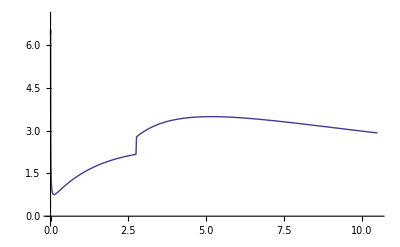

```mathematica
xm=0;
xM=10.5;
ym=-0.2;
yM=7.;
gr3LP=ListPlot[dataLP,Joined-> True,PlotRange-> {{xm,xM},{ym,yM}}]
```

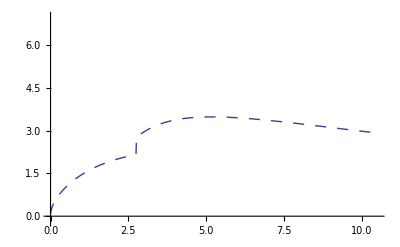

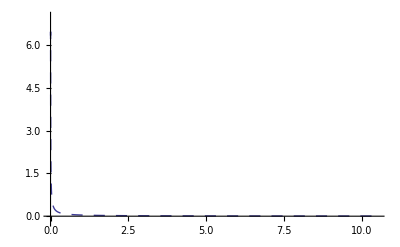

```mathematica
gr4E=ListPlot[dataLPE,Joined->True,PlotStyle->Dashing[{0.02,0.02}],PlotRange->{{xm,xM},{ym,yM}}]
gr4I=ListPlot[dataLPI,Joined->True,PlotStyle->Dashing[{0.02,0.02}],PlotRange->{{xm,xM},{ym,yM}}]
```

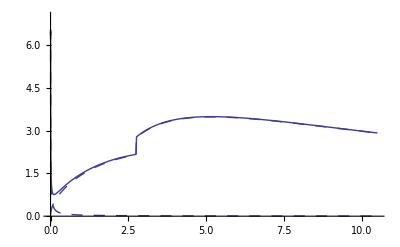

```mathematica
Show[gr3LP,gr4E,gr4I,PlotRange-> {{xm,xM},{ym,yM}}]
```

#### E vs x and range R

```mathematica
Clear[dxELP,ExLP, xELP]
```

```mathematica
dEdxELP=Interpolation[dataLP];
```

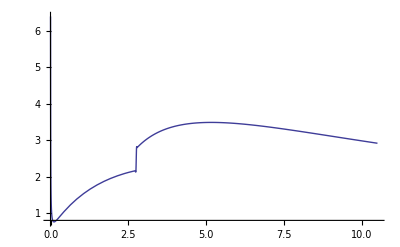

```mathematica
Plot[dEdxELP[e],{e,emin,emax}]
```

```mathematica
E0=emax;
dxELP[E_] :=1/dEdxELP[E]
xELP[E_]   := NIntegrate[1/dEdxELP[Ep],{Ep,E,E0},PrecisionGoal->Automatic]
```

```mathematica
FindRoot[dEdxELP[EE]==0,{EE,0.0.01}];
EzeroLPa=EE /. %
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0000776089} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

0.0000823687

```mathematica
FindRoot[dEdxELP[EE]==0,{EE, EzeroLPa}];
EzeroLP=EE /. %
```

InterpolatingFunction::dmval: Input value {0.0000823687} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.0000823687

```mathematica
dEdxELP[EzeroLP]
```

InterpolatingFunction::dmval: Input value {0.0000823687} lies outside the range of data in the interpolating function. Extrapolation will be used.

-2.31152×10^-16

```mathematica
eth=1.04*T/1000
dEdxELP[eth]
xELP[eth]
```

0.00052

InterpolatingFunction::dmval: Input value {0.00052} lies outside the range of data in the interpolating function. Extrapolation will be used.

4.64458

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ep near {Ep} = {2.76877}. NIntegrate obtained 4.24545 and 9.73225×10^-6 for the integral and error estimates.

4.24545

```mathematica
NN=1000;
E1=eth;
dE=(E0-E1)/NN;
dataExLP=Table[{xELP[E],E},{E,E1,emax,dE}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ep near {Ep} = {2.76877}. NIntegrate obtained 4.24545 and 9.73225×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ep near {Ep} = {2.75108}. NIntegrate obtained 4.22665 and 0.0000117994 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ep near {Ep} = {2.77927}. NIntegrate obtained 4.21605 and 4.24972×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

```mathematica
xy1=dataExLP[[2]]
xy2=dataExLP[[1]]
dxy=xy2-xy1
m=dxy[[2]]/dxy[[1]]
b=xy1[[2]]-m*xy1[[1]]
xRLP=-b/m
```

{4.2422,0.0110195}

{4.24545,0.00052}

{0.0032538,-0.0104995}

-3.22684

13.6999

4.24561

```mathematica
dataExLP=Prepend[dataExLP,{xRLP,0}]
```

{{4.24561,0},{4.24545,0.00052},{4.2422,0.0110195},{4.23559,0.021519},{4.22665,0.0320184},{4.21605,0.0425179},{4.20429,0.0530174},{4.19172,0.0635169},{4.17862,0.0740164},{4.16516,0.0845158},{4.15147,0.0950153},{4.13768,0.105515},{4.12384,0.116014},{4.11002,0.126514},{4.09626,0.137013},{4.08258,0.147513},{4.06901,0.158012},{4.05556,0.168512},{4.04225,0.179011},{4.02908,0.189511},{4.01606,0.20001},{4.00318,0.21051},{3.99046,0.221009},{3.97789,0.231509},{3.96547,0.242008},{3.9532,0.252508},{3.94108,0.263007},{3.9291,0.273506},{3.91726,0.284006},{3.90556,0.294505},{3.894,0.305005},{3.88257,0.315504},{3.87127,0.326004},{3.86009,0.336503},{3.84904,0.347003},{3.83811,0.357502},{3.8273,0.368002},{3.8166,0.378501},{3.80601,0.389001},{3.79554,0.3995},{3.78516,0.41},{3.7749,0.420499},{3.76473,0.430999},{3.75466,0.441498},{3.74469,0.451998},{3.73481,0.462497},{3.72502,0.472997},{3.71532,0.483496},{3.70571,0.493996},{3.69618,0.504495},{3.68673,0.514995},{3.67737,0.525494},{3.66808,0.535993},{3.65887,0.546493},{3.64974,0.556992},{3.64068,0.567492},{3.63169,0.577991},{3.62277,0.588491},{3.61392,0.59899},{3.60514,0.60949},{3.59642,0.619989},{3.58777,0.630489},{3.57918,0.640988},{3.57065,0.651488},{3.56218,0.661987},{3.55377,0.672487},{3.54542,0.682986},{3.53712,0.693486},{3.52888,0.703985},{3.52069,0.714485},{3.51256,0.724984},{3.50448,0.735484},{3.49645,0.745983},{3.48847,0.756483},{3.48054,0.766982},{3.47266,0.777482},{3.46482,0.787981},{3.45703,0.79848},{3.44929,0.80898},{3.44159,0.819479},{3.43394,0.829979},{3.42633,0.840478},{3.41876,0.850978},{3.41123,0.861477},{3.40374,0.871977},{3.3963,0.882476},{3.38889,0.892976},{3.38152,0.903475},{3.37419,0.913975},{3.3669,0.924474},{3.35964,0.934974},{3.35242,0.945473},{3.34523,0.955973},{3.33808,0.966472},{3.33097,0.976972},{3.32389,0.987471},{3.31684,0.997971},{3.30982,1.00847},{3.30284,1.01897},{3.29588,1.02947},{3.28896,1.03997},{3.28207,1.05047},{3.27521,1.06097},{3.26838,1.07147},{3.26158,1.08197},{3.25481,1.09247},{3.24806,1.10297},{3.24135,1.11346},{3.23466,1.12396},{3.22799,1.13446},{3.22136,1.14496},{3.21475,1.15546},{3.20817,1.16596},{3.20161,1.17646},{3.19508,1.18696},{3.18857,1.19746},{3.18209,1.20796},{3.17563,1.21846},{3.16919,1.22896},{3.16278,1.23946},{3.15639,1.24996},{3.15003,1.26046},{3.14368,1.27096},{3.13736,1.28146},{3.13106,1.29196},{3.12478,1.30246},{3.11853,1.31296},{3.11229,1.32345},{3.10607,1.33395},{3.09988,1.34445},{3.0937,1.35495},{3.08755,1.36545},{3.08141,1.37595},{3.0753,1.38645},{3.0692,1.39695},{3.06312,1.40745},{3.05706,1.41795},{3.05102,1.42845},{3.045,1.43895},{3.03899,1.44945},{3.033,1.45995},{3.02703,1.47045},{3.02108,1.48095},{3.01514,1.49145},{3.00922,1.50195},{3.00332,1.51245},{2.99743,1.52294},{2.99156,1.53344},{2.98571,1.54394},{2.97987,1.55444},{2.97404,1.56494},{2.96824,1.57544},{2.96244,1.58594},{2.95666,1.59644},{2.9509,1.60694},{2.94515,1.61744},{2.93942,1.62794},{2.9337,1.63844},{2.92799,1.64894},{2.9223,1.65944},{2.91662,1.66994},{2.91095,1.68044},{2.9053,1.69094},{2.89966,1.70144},{2.89404,1.71194},{2.88843,1.72243},{2.88283,1.73293},{2.87724,1.74343},{2.87167,1.75393},{2.8661,1.76443},{2.86055,1.77493},{2.85502,1.78543},{2.84949,1.79593},{2.84398,1.80643},{2.83847,1.81693},{2.83298,1.82743},{2.8275,1.83793},{2.82204,1.84843},{2.81658,1.85893},{2.81113,1.86943},{2.8057,1.87993},{2.80027,1.89043},{2.79486,1.90093},{2.78946,1.91143},{2.78406,1.92192},{2.77868,1.93242},{2.77331,1.94292},{2.76795,1.95342},{2.76259,1.96392},{2.75725,1.97442},{2.75192,1.98492},{2.74659,1.99542},{2.74128,2.00592},{2.73598,2.01642},{2.73068,2.02692},{2.7254,2.03742},{2.72012,2.04792},{2.71485,2.05842},{2.70959,2.06892},{2.70434,2.07942},{2.6991,2.08992},{2.69387,2.10042},{2.68864,2.11092},{2.68343,2.12141},{2.67822,2.13191},{2.67302,2.14241},{2.66783,2.15291},{2.66265,2.16341},{2.65747,2.17391},{2.6523,2.18441},{2.64714,2.19491},{2.64199,2.20541},{2.63685,2.21591},{2.63171,2.22641},{2.62658,2.23691},{2.62146,2.24741},{2.61635,2.25791},{2.61124,2.26841},{2.60614,2.27891},{2.60105,2.28941},{2.59596,2.29991},{2.59088,2.31041},{2.58581,2.32091},{2.58074,2.3314},{2.57569,2.3419},{2.57063,2.3524},{2.56559,2.3629},{2.56055,2.3734},{2.55552,2.3839},{2.55049,2.3944},{2.54547,2.4049},{2.54046,2.4154},{2.53545,2.4259},{2.53045,2.4364},{2.52545,2.4469},{2.52046,2.4574},{2.51548,2.4679},{2.5105,2.4784},{2.50553,2.4889},{2.50056,2.4994},{2.4956,2.5099},{2.49065,2.5204},{2.4857,2.53089},{2.48075,2.54139},{2.47582,2.55189},{2.47088,2.56239},{2.46595,2.57289},{2.46103,2.58339},{2.45611,2.59389},{2.4512,2.60439},{2.44629,2.61489},{2.44139,2.62539},{2.43649,2.63589},{2.4316,2.64639},{2.42671,2.65689},{2.42183,2.66739},{2.41695,2.67789},{2.41208,2.68839},{2.40721,2.69889},{2.40235,2.70939},{2.39749,2.71989},{2.39263,2.73038},{2.3877,2.74088},{2.383,2.75138},{2.37897,2.76188},{2.37524,2.77238},{2.3715,2.78288},{2.36775,2.79338},{2.36402,2.80388},{2.3603,2.81438},{2.35659,2.82488},{2.35289,2.83538},{2.34921,2.84588},{2.34553,2.85638},{2.34187,2.86688},{2.33822,2.87738},{2.33457,2.88788},{2.33094,2.89838},{2.32732,2.90888},{2.32371,2.91938},{2.32011,2.92987},{2.31652,2.94037},{2.31293,2.95087},{2.30936,2.96137},{2.3058,2.97187},{2.30224,2.98237},{2.2987,2.99287},{2.29516,3.00337},{2.29163,3.01387},{2.28811,3.02437},{2.2846,3.03487},{2.28109,3.04537},{2.2776,3.05587},{2.27411,3.06637},{2.27063,3.07687},{2.26716,3.08737},{2.2637,3.09787},{2.26024,3.10837},{2.25679,3.11887},{2.25335,3.12937},{2.24991,3.13986},{2.24648,3.15036},{2.24306,3.16086},{2.23965,3.17136},{2.23624,3.18186},{2.23284,3.19236},{2.22944,3.20286},{2.22605,3.21336},{2.22267,3.22386},{2.21929,3.23436},{2.21592,3.24486},{2.21256,3.25536},{2.2092,3.26586},{2.20585,3.27636},{2.2025,3.28686},{2.19916,3.29736},{2.19583,3.30786},{2.1925,3.31836},{2.18917,3.32886},{2.18585,3.33935},{2.18254,3.34985},{2.17923,3.36035},{2.17592,3.37085},{2.17262,3.38135},{2.16933,3.39185},{2.16604,3.40235},{2.16276,3.41285},{2.15948,3.42335},{2.1562,3.43385},{2.15293,3.44435},{2.14966,3.45485},{2.1464,3.46535},{2.14314,3.47585},{2.13989,3.48635},{2.13664,3.49685},{2.1334,3.50735},{2.13016,3.51785},{2.12692,3.52835},{2.12369,3.53884},{2.12046,3.54934},{2.11723,3.55984},{2.11401,3.57034},{2.1108,3.58084},{2.10758,3.59134},{2.10437,3.60184},{2.10117,3.61234},{2.09796,3.62284},{2.09477,3.63334},{2.09157,3.64384},{2.08838,3.65434},{2.08519,3.66484},{2.082,3.67534},{2.07882,3.68584},{2.07564,3.69634},{2.07247,3.70684},{2.06929,3.71734},{2.06612,3.72784},{2.06296,3.73833},{2.05979,3.74883},{2.05663,3.75933},{2.05347,3.76983},{2.05032,3.78033},{2.04717,3.79083},{2.04402,3.80133},{2.04087,3.81183},{2.03773,3.82233},{2.03459,3.83283},{2.03145,3.84333},{2.02831,3.85383},{2.02518,3.86433},{2.02205,3.87483},{2.01892,3.88533},{2.01579,3.89583},{2.01267,3.90633},{2.00954,3.91683},{2.00643,3.92733},{2.00331,3.93783},{2.00019,3.94832},{1.99708,3.95882},{1.99397,3.96932},{1.99086,3.97982},{1.98776,3.99032},{1.98465,4.00082},{1.98155,4.01132},{1.97845,4.02182},{1.97535,4.03232},{1.97226,4.04282},{1.96916,4.05332},{1.96607,4.06382},{1.96298,4.07432},{1.95989,4.08482},{1.95681,4.09532},{1.95372,4.10582},{1.95064,4.11632},{1.94756,4.12682},{1.94448,4.13732},{1.9414,4.14781},{1.93832,4.15831},{1.93525,4.16881},{1.93218,4.17931},{1.9291,4.18981},{1.92603,4.20031},{1.92297,4.21081},{1.9199,4.22131},{1.91683,4.23181},{1.91377,4.24231},{1.91071,4.25281},{1.90764,4.26331},{1.90458,4.27381},{1.90153,4.28431},{1.89847,4.29481},{1.89541,4.30531},{1.89236,4.31581},{1.88931,4.32631},{1.88625,4.33681},{1.8832,4.3473},{1.88015,4.3578},{1.8771,4.3683},{1.87406,4.3788},{1.87101,4.3893},{1.86796,4.3998},{1.86492,4.4103},{1.86188,4.4208},{1.85883,4.4313},{1.85579,4.4418},{1.85275,4.4523},{1.84971,4.4628},{1.84668,4.4733},{1.84364,4.4838},{1.8406,4.4943},{1.83757,4.5048},{1.83453,4.5153},{1.8315,4.5258},{1.82847,4.5363},{1.82544,4.54679},{1.8224,4.55729},{1.81937,4.56779},{1.81634,4.57829},{1.81332,4.58879},{1.81029,4.59929},{1.80726,4.60979},{1.80423,4.62029},{1.80121,4.63079},{1.79818,4.64129},{1.79516,4.65179},{1.79213,4.66229},{1.78911,4.67279},{1.78609,4.68329},{1.78307,4.69379},{1.78004,4.70429},{1.77702,4.71479},{1.774,4.72529},{1.77098,4.73579},{1.76796,4.74628},{1.76494,4.75678},{1.76193,4.76728},{1.75891,4.77778},{1.75589,4.78828},{1.75287,4.79878},{1.74986,4.80928},{1.74684,4.81978},{1.74382,4.83028},{1.74081,4.84078},{1.73779,4.85128},{1.73478,4.86178},{1.73177,4.87228},{1.72875,4.88278},{1.72574,4.89328},{1.72272,4.90378},{1.71971,4.91428},{1.7167,4.92478},{1.71369,4.93528},{1.71067,4.94578},{1.70766,4.95627},{1.70465,4.96677},{1.70164,4.97727},{1.69863,4.98777},{1.69562,4.99827},{1.69261,5.00877},{1.68959,5.01927},{1.68658,5.02977},{1.68357,5.04027},{1.68056,5.05077},{1.67755,5.06127},{1.67454,5.07177},{1.67153,5.08227},{1.66852,5.09277},{1.66551,5.10327},{1.6625,5.11377},{1.65949,5.12427},{1.65648,5.13477},{1.65347,5.14527},{1.65046,5.15576},{1.64745,5.16626},{1.64444,5.17676},{1.64143,5.18726},{1.63842,5.19776},{1.63541,5.20826},{1.6324,5.21876},{1.6294,5.22926},{1.62639,5.23976},{1.62338,5.25026},{1.62037,5.26076},{1.61735,5.27126},{1.61434,5.28176},{1.61133,5.29226},{1.60832,5.30276},{1.60531,5.31326},{1.6023,5.32376},{1.59929,5.33426},{1.59628,5.34476},{1.59327,5.35525},{1.59026,5.36575},{1.58725,5.37625},{1.58423,5.38675},{1.58122,5.39725},{1.57821,5.40775},{1.5752,5.41825},{1.57218,5.42875},{1.56917,5.43925},{1.56616,5.44975},{1.56315,5.46025},{1.56013,5.47075},{1.55712,5.48125},{1.5541,5.49175},{1.55109,5.50225},{1.54807,5.51275},{1.54506,5.52325},{1.54204,5.53375},{1.53903,5.54425},{1.53601,5.55474},{1.53299,5.56524},{1.52998,5.57574},{1.52696,5.58624},{1.52394,5.59674},{1.52093,5.60724},{1.51791,5.61774},{1.51489,5.62824},{1.51187,5.63874},{1.50885,5.64924},{1.50583,5.65974},{1.50281,5.67024},{1.49979,5.68074},{1.49677,5.69124},{1.49375,5.70174},{1.49072,5.71224},{1.4877,5.72274},{1.48468,5.73324},{1.48165,5.74374},{1.47863,5.75424},{1.47561,5.76473},{1.47258,5.77523},{1.46956,5.78573},{1.46653,5.79623},{1.4635,5.80673},{1.46048,5.81723},{1.45745,5.82773},{1.45442,5.83823},{1.45139,5.84873},{1.44836,5.85923},{1.44533,5.86973},{1.4423,5.88023},{1.43927,5.89073},{1.43624,5.90123},{1.43321,5.91173},{1.43018,5.92223},{1.42714,5.93273},{1.42411,5.94323},{1.42108,5.95373},{1.41804,5.96422},{1.41501,5.97472},{1.41197,5.98522},{1.40893,5.99572},{1.4059,6.00622},{1.40286,6.01672},{1.39982,6.02722},{1.39678,6.03772},{1.39374,6.04822},{1.3907,6.05872},{1.38766,6.06922},{1.38462,6.07972},{1.38157,6.09022},{1.37853,6.10072},{1.37549,6.11122},{1.37244,6.12172},{1.36939,6.13222},{1.36635,6.14272},{1.3633,6.15322},{1.36025,6.16371},{1.35721,6.17421},{1.35416,6.18471},{1.35111,6.19521},{1.34806,6.20571},{1.34501,6.21621},{1.34195,6.22671},{1.3389,6.23721},{1.33585,6.24771},{1.33279,6.25821},{1.32974,6.26871},{1.32668,6.27921},{1.32363,6.28971},{1.32057,6.30021},{1.31751,6.31071},{1.31445,6.32121},{1.31139,6.33171},{1.30833,6.34221},{1.30527,6.35271},{1.30221,6.3632},{1.29914,6.3737},{1.29608,6.3842},{1.29301,6.3947},{1.28995,6.4052},{1.28688,6.4157},{1.28382,6.4262},{1.28075,6.4367},{1.27768,6.4472},{1.27461,6.4577},{1.27154,6.4682},{1.26847,6.4787},{1.26539,6.4892},{1.26232,6.4997},{1.25925,6.5102},{1.25617,6.5207},{1.2531,6.5312},{1.25002,6.5417},{1.24694,6.5522},{1.24386,6.5627},{1.24078,6.57319},{1.2377,6.58369},{1.23462,6.59419},{1.23154,6.60469},{1.22845,6.61519},{1.22537,6.62569},{1.22229,6.63619},{1.2192,6.64669},{1.21611,6.65719},{1.21302,6.66769},{1.20994,6.67819},{1.20685,6.68869},{1.20375,6.69919},{1.20066,6.70969},{1.19757,6.72019},{1.19448,6.73069},{1.19138,6.74119},{1.18829,6.75169},{1.18519,6.76219},{1.18209,6.77268},{1.17899,6.78318},{1.17589,6.79368},{1.17279,6.80418},{1.16969,6.81468},{1.16659,6.82518},{1.16348,6.83568},{1.16038,6.84618},{1.15727,6.85668},{1.15417,6.86718},{1.15106,6.87768},{1.14795,6.88818},{1.14484,6.89868},{1.14173,6.90918},{1.13862,6.91968},{1.13551,6.93018},{1.13239,6.94068},{1.12928,6.95118},{1.12616,6.96168},{1.12304,6.97217},{1.11993,6.98267},{1.11681,6.99317},{1.11369,7.00367},{1.11056,7.01417},{1.10744,7.02467},{1.10432,7.03517},{1.10119,7.04567},{1.09807,7.05617},{1.09494,7.06667},{1.09181,7.07717},{1.08868,7.08767},{1.08555,7.09817},{1.08242,7.10867},{1.07929,7.11917},{1.07616,7.12967},{1.07302,7.14017},{1.06989,7.15067},{1.06675,7.16117},{1.06361,7.17166},{1.06047,7.18216},{1.05733,7.19266},{1.05419,7.20316},{1.05105,7.21366},{1.04791,7.22416},{1.04476,7.23466},{1.04161,7.24516},{1.03847,7.25566},{1.03532,7.26616},{1.03217,7.27666},{1.02902,7.28716},{1.02587,7.29766},{1.02271,7.30816},{1.01956,7.31866},{1.01641,7.32916},{1.01325,7.33966},{1.01009,7.35016},{1.00693,7.36066},{1.00377,7.37115},{1.00061,7.38165},{0.99745,7.39215},{0.994287,7.40265},{0.991122,7.41315},{0.987956,7.42365},{0.984789,7.43415},{0.981621,7.44465},{0.978452,7.45515},{0.975281,7.46565},{0.972109,7.47615},{0.968936,7.48665},{0.965762,7.49715},{0.962587,7.50765},{0.95941,7.51815},{0.956232,7.52865},{0.953053,7.53915},{0.949872,7.54965},{0.946691,7.56015},{0.943508,7.57065},{0.940324,7.58114},{0.937139,7.59164},{0.933952,7.60214},{0.930764,7.61264},{0.927575,7.62314},{0.924385,7.63364},{0.921193,7.64414},{0.918001,7.65464},{0.914807,7.66514},{0.911611,7.67564},{0.908415,7.68614},{0.905217,7.69664},{0.902018,7.70714},{0.898817,7.71764},{0.895616,7.72814},{0.892413,7.73864},{0.889209,7.74914},{0.886003,7.75964},{0.882796,7.77014},{0.879588,7.78063},{0.876379,7.79113},{0.873168,7.80163},{0.869956,7.81213},{0.866743,7.82263},{0.863529,7.83313},{0.860313,7.84363},{0.857096,7.85413},{0.853877,7.86463},{0.850658,7.87513},{0.847437,7.88563},{0.844214,7.89613},{0.840991,7.90663},{0.837766,7.91713},{0.834539,7.92763},{0.831312,7.93813},{0.828083,7.94863},{0.824852,7.95913},{0.821621,7.96963},{0.818388,7.98012},{0.815154,7.99062},{0.811918,8.00112},{0.808681,8.01162},{0.805443,8.02212},{0.802203,8.03262},{0.798962,8.04312},{0.79572,8.05362},{0.792477,8.06412},{0.789232,8.07462},{0.785985,8.08512},{0.782738,8.09562},{0.779488,8.10612},{0.776238,8.11662},{0.772986,8.12712},{0.769733,8.13762},{0.766479,8.14812},{0.763223,8.15862},{0.759966,8.16912},{0.756707,8.17961},{0.753447,8.19011},{0.750186,8.20061},{0.746923,8.21111},{0.743659,8.22161},{0.740394,8.23211},{0.737127,8.24261},{0.733859,8.25311},{0.730589,8.26361},{0.727318,8.27411},{0.724046,8.28461},{0.720772,8.29511},{0.717497,8.30561},{0.71422,8.31611},{0.710942,8.32661},{0.707663,8.33711},{0.704382,8.34761},{0.7011,8.35811},{0.697816,8.36861},{0.694531,8.37911},{0.691245,8.3896},{0.687957,8.4001},{0.684668,8.4106},{0.681377,8.4211},{0.678085,8.4316},{0.674792,8.4421},{0.671497,8.4526},{0.668201,8.4631},{0.664903,8.4736},{0.661604,8.4841},{0.658303,8.4946},{0.655001,8.5051},{0.651698,8.5156},{0.648393,8.5261},{0.645087,8.5366},{0.641779,8.5471},{0.63847,8.5576},{0.635159,8.5681},{0.631847,8.5786},{0.628534,8.58909},{0.625219,8.59959},{0.621903,8.61009},{0.618585,8.62059},{0.615265,8.63109},{0.611945,8.64159},{0.608623,8.65209},{0.605299,8.66259},{0.601974,8.67309},{0.598647,8.68359},{0.595319,8.69409},{0.59199,8.70459},{0.588659,8.71509},{0.585327,8.72559},{0.581993,8.73609},{0.578657,8.74659},{0.575321,8.75709},{0.571982,8.76759},{0.568643,8.77809},{0.565301,8.78858},{0.561959,8.79908},{0.558615,8.80958},{0.555269,8.82008},{0.551922,8.83058},{0.548573,8.84108},{0.545223,8.85158},{0.541872,8.86208},{0.538519,8.87258},{0.535164,8.88308},{0.531808,8.89358},{0.52845,8.90408},{0.525091,8.91458},{0.521731,8.92508},{0.518369,8.93558},{0.515005,8.94608},{0.51164,8.95658},{0.508274,8.96708},{0.504906,8.97758},{0.501536,8.98807},{0.498165,8.99857},{0.494793,9.00907},{0.491419,9.01957},{0.488043,9.03007},{0.484666,9.04057},{0.481288,9.05107},{0.477908,9.06157},{0.474526,9.07207},{0.471143,9.08257},{0.467758,9.09307},{0.464372,9.10357},{0.460985,9.11407},{0.457596,9.12457},{0.454205,9.13507},{0.450813,9.14557},{0.447419,9.15607},{0.444024,9.16657},{0.440627,9.17707},{0.437229,9.18757},{0.433829,9.19806},{0.430427,9.20856},{0.427024,9.21906},{0.42362,9.22956},{0.420214,9.24006},{0.416807,9.25056},{0.413397,9.26106},{0.409987,9.27156},{0.406575,9.28206},{0.403161,9.29256},{0.399746,9.30306},{0.396329,9.31356},{0.392911,9.32406},{0.389491,9.33456},{0.386069,9.34506},{0.382646,9.35556},{0.379222,9.36606},{0.375796,9.37656},{0.372368,9.38706},{0.368939,9.39755},{0.365508,9.40805},{0.362076,9.41855},{0.358642,9.42905},{0.355207,9.43955},{0.35177,9.45005},{0.348331,9.46055},{0.344891,9.47105},{0.34145,9.48155},{0.338006,9.49205},{0.334562,9.50255},{0.331115,9.51305},{0.327667,9.52355},{0.324218,9.53405},{0.320767,9.54455},{0.317314,9.55505},{0.31386,9.56555},{0.310404,9.57605},{0.306947,9.58655},{0.303488,9.59704},{0.300027,9.60754},{0.296565,9.61804},{0.293101,9.62854},{0.289636,9.63904},{0.286169,9.64954},{0.282701,9.66004},{0.279231,9.67054},{0.275759,9.68104},{0.272286,9.69154},{0.268811,9.70204},{0.265335,9.71254},{0.261857,9.72304},{0.258377,9.73354},{0.254896,9.74404},{0.251413,9.75454},{0.247929,9.76504},{0.244443,9.77554},{0.240955,9.78604},{0.237466,9.79653},{0.233976,9.80703},{0.230483,9.81753},{0.226989,9.82803},{0.223494,9.83853},{0.219997,9.84903},{0.216498,9.85953},{0.212997,9.87003},{0.209495,9.88053},{0.205992,9.89103},{0.202487,9.90153},{0.19898,9.91203},{0.195471,9.92253},{0.191961,9.93303},{0.18845,9.94353},{0.184937,9.95403},{0.181422,9.96453},{0.177905,9.97503},{0.174387,9.98553},{0.170867,9.99602},{0.167346,10.0065},{0.163823,10.017},{0.160299,10.0275},{0.156772,10.038},{0.153245,10.0485},{0.149715,10.059},{0.146184,10.0695},{0.142651,10.08},{0.139117,10.0905},{0.135581,10.101},{0.132043,10.1115},{0.128504,10.122},{0.124963,10.1325},{0.121421,10.143},{0.117877,10.1535},{0.114331,10.164},{0.110784,10.1745},{0.107235,10.185},{0.103684,10.1955},{0.100132,10.206},{0.0965779,10.2165},{0.0930224,10.227},{0.0894652,10.2375},{0.0859064,10.248},{0.0823459,10.2585},{0.0787838,10.269},{0.07522,10.2795},{0.0716546,10.29},{0.0680876,10.3005},{0.0645189,10.311},{0.0609485,10.3215},{0.0573765,10.332},{0.0538029,10.3425},{0.0502276,10.353},{0.0466507,10.3635},{0.0430721,10.374},{0.0394919,10.3845},{0.03591,10.395},{0.0323264,10.4055},{0.0287412,10.416},{0.0251544,10.4265},{0.0215659,10.437},{0.0179757,10.4475},{0.0143839,10.458},{0.0107904,10.4685},{0.00719526,10.479},{0.00359846,10.4895},{0.,10.5}}

```mathematica
ExLP=Interpolation[dataExLP];
```

```mathematica
ExLP[xRLP]
```

0.

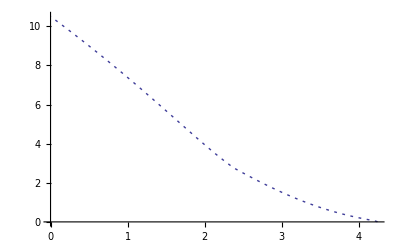

```mathematica
grExLP=ListPlot[dataExLP,Joined->True,PlotStyle->Dashing[{0.005,0.01}]]
```

#### dE/dx vs E: dEdxELP

```mathematica
dEdxEeLP =Interpolation[dataLPE];
dEdxEiLP =Interpolation[dataLPI];
```

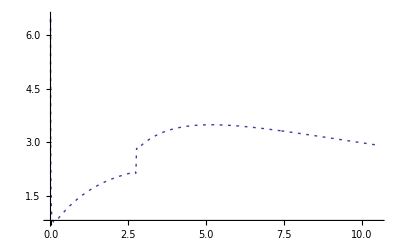

```mathematica
grdEdxELP=Plot[dEdxELP[e],{e,emin,emax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->10000,PlotRange->All]
```

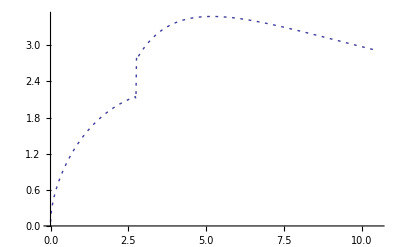

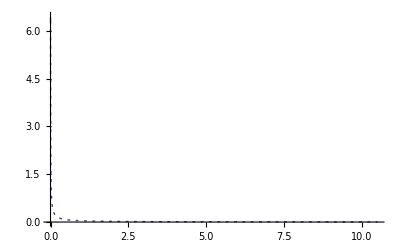

```mathematica
grdEdxEeLP=Plot[dEdxEeLP[e],{e,emin,emax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->1000,PlotRange->All]
grdEdxEiLP=Plot[dEdxEiLP[e],{e,emin,emax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->1000,PlotRange->All]
```

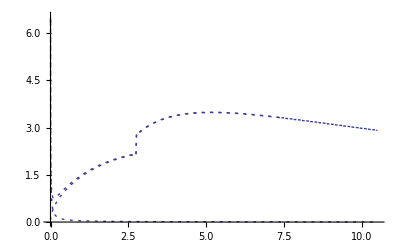

```mathematica
grdEdxEeiLP=Show[grdEdxEeLP,grdEdxEiLP,grdEdxELP]
```

#### dE/dx vs x: dEdxx LP

```mathematica
dEdxxLP[x_] := dEdxELP[ExLP[x]]
dEdxxeLP[x_] := dEdxEeLP[ExLP[x]]
dEdxxiLP[x_] := dEdxEiLP[ExLP[x]]
```

```mathematica
xRLP
xRLPmax=FindRoot[dEdxxLP[x]==0,{x,xRLP}][[1,2]]
```

4.24561

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0000776432} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

4.24559

```mathematica
dEdxxLP[xRLP]
dEdxxLP[xRLPmax]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-1.32218

InterpolatingFunction::dmval: Input value {0.0000823687} lies outside the range of data in the interpolating function. Extrapolation will be used.

-3.21379×10^-9

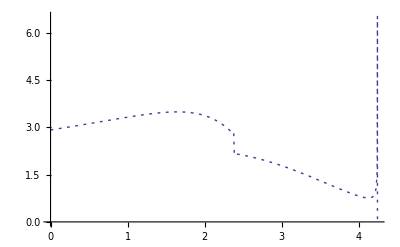

```mathematica
grdEdxxLP=Plot[dEdxxLP[x],{x,0,xRLPmax},PlotStyle->Dashing[{0.005,0.01}],
PlotPoints->1000,PlotPoints->All,PlotRange->All]
```

```mathematica
x0=2.5;
NIntegrate[dEdxxLP[x],{x,0,x0},MaxRecursion->10]
NIntegrate[dEdxxLP[x],{x,x0,xRLPmax},MaxRecursion->100]
% + %%
```

7.99942

2.50148

10.5009

```mathematica
100*(%-E0)/E0
```

0.00853807

```mathematica
100*eth/E0
```

0.00495238

partitioned among plasma components

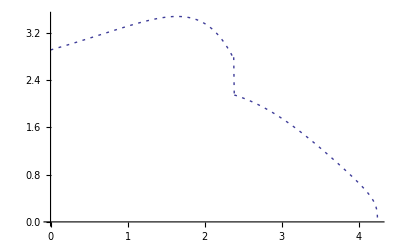

```mathematica
grdEdxxeLP=Plot[dEdxxeLP[x] ,{x,0,xRLPmax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->1000,PlotPoints->All]
```

```mathematica
Ee=NIntegrate[dEdxxeLP[x],{x,0,xRLPmax}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.38808}. NIntegrate obtained 10.3053 and 0.0000122235 for the integral and error estimates.

10.3053

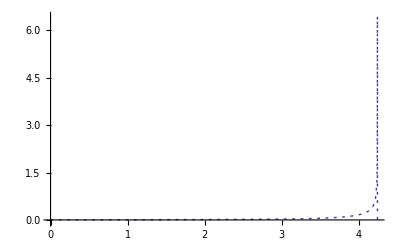

```mathematica
grdEdxxiLP=Plot[dEdxxiLP[x] ,{x,0,xRLPmax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->1000,PlotRange->All]
```

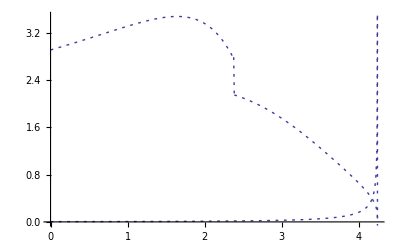

```mathematica
grdEdxxeiLP=Show[grdEdxxeLP,grdEdxxiLP]
```

```mathematica
xRLPmax
```

4.24559

```mathematica
x1=2.5;
NIntegrate[dEdxxiLP[x],{x,0,x1},MaxRecursion->10]
NIntegrate[dEdxxiLP[x],{x,x1,xRLPmax},MaxRecursion->10]
Ei=% + %%
```

0.0209575

0.174659

0.195616

```mathematica
{Ee,Ei,Ee+Ei,E0}
```

{10.3053,0.195616,10.5009,10.5}

```mathematica
100*(E0-Ee-Ei)/E0
```

-0.00858059

### BPS

#### evaluate data

```mathematica
emin=0.001;
emax=10.5;
```

```mathematica
E1=emin;
E2=0.03;
NN=600;
dE=(E2-E1)/NN;
dataBPSa=Table[{EE,dedxi[VP[EE]]},{EE,E1,E2,dE}];

E1=E2+dE;
E2=0.25;
NN=100;
dE=(E2-E1)/NN;
dataBPSb=Table[{EE,dedxi[VP[EE]]},{EE,E1,E2,dE}];

E1=E2+dE;
E2=emax;
NN=100;
dE=(E2-E1)/NN;
dataBPSc=Table[{EE,dedxi[VP[EE]]},{EE,E1,E2,dE}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in StoppingPower`PrivateBPS`u near {StoppingPower`PrivateBPS`u} = {0.0117943}. NIntegrate obtained -1.05454×10^-8 and 1.14507×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in StoppingPower`PrivateBPS`u near {StoppingPower`PrivateBPS`u} = {0.0683438}. NIntegrate obtained -1.15894×10^-8 and 7.06876×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in StoppingPower`PrivateBPS`u near {StoppingPower`PrivateBPS`u} = {0.0031055}. NIntegrate obtained -1.26826×10^-8 and 2.00739×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
dataBPSEI=Join[dataBPSa,dataBPSb,dataBPSc]
```

{{0.001,{-0.00628316,0.328094,0.359629}},{0.00104833,{-0.00563398,0.390386,0.42025}},{0.00109667,{-0.00493806,0.449083,0.47623}},{0.001145,{-0.00420491,0.504314,0.527811}},{0.00119333,{-0.00344305,0.556216,0.575238}},{0.00124167,{-0.00266008,0.604927,0.618757}},{0.00129,{-0.00186276,0.650589,0.658609}},{0.00133833,{-0.00105705,0.693342,0.69503}},{0.00138667,{-0.000248172,0.733326,0.728246}},{0.001435,{0.000559312,0.770679,0.758477}},{0.00148333,{0.00136148,0.805537,0.78593}},{0.00153167,{0.002155,0.838032,0.810803}},{0.00158,{0.00293703,0.868291,0.833281}},{0.00162833,{0.00370523,0.896439,0.853541}},{0.00167667,{0.00445769,0.922593,0.871748}},{0.001725,{0.00519287,0.946866,0.888054}},{0.00177333,{0.00590957,0.969368,0.902605}},{0.00182167,{0.00660691,0.990202,0.915534}},{0.00187,{0.00728423,1.00946,0.926966}},{0.00191833,{0.00794113,1.02725,0.937017}},{0.00196667,{0.00857739,1.04364,0.945795}},{0.002015,{0.00919296,1.05873,0.953399}},{0.00206333,{0.00978791,1.07258,0.959923}},{0.00211167,{0.0103625,1.08528,0.965451}},{0.00216,{0.0109169,1.0969,0.970063}},{0.00220833,{0.0114516,1.10749,0.973832}},{0.00225667,{0.011967,1.11712,0.976827}},{0.002305,{0.0124635,1.12585,0.979109}},{0.00235333,{0.0129418,1.13373,0.980738}},{0.00240167,{0.0134023,1.14082,0.981766}},{0.00245,{0.0138456,1.14716,0.982244}},{0.00249833,{0.0142723,1.15279,0.982217}},{0.00254667,{0.014683,1.15777,0.981727}},{0.002595,{0.0150783,1.16212,0.980814}},{0.00264333,{0.0154587,1.16589,0.979513}},{0.00269167,{0.0158249,1.16912,0.977858}},{0.00274,{0.0161773,1.17183,0.975881}},{0.00278833,{0.0165166,1.17405,0.973609}},{0.00283667,{0.0168433,1.17582,0.971069}},{0.002885,{0.0171578,1.17717,0.968285}},{0.00293333,{0.0174608,1.17811,0.96528}},{0.00298167,{0.0177527,1.17868,0.962074}},{0.00303,{0.018034,1.1789,0.958687}},{0.00307833,{0.0183052,1.17878,0.955136}},{0.00312667,{0.0185667,1.17836,0.951438}},{0.003175,{0.0188188,1.17765,0.947608}},{0.00322333,{0.0190622,1.17666,0.94366}},{0.00327167,{0.019297,1.17542,0.939606}},{0.00332,{0.0195237,1.17394,0.93546}},{0.00336833,{0.0197427,1.17224,0.93123}},{0.00341667,{0.0199543,1.17032,0.926928}},{0.003465,{0.0201589,1.16822,0.922563}},{0.00351333,{0.0203567,1.16593,0.918144}},{0.00356167,{0.020548,1.16347,0.913678}},{0.00361,{0.0207332,1.16085,0.909173}},{0.00365833,{0.0209125,1.15808,0.904635}},{0.00370667,{0.0210862,1.15517,0.900071}},{0.003755,{0.0212545,1.15214,0.895486}},{0.00380333,{0.0214177,1.14899,0.890886}},{0.00385167,{0.0215759,1.14572,0.886275}},{0.0039,{0.0217295,1.14236,0.881658}},{0.00394833,{0.0218786,1.1389,0.877039}},{0.00399667,{0.0220234,1.13535,0.872421}},{0.004045,{0.0221641,1.13172,0.867808}},{0.00409333,{0.0223009,1.12802,0.863202}},{0.00414167,{0.022434,1.12425,0.858608}},{0.00419,{0.0225634,1.12042,0.854027}},{0.00423833,{0.0226895,1.11653,0.849462}},{0.00428667,{0.0228122,1.11259,0.844914}},{0.004335,{0.0229319,1.1086,0.840386}},{0.00438333,{0.0230485,1.10457,0.83588}},{0.00443167,{0.0231622,1.1005,0.831397}},{0.00448,{0.0232732,1.0964,0.826939}},{0.00452833,{0.0233816,1.09227,0.822506}},{0.00457667,{0.0234874,1.08811,0.818101}},{0.004625,{0.0235908,1.08393,0.813724}},{0.00467333,{0.0236919,1.07972,0.809375}},{0.00472167,{0.0237908,1.07551,0.805057}},{0.00477,{0.0238875,1.07127,0.800769}},{0.00481833,{0.0239822,1.06703,0.796512}},{0.00486667,{0.024075,1.06277,0.792288}},{0.004915,{0.0241658,1.05851,0.788095}},{0.00496333,{0.0242549,1.05425,0.783935}},{0.00501167,{0.0243422,1.04998,0.779808}},{0.00506,{0.0244279,1.04571,0.775714}},{0.00510833,{0.024512,1.04145,0.771654}},{0.00515667,{0.0245945,1.03718,0.767627}},{0.005205,{0.0246756,1.03293,0.763635}},{0.00525333,{0.0247553,1.02867,0.759676}},{0.00530167,{0.0248336,1.02443,0.755751}},{0.00535,{0.0249106,1.02019,0.75186}},{0.00539833,{0.0249864,1.01597,0.748003}},{0.00544667,{0.025061,1.01176,0.74418}},{0.005495,{0.0251344,1.00756,0.740391}},{0.00554333,{0.0252067,1.00337,0.736636}},{0.00559167,{0.0252779,0.999197,0.732914}},{0.00564,{0.0253481,0.99504,0.729226}},{0.00568833,{0.0254173,0.990899,0.725571}},{0.00573667,{0.0254855,0.986775,0.721949}},{0.005785,{0.0255528,0.982669,0.71836}},{0.00583333,{0.0256193,0.978582,0.714803}},{0.00588167,{0.0256849,0.974513,0.71128}},{0.00593,{0.0257496,0.970464,0.707788}},{0.00597833,{0.0258136,0.966435,0.704329}},{0.00602667,{0.0258768,0.962426,0.700901}},{0.006075,{0.0259393,0.958438,0.697505}},{0.00612333,{0.026001,0.954472,0.69414}},{0.00617167,{0.0260621,0.950527,0.690806}},{0.00622,{0.0261225,0.946604,0.687502}},{0.00626833,{0.0261823,0.942704,0.684229}},{0.00631667,{0.0262414,0.938826,0.680986}},{0.006365,{0.0263,0.934971,0.677773}},{0.00641333,{0.026358,0.931139,0.67459}},{0.00646167,{0.0264154,0.92733,0.671436}},{0.00651,{0.0264723,0.923544,0.66831}},{0.00655833,{0.0265287,0.919782,0.665213}},{0.00660667,{0.0265845,0.916043,0.662145}},{0.006655,{0.0266399,0.912328,0.659105}},{0.00670333,{0.0266948,0.908637,0.656092}},{0.00675167,{0.0267493,0.90497,0.653107}},{0.0068,{0.0268033,0.901326,0.650149}},{0.00684833,{0.0268569,0.897707,0.647217}},{0.00689667,{0.0269101,0.894111,0.644313}},{0.006945,{0.0269629,0.89054,0.641434}},{0.00699333,{0.0270153,0.886992,0.638582}},{0.00704167,{0.0270673,0.883468,0.635755}},{0.00709,{0.0271189,0.879968,0.632953}},{0.00713833,{0.0271703,0.876492,0.630176}},{0.00718667,{0.0272212,0.873039,0.627425}},{0.007235,{0.0272718,0.86961,0.624697}},{0.00728333,{0.0273222,0.866205,0.621994}},{0.00733167,{0.0273722,0.862823,0.619315}},{0.00738,{0.0274219,0.859465,0.616659}},{0.00742833,{0.0274713,0.856131,0.614027}},{0.00747667,{0.0275204,0.852819,0.611418}},{0.007525,{0.0275692,0.849531,0.608832}},{0.00757333,{0.0276178,0.846265,0.606268}},{0.00762167,{0.0276661,0.843023,0.603726}},{0.00767,{0.0277141,0.839803,0.601207}},{0.00771833,{0.027762,0.836606,0.598709}},{0.00776667,{0.0278095,0.833432,0.596233}},{0.007815,{0.0278569,0.83028,0.593778}},{0.00786333,{0.027904,0.827151,0.591344}},{0.00791167,{0.0279508,0.824043,0.588931}},{0.00796,{0.0279975,0.820958,0.586538}},{0.00800833,{0.028044,0.817894,0.584165}},{0.00805667,{0.0280902,0.814852,0.581813}},{0.008105,{0.0281363,0.811832,0.57948}},{0.00815333,{0.0281821,0.808833,0.577167}},{0.00820167,{0.0282278,0.805855,0.574873}},{0.00825,{0.0282733,0.802898,0.572598}},{0.00829833,{0.0283186,0.799963,0.570343}},{0.00834667,{0.0283637,0.797048,0.568105}},{0.008395,{0.0284087,0.794153,0.565886}},{0.00844333,{0.0284535,0.79128,0.563686}},{0.00849167,{0.0284981,0.788426,0.561503}},{0.00854,{0.0285426,0.785593,0.559338}},{0.00858833,{0.0285869,0.782779,0.557191}},{0.00863667,{0.0286311,0.779986,0.555061}},{0.008685,{0.0286751,0.777212,0.552949}},{0.00873333,{0.028719,0.774458,0.550853}},{0.00878167,{0.0287627,0.771723,0.548774}},{0.00883,{0.0288063,0.769007,0.546712}},{0.00887833,{0.0288498,0.76631,0.544666}},{0.00892667,{0.0288931,0.763632,0.542636}},{0.008975,{0.0289363,0.760973,0.540622}},{0.00902333,{0.0289794,0.758332,0.538624}},{0.00907167,{0.0290223,0.755709,0.536642}},{0.00912,{0.0290652,0.753105,0.534675}},{0.00916833,{0.0291079,0.750519,0.532724}},{0.00921667,{0.0291505,0.747951,0.530787}},{0.009265,{0.0291929,0.745401,0.528866}},{0.00931333,{0.0292353,0.742868,0.526959}},{0.00936167,{0.0292776,0.740352,0.525067}},{0.00941,{0.0293197,0.737854,0.52319}},{0.00945833,{0.0293618,0.735373,0.521327}},{0.00950667,{0.0294037,0.732909,0.519477}},{0.009555,{0.0294456,0.730462,0.517642}},{0.00960333,{0.0294874,0.728031,0.515821}},{0.00965167,{0.029529,0.725617,0.514013}},{0.0097,{0.0295706,0.72322,0.512219}},{0.00974833,{0.029612,0.720838,0.510438}},{0.00979667,{0.0296534,0.718473,0.508671}},{0.009845,{0.0296947,0.716124,0.506916}},{0.00989333,{0.0297359,0.71379,0.505174}},{0.00994167,{0.029777,0.711472,0.503446}},{0.00999,{0.0298181,0.70917,0.501729}},{0.0100383,{0.029859,0.706883,0.500026}},{0.0100867,{0.0298999,0.704611,0.498335}},{0.010135,{0.0299407,0.702354,0.496656}},{0.0101833,{0.0299814,0.700112,0.494989}},{0.0102317,{0.030022,0.697885,0.493334}},{0.01028,{0.0300626,0.695673,0.491691}},{0.0103283,{0.030103,0.693475,0.490059}},{0.0103767,{0.0301434,0.691292,0.488439}},{0.010425,{0.0301838,0.689123,0.486831}},{0.0104733,{0.030224,0.686968,0.485234}},{0.0105217,{0.0302642,0.684827,0.483648}},{0.01057,{0.0303043,0.6827,0.482074}},{0.0106183,{0.0303444,0.680587,0.48051}},{0.0106667,{0.0303844,0.678488,0.478957}},{0.010715,{0.0304243,0.676402,0.477416}},{0.0107633,{0.0304642,0.674329,0.475884}},{0.0108117,{0.030504,0.67227,0.474364}},{0.01086,{0.0305437,0.670224,0.472853}},{0.0109083,{0.0305834,0.668191,0.471353}},{0.0109567,{0.030623,0.66617,0.469864}},{0.011005,{0.0306625,0.664163,0.468384}},{0.0110533,{0.030702,0.662168,0.466914}},{0.0111017,{0.0307415,0.660186,0.465455}},{0.01115,{0.0307808,0.658217,0.464005}},{0.0111983,{0.0308201,0.656259,0.462565}},{0.0112467,{0.0308594,0.654314,0.461134}},{0.011295,{0.0308986,0.652382,0.459713}},{0.0113433,{0.0309378,0.650461,0.458302}},{0.0113917,{0.0309769,0.648552,0.456899}},{0.01144,{0.0310159,0.646655,0.455506}},{0.0114883,{0.0310549,0.644769,0.454122}},{0.0115367,{0.0310938,0.642895,0.452748}},{0.011585,{0.0311327,0.641033,0.451382}},{0.0116333,{0.0311716,0.639182,0.450025}},{0.0116817,{0.0312104,0.637342,0.448677}},{0.01173,{0.0312491,0.635514,0.447337}},{0.0117783,{0.0312878,0.633697,0.446006}},{0.0118267,{0.0313264,0.63189,0.444684}},{0.011875,{0.031365,0.630095,0.44337}},{0.0119233,{0.0314036,0.62831,0.442065}},{0.0119717,{0.0314421,0.626536,0.440767}},{0.01202,{0.0314805,0.624773,0.439478}},{0.0120683,{0.031519,0.62302,0.438198}},{0.0121167,{0.0315573,0.621278,0.436925}},{0.012165,{0.0315957,0.619546,0.43566}},{0.0122133,{0.0316339,0.617824,0.434403}},{0.0122617,{0.0316722,0.616113,0.433154}},{0.01231,{0.0317104,0.614411,0.431913}},{0.0123583,{0.0317485,0.61272,0.430679}},{0.0124067,{0.0317866,0.611038,0.429453}},{0.012455,{0.0318247,0.609366,0.428234}},{0.0125033,{0.0318627,0.607704,0.427023}},{0.0125517,{0.0319007,0.606052,0.42582}},{0.0126,{0.0319387,0.604409,0.424624}},{0.0126483,{0.0319766,0.602775,0.423434}},{0.0126967,{0.0320145,0.601151,0.422253}},{0.012745,{0.0320523,0.599537,0.421078}},{0.0127933,{0.0320901,0.597931,0.41991}},{0.0128417,{0.0321278,0.596335,0.41875}},{0.01289,{0.0321656,0.594748,0.417596}},{0.0129383,{0.0322032,0.59317,0.416449}},{0.0129867,{0.0322409,0.591601,0.415309}},{0.013035,{0.0322785,0.59004,0.414176}},{0.0130833,{0.0323161,0.588489,0.413049}},{0.0131317,{0.0323536,0.586946,0.411929}},{0.01318,{0.0323911,0.585412,0.410815}},{0.0132283,{0.0324286,0.583886,0.409709}},{0.0132767,{0.032466,0.582369,0.408608}},{0.013325,{0.0325034,0.58086,0.407514}},{0.0133733,{0.0325408,0.57936,0.406426}},{0.0134217,{0.0325781,0.577868,0.405345}},{0.01347,{0.0326154,0.576384,0.40427}},{0.0135183,{0.0326526,0.574908,0.403201}},{0.0135667,{0.0326899,0.573441,0.402138}},{0.013615,{0.0327271,0.571981,0.401081}},{0.0136633,{0.0327642,0.57053,0.40003}},{0.0137117,{0.0328014,0.569086,0.398985}},{0.01376,{0.0328384,0.56765,0.397946}},{0.0138083,{0.0328755,0.566222,0.396913}},{0.0138567,{0.0329125,0.564801,0.395885}},{0.013905,{0.0329495,0.563389,0.394864}},{0.0139533,{0.0329865,0.561983,0.393848}},{0.0140017,{0.0330235,0.560586,0.392838}},{0.01405,{0.0330604,0.559195,0.391833}},{0.0140983,{0.0330973,0.557813,0.390834}},{0.0141467,{0.0331341,0.556437,0.38984}},{0.014195,{0.0331709,0.555069,0.388852}},{0.0142433,{0.0332077,0.553708,0.38787}},{0.0142917,{0.0332445,0.552354,0.386892}},{0.01434,{0.0332812,0.551007,0.38592}},{0.0143883,{0.0333179,0.549667,0.384954}},{0.0144367,{0.0333546,0.548335,0.383992}},{0.014485,{0.0333912,0.547009,0.383036}},{0.0145333,{0.0334278,0.54569,0.382085}},{0.0145817,{0.0334644,0.544378,0.381139}},{0.01463,{0.033501,0.543073,0.380198}},{0.0146783,{0.0335375,0.541774,0.379263}},{0.0147267,{0.033574,0.540482,0.378332}},{0.014775,{0.0336105,0.539197,0.377406}},{0.0148233,{0.033647,0.537918,0.376485}},{0.0148717,{0.0336834,0.536646,0.375569}},{0.01492,{0.0337198,0.53538,0.374657}},{0.0149683,{0.0337562,0.534121,0.373751}},{0.0150167,{0.0337925,0.532868,0.372849}},{0.015065,{0.0338288,0.531622,0.371952}},{0.0151133,{0.0338651,0.530381,0.37106}},{0.0151617,{0.0339014,0.529147,0.370172}},{0.01521,{0.0339376,0.527919,0.369289}},{0.0152583,{0.0339738,0.526697,0.36841}},{0.0153067,{0.03401,0.525482,0.367536}},{0.015355,{0.0340462,0.524272,0.366667}},{0.0154033,{0.0340823,0.523068,0.365802}},{0.0154517,{0.0341184,0.521871,0.364941}},{0.0155,{0.0341545,0.520679,0.364085}},{0.0155483,{0.0341906,0.519493,0.363233}},{0.0155967,{0.0342266,0.518313,0.362385}},{0.015645,{0.0342626,0.517138,0.361542}},{0.0156933,{0.0342986,0.51597,0.360703}},{0.0157417,{0.0343346,0.514807,0.359868}},{0.01579,{0.0343705,0.513649,0.359037}},{0.0158383,{0.0344064,0.512498,0.358211}},{0.0158867,{0.0344424,0.511352,0.357389}},{0.015935,{0.0344782,0.510211,0.35657}},{0.0159833,{0.0345141,0.509076,0.355756}},{0.0160317,{0.0345499,0.507946,0.354946}},{0.01608,{0.0345857,0.506822,0.35414}},{0.0161283,{0.0346215,0.505703,0.353338}},{0.0161767,{0.0346572,0.504589,0.352539}},{0.016225,{0.034693,0.503481,0.351745}},{0.0162733,{0.0347287,0.502378,0.350954}},{0.0163217,{0.0347644,0.50128,0.350168}},{0.01637,{0.0348,0.500188,0.349385}},{0.0164183,{0.0348357,0.4991,0.348606}},{0.0164667,{0.0348713,0.498018,0.347831}},{0.016515,{0.0349069,0.49694,0.347059}},{0.0165633,{0.0349424,0.495868,0.346291}},{0.0166117,{0.034978,0.494801,0.345527}},{0.01666,{0.0350135,0.493738,0.344767}},{0.0167083,{0.035049,0.492681,0.34401}},{0.0167567,{0.0350845,0.491628,0.343257}},{0.016805,{0.03512,0.49058,0.342507}},{0.0168533,{0.0351554,0.489538,0.341761}},{0.0169017,{0.0351909,0.488499,0.341018}},{0.01695,{0.0352263,0.487466,0.340279}},{0.0169983,{0.0352616,0.486437,0.339544}},{0.0170467,{0.035297,0.485413,0.338811}},{0.017095,{0.0353323,0.484394,0.338083}},{0.0171433,{0.0353677,0.483379,0.337357}},{0.0171917,{0.035403,0.482369,0.336635}},{0.01724,{0.0354382,0.481364,0.335917}},{0.0172883,{0.0354735,0.480363,0.335201}},{0.0173367,{0.0355087,0.479366,0.334489}},{0.017385,{0.0355439,0.478374,0.333781}},{0.0174333,{0.0355791,0.477386,0.333075}},{0.0174817,{0.0356143,0.476403,0.332373}},{0.01753,{0.0356495,0.475424,0.331674}},{0.0175783,{0.0356846,0.47445,0.330978}},{0.0176267,{0.0357197,0.47348,0.330285}},{0.017675,{0.0357548,0.472514,0.329596}},{0.0177233,{0.0357899,0.471552,0.328909}},{0.0177717,{0.0358249,0.470595,0.328226}},{0.01782,{0.03586,0.469641,0.327546}},{0.0178683,{0.035895,0.468692,0.326869}},{0.0179167,{0.03593,0.467747,0.326195}},{0.017965,{0.035965,0.466807,0.325523}},{0.0180133,{0.0359999,0.46587,0.324855}},{0.0180617,{0.0360349,0.464937,0.32419}},{0.01811,{0.0360698,0.464009,0.323528}},{0.0181583,{0.0361047,0.463084,0.322869}},{0.0182067,{0.0361396,0.462163,0.322212}},{0.018255,{0.0361744,0.461247,0.321559}},{0.0183033,{0.0362093,0.460334,0.320908}},{0.0183517,{0.0362441,0.459425,0.320261}},{0.0184,{0.0362789,0.45852,0.319616}},{0.0184483,{0.0363137,0.457619,0.318974}},{0.0184967,{0.0363485,0.456722,0.318334}},{0.018545,{0.0363832,0.455828,0.317698}},{0.0185933,{0.036418,0.454939,0.317064}},{0.0186417,{0.0364527,0.454053,0.316433}},{0.01869,{0.0364874,0.45317,0.315805}},{0.0187383,{0.0365221,0.452292,0.315179}},{0.0187867,{0.0365567,0.451417,0.314556}},{0.018835,{0.0365914,0.450546,0.313936}},{0.0188833,{0.036626,0.449678,0.313318}},{0.0189317,{0.0366606,0.448814,0.312703}},{0.01898,{0.0366952,0.447954,0.312091}},{0.0190283,{0.0367298,0.447097,0.311481}},{0.0190767,{0.0367643,0.446244,0.310874}},{0.019125,{0.0367989,0.445394,0.310269}},{0.0191733,{0.0368334,0.444548,0.309667}},{0.0192217,{0.0368679,0.443705,0.309068}},{0.01927,{0.0369024,0.442866,0.308471}},{0.0193183,{0.0369369,0.44203,0.307876}},{0.0193667,{0.0369713,0.441198,0.307284}},{0.019415,{0.0370057,0.440369,0.306695}},{0.0194633,{0.0370402,0.439543,0.306108}},{0.0195117,{0.0370746,0.438721,0.305523}},{0.01956,{0.0371089,0.437902,0.304941}},{0.0196083,{0.0371433,0.437086,0.304361}},{0.0196567,{0.0371777,0.436273,0.303784}},{0.019705,{0.037212,0.435464,0.303209}},{0.0197533,{0.0372463,0.434658,0.302636}},{0.0198017,{0.0372806,0.433856,0.302065}},{0.01985,{0.0373149,0.433056,0.301497}},{0.0198983,{0.0373491,0.43226,0.300932}},{0.0199467,{0.0373834,0.431467,0.300368}},{0.019995,{0.0374176,0.430677,0.299807}},{0.0200433,{0.0374518,0.42989,0.299248}},{0.0200917,{0.037486,0.429106,0.298692}},{0.02014,{0.0375202,0.428325,0.298137}},{0.0201883,{0.0375544,0.427548,0.297585}},{0.0202367,{0.0375886,0.426773,0.297035}},{0.020285,{0.0376227,0.426002,0.296488}},{0.0203333,{0.0376568,0.425233,0.295942}},{0.0203817,{0.0376909,0.424468,0.295399}},{0.02043,{0.037725,0.423705,0.294858}},{0.0204783,{0.0377591,0.422946,0.294318}},{0.0205267,{0.0377931,0.422189,0.293782}},{0.020575,{0.0378272,0.421436,0.293247}},{0.0206233,{0.0378612,0.420685,0.292714}},{0.0206717,{0.0378952,0.419937,0.292184}},{0.02072,{0.0379292,0.419192,0.291655}},{0.0207683,{0.0379632,0.41845,0.291129}},{0.0208167,{0.0379971,0.417711,0.290604}},{0.020865,{0.0380311,0.416974,0.290082}},{0.0209133,{0.038065,0.41624,0.289562}},{0.0209617,{0.0380989,0.41551,0.289043}},{0.02101,{0.0381328,0.414781,0.288527}},{0.0210583,{0.0381667,0.414056,0.288013}},{0.0211067,{0.0382006,0.413334,0.287501}},{0.021155,{0.0382344,0.412614,0.28699}},{0.0212033,{0.0382683,0.411897,0.286482}},{0.0212517,{0.0383021,0.411182,0.285976}},{0.0213,{0.0383359,0.41047,0.285471}},{0.0213483,{0.0383697,0.409761,0.284969}},{0.0213967,{0.0384035,0.409055,0.284468}},{0.021445,{0.0384372,0.408351,0.283969}},{0.0214933,{0.038471,0.40765,0.283473}},{0.0215417,{0.0385047,0.406951,0.282978}},{0.02159,{0.0385384,0.406255,0.282485}},{0.0216383,{0.0385721,0.405562,0.281993}},{0.0216867,{0.0386058,0.404871,0.281504}},{0.021735,{0.0386395,0.404182,0.281017}},{0.0217833,{0.0386732,0.403497,0.280531}},{0.0218317,{0.0387068,0.402813,0.280047}},{0.02188,{0.0387404,0.402133,0.279565}},{0.0219283,{0.0387741,0.401454,0.279085}},{0.0219767,{0.0388077,0.400779,0.278606}},{0.022025,{0.0388413,0.400105,0.27813}},{0.0220733,{0.0388748,0.399434,0.277655}},{0.0221217,{0.0389084,0.398766,0.277182}},{0.02217,{0.0389419,0.3981,0.27671}},{0.0222183,{0.0389755,0.397436,0.276241}},{0.0222667,{0.039009,0.396775,0.275773}},{0.022315,{0.0390425,0.396116,0.275306}},{0.0223633,{0.039076,0.39546,0.274842}},{0.0224117,{0.0391095,0.394805,0.274379}},{0.02246,{0.0391429,0.394154,0.273918}},{0.0225083,{0.0391764,0.393504,0.273458}},{0.0225567,{0.0392098,0.392857,0.273001}},{0.022605,{0.0392432,0.392212,0.272544}},{0.0226533,{0.0392766,0.391569,0.27209}},{0.0227017,{0.03931,0.390929,0.271637}},{0.02275,{0.0393434,0.390291,0.271186}},{0.0227983,{0.0393768,0.389655,0.270736}},{0.0228467,{0.0394101,0.389022,0.270288}},{0.022895,{0.0394434,0.388391,0.269842}},{0.0229433,{0.0394768,0.387761,0.269397}},{0.0229917,{0.0395101,0.387135,0.268954}},{0.02304,{0.0395434,0.38651,0.268512}},{0.0230883,{0.0395767,0.385887,0.268072}},{0.0231367,{0.0396099,0.385267,0.267634}},{0.023185,{0.0396432,0.384649,0.267197}},{0.0232333,{0.0396764,0.384033,0.266762}},{0.0232817,{0.0397097,0.383419,0.266328}},{0.02333,{0.0397429,0.382807,0.265895}},{0.0233783,{0.0397761,0.382197,0.265465}},{0.0234267,{0.0398093,0.38159,0.265035}},{0.023475,{0.0398424,0.380984,0.264608}},{0.0235233,{0.0398756,0.380381,0.264181}},{0.0235717,{0.0399088,0.37978,0.263756}},{0.02362,{0.0399419,0.37918,0.263333}},{0.0236683,{0.039975,0.378583,0.262911}},{0.0237167,{0.0400081,0.377988,0.262491}},{0.023765,{0.0400412,0.377395,0.262072}},{0.0238133,{0.0400743,0.376803,0.261654}},{0.0238617,{0.0401074,0.376214,0.261238}},{0.02391,{0.0401404,0.375627,0.260824}},{0.0239583,{0.0401735,0.375042,0.260411}},{0.0240067,{0.0402065,0.374459,0.259999}},{0.024055,{0.0402395,0.373877,0.259588}},{0.0241033,{0.0402725,0.373298,0.259179}},{0.0241517,{0.0403055,0.372721,0.258772}},{0.0242,{0.0403385,0.372145,0.258366}},{0.0242483,{0.0403715,0.371572,0.257961}},{0.0242967,{0.0404045,0.371,0.257557}},{0.024345,{0.0404374,0.37043,0.257155}},{0.0243933,{0.0404703,0.369863,0.256755}},{0.0244417,{0.0405032,0.369297,0.256355}},{0.02449,{0.0405362,0.368733,0.255957}},{0.0245383,{0.040569,0.36817,0.255561}},{0.0245867,{0.0406019,0.36761,0.255165}},{0.024635,{0.0406348,0.367052,0.254771}},{0.0246833,{0.0406677,0.366495,0.254378}},{0.0247317,{0.0407005,0.36594,0.253987}},{0.02478,{0.0407333,0.365387,0.253597}},{0.0248283,{0.0407662,0.364836,0.253208}},{0.0248767,{0.040799,0.364286,0.252821}},{0.024925,{0.0408318,0.363739,0.252434}},{0.0249733,{0.0408646,0.363193,0.252049}},{0.0250217,{0.0408973,0.362649,0.251666}},{0.02507,{0.0409301,0.362107,0.251283}},{0.0251183,{0.0409628,0.361566,0.250902}},{0.0251667,{0.0409956,0.361027,0.250522}},{0.025215,{0.0410283,0.36049,0.250144}},{0.0252633,{0.041061,0.359955,0.249766}},{0.0253117,{0.0410937,0.359421,0.24939}},{0.02536,{0.0411264,0.358889,0.249015}},{0.0254083,{0.0411591,0.358359,0.248641}},{0.0254567,{0.0411917,0.357831,0.248269}},{0.025505,{0.0412244,0.357304,0.247897}},{0.0255533,{0.041257,0.356779,0.247527}},{0.0256017,{0.0412897,0.356255,0.247158}},{0.02565,{0.0413223,0.355733,0.246791}},{0.0256983,{0.0413549,0.355213,0.246424}},{0.0257467,{0.0413875,0.354694,0.246059}},{0.025795,{0.0414201,0.354178,0.245694}},{0.0258433,{0.0414526,0.353662,0.245331}},{0.0258917,{0.0414852,0.353149,0.244969}},{0.02594,{0.0415177,0.352637,0.244609}},{0.0259883,{0.0415503,0.352126,0.244249}},{0.0260367,{0.0415828,0.351617,0.243891}},{0.026085,{0.0416153,0.35111,0.243533}},{0.0261333,{0.0416478,0.350604,0.243177}},{0.0261817,{0.0416803,0.3501,0.242822}},{0.02623,{0.0417128,0.349598,0.242468}},{0.0262783,{0.0417453,0.349097,0.242115}},{0.0263267,{0.0417777,0.348597,0.241764}},{0.026375,{0.0418102,0.3481,0.241413}},{0.0264233,{0.0418426,0.347603,0.241064}},{0.0264717,{0.041875,0.347108,0.240715}},{0.02652,{0.0419074,0.346615,0.240368}},{0.0265683,{0.0419398,0.346123,0.240022}},{0.0266167,{0.0419722,0.345633,0.239676}},{0.026665,{0.0420046,0.345144,0.239332}},{0.0267133,{0.042037,0.344657,0.238989}},{0.0267617,{0.0420693,0.344171,0.238647}},{0.02681,{0.0421017,0.343687,0.238306}},{0.0268583,{0.042134,0.343204,0.237967}},{0.0269067,{0.0421663,0.342723,0.237628}},{0.026955,{0.0421986,0.342243,0.23729}},{0.0270033,{0.0422309,0.341764,0.236953}},{0.0270517,{0.0422632,0.341287,0.236618}},{0.0271,{0.0422955,0.340812,0.236283}},{0.0271483,{0.0423278,0.340338,0.235949}},{0.0271967,{0.04236,0.339865,0.235617}},{0.027245,{0.0423923,0.339394,0.235285}},{0.0272933,{0.0424245,0.338924,0.234955}},{0.0273417,{0.0424567,0.338455,0.234625}},{0.02739,{0.042489,0.337988,0.234296}},{0.0274383,{0.0425212,0.337523,0.233969}},{0.0274867,{0.0425534,0.337058,0.233642}},{0.027535,{0.0425855,0.336595,0.233316}},{0.0275833,{0.0426177,0.336134,0.232992}},{0.0276317,{0.0426499,0.335674,0.232668}},{0.02768,{0.042682,0.335215,0.232345}},{0.0277283,{0.0427142,0.334758,0.232024}},{0.0277767,{0.0427463,0.334301,0.231703}},{0.027825,{0.0427784,0.333847,0.231383}},{0.0278733,{0.0428105,0.333393,0.231064}},{0.0279217,{0.0428426,0.332941,0.230746}},{0.02797,{0.0428747,0.33249,0.230429}},{0.0280183,{0.0429068,0.332041,0.230113}},{0.0280667,{0.0429389,0.331593,0.229798}},{0.028115,{0.0429709,0.331146,0.229484}},{0.0281633,{0.043003,0.3307,0.229171}},{0.0282117,{0.043035,0.330256,0.228859}},{0.02826,{0.043067,0.329813,0.228547}},{0.0283083,{0.043099,0.329372,0.228237}},{0.0283567,{0.043131,0.328931,0.227927}},{0.028405,{0.043163,0.328492,0.227619}},{0.0284533,{0.043195,0.328054,0.227311}},{0.0285017,{0.043227,0.327618,0.227004}},{0.02855,{0.043259,0.327182,0.226698}},{0.0285983,{0.0432909,0.326748,0.226393}},{0.0286467,{0.0433229,0.326315,0.226089}},{0.028695,{0.0433548,0.325884,0.225785}},{0.0287433,{0.0433867,0.325453,0.225483}},{0.0287917,{0.0434186,0.325024,0.225181}},{0.02884,{0.0434506,0.324596,0.224881}},{0.0288883,{0.0434824,0.32417,0.224581}},{0.0289367,{0.0435143,0.323744,0.224282}},{0.028985,{0.0435462,0.32332,0.223984}},{0.0290333,{0.0435781,0.322897,0.223687}},{0.0290817,{0.0436099,0.322475,0.22339}},{0.02913,{0.0436418,0.322054,0.223095}},{0.0291783,{0.0436736,0.321635,0.2228}},{0.0292267,{0.0437054,0.321216,0.222506}},{0.029275,{0.0437373,0.320799,0.222213}},{0.0293233,{0.0437691,0.320383,0.221921}},{0.0293717,{0.0438009,0.319968,0.22163}},{0.02942,{0.0438326,0.319555,0.221339}},{0.0294683,{0.0438644,0.319142,0.22105}},{0.0295167,{0.0438962,0.318731,0.220761}},{0.029565,{0.0439279,0.318321,0.220473}},{0.0296133,{0.0439597,0.317911,0.220185}},{0.0296617,{0.0439914,0.317503,0.219899}},{0.02971,{0.0440232,0.317097,0.219613}},{0.0297583,{0.0440549,0.316691,0.219328}},{0.0298067,{0.0440866,0.316286,0.219044}},{0.029855,{0.0441183,0.315883,0.218761}},{0.0299033,{0.04415,0.315481,0.218479}},{0.0299517,{0.0441817,0.315079,0.218197}},{0.03,{0.0442133,0.314679,0.217916}},{0.0300483,{0.044245,0.31428,0.217636}},{0.0322479,{0.0456762,0.297209,0.205662}},{0.0344474,{0.0470898,0.282022,0.195025}},{0.0366469,{0.0484874,0.268415,0.185507}},{0.0388464,{0.0498703,0.256149,0.176936}},{0.0410459,{0.0512398,0.245029,0.169173}},{0.0432454,{0.0525972,0.234898,0.162108}},{0.045445,{0.0539433,0.225626,0.155647}},{0.0476445,{0.0552791,0.217106,0.149713}},{0.049844,{0.0566055,0.209247,0.144245}},{0.0520435,{0.057923,0.201973,0.139186}},{0.054243,{0.0592325,0.19522,0.134492}},{0.0564425,{0.0605345,0.188932,0.130124}},{0.0586421,{0.0618296,0.183062,0.126048}},{0.0608416,{0.0631184,0.177567,0.122235}},{0.0630411,{0.0644012,0.172413,0.118659}},{0.0652406,{0.0656785,0.167568,0.1153}},{0.0674401,{0.0669507,0.163003,0.112136}},{0.0696396,{0.0682183,0.158696,0.109151}},{0.0718392,{0.0694814,0.154623,0.10633}},{0.0740387,{0.0707405,0.150766,0.103659}},{0.0762382,{0.0719958,0.147108,0.101127}},{0.0784377,{0.0732477,0.143634,0.0987225}},{0.0806372,{0.0744963,0.140329,0.0964359}},{0.0828367,{0.0757419,0.137181,0.0942587}},{0.0850363,{0.0769848,0.134179,0.0921829}},{0.0872358,{0.0782251,0.131312,0.0902014}},{0.0894353,{0.079463,0.128573,0.0883079}},{0.0916348,{0.0806987,0.125951,0.0864964}},{0.0938343,{0.0819324,0.12344,0.0847616}},{0.0960338,{0.0831643,0.121033,0.0830987}},{0.0982334,{0.0843944,0.118722,0.0815031}},{0.100433,{0.085623,0.116503,0.0799708}},{0.102632,{0.0868502,0.114369,0.0784979}},{0.104832,{0.088076,0.112316,0.0770811}},{0.107031,{0.0893006,0.110339,0.075717}},{0.109231,{0.0905242,0.108435,0.0744028}},{0.11143,{0.0917468,0.106598,0.0731356}},{0.11363,{0.0929685,0.104825,0.071913}},{0.115829,{0.0941894,0.103113,0.0707326}},{0.118029,{0.0954097,0.10146,0.0695922}},{0.120229,{0.0966293,0.0998605,0.0684897}},{0.122428,{0.0978484,0.0983134,0.0674233}},{0.124628,{0.0990671,0.0968159,0.0663912}},{0.126827,{0.100285,0.0953655,0.0653917}},{0.129027,{0.101503,0.0939601,0.0644232}},{0.131226,{0.102721,0.0925974,0.0634843}},{0.133426,{0.103939,0.0912755,0.0625737}},{0.135625,{0.105156,0.0899926,0.06169}},{0.137825,{0.106373,0.0887469,0.0608321}},{0.140024,{0.107591,0.0875369,0.0599988}},{0.142224,{0.108808,0.0863609,0.059189}},{0.144423,{0.110025,0.0852176,0.0584018}},{0.146623,{0.111243,0.0841055,0.0576362}},{0.148822,{0.11246,0.0830234,0.0568913}},{0.151022,{0.113678,0.0819701,0.0561663}},{0.153221,{0.114896,0.0809443,0.0554603}},{0.155421,{0.116115,0.0799451,0.0547726}},{0.15762,{0.117333,0.0789713,0.0541025}},{0.15982,{0.118553,0.078022,0.0534494}},{0.162019,{0.119772,0.0770962,0.0528125}},{0.164219,{0.120992,0.0761932,0.0521912}},{0.166418,{0.122212,0.075312,0.051585}},{0.168618,{0.123433,0.0744518,0.0509934}},{0.170817,{0.124654,0.0736119,0.0504157}},{0.173017,{0.125876,0.0727915,0.0498515}},{0.175216,{0.127098,0.0719901,0.0493004}},{0.177416,{0.128321,0.0712068,0.0487618}},{0.179615,{0.129544,0.0704412,0.0482354}},{0.181815,{0.130768,0.0696925,0.0477206}},{0.184015,{0.131993,0.0689602,0.0472172}},{0.186214,{0.133218,0.0682439,0.0467248}},{0.188414,{0.134444,0.0675428,0.0462429}},{0.190613,{0.135671,0.0668567,0.0457713}},{0.192813,{0.136898,0.0661849,0.0453096}},{0.195012,{0.138126,0.0655271,0.0448575}},{0.197212,{0.139355,0.0648827,0.0444147}},{0.199411,{0.140584,0.0642514,0.043981}},{0.201611,{0.141814,0.0636328,0.0435559}},{0.20381,{0.143045,0.0630265,0.0431393}},{0.20601,{0.144277,0.0624321,0.042731}},{0.208209,{0.14551,0.0618493,0.0423306}},{0.210409,{0.146743,0.0612777,0.0419379}},{0.212608,{0.147977,0.060717,0.0415527}},{0.214808,{0.149212,0.0601669,0.0411749}},{0.217007,{0.150448,0.059627,0.0408041}},{0.219207,{0.151684,0.0590972,0.0404402}},{0.221406,{0.152922,0.0585771,0.040083}},{0.223606,{0.15416,0.0580664,0.0397323}},{0.225805,{0.155399,0.0575649,0.0393879}},{0.228005,{0.156639,0.0570723,0.0390497}},{0.230204,{0.15788,0.0565884,0.0387174}},{0.232404,{0.159122,0.056113,0.038391}},{0.234603,{0.160364,0.0556458,0.0380703}},{0.236803,{0.161608,0.0551867,0.037755}},{0.239002,{0.162852,0.0547353,0.0374452}},{0.241202,{0.164098,0.0542916,0.0371406}},{0.243401,{0.165344,0.0538553,0.0368411}},{0.245601,{0.166591,0.0534262,0.0365466}},{0.2478,{0.167839,0.0530042,0.0362569}},{0.25,{0.169088,0.0525891,0.035972}},{0.2522,{0.170337,0.0521806,0.0356916}},{0.354678,{0.229592,0.0384451,0.0262717}},{0.457156,{0.290738,0.0305573,0.0208687}},{0.559634,{0.353449,0.0254175,0.0173509}},{0.662112,{0.417357,0.0217939,0.0148721}},{0.76459,{0.482112,0.0190972,0.0130283}},{0.867068,{0.547406,0.0170097,0.0116015}},{0.969546,{0.612967,0.0153444,0.0104636}},{1.07202,{0.678556,0.013984,0.00953421}},{1.1745,{0.743968,0.0128511,0.00876047}},{1.27698,{0.809026,0.0118926,0.00810596}},{1.37946,{0.873573,0.0110708,0.00754489}},{1.48194,{0.937477,0.0103581,0.00705841}},{1.58441,{1.00062,0.00973407,0.00663245}},{1.68689,{1.06291,0.00918288,0.00625629}},{1.78937,{1.12425,0.00869241,0.00592161}},{1.89185,{1.18457,0.00825306,0.00562184}},{1.99433,{1.24381,0.00785717,0.00535176}},{2.0968,{1.30192,0.00749853,0.00510711}},{2.19928,{1.35885,0.00717208,0.00488443}},{2.30176,{1.41457,0.00687363,0.00468088}},{2.40424,{1.46905,0.0065997,0.00449406}},{2.50672,{1.52226,0.00634735,0.00432197}},{2.60919,{1.57419,0.00611412,0.00416293}},{2.71167,{1.62483,0.00589788,0.00401549}},{2.81415,{1.67416,0.00569683,0.00387841}},{2.91663,{1.72218,0.00550941,0.00375063}},{3.01911,{1.76889,0.00533426,0.00363123}},{3.12158,{1.81429,0.00517022,0.0035194}},{3.22406,{1.85839,0.00501623,0.00341444}},{3.32654,{1.9012,0.00487141,0.00331572}},{3.42902,{1.94272,0.00473494,0.0032227}},{3.5315,{1.98296,0.00460612,0.00313491}},{3.63397,{2.02194,0.00448431,0.00305189}},{3.73645,{2.05968,0.00436896,0.00297328}},{3.83893,{2.09618,0.00425956,0.00289873}},{3.94141,{2.13147,0.00415565,0.00282792}},{4.04389,{2.16556,0.00405683,0.00276058}},{4.14636,{2.19847,0.00396273,0.00269647}},{4.24884,{2.23023,0.00387302,0.00263534}},{4.35132,{2.26084,0.00378739,0.002577}},{4.4538,{2.29034,0.00370557,0.00252125}},{4.55628,{2.31874,0.00362731,0.00246793}},{4.65875,{2.34607,0.00355238,0.00241688}},{4.76123,{2.37235,0.00348056,0.00236796}},{4.86371,{2.39759,0.00341167,0.00232103}},{4.96619,{2.42182,0.00334553,0.00227598}},{5.06867,{2.44507,0.00328198,0.00223268}},{5.17114,{2.46735,0.00322086,0.00219105}},{5.27362,{2.48869,0.00316204,0.00215099}},{5.3761,{2.50912,0.00310539,0.0021124}},{5.47858,{2.52864,0.00305079,0.00207521}},{5.58106,{2.54729,0.00299813,0.00203935}},{5.68353,{2.56508,0.00294731,0.00200473}},{5.78601,{2.58203,0.00289822,0.0019713}},{5.88849,{2.59818,0.00285079,0.001939}},{5.99097,{2.61353,0.00280494,0.00190777}},{6.09345,{2.62812,0.00276057,0.00187756}},{6.19592,{2.64195,0.00271762,0.00184831}},{6.2984,{2.65506,0.00267603,0.00181999}},{6.40088,{2.66745,0.00263573,0.00179254}},{6.50336,{2.67916,0.00259665,0.00176594}},{6.60584,{2.6902,0.00255875,0.00174013}},{6.70831,{2.70058,0.00252197,0.00171508}},{6.81079,{2.71033,0.00248626,0.00169077}},{6.91327,{2.71946,0.00245158,0.00166715}},{7.01575,{2.728,0.00241787,0.00164421}},{7.11823,{2.73596,0.00238511,0.0016219}},{7.2207,{2.74336,0.00235325,0.00160021}},{7.32318,{2.75021,0.00232225,0.0015791}},{7.42566,{2.75653,0.00229208,0.00155856}},{7.52814,{2.76234,0.0022627,0.00153856}},{7.63062,{2.76765,0.00223409,0.00151908}},{7.73309,{2.77248,0.00220621,0.0015001}},{7.83557,{2.77684,0.00217904,0.00148161}},{7.93805,{2.78076,0.00215255,0.00146357}},{8.04053,{2.78422,0.00212671,0.00144598}},{8.14301,{2.78728,0.00210151,0.00142882}},{8.24548,{2.78992,0.00207691,0.00141208}},{8.34796,{2.79217,0.00205289,0.00139573}},{8.45044,{2.79403,0.00202944,0.00137977}},{8.55292,{2.79552,0.00200653,0.00136417}},{8.6554,{2.79665,0.00198415,0.00134894}},{8.75787,{2.79744,0.00196228,0.00133405}},{8.86035,{2.79789,0.00194089,0.0013195}},{8.96283,{2.79802,0.00191998,0.00130526}},{9.06531,{2.79784,0.00189953,0.00129134}},{9.16779,{2.79736,0.00187952,0.00127773}},{9.27026,{2.79658,0.00185994,0.0012644}},{9.37274,{2.79553,0.00184078,0.00125136}},{9.47522,{2.7942,0.00182202,0.00123859}},{9.5777,{2.79262,0.00180364,0.00122608}},{9.68018,{2.79078,0.00178564,0.00121383}},{9.78265,{2.78871,0.00176801,0.00120183}},{9.88513,{2.7864,0.00175074,0.00119007}},{9.98761,{2.78386,0.0017338,0.00117855}},{10.0901,{2.78111,0.0017172,0.00116725}},{10.1926,{2.77815,0.00170092,0.00115617}},{10.295,{2.775,0.00168496,0.00114531}},{10.3975,{2.77165,0.0016693,0.00113466}},{10.5,{2.76811,0.00165394,0.0011242}}}

#### saved data

```mathematica
emin=0.001;
emax=10.5;
```

```mathematica
dataBPSEI={{0.001,{-0.006283159849657575,0.32809428260072654,0.3596285415913131}},{0.0010483333333333334,{-0.005633982686349192,0.3903864685833638,0.42024965301741746}},{0.0010966666666666668,{-0.004938060512390215,0.4490827730074921,0.4762298760828418}},{0.001145,{-0.004204909595390889,0.5043140397838357,0.5278108979485987}},{0.0011933333333333334,{-0.0034430493382338265,0.5562159481128575,0.5752382824340516}},{0.0012416666666666667,{-0.002660081903898555,0.604927390500903,0.6187572246495111}},{0.00129,{-0.0018627598974091941,0.6505889699554616,0.658609274568954}},{0.0013383333333333333,{-0.0010570466824990493,0.6933416405371488,0.6950298535771685}},{0.0013866666666666667,{-0.0002481723931112706,0.7333255043922055,0.7282464196809307}},{0.001435,{0.0005593124417929349,0.7706787704026217,0.7584771620206422}},{0.0014833333333333335,{0.0013614846190659127,0.8055368735860287,0.7859301252473945}},{0.0015316666666666666,{0.00215499689318132,0.838031749778892,0.8108026805082502}},{0.00158,{0.0029370275111401598,0.8682912566500298,0.8332812731415032}},{0.0016283333333333334,{0.003705230892051395,0.8964387295607248,0.8535413883971149}},{0.0016766666666666666,{0.004457689834908067,0.9225926591101702,0.871747686037624}},{0.001725,{0.005192869665870493,0.946866476287469,0.8880542628698496}},{0.0017733333333333334,{0.005909574714918042,0.9693684308893048,0.9026050093316003}},{0.0018216666666666667,{0.006606907446559104,0.9902015491453123,0.9155340323677446}},{0.0018700000000000001,{0.007284230475425868,1.0094636571934028,0.9269661220884988}},{0.0019183333333333333,{0.007941131618307853,1.0272474580524065,0.9370172442057434}},{0.001966666666666667,{0.008577392033213463,1.0436406509349085,0.9457950440593943}},{0.002015,{0.009192957426676196,1.0587260830365557,0.9533993512556591}},{0.0020633333333333333,{0.009787912243426233,1.0725819252516564,0.9599226766037124}},{0.0021116666666666666,{0.010362456706417666,1.085281864540413,0.965450695228362}},{0.00216,{0.010916886534694054,1.096895306869213,0.9700627115086012}},{0.0022083333333333334,{0.011451575146017287,1.1074875857372068,0.9738321029161267}},{0.002256666666666667,{0.011966958143837289,1.1171201722703257,0.9768267409468472}},{0.002305,{0.012463519871884043,1.125850883719589,0.9791093882098747}},{0.002353333333333333,{0.01294178183578193,1.1337340879178375,0.9807380714027245}},{0.0024016666666666665,{0.0134022927922519,1.1408209018703424,0.9817664303978848}},{0.00245,{0.013845620314425336,1.147159383159958,0.9822440440271257}},{0.0024983333333333333,{0.014272343662247305,1.1527947132656944,0.9822167334038427}},{0.0025466666666666667,{0.014683047797023549,1.1577693722295976,0.9817268437934114}},{0.002595,{0.015078318390861212,1.1621233043738415,0.9808135061461517}},{0.0026433333333333335,{0.015458737705184092,1.1658940749784026,0.9795128794622296}},{0.002691666666666667,{0.015824881214408143,1.1691170179894266,0.9778583751763885}},{0.0027400000000000002,{0.016177314877217117,1.171825374947809,0.9758808647343462}},{0.002788333333333333,{0.016516592957970574,1.174050425414808,0.9736088715252605}},{0.0028366666666666666,{0.016843256319409028,1.1758216092313498,0.971068748248397}},{0.002885,{0.017157831117670844,1.1771666409882027,0.9682848407929061}},{0.0029333333333333334,{0.017460827834109335,1.178111617107084,0.9652796396252156}},{0.0029816666666666668,{0.017752740594830604,1.178681115943568,0.9620739195857902}},{0.00303,{0.018034046727737188,1.178898291323761,0.9586868690362832}},{0.0030783333333333335,{0.018305206521057923,1.178784959920581,0.955136209117816}},{0.0031266666666666665,{0.018566663145297826,1.1783616828641827,0.9514383039050157}},{0.003175,{0.018818842712411202,1.1776478419660759,0.9476082621591821}},{0.0032233333333333333,{0.01906215444511876,1.1766617109133175,0.9436600313293477}},{0.0032716666666666666,{0.01929699093612161,1.1754205218167015,0.9396064844043573}},{0.00332,{0.019523728477908703,1.173940527314745,0.9354595001718526}},{0.0033683333333333334,{0.01974272744899197,1.1722370587404876,0.9312300373966369}},{0.003416666666666667,{0.019954332742160866,1.1703245804318363,0.9269282033907249}},{0.003465,{0.020158874225820703,1.1682167405752961,0.9225633174100637}},{0.0035133333333333336,{0.020356667226436823,1.1659264187809268,0.9181439692784708}},{0.0035616666666666665,{0.020548013026849277,1.1634657706374731,0.9136780736075196}},{0.00361,{0.020733199373148853,1.1608462694464778,0.9091729199518759}},{0.0036583333333333333,{0.020912500984361884,1.1580787453407668,0.9046352192125605}},{0.0037066666666666667,{0.021086180061469686,1.155173421966971,0.9000711465759051}},{0.003755,{0.021254486792214297,1.152139950901309,0.8954863812531468}},{0.0038033333333333335,{0.021417659847066325,1.1489874439547527,0.8908861432646519}},{0.003851666666666667,{0.02157592686738803,1.145724503511978,0.8862752274936195}},{0.0039,{0.02172950494144657,1.1423592510376124,0.8816580352163582}},{0.003948333333333333,{0.021878601066657594,1.1388993538732346,0.8770386033000477}},{0.003996666666666667,{0.022023412599894515,1.1353520504401857,0.872420631244003}},{0.004045,{0.02216412769213691,1.1317241739480013,0.8678075062267898}},{0.004093333333333333,{0.022300925706419672,1.128022174723851,0.8632023263087044}},{0.004141666666666667,{0.022433977624472662,1.1242521412242608,0.8586079219281372}},{0.00419,{0.02256344643724159,1.1204198198423643,0.8540268758189206}},{0.0042383333333333335,{0.02268948751417188,1.116530633570886,0.8494615414666258}},{0.004286666666666667,{0.022812248964450083,1.112589699598917,0.8449140602124124}},{0.004335,{0.02293187198022939,1.1086018459086517,0.840386377098116}},{0.004383333333333334,{0.023048491164922247,1.1045716269343089,0.835880255592409}},{0.004431666666666667,{0.02316223484754182,1.1005033383411267,0.8313972911425713}},{0.00448,{0.02327322538232754,1.096401030978965,0.8269389238664165}},{0.004528333333333333,{0.023381579436407007,1.0922685240562864,0.8225064502223366}},{0.004576666666666666,{0.023487408262412385,1.0881094175920327,0.8181010338663888}},{0.004625,{0.023590817959399185,1.0839271041745098,0.8137237157120355}},{0.004673333333333333,{0.023691909721547666,1.0797247800786793,0.8093754232572378}},{0.0047216666666666665,{0.023790780074637585,1.0755054557754598,0.8050569792325365}},{0.00477,{0.0238875211017735,1.0712719658691856,0.8007691096197668}},{0.004818333333333333,{0.02398222065782671,1.0670269784963426,0.7965124510873715}},{0.004866666666666667,{0.024074962573431502,1.0627730042165768,0.7922875578848372}},{0.004915,{0.02416582684991267,1.0585124044140803,0.7880949082356493}},{0.0049633333333333335,{0.024254889843752347,1.0542473993130184,0.7839349102652555}},{0.005011666666666667,{0.024342224442310628,1.049980075402989,0.779807907497808}},{0.00506,{0.024427900231432403,1.0457123926809513,0.7757141839529774}},{0.005108333333333334,{0.024511983653791508,1.0414461913495352,0.7716539688718551}},{0.005156666666666667,{0.024594538160562784,1.0371831982223403,0.7676274410987849}},{0.005205,{0.024675624354844522,1.0329250327794992,0.7636347331440241}},{0.005253333333333334,{0.024755300128127378,1.0286732129030944,0.7596759349503206}},{0.005301666666666666,{0.024833620790235378,1.0244291603099145,0.755751097384765}},{0.00535,{0.024910639192456424,1.0201942056980378,0.7518602354757651}},{0.005398333333333333,{0.024986405845063286,1.0159695936228719,0.7480033314135046}},{0.0054466666666666665,{0.02506096902822566,1.0117564871170561,0.7441803373309365}},{0.005495,{0.025134374898663464,1.0075559720682423,0.7403911778810985}},{0.005543333333333333,{0.02520666758963644,1.0033690613676152,0.7366357526254224}},{0.005591666666666667,{0.025277889306996065,0.9991966988414503,0.7329139382466033}},{0.00564,{0.025348080419514057,0.9950397629772791,0.7292255905986533}},{0.0056883333333333334,{0.02541727954636988,0.990899070455537,0.7255705466058215}},{0.005736666666666667,{0.025485523638109797,0.9867753794970732,0.7219486260212304}},{0.005785,{0.02555284805546354,0.9826693930361888,0.7183596330552896}},{0.005833333333333334,{0.025619286643670608,0.9785817617284492,0.7148033578832307}},{0.005881666666666667,{0.025684871802389375,0.9745130868019126,0.7112795780404211}},{0.00593,{0.02574963455357482,0.9704639227600608,0.7077880597135013}},{0.005978333333333334,{0.025813604604720625,0.966434779944121,0.7043285589348026}},{0.006026666666666666,{0.02587681041006809,0.9624261269621837,0.7009008226869853}},{0.006075,{0.02593927922785902,0.9584383929921038,0.6975045899243075}},{0.006123333333333333,{0.02600103717547525,0.9544719699645345,0.694139592516515}},{0.0061716666666666664,{0.02606210928175348,0.950527214632738,0.6908055561208697}},{0.00622,{0.02612251953634287,0.9466044505346262,0.6875022009874755}},{0.006268333333333333,{0.026182290937442704,0.9427039698528817,0.684229242702683}},{0.006316666666666667,{0.02624144553648608,0.9388260351783463,0.6809863928749861}},{0.006365,{0.026300004480862532,0.9349708811816926,0.6777733597675544}},{0.006413333333333333,{0.026357988054841963,0.9311387161981203,0.6745898488812169}},{0.006461666666666667,{0.026415415718629515,0.9273297237295585,0.6714355634914395}},{0.00651,{0.026472306144784824,0.9235440638686349,0.6683102051425861}},{0.0065583333333333335,{0.026528677253479377,0.9197818746484385,0.6652134741026311}},{0.006606666666666667,{0.026584546246406687,0.9160432733218894,0.6621450697809562}},{0.006655,{0.026639929637968046,0.9123283575743467,0.6591046911121156}},{0.006703333333333334,{0.02669484328636132,0.908637206672863,0.6560920369078649}},{0.006751666666666667,{0.026749302422058335,0.9049698825554153,0.6531068061798074}},{0.0068000000000000005,{0.02680332167501992,0.9013264308630212,0.6501486984336684}},{0.006848333333333333,{0.026856915102595053,0.8977068819178884,0.6472174139435158}},{0.006896666666666666,{0.026910096212136192,0.894111251650217,0.64431265399386}},{0.006945,{0.026962877986789258,0.8905395424763205,0.64143412110253}},{0.006993333333333333,{0.027015272906929788,0.8869917441305882,0.6385815192326716}},{0.0070416666666666666,{0.027067292972861035,0.8834678344536175,0.6357545539732987}},{0.00709,{0.02711894972482043,0.8799677801387882,0.6329529327091885}},{0.007138333333333333,{0.02717025426302236,0.8764915374393841,0.6301763647732329}},{0.007186666666666667,{0.027221217266265363,0.8730390528383001,0.6274245615840657}},{0.007235,{0.027271849009647964,0.8696102636822411,0.6246972367697771}},{0.0072833333333333335,{0.02732215938246299,0.8662050987822293,0.6219941062788813}},{0.007331666666666667,{0.027372157903292088,0.8628234789821411,0.6193148884794336}},{0.00738,{0.027421853736869034,0.8594653176969309,0.6166593042471917}},{0.007428333333333334,{0.027471255707975706,0.8561305214220584,0.6140270770436248}},{0.007476666666666667,{0.027520372316035657,0.8528189902156271,0.6114179329845827}},{0.0075250000000000004,{0.02756921174857843,0.8495306181546062,0.6088316009002425}},{0.007573333333333333,{0.027617781894209797,0.8462652937664832,0.6062678123870869}},{0.007621666666666666,{0.027666090354829087,0.84302290043759,0.6037263018524625}},{0.00767,{0.027714144457720025,0.8398033167993043,0.6012068065523039}},{0.007718333333333333,{0.027761951266335044,0.8366064170932667,0.5987090666225708}},{0.0077666666666666665,{0.027809517591366323,0.833432071516668,0.5962328251048503}},{0.007815,{0.02785685000104479,0.8302801465486603,0.5937778279666286}},{0.007863333333333333,{0.027903954830850702,0.8271505052588349,0.591343824116603}},{0.007911666666666668,{0.027950838192967065,0.8240430075986936,0.5889305654154786}},{0.00796,{0.02799750598508005,0.8209575106770011,0.5865378066825895}},{0.008008333333333333,{0.028043963899209046,0.817893869019824,0.5841653056986832}},{0.008056666666666667,{0.028090217429836195,0.8148519348160678,0.5818128232051469}},{0.008105,{0.028136271881538666,0.8118315581492367,0.5794801229001528}},{0.008153333333333334,{0.028182132376818797,0.8088325872161425,0.5771669714316925}},{0.008201666666666666,{0.028227803862959755,0.8058548685315073,0.5748731383879978}},{0.00825,{0.02827329111919888,0.8028982471294559,0.5725983962854946}},{0.008298333333333333,{0.028318598763027586,0.7999625667381738,0.5703425205545107}},{0.008346666666666667,{0.028363731256653646,0.7970476699531465,0.5681052895229428}},{0.008395,{0.028408692912871403,0.7941533984082538,0.5658864843980809}},{0.008443333333333334,{0.02845348790109012,0.7912795929224365,0.5636858892467519}},{0.008491666666666666,{0.028498120252445303,0.788426093645733,0.5615032909739459}},{0.00854,{0.028542593865426624,0.7855927401951043,0.5593384793001044}},{0.008588333333333333,{0.028586912510804002,0.7827793717821626,0.5571912467371426}},{0.008636666666666667,{0.02863107983639679,0.779985827333183,0.5550613885634185}},{0.008685,{0.02867509937180246,0.7772119456020501,0.5529487027977037}},{0.008733333333333333,{0.02871897453314659,0.7744575652759025,0.5508529901723002}},{0.008781666666666667,{0.02876270862633054,0.7717225250746689,0.5487740541053953}},{0.00883,{0.028806304852556086,0.7690066638441929,0.5467117006727409}},{0.008878333333333334,{0.028849766311089015,0.7663098206435407,0.5446657385787709}},{0.008926666666666666,{0.02889309600346096,0.7636318348267342,0.5426359791272123}},{0.008975,{0.028936296837213243,0.7609725461193186,0.5406222361912711}},{0.009023333333333333,{0.02897937162898029,0.7583317946897664,0.5386243261834774}},{0.009071666666666667,{0.02902232310800454,0.7557094212163198,0.5366420680252322}},{0.00912,{0.029065153919297093,0.7531052669492909,0.5346752831161279}},{0.009168333333333334,{0.029107866626793877,0.7505191737691421,0.532723795303097}},{0.009216666666666666,{0.02915046371602406,0.7479509842405643,0.5307874308494328}},{0.009265,{0.029192947597305202,0.7454005416627527,0.5288660184037333}},{0.009313333333333333,{0.029235320607778198,0.7428676901160994,0.526959388968808}},{0.009361666666666667,{0.029277585014746976,0.7403522745054869,0.5250673758705913}},{0.00941,{0.029319743017683114,0.7378541406003705,0.5231898147270847}},{0.009458333333333334,{0.029361796750695723,0.735373135071819,0.521326543417384}},{0.009506666666666667,{0.029403748285116493,0.732909105526677,0.5194774020508013}},{0.009555,{0.029445599631176655,0.7304619005390205,0.5176422329361058}},{0.009603333333333334,{0.029487352740538514,0.7280313696790246,0.515820880550941}},{0.009651666666666666,{0.029529009508300313,0.7256173635394242,0.5140131915113965}},{0.0097,{0.02957057177460387,0.7232197337596707,0.5122190145417889}},{0.009748333333333333,{0.02961204132686443,0.720838333047873,0.510438200444651}},{0.009796666666666667,{0.029653419901415845,0.7184730152008382,0.5086706020709636}},{0.009845,{0.029694709185447116,0.7161236351219784,0.5069160742906212}},{0.009893333333333334,{0.02973591081830229,0.7137900488375407,0.5051744739631748}},{0.009941666666666666,{0.029777026393401074,0.7114721135110619,0.5034456599088296}},{0.00999,{0.029818057459695624,0.7091696874562046,0.5017294928797519}},{0.010038333333333333,{0.029859005523035637,0.7068826301480635,0.5000258355316433}},{0.010086666666666667,{0.02989987204787753,0.7046108022330261,0.49833455239563745}},{0.010135,{0.029940658458365688,0.7023540655372836,0.4966555098505002}},{0.010183333333333334,{0.029981366139673254,0.7001122830740419,0.4949885760951426}},{0.010231666666666667,{0.030021996439580034,0.6978853190495455,0.4933336211214654}},{0.010280000000000001,{0.030062550669371163,0.695673038867958,0.49169051668752534}},{0.010328333333333333,{0.030103030105208456,0.6934753091351739,0.49005913629099207}},{0.010376666666666666,{0.030143435989060663,0.6912919976616305,0.4884393551431467}},{0.010425,{0.030183769530132826,0.6891229734641751,0.4868310501427375}},{0.010473333333333333,{0.030224031905671495,0.6869681067670502,0.4852340998507896}},{0.010521666666666667,{0.030264224261989936,0.6848272690020191,0.4836483844653088}},{0.01057,{0.030304347715548408,0.6827003328078535,0.4820737857964924}},{0.010618333333333334,{0.030344403353874533,0.6805871720287486,0.4805101872422636}},{0.010666666666666666,{0.030384392236404517,0.6784876617125111,0.4789574737641396}},{0.010715,{0.03042431539539983,0.676401678107761,0.47741553186345187}},{0.010763333333333333,{0.030464173836910496,0.6743290986606736,0.47588424955788705}},{0.010811666666666667,{0.030503968541377102,0.672269802011149,0.4743635163583883}},{0.01086,{0.030543700464710943,0.6702236679884389,0.4728532232463828}},{0.010908333333333334,{0.030583370538534438,0.6681905776063167,0.47135326265134075}},{0.010956666666666667,{0.030622979671650674,0.666170413057768,0.4698635284287377}},{0.011005000000000001,{0.030662528750026896,0.6641630577092748,0.4683839158380086}},{0.011053333333333333,{0.03070201863806854,0.6621683960947078,0.46691432152203394}},{0.011101666666666666,{0.030741450178897817,0.660186313908844,0.4654546434839518}},{0.01115,{0.030780824195112994,0.6582166980005831,0.4640047810689346}},{0.011198333333333333,{0.030820141489395825,0.6562594363658008,0.46256463494214045}},{0.011246666666666667,{0.03085940284512395,0.6543144181399654,0.4611341070689342}},{0.011295,{0.03089860902697822,0.6523815335904625,0.45971310069506216}},{0.011343333333333334,{0.03093776078139787,0.6504606741086896,0.4583015203271172}},{0.011391666666666666,{0.030976858837173937,0.6485517322019285,0.4568992717133245}},{0.01144,{0.031015903905909192,0.6466546014850107,0.4555062618246238}},{0.011488333333333333,{0.03105489668278516,0.6447691766718021,0.45412239883519434}},{0.011536666666666667,{0.031093837846508876,0.642895353566525,0.45274759210756743}},{0.011585,{0.031132728060487613,0.6410330290549187,0.45138175216950405}},{0.011633333333333334,{0.031171567972415964,0.6391821010952864,0.45002479069961693}},{0.011681666666666667,{0.031210358215684908,0.6373424687093887,0.44867662050968354}},{0.01173,{0.031249099408978465,0.6355140319732583,0.4473371555251872}},{0.011778333333333333,{0.03128779215701566,0.6336966920079129,0.4460063107718135}},{0.011826666666666666,{0.03132643705133664,0.6318903509699738,0.4446840023566026}},{0.011875,{0.031365034669832814,0.6300949120422342,0.44337014745215947}},{0.011923333333333333,{0.03140358557764361,0.6283102794241558,0.4420646642805725}},{0.011971666666666667,{0.03144209032773482,0.6265363583222957,0.440767472097599}},{0.01202,{0.03148054946063911,0.6247730549407452,0.43947849117710974}},{0.012068333333333334,{0.03151896350533706,0.6230202764714904,0.4381976427957822}},{0.012116666666666666,{0.031557332979294694,0.6212779310847607,0.4369248492180515}},{0.012165,{0.031595658388726855,0.6195459279193757,0.4356600336813028}},{0.012213333333333333,{0.031633940228979085,0.6178241770730694,0.43440312038131373}},{0.012261666666666667,{0.03167217898518604,0.6161125895928251,0.43315403445789463}},{0.01231,{0.03171037513190156,0.6144110774652031,0.43191270198098486}},{0.012358333333333334,{0.03174852913376913,0.6127195536066987,0.43067904993642697}},{0.012406666666666667,{0.03178664144575982,0.611037931854099,0.42945300621271976}},{0.012455,{0.031824712513450315,0.6093661269548728,0.4282344995874187}},{0.012503333333333333,{0.031862742773194175,0.6077040545575916,0.4270234597140079}},{0.012551666666666668,{0.031900732652197505,0.606051631202374,0.4258198171089188}},{0.0126,{0.031938682569236876,0.6044087743113746,0.4246235031387974}},{0.012648333333333333,{0.03197659293439675,0.6027754021793112,0.42343445000795815}},{0.012696666666666667,{0.03201446414954767,0.6011514339640365,0.42225259074604987}},{0.012745,{0.03205229660846154,0.5995367896771621,0.4210778591959305}},{0.012793333333333334,{0.03209009069712432,0.5979313901747267,0.4199101900017417}},{0.012841666666666666,{0.03212784679399,0.5963351571479305,0.41874951859716614}},{0.01289,{0.032165565269845875,0.5947480131139177,0.41759578119397156}},{0.012938333333333333,{0.03220324648832151,0.593169881405169,0.41644891477030577}},{0.012986666666666667,{0.03224089080598752,0.5916006861662213,0.41530885706023063}},{0.013035,{0.03227849857257187,0.5900403523359286,0.41417554654205463}},{0.013083333333333334,{0.032316070130911145,0.5884888056457315,0.4130489224278771}},{0.013131666666666666,{0.03235360581742941,0.5869459726035943,0.41192892465290115}},{0.01318,{0.03239110596233785,0.5854117804937907,0.41081549386498606}},{0.013228333333333333,{0.0324285708891654,0.5838861573624102,0.4097085714143805}},{0.013276666666666668,{0.03246600091587443,0.5823690320101109,0.4086080993436041}},{0.013325,{0.03250339635414229,0.5808603339835304,0.40751402037752027}},{0.013373333333333334,{0.032540757510092,0.5793599935667499,0.4064262779135491}},{0.013421666666666667,{0.0325780846840511,0.5778679417728533,0.4053448160120543}},{0.01347,{0.03261537817094751,0.5763841103355519,0.40426957938688496}},{0.013518333333333334,{0.032652638260457556,0.5749084317008891,0.4032005133960621}},{0.013566666666666666,{0.032689865236722626,0.5734408390190299,0.4021375640326313}},{0.013615,{0.03272705937911957,0.5719812661361244,0.40108067791565616}},{0.013663333333333333,{0.03276422096181797,0.5705296475862512,0.4000298022813551}},{0.013711666666666667,{0.0328013502542297,0.5690859185834457,0.3989848849743906}},{0.01376,{0.032838447520952385,0.5676500150138033,0.39794587443929497}},{0.013808333333333334,{0.032875513022071146,0.566221873427668,0.3969127197120355}},{0.013856666666666666,{0.03291254701297608,0.5648014310318967,0.3958853704117131}},{0.013905,{0.032949549744812234,0.5633886256822168,0.3948637767324039}},{0.013953333333333333,{0.032986521464274055,0.5619833958756452,0.3938478894351207}},{0.014001666666666667,{0.033023462413937554,0.5605856807430097,0.3928376598399165}},{0.01405,{0.03306037283225355,0.5591954200415318,0.39183303981810347}},{0.014098333333333334,{0.03309725295352656,0.5578125541475085,0.39083398178460393}},{0.014146666666666667,{0.03313410300834391,0.5564370240490633,0.38984043869042295}},{0.014195,{0.03317092322333687,0.5550687713389789,0.38885236401523987}},{0.014243333333333334,{0.033207713821381435,0.5537077382076148,0.38786971176012336}},{0.014291666666666666,{0.033244475021523445,0.5523538674359015,0.3868924364403482}},{0.01434,{0.03328120703976373,0.5510071023884137,0.3859204930783513}},{0.014388333333333333,{0.03331791008821894,0.5496673870066734,0.38495383719677273}},{0.014436666666666667,{0.03335458437552047,0.548334665801797,0.38399242481163387}},{0.014485,{0.03339123010704237,0.5470088838486784,0.38303621242559427}},{0.014533333333333334,{0.03342784748498373,0.5456899867788003,0.3820851570213478}},{0.014581666666666666,{0.033464436708222356,0.5443779207738442,0.3811392160550953}},{0.01463,{0.0335009979725871,0.5430726325592325,0.3801983474501367}},{0.014678333333333333,{0.03353753147085797,0.5417740693977483,0.37926250959056074}},{0.014726666666666667,{0.03357403739277459,0.5404821790832348,0.37833166131502693}},{0.014775,{0.033610515925185214,0.539196909934364,0.37740576191065695}},{0.014823333333333334,{0.033646967252030424,0.5379182107884785,0.3764847711070103}},{0.014871666666666667,{0.03368339155452116,0.5366460309955186,0.375568649070171}},{0.01492,{0.033719789011196655,0.5353803204118606,0.37465735639689485}},{0.014968333333333333,{0.03375615979769825,0.5341210293949817,0.3737508541088924}},{0.015016666666666666,{0.03379250408720008,0.5328681087967034,0.3728491036471571}},{0.015065,{0.03382882205041465,0.5316215099579977,0.371952066866417}},{0.015113333333333333,{0.033865113855174545,0.5303811847031178,0.3710597060296458}},{0.015161666666666667,{0.033901379667334586,0.5291470853339504,0.37017198380267574}},{0.01521,{0.0339376196499549,0.5279191646244322,0.36928886324888976}},{0.015258333333333334,{0.033973833963940325,0.5266973758150458,0.36841030782399986}},{0.015306666666666666,{0.03401002276788617,0.5254816726073714,0.3675362813708613}},{0.015355,{0.034046186218027574,0.5242720091587142,0.3666667481144588}},{0.015403333333333333,{0.03408232446852649,0.523068340076792,0.36580167265690705}},{0.015451666666666667,{0.03411843767116124,0.5218706204144714,0.36494101997250283}},{0.0155,{0.0341545259758661,0.5206788056647006,0.36408475540290935}},{0.015548333333333334,{0.03419058953024895,0.5194928517552545,0.3632328446523921}},{0.015596666666666667,{0.03422662848018254,0.5183127150436816,0.3623852537831235}},{0.015645,{0.034262642969166424,0.5171383523124726,0.3615419492105631}},{0.015693333333333333,{0.03429863313904141,0.5159697207640163,0.36070289769890684}},{0.015741666666666668,{0.03433459912957815,0.5148067780157641,0.3598680663566034}},{0.01579,{0.034370541078781514,0.5136494820954399,0.35903742263194266}},{0.015838333333333333,{0.03440644447918145,0.5124977914362916,0.35821093430870293}},{0.015886666666666667,{0.03444235339583135,0.5113516648724189,0.3573885695018752}},{0.015935,{0.034478224030599025,0.5102110616341446,0.3565702966534258}},{0.015983333333333332,{0.03451407115775168,0.5090759413434625,0.3557560845282141}},{0.016031666666666666,{0.03454989490648974,0.507946264009524,0.35494590220979805}},{0.01608,{0.034585695404362626,0.5068219900241948,0.354139719096428}},{0.016128333333333335,{0.034621472777011775,0.5057030801576637,0.3533375048971404}},{0.016176666666666666,{0.03465722714881897,0.5045894955541063,0.35253922962778883}},{0.016225,{0.034692958642364435,0.5034811977274012,0.35174486360720103}},{0.016273333333333334,{0.034728667378843225,0.50237814855691,0.35095437745338165}},{0.01632166666666667,{0.034764353477869214,0.5012803102832972,0.3501677420797747}},{0.01637,{0.03480001705757868,0.5001876455044828,0.3493849286915798}},{0.016418333333333333,{0.03483565823457452,0.4991001171713017,0.34860590878211295}},{0.016466666666666668,{0.0348712771242507,0.49801768858382495,0.34783065412923464}},{0.016515,{0.034906873840366004,0.49694032338739613,0.34705913679181993}},{0.016563333333333333,{0.034942448495527134,0.49586798556837847,0.34629132910629046}},{0.016611666666666667,{0.034978001200757225,0.49480063945055713,0.3455272036831834}},{0.01666,{0.0350135320660509,0.49373824969125657,0.3447667334037839}},{0.016708333333333332,{0.03504904119983454,0.4926807812775773,0.34400989141680066}},{0.016756666666666666,{0.03508452870936091,0.4916281995226656,0.34325665113508325}},{0.016805,{0.035119994700742674,0.4905804700620514,0.3425069862324011}},{0.016853333333333335,{0.03515543927872361,0.4895375588500142,0.34176087064025795}},{0.016901666666666666,{0.03519086254683246,0.4884994321560041,0.34101827854475725}},{0.01695,{0.03522626460760042,0.48746605656111053,0.3402791843835069}},{0.016998333333333334,{0.03526164556221412,0.486437398954569,0.33954356284258225}},{0.01704666666666667,{0.035297005510801005,0.4854134265303141,0.3388113888533685}},{0.017095,{0.03533234455231271,0.48439410678357736,0.3380826375901789}},{0.017143333333333333,{0.03536766278476139,0.4833794075075302,0.33735728446647967}},{0.017191666666666668,{0.0354029603048201,0.48236929678996354,0.3366353051325898}},{0.01724,{0.0354382372083441,0.48136374301001317,0.3359166754726927}},{0.017288333333333333,{0.0354734935900759,0.4803627148349304,0.3352013716005808}},{0.017336666666666667,{0.035508729543565765,0.4793661812168834,0.334489369862559}},{0.017385,{0.03554394516166465,0.4783741113898053,0.33378064682844066}},{0.017433333333333332,{0.0355791405360526,0.47738647486628466,0.33307517928677066}},{0.017481666666666666,{0.03561431575742008,0.47640324143448937,0.3323729442516185}},{0.01753,{0.035649470915534054,0.4754243811551318,0.3316739189530636}},{0.017578333333333335,{0.03568460609922153,0.474449864358472,0.33097808083629265}},{0.017626666666666665,{0.035719721396479165,0.4734796616413587,0.33028540755908675}},{0.017675,{0.03575481689434007,0.47251374386430467,0.3295958769893053}},{0.017723333333333334,{0.03578989267884225,0.47155208214860755,0.3289094672024458}},{0.017771666666666668,{0.03582494883536175,0.4705946478734937,0.32822615647920045}},{0.01782,{0.035859985448117526,0.4696414126733084,0.3275459233030748}},{0.017868333333333333,{0.03589500260087919,0.46869234843473756,0.32686874635801877}},{0.017916666666666668,{0.035930000376219795,0.46774742729406327,0.326194604526107}},{0.017965000000000002,{0.03596497885606159,0.466806621634452,0.3255234768852453}},{0.018013333333333333,{0.03599993812150387,0.46586990408328605,0.3248553427068989}},{0.018061666666666667,{0.03603487825287954,0.4649372475095125,0.3241901814538607}},{0.01811,{0.0360697993296592,0.4640086250210399,0.3235279727780633}},{0.018158333333333332,{0.036104701430663855,0.4630840099621629,0.32286869651838973}},{0.018206666666666666,{0.03613958463395778,0.46216337591101,0.32221233269854105}},{0.018255,{0.03617444901645017,0.46124669667703777,0.3215588615249233}},{0.018303333333333335,{0.03620929465522216,0.46033394629854546,0.32090826338463396}},{0.018351666666666665,{0.036244121625840287,0.45942509904018497,0.3202605188430393}},{0.0184,{0.036278930003474597,0.45852012939069553,0.31961560864248617}},{0.018448333333333334,{0.03631371986246029,0.4576190120603182,0.3189735136995578}},{0.018496666666666668,{0.036348491276699646,0.45672172197843963,0.31833421510347265}},{0.018545,{0.036383244319036556,0.4558282342914442,0.3176976941140693}},{0.018593333333333333,{0.03641797906206562,0.45493852436026333,0.3170639321598736}},{0.018641666666666667,{0.03645269557746944,0.45405256775813296,0.3164329108362123}},{0.018690000000000002,{0.036487393936378565,0.45317034026835307,0.3158046119033402}},{0.018738333333333333,{0.036522074209212996,0.4522918178820624,0.31517901728459913}},{0.018786666666666667,{0.03655673646596169,0.45141697679604587,0.3145561090645909}},{0.018835,{0.03659138077581453,0.4505457934105752,0.3139358694873848}},{0.018883333333333332,{0.03662600720735554,0.4496782443272619,0.31331828095474945}},{0.018931666666666666,{0.03666061582873925,0.44881430634695146,0.3127033260243944}},{0.01898,{0.03669520670732984,0.44795395646762703,0.31209098740811897}},{0.019028333333333335,{0.03672977991010473,0.44709717188235926,0.3114812479707827}},{0.019076666666666665,{0.03676433550338909,0.44624392997726037,0.31087409072726413}},{0.019125,{0.0367988735528329,0.4453942083294765,0.310269498842169}},{0.019173333333333334,{0.03683339412381875,0.44454798470519713,0.30966745562750625}},{0.019221666666666668,{0.0368678972811074,0.4437052370576968,0.3090679445412148}},{0.01927,{0.036902383088523005,0.44286594352547914,0.3084709491855648}},{0.019318333333333333,{0.036936851609749355,0.44203008243000835,0.3078764533055823}},{0.019366666666666667,{0.03697130290797512,0.4411976322742559,0.30728444078750483}},{0.019415,{0.03700573704581628,0.4403685717408389,0.30669489565724195}},{0.019463333333333332,{0.03704015408524286,0.43954287968972133,0.3061078020788606}},{0.019511666666666667,{0.03707455408799276,0.43872053515674186,0.30552314435310224}},{0.01956,{0.037108937114946006,0.43790151734893995,0.3049409069158909}},{0.019608333333333332,{0.03714330322694204,0.43708580565395416,0.304361074336895}},{0.019656666666666666,{0.03717765248393573,0.4362733796214462,0.3037836313180819}},{0.019705,{0.03721198494564304,0.4354642189725934,0.3032085626923038}},{0.019753333333333335,{0.0372463006713023,0.4346583035982268,0.30263585342189536}},{0.019801666666666665,{0.037280599719634655,0.43385561354642627,0.30206548859728527}},{0.01985,{0.037314882148932416,0.4330561290369531,0.3014974534356489}},{0.019898333333333334,{0.03734914801710404,0.43225983044881805,0.3009317332795434}},{0.019946666666666668,{0.03738339738153129,0.43146669832134366,0.30036831359558985}},{0.019995,{0.03741763029916351,0.4306767133525439,0.29980717997315187}},{0.020043333333333333,{0.0374518468266265,0.4298898563975293,0.2992483181230421}},{0.020091666666666667,{0.037486047020004576,0.4291061084669214,0.29869171387624344}},{0.02014,{0.037520230935044974,0.4283254507252916,0.29813735318264445}},{0.020188333333333332,{0.037554398627047625,0.42754786448961846,0.2975852221097873}},{0.020236666666666667,{0.03758855015094409,0.4267733312277609,0.29703530684164065}},{0.020285,{0.03762268556129206,0.42600183255695084,0.29648759367738053}},{0.020333333333333335,{0.037656804912136466,0.4252333502423026,0.2959420690301832}},{0.020381666666666666,{0.037690908257274336,0.42446786619534393,0.295398719426048}},{0.02043,{0.037724995650035786,0.4237053624725518,0.29485753150261695}},{0.020478333333333334,{0.03775906714345323,0.42294582127392577,0.294318492008019}},{0.020526666666666665,{0.037793122790106715,0.4221892249415577,0.29378158779972857}},{0.020575,{0.03782716264219982,0.42143555595823134,0.29324680584344065}},{0.020623333333333334,{0.037861186751618425,0.42068479694603117,0.29271413321193757}},{0.020671666666666668,{0.037895195169957874,0.4199369306649669,0.29218355708401383}},{0.02072,{0.03792918794830075,0.4191919400116275,0.2916550647433667}},{0.020768333333333333,{0.03796316513747727,0.41844980801782955,0.2911286435775297}},{0.020816666666666667,{0.03799712678805267,0.4177105178492968,0.29060428107681496}},{0.020865,{0.03803107295000574,0.41697405280434957,0.290081964833255}},{0.020913333333333332,{0.03806500367331345,0.4162403963126073,0.28956168253957926}},{0.020961666666666667,{0.038098919007315324,0.4155095319337105,0.2890434219881774}},{0.02101,{0.03813281900117094,0.41478144335605704,0.28852717107009657}},{0.021058333333333335,{0.03816670370372521,0.4140561143955499,0.2880129177740461}},{0.021106666666666666,{0.03820057316351139,0.4133335289943585,0.28750065018540855}},{0.021155,{0.0382344274286483,0.412613671219699,0.28699035648525867}},{0.021203333333333334,{0.038268266547036744,0.4118965252626236,0.2864820249494016}},{0.021251666666666665,{0.0383020905662218,0.4111820754368312,0.2859756439474399}},{0.0213,{0.03833589953347788,0.4104703061774773,0.285471201941809}},{0.021348333333333334,{0.03836969349579039,0.40976120204001437,0.28496868748685966}},{0.021396666666666668,{0.03840347249975945,0.40905474769903544,0.2844680892279532}},{0.021445,{0.03843723659174508,0.4083509279471289,0.283969395900535}},{0.021493333333333333,{0.03847098581791675,0.407649727693757,0.2834725963292808}},{0.021541666666666667,{0.03850472022405527,0.4069511319641338,0.28297767942705415}},{0.02159,{0.03853843985557254,0.40625512589812707,0.2824846341942935}},{0.021638333333333332,{0.03857214475779258,0.40556169474916204,0.28199344971797086}},{0.021686666666666667,{0.03860583497564862,0.40487082388314993,0.28150411517075147}},{0.021735,{0.03863951055373793,0.40418249877741735,0.2810166198102054}},{0.021783333333333335,{0.038673171536624806,0.40349670501965185,0.28053095297793307}},{0.021831666666666666,{0.03870681796832304,0.4028134283068611,0.28004710409875033}},{0.02188,{0.03874044989272768,0.40213265444434293,0.2795650626798734}},{0.021928333333333334,{0.0387740673535375,0.40145436934466233,0.27908481831013837}},{0.021976666666666665,{0.038807670394059524,0.4007785590266461,0.2786063606591657}},{0.022025,{0.038841259057356525,0.4001052096143869,0.27812967947658873}},{0.022073333333333334,{0.0388748333863409,0.39943430733625573,0.27765476459131117}},{0.022121666666666668,{0.038908393423591925,0.3987658385239279,0.2771816059106748}},{0.02217,{0.03894193921150724,0.3980997896114178,0.2767101934197397}},{0.022218333333333333,{0.0389754707921357,0.39743614713412967,0.27624051718057113}},{0.022266666666666667,{0.03900898820734333,0.39677489772790875,0.27577256733141103}},{0.022315,{0.03904249149878941,0.39611602812811386,0.2753063340860049}},{0.022363333333333332,{0.03907598070793494,0.39545952516869226,0.27484180773285044}},{0.022411666666666667,{0.03910945587584275,0.3948053757812681,0.27437897863453864}},{0.02246,{0.03914291704347761,0.39415356699424337,0.27391783722695273}},{0.022508333333333335,{0.03917636425149479,0.39350408593190206,0.2734583740186411}},{0.022556666666666666,{0.0392097975404731,0.3928569198135297,0.27300057959008867}},{0.022605,{0.03924321695062144,0.39221205595253744,0.2725444445930738}},{0.022653333333333334,{0.03927662252188696,0.3915694817556054,0.2720899597499092}},{0.022701666666666665,{0.03931001429420106,0.3909291847218224,0.2716371158528926}},{0.02275,{0.039343392307067626,0.39029115244184304,0.2711859037635201}},{0.022798333333333334,{0.03937675659994927,0.3896553725970552,0.2707363144119382}},{0.022846666666666668,{0.03941010721192528,0.3890218329587614,0.27028833879624675}},{0.022895,{0.039443444182019394,0.3883905213873173,0.2698419679818562}},{0.022943333333333333,{0.03947676754890006,0.38776142583139184,0.2693971931008733}},{0.022991666666666667,{0.039510077351200046,0.3871345343271119,0.2689540053514757}},{0.02304,{0.03954337362721022,0.38650983499732056,0.26851239599727766}},{0.023088333333333332,{0.03957665641512509,0.3858873160507353,0.2680723563667381}},{0.023136666666666666,{0.039609925752806585,0.385266965781214,0.26763387785255155}},{0.023185,{0.03964318167800218,0.38464877256697994,0.2671969519110499}},{0.023233333333333335,{0.03967642422826656,0.38403272486986056,0.26676157006160867}},{0.023281666666666666,{0.03970965344094751,0.38341881123454025,0.2663277238860699}},{0.02333,{0.039742869353232735,0.3828070202878206,0.26589540502816067}},{0.023378333333333334,{0.03977607200206035,0.38219734073787603,0.2654646051929216}},{0.023426666666666665,{0.039809261424229414,0.3815897613735473,0.26503531614615167}},{0.023475,{0.03984243765628692,0.38098427106360183,0.26460752971383295}},{0.023523333333333334,{0.03987560073468366,0.3803808587560351,0.2641812377815949}},{0.023571666666666668,{0.03990875069562799,0.37977951347736216,0.2637564322941602}},{0.02362,{0.039941887575140556,0.3791802243319289,0.26333310525480047}},{0.023668333333333333,{0.039975011409195405,0.3785829805012144,0.26291124872481847}},{0.023716666666666667,{0.04000812223332573,0.377987771243153,0.26249085482299583}},{0.023765,{0.04004122008305061,0.37739458589146785,0.262071915725097}},{0.023813333333333332,{0.040074304993844234,0.3768034138549627,0.26165442366332975}},{0.023861666666666666,{0.04010737700071526,0.37621424461697606,0.2612383709258432}},{0.02391,{0.04014043613885104,0.375627067734574,0.26082374985622814}},{0.023958333333333335,{0.040173482442784014,0.37504187283799834,0.26041055285301434}},{0.024006666666666666,{0.04020651594742808,0.37445864963002995,0.25999877236664276}},{0.024055,{0.040239536687152466,0.37387738788527164,0.2595884009115788}},{0.024103333333333334,{0.040272544696277945,0.37329807744964,0.25917943104065666}},{0.02415166666666667,{0.04030554000897224,0.37272070823967063,0.2587718553697718}},{0.0242,{0.040338522659264964,0.3721452702419229,0.25836566656480364}},{0.024248333333333334,{0.040371492680976895,0.3715717535123682,0.25796085734369056}},{0.024296666666666668,{0.04040445010770766,0.37100014817579435,0.2575574204759439}},{0.024345,{0.040437394973108,0.3704304444252101,0.25715534878220453}},{0.024393333333333333,{0.04047032731043504,0.3698626325212537,0.2567546351337801}},{0.024441666666666667,{0.040503247152928135,0.3692967027916163,0.25635527245223566}},{0.02449,{0.04053615453366305,0.3687326456304563,0.2559572537088127}},{0.024538333333333332,{0.04056904948552925,0.3681704514977554,0.25556057192418313}},{0.024586666666666666,{0.04060193204120238,0.3676101109190794,0.25516522016789944}},{0.024635,{0.0406348022334031,0.3670516144845216,0.25477119155797634}},{0.024683333333333335,{0.040667660094462044,0.3664949528484872,0.2543784792604781}},{0.024731666666666666,{0.04070050565683264,0.3659401167290558,0.25398707648909846}},{0.02478,{0.04073333895251985,0.36538709690744364,0.25359697650473095}},{0.024828333333333334,{0.04076616001360611,0.3648358842274636,0.2532081726150772}},{0.02487666666666667,{0.040798968871968155,0.3642864695949967,0.2528206581742143}},{0.024925,{0.04083176555934759,0.3637388439774663,0.2524344265822132}},{0.024973333333333333,{0.0408645501072285,0.36319299840331576,0.252049471284723}},{0.025021666666666668,{0.04089732254717804,0.3626489239614925,0.2516657857725877}},{0.02507,{0.04093008291044181,0.3621066118009451,0.25128336358144576}},{0.025118333333333333,{0.040962831228214425,0.36156605313010665,0.2509021982913472}},{0.025166666666666667,{0.04099556753155503,0.361027239216405,0.25052228352636935}},{0.025215,{0.04102829185128559,0.3604901613857632,0.25014361295424137}},{0.025263333333333332,{0.04106100421821879,0.35995481102210997,0.24976618028595732}},{0.025311666666666666,{0.04109370466295542,0.3594211795668982,0.24938997927542397}},{0.02536,{0.04112639321604783,0.3588892585186163,0.24901500371907168}},{0.025408333333333335,{0.04115906990777879,0.35835903943232356,0.24864124745550711}},{0.025456666666666666,{0.04119173476849225,0.3578305139191737,0.24826870436514856}},{0.025505,{0.041224387828223574,0.3573036736459469,0.24789736836986426}},{0.025553333333333334,{0.04125702911689477,0.35677851033459296,0.2475272334327726}},{0.02560166666666667,{0.04128965866451617,0.3562550157617752,0.24715829355714294}},{0.02565,{0.041322276500712185,0.3557331817584075,0.24679054278756027}},{0.025698333333333333,{0.041354882655069536,0.35521300020922636,0.24642397520806641}},{0.025746666666666668,{0.041387477157094954,0.35469446305232677,0.2460585849425769}},{0.025795,{0.04142006003617282,0.3541775622787364,0.2456943661544029}},{0.025843333333333333,{0.04145263132145727,0.35366228993197285,0.2453313130459098}},{0.025891666666666667,{0.0414851910421164,0.3531486381076263,0.24496941985819928}},{0.02594,{0.04151773922715535,0.35263659895291516,0.24460868087077373}},{0.025988333333333332,{0.04155027590539839,0.35212616466627633,0.24424909040122272}},{0.026036666666666666,{0.041582801105629785,0.3516173274969416,0.24389064280489117}},{0.026085,{0.04161531485643949,0.35111007974453096,0.24353333247458847}},{0.026133333333333335,{0.04164781718640381,0.35060441375863316,0.24317715384025343}},{0.026181666666666666,{0.04168030812395451,0.35010032193840657,0.24282210136865054}},{0.02623,{0.04171278769720854,0.3495977967321756,0.2424681695630721}},{0.026278333333333334,{0.04174525593450573,0.34909683063703334,0.24211535296302739}},{0.02632666666666667,{0.04177771286389087,0.34859741619844353,0.24176364614394746}},{0.026375,{0.04181015851319947,0.34809954600985404,0.24141304371688163}},{0.026423333333333333,{0.04184259291037584,0.34760321271231226,0.24106354032821523}},{0.026471666666666668,{0.04187501608310812,0.3471084089940751,0.24071513065936204}},{0.026520000000000002,{0.041907428058978846,0.346615127590237,0.2403678094264942}},{0.026568333333333333,{0.04193982886552117,0.34612336128235044,0.24002157138024105}},{0.026616666666666667,{0.04197221853015748,0.3456331028980543,0.23967641130541853}},{0.026665,{0.04200459708013371,0.34514434531070676,0.23933232402074162}},{0.026713333333333332,{0.04203696454262584,0.3446570814390196,0.23898930437855254}},{0.026761666666666666,{0.04206932094476812,0.34417130424669645,0.23864734726454423}},{0.02681,{0.04210166631344314,0.3436870067420764,0.23830644759748448}},{0.026858333333333335,{0.0421340006756018,0.34320418197777874,0.23796660032895797}},{0.026906666666666666,{0.04216632405792159,0.34272282305035007,0.23762780044308643}},{0.026955,{0.04219863648712685,0.3422429230999164,0.23729004295627637}},{0.027003333333333334,{0.042230937989744144,0.3417644753098438,0.23695332291695426}},{0.02705166666666667,{0.0422632285922121,0.3412874729063923,0.23661763540530503}},{0.0271,{0.042295508320909336,0.34081190915837645,0.23628297553301822}},{0.027148333333333333,{0.04232777720204156,0.34033777737691595,0.23594933844303437}},{0.027196666666666668,{0.04236003526180854,0.3398650709147789,0.23561671930902578}},{0.027245000000000002,{0.042392282526245384,0.33939378316653424,0.23528511333620872}},{0.027293333333333333,{0.04242451902131733,0.33892390756791135,0.2349545157595271}},{0.027341666666666667,{0.0424567447728178,0.33845543759554764,0.23462492184443595}},{0.02739,{0.042488959806609494,0.33798836676668037,0.23429632688641117}},{0.027438333333333332,{0.0425211641482508,0.33752268863882,0.2339687262110437}},{0.027486666666666666,{0.04255335782336794,0.3370583968094432,0.23364211517248018}},{0.027535,{0.042585540857356774,0.3365954849156822,0.23331648915514927}},{0.027583333333333335,{0.042617713275712676,0.33613394663401147,0.23299184357223526}},{0.027631666666666665,{0.04264987510365298,0.33567377567994744,0.2326681738657678}},{0.02768,{0.042682026366329784,0.33521496580774884,0.23234547550639445}},{0.027728333333333334,{0.04271416708889625,0.3347575108101094,0.2320237439931543}},{0.027776666666666668,{0.04274629729630186,0.33430140451787094,0.23170297485325164}},{0.027825,{0.042778417013499936,0.33384664079972143,0.23138316364184502}},{0.027873333333333333,{0.04281052626528031,0.333393213561909,0.2310643059418104}},{0.027921666666666668,{0.04284262507637293,0.33294111674795257,0.23074639736353697}},{0.027970000000000002,{0.04287471347144367,0.3324903443383522,0.23042943354470743}},{0.028018333333333333,{0.04290679147506732,0.3320408903503157,0.23011341015008646}},{0.028066666666666667,{0.04293885911156142,0.3315927488374654,0.22979832287130686}},{0.028115,{0.04297091640549605,0.3311459138895724,0.22948416742665642}},{0.028163333333333332,{0.04300296338104298,0.3307003796322708,0.2291709395608917}},{0.028211666666666666,{0.043035000062361994,0.3302561402267924,0.2288586350449911}},{0.02826,{0.043067026473681935,0.3298131898696938,0.228547249675997}},{0.028308333333333335,{0.04309904263889541,0.32937152279258564,0.2282367792767838}},{0.028356666666666665,{0.04313104858211558,0.32893113326187257,0.2279272196958687}},{0.028405,{0.04316304432696583,0.3284920155783133,0.22761856680721557}},{0.028453333333333334,{0.04319502989744206,0.32805416407762555,0.22731081651003018}},{0.028501666666666668,{0.043227005317089784,0.32761757312849826,0.2270039647285771}},{0.02855,{0.043258970609530656,0.3271822371340665,0.22669800741198104}},{0.028598333333333333,{0.043290925798309565,0.32674815053079004,0.22639294053403788}},{0.028646666666666668,{0.04332287090685444,0.3263153077883774,0.2260887600930202}},{0.028695000000000002,{0.043354805958583875,0.325883703409535,0.2257854621115007}},{0.028743333333333333,{0.043386730976635535,0.3254533319297249,0.22548304263615618}},{0.028791666666666667,{0.043418645984280246,0.3250241879169122,0.22518149773759005}},{0.02884,{0.04345055100465278,0.3245962659713274,0.2248808235101494}},{0.028888333333333332,{0.0434824460607402,0.324169560725228,0.22458101607173936}},{0.028936666666666666,{0.04351433117551051,0.3237440668426545,0.22428207156365662}},{0.028985,{0.04354620637180945,0.32331977901919967,0.22398398615039847}},{0.029033333333333335,{0.04357807167248934,0.3228966919817722,0.22368675601949203}},{0.029081666666666665,{0.04360992710019812,0.32247480048836585,0.22339037738132483}},{0.02913,{0.04364177267766367,0.32205409932782486,0.2230948464689702}},{0.029178333333333334,{0.043673608427355404,0.32163458331962563,0.2228001595380084}},{0.029226666666666668,{0.043705434371746954,0.3212162473136413,0.2225063128663731}},{0.029275,{0.043737250533299354,0.3207990861899245,0.2222133027541668}},{0.029323333333333333,{0.04376905693441352,0.32038309485848293,0.2219211255235104}},{0.029371666666666667,{0.04380085359718683,0.31996826825905905,0.22162977751836355}},{0.02942,{0.0438326405439044,0.3195546013609123,0.22133925510437333}},{0.029468333333333332,{0.04386441779665662,0.31914208916260556,0.22104955466870504}},{0.029516666666666667,{0.043896185377440666,0.31873072669178737,0.22076067261988983}},{0.029565,{0.043927943308231465,0.3183205090049818,0.2204726053876522}},{0.029613333333333332,{0.043959691610909235,0.31791143118737875,0.22018534942276777}},{0.029661666666666666,{0.043991430307330937,0.31750348835262365,0.2198989011968989}},{0.02971,{0.04402315941914264,0.31709667564261257,0.21961325720244318}},{0.029758333333333335,{0.04405487896808746,0.3166909882272848,0.2193284139523698}},{0.029806666666666665,{0.04408658897576462,0.3162864213044198,0.21904436798008814}},{0.029855,{0.044118289463621674,0.3158829700994419,0.21876111583928542}},{0.029903333333333334,{0.04414998045316271,0.3154806298652114,0.21847865410376707}},{0.029951666666666668,{0.044181661965759955,0.31507939588183337,0.21819697936732582}},{0.03,{0.04421333402272892,0.3146792634564594,0.21791608823730785}},{0.030048333333333333,{0.04424499664530451,0.314280227923092,0.21763597735945936}},{0.03224785,{0.045676234121432346,0.29720886319912515,0.20566187857257684}},{0.034447366666666666,{0.04708981236217896,0.28202152224753574,0.1950245906418674}},{0.03664688333333333,{0.048487351531812606,0.26841504678319933,0.18550655035622998}},{0.0388464,{0.049870276527014756,0.2561487108455635,0.17693552340613172}},{0.04104591666666667,{0.05123984967218986,0.24502885272177086,0.16917331031505564}},{0.04324543333333333,{0.05259719590709355,0.23489784445811795,0.16210768102765308}},{0.04544495,{0.05394332274522007,0.22562603356633107,0.15564650800729196}},{0.04764446666666666,{0.055279136428155295,0.21710576152124503,0.14971342742845586}},{0.049843983333333335,{0.056605455215112954,0.20924685942359458,0.14424458227129427}},{0.0520435,{0.05792302045519637,0.20197321092406592,0.1391861443061083}},{0.054243016666666664,{0.059232505906864685,0.19522009852239852,0.13449240537873333}},{0.056442533333333336,{0.060534525647916504,0.188932131531206,0.13012429059614733}},{0.05864205,{0.06182964083742315,0.18306161216370953,0.1260481881575609}},{0.060841566666666666,{0.06311836553108141,0.1775672349499304,0.1222350196141047}},{0.06304108333333333,{0.06440117170955517,0.1724130425602626,0.11865949465343299}},{0.0652406,{0.06567849364807288,0.16756758076690784,0.11529950891568326}},{0.06744011666666666,{0.06695073172880706,0.1630032094705511,0.11213565370237676}},{0.06963963333333334,{0.06821825578161544,0.15869553707148273,0.10915081397117352}},{0.07183915,{0.06948140802183844,0.15462295308282362,0.10632983654820052}},{0.07403866666666667,{0.07074050564246537,0.1507662395829944,0.10365925460513592}},{0.07623818333333333,{0.0719958431091342,0.14710824636167785,0.10112705753791922}},{0.0784377,{0.07324769419793864,0.14363361786269502,0.09872249772134746}},{0.08063721666666666,{0.0744963138099799,0.14032856250992878,0.09643592740027798}},{0.08283673333333333,{0.07574193959184561,0.13718065689569842,0.09425866035961498}},{0.08503625,{0.07698479338598063,0.1341786788350162,0.09218285405679288}},{0.08723576666666666,{0.07822508253271931,0.13131246440321376,0.09020140878570627}},{0.08943528333333334,{0.07946300104085469,0.12857278502817435,0.088307881031066}},{0.0916348,{0.0806987306436201,0.1259512414147559,0.08649640874381857}},{0.09383431666666667,{0.08193244175210157,0.12344017166278143,0.08476164665479634}},{0.09603383333333333,{0.08316429431873429,0.12103257140306334,0.08309871008283631}},{0.09823335,{0.0843944386205322,0.11872202414985958,0.08150312595893727}},{0.10043286666666666,{0.08562301597042843,0.11650264037130979,0.07997079000375779}},{0.10263238333333333,{0.08685015936559026,0.11436900402562328,0.0784979291718879}},{0.1048319,{0.0880759940780893,0.11231612551345355,0.07708106861913114}},{0.10703141666666667,{0.08930063819479084,0.11033940016203975,0.07571700256760333}},{0.10923093333333334,{0.09052420311130427,0.10843457149408253,0.07440276854007472}},{0.11143045,{0.09174679398448882,0.10659769864745816,0.07313562451646105}},{0.11362996666666667,{0.09296851014804064,0.10482512740699582,0.07191302862997927}},{0.11582948333333333,{0.09418944549416175,0.10311346438671631,0.0707326210805307}},{0.118029,{0.0954096888251047,0.10145955396995936,0.069592207984657}},{0.12022851666666666,{0.09662932417705616,0.09986045766650517,0.06848974692461009}},{0.12242803333333332,{0.09784843111887975,0.09831343559646373,0.06742333399042025}},{0.12462755,{0.0990670850285309,0.09681592984789128,0.06639119213734233}},{0.12682706666666665,{0.10028535734832222,0.09536554948986363,0.06539166070490507}},{0.12902658333333333,{0.10150331582176186,0.09396005705124724,0.06442318596398292}},{0.1312261,{0.10272102471287392,0.09259735629983716,0.06348431257572576}},{0.13342561666666666,{0.10393854500990929,0.09127548117840269,0.06257367586086995}},{0.13562513333333334,{0.10515593461472061,0.08999258576913916,0.06168999479081041}},{0.13782465,{0.10637324851875951,0.08874693517979343,0.060832065622701055}},{0.14002416666666667,{0.10759053896715465,0.0875368972503786,0.05999875611025084}},{0.14222368333333332,{0.10880785561145578,0.08636093499712613,0.059189000230207095}},{0.1444232,{0.1100252456523012,0.08521759971747549,0.05840179337144319}},{0.14662271666666665,{0.11124275397254824,0.08410552468934882,0.05763618793976467}},{0.14882223333333333,{0.11246042328490868,0.08302341940553495,0.05689128933705015}},{0.15102175,{0.11367829415398656,0.0819700642907107,0.05616625227781614}},{0.15322126666666666,{0.11489640524840883,0.08094430585446612,0.05546027741049705}},{0.15542078333333334,{0.11611479334744335,0.07994505223863084,0.054772608214346104}},{0.1576203,{0.11733349346055466,0.0789712691219037,0.0541025281459851}},{0.15981981666666667,{0.1185525389174551,0.07802197594868157,0.053449358012279756}},{0.16201933333333332,{0.1197719614525693,0.07709624245228831,0.052812453548915346}},{0.16421885,{0.12099179128431548,0.07619318544610262,0.052191203185981305}},{0.16641836666666665,{0.12221205719011052,0.07531196585871769,0.05158502598385648}},{0.16861788333333333,{0.12343278657634504,0.07445178599160285,0.05099336972441769}},{0.1708174,{0.1246540055449582,0.07361188698001447,0.05041570914396267}},{0.17301691666666666,{0.1258757389556313,0.07279154643966124,0.04985154429581664}},{0.17521643333333334,{0.12709801048481606,0.0719900762834189,0.04930039903146816}},{0.17741595,{0.128320842681362,0.07120682069389436,0.04876181959037554}},{0.17961546666666667,{0.12954425701891426,0.07044115423891846,0.04823537328937615}},{0.18181498333333332,{0.1307682739455287,0.0696924801183231,0.04772064730373968}},{0.1840145,{0.13199291293076176,0.06896022853139942,0.04721724753211044}},{0.18621401666666668,{0.13321819250981726,0.0682438551554261,0.04672479753916489}},{0.18841353333333333,{0.1344441303258146,0.06754283972650996,0.04624293756895777}},{0.19061305,{0.13567074316939043,0.06685668471473741,0.04577132362466786}},{0.19281256666666666,{0.13689804701646402,0.06618491408647177,0.045309626608485344}},{0.19501208333333334,{0.1381260570640528,0.06552707214699587,0.044857531517721025}},{0.1972116,{0.13935478776419852,0.06488272245760798,0.044414736692639414}},{0.19941111666666667,{0.14058425285621312,0.06425144682154153,0.043980953112199225}},{0.20161063333333334,{0.14181446539699993,0.06363284433363064,0.043555903734192145}},{0.20381015,{0.14304543779053458,0.06302653048912629,0.04313932287650612}},{0.20600966666666667,{0.1442771818150672,0.06243213634734668,0.04273095563655566}},{0.20820918333333333,{0.14550970864961377,0.0618493077461821,0.042330557346144465}},{0.2104087,{0.14674302889894641,0.06127770456447842,0.04193789305924231}},{0.21260821666666666,{0.14797715261735256,0.060717000027119036,0.041552737070392615}},{0.21480773333333333,{0.149212089331199,0.06016688005286048,0.041174872461628126}},{0.21700724999999998,{0.1504478480605418,0.05962704263903496,0.04080409067590157}},{0.21920676666666666,{0.15168443733973858,0.05909719728234059,0.04044019111526514}},{0.22140628333333334,{0.15292186523704654,0.05857706443275407,0.04008298076212375}},{0.2236058,{0.15416013937325834,0.058066374978467616,0.03973227382202536}},{0.22580531666666667,{0.15539926693966288,0.057564869759712645,0.03938789138657692}},{0.22800483333333332,{0.1566392547148916,0.057072299109695836,0.039049661115115375}},{0.23020435,{0.15788010908129335,0.0565884224208264,0.03871741693403494}},{0.23240386666666665,{0.15912183604053753,0.05611300773464978,0.03839099875250715}},{0.23460338333333333,{0.16036444122832982,0.05564583135392073,0.038070252193637334}},{0.23680289999999998,{0.16160792992864836,0.05518667747556832,0.03775502834007082}},{0.23900241666666666,{0.16285230708728604,0.05473533784311014,0.03744518349311568}},{0.24120193333333334,{0.16409757732489672,0.0542916114173137,0.03714057894461672}},{0.24340145,{0.16534374494949122,0.053855304064128875,0.036841080760674626}},{0.24560096666666667,{0.16659081396800657,0.05342622825871381,0.03654655957664756}},{0.24780048333333332,{0.1678387880980614,0.053004202804636746,0.036256890402647964}},{0.25,{0.169087669862102,0.052589052567355375,0.03597195243893943}},{0.2521995166666667,{0.17033746426204566,0.052180608221106255,0.03569162890064368}},{0.35467752150000004,{0.2295919962084747,0.0384450830646514,0.026271703755404597}},{0.45715552633333334,{0.29073781761494133,0.030557293037991873,0.020868717255674435}},{0.5596335311666667,{0.3534492835378533,0.025417522943105512,0.01735085395261799}},{0.6621115360000001,{0.41735665516768017,0.02179385804353709,0.014872093078053318}},{0.7645895408333334,{0.4821124590599726,0.019097229368899835,0.013028283814928087}},{0.8670675456666668,{0.547406454904737,0.01700973602753859,0.011601475351579942}},{0.9695455505000001,{0.6129665642368378,0.015344416357856895,0.01046356045488771}},{1.0720235553333335,{0.6785558119642823,0.013983991350954617,0.009534213496430945}},{1.1745015601666668,{0.743968371595956,0.012851099765210058,0.008760469682496917}},{1.2769795650000002,{0.8090257079286958,0.011892610099811931,0.00810596480637436}},{1.3794575698333336,{0.8735731136031393,0.011070802444431923,0.007544888196086992}},{1.4819355746666667,{0.9374766934102206,0.010358145716489891,0.007058407168972623}},{1.5844135795,{1.0006207678191412,0.009734067121145691,0.00663245137469191}},{1.6868915843333334,{1.0629056435458972,0.009182879321556519,0.006256293832930561}},{1.7893695891666668,{1.1242456968351702,0.008692408059258198,0.005921611246095784}},{1.8918475940000001,{1.184567720391351,0.00825305897386183,0.005621844857862484}},{1.9943255988333335,{1.2438094884107218,0.007857165210604039,0.005351755266930311}},{2.096803603666667,{1.301918527199542,0.007498527689377429,0.0051071057594430334}},{2.1992816085,{1.3588510040629065,0.007172077572769587,0.00488443281460819}},{2.3017596133333336,{1.414570789569694,0.00687362959730778,0.0046808769838946225}},{2.404237618166667,{1.4690486097777873,0.006599697100143892,0.004494056371331308}},{2.5067156230000003,{1.522261320356189,0.006347351723677463,0.004321970685829742}},{2.6091936278333336,{1.5741912295208036,0.006114115680745292,0.004162927570494565}},{2.711671632666667,{1.624825523183913,0.0058978780820941636,0.004015485392674229}},{2.8141496375000004,{1.674155741353263,0.005696829273586144,0.00387840835277838}},{2.9166276423333337,{1.7221773120254613,0.005509408812062816,0.0037506309209413124}},{3.019105647166667,{1.7688890973913187,0.005334263881322277,0.003631229413185294}},{3.1215836520000004,{1.8142931850958095,0.005170215780184343,0.003519399087113461}},{3.224061656833334,{1.8583942646808964,0.0050162327095883115,0.0034144355445455445}},{3.326539661666667,{1.901199496945615,0.004871407517684438,0.0033157195234903825}},{3.4290176665000005,{1.9427183160234809,0.004734939378869568,0.0032227043795660442}},{3.531495671333334,{1.9829620164637132,0.004606118617560022,0.0031349057168521244}},{3.633973676166667,{2.0219436128036596,0.004484314063882159,0.0030518927493335102}},{3.7364516810000006,{2.059677621640618,0.004368962460945963,0.0029732810645520507}},{3.838929685833334,{2.096179877432723,0.004259559545482578,0.002898726530484731}},{3.941407690666667,{2.1314673654734393,0.004155652500260726,0.0028279201404684314}},{4.0438856955,{2.165558070348077,0.004056833538913233,0.0027605836311390738}},{4.146363700333334,{2.1984708383862386,0.003962734428754061,0.0026964657417599845}},{4.248841705166667,{2.2302252527797384,0.0038730217955784256,0.00263533900771138}},{4.35131971,{2.2608415202217658,0.0037873930829622707,0.0025769970009481957}},{4.453797714833334,{2.290340367959627,0.003705573061911274,0.002521251946644973}},{4.556275719666667,{2.3187429212894775,0.0036273108051985024,0.002467932657102621}},{4.6587537245,{2.3460705861611912,0.00355237705576318,0.0024168827349420577}},{4.761231729333334,{2.3723454353344193,0.0034805619303924238,0.0023679590051628456}},{4.863709734166667,{2.397589236415553,0.0034116729099434224,0.0023210301431005}},{4.966187739,{2.4218240790445797,0.0033455330750315625,0.0022759754697683006}},{5.068665743833334,{2.4450721281353025,0.0032819795530520486,0.0022326838918323173}},{5.171143748666667,{2.4673456325857606,0.00322086214734096,0.0021910529657022445}},{5.2736217535000005,{2.4886866187702283,0.003162042124141138,0.002150988069520332}},{5.376099758333334,{2.5091171089172555,0.0031053911365354825,0.0021124016686515884}},{5.478577763166667,{2.528639393768096,0.003050790267480238,0.00207521266244877}},{5.581055768000001,{2.547285197209629,0.002998129177096959,0.00203934580227929}},{5.683533772833334,{2.565076211653333,0.0029473053407970385,0.002004731171590516}},{5.786011777666667,{2.582033934138897,0.002898223367547351,0.0019713037204772}},{5.888489782500001,{2.5981796430917417,0.002850794388306297,0.0019390028484352517}},{5.990967787333334,{2.6135343757035496,0.002804935506406873,0.001907772029263408}},{6.093445792166667,{2.6281189094278603,0.0027605693027861243,0.001877558473324778}},{6.195923797000001,{2.6419537450454094,0.0027176233896113386,0.0018483128230960396}},{6.298401801833334,{2.6550590920426207,0.0026760300070100217,0.0018199888778498755}},{6.4008798066666674,{2.667454855811619,0.0026357256579548237,0.0017925433446157291}},{6.503357811500001,{2.679160626739519,0.0025966507773589795,0.0017659356122542366}},{6.605835816333334,{2.6901956707715766,0.002558749431447639,0.001740127546509419}},{6.7083138211666675,{2.7005789215982214,0.0025219690444911115,0.0017150833034585522}},{6.810791826000001,{2.7103289740719747,0.002486260149756228,0.0016907691595449005}},{6.913269830833334,{2.7194640266858707,0.0024515761624448,0.0016671533568141427}},{7.015747835666668,{2.728002084284644,0.0024178731722312797,0.001644205961200542}},{7.118225840500001,{2.7359606482777212,0.0023851097535073237,0.0016218987332327563}},{7.220703845333334,{2.743356916272326,0.002353246791595274,0.0016002050093549556}},{7.323181850166668,{2.750207731007895,0.002322247323376123,0.001579099593258868}},{7.425659855000001,{2.756528436312763,0.002292076390928944,0.0015585586560374794}},{7.528137859833334,{2.762337544243257,0.0022627009070134534,0.0015385596444431023}},{7.630615864666668,{2.767649595935865,0.0022340895312193613,0.0015190811963464784}},{7.733093869500001,{2.772480016078639,0.0022062125559143895,0.0015001030629749562}},{7.8355718743333345,{2.7768438783622145,0.0021790418008767035,0.0014816060371191037}},{7.938049879166668,{2.7807559079090796,0.0021525505162559677,0.0014635718867230447}},{8.040527884000001,{2.784223038743251,0.0021267132925637993,0.0014459832937748617}},{8.143005888833335,{2.7872816438383414,0.002101505977573541,0.0014288237974368473}},{8.245483893666668,{2.7899230851339722,0.0020769055993387123,0.0014120777415726812}},{8.347961898500001,{2.792168170942995,0.0020528902946771307,0.0013957302260076227}},{8.450439903333335,{2.7940299334024563,0.0020294392429625946,0.0013797670613677306}},{8.552917908166668,{2.7955210781508026,0.002006532604502283,0.0013641747270153018}},{8.655395913000001,{2.7966539889952426,0.0019841514632284803,0.0013489403320617545}},{8.757873917833335,{2.797440732689063,0.001962277773526966,0.0013340515789682856}},{8.860351922666668,{2.7978930638569235,0.0019408943105457468,0.0013194967297510843}},{8.962829927500001,{2.7980224301441754,0.0019199846238741444,0.001305264574383673}},{9.065307932333335,{2.7978397466492058,0.0018995329944727292,0.001291344401409775}},{9.167785937166668,{2.7973562500236664,0.0018795243942799546,0.0012777259703958504}},{9.270263942000001,{2.7965823434930766,0.0018599444485907497,0.0012643994862935035}},{9.372741946833335,{2.7955282995228767,0.0018407794008313445,0.0012513555754097353}},{9.475219951666668,{2.7942038998674508,0.0018220160795972599,0.0012385852629382172}},{9.577697956500002,{2.7926192868446114,0.0018036418677618493,0.0012260799518409792}},{9.680175961333335,{2.7907836948159597,0.001785644673539728,0.0012138314032996503}},{9.782653966166668,{2.788706308413822,0.001768012903379477,0.0012018317179205637}},{9.885131971000002,{2.7863960541406865,0.001750735436444074,0.0011900733186229133}},{9.987609975833335,{2.7838614430152346,0.0017338016007405965,0.001178548934287013}},{10.090087980666668,{2.78111123398568,0.0017172011506367021,0.0011672515842282311}},{10.192565985500002,{2.778153593024478,0.0017009242456448761,0.001156174564152902}},{10.295043990333335,{2.7749961625010346,0.0016849614306465445,0.0011453114321746745}},{10.397521995166668,{2.771646817040993,0.0016693036170700832,0.0011346559963451618}},{10.500000000000002,{2.768113049329416,0.0016539420653048564,0.0011242023025235825}}};
```

```mathematica
dataei=
Table[
{dataBPSEI[[k,1]],dataBPSEI[[k,2,1]],dataBPSEI[[k,2,2]]+dataBPSEI[[k,2,3]],
dataBPSEI[[k,2,1]]+dataBPSEI[[k,2,2]]+dataBPSEI[[k,2,3]]},
{k,1,Length[dataBPSEI]}
]

Export["dedx.BPS.B.dat",dataei];
```

{{0.001,-0.00628316,0.687723,0.68144},{0.00104833,-0.00563398,0.810636,0.805002},{0.00109667,-0.00493806,0.925313,0.920375},{0.001145,-0.00420491,1.03212,1.02792},{0.00119333,-0.00344305,1.13145,1.12801},{0.00124167,-0.00266008,1.22368,1.22102},{0.00129,-0.00186276,1.3092,1.30734},{0.00133833,-0.00105705,1.38837,1.38731},{0.00138667,-0.000248172,1.46157,1.46132},{0.001435,0.000559312,1.52916,1.52972},{0.00148333,0.00136148,1.59147,1.59283},{0.00153167,0.002155,1.64883,1.65099},{0.00158,0.00293703,1.70157,1.70451},{0.00162833,0.00370523,1.74998,1.75369},{0.00167667,0.00445769,1.79434,1.7988},{0.001725,0.00519287,1.83492,1.84011},{0.00177333,0.00590957,1.87197,1.87788},{0.00182167,0.00660691,1.90574,1.91234},{0.00187,0.00728423,1.93643,1.94371},{0.00191833,0.00794113,1.96426,1.97221},{0.00196667,0.00857739,1.98944,1.99801},{0.002015,0.00919296,2.01213,2.02132},{0.00206333,0.00978791,2.0325,2.04229},{0.00211167,0.0103625,2.05073,2.0611},{0.00216,0.0109169,2.06696,2.07787},{0.00220833,0.0114516,2.08132,2.09277},{0.00225667,0.011967,2.09395,2.10591},{0.002305,0.0124635,2.10496,2.11742},{0.00235333,0.0129418,2.11447,2.12741},{0.00240167,0.0134023,2.12259,2.13599},{0.00245,0.0138456,2.1294,2.14325},{0.00249833,0.0142723,2.13501,2.14928},{0.00254667,0.014683,2.1395,2.15418},{0.002595,0.0150783,2.14294,2.15802},{0.00264333,0.0154587,2.14541,2.16087},{0.00269167,0.0158249,2.14698,2.1628},{0.00274,0.0161773,2.14771,2.16388},{0.00278833,0.0165166,2.14766,2.16418},{0.00283667,0.0168433,2.14689,2.16373},{0.002885,0.0171578,2.14545,2.16261},{0.00293333,0.0174608,2.14339,2.16085},{0.00298167,0.0177527,2.14076,2.15851},{0.00303,0.018034,2.13759,2.15562},{0.00307833,0.0183052,2.13392,2.15223},{0.00312667,0.0185667,2.1298,2.14837},{0.003175,0.0188188,2.12526,2.14407},{0.00322333,0.0190622,2.12032,2.13938},{0.00327167,0.019297,2.11503,2.13432},{0.00332,0.0195237,2.1094,2.12892},{0.00336833,0.0197427,2.10347,2.12321},{0.00341667,0.0199543,2.09725,2.11721},{0.003465,0.0201589,2.09078,2.11094},{0.00351333,0.0203567,2.08407,2.10443},{0.00356167,0.020548,2.07714,2.09769},{0.00361,0.0207332,2.07002,2.09075},{0.00365833,0.0209125,2.06271,2.08363},{0.00370667,0.0210862,2.05524,2.07633},{0.003755,0.0212545,2.04763,2.06888},{0.00380333,0.0214177,2.03987,2.06129},{0.00385167,0.0215759,2.032,2.05358},{0.0039,0.0217295,2.02402,2.04575},{0.00394833,0.0218786,2.01594,2.03782},{0.00399667,0.0220234,2.00777,2.0298},{0.004045,0.0221641,1.99953,2.0217},{0.00409333,0.0223009,1.99122,2.01353},{0.00414167,0.022434,1.98286,2.00529},{0.00419,0.0225634,1.97445,1.99701},{0.00423833,0.0226895,1.96599,1.98868},{0.00428667,0.0228122,1.9575,1.98032},{0.004335,0.0229319,1.94899,1.97192},{0.00438333,0.0230485,1.94045,1.9635},{0.00443167,0.0231622,1.9319,1.95506},{0.00448,0.0232732,1.92334,1.94661},{0.00452833,0.0233816,1.91477,1.93816},{0.00457667,0.0234874,1.90621,1.9297},{0.004625,0.0235908,1.89765,1.92124},{0.00467333,0.0236919,1.8891,1.91279},{0.00472167,0.0237908,1.88056,1.90435},{0.00477,0.0238875,1.87204,1.89593},{0.00481833,0.0239822,1.86354,1.88752},{0.00486667,0.024075,1.85506,1.87914},{0.004915,0.0241658,1.84661,1.87077},{0.00496333,0.0242549,1.83818,1.86244},{0.00501167,0.0243422,1.82979,1.85413},{0.00506,0.0244279,1.82143,1.84585},{0.00510833,0.024512,1.8131,1.83761},{0.00515667,0.0245945,1.80481,1.82941},{0.005205,0.0246756,1.79656,1.82124},{0.00525333,0.0247553,1.78835,1.8131},{0.00530167,0.0248336,1.78018,1.80501},{0.00535,0.0249106,1.77205,1.79697},{0.00539833,0.0249864,1.76397,1.78896},{0.00544667,0.025061,1.75594,1.781},{0.005495,0.0251344,1.74795,1.77308},{0.00554333,0.0252067,1.74,1.76521},{0.00559167,0.0252779,1.73211,1.75739},{0.00564,0.0253481,1.72427,1.74961},{0.00568833,0.0254173,1.71647,1.74189},{0.00573667,0.0254855,1.70872,1.73421},{0.005785,0.0255528,1.70103,1.72658},{0.00583333,0.0256193,1.69339,1.719},{0.00588167,0.0256849,1.68579,1.71148},{0.00593,0.0257496,1.67825,1.704},{0.00597833,0.0258136,1.67076,1.69658},{0.00602667,0.0258768,1.66333,1.6892},{0.006075,0.0259393,1.65594,1.68188},{0.00612333,0.026001,1.64861,1.67461},{0.00617167,0.0260621,1.64133,1.66739},{0.00622,0.0261225,1.63411,1.66023},{0.00626833,0.0261823,1.62693,1.65312},{0.00631667,0.0262414,1.61981,1.64605},{0.006365,0.0263,1.61274,1.63904},{0.00641333,0.026358,1.60573,1.63209},{0.00646167,0.0264154,1.59877,1.62518},{0.00651,0.0264723,1.59185,1.61833},{0.00655833,0.0265287,1.585,1.61152},{0.00660667,0.0265845,1.57819,1.60477},{0.006655,0.0266399,1.57143,1.59807},{0.00670333,0.0266948,1.56473,1.59142},{0.00675167,0.0267493,1.55808,1.58483},{0.0068,0.0268033,1.55148,1.57828},{0.00684833,0.0268569,1.54492,1.57178},{0.00689667,0.0269101,1.53842,1.56533},{0.006945,0.0269629,1.53197,1.55894},{0.00699333,0.0270153,1.52557,1.55259},{0.00704167,0.0270673,1.51922,1.54629},{0.00709,0.0271189,1.51292,1.54004},{0.00713833,0.0271703,1.50667,1.53384},{0.00718667,0.0272212,1.50046,1.52768},{0.007235,0.0272718,1.49431,1.52158},{0.00728333,0.0273222,1.4882,1.51552},{0.00733167,0.0273722,1.48214,1.50951},{0.00738,0.0274219,1.47612,1.50355},{0.00742833,0.0274713,1.47016,1.49763},{0.00747667,0.0275204,1.46424,1.49176},{0.007525,0.0275692,1.45836,1.48593},{0.00757333,0.0276178,1.45253,1.48015},{0.00762167,0.0276661,1.44675,1.47442},{0.00767,0.0277141,1.44101,1.46872},{0.00771833,0.027762,1.43532,1.46308},{0.00776667,0.0278095,1.42966,1.45747},{0.007815,0.0278569,1.42406,1.45191},{0.00786333,0.027904,1.41849,1.4464},{0.00791167,0.0279508,1.41297,1.44092},{0.00796,0.0279975,1.4075,1.43549},{0.00800833,0.028044,1.40206,1.4301},{0.00805667,0.0280902,1.39666,1.42475},{0.008105,0.0281363,1.39131,1.41945},{0.00815333,0.0281821,1.386,1.41418},{0.00820167,0.0282278,1.38073,1.40896},{0.00825,0.0282733,1.3755,1.40377},{0.00829833,0.0283186,1.37031,1.39862},{0.00834667,0.0283637,1.36515,1.39352},{0.008395,0.0284087,1.36004,1.38845},{0.00844333,0.0284535,1.35497,1.38342},{0.00849167,0.0284981,1.34993,1.37843},{0.00854,0.0285426,1.34493,1.37347},{0.00858833,0.0285869,1.33997,1.36856},{0.00863667,0.0286311,1.33505,1.36368},{0.008685,0.0286751,1.33016,1.35884},{0.00873333,0.028719,1.32531,1.35403},{0.00878167,0.0287627,1.3205,1.34926},{0.00883,0.0288063,1.31572,1.34452},{0.00887833,0.0288498,1.31098,1.33983},{0.00892667,0.0288931,1.30627,1.33516},{0.008975,0.0289363,1.30159,1.33053},{0.00902333,0.0289794,1.29696,1.32594},{0.00907167,0.0290223,1.29235,1.32137},{0.00912,0.0290652,1.28778,1.31685},{0.00916833,0.0291079,1.28324,1.31235},{0.00921667,0.0291505,1.27874,1.30789},{0.009265,0.0291929,1.27427,1.30346},{0.00931333,0.0292353,1.26983,1.29906},{0.00936167,0.0292776,1.26542,1.2947},{0.00941,0.0293197,1.26104,1.29036},{0.00945833,0.0293618,1.2567,1.28606},{0.00950667,0.0294037,1.25239,1.28179},{0.009555,0.0294456,1.2481,1.27755},{0.00960333,0.0294874,1.24385,1.27334},{0.00965167,0.029529,1.23963,1.26916},{0.0097,0.0295706,1.23544,1.26501},{0.00974833,0.029612,1.23128,1.26089},{0.00979667,0.0296534,1.22714,1.2568},{0.009845,0.0296947,1.22304,1.25273},{0.00989333,0.0297359,1.21896,1.2487},{0.00994167,0.029777,1.21492,1.24469},{0.00999,0.0298181,1.2109,1.24072},{0.0100383,0.029859,1.20691,1.23677},{0.0100867,0.0298999,1.20295,1.23285},{0.010135,0.0299407,1.19901,1.22895},{0.0101833,0.0299814,1.1951,1.22508},{0.0102317,0.030022,1.19122,1.22124},{0.01028,0.0300626,1.18736,1.21743},{0.0103283,0.030103,1.18353,1.21364},{0.0103767,0.0301434,1.17973,1.20987},{0.010425,0.0301838,1.17595,1.20614},{0.0104733,0.030224,1.1722,1.20243},{0.0105217,0.0302642,1.16848,1.19874},{0.01057,0.0303043,1.16477,1.19508},{0.0106183,0.0303444,1.1611,1.19144},{0.0106667,0.0303844,1.15745,1.18783},{0.010715,0.0304243,1.15382,1.18424},{0.0107633,0.0304642,1.15021,1.18068},{0.0108117,0.030504,1.14663,1.17714},{0.01086,0.0305437,1.14308,1.17362},{0.0109083,0.0305834,1.13954,1.17013},{0.0109567,0.030623,1.13603,1.16666},{0.011005,0.0306625,1.13255,1.16321},{0.0110533,0.030702,1.12908,1.15978},{0.0111017,0.0307415,1.12564,1.15638},{0.01115,0.0307808,1.12222,1.153},{0.0111983,0.0308201,1.11882,1.14964},{0.0112467,0.0308594,1.11545,1.14631},{0.011295,0.0308986,1.11209,1.14299},{0.0113433,0.0309378,1.10876,1.1397},{0.0113917,0.0309769,1.10545,1.13643},{0.01144,0.0310159,1.10216,1.13318},{0.0114883,0.0310549,1.09889,1.12995},{0.0115367,0.0310938,1.09564,1.12674},{0.011585,0.0311327,1.09241,1.12355},{0.0116333,0.0311716,1.08921,1.12038},{0.0116817,0.0312104,1.08602,1.11723},{0.01173,0.0312491,1.08285,1.1141},{0.0117783,0.0312878,1.0797,1.11099},{0.0118267,0.0313264,1.07657,1.1079},{0.011875,0.031365,1.07347,1.10483},{0.0119233,0.0314036,1.07037,1.10178},{0.0119717,0.0314421,1.0673,1.09875},{0.01202,0.0314805,1.06425,1.09573},{0.0120683,0.031519,1.06122,1.09274},{0.0121167,0.0315573,1.0582,1.08976},{0.012165,0.0315957,1.05521,1.0868},{0.0122133,0.0316339,1.05223,1.08386},{0.0122617,0.0316722,1.04927,1.08094},{0.01231,0.0317104,1.04632,1.07803},{0.0123583,0.0317485,1.0434,1.07515},{0.0124067,0.0317866,1.04049,1.07228},{0.012455,0.0318247,1.0376,1.06943},{0.0125033,0.0318627,1.03473,1.06659},{0.0125517,0.0319007,1.03187,1.06377},{0.0126,0.0319387,1.02903,1.06097},{0.0126483,0.0319766,1.02621,1.05819},{0.0126967,0.0320145,1.0234,1.05542},{0.012745,0.0320523,1.02061,1.05267},{0.0127933,0.0320901,1.01784,1.04993},{0.0128417,0.0321278,1.01508,1.04721},{0.01289,0.0321656,1.01234,1.04451},{0.0129383,0.0322032,1.00962,1.04182},{0.0129867,0.0322409,1.00691,1.03915},{0.013035,0.0322785,1.00422,1.03649},{0.0130833,0.0323161,1.00154,1.03385},{0.0131317,0.0323536,0.998875,1.03123},{0.01318,0.0323911,0.996227,1.02862},{0.0132283,0.0324286,0.993595,1.02602},{0.0132767,0.032466,0.990977,1.02344},{0.013325,0.0325034,0.988374,1.02088},{0.0133733,0.0325408,0.985786,1.01833},{0.0134217,0.0325781,0.983213,1.01579},{0.01347,0.0326154,0.980654,1.01327},{0.0135183,0.0326526,0.978109,1.01076},{0.0135667,0.0326899,0.975578,1.00827},{0.013615,0.0327271,0.973062,1.00579},{0.0136633,0.0327642,0.970559,1.00332},{0.0137117,0.0328014,0.968071,1.00087},{0.01376,0.0328384,0.965596,0.998434},{0.0138083,0.0328755,0.963135,0.99601},{0.0138567,0.0329125,0.960687,0.993599},{0.013905,0.0329495,0.958252,0.991202},{0.0139533,0.0329865,0.955831,0.988818},{0.0140017,0.0330235,0.953423,0.986447},{0.01405,0.0330604,0.951028,0.984089},{0.0140983,0.0330973,0.948647,0.981744},{0.0141467,0.0331341,0.946277,0.979412},{0.014195,0.0331709,0.943921,0.977092},{0.0142433,0.0332077,0.941577,0.974785},{0.0142917,0.0332445,0.939246,0.972491},{0.01434,0.0332812,0.936928,0.970209},{0.0143883,0.0333179,0.934621,0.967939},{0.0144367,0.0333546,0.932327,0.965682},{0.014485,0.0333912,0.930045,0.963436},{0.0145333,0.0334278,0.927775,0.961203},{0.0145817,0.0334644,0.925517,0.958982},{0.01463,0.033501,0.923271,0.956772},{0.0146783,0.0335375,0.921037,0.954574},{0.0147267,0.033574,0.918814,0.952388},{0.014775,0.0336105,0.916603,0.950213},{0.0148233,0.033647,0.914403,0.94805},{0.0148717,0.0336834,0.912215,0.945898},{0.01492,0.0337198,0.910038,0.943757},{0.0149683,0.0337562,0.907872,0.941628},{0.0150167,0.0337925,0.905717,0.93951},{0.015065,0.0338288,0.903574,0.937402},{0.0151133,0.0338651,0.901441,0.935306},{0.0151617,0.0339014,0.899319,0.93322},{0.01521,0.0339376,0.897208,0.931146},{0.0152583,0.0339738,0.895108,0.929082},{0.0153067,0.03401,0.893018,0.927028},{0.015355,0.0340462,0.890939,0.924985},{0.0154033,0.0340823,0.88887,0.922952},{0.0154517,0.0341184,0.886812,0.92093},{0.0155,0.0341545,0.884764,0.918918},{0.0155483,0.0341906,0.882726,0.916916},{0.0155967,0.0342266,0.880698,0.914925},{0.015645,0.0342626,0.87868,0.912943},{0.0156933,0.0342986,0.876673,0.910971},{0.0157417,0.0343346,0.874675,0.909009},{0.01579,0.0343705,0.872687,0.907057},{0.0158383,0.0344064,0.870709,0.905115},{0.0158867,0.0344424,0.86874,0.903183},{0.015935,0.0344782,0.866781,0.90126},{0.0159833,0.0345141,0.864832,0.899346},{0.0160317,0.0345499,0.862892,0.897442},{0.01608,0.0345857,0.860962,0.895547},{0.0161283,0.0346215,0.859041,0.893662},{0.0161767,0.0346572,0.857129,0.891786},{0.016225,0.034693,0.855226,0.889919},{0.0162733,0.0347287,0.853333,0.888061},{0.0163217,0.0347644,0.851448,0.886212},{0.01637,0.0348,0.849573,0.884373},{0.0164183,0.0348357,0.847706,0.882542},{0.0164667,0.0348713,0.845848,0.88072},{0.016515,0.0349069,0.843999,0.878906},{0.0165633,0.0349424,0.842159,0.877102},{0.0166117,0.034978,0.840328,0.875306},{0.01666,0.0350135,0.838505,0.873519},{0.0167083,0.035049,0.836691,0.87174},{0.0167567,0.0350845,0.834885,0.869969},{0.016805,0.03512,0.833087,0.868207},{0.0168533,0.0351554,0.831298,0.866454},{0.0169017,0.0351909,0.829518,0.864709},{0.01695,0.0352263,0.827745,0.862972},{0.0169983,0.0352616,0.825981,0.861243},{0.0170467,0.035297,0.824225,0.859522},{0.017095,0.0353323,0.822477,0.857809},{0.0171433,0.0353677,0.820737,0.856104},{0.0171917,0.035403,0.819005,0.854408},{0.01724,0.0354382,0.81728,0.852719},{0.0172883,0.0354735,0.815564,0.851038},{0.0173367,0.0355087,0.813856,0.849364},{0.017385,0.0355439,0.812155,0.847699},{0.0174333,0.0355791,0.810462,0.846041},{0.0174817,0.0356143,0.808776,0.844391},{0.01753,0.0356495,0.807098,0.842748},{0.0175783,0.0356846,0.805428,0.841113},{0.0176267,0.0357197,0.803765,0.839485},{0.017675,0.0357548,0.80211,0.837864},{0.0177233,0.0357899,0.800462,0.836251},{0.0177717,0.0358249,0.798821,0.834646},{0.01782,0.03586,0.797187,0.833047},{0.0178683,0.035895,0.795561,0.831456},{0.0179167,0.03593,0.793942,0.829872},{0.017965,0.035965,0.79233,0.828295},{0.0180133,0.0359999,0.790725,0.826725},{0.0180617,0.0360349,0.789127,0.825162},{0.01811,0.0360698,0.787537,0.823606},{0.0181583,0.0361047,0.785953,0.822057},{0.0182067,0.0361396,0.784376,0.820515},{0.018255,0.0361744,0.782806,0.81898},{0.0183033,0.0362093,0.781242,0.817452},{0.0183517,0.0362441,0.779686,0.81593},{0.0184,0.0362789,0.778136,0.814415},{0.0184483,0.0363137,0.776593,0.812906},{0.0184967,0.0363485,0.775056,0.811404},{0.018545,0.0363832,0.773526,0.809909},{0.0185933,0.036418,0.772002,0.80842},{0.0186417,0.0364527,0.770485,0.806938},{0.01869,0.0364874,0.768975,0.805462},{0.0187383,0.0365221,0.767471,0.803993},{0.0187867,0.0365567,0.765973,0.80253},{0.018835,0.0365914,0.764482,0.801073},{0.0188833,0.036626,0.762997,0.799623},{0.0189317,0.0366606,0.761518,0.798178},{0.01898,0.0366952,0.760045,0.79674},{0.0190283,0.0367298,0.758578,0.795308},{0.0190767,0.0367643,0.757118,0.793882},{0.019125,0.0367989,0.755664,0.792463},{0.0191733,0.0368334,0.754215,0.791049},{0.0192217,0.0368679,0.752773,0.789641},{0.01927,0.0369024,0.751337,0.788239},{0.0193183,0.0369369,0.749907,0.786843},{0.0193667,0.0369713,0.748482,0.785453},{0.019415,0.0370057,0.747063,0.784069},{0.0194633,0.0370402,0.745651,0.782691},{0.0195117,0.0370746,0.744244,0.781318},{0.01956,0.0371089,0.742842,0.779951},{0.0196083,0.0371433,0.741447,0.77859},{0.0196567,0.0371777,0.740057,0.777235},{0.019705,0.037212,0.738673,0.775885},{0.0197533,0.0372463,0.737294,0.77454},{0.0198017,0.0372806,0.735921,0.773202},{0.01985,0.0373149,0.734554,0.771868},{0.0198983,0.0373491,0.733192,0.770541},{0.0199467,0.0373834,0.731835,0.769218},{0.019995,0.0374176,0.730484,0.767902},{0.0200433,0.0374518,0.729138,0.76659},{0.0200917,0.037486,0.727798,0.765284},{0.02014,0.0375202,0.726463,0.763983},{0.0201883,0.0375544,0.725133,0.762687},{0.0202367,0.0375886,0.723809,0.761397},{0.020285,0.0376227,0.722489,0.760112},{0.0203333,0.0376568,0.721175,0.758832},{0.0203817,0.0376909,0.719867,0.757557},{0.02043,0.037725,0.718563,0.756288},{0.0204783,0.0377591,0.717264,0.755023},{0.0205267,0.0377931,0.715971,0.753764},{0.020575,0.0378272,0.714682,0.75251},{0.0206233,0.0378612,0.713399,0.75126},{0.0206717,0.0378952,0.71212,0.750016},{0.02072,0.0379292,0.710847,0.748776},{0.0207683,0.0379632,0.709578,0.747542},{0.0208167,0.0379971,0.708315,0.746312},{0.020865,0.0380311,0.707056,0.745087},{0.0209133,0.038065,0.705802,0.743867},{0.0209617,0.0380989,0.704553,0.742652},{0.02101,0.0381328,0.703309,0.741441},{0.0210583,0.0381667,0.702069,0.740236},{0.0211067,0.0382006,0.700834,0.739035},{0.021155,0.0382344,0.699604,0.737838},{0.0212033,0.0382683,0.698379,0.736647},{0.0212517,0.0383021,0.697158,0.73546},{0.0213,0.0383359,0.695942,0.734277},{0.0213483,0.0383697,0.69473,0.7331},{0.0213967,0.0384035,0.693523,0.731926},{0.021445,0.0384372,0.69232,0.730758},{0.0214933,0.038471,0.691122,0.729593},{0.0215417,0.0385047,0.689929,0.728434},{0.02159,0.0385384,0.68874,0.727278},{0.0216383,0.0385721,0.687555,0.726127},{0.0216867,0.0386058,0.686375,0.724981},{0.021735,0.0386395,0.685199,0.723839},{0.0217833,0.0386732,0.684028,0.722701},{0.0218317,0.0387068,0.682861,0.721567},{0.02188,0.0387404,0.681698,0.720438},{0.0219283,0.0387741,0.680539,0.719313},{0.0219767,0.0388077,0.679385,0.718193},{0.022025,0.0388413,0.678235,0.717076},{0.0220733,0.0388748,0.677089,0.715964},{0.0221217,0.0389084,0.675947,0.714856},{0.02217,0.0389419,0.67481,0.713752},{0.0222183,0.0389755,0.673677,0.712652},{0.0222667,0.039009,0.672547,0.711556},{0.022315,0.0390425,0.671422,0.710465},{0.0223633,0.039076,0.670301,0.709377},{0.0224117,0.0391095,0.669184,0.708294},{0.02246,0.0391429,0.668071,0.707214},{0.0225083,0.0391764,0.666962,0.706139},{0.0225567,0.0392098,0.665857,0.705067},{0.022605,0.0392432,0.664757,0.704},{0.0226533,0.0392766,0.663659,0.702936},{0.0227017,0.03931,0.662566,0.701876},{0.02275,0.0393434,0.661477,0.70082},{0.0227983,0.0393768,0.660392,0.699768},{0.0228467,0.0394101,0.65931,0.69872},{0.022895,0.0394434,0.658232,0.697676},{0.0229433,0.0394768,0.657159,0.696635},{0.0229917,0.0395101,0.656089,0.695599},{0.02304,0.0395434,0.655022,0.694566},{0.0230883,0.0395767,0.65396,0.693536},{0.0231367,0.0396099,0.652901,0.692511},{0.023185,0.0396432,0.651846,0.691489},{0.0232333,0.0396764,0.650794,0.690471},{0.0232817,0.0397097,0.649747,0.689456},{0.02333,0.0397429,0.648702,0.688445},{0.0233783,0.0397761,0.647662,0.687438},{0.0234267,0.0398093,0.646625,0.686434},{0.023475,0.0398424,0.645592,0.685434},{0.0235233,0.0398756,0.644562,0.684438},{0.0235717,0.0399088,0.643536,0.683445},{0.02362,0.0399419,0.642513,0.682455},{0.0236683,0.039975,0.641494,0.681469},{0.0237167,0.0400081,0.640479,0.680487},{0.023765,0.0400412,0.639467,0.679508},{0.0238133,0.0400743,0.638458,0.678532},{0.0238617,0.0401074,0.637453,0.67756},{0.02391,0.0401404,0.636451,0.676591},{0.0239583,0.0401735,0.635452,0.675626},{0.0240067,0.0402065,0.634457,0.674664},{0.024055,0.0402395,0.633466,0.673705},{0.0241033,0.0402725,0.632478,0.67275},{0.0241517,0.0403055,0.631493,0.671798},{0.0242,0.0403385,0.630511,0.670849},{0.0242483,0.0403715,0.629533,0.669904},{0.0242967,0.0404045,0.628558,0.668962},{0.024345,0.0404374,0.627586,0.668023},{0.0243933,0.0404703,0.626617,0.667088},{0.0244417,0.0405032,0.625652,0.666155},{0.02449,0.0405362,0.62469,0.665226},{0.0245383,0.040569,0.623731,0.6643},{0.0245867,0.0406019,0.622775,0.663377},{0.024635,0.0406348,0.621823,0.662458},{0.0246833,0.0406677,0.620873,0.661541},{0.0247317,0.0407005,0.619927,0.660628},{0.02478,0.0407333,0.618984,0.659717},{0.0248283,0.0407662,0.618044,0.65881},{0.0248767,0.040799,0.617107,0.657906},{0.024925,0.0408318,0.616173,0.657005},{0.0249733,0.0408646,0.615242,0.656107},{0.0250217,0.0408973,0.614315,0.655212},{0.02507,0.0409301,0.61339,0.65432},{0.0251183,0.0409628,0.612468,0.653431},{0.0251667,0.0409956,0.61155,0.652545},{0.025215,0.0410283,0.610634,0.651662},{0.0252633,0.041061,0.609721,0.650782},{0.0253117,0.0410937,0.608811,0.649905},{0.02536,0.0411264,0.607904,0.649031},{0.0254083,0.0411591,0.607,0.648159},{0.0254567,0.0411917,0.606099,0.647291},{0.025505,0.0412244,0.605201,0.646425},{0.0255533,0.041257,0.604306,0.645563},{0.0256017,0.0412897,0.603413,0.644703},{0.02565,0.0413223,0.602524,0.643846},{0.0256983,0.0413549,0.601637,0.642992},{0.0257467,0.0413875,0.600753,0.642141},{0.025795,0.0414201,0.599872,0.641292},{0.0258433,0.0414526,0.598994,0.640446},{0.0258917,0.0414852,0.598118,0.639603},{0.02594,0.0415177,0.597245,0.638763},{0.0259883,0.0415503,0.596375,0.637926},{0.0260367,0.0415828,0.595508,0.637091},{0.026085,0.0416153,0.594643,0.636259},{0.0261333,0.0416478,0.593782,0.635429},{0.0261817,0.0416803,0.592922,0.634603},{0.02623,0.0417128,0.592066,0.633779},{0.0262783,0.0417453,0.591212,0.632957},{0.0263267,0.0417777,0.590361,0.632139},{0.026375,0.0418102,0.589513,0.631323},{0.0264233,0.0418426,0.588667,0.630509},{0.0264717,0.041875,0.587824,0.629699},{0.02652,0.0419074,0.586983,0.62889},{0.0265683,0.0419398,0.586145,0.628085},{0.0266167,0.0419722,0.58531,0.627282},{0.026665,0.0420046,0.584477,0.626481},{0.0267133,0.042037,0.583646,0.625683},{0.0267617,0.0420693,0.582819,0.624888},{0.02681,0.0421017,0.581993,0.624095},{0.0268583,0.042134,0.581171,0.623305},{0.0269067,0.0421663,0.580351,0.622517},{0.026955,0.0421986,0.579533,0.621732},{0.0270033,0.0422309,0.578718,0.620949},{0.0270517,0.0422632,0.577905,0.620168},{0.0271,0.0422955,0.577095,0.61939},{0.0271483,0.0423278,0.576287,0.618615},{0.0271967,0.04236,0.575482,0.617842},{0.027245,0.0423923,0.574679,0.617071},{0.0272933,0.0424245,0.573878,0.616303},{0.0273417,0.0424567,0.57308,0.615537},{0.02739,0.042489,0.572285,0.614774},{0.0274383,0.0425212,0.571491,0.614013},{0.0274867,0.0425534,0.570701,0.613254},{0.027535,0.0425855,0.569912,0.612498},{0.0275833,0.0426177,0.569126,0.611744},{0.0276317,0.0426499,0.568342,0.610992},{0.02768,0.042682,0.56756,0.610242},{0.0277283,0.0427142,0.566781,0.609495},{0.0277767,0.0427463,0.566004,0.608751},{0.027825,0.0427784,0.56523,0.608008},{0.0278733,0.0428105,0.564458,0.607268},{0.0279217,0.0428426,0.563688,0.60653},{0.02797,0.0428747,0.56292,0.605794},{0.0280183,0.0429068,0.562154,0.605061},{0.0280667,0.0429389,0.561391,0.60433},{0.028115,0.0429709,0.56063,0.603601},{0.0281633,0.043003,0.559871,0.602874},{0.0282117,0.043035,0.559115,0.60215},{0.02826,0.043067,0.55836,0.601427},{0.0283083,0.043099,0.557608,0.600707},{0.0283567,0.043131,0.556858,0.599989},{0.028405,0.043163,0.556111,0.599274},{0.0284533,0.043195,0.555365,0.59856},{0.0285017,0.043227,0.554622,0.597849},{0.02855,0.043259,0.55388,0.597139},{0.0285983,0.0432909,0.553141,0.596432},{0.0286467,0.0433229,0.552404,0.595727},{0.028695,0.0433548,0.551669,0.595024},{0.0287433,0.0433867,0.550936,0.594323},{0.0287917,0.0434186,0.550206,0.593624},{0.02884,0.0434506,0.549477,0.592928},{0.0288883,0.0434824,0.548751,0.592233},{0.0289367,0.0435143,0.548026,0.59154},{0.028985,0.0435462,0.547304,0.59085},{0.0290333,0.0435781,0.546583,0.590162},{0.0290817,0.0436099,0.545865,0.589475},{0.02913,0.0436418,0.545149,0.588791},{0.0291783,0.0436736,0.544435,0.588108},{0.0292267,0.0437054,0.543723,0.587428},{0.029275,0.0437373,0.543012,0.58675},{0.0293233,0.0437691,0.542304,0.586073},{0.0293717,0.0438009,0.541598,0.585399},{0.02942,0.0438326,0.540894,0.584726},{0.0294683,0.0438644,0.540192,0.584056},{0.0295167,0.0438962,0.539491,0.583388},{0.029565,0.0439279,0.538793,0.582721},{0.0296133,0.0439597,0.538097,0.582056},{0.0296617,0.0439914,0.537402,0.581394},{0.02971,0.0440232,0.53671,0.580733},{0.0297583,0.0440549,0.536019,0.580074},{0.0298067,0.0440866,0.535331,0.579417},{0.029855,0.0441183,0.534644,0.578762},{0.0299033,0.04415,0.533959,0.578109},{0.0299517,0.0441817,0.533276,0.577458},{0.03,0.0442133,0.532595,0.576809},{0.0300483,0.044245,0.531916,0.576161},{0.0322479,0.0456762,0.502871,0.548547},{0.0344474,0.0470898,0.477046,0.524136},{0.0366469,0.0484874,0.453922,0.502409},{0.0388464,0.0498703,0.433084,0.482955},{0.0410459,0.0512398,0.414202,0.465442},{0.0432454,0.0525972,0.397006,0.449603},{0.045445,0.0539433,0.381273,0.435216},{0.0476445,0.0552791,0.366819,0.422098},{0.049844,0.0566055,0.353491,0.410097},{0.0520435,0.057923,0.341159,0.399082},{0.054243,0.0592325,0.329713,0.388945},{0.0564425,0.0605345,0.319056,0.379591},{0.0586421,0.0618296,0.30911,0.370939},{0.0608416,0.0631184,0.299802,0.362921},{0.0630411,0.0644012,0.291073,0.355474},{0.0652406,0.0656785,0.282867,0.348546},{0.0674401,0.0669507,0.275139,0.34209},{0.0696396,0.0682183,0.267846,0.336065},{0.0718392,0.0694814,0.260953,0.330434},{0.0740387,0.0707405,0.254425,0.325166},{0.0762382,0.0719958,0.248235,0.320231},{0.0784377,0.0732477,0.242356,0.315604},{0.0806372,0.0744963,0.236764,0.311261},{0.0828367,0.0757419,0.231439,0.307181},{0.0850363,0.0769848,0.226362,0.303346},{0.0872358,0.0782251,0.221514,0.299739},{0.0894353,0.079463,0.216881,0.296344},{0.0916348,0.0806987,0.212448,0.293146},{0.0938343,0.0819324,0.208202,0.290134},{0.0960338,0.0831643,0.204131,0.287296},{0.0982334,0.0843944,0.200225,0.28462},{0.100433,0.085623,0.196473,0.282096},{0.102632,0.0868502,0.192867,0.279717},{0.104832,0.088076,0.189397,0.277473},{0.107031,0.0893006,0.186056,0.275357},{0.109231,0.0905242,0.182837,0.273362},{0.11143,0.0917468,0.179733,0.27148},{0.11363,0.0929685,0.176738,0.269707},{0.115829,0.0941894,0.173846,0.268036},{0.118029,0.0954097,0.171052,0.266461},{0.120229,0.0966293,0.16835,0.26498},{0.122428,0.0978484,0.165737,0.263585},{0.124628,0.0990671,0.163207,0.262274},{0.126827,0.100285,0.160757,0.261043},{0.129027,0.101503,0.158383,0.259887},{0.131226,0.102721,0.156082,0.258803},{0.133426,0.103939,0.153849,0.257788},{0.135625,0.105156,0.151683,0.256839},{0.137825,0.106373,0.149579,0.255952},{0.140024,0.107591,0.147536,0.255126},{0.142224,0.108808,0.14555,0.254358},{0.144423,0.110025,0.143619,0.253645},{0.146623,0.111243,0.141742,0.252984},{0.148822,0.11246,0.139915,0.252375},{0.151022,0.113678,0.138136,0.251815},{0.153221,0.114896,0.136405,0.251301},{0.155421,0.116115,0.134718,0.250832},{0.15762,0.117333,0.133074,0.250407},{0.15982,0.118553,0.131471,0.250024},{0.162019,0.119772,0.129909,0.249681},{0.164219,0.120992,0.128384,0.249376},{0.166418,0.122212,0.126897,0.249109},{0.168618,0.123433,0.125445,0.248878},{0.170817,0.124654,0.124028,0.248682},{0.173017,0.125876,0.122643,0.248519},{0.175216,0.127098,0.12129,0.248388},{0.177416,0.128321,0.119969,0.248289},{0.179615,0.129544,0.118677,0.248221},{0.181815,0.130768,0.117413,0.248181},{0.184015,0.131993,0.116177,0.24817},{0.186214,0.133218,0.114969,0.248187},{0.188414,0.134444,0.113786,0.24823},{0.190613,0.135671,0.112628,0.248299},{0.192813,0.136898,0.111495,0.248393},{0.195012,0.138126,0.110385,0.248511},{0.197212,0.139355,0.109297,0.248652},{0.199411,0.140584,0.108232,0.248817},{0.201611,0.141814,0.107189,0.249003},{0.20381,0.143045,0.106166,0.249211},{0.20601,0.144277,0.105163,0.24944},{0.208209,0.14551,0.10418,0.24969},{0.210409,0.146743,0.103216,0.249959},{0.212608,0.147977,0.10227,0.250247},{0.214808,0.149212,0.101342,0.250554},{0.217007,0.150448,0.100431,0.250879},{0.219207,0.151684,0.0995374,0.251222},{0.221406,0.152922,0.09866,0.251582},{0.223606,0.15416,0.0977986,0.251959},{0.225805,0.155399,0.0969528,0.252352},{0.228005,0.156639,0.096122,0.252761},{0.230204,0.15788,0.0953058,0.253186},{0.232404,0.159122,0.094504,0.253626},{0.234603,0.160364,0.0937161,0.254081},{0.236803,0.161608,0.0929417,0.25455},{0.239002,0.162852,0.0921805,0.255033},{0.241202,0.164098,0.0914322,0.25553},{0.243401,0.165344,0.0906964,0.25604},{0.245601,0.166591,0.0899728,0.256564},{0.2478,0.167839,0.0892611,0.2571},{0.25,0.169088,0.088561,0.257649},{0.2522,0.170337,0.0878722,0.25821},{0.354678,0.229592,0.0647168,0.294309},{0.457156,0.290738,0.051426,0.342164},{0.559634,0.353449,0.0427684,0.396218},{0.662112,0.417357,0.036666,0.454023},{0.76459,0.482112,0.0321255,0.514238},{0.867068,0.547406,0.0286112,0.576018},{0.969546,0.612967,0.025808,0.638775},{1.07202,0.678556,0.0235182,0.702074},{1.1745,0.743968,0.0216116,0.76558},{1.27698,0.809026,0.0199986,0.829024},{1.37946,0.873573,0.0186157,0.892189},{1.48194,0.937477,0.0174166,0.954893},{1.58441,1.00062,0.0163665,1.01699},{1.68689,1.06291,0.0154392,1.07834},{1.78937,1.12425,0.014614,1.13886},{1.89185,1.18457,0.0138749,1.19844},{1.99433,1.24381,0.0132089,1.25702},{2.0968,1.30192,0.0126056,1.31452},{2.19928,1.35885,0.0120565,1.37091},{2.30176,1.41457,0.0115545,1.42613},{2.40424,1.46905,0.0110938,1.48014},{2.50672,1.52226,0.0106693,1.53293},{2.60919,1.57419,0.010277,1.58447},{2.71167,1.62483,0.00991336,1.63474},{2.81415,1.67416,0.00957524,1.68373},{2.91663,1.72218,0.00926004,1.73144},{3.01911,1.76889,0.00896549,1.77785},{3.12158,1.81429,0.00868961,1.82298},{3.22406,1.85839,0.00843067,1.86682},{3.32654,1.9012,0.00818713,1.90939},{3.42902,1.94272,0.00795764,1.95068},{3.5315,1.98296,0.00774102,1.9907},{3.63397,2.02194,0.00753621,2.02948},{3.73645,2.05968,0.00734224,2.06702},{3.83893,2.09618,0.00715829,2.10334},{3.94141,2.13147,0.00698357,2.13845},{4.04389,2.16556,0.00681742,2.17238},{4.14636,2.19847,0.0066592,2.20513},{4.24884,2.23023,0.00650836,2.23673},{4.35132,2.26084,0.00636439,2.26721},{4.4538,2.29034,0.00622683,2.29657},{4.55628,2.31874,0.00609524,2.32484},{4.65875,2.34607,0.00596926,2.35204},{4.76123,2.37235,0.00584852,2.37819},{4.86371,2.39759,0.0057327,2.40332},{4.96619,2.42182,0.00562151,2.42745},{5.06867,2.44507,0.00551466,2.45059},{5.17114,2.46735,0.00541192,2.47276},{5.27362,2.48869,0.00531303,2.494},{5.3761,2.50912,0.00521779,2.51433},{5.47858,2.52864,0.005126,2.53377},{5.58106,2.54729,0.00503747,2.55232},{5.68353,2.56508,0.00495204,2.57003},{5.78601,2.58203,0.00486953,2.5869},{5.88849,2.59818,0.0047898,2.60297},{5.99097,2.61353,0.00471271,2.61825},{6.09345,2.62812,0.00463813,2.63276},{6.19592,2.64195,0.00456594,2.64652},{6.2984,2.65506,0.00449602,2.65956},{6.40088,2.66745,0.00442827,2.67188},{6.50336,2.67916,0.00436259,2.68352},{6.60584,2.6902,0.00429888,2.69449},{6.70831,2.70058,0.00423705,2.70482},{6.81079,2.71033,0.00417703,2.71451},{6.91327,2.71946,0.00411873,2.72358},{7.01575,2.728,0.00406208,2.73206},{7.11823,2.73596,0.00400701,2.73997},{7.2207,2.74336,0.00395345,2.74731},{7.32318,2.75021,0.00390135,2.75411},{7.42566,2.75653,0.00385064,2.76038},{7.52814,2.76234,0.00380126,2.76614},{7.63062,2.76765,0.00375317,2.7714},{7.73309,2.77248,0.00370632,2.77619},{7.83557,2.77684,0.00366065,2.7805},{7.93805,2.78076,0.00361612,2.78437},{8.04053,2.78422,0.0035727,2.7878},{8.14301,2.78728,0.00353033,2.79081},{8.24548,2.78992,0.00348898,2.79341},{8.34796,2.79217,0.00344862,2.79562},{8.45044,2.79403,0.00340921,2.79744},{8.55292,2.79552,0.00337071,2.79889},{8.6554,2.79665,0.00333309,2.79999},{8.75787,2.79744,0.00329633,2.80074},{8.86035,2.79789,0.00326039,2.80115},{8.96283,2.79802,0.00322525,2.80125},{9.06531,2.79784,0.00319088,2.80103},{9.16779,2.79736,0.00315725,2.80051},{9.27026,2.79658,0.00312434,2.79971},{9.37274,2.79553,0.00309213,2.79862},{9.47522,2.7942,0.0030606,2.79726},{9.5777,2.79262,0.00302972,2.79565},{9.68018,2.79078,0.00299948,2.79378},{9.78265,2.78871,0.00296984,2.79168},{9.88513,2.7864,0.00294081,2.78934},{9.98761,2.78386,0.00291235,2.78677},{10.0901,2.78111,0.00288445,2.784},{10.1926,2.77815,0.0028571,2.78101},{10.295,2.775,0.00283027,2.77783},{10.3975,2.77165,0.00280396,2.77445},{10.5,2.76811,0.00277814,2.77089}}

#### plot data

```mathematica
dataBPSE=
Table[
{dataBPSEI[[i,1]],dataBPSEI[[i,2,1]]},{i,1,Length[dataBPSEI]}
];

nnb=Length[nb];
dataBPSI=
Table[{dataBPSEI[[i,1]],Sum[dataBPSEI[[i,2,j]],{j,2,nnb}]},
{i,1,Length[dataBPSEI]}
];

dataBPS=
Table[{dataBPSEI[[i,1]],dataBPSE[[i,2]]+dataBPSI[[i,2]]},
{i,1,Length[dataBPSEI]}
]
```

{{0.001,0.68144},{0.00104833,0.805002},{0.00109667,0.920375},{0.001145,1.02792},{0.00119333,1.12801},{0.00124167,1.22102},{0.00129,1.30734},{0.00133833,1.38731},{0.00138667,1.46132},{0.001435,1.52972},{0.00148333,1.59283},{0.00153167,1.65099},{0.00158,1.70451},{0.00162833,1.75369},{0.00167667,1.7988},{0.001725,1.84011},{0.00177333,1.87788},{0.00182167,1.91234},{0.00187,1.94371},{0.00191833,1.97221},{0.00196667,1.99801},{0.002015,2.02132},{0.00206333,2.04229},{0.00211167,2.0611},{0.00216,2.07787},{0.00220833,2.09277},{0.00225667,2.10591},{0.002305,2.11742},{0.00235333,2.12741},{0.00240167,2.13599},{0.00245,2.14325},{0.00249833,2.14928},{0.00254667,2.15418},{0.002595,2.15802},{0.00264333,2.16087},{0.00269167,2.1628},{0.00274,2.16388},{0.00278833,2.16418},{0.00283667,2.16373},{0.002885,2.16261},{0.00293333,2.16085},{0.00298167,2.15851},{0.00303,2.15562},{0.00307833,2.15223},{0.00312667,2.14837},{0.003175,2.14407},{0.00322333,2.13938},{0.00327167,2.13432},{0.00332,2.12892},{0.00336833,2.12321},{0.00341667,2.11721},{0.003465,2.11094},{0.00351333,2.10443},{0.00356167,2.09769},{0.00361,2.09075},{0.00365833,2.08363},{0.00370667,2.07633},{0.003755,2.06888},{0.00380333,2.06129},{0.00385167,2.05358},{0.0039,2.04575},{0.00394833,2.03782},{0.00399667,2.0298},{0.004045,2.0217},{0.00409333,2.01353},{0.00414167,2.00529},{0.00419,1.99701},{0.00423833,1.98868},{0.00428667,1.98032},{0.004335,1.97192},{0.00438333,1.9635},{0.00443167,1.95506},{0.00448,1.94661},{0.00452833,1.93816},{0.00457667,1.9297},{0.004625,1.92124},{0.00467333,1.91279},{0.00472167,1.90435},{0.00477,1.89593},{0.00481833,1.88752},{0.00486667,1.87914},{0.004915,1.87077},{0.00496333,1.86244},{0.00501167,1.85413},{0.00506,1.84585},{0.00510833,1.83761},{0.00515667,1.82941},{0.005205,1.82124},{0.00525333,1.8131},{0.00530167,1.80501},{0.00535,1.79697},{0.00539833,1.78896},{0.00544667,1.781},{0.005495,1.77308},{0.00554333,1.76521},{0.00559167,1.75739},{0.00564,1.74961},{0.00568833,1.74189},{0.00573667,1.73421},{0.005785,1.72658},{0.00583333,1.719},{0.00588167,1.71148},{0.00593,1.704},{0.00597833,1.69658},{0.00602667,1.6892},{0.006075,1.68188},{0.00612333,1.67461},{0.00617167,1.66739},{0.00622,1.66023},{0.00626833,1.65312},{0.00631667,1.64605},{0.006365,1.63904},{0.00641333,1.63209},{0.00646167,1.62518},{0.00651,1.61833},{0.00655833,1.61152},{0.00660667,1.60477},{0.006655,1.59807},{0.00670333,1.59142},{0.00675167,1.58483},{0.0068,1.57828},{0.00684833,1.57178},{0.00689667,1.56533},{0.006945,1.55894},{0.00699333,1.55259},{0.00704167,1.54629},{0.00709,1.54004},{0.00713833,1.53384},{0.00718667,1.52768},{0.007235,1.52158},{0.00728333,1.51552},{0.00733167,1.50951},{0.00738,1.50355},{0.00742833,1.49763},{0.00747667,1.49176},{0.007525,1.48593},{0.00757333,1.48015},{0.00762167,1.47442},{0.00767,1.46872},{0.00771833,1.46308},{0.00776667,1.45747},{0.007815,1.45191},{0.00786333,1.4464},{0.00791167,1.44092},{0.00796,1.43549},{0.00800833,1.4301},{0.00805667,1.42475},{0.008105,1.41945},{0.00815333,1.41418},{0.00820167,1.40896},{0.00825,1.40377},{0.00829833,1.39862},{0.00834667,1.39352},{0.008395,1.38845},{0.00844333,1.38342},{0.00849167,1.37843},{0.00854,1.37347},{0.00858833,1.36856},{0.00863667,1.36368},{0.008685,1.35884},{0.00873333,1.35403},{0.00878167,1.34926},{0.00883,1.34452},{0.00887833,1.33983},{0.00892667,1.33516},{0.008975,1.33053},{0.00902333,1.32594},{0.00907167,1.32137},{0.00912,1.31685},{0.00916833,1.31235},{0.00921667,1.30789},{0.009265,1.30346},{0.00931333,1.29906},{0.00936167,1.2947},{0.00941,1.29036},{0.00945833,1.28606},{0.00950667,1.28179},{0.009555,1.27755},{0.00960333,1.27334},{0.00965167,1.26916},{0.0097,1.26501},{0.00974833,1.26089},{0.00979667,1.2568},{0.009845,1.25273},{0.00989333,1.2487},{0.00994167,1.24469},{0.00999,1.24072},{0.0100383,1.23677},{0.0100867,1.23285},{0.010135,1.22895},{0.0101833,1.22508},{0.0102317,1.22124},{0.01028,1.21743},{0.0103283,1.21364},{0.0103767,1.20987},{0.010425,1.20614},{0.0104733,1.20243},{0.0105217,1.19874},{0.01057,1.19508},{0.0106183,1.19144},{0.0106667,1.18783},{0.010715,1.18424},{0.0107633,1.18068},{0.0108117,1.17714},{0.01086,1.17362},{0.0109083,1.17013},{0.0109567,1.16666},{0.011005,1.16321},{0.0110533,1.15978},{0.0111017,1.15638},{0.01115,1.153},{0.0111983,1.14964},{0.0112467,1.14631},{0.011295,1.14299},{0.0113433,1.1397},{0.0113917,1.13643},{0.01144,1.13318},{0.0114883,1.12995},{0.0115367,1.12674},{0.011585,1.12355},{0.0116333,1.12038},{0.0116817,1.11723},{0.01173,1.1141},{0.0117783,1.11099},{0.0118267,1.1079},{0.011875,1.10483},{0.0119233,1.10178},{0.0119717,1.09875},{0.01202,1.09573},{0.0120683,1.09274},{0.0121167,1.08976},{0.012165,1.0868},{0.0122133,1.08386},{0.0122617,1.08094},{0.01231,1.07803},{0.0123583,1.07515},{0.0124067,1.07228},{0.012455,1.06943},{0.0125033,1.06659},{0.0125517,1.06377},{0.0126,1.06097},{0.0126483,1.05819},{0.0126967,1.05542},{0.012745,1.05267},{0.0127933,1.04993},{0.0128417,1.04721},{0.01289,1.04451},{0.0129383,1.04182},{0.0129867,1.03915},{0.013035,1.03649},{0.0130833,1.03385},{0.0131317,1.03123},{0.01318,1.02862},{0.0132283,1.02602},{0.0132767,1.02344},{0.013325,1.02088},{0.0133733,1.01833},{0.0134217,1.01579},{0.01347,1.01327},{0.0135183,1.01076},{0.0135667,1.00827},{0.013615,1.00579},{0.0136633,1.00332},{0.0137117,1.00087},{0.01376,0.998434},{0.0138083,0.99601},{0.0138567,0.993599},{0.013905,0.991202},{0.0139533,0.988818},{0.0140017,0.986447},{0.01405,0.984089},{0.0140983,0.981744},{0.0141467,0.979412},{0.014195,0.977092},{0.0142433,0.974785},{0.0142917,0.972491},{0.01434,0.970209},{0.0143883,0.967939},{0.0144367,0.965682},{0.014485,0.963436},{0.0145333,0.961203},{0.0145817,0.958982},{0.01463,0.956772},{0.0146783,0.954574},{0.0147267,0.952388},{0.014775,0.950213},{0.0148233,0.94805},{0.0148717,0.945898},{0.01492,0.943757},{0.0149683,0.941628},{0.0150167,0.93951},{0.015065,0.937402},{0.0151133,0.935306},{0.0151617,0.93322},{0.01521,0.931146},{0.0152583,0.929082},{0.0153067,0.927028},{0.015355,0.924985},{0.0154033,0.922952},{0.0154517,0.92093},{0.0155,0.918918},{0.0155483,0.916916},{0.0155967,0.914925},{0.015645,0.912943},{0.0156933,0.910971},{0.0157417,0.909009},{0.01579,0.907057},{0.0158383,0.905115},{0.0158867,0.903183},{0.015935,0.90126},{0.0159833,0.899346},{0.0160317,0.897442},{0.01608,0.895547},{0.0161283,0.893662},{0.0161767,0.891786},{0.016225,0.889919},{0.0162733,0.888061},{0.0163217,0.886212},{0.01637,0.884373},{0.0164183,0.882542},{0.0164667,0.88072},{0.016515,0.878906},{0.0165633,0.877102},{0.0166117,0.875306},{0.01666,0.873519},{0.0167083,0.87174},{0.0167567,0.869969},{0.016805,0.868207},{0.0168533,0.866454},{0.0169017,0.864709},{0.01695,0.862972},{0.0169983,0.861243},{0.0170467,0.859522},{0.017095,0.857809},{0.0171433,0.856104},{0.0171917,0.854408},{0.01724,0.852719},{0.0172883,0.851038},{0.0173367,0.849364},{0.017385,0.847699},{0.0174333,0.846041},{0.0174817,0.844391},{0.01753,0.842748},{0.0175783,0.841113},{0.0176267,0.839485},{0.017675,0.837864},{0.0177233,0.836251},{0.0177717,0.834646},{0.01782,0.833047},{0.0178683,0.831456},{0.0179167,0.829872},{0.017965,0.828295},{0.0180133,0.826725},{0.0180617,0.825162},{0.01811,0.823606},{0.0181583,0.822057},{0.0182067,0.820515},{0.018255,0.81898},{0.0183033,0.817452},{0.0183517,0.81593},{0.0184,0.814415},{0.0184483,0.812906},{0.0184967,0.811404},{0.018545,0.809909},{0.0185933,0.80842},{0.0186417,0.806938},{0.01869,0.805462},{0.0187383,0.803993},{0.0187867,0.80253},{0.018835,0.801073},{0.0188833,0.799623},{0.0189317,0.798178},{0.01898,0.79674},{0.0190283,0.795308},{0.0190767,0.793882},{0.019125,0.792463},{0.0191733,0.791049},{0.0192217,0.789641},{0.01927,0.788239},{0.0193183,0.786843},{0.0193667,0.785453},{0.019415,0.784069},{0.0194633,0.782691},{0.0195117,0.781318},{0.01956,0.779951},{0.0196083,0.77859},{0.0196567,0.777235},{0.019705,0.775885},{0.0197533,0.77454},{0.0198017,0.773202},{0.01985,0.771868},{0.0198983,0.770541},{0.0199467,0.769218},{0.019995,0.767902},{0.0200433,0.76659},{0.0200917,0.765284},{0.02014,0.763983},{0.0201883,0.762687},{0.0202367,0.761397},{0.020285,0.760112},{0.0203333,0.758832},{0.0203817,0.757557},{0.02043,0.756288},{0.0204783,0.755023},{0.0205267,0.753764},{0.020575,0.75251},{0.0206233,0.75126},{0.0206717,0.750016},{0.02072,0.748776},{0.0207683,0.747542},{0.0208167,0.746312},{0.020865,0.745087},{0.0209133,0.743867},{0.0209617,0.742652},{0.02101,0.741441},{0.0210583,0.740236},{0.0211067,0.739035},{0.021155,0.737838},{0.0212033,0.736647},{0.0212517,0.73546},{0.0213,0.734277},{0.0213483,0.7331},{0.0213967,0.731926},{0.021445,0.730758},{0.0214933,0.729593},{0.0215417,0.728434},{0.02159,0.727278},{0.0216383,0.726127},{0.0216867,0.724981},{0.021735,0.723839},{0.0217833,0.722701},{0.0218317,0.721567},{0.02188,0.720438},{0.0219283,0.719313},{0.0219767,0.718193},{0.022025,0.717076},{0.0220733,0.715964},{0.0221217,0.714856},{0.02217,0.713752},{0.0222183,0.712652},{0.0222667,0.711556},{0.022315,0.710465},{0.0223633,0.709377},{0.0224117,0.708294},{0.02246,0.707214},{0.0225083,0.706139},{0.0225567,0.705067},{0.022605,0.704},{0.0226533,0.702936},{0.0227017,0.701876},{0.02275,0.70082},{0.0227983,0.699768},{0.0228467,0.69872},{0.022895,0.697676},{0.0229433,0.696635},{0.0229917,0.695599},{0.02304,0.694566},{0.0230883,0.693536},{0.0231367,0.692511},{0.023185,0.691489},{0.0232333,0.690471},{0.0232817,0.689456},{0.02333,0.688445},{0.0233783,0.687438},{0.0234267,0.686434},{0.023475,0.685434},{0.0235233,0.684438},{0.0235717,0.683445},{0.02362,0.682455},{0.0236683,0.681469},{0.0237167,0.680487},{0.023765,0.679508},{0.0238133,0.678532},{0.0238617,0.67756},{0.02391,0.676591},{0.0239583,0.675626},{0.0240067,0.674664},{0.024055,0.673705},{0.0241033,0.67275},{0.0241517,0.671798},{0.0242,0.670849},{0.0242483,0.669904},{0.0242967,0.668962},{0.024345,0.668023},{0.0243933,0.667088},{0.0244417,0.666155},{0.02449,0.665226},{0.0245383,0.6643},{0.0245867,0.663377},{0.024635,0.662458},{0.0246833,0.661541},{0.0247317,0.660628},{0.02478,0.659717},{0.0248283,0.65881},{0.0248767,0.657906},{0.024925,0.657005},{0.0249733,0.656107},{0.0250217,0.655212},{0.02507,0.65432},{0.0251183,0.653431},{0.0251667,0.652545},{0.025215,0.651662},{0.0252633,0.650782},{0.0253117,0.649905},{0.02536,0.649031},{0.0254083,0.648159},{0.0254567,0.647291},{0.025505,0.646425},{0.0255533,0.645563},{0.0256017,0.644703},{0.02565,0.643846},{0.0256983,0.642992},{0.0257467,0.642141},{0.025795,0.641292},{0.0258433,0.640446},{0.0258917,0.639603},{0.02594,0.638763},{0.0259883,0.637926},{0.0260367,0.637091},{0.026085,0.636259},{0.0261333,0.635429},{0.0261817,0.634603},{0.02623,0.633779},{0.0262783,0.632957},{0.0263267,0.632139},{0.026375,0.631323},{0.0264233,0.630509},{0.0264717,0.629699},{0.02652,0.62889},{0.0265683,0.628085},{0.0266167,0.627282},{0.026665,0.626481},{0.0267133,0.625683},{0.0267617,0.624888},{0.02681,0.624095},{0.0268583,0.623305},{0.0269067,0.622517},{0.026955,0.621732},{0.0270033,0.620949},{0.0270517,0.620168},{0.0271,0.61939},{0.0271483,0.618615},{0.0271967,0.617842},{0.027245,0.617071},{0.0272933,0.616303},{0.0273417,0.615537},{0.02739,0.614774},{0.0274383,0.614013},{0.0274867,0.613254},{0.027535,0.612498},{0.0275833,0.611744},{0.0276317,0.610992},{0.02768,0.610242},{0.0277283,0.609495},{0.0277767,0.608751},{0.027825,0.608008},{0.0278733,0.607268},{0.0279217,0.60653},{0.02797,0.605794},{0.0280183,0.605061},{0.0280667,0.60433},{0.028115,0.603601},{0.0281633,0.602874},{0.0282117,0.60215},{0.02826,0.601427},{0.0283083,0.600707},{0.0283567,0.599989},{0.028405,0.599274},{0.0284533,0.59856},{0.0285017,0.597849},{0.02855,0.597139},{0.0285983,0.596432},{0.0286467,0.595727},{0.028695,0.595024},{0.0287433,0.594323},{0.0287917,0.593624},{0.02884,0.592928},{0.0288883,0.592233},{0.0289367,0.59154},{0.028985,0.59085},{0.0290333,0.590162},{0.0290817,0.589475},{0.02913,0.588791},{0.0291783,0.588108},{0.0292267,0.587428},{0.029275,0.58675},{0.0293233,0.586073},{0.0293717,0.585399},{0.02942,0.584726},{0.0294683,0.584056},{0.0295167,0.583388},{0.029565,0.582721},{0.0296133,0.582056},{0.0296617,0.581394},{0.02971,0.580733},{0.0297583,0.580074},{0.0298067,0.579417},{0.029855,0.578762},{0.0299033,0.578109},{0.0299517,0.577458},{0.03,0.576809},{0.0300483,0.576161},{0.0322479,0.548547},{0.0344474,0.524136},{0.0366469,0.502409},{0.0388464,0.482955},{0.0410459,0.465442},{0.0432454,0.449603},{0.045445,0.435216},{0.0476445,0.422098},{0.049844,0.410097},{0.0520435,0.399082},{0.054243,0.388945},{0.0564425,0.379591},{0.0586421,0.370939},{0.0608416,0.362921},{0.0630411,0.355474},{0.0652406,0.348546},{0.0674401,0.34209},{0.0696396,0.336065},{0.0718392,0.330434},{0.0740387,0.325166},{0.0762382,0.320231},{0.0784377,0.315604},{0.0806372,0.311261},{0.0828367,0.307181},{0.0850363,0.303346},{0.0872358,0.299739},{0.0894353,0.296344},{0.0916348,0.293146},{0.0938343,0.290134},{0.0960338,0.287296},{0.0982334,0.28462},{0.100433,0.282096},{0.102632,0.279717},{0.104832,0.277473},{0.107031,0.275357},{0.109231,0.273362},{0.11143,0.27148},{0.11363,0.269707},{0.115829,0.268036},{0.118029,0.266461},{0.120229,0.26498},{0.122428,0.263585},{0.124628,0.262274},{0.126827,0.261043},{0.129027,0.259887},{0.131226,0.258803},{0.133426,0.257788},{0.135625,0.256839},{0.137825,0.255952},{0.140024,0.255126},{0.142224,0.254358},{0.144423,0.253645},{0.146623,0.252984},{0.148822,0.252375},{0.151022,0.251815},{0.153221,0.251301},{0.155421,0.250832},{0.15762,0.250407},{0.15982,0.250024},{0.162019,0.249681},{0.164219,0.249376},{0.166418,0.249109},{0.168618,0.248878},{0.170817,0.248682},{0.173017,0.248519},{0.175216,0.248388},{0.177416,0.248289},{0.179615,0.248221},{0.181815,0.248181},{0.184015,0.24817},{0.186214,0.248187},{0.188414,0.24823},{0.190613,0.248299},{0.192813,0.248393},{0.195012,0.248511},{0.197212,0.248652},{0.199411,0.248817},{0.201611,0.249003},{0.20381,0.249211},{0.20601,0.24944},{0.208209,0.24969},{0.210409,0.249959},{0.212608,0.250247},{0.214808,0.250554},{0.217007,0.250879},{0.219207,0.251222},{0.221406,0.251582},{0.223606,0.251959},{0.225805,0.252352},{0.228005,0.252761},{0.230204,0.253186},{0.232404,0.253626},{0.234603,0.254081},{0.236803,0.25455},{0.239002,0.255033},{0.241202,0.25553},{0.243401,0.25604},{0.245601,0.256564},{0.2478,0.2571},{0.25,0.257649},{0.2522,0.25821},{0.354678,0.294309},{0.457156,0.342164},{0.559634,0.396218},{0.662112,0.454023},{0.76459,0.514238},{0.867068,0.576018},{0.969546,0.638775},{1.07202,0.702074},{1.1745,0.76558},{1.27698,0.829024},{1.37946,0.892189},{1.48194,0.954893},{1.58441,1.01699},{1.68689,1.07834},{1.78937,1.13886},{1.89185,1.19844},{1.99433,1.25702},{2.0968,1.31452},{2.19928,1.37091},{2.30176,1.42613},{2.40424,1.48014},{2.50672,1.53293},{2.60919,1.58447},{2.71167,1.63474},{2.81415,1.68373},{2.91663,1.73144},{3.01911,1.77785},{3.12158,1.82298},{3.22406,1.86682},{3.32654,1.90939},{3.42902,1.95068},{3.5315,1.9907},{3.63397,2.02948},{3.73645,2.06702},{3.83893,2.10334},{3.94141,2.13845},{4.04389,2.17238},{4.14636,2.20513},{4.24884,2.23673},{4.35132,2.26721},{4.4538,2.29657},{4.55628,2.32484},{4.65875,2.35204},{4.76123,2.37819},{4.86371,2.40332},{4.96619,2.42745},{5.06867,2.45059},{5.17114,2.47276},{5.27362,2.494},{5.3761,2.51433},{5.47858,2.53377},{5.58106,2.55232},{5.68353,2.57003},{5.78601,2.5869},{5.88849,2.60297},{5.99097,2.61825},{6.09345,2.63276},{6.19592,2.64652},{6.2984,2.65956},{6.40088,2.67188},{6.50336,2.68352},{6.60584,2.69449},{6.70831,2.70482},{6.81079,2.71451},{6.91327,2.72358},{7.01575,2.73206},{7.11823,2.73997},{7.2207,2.74731},{7.32318,2.75411},{7.42566,2.76038},{7.52814,2.76614},{7.63062,2.7714},{7.73309,2.77619},{7.83557,2.7805},{7.93805,2.78437},{8.04053,2.7878},{8.14301,2.79081},{8.24548,2.79341},{8.34796,2.79562},{8.45044,2.79744},{8.55292,2.79889},{8.6554,2.79999},{8.75787,2.80074},{8.86035,2.80115},{8.96283,2.80125},{9.06531,2.80103},{9.16779,2.80051},{9.27026,2.79971},{9.37274,2.79862},{9.47522,2.79726},{9.5777,2.79565},{9.68018,2.79378},{9.78265,2.79168},{9.88513,2.78934},{9.98761,2.78677},{10.0901,2.784},{10.1926,2.78101},{10.295,2.77783},{10.3975,2.77445},{10.5,2.77089}}

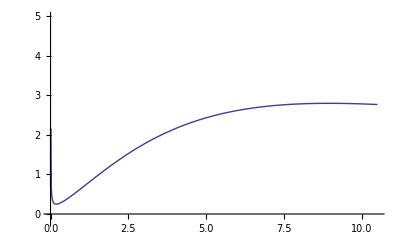

```mathematica
xm=0;
xM=10.5;
ym=-0.2;
yM=5.0;
gr3BPS=ListPlot[dataBPS,Joined-> True, PlotRange-> {{xm,xM},{ym,yM}}]
```

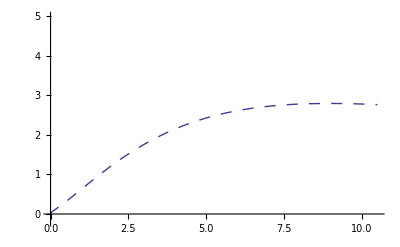

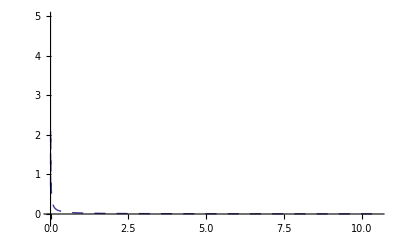

```mathematica
gr4E=ListPlot[dataBPSE,Joined->True,PlotStyle->Dashing[{0.02,0.02}],PlotRange->{{xm,xM},{ym,yM}}]
gr4I=ListPlot[dataBPSI,Joined->True,PlotStyle->Dashing[{0.02,0.02}],PlotRange->{{xm,xM},{ym,yM}}]
```

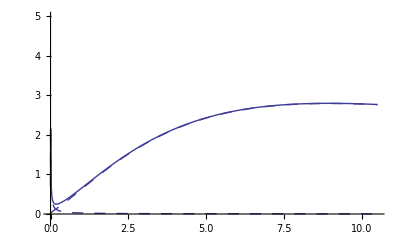

```mathematica
Show[gr3BPS,gr4E,gr4I,PlotRange-> {{xm,xM},{ym,yM}}]
```

#### E vs x and range R

```mathematica
dEdxEBPS=Interpolation[dataBPS];
```

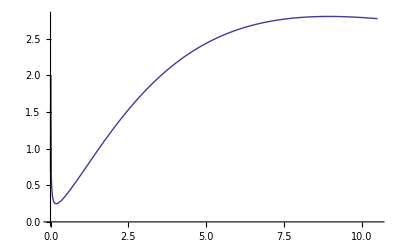

```mathematica
Plot[dEdxEBPS[e],{e,emin,emax}]
```

```mathematica
E0=emax;
dxEBPS[E_] :=1/dEdxEBPS[E]
xEBPS[E_]   := NIntegrate[1/dEdxEBPS[Ep],{Ep,E,E0},PrecisionGoal->Automatic]
```

```mathematica
FindRoot[dEdxEBPS[EE]==0,{EE,0.0.01}];
EzeroBPSa=EE /. %
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000547076} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

0.000778436

```mathematica
FindRoot[dEdxEBPS[EE]==0,{EE, EzeroBPSa}];
EzeroBPS=EE /. %
```

InterpolatingFunction::dmval: Input value {0.000778436} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.000778436

```mathematica
dEdxEBPS[EzeroBPS]
```

InterpolatingFunction::dmval: Input value {0.000778436} lies outside the range of data in the interpolating function. Extrapolation will be used.

-4.43692×10^-14

```mathematica
eth=2*T/1000
dEdxEBPS[eth]
xEBPS[eth]
```

0.001

0.68144

7.36057

```mathematica
NN=1000;
E1=eth;
dE=(E0-E1)/NN;
dataExBPS=Table[{xEBPS[E],E},{E,E1,emax,dE}];
```

```mathematica
xy1=dataExBPS[[2]]
xy2=dataExBPS[[1]]
dxy=xy2-xy1
m=dxy[[2]]/dxy[[1]]
b=xy1[[2]]-m*xy1[[1]]
xRBPS=-b/m
```

{7.35377,0.011499}

{7.36057,0.001}

{0.00679903,-0.010499}

-1.54419

11.3671

7.36122

```mathematica
dataExBPS=Prepend[dataExBPS,{xRBPS,0}]
```

{{7.36122,0},{7.36057,0.001},{7.35377,0.011499},{7.34174,0.021998},{7.32476,0.032497},{7.30346,0.042996},{7.2784,0.053495},{7.25009,0.063994},{7.21896,0.074493},{7.18543,0.084992},{7.14988,0.095491},{7.11263,0.10599},{7.07399,0.116489},{7.03423,0.126988},{6.9936,0.137487},{6.9523,0.147986},{6.91053,0.158485},{6.86844,0.168984},{6.82619,0.179483},{6.78389,0.189982},{6.74165,0.200481},{6.69956,0.21098},{6.65769,0.221479},{6.61612,0.231978},{6.57489,0.242477},{6.53405,0.252976},{6.49364,0.263475},{6.45369,0.273974},{6.41422,0.284473},{6.37526,0.294972},{6.33682,0.305471},{6.29891,0.31597},{6.26153,0.326469},{6.22469,0.336968},{6.18839,0.347467},{6.15262,0.357966},{6.11738,0.368465},{6.08267,0.378964},{6.04848,0.389463},{6.01482,0.399962},{5.98168,0.410461},{5.94905,0.42096},{5.91692,0.431459},{5.88529,0.441958},{5.85415,0.452457},{5.82349,0.462956},{5.7933,0.473455},{5.76357,0.483954},{5.73428,0.494453},{5.70544,0.504952},{5.67702,0.515451},{5.64903,0.52595},{5.62146,0.536449},{5.59429,0.546948},{5.56751,0.557447},{5.54113,0.567946},{5.51512,0.578445},{5.48948,0.588944},{5.4642,0.599443},{5.43928,0.609942},{5.4147,0.620441},{5.39046,0.63094},{5.36655,0.641439},{5.34297,0.651938},{5.31969,0.662437},{5.29673,0.672936},{5.27407,0.683435},{5.25171,0.693934},{5.22963,0.704433},{5.20784,0.714932},{5.18632,0.725431},{5.16507,0.73593},{5.14408,0.746429},{5.12336,0.756928},{5.10288,0.767427},{5.08265,0.777926},{5.06267,0.788425},{5.04292,0.798924},{5.0234,0.809423},{5.00411,0.819922},{4.98505,0.830421},{4.9662,0.84092},{4.94756,0.851419},{4.92913,0.861918},{4.9109,0.872417},{4.89288,0.882916},{4.87505,0.893415},{4.85741,0.903914},{4.83996,0.914413},{4.8227,0.924912},{4.80561,0.935411},{4.78871,0.94591},{4.77198,0.956409},{4.75541,0.966908},{4.73902,0.977407},{4.72279,0.987906},{4.70672,0.998405},{4.6908,1.0089},{4.67505,1.0194},{4.65944,1.0299},{4.64398,1.0404},{4.62867,1.0509},{4.61351,1.0614},{4.59848,1.0719},{4.58359,1.0824},{4.56884,1.0929},{4.55423,1.1034},{4.53974,1.11389},{4.52538,1.12439},{4.51115,1.13489},{4.49704,1.14539},{4.48306,1.15589},{4.4692,1.16639},{4.45545,1.17689},{4.44182,1.18739},{4.42831,1.19789},{4.4149,1.20839},{4.40161,1.21888},{4.38843,1.22938},{4.37535,1.23988},{4.36238,1.25038},{4.34951,1.26088},{4.33674,1.27138},{4.32407,1.28188},{4.3115,1.29238},{4.29903,1.30288},{4.28665,1.31338},{4.27437,1.32387},{4.26218,1.33437},{4.25008,1.34487},{4.23807,1.35537},{4.22614,1.36587},{4.21431,1.37637},{4.20256,1.38687},{4.19089,1.39737},{4.17931,1.40787},{4.16781,1.41837},{4.15639,1.42886},{4.14504,1.43936},{4.13378,1.44986},{4.12259,1.46036},{4.11148,1.47086},{4.10045,1.48136},{4.08949,1.49186},{4.0786,1.50236},{4.06778,1.51286},{4.05703,1.52336},{4.04635,1.53385},{4.03574,1.54435},{4.0252,1.55485},{4.01473,1.56535},{4.00432,1.57585},{3.99397,1.58635},{3.98369,1.59685},{3.97348,1.60735},{3.96332,1.61785},{3.95323,1.62835},{3.9432,1.63884},{3.93323,1.64934},{3.92331,1.65984},{3.91346,1.67034},{3.90366,1.68084},{3.89392,1.69134},{3.88423,1.70184},{3.87461,1.71234},{3.86503,1.72284},{3.85551,1.73334},{3.84604,1.74383},{3.83663,1.75433},{3.82727,1.76483},{3.81795,1.77533},{3.80869,1.78583},{3.79948,1.79633},{3.79032,1.80683},{3.78121,1.81733},{3.77214,1.82783},{3.76313,1.83833},{3.75416,1.84882},{3.74523,1.85932},{3.73636,1.86982},{3.72753,1.88032},{3.71874,1.89082},{3.71,1.90132},{3.7013,1.91182},{3.69264,1.92232},{3.68403,1.93282},{3.67546,1.94332},{3.66693,1.95381},{3.65844,1.96431},{3.64999,1.97481},{3.64159,1.98531},{3.63322,1.99581},{3.62489,2.00631},{3.61661,2.01681},{3.60836,2.02731},{3.60014,2.03781},{3.59197,2.04831},{3.58383,2.0588},{3.57574,2.0693},{3.56767,2.0798},{3.55965,2.0903},{3.55165,2.1008},{3.5437,2.1113},{3.53578,2.1218},{3.52789,2.1323},{3.52004,2.1428},{3.51222,2.1533},{3.50444,2.16379},{3.49668,2.17429},{3.48896,2.18479},{3.48128,2.19529},{3.47362,2.20579},{3.466,2.21629},{3.45841,2.22679},{3.45085,2.23729},{3.44332,2.24779},{3.43582,2.25829},{3.42835,2.26878},{3.42091,2.27928},{3.4135,2.28978},{3.40612,2.30028},{3.39877,2.31078},{3.39145,2.32128},{3.38415,2.33178},{3.37689,2.34228},{3.36965,2.35278},{3.36244,2.36328},{3.35525,2.37377},{3.34809,2.38427},{3.34096,2.39477},{3.33386,2.40527},{3.32678,2.41577},{3.31973,2.42627},{3.31271,2.43677},{3.30571,2.44727},{3.29873,2.45777},{3.29178,2.46827},{3.28485,2.47876},{3.27795,2.48926},{3.27108,2.49976},{3.26422,2.51026},{3.25739,2.52076},{3.25059,2.53126},{3.24381,2.54176},{3.23705,2.55226},{3.23031,2.56276},{3.2236,2.57326},{3.21691,2.58375},{3.21024,2.59425},{3.20359,2.60475},{3.19697,2.61525},{3.19036,2.62575},{3.18378,2.63625},{3.17722,2.64675},{3.17068,2.65725},{3.16417,2.66775},{3.15767,2.67825},{3.15119,2.68874},{3.14474,2.69924},{3.1383,2.70974},{3.13188,2.72024},{3.12549,2.73074},{3.11911,2.74124},{3.11275,2.75174},{3.10642,2.76224},{3.1001,2.77274},{3.0938,2.78324},{3.08752,2.79373},{3.08125,2.80423},{3.07501,2.81473},{3.06879,2.82523},{3.06258,2.83573},{3.05639,2.84623},{3.05022,2.85673},{3.04406,2.86723},{3.03793,2.87773},{3.03181,2.88823},{3.02571,2.89872},{3.01962,2.90922},{3.01356,2.91972},{3.00751,2.93022},{3.00147,2.94072},{2.99546,2.95122},{2.98945,2.96172},{2.98347,2.97222},{2.9775,2.98272},{2.97155,2.99322},{2.96561,3.00371},{2.95969,3.01421},{2.95379,3.02471},{2.9479,3.03521},{2.94202,3.04571},{2.93617,3.05621},{2.93032,3.06671},{2.92449,3.07721},{2.91868,3.08771},{2.91288,3.09821},{2.9071,3.1087},{2.90133,3.1192},{2.89557,3.1297},{2.88983,3.1402},{2.8841,3.1507},{2.87839,3.1612},{2.87269,3.1717},{2.86701,3.1822},{2.86134,3.1927},{2.85568,3.2032},{2.85003,3.21369},{2.8444,3.22419},{2.83879,3.23469},{2.83318,3.24519},{2.82759,3.25569},{2.82201,3.26619},{2.81645,3.27669},{2.8109,3.28719},{2.80536,3.29769},{2.79983,3.30819},{2.79432,3.31868},{2.78882,3.32918},{2.78333,3.33968},{2.77785,3.35018},{2.77238,3.36068},{2.76693,3.37118},{2.76149,3.38168},{2.75606,3.39218},{2.75064,3.40268},{2.74524,3.41318},{2.73985,3.42367},{2.73446,3.43417},{2.72909,3.44467},{2.72373,3.45517},{2.71838,3.46567},{2.71305,3.47617},{2.70772,3.48667},{2.70241,3.49717},{2.6971,3.50767},{2.69181,3.51817},{2.68653,3.52866},{2.68126,3.53916},{2.67599,3.54966},{2.67074,3.56016},{2.6655,3.57066},{2.66027,3.58116},{2.65506,3.59166},{2.64985,3.60216},{2.64465,3.61266},{2.63946,3.62316},{2.63428,3.63365},{2.62911,3.64415},{2.62395,3.65465},{2.6188,3.66515},{2.61367,3.67565},{2.60854,3.68615},{2.60342,3.69665},{2.59831,3.70715},{2.59321,3.71765},{2.58811,3.72815},{2.58303,3.73864},{2.57796,3.74914},{2.5729,3.75964},{2.56784,3.77014},{2.5628,3.78064},{2.55776,3.79114},{2.55273,3.80164},{2.54771,3.81214},{2.5427,3.82264},{2.5377,3.83314},{2.53271,3.84363},{2.52773,3.85413},{2.52275,3.86463},{2.51779,3.87513},{2.51283,3.88563},{2.50788,3.89613},{2.50294,3.90663},{2.49801,3.91713},{2.49308,3.92763},{2.48817,3.93813},{2.48326,3.94862},{2.47836,3.95912},{2.47347,3.96962},{2.46858,3.98012},{2.46371,3.99062},{2.45884,4.00112},{2.45398,4.01162},{2.44912,4.02212},{2.44428,4.03262},{2.43944,4.04312},{2.43461,4.05361},{2.42979,4.06411},{2.42498,4.07461},{2.42017,4.08511},{2.41537,4.09561},{2.41058,4.10611},{2.40579,4.11661},{2.40101,4.12711},{2.39624,4.13761},{2.39148,4.14811},{2.38672,4.1586},{2.38197,4.1691},{2.37723,4.1796},{2.3725,4.1901},{2.36777,4.2006},{2.36305,4.2111},{2.35833,4.2216},{2.35362,4.2321},{2.34892,4.2426},{2.34423,4.2531},{2.33954,4.26359},{2.33486,4.27409},{2.33018,4.28459},{2.32551,4.29509},{2.32085,4.30559},{2.3162,4.31609},{2.31155,4.32659},{2.30691,4.33709},{2.30227,4.34759},{2.29764,4.35809},{2.29302,4.36858},{2.2884,4.37908},{2.28379,4.38958},{2.27918,4.40008},{2.27458,4.41058},{2.26999,4.42108},{2.2654,4.43158},{2.26082,4.44208},{2.25625,4.45258},{2.25168,4.46308},{2.24711,4.47357},{2.24256,4.48407},{2.238,4.49457},{2.23346,4.50507},{2.22892,4.51557},{2.22438,4.52607},{2.21985,4.53657},{2.21533,4.54707},{2.21081,4.55757},{2.2063,4.56807},{2.20179,4.57856},{2.19729,4.58906},{2.19279,4.59956},{2.1883,4.61006},{2.18382,4.62056},{2.17934,4.63106},{2.17486,4.64156},{2.17039,4.65206},{2.16593,4.66256},{2.16147,4.67306},{2.15701,4.68355},{2.15257,4.69405},{2.14812,4.70455},{2.14368,4.71505},{2.13925,4.72555},{2.13482,4.73605},{2.1304,4.74655},{2.12598,4.75705},{2.12156,4.76755},{2.11715,4.77805},{2.11275,4.78854},{2.10835,4.79904},{2.10395,4.80954},{2.09956,4.82004},{2.09518,4.83054},{2.0908,4.84104},{2.08642,4.85154},{2.08205,4.86204},{2.07768,4.87254},{2.07332,4.88304},{2.06896,4.89353},{2.06461,4.90403},{2.06026,4.91453},{2.05592,4.92503},{2.05158,4.93553},{2.04724,4.94603},{2.04291,4.95653},{2.03858,4.96703},{2.03426,4.97753},{2.02994,4.98803},{2.02563,4.99852},{2.02132,5.00902},{2.01701,5.01952},{2.01271,5.03002},{2.00841,5.04052},{2.00412,5.05102},{1.99983,5.06152},{1.99555,5.07202},{1.99126,5.08252},{1.98699,5.09302},{1.98271,5.10351},{1.97845,5.11401},{1.97418,5.12451},{1.96992,5.13501},{1.96566,5.14551},{1.96141,5.15601},{1.95716,5.16651},{1.95291,5.17701},{1.94867,5.18751},{1.94443,5.19801},{1.9402,5.2085},{1.93597,5.219},{1.93174,5.2295},{1.92752,5.24},{1.9233,5.2505},{1.91908,5.261},{1.91487,5.2715},{1.91066,5.282},{1.90646,5.2925},{1.90226,5.303},{1.89806,5.31349},{1.89386,5.32399},{1.88967,5.33449},{1.88549,5.34499},{1.8813,5.35549},{1.87712,5.36599},{1.87294,5.37649},{1.86877,5.38699},{1.8646,5.39749},{1.86043,5.40799},{1.85627,5.41848},{1.85211,5.42898},{1.84795,5.43948},{1.8438,5.44998},{1.83965,5.46048},{1.8355,5.47098},{1.83135,5.48148},{1.82721,5.49198},{1.82307,5.50248},{1.81894,5.51298},{1.81481,5.52347},{1.81068,5.53397},{1.80655,5.54447},{1.80243,5.55497},{1.79831,5.56547},{1.79419,5.57597},{1.79008,5.58647},{1.78597,5.59697},{1.78186,5.60747},{1.77776,5.61797},{1.77366,5.62846},{1.76956,5.63896},{1.76546,5.64946},{1.76137,5.65996},{1.75728,5.67046},{1.75319,5.68096},{1.74911,5.69146},{1.74503,5.70196},{1.74095,5.71246},{1.73687,5.72296},{1.7328,5.73345},{1.72873,5.74395},{1.72466,5.75445},{1.72059,5.76495},{1.71653,5.77545},{1.71247,5.78595},{1.70841,5.79645},{1.70436,5.80695},{1.70031,5.81745},{1.69626,5.82795},{1.69221,5.83844},{1.68817,5.84894},{1.68413,5.85944},{1.68009,5.86994},{1.67605,5.88044},{1.67202,5.89094},{1.66798,5.90144},{1.66396,5.91194},{1.65993,5.92244},{1.6559,5.93294},{1.65188,5.94343},{1.64786,5.95393},{1.64385,5.96443},{1.63983,5.97493},{1.63582,5.98543},{1.63181,5.99593},{1.6278,6.00643},{1.6238,6.01693},{1.61979,6.02743},{1.61579,6.03793},{1.61179,6.04842},{1.6078,6.05892},{1.6038,6.06942},{1.59981,6.07992},{1.59582,6.09042},{1.59183,6.10092},{1.58785,6.11142},{1.58387,6.12192},{1.57989,6.13242},{1.57591,6.14292},{1.57193,6.15341},{1.56796,6.16391},{1.56398,6.17441},{1.56001,6.18491},{1.55604,6.19541},{1.55208,6.20591},{1.54811,6.21641},{1.54415,6.22691},{1.54019,6.23741},{1.53623,6.24791},{1.53228,6.2584},{1.52832,6.2689},{1.52437,6.2794},{1.52042,6.2899},{1.51647,6.3004},{1.51253,6.3109},{1.50858,6.3214},{1.50464,6.3319},{1.5007,6.3424},{1.49676,6.3529},{1.49282,6.36339},{1.48889,6.37389},{1.48496,6.38439},{1.48102,6.39489},{1.47709,6.40539},{1.47317,6.41589},{1.46924,6.42639},{1.46532,6.43689},{1.46139,6.44739},{1.45747,6.45789},{1.45355,6.46838},{1.44964,6.47888},{1.44572,6.48938},{1.44181,6.49988},{1.4379,6.51038},{1.43399,6.52088},{1.43008,6.53138},{1.42617,6.54188},{1.42226,6.55238},{1.41836,6.56288},{1.41446,6.57337},{1.41056,6.58387},{1.40666,6.59437},{1.40276,6.60487},{1.39887,6.61537},{1.39497,6.62587},{1.39108,6.63637},{1.38719,6.64687},{1.3833,6.65737},{1.37941,6.66787},{1.37552,6.67836},{1.37164,6.68886},{1.36775,6.69936},{1.36387,6.70986},{1.35999,6.72036},{1.35611,6.73086},{1.35223,6.74136},{1.34836,6.75186},{1.34448,6.76236},{1.34061,6.77286},{1.33674,6.78335},{1.33287,6.79385},{1.329,6.80435},{1.32513,6.81485},{1.32126,6.82535},{1.3174,6.83585},{1.31353,6.84635},{1.30967,6.85685},{1.30581,6.86735},{1.30195,6.87785},{1.29809,6.88834},{1.29424,6.89884},{1.29038,6.90934},{1.28652,6.91984},{1.28267,6.93034},{1.27882,6.94084},{1.27497,6.95134},{1.27112,6.96184},{1.26727,6.97234},{1.26342,6.98284},{1.25958,6.99333},{1.25573,7.00383},{1.25189,7.01433},{1.24805,7.02483},{1.2442,7.03533},{1.24036,7.04583},{1.23653,7.05633},{1.23269,7.06683},{1.22885,7.07733},{1.22502,7.08783},{1.22118,7.09832},{1.21735,7.10882},{1.21352,7.11932},{1.20968,7.12982},{1.20585,7.14032},{1.20203,7.15082},{1.1982,7.16132},{1.19437,7.17182},{1.19054,7.18232},{1.18672,7.19282},{1.1829,7.20331},{1.17907,7.21381},{1.17525,7.22431},{1.17143,7.23481},{1.16761,7.24531},{1.16379,7.25581},{1.15997,7.26631},{1.15616,7.27681},{1.15234,7.28731},{1.14853,7.29781},{1.14471,7.3083},{1.1409,7.3188},{1.13709,7.3293},{1.13328,7.3398},{1.12947,7.3503},{1.12566,7.3608},{1.12185,7.3713},{1.11804,7.3818},{1.11424,7.3923},{1.11043,7.4028},{1.10662,7.41329},{1.10282,7.42379},{1.09902,7.43429},{1.09521,7.44479},{1.09141,7.45529},{1.08761,7.46579},{1.08381,7.47629},{1.08001,7.48679},{1.07622,7.49729},{1.07242,7.50779},{1.06862,7.51828},{1.06483,7.52878},{1.06103,7.53928},{1.05724,7.54978},{1.05344,7.56028},{1.04965,7.57078},{1.04586,7.58128},{1.04207,7.59178},{1.03828,7.60228},{1.03449,7.61278},{1.0307,7.62327},{1.02691,7.63377},{1.02312,7.64427},{1.01933,7.65477},{1.01555,7.66527},{1.01176,7.67577},{1.00798,7.68627},{1.00419,7.69677},{1.00041,7.70727},{0.996625,7.71777},{0.992842,7.72826},{0.989061,7.73876},{0.985279,7.74926},{0.981499,7.75976},{0.977719,7.77026},{0.97394,7.78076},{0.970161,7.79126},{0.966383,7.80176},{0.962605,7.81226},{0.958829,7.82276},{0.955052,7.83325},{0.951276,7.84375},{0.947501,7.85425},{0.943727,7.86475},{0.939952,7.87525},{0.936179,7.88575},{0.932406,7.89625},{0.928633,7.90675},{0.924861,7.91725},{0.92109,7.92775},{0.917319,7.93824},{0.913549,7.94874},{0.909779,7.95924},{0.906009,7.96974},{0.90224,7.98024},{0.898472,7.99074},{0.894704,8.00124},{0.890936,8.01174},{0.887169,8.02224},{0.883403,8.03274},{0.879636,8.04323},{0.875871,8.05373},{0.872105,8.06423},{0.868341,8.07473},{0.864576,8.08523},{0.860812,8.09573},{0.857049,8.10623},{0.853285,8.11673},{0.849523,8.12723},{0.84576,8.13773},{0.841998,8.14822},{0.838237,8.15872},{0.834475,8.16922},{0.830715,8.17972},{0.826954,8.19022},{0.823194,8.20072},{0.819434,8.21122},{0.815675,8.22172},{0.811916,8.23222},{0.808157,8.24272},{0.804399,8.25321},{0.80064,8.26371},{0.796883,8.27421},{0.793125,8.28471},{0.789368,8.29521},{0.785611,8.30571},{0.781855,8.31621},{0.778099,8.32671},{0.774343,8.33721},{0.770587,8.34771},{0.766831,8.3582},{0.763076,8.3687},{0.759322,8.3792},{0.755567,8.3897},{0.751813,8.4002},{0.748059,8.4107},{0.744305,8.4212},{0.740551,8.4317},{0.736798,8.4422},{0.733045,8.4527},{0.729292,8.46319},{0.725539,8.47369},{0.721786,8.48419},{0.718034,8.49469},{0.714282,8.50519},{0.71053,8.51569},{0.706779,8.52619},{0.703027,8.53669},{0.699276,8.54719},{0.695525,8.55769},{0.691774,8.56818},{0.688023,8.57868},{0.684272,8.58918},{0.680522,8.59968},{0.676771,8.61018},{0.673021,8.62068},{0.669271,8.63118},{0.665521,8.64168},{0.661772,8.65218},{0.658022,8.66268},{0.654272,8.67317},{0.650523,8.68367},{0.646774,8.69417},{0.643025,8.70467},{0.639275,8.71517},{0.635526,8.72567},{0.631778,8.73617},{0.628029,8.74667},{0.62428,8.75717},{0.620532,8.76767},{0.616783,8.77816},{0.613034,8.78866},{0.609286,8.79916},{0.605538,8.80966},{0.601789,8.82016},{0.598041,8.83066},{0.594293,8.84116},{0.590545,8.85166},{0.586797,8.86216},{0.583049,8.87266},{0.579301,8.88315},{0.575553,8.89365},{0.571805,8.90415},{0.568057,8.91465},{0.564309,8.92515},{0.560561,8.93565},{0.556813,8.94615},{0.553065,8.95665},{0.549317,8.96715},{0.545569,8.97765},{0.541821,8.98814},{0.538073,8.99864},{0.534325,9.00914},{0.530577,9.01964},{0.526829,9.03014},{0.52308,9.04064},{0.519332,9.05114},{0.515584,9.06164},{0.511836,9.07214},{0.508087,9.08264},{0.504339,9.09313},{0.500591,9.10363},{0.496842,9.11413},{0.493094,9.12463},{0.489345,9.13513},{0.485596,9.14563},{0.481847,9.15613},{0.478098,9.16663},{0.474349,9.17713},{0.4706,9.18763},{0.466851,9.19812},{0.463102,9.20862},{0.459352,9.21912},{0.455603,9.22962},{0.451853,9.24012},{0.448104,9.25062},{0.444354,9.26112},{0.440604,9.27162},{0.436854,9.28212},{0.433103,9.29262},{0.429353,9.30311},{0.425602,9.31361},{0.421852,9.32411},{0.418101,9.33461},{0.41435,9.34511},{0.410599,9.35561},{0.406848,9.36611},{0.403096,9.37661},{0.399344,9.38711},{0.395593,9.39761},{0.391841,9.4081},{0.388088,9.4186},{0.384336,9.4291},{0.380584,9.4396},{0.376831,9.4501},{0.373078,9.4606},{0.369325,9.4711},{0.365571,9.4816},{0.361818,9.4921},{0.358064,9.5026},{0.35431,9.51309},{0.350556,9.52359},{0.346802,9.53409},{0.343047,9.54459},{0.339292,9.55509},{0.335537,9.56559},{0.331782,9.57609},{0.328026,9.58659},{0.32427,9.59709},{0.320514,9.60759},{0.316758,9.61808},{0.313001,9.62858},{0.309245,9.63908},{0.305488,9.64958},{0.30173,9.66008},{0.297973,9.67058},{0.294215,9.68108},{0.290457,9.69158},{0.286698,9.70208},{0.282939,9.71258},{0.27918,9.72307},{0.275421,9.73357},{0.271662,9.74407},{0.267902,9.75457},{0.264142,9.76507},{0.260381,9.77557},{0.25662,9.78607},{0.252859,9.79657},{0.249098,9.80707},{0.245336,9.81757},{0.241574,9.82806},{0.237812,9.83856},{0.234049,9.84906},{0.230286,9.85956},{0.226523,9.87006},{0.222759,9.88056},{0.218995,9.89106},{0.215231,9.90156},{0.211466,9.91206},{0.207701,9.92256},{0.203936,9.93305},{0.20017,9.94355},{0.196404,9.95405},{0.192637,9.96455},{0.188871,9.97505},{0.185103,9.98555},{0.181336,9.99605},{0.177568,10.0065},{0.1738,10.017},{0.170031,10.0275},{0.166262,10.038},{0.162492,10.0485},{0.158723,10.059},{0.154952,10.0695},{0.151182,10.08},{0.147411,10.0905},{0.143639,10.101},{0.139868,10.1115},{0.136095,10.122},{0.132323,10.1325},{0.12855,10.143},{0.124776,10.1535},{0.121002,10.164},{0.117228,10.1745},{0.113453,10.185},{0.109678,10.1955},{0.105903,10.206},{0.102127,10.2165},{0.0983501,10.227},{0.0945732,10.2375},{0.0907959,10.248},{0.0870181,10.2585},{0.0832399,10.269},{0.0794612,10.2795},{0.075682,10.29},{0.0719025,10.3005},{0.0681224,10.311},{0.0643419,10.3215},{0.0605609,10.332},{0.0567795,10.3425},{0.0529976,10.353},{0.0492152,10.3635},{0.0454324,10.374},{0.041649,10.3845},{0.0378652,10.395},{0.0340809,10.4055},{0.0302961,10.416},{0.0265109,10.4265},{0.0227251,10.437},{0.0189388,10.4475},{0.0151521,10.458},{0.0113648,10.4685},{0.00757705,10.479},{0.00378878,10.4895},{-6.41078×10^-16,10.5}}

```mathematica
ExBPS=Interpolation[dataExBPS];
```

```mathematica
ExBPS[xRBPS]
```

0.

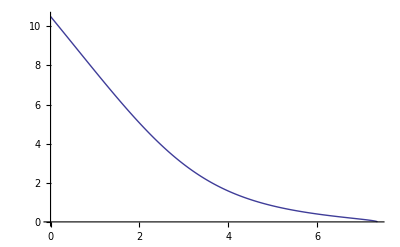

```mathematica
grExBPS=ListPlot[dataExBPS,Joined->True]
```

#### dE/dx vs E: dEdxEBPS

```mathematica
dEdxEeBPS =Interpolation[dataBPSE];
dEdxEiBPS =Interpolation[dataBPSI];
```

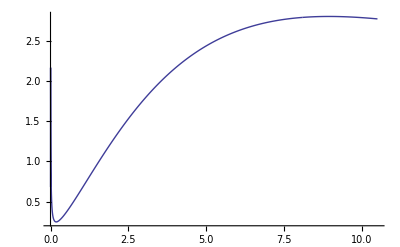

```mathematica
grdEdxEBPS=Plot[dEdxEBPS[e],{e,emin,emax},PlotPoints->10000,PlotRange->All]
```

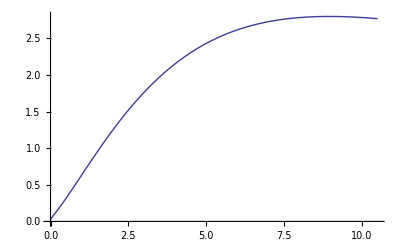

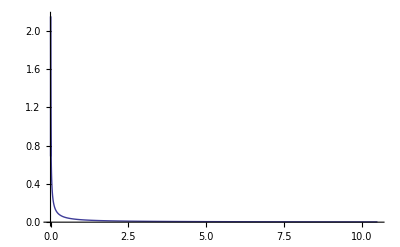

```mathematica
grdEdxEeBPS=Plot[dEdxEeBPS[e],{e,emin,emax},PlotPoints->1000,PlotRange->All]
grdEdxEiBPS=Plot[dEdxEiBPS[e],{e,emin,emax},PlotPoints->1000,PlotRange->All]
```

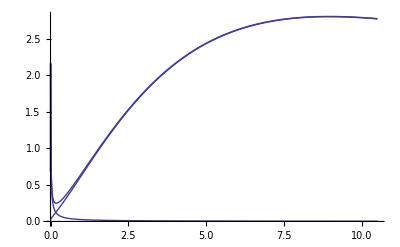

```mathematica
grdEdxEeiBPS=Show[grdEdxEeBPS,grdEdxEiBPS,grdEdxEBPS]
```

#### dE/dx vs x: dEdxx BPS

```mathematica
dEdxxBPS[x_] := dEdxEBPS[ExBPS[x]]
dEdxxeBPS[x_] := dEdxEeBPS[ExBPS[x]]
dEdxxiBPS[x_] := dEdxEiBPS[ExBPS[x]]
```

```mathematica
xRBPS
xRBPSmax=FindRoot[dEdxxBPS[x]==0,{x,xRBPS}][[1,2]]
```

7.36122

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000548875} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

7.36072

```mathematica
dEdxxBPS[xRBPS]
dEdxxBPS[xRBPSmax]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-4.32871

InterpolatingFunction::dmval: Input value {0.000778436} lies outside the range of data in the interpolating function. Extrapolation will be used.

-1.14895×10^-12

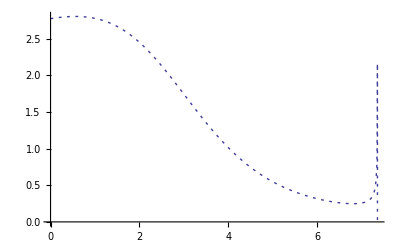

```mathematica
grdEdxxBPS=Plot[dEdxxBPS[x],{x,0,xRBPSmax},PlotStyle->Dashing[{0.005,0.01}],
PlotPoints->1000,PlotRange->All]
```

```mathematica
x0=3.5;
NIntegrate[dEdxxBPS[x],{x,0,x0},MaxRecursion->10]
NIntegrate[dEdxxBPS[x],{x,x0,xRBPSmax},MaxRecursion->10]
% + %%
```

8.3302

2.16905

10.4993

```mathematica
100*(%-E0)/E0
```

-0.00707939

partitioned among plasma components

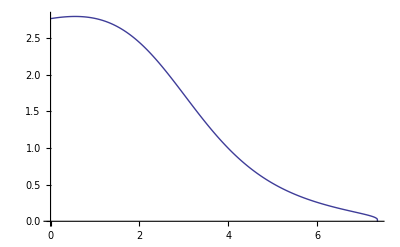

```mathematica
grdEdxxeBPS=Plot[dEdxxeBPS[x] ,{x,0,xRBPSmax},PlotPoints->1000,PlotPoints->All]
```

```mathematica
Ee=NIntegrate[dEdxxeBPS[x],{x,0,xRBPSmax}]
```

10.2087

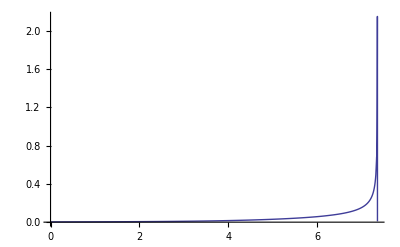

```mathematica
grdEdxxiBPS=Plot[dEdxxiBPS[x] ,{x,0,xRBPSmax},PlotPoints->1000,PlotRange->All]
```

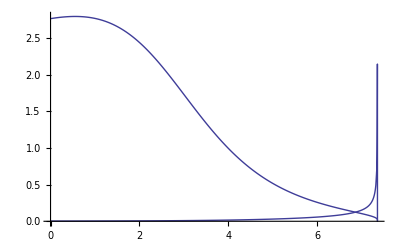

```mathematica
grdEdxxeiBPS=Show[grdEdxxeBPS,grdEdxxiBPS]
```

```mathematica
xRBPSmax
```

7.36072

```mathematica
x1=3.5;
NIntegrate[dEdxxiBPS[x],{x,0,x1},MaxRecursion->10]
NIntegrate[dEdxxiBPS[x],{x,x1,xRBPSmax},MaxRecursion->10]
Ei=% + %%
```

0.0201611

0.270347

0.290508

```mathematica
{Ee,Ei,Ee+Ei,E0}
```

{10.2087,0.290508,10.4993,10.5}

```mathematica
100*(E0-Ee-Ei)/E0
```

0.00710987

### LP cf BPS: Figs

```mathematica
id
```

B

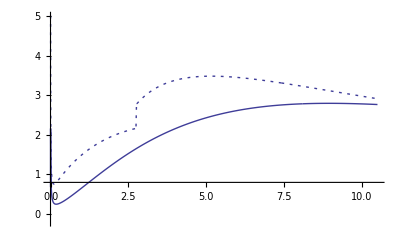

```mathematica
grdEdxELPBPS=Show[grdEdxELP,grdEdxEBPS,PlotRange->{ym,yM}]
```

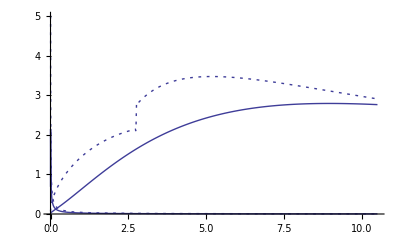

```mathematica
grdEdxEeiLPBPS=Show[grdEdxEeLP,grdEdxEiLP,
grdEdxEeBPS,grdEdxEiBPS,PlotRange->{ym,yM}]
```

```mathematica
NN=300;
Emin=emin;
Emax=0.2;
dE=(Emax-Emin)/NN;
data1=
Table[{EE,dEdxELP[EE],dEdxEeLP[EE],dEdxEiLP[EE],
dEdxEBPS[EE],dEdxEeBPS[EE],dEdxEiBPS[EE]},{EE,Emin,Emax,dE}];


NN=100;
Emin=Emax;
Emax=emax;
dE=(Emax-Emin)/NN;
data2=
Table[{EE,dEdxELP[EE],dEdxEeLP[EE],dEdxEiLP[EE],
dEdxEBPS[EE],dEdxEeBPS[EE],dEdxEiBPS[EE]},{EE,Emin,Emax,dE}];

data=Join[data1,data2]

(*
Export["LPvsBPS.dEdxE.aDT300127.dat",data,"Table",
ConversionOptions-> {"FormatType"-> FortranForm}];
*)
```

{{0.001,6.39592,0.0672231,6.32869,0.68144,-0.00628316,0.687723},{0.00166333,6.31285,0.074908,6.23794,1.78674,0.00425178,1.78249},{0.00232667,5.62268,0.0826043,5.54008,2.12208,0.0126801,2.1094},{0.00299,4.94278,0.0898672,4.85291,2.15805,0.017802,2.14025},{0.00365333,4.37794,0.0966819,4.28126,2.08437,0.0208942,2.06348},{0.00431667,3.92488,0.103096,3.82178,1.97511,0.0228869,1.95222},{0.00498,3.56113,0.109164,3.45197,1.85957,0.0242852,1.83528},{0.00564333,3.26548,0.114929,3.15055,1.74908,0.0253529,1.72373},{0.00630667,3.02143,0.120431,2.901,1.64751,0.0262293,1.62128},{0.00697,2.8169,0.125702,2.6912,1.55565,0.02699,1.52866},{0.00763333,2.64307,0.130767,2.5123,1.47304,0.0276777,1.44536},{0.00829667,2.49349,0.135649,2.35784,1.3988,0.028317,1.37048},{0.00896,2.36338,0.140365,2.22301,1.33196,0.0289229,1.30304},{0.00962333,2.24913,0.144932,2.1042,1.27161,0.0295046,1.2421},{0.0102867,2.14798,0.149362,1.99861,1.2169,0.0300681,1.18683},{0.01095,2.05777,0.153667,1.9041,1.16713,0.0306175,1.13652},{0.0116133,1.9768,0.157857,1.81894,1.12169,0.0311555,1.09053},{0.0122767,1.90371,0.161941,1.74177,1.08004,0.031684,1.04835},{0.01294,1.83741,0.165926,1.67148,1.04173,0.0322045,1.00953},{0.0136033,1.77698,0.16982,1.60716,1.00639,0.0327181,0.973668},{0.0142667,1.72168,0.173628,1.54805,0.973676,0.0332255,0.940451},{0.01493,1.67088,0.177355,1.49352,0.943316,0.0337273,0.909589},{0.0155933,1.62406,0.181008,1.44305,0.915062,0.0342241,0.880837},{0.0162567,1.58077,0.18459,1.39618,0.888701,0.0347164,0.853984},{0.01692,1.54063,0.188105,1.35252,0.864049,0.0352043,0.828844},{0.0175833,1.50331,0.191556,1.31176,0.840944,0.0356882,0.805256},{0.0182467,1.46854,0.194948,1.27359,0.819244,0.0361684,0.783076},{0.01891,1.43606,0.198283,1.23777,0.798825,0.0366451,0.76218},{0.0195733,1.40565,0.201564,1.20409,0.779575,0.0371184,0.742457},{0.0202367,1.37714,0.204793,1.17235,0.761397,0.0375886,0.723809},{0.0209,1.35036,0.207973,1.14238,0.744203,0.0380556,0.706148},{0.0215633,1.32515,0.211107,1.11404,0.727915,0.0385198,0.689395},{0.0222267,1.30138,0.214196,1.08719,0.712463,0.0389813,0.673482},{0.02289,1.27895,0.217241,1.06171,0.697784,0.03944,0.658344},{0.0235533,1.25774,0.220246,1.0375,0.683821,0.0398962,0.643925},{0.0242167,1.23767,0.223211,1.01446,0.670523,0.0403499,0.630173},{0.02488,1.21864,0.226138,0.992505,0.657844,0.0408012,0.617043},{0.0255433,1.20059,0.229029,0.971561,0.645741,0.0412503,0.604491},{0.0262067,1.18344,0.231885,0.951555,0.634176,0.0416971,0.592479},{0.02687,1.16713,0.234706,0.932424,0.623114,0.0421418,0.580973},{0.0275333,1.1516,0.237495,0.91411,0.612524,0.0425844,0.569939},{0.0281967,1.13681,0.240253,0.89656,0.602374,0.0430251,0.559349},{0.02886,1.12271,0.24298,0.879726,0.59264,0.0434638,0.549176},{0.0295233,1.10924,0.245677,0.863563,0.583296,0.0439006,0.539395},{0.0301867,1.09638,0.248346,0.848032,0.574318,0.0443356,0.529983},{0.03085,1.08408,0.250988,0.833094,0.565688,0.0447688,0.520919},{0.0315133,1.07232,0.253602,0.818715,0.557384,0.0452003,0.512183},{0.0321767,1.06105,0.256191,0.804864,0.549388,0.0456302,0.503757},{0.03284,1.05027,0.258755,0.79151,0.541682,0.0460585,0.495623},{0.0335033,1.03992,0.261294,0.778628,0.534254,0.0464852,0.487769},{0.0341667,1.03,0.26381,0.766191,0.527091,0.0469103,0.480181},{0.03483,1.02048,0.266302,0.754176,0.520175,0.047334,0.472841},{0.0354933,1.01133,0.268772,0.742562,0.513494,0.0477563,0.465738},{0.0361567,1.00255,0.271221,0.731328,0.50704,0.0481772,0.458863},{0.03682,0.994103,0.273648,0.720455,0.5008,0.0485967,0.452203},{0.0374833,0.98598,0.276054,0.709926,0.494761,0.0490149,0.445746},{0.0381467,0.978164,0.278441,0.699724,0.488917,0.0494318,0.439485},{0.03881,0.97064,0.280807,0.689833,0.48326,0.0498475,0.433412},{0.0394733,0.963395,0.283155,0.68024,0.477777,0.050262,0.427515},{0.0401367,0.956414,0.285484,0.67093,0.472463,0.0506752,0.421788},{0.0408,0.949685,0.287795,0.66189,0.467312,0.0510874,0.416225},{0.0414633,0.943198,0.290088,0.65311,0.462314,0.0514984,0.410816},{0.0421267,0.936941,0.292364,0.644577,0.457464,0.0519083,0.405556},{0.04279,0.930903,0.294622,0.636281,0.452756,0.0523171,0.400439},{0.0434533,0.925076,0.296865,0.628212,0.448184,0.0527249,0.395459},{0.0441167,0.919451,0.299091,0.62036,0.443741,0.0531317,0.390609},{0.04478,0.914018,0.301301,0.612717,0.439423,0.0535375,0.385886},{0.0454433,0.908769,0.303495,0.605274,0.435226,0.0539423,0.381284},{0.0461067,0.903698,0.305675,0.598023,0.431143,0.0543462,0.376797},{0.04677,0.898796,0.30784,0.590956,0.427171,0.0547492,0.372422},{0.0474333,0.894057,0.30999,0.584067,0.423307,0.0551513,0.368155},{0.0480967,0.889474,0.312126,0.577349,0.419544,0.0555526,0.363991},{0.04876,0.885042,0.314248,0.570794,0.41588,0.0559529,0.359927},{0.0494233,0.880754,0.316356,0.564398,0.412312,0.0563525,0.355959},{0.0500867,0.876605,0.318451,0.558154,0.408835,0.0567512,0.352084},{0.05075,0.872589,0.320533,0.552056,0.405447,0.0571492,0.348297},{0.0514133,0.868702,0.322602,0.5461,0.402144,0.0575464,0.344597},{0.0520767,0.864939,0.324658,0.540281,0.398923,0.0579428,0.34098},{0.05274,0.861295,0.326702,0.534593,0.395782,0.0583385,0.337443},{0.0534033,0.857766,0.328734,0.529032,0.392717,0.0587335,0.333984},{0.0540667,0.854348,0.330754,0.523594,0.389728,0.0591278,0.3306},{0.05473,0.851037,0.332762,0.518275,0.386809,0.0595214,0.327288},{0.0553933,0.847829,0.334759,0.513071,0.38396,0.0599143,0.324046},{0.0560567,0.844721,0.336744,0.507977,0.381179,0.0603066,0.320872},{0.05672,0.841709,0.338718,0.502991,0.378462,0.0606983,0.317764},{0.0573833,0.83879,0.340682,0.498108,0.375809,0.0610893,0.314719},{0.0580467,0.835961,0.342634,0.493327,0.373216,0.0614797,0.311736},{0.05871,0.833218,0.344576,0.488642,0.370683,0.0618695,0.308813},{0.0593733,0.83056,0.346508,0.484052,0.368206,0.0622588,0.305947},{0.0600367,0.827983,0.348429,0.479554,0.365785,0.0626475,0.303138},{0.0607,0.825484,0.350341,0.475144,0.363419,0.0630356,0.300383},{0.0613633,0.823062,0.352242,0.47082,0.361104,0.0634232,0.297681},{0.0620267,0.820714,0.354134,0.46658,0.358841,0.0638102,0.29503},{0.06269,0.818437,0.356016,0.462421,0.356626,0.0641968,0.292429},{0.0633533,0.816229,0.357889,0.45834,0.35446,0.0645828,0.289877},{0.0640167,0.814088,0.359752,0.454336,0.35234,0.0649684,0.287371},{0.06468,0.812012,0.361607,0.450406,0.350265,0.0653534,0.284911},{0.0653433,0.81,0.363452,0.446548,0.348234,0.065738,0.282496},{0.0660067,0.808049,0.365289,0.44276,0.346246,0.0661222,0.280123},{0.06667,0.806157,0.367117,0.43904,0.344299,0.0665058,0.277793},{0.0673333,0.804322,0.368936,0.435386,0.342393,0.0668891,0.275504},{0.0679967,0.802544,0.370747,0.431797,0.340526,0.0672719,0.273254},{0.06866,0.80082,0.372549,0.428271,0.338697,0.0676543,0.271043},{0.0693233,0.799149,0.374344,0.424806,0.336906,0.0680363,0.26887},{0.0699867,0.79753,0.37613,0.4214,0.335151,0.0684178,0.266733},{0.07065,0.79596,0.377908,0.418052,0.333431,0.068799,0.264632},{0.0713133,0.794439,0.379678,0.41476,0.331746,0.0691798,0.262566},{0.0719767,0.792964,0.381441,0.411524,0.330095,0.0695602,0.260534},{0.07264,0.791536,0.383195,0.408341,0.328476,0.0699403,0.258535},{0.0733033,0.790152,0.384943,0.40521,0.326889,0.07032,0.256569},{0.0739667,0.788812,0.386682,0.40213,0.325333,0.0706994,0.254634},{0.07463,0.787514,0.388415,0.399099,0.323808,0.0710784,0.252729},{0.0752933,0.786257,0.39014,0.396117,0.322312,0.071457,0.250855},{0.0759567,0.78504,0.391858,0.393182,0.320845,0.0718354,0.24901},{0.07662,0.783862,0.393569,0.390293,0.319406,0.0722134,0.247193},{0.0772833,0.782722,0.395273,0.387449,0.317995,0.0725911,0.245404},{0.0779467,0.78162,0.39697,0.384649,0.316611,0.0729685,0.243643},{0.07861,0.780553,0.39866,0.381892,0.315254,0.0733456,0.241908},{0.0792733,0.779521,0.400344,0.379177,0.313921,0.0737224,0.240199},{0.0799367,0.778523,0.402021,0.376503,0.312614,0.074099,0.238516},{0.0806,0.777559,0.403691,0.373868,0.311332,0.0744752,0.236857},{0.0812633,0.776628,0.405355,0.371273,0.310074,0.0748512,0.235222},{0.0819267,0.775728,0.407012,0.368716,0.308838,0.0752269,0.233612},{0.08259,0.774859,0.408664,0.366196,0.307626,0.0756024,0.232024},{0.0832533,0.774021,0.410308,0.363712,0.306437,0.0759775,0.230459},{0.0839167,0.773211,0.411947,0.361264,0.305269,0.0763525,0.228916},{0.08458,0.772431,0.41358,0.358851,0.304123,0.0767272,0.227395},{0.0852433,0.771679,0.415206,0.356472,0.302997,0.0771017,0.225896},{0.0859067,0.770954,0.416827,0.354127,0.301892,0.0774759,0.224417},{0.08657,0.770256,0.418442,0.351814,0.300808,0.0778499,0.222958},{0.0872333,0.769584,0.420051,0.349533,0.299743,0.0782237,0.221519},{0.0878967,0.768937,0.421654,0.347284,0.298697,0.0785973,0.2201},{0.08856,0.768316,0.423251,0.345065,0.29767,0.0789707,0.2187},{0.0892233,0.767719,0.424843,0.342876,0.296662,0.0793438,0.217318},{0.0898867,0.767146,0.426429,0.340716,0.295672,0.0797168,0.215955},{0.09055,0.766595,0.42801,0.338585,0.294699,0.0800895,0.21461},{0.0912133,0.766068,0.429585,0.336483,0.293744,0.0804621,0.213282},{0.0918767,0.765563,0.431155,0.334408,0.292806,0.0808345,0.211972},{0.09254,0.76508,0.43272,0.33236,0.291885,0.0812067,0.210678},{0.0932033,0.764618,0.434279,0.330338,0.29098,0.0815787,0.209401},{0.0938667,0.764176,0.435833,0.328343,0.290091,0.0819506,0.208141},{0.09453,0.763756,0.437382,0.326373,0.289218,0.0823223,0.206896},{0.0951933,0.763354,0.438926,0.324428,0.288361,0.0826938,0.205667},{0.0958567,0.762973,0.440465,0.322508,0.287518,0.0830651,0.204453},{0.09652,0.76261,0.441999,0.320611,0.28669,0.0834363,0.203254},{0.0971833,0.762266,0.443528,0.318739,0.285877,0.0838074,0.20207},{0.0978467,0.761941,0.445052,0.316889,0.285079,0.0841783,0.2009},{0.09851,0.761633,0.446571,0.315062,0.284294,0.084549,0.199745},{0.0991733,0.761342,0.448085,0.313257,0.283523,0.0849197,0.198603},{0.0998367,0.761069,0.449595,0.311474,0.282766,0.0852901,0.197476},{0.1005,0.760812,0.451099,0.309713,0.282022,0.0856605,0.196361},{0.101163,0.760572,0.4526,0.307973,0.281291,0.0860307,0.19526},{0.101827,0.760348,0.454095,0.306253,0.280573,0.0864008,0.194172},{0.10249,0.76014,0.455586,0.304554,0.279867,0.0867708,0.193096},{0.103153,0.759947,0.457072,0.302874,0.279174,0.0871406,0.192033},{0.103817,0.759769,0.458554,0.301214,0.278493,0.0875103,0.190982},{0.10448,0.759605,0.460032,0.299573,0.277823,0.08788,0.189943},{0.105143,0.759457,0.461505,0.297952,0.277166,0.0882495,0.188916},{0.105807,0.759322,0.462974,0.296348,0.27652,0.0886189,0.187901},{0.10647,0.759202,0.464438,0.294763,0.275885,0.0889882,0.186897},{0.107133,0.759095,0.465898,0.293196,0.275262,0.0893574,0.185905},{0.107797,0.759001,0.467354,0.291647,0.274649,0.0897265,0.184923},{0.10846,0.758921,0.468806,0.290115,0.274048,0.0900955,0.183952},{0.109123,0.758853,0.470254,0.288599,0.273456,0.0904644,0.182992},{0.109787,0.758798,0.471697,0.287101,0.272876,0.0908332,0.182042},{0.11045,0.758755,0.473136,0.285619,0.272305,0.0912019,0.181103},{0.111113,0.758725,0.474572,0.284153,0.271745,0.0915706,0.180174},{0.111777,0.758706,0.476003,0.282703,0.271194,0.0919392,0.179255},{0.11244,0.758699,0.47743,0.281268,0.270653,0.0923076,0.178345},{0.113103,0.758703,0.478854,0.279849,0.270122,0.0926761,0.177446},{0.113767,0.758719,0.480273,0.278445,0.2696,0.0930444,0.176555},{0.11443,0.758745,0.481689,0.277056,0.269087,0.0934127,0.175675},{0.115093,0.758782,0.4831,0.275682,0.268584,0.0937809,0.174803},{0.115757,0.75883,0.484508,0.274322,0.268089,0.094149,0.17394},{0.11642,0.758889,0.485913,0.272976,0.267604,0.0945171,0.173086},{0.117083,0.758957,0.487313,0.271644,0.267127,0.0948851,0.172242},{0.117747,0.759036,0.48871,0.270326,0.266658,0.0952531,0.171405},{0.11841,0.759124,0.490103,0.269021,0.266198,0.095621,0.170577},{0.119073,0.759222,0.491492,0.26773,0.265747,0.0959888,0.169758},{0.119737,0.759329,0.492878,0.266451,0.265303,0.0963566,0.168947},{0.1204,0.759446,0.49426,0.265186,0.264868,0.0967244,0.168143},{0.121063,0.759572,0.495638,0.263933,0.26444,0.0970921,0.167348},{0.121727,0.759706,0.497014,0.262693,0.264021,0.0974597,0.166561},{0.12239,0.75985,0.498385,0.261465,0.263609,0.0978274,0.165781},{0.123053,0.760002,0.499753,0.260249,0.263204,0.0981949,0.165009},{0.123717,0.760163,0.501118,0.259045,0.262807,0.0985625,0.164245},{0.12438,0.760332,0.502479,0.257853,0.262418,0.0989299,0.163488},{0.125043,0.760509,0.503837,0.256672,0.262035,0.0992974,0.162738},{0.125707,0.760694,0.505191,0.255503,0.26166,0.0996648,0.161995},{0.12637,0.760887,0.506542,0.254345,0.261292,0.100032,0.16126},{0.127033,0.761088,0.50789,0.253198,0.260931,0.1004,0.160531},{0.127697,0.761297,0.509235,0.252062,0.260577,0.100767,0.15981},{0.12836,0.761513,0.510576,0.250937,0.260229,0.101134,0.159095},{0.129023,0.761736,0.511914,0.249822,0.259888,0.101502,0.158387},{0.129687,0.761967,0.513249,0.248718,0.259554,0.101869,0.157685},{0.13035,0.762204,0.51458,0.247624,0.259226,0.102236,0.15699},{0.131013,0.762449,0.515909,0.24654,0.258904,0.102603,0.156301},{0.131677,0.7627,0.517234,0.245466,0.258589,0.10297,0.155619},{0.13234,0.762959,0.518556,0.244403,0.25828,0.103338,0.154943},{0.133003,0.763223,0.519875,0.243348,0.257977,0.103705,0.154273},{0.133667,0.763495,0.521191,0.242304,0.257681,0.104072,0.153609},{0.13433,0.763773,0.522504,0.241269,0.25739,0.104439,0.152951},{0.134993,0.764057,0.523814,0.240243,0.257105,0.104806,0.152298},{0.135657,0.764347,0.525121,0.239226,0.256825,0.105173,0.151652},{0.13632,0.764643,0.526425,0.238218,0.256552,0.105541,0.151011},{0.136983,0.764946,0.527726,0.23722,0.256284,0.105908,0.150376},{0.137647,0.765254,0.529024,0.23623,0.256022,0.106275,0.149747},{0.13831,0.765568,0.530319,0.235249,0.255765,0.106642,0.149123},{0.138973,0.765887,0.531611,0.234276,0.255513,0.107009,0.148505},{0.139637,0.766213,0.5329,0.233312,0.255267,0.107376,0.147891},{0.1403,0.766543,0.534187,0.232357,0.255027,0.107743,0.147284},{0.140963,0.76688,0.53547,0.231409,0.254791,0.10811,0.146681},{0.141627,0.767221,0.536751,0.23047,0.254561,0.108477,0.146083},{0.14229,0.767568,0.538029,0.229539,0.254335,0.108845,0.145491},{0.142953,0.76792,0.539305,0.228615,0.254115,0.109212,0.144904},{0.143617,0.768277,0.540577,0.2277,0.2539,0.109579,0.144321},{0.14428,0.768639,0.541847,0.226792,0.253689,0.109946,0.143743},{0.144943,0.769006,0.543114,0.225892,0.253484,0.110313,0.143171},{0.145607,0.769377,0.544378,0.224999,0.253283,0.11068,0.142603},{0.14627,0.769754,0.54564,0.224114,0.253087,0.111048,0.142039},{0.146933,0.770135,0.546899,0.223236,0.252895,0.111415,0.141481},{0.147597,0.77052,0.548155,0.222365,0.252709,0.111782,0.140927},{0.14826,0.770911,0.549409,0.221502,0.252526,0.112149,0.140377},{0.148923,0.771305,0.55066,0.220645,0.252348,0.112516,0.139832},{0.149587,0.771704,0.551908,0.219796,0.252175,0.112884,0.139291},{0.15025,0.772107,0.553154,0.218953,0.252006,0.113251,0.138755},{0.150913,0.772515,0.554397,0.218118,0.251841,0.113618,0.138223},{0.151577,0.772927,0.555638,0.217289,0.251681,0.113986,0.137695},{0.15224,0.773343,0.556876,0.216466,0.251524,0.114353,0.137172},{0.152903,0.773762,0.558112,0.21565,0.251372,0.11472,0.136652},{0.153567,0.774186,0.559345,0.214841,0.251224,0.115088,0.136137},{0.15423,0.774614,0.560576,0.214038,0.251081,0.115455,0.135625},{0.154893,0.775046,0.561804,0.213241,0.250941,0.115823,0.135118},{0.155557,0.775481,0.56303,0.212451,0.250805,0.11619,0.134615},{0.15622,0.77592,0.564253,0.211667,0.250673,0.116558,0.134115},{0.156883,0.776363,0.565474,0.210889,0.250545,0.116925,0.13362},{0.157547,0.776809,0.566693,0.210116,0.250421,0.117293,0.133128},{0.15821,0.777259,0.567909,0.20935,0.2503,0.11766,0.13264},{0.158873,0.777713,0.569123,0.20859,0.250184,0.118028,0.132156},{0.159537,0.77817,0.570334,0.207835,0.250071,0.118396,0.131675},{0.1602,0.77863,0.571543,0.207087,0.249962,0.118763,0.131198},{0.160863,0.779094,0.57275,0.206344,0.249856,0.119131,0.130725},{0.161527,0.779561,0.573955,0.205606,0.249754,0.119499,0.130255},{0.16219,0.780031,0.575157,0.204874,0.249656,0.119867,0.129789},{0.162853,0.780504,0.576357,0.204148,0.249561,0.120234,0.129326},{0.163517,0.780981,0.577554,0.203427,0.249469,0.120602,0.128867},{0.16418,0.781461,0.578749,0.202711,0.249381,0.12097,0.128411},{0.164843,0.781943,0.579942,0.202001,0.249297,0.121338,0.127958},{0.165507,0.782429,0.581133,0.201296,0.249215,0.121706,0.127509},{0.16617,0.782918,0.582322,0.200596,0.249137,0.122074,0.127063},{0.166833,0.783409,0.583508,0.199901,0.249063,0.122442,0.12662},{0.167497,0.783904,0.584692,0.199211,0.248991,0.12281,0.126181},{0.16816,0.784401,0.585874,0.198526,0.248923,0.123179,0.125745},{0.168823,0.784901,0.587054,0.197847,0.248858,0.123547,0.125311},{0.169487,0.785404,0.588232,0.197172,0.248796,0.123915,0.124881},{0.17015,0.785909,0.589407,0.196502,0.248738,0.124283,0.124454},{0.170813,0.786417,0.590581,0.195836,0.248682,0.124652,0.12403},{0.171477,0.786928,0.591752,0.195176,0.248629,0.12502,0.123609},{0.17214,0.787441,0.592921,0.19452,0.24858,0.125389,0.123191},{0.172803,0.787957,0.594088,0.193869,0.248533,0.125757,0.122776},{0.173467,0.788475,0.595253,0.193222,0.24849,0.126126,0.122364},{0.17413,0.788996,0.596416,0.19258,0.248449,0.126494,0.121955},{0.174793,0.789519,0.597577,0.191942,0.248411,0.126863,0.121548},{0.175457,0.790045,0.598736,0.191309,0.248376,0.127232,0.121145},{0.17612,0.790573,0.599893,0.19068,0.248344,0.1276,0.120744},{0.176783,0.791103,0.601047,0.190056,0.248315,0.127969,0.120346},{0.177447,0.791636,0.6022,0.189436,0.248288,0.128338,0.11995},{0.17811,0.792171,0.603351,0.18882,0.248265,0.128707,0.119558},{0.178773,0.792708,0.604499,0.188208,0.248244,0.129076,0.119168},{0.179437,0.793247,0.605646,0.187601,0.248225,0.129445,0.11878},{0.1801,0.793788,0.606791,0.186997,0.24821,0.129814,0.118396},{0.180763,0.794332,0.607934,0.186398,0.248197,0.130183,0.118014},{0.181427,0.794877,0.609074,0.185803,0.248186,0.130552,0.117634},{0.18209,0.795425,0.610213,0.185212,0.248178,0.130921,0.117257},{0.182753,0.795975,0.61135,0.184624,0.248173,0.131291,0.116883},{0.183417,0.796526,0.612485,0.184041,0.248171,0.13166,0.116511},{0.18408,0.79708,0.613618,0.183461,0.24817,0.132029,0.116141},{0.184743,0.797635,0.61475,0.182886,0.248173,0.132399,0.115774},{0.185407,0.798193,0.615879,0.182314,0.248178,0.132768,0.115409},{0.18607,0.798752,0.617006,0.181746,0.248185,0.133138,0.115047},{0.186733,0.799313,0.618132,0.181181,0.248195,0.133508,0.114687},{0.187397,0.799876,0.619256,0.180621,0.248207,0.133877,0.114329},{0.18806,0.800441,0.620378,0.180064,0.248221,0.134247,0.113974},{0.188723,0.801008,0.621498,0.17951,0.248238,0.134617,0.113621},{0.189387,0.801576,0.622616,0.17896,0.248257,0.134987,0.11327},{0.19005,0.802146,0.623732,0.178414,0.248279,0.135357,0.112922},{0.190713,0.802718,0.624847,0.177871,0.248302,0.135727,0.112576},{0.191377,0.803291,0.625959,0.177332,0.248329,0.136097,0.112232},{0.19204,0.803866,0.62707,0.176796,0.248357,0.136467,0.11189},{0.192703,0.804443,0.628179,0.176263,0.248387,0.136837,0.11155},{0.193367,0.805021,0.629287,0.175734,0.24842,0.137207,0.111213},{0.19403,0.805601,0.630392,0.175208,0.248455,0.137578,0.110877},{0.194693,0.806182,0.631496,0.174686,0.248492,0.137948,0.110544},{0.195357,0.806765,0.632598,0.174166,0.248531,0.138319,0.110213},{0.19602,0.807349,0.633699,0.17365,0.248573,0.138689,0.109884},{0.196683,0.807935,0.634797,0.173138,0.248616,0.13906,0.109557},{0.197347,0.808522,0.635894,0.172628,0.248662,0.13943,0.109231},{0.19801,0.809111,0.636989,0.172121,0.248709,0.139801,0.108908},{0.198673,0.809701,0.638083,0.171618,0.248759,0.140172,0.108587},{0.199337,0.810293,0.639175,0.171118,0.248811,0.140543,0.108268},{0.2,0.810885,0.640265,0.170621,0.248864,0.140914,0.107951},{0.2,0.810885,0.640265,0.170621,0.248864,0.140914,0.107951},{0.303,0.911268,0.792952,0.118315,0.274104,0.199459,0.0746457},{0.406,1.01357,0.922383,0.0911914,0.317153,0.259999,0.0571546},{0.509,1.1109,1.03642,0.0744751,0.368889,0.322292,0.0465973},{0.612,1.20209,1.13899,0.063095,0.425372,0.385979,0.0393933},{0.715,1.28723,1.2324,0.0548264,0.484852,0.45069,0.0341614},{0.818,1.36667,1.31814,0.0485354,0.546279,0.516093,0.0301858},{0.921,1.44082,1.39724,0.0435816,0.608951,0.581891,0.0270598},{1.024,1.51005,1.47048,0.0395757,0.672364,0.647829,0.0245356},{1.127,1.57471,1.53845,0.0362666,0.736134,0.713681,0.0224534},{1.23,1.63512,1.60163,0.0334852,0.799961,0.779255,0.0207056},{1.333,1.69154,1.66043,0.0311134,0.8636,0.844383,0.0192171},{1.436,1.74423,1.71516,0.029066,0.926853,0.908919,0.0179336},{1.539,1.79341,1.76613,0.02728,0.989553,0.972738,0.0168151},{1.642,1.83929,1.81359,0.0257077,1.05156,1.03573,0.0158316},{1.745,1.88206,1.85775,0.0243127,1.11277,1.09781,0.0149598},{1.848,1.9219,1.89883,0.0230661,1.17307,1.15889,0.0141814},{1.951,1.95896,1.93702,0.0219453,1.23238,1.2189,0.0134822},{2.054,1.9934,1.97247,0.0209319,1.29064,1.27779,0.0128505},{2.157,2.02536,2.00535,0.0200111,1.34778,1.33551,0.012277},{2.26,2.05496,2.03579,0.0191705,1.40377,1.39201,0.0117538},{2.363,2.08234,2.06394,0.0184,1.45855,1.44728,0.0112745},{2.466,2.10761,2.08992,0.017691,1.51211,1.50127,0.0108339},{2.569,2.13089,2.11385,0.0170365,1.5644,1.55398,0.0104273},{2.672,2.15226,2.13583,0.0164303,1.61543,1.60538,0.010051},{2.775,2.81243,2.79657,0.0158671,1.66517,1.65546,0.00970156},{2.878,2.87905,2.86371,0.0153426,1.71361,1.70423,0.0093763},{2.981,2.95633,2.94148,0.0148527,1.76075,1.75167,0.00907273},{3.084,3.02522,3.01082,0.0143943,1.80658,1.79779,0.00878873},{3.187,3.08663,3.07267,0.0139642,1.85112,1.84259,0.00852246},{3.29,3.14136,3.1278,0.0135599,1.89436,1.88608,0.00827228},{3.393,3.19011,3.17693,0.0131791,1.93631,1.92827,0.00803677},{3.496,3.23347,3.22065,0.0128199,1.97698,1.96917,0.00781467},{3.599,3.27197,3.25949,0.0124804,2.01639,2.00878,0.00760484},{3.702,3.30607,3.29391,0.012159,2.05454,2.04713,0.00740629},{3.805,3.33619,3.32434,0.0118542,2.09145,2.08423,0.00721813},{3.908,3.3627,3.35113,0.0115649,2.12714,2.1201,0.00703956},{4.011,3.3859,3.37461,0.0112898,2.16162,2.15475,0.00686984},{4.114,3.40609,3.39506,0.011028,2.19491,2.1882,0.00670834},{4.217,3.42353,3.41275,0.0107784,2.22704,2.22048,0.00655447},{4.32,3.43846,3.42792,0.0105403,2.25801,2.2516,0.00640769},{4.423,3.45107,3.44076,0.0103128,2.28786,2.28159,0.00626752},{4.526,3.46156,3.45147,0.0100952,2.3166,2.31046,0.00613352},{4.629,3.4701,3.46022,0.00988693,2.34425,2.33825,0.00600528},{4.732,3.47685,3.46716,0.00968736,2.37084,2.36496,0.00588245},{4.835,3.48194,3.47245,0.00949596,2.39638,2.39062,0.00576467},{4.938,3.48551,3.4762,0.00931223,2.42091,2.41526,0.00565165},{5.041,3.48767,3.47854,0.0091357,2.44444,2.43889,0.00554309},{5.144,3.48853,3.47957,0.00896597,2.46698,2.46154,0.00543874},{5.247,3.48819,3.47939,0.00880263,2.48857,2.48323,0.00533836},{5.35,3.48674,3.4781,0.00864534,2.50924,2.504,0.00524171},{5.453,3.48427,3.47577,0.00849376,2.529,2.52385,0.0051486},{5.556,3.48084,3.47249,0.00834758,2.54786,2.54281,0.00505883},{5.659,3.47654,3.46833,0.00820651,2.56587,2.56089,0.00497222},{5.762,3.47142,3.46335,0.00807028,2.58302,2.57813,0.00488861},{5.865,3.46555,3.45761,0.00793866,2.59936,2.59455,0.00480783},{5.968,3.45898,3.45117,0.0078114,2.61489,2.61016,0.00472976},{6.071,3.45177,3.44408,0.00768829,2.62964,2.62499,0.00465425},{6.174,3.44396,3.43639,0.00756913,2.64364,2.63906,0.00458119},{6.277,3.43561,3.42815,0.00745373,2.65689,2.65238,0.00451044},{6.38,3.42674,3.4194,0.00734191,2.66943,2.66499,0.0044419},{6.483,3.41741,3.41017,0.00723351,2.68126,2.67689,0.00437547},{6.586,3.40764,3.40051,0.00712837,2.69242,2.68811,0.00431106},{6.689,3.39747,3.39045,0.00702634,2.70292,2.69867,0.00424856},{6.792,3.38694,3.38001,0.00692729,2.71278,2.70859,0.0041879},{6.895,3.37606,3.36923,0.00683108,2.72201,2.71788,0.004129},{6.998,3.36488,3.35814,0.0067376,2.73064,2.72657,0.00407178},{7.101,3.35341,3.34677,0.00664672,2.73868,2.73466,0.00401616},{7.204,3.34168,3.33513,0.00655835,2.74615,2.74219,0.00396208},{7.307,3.32972,3.32324,0.00647237,2.75307,2.74916,0.00390948},{7.41,3.31753,3.31114,0.00638869,2.75945,2.7556,0.0038583},{7.513,3.30515,3.29885,0.00630721,2.76532,2.76151,0.00380847},{7.616,3.29259,3.28637,0.00622786,2.77068,2.76692,0.00375995},{7.719,3.27987,3.27372,0.00615055,2.77556,2.77184,0.00371269},{7.822,3.26701,3.26093,0.00607519,2.77996,2.77629,0.00366663},{7.925,3.25402,3.24801,0.00600172,2.7839,2.78028,0.00362173},{8.028,3.24091,3.23498,0.00593006,2.7874,2.78382,0.00357795},{8.131,3.2277,3.22184,0.00586016,2.79048,2.78694,0.00353524},{8.234,3.2144,3.20861,0.00579193,2.79314,2.78965,0.00349357},{8.337,3.20102,3.1953,0.00572532,2.7954,2.79195,0.00345289},{8.44,3.18758,3.18192,0.00566029,2.79727,2.79386,0.00341318},{8.543,3.17408,3.16848,0.00559676,2.79877,2.79539,0.00337439},{8.646,3.16054,3.155,0.00553468,2.7999,2.79656,0.0033365},{8.749,3.14696,3.14148,0.00547402,2.80069,2.79739,0.00329948},{8.852,3.13335,3.12793,0.00541471,2.80113,2.79787,0.00326329},{8.955,3.11972,3.11436,0.00535671,2.80125,2.79802,0.00322791},{9.058,3.10608,3.10078,0.00529999,2.80106,2.79786,0.0031933},{9.161,3.09244,3.08719,0.00524449,2.80056,2.7974,0.00315945},{9.264,3.07879,3.0736,0.00519019,2.79976,2.79664,0.00312634},{9.367,3.06516,3.06002,0.00513703,2.79869,2.79559,0.00309392},{9.47,3.05153,3.04645,0.00508498,2.79734,2.79428,0.00306219},{9.573,3.03793,3.0329,0.00503402,2.79573,2.7927,0.00303112},{9.676,3.02435,3.01937,0.0049841,2.79386,2.79086,0.0030007},{9.779,3.0108,3.00586,0.00493519,2.79176,2.78878,0.00297089},{9.882,2.99728,2.9924,0.00488726,2.78941,2.78647,0.00294169},{9.985,2.9838,2.97896,0.00484029,2.78684,2.78393,0.00291307},{10.088,2.97037,2.96557,0.00479423,2.78405,2.78117,0.00288502},{10.191,2.95697,2.95222,0.00474908,2.78106,2.7782,0.00285751},{10.294,2.94363,2.93892,0.0047048,2.77786,2.77503,0.00283054},{10.397,2.93033,2.92567,0.00466136,2.77447,2.77166,0.00280409},{10.5,2.9171,2.91248,0.00461874,2.77089,2.76811,0.00277814}}

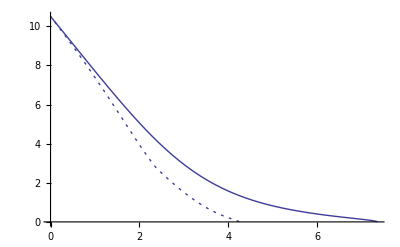

```mathematica
Show[grExLP,grExBPS,PlotRange-> All]
```

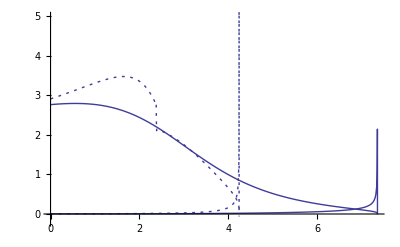

```mathematica
Show[grdEdxxeLP,grdEdxxiLP,grdEdxxeBPS,
grdEdxxiBPS,PlotRange->{ym,yM}]
```

```mathematica
NN=500;
xmin=0;
xmax=xRLPmax;
dx=(xmax-xmin)/NN;
data=Table[{x,dEdxxLP[x],dEdxxeLP[x],dEdxxiLP[x],ExLP[x]},{x,xmin,xmax,dx}]

(* Export["LPvsBPS.dEdxxExLP.aDT300127.dat",data,"Table",ConversionOptions-> {"FormatType"-> FortranForm}];
*)
```

InterpolatingFunction::dmval: Input value {0.0000823687} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{{0.,2.9171,2.91248,0.00461874,10.5},{0.00849117,2.92028,2.91565,0.00462892,10.4752},{0.0169823,2.92346,2.91882,0.00463916,10.4504},{0.0254735,2.92666,2.92201,0.00464945,10.4256},{0.0339647,2.92986,2.9252,0.00465981,10.4007},{0.0424559,2.93306,2.92839,0.00467022,10.3758},{0.050947,2.93628,2.9316,0.0046807,10.3509},{0.0594382,2.9395,2.93481,0.00469123,10.3259},{0.0679294,2.94273,2.93802,0.00470183,10.301},{0.0764206,2.94596,2.94125,0.00471248,10.276},{0.0849117,2.9492,2.94448,0.0047232,10.2509},{0.0934029,2.95245,2.94771,0.00473398,10.2259},{0.101894,2.9557,2.95095,0.00474483,10.2008},{0.110385,2.95896,2.9542,0.00475573,10.1757},{0.118876,2.96223,2.95746,0.0047667,10.1506},{0.127368,2.9655,2.96072,0.00477774,10.1254},{0.135859,2.96878,2.96399,0.00478884,10.1002},{0.14435,2.97206,2.96726,0.00480001,10.075},{0.152841,2.97535,2.97054,0.00481124,10.0497},{0.161332,2.97865,2.97383,0.00482254,10.0244},{0.169823,2.98196,2.97712,0.00483391,9.99914},{0.178315,2.98527,2.98042,0.00484535,9.9738},{0.186806,2.98858,2.98373,0.00485685,9.94844},{0.195297,2.99191,2.98704,0.00486843,9.92305},{0.203788,2.99523,2.99035,0.00488007,9.89763},{0.212279,2.99857,2.99368,0.00489179,9.87218},{0.220771,3.00191,2.99701,0.00490357,9.84671},{0.229262,3.00526,3.00034,0.00491543,9.82121},{0.237753,3.00861,3.00368,0.00492736,9.79567},{0.246244,3.01197,3.00703,0.00493937,9.77011},{0.254735,3.01533,3.01038,0.00495145,9.74452},{0.263226,3.0187,3.01374,0.0049636,9.7189},{0.271718,3.02208,3.0171,0.00497583,9.69326},{0.280209,3.02546,3.02047,0.00498814,9.66758},{0.2887,3.02885,3.02385,0.00500052,9.64188},{0.297191,3.03224,3.02723,0.00501298,9.61615},{0.305682,3.03564,3.03061,0.00502552,9.59038},{0.314173,3.03904,3.034,0.00503814,9.56459},{0.322665,3.04245,3.0374,0.00505084,9.53877},{0.331156,3.04586,3.0408,0.00506361,9.51293},{0.339647,3.04928,3.0442,0.00507647,9.48705},{0.348138,3.0527,3.04762,0.00508942,9.46114},{0.356629,3.05613,3.05103,0.00510244,9.43521},{0.36512,3.05957,3.05445,0.00511555,9.40924},{0.373612,3.06301,3.05788,0.00512875,9.38325},{0.382103,3.06645,3.06131,0.00514203,9.35722},{0.390594,3.0699,3.06474,0.00515539,9.33117},{0.399085,3.07335,3.06818,0.00516884,9.30509},{0.407576,3.07681,3.07163,0.00518239,9.27898},{0.416067,3.08027,3.07507,0.00519602,9.25284},{0.424559,3.08374,3.07853,0.00520974,9.22667},{0.43305,3.08721,3.08198,0.00522355,9.20047},{0.441541,3.09068,3.08544,0.00523745,9.17424},{0.450032,3.09416,3.08891,0.00525144,9.14798},{0.458523,3.09764,3.09238,0.00526553,9.12169},{0.467015,3.10113,3.09585,0.00527971,9.09538},{0.475506,3.10462,3.09933,0.00529399,9.06903},{0.483997,3.10811,3.10281,0.00530836,9.04265},{0.492488,3.11161,3.10629,0.00532283,9.01625},{0.500979,3.11511,3.10978,0.0053374,8.98981},{0.50947,3.11862,3.11326,0.00535207,8.96334},{0.517962,3.12212,3.11676,0.00536684,8.93685},{0.526453,3.12563,3.12025,0.00538171,8.91032},{0.534944,3.12915,3.12375,0.00539668,8.88377},{0.543435,3.13266,3.12725,0.00541176,8.85718},{0.551926,3.13618,3.13076,0.00542694,8.83057},{0.560417,3.1397,3.13426,0.00544222,8.80392},{0.568909,3.14323,3.13777,0.00545762,8.77725},{0.5774,3.14675,3.14128,0.00547312,8.75054},{0.585891,3.15028,3.14479,0.00548873,8.72381},{0.594382,3.15381,3.14831,0.00550444,8.69705},{0.602873,3.15734,3.15182,0.00552027,8.67025},{0.611364,3.16088,3.15534,0.00553622,8.64343},{0.619856,3.16441,3.15886,0.00555227,8.61657},{0.628347,3.16795,3.16238,0.00556844,8.58969},{0.636838,3.17148,3.1659,0.00558473,8.56277},{0.645329,3.17502,3.16942,0.00560113,8.53583},{0.65382,3.17856,3.17294,0.00561765,8.50885},{0.662312,3.1821,3.17647,0.00563429,8.48185},{0.670803,3.18564,3.17999,0.00565106,8.45481},{0.679294,3.18918,3.18351,0.00566794,8.42775},{0.687785,3.19272,3.18704,0.00568495,8.40065},{0.696276,3.19626,3.19056,0.00570208,8.37353},{0.704767,3.1998,3.19408,0.00571934,8.34637},{0.713259,3.20334,3.1976,0.00573673,8.31919},{0.72175,3.20688,3.20112,0.00575424,8.29197},{0.730241,3.21041,3.20464,0.00577189,8.26473},{0.738732,3.21395,3.20816,0.00578967,8.23745},{0.747223,3.21748,3.21168,0.00580758,8.21015},{0.755714,3.22102,3.21519,0.00582563,8.18281},{0.764206,3.22455,3.2187,0.00584381,8.15545},{0.772697,3.22808,3.22221,0.00586213,8.12805},{0.781188,3.2316,3.22572,0.00588059,8.10063},{0.789679,3.23513,3.22923,0.00589919,8.07317},{0.79817,3.23865,3.23273,0.00591794,8.04569},{0.806661,3.24216,3.23623,0.00593683,8.01817},{0.815153,3.24568,3.23972,0.00595586,7.99063},{0.823644,3.24919,3.24321,0.00597504,7.96305},{0.832135,3.25269,3.2467,0.00599437,7.93545},{0.840626,3.25619,3.25018,0.00601385,7.90781},{0.849117,3.25969,3.25366,0.00603349,7.88015},{0.857608,3.26318,3.25713,0.00605327,7.85246},{0.8661,3.26667,3.26059,0.00607322,7.82473},{0.874591,3.27015,3.26405,0.00609332,7.79698},{0.883082,3.27362,3.26751,0.00611358,7.7692},{0.891573,3.27709,3.27096,0.006134,7.74139},{0.900064,3.28055,3.2744,0.00615459,7.71355},{0.908556,3.28401,3.27783,0.00617534,7.68568},{0.917047,3.28745,3.28126,0.00619626,7.65778},{0.925538,3.29089,3.28468,0.00621735,7.62985},{0.934029,3.29432,3.28809,0.00623861,7.60189},{0.94252,3.29775,3.29149,0.00626004,7.5739},{0.951011,3.30116,3.29488,0.00628165,7.54589},{0.959503,3.30457,3.29826,0.00630344,7.51784},{0.967994,3.30796,3.30164,0.0063254,7.48977},{0.976485,3.31135,3.305,0.00634755,7.46166},{0.984976,3.31472,3.30835,0.00636988,7.43353},{0.993467,3.31809,3.31169,0.0063924,7.40537},{1.00196,3.32144,3.31502,0.0064151,7.37718},{1.01045,3.32478,3.31834,0.006438,7.34897},{1.01894,3.32811,3.32164,0.00646109,7.32072},{1.02743,3.33142,3.32494,0.00648437,7.29245},{1.03592,3.33472,3.32822,0.00650785,7.26415},{1.04441,3.33801,3.33148,0.00653154,7.23582},{1.05291,3.34129,3.33473,0.00655542,7.20746},{1.0614,3.34454,3.33797,0.00657951,7.17907},{1.06989,3.34779,3.34118,0.00660381,7.15066},{1.07838,3.35102,3.34439,0.00662831,7.12222},{1.08687,3.35423,3.34758,0.00665303,7.09375},{1.09536,3.35742,3.35074,0.00667797,7.06526},{1.10385,3.3606,3.3539,0.00670312,7.03674},{1.11234,3.36376,3.35703,0.00672849,7.00819},{1.12083,3.3669,3.36014,0.00675409,6.97961},{1.12933,3.37002,3.36324,0.00677991,6.95101},{1.13782,3.37312,3.36631,0.00680597,6.92238},{1.14631,3.3762,3.36937,0.00683225,6.89373},{1.1548,3.37926,3.3724,0.00685877,6.86504},{1.16329,3.3823,3.37541,0.00688553,6.83634},{1.17178,3.38531,3.3784,0.00691253,6.80761},{1.18027,3.3883,3.38136,0.00693977,6.77885},{1.18876,3.39127,3.3843,0.00696726,6.75006},{1.19726,3.39421,3.38722,0.006995,6.72126},{1.20575,3.39713,3.3901,0.007023,6.69242},{1.21424,3.40002,3.39297,0.00705125,6.66356},{1.22273,3.40288,3.3958,0.00707976,6.63468},{1.23122,3.40572,3.39861,0.00710854,6.60578},{1.23971,3.40852,3.40139,0.00713758,6.57685},{1.2482,3.4113,3.40413,0.0071669,6.54789},{1.25669,3.41405,3.40685,0.00719649,6.51891},{1.26518,3.41676,3.40954,0.00722635,6.48991},{1.27368,3.41945,3.41219,0.0072565,6.46089},{1.28217,3.4221,3.41481,0.00728693,6.43184},{1.29066,3.42472,3.4174,0.00731765,6.40277},{1.29915,3.4273,3.41995,0.00734867,6.37368},{1.30764,3.42985,3.42247,0.00737998,6.34457},{1.31613,3.43236,3.42494,0.00741159,6.31544},{1.32462,3.43483,3.42738,0.00744351,6.28628},{1.33311,3.43726,3.42979,0.00747574,6.25711},{1.34161,3.43966,3.43215,0.00750827,6.22791},{1.3501,3.44201,3.43447,0.00754113,6.19869},{1.35859,3.44432,3.43675,0.00757431,6.16946},{1.36708,3.44659,3.43898,0.00760781,6.1402},{1.37557,3.44881,3.44117,0.00764164,6.11092},{1.38406,3.45099,3.44331,0.00767581,6.08163},{1.39255,3.45312,3.44541,0.00771032,6.05232},{1.40104,3.45521,3.44746,0.00774517,6.02299},{1.40953,3.45724,3.44946,0.00778037,5.99364},{1.41803,3.45923,3.45141,0.00781592,5.96428},{1.42652,3.46116,3.45331,0.00785184,5.9349},{1.43501,3.46304,3.45516,0.00788811,5.9055},{1.4435,3.46487,3.45695,0.00792476,5.87608},{1.45199,3.46664,3.45868,0.00796177,5.84666},{1.46048,3.46836,3.46036,0.00799917,5.81721},{1.46897,3.47002,3.46198,0.00803695,5.78776},{1.47746,3.47162,3.46354,0.00807511,5.75828},{1.48596,3.47315,3.46504,0.00811368,5.7288},{1.49445,3.47463,3.46647,0.00815264,5.6993},{1.50294,3.47604,3.46784,0.00819201,5.66979},{1.51143,3.47738,3.46915,0.00823179,5.64027},{1.51992,3.47866,3.47039,0.00827199,5.61074},{1.52841,3.47987,3.47155,0.00831261,5.5812},{1.5369,3.481,3.47265,0.00835365,5.55164},{1.54539,3.48207,3.47367,0.00839514,5.52208},{1.55388,3.48306,3.47462,0.00843706,5.49251},{1.56238,3.48398,3.4755,0.00847943,5.46293},{1.57087,3.48481,3.47629,0.00852226,5.43334},{1.57936,3.48557,3.47701,0.00856555,5.40375},{1.58785,3.48625,3.47764,0.0086093,5.37415},{1.59634,3.48685,3.47819,0.00865353,5.34455},{1.60483,3.48736,3.47866,0.00869823,5.31494},{1.61332,3.48778,3.47904,0.00874342,5.28532},{1.62181,3.48811,3.47932,0.00878911,5.25571},{1.63031,3.48835,3.47952,0.0088353,5.22609},{1.6388,3.4885,3.47962,0.00888199,5.19647},{1.64729,3.48856,3.47963,0.0089292,5.16684},{1.65578,3.48851,3.47954,0.00897694,5.13722},{1.66427,3.48837,3.47935,0.0090252,5.1076},{1.67276,3.48812,3.47905,0.009074,5.07798},{1.68125,3.48778,3.47865,0.00912335,5.04836},{1.68974,3.48732,3.47815,0.00917324,5.01875},{1.69823,3.48675,3.47753,0.0092237,4.98914},{1.70673,3.48608,3.4768,0.00927473,4.95954},{1.71522,3.48528,3.47596,0.00932634,4.92994},{1.72371,3.48438,3.475,0.00937853,4.90035},{1.7322,3.48335,3.47392,0.00943131,4.87077},{1.74069,3.4822,3.47271,0.0094847,4.84119},{1.74918,3.48093,3.47139,0.00953869,4.81163},{1.75767,3.47952,3.46993,0.00959331,4.78208},{1.76616,3.47799,3.46834,0.00964856,4.75254},{1.77466,3.47633,3.46662,0.00970444,4.72302},{1.78315,3.47453,3.46477,0.00976096,4.69351},{1.79164,3.47259,3.46277,0.00981815,4.66401},{1.80013,3.47051,3.46063,0.00987599,4.63453},{1.80862,3.46828,3.45835,0.00993451,4.60507},{1.81711,3.46591,3.45592,0.00999372,4.57563},{1.8256,3.46339,3.45333,0.0100536,4.54622},{1.83409,3.46071,3.45059,0.0101142,4.51682},{1.84258,3.45787,3.4477,0.0101755,4.48745},{1.85108,3.45487,3.44464,0.0102376,4.4581},{1.85957,3.45171,3.44141,0.0103003,4.42877},{1.86806,3.44838,3.43802,0.0103638,4.39948},{1.87655,3.44488,3.43445,0.0104281,4.37021},{1.88504,3.44121,3.43071,0.0104931,4.34098},{1.89353,3.43735,3.42679,0.0105589,4.31177},{1.90202,3.43332,3.42269,0.0106255,4.2826},{1.91051,3.42909,3.4184,0.0106928,4.25347},{1.91901,3.42468,3.41392,0.010761,4.22437},{1.9275,3.42008,3.40925,0.01083,4.19531},{1.93599,3.41527,3.40437,0.0108998,4.16629},{1.94448,3.41027,3.3993,0.0109705,4.13731},{1.95297,3.40506,3.39402,0.011042,4.10838},{1.96146,3.39964,3.38853,0.0111143,4.07949},{1.96995,3.39401,3.38282,0.0111876,4.05064},{1.97844,3.38816,3.3769,0.0112617,4.02185},{1.98693,3.38209,3.37075,0.0113367,3.9931},{1.99543,3.37579,3.36438,0.0114126,3.96441},{2.00392,3.36926,3.35777,0.0114894,3.93578},{2.01241,3.3625,3.35093,0.0115671,3.9072},{2.0209,3.3555,3.34385,0.0116458,3.87867},{2.02939,3.34825,3.33653,0.0117254,3.85021},{2.03788,3.34076,3.32895,0.011806,3.82181},{2.04637,3.33301,3.32112,0.0118875,3.79348},{2.05486,3.32501,3.31304,0.01197,3.76521},{2.06336,3.31674,3.30469,0.0120536,3.73701},{2.07185,3.30821,3.29607,0.0121381,3.70889},{2.08034,3.2994,3.28718,0.0122236,3.68083},{2.08883,3.29032,3.27801,0.0123101,3.65286},{2.09732,3.28096,3.26856,0.0123977,3.62496},{2.10581,3.27131,3.25882,0.0124863,3.59714},{2.1143,3.26137,3.2488,0.012576,3.5694},{2.12279,3.25114,3.23847,0.0126667,3.54175},{2.13128,3.2406,3.22785,0.0127585,3.51419},{2.13978,3.22977,3.21691,0.0128514,3.48672},{2.14827,3.21862,3.20567,0.0129454,3.45934},{2.15676,3.20715,3.19411,0.0130405,3.43206},{2.16525,3.19537,3.18223,0.0131366,3.40488},{2.17374,3.18326,3.17003,0.0132339,3.3778},{2.18223,3.17083,3.1575,0.0133324,3.35082},{2.19072,3.15806,3.14463,0.0134319,3.32395},{2.19921,3.14495,3.13142,0.0135326,3.29719},{2.20771,3.1315,3.11787,0.0136344,3.27054},{2.2162,3.1177,3.10397,0.0137374,3.24401},{2.22469,3.10355,3.08971,0.0138415,3.2176},{2.23318,3.08905,3.0751,0.0139468,3.19131},{2.24167,3.07418,3.06013,0.0140532,3.16514},{2.25016,3.05895,3.04479,0.0141608,3.1391},{2.25865,3.04335,3.02908,0.0142696,3.11319},{2.26714,3.02737,3.01299,0.0143795,3.08742},{2.27563,3.01102,2.99653,0.0144907,3.06178},{2.28413,2.99429,2.97969,0.014603,3.03629},{2.29262,2.97717,2.96246,0.0147164,3.01093},{2.30111,2.95967,2.94484,0.014831,2.98573},{2.3096,2.94178,2.92683,0.0149468,2.96067},{2.31809,2.92349,2.90843,0.0150638,2.93577},{2.32658,2.90481,2.88963,0.0151819,2.91103},{2.33507,2.88573,2.87042,0.0153012,2.88644},{2.34356,2.86624,2.85082,0.0154216,2.86202},{2.35205,2.84636,2.83081,0.0155431,2.83777},{2.36055,2.82607,2.8104,0.0156658,2.81368},{2.36904,2.80537,2.78958,0.0157896,2.78978},{2.37753,2.81724,2.80133,0.0159153,2.76589},{2.38602,2.16814,2.15211,0.0160296,2.74451},{2.39451,2.1628,2.14667,0.0161282,2.72632},{2.403,2.1593,2.14307,0.0162289,2.70797},{2.41149,2.15574,2.13941,0.0163308,2.68965},{2.41998,2.15213,2.1357,0.0164339,2.67136},{2.42848,2.14848,2.13194,0.0165381,2.6531},{2.43697,2.14477,2.12812,0.0166435,2.63488},{2.44546,2.14101,2.12426,0.0167502,2.61668},{2.45395,2.1372,2.12034,0.0168581,2.59852},{2.46244,2.13334,2.11637,0.0169672,2.58039},{2.47093,2.12943,2.11235,0.0170776,2.56229},{2.47942,2.12546,2.10828,0.0171893,2.54422},{2.48791,2.12145,2.10415,0.0173023,2.52619},{2.4964,2.11738,2.09997,0.0174167,2.5082},{2.5049,2.11327,2.09573,0.0175324,2.49023},{2.51339,2.1091,2.09145,0.0176494,2.47231},{2.52188,2.10487,2.08711,0.0177679,2.45442},{2.53037,2.1006,2.08271,0.0178878,2.43656},{2.53886,2.09628,2.07827,0.0180091,2.41874},{2.54735,2.0919,2.07377,0.0181319,2.40096},{2.55584,2.08747,2.06921,0.0182562,2.38322},{2.56433,2.08299,2.0646,0.018382,2.36551},{2.57283,2.07845,2.05994,0.0185093,2.34785},{2.58132,2.07386,2.05523,0.0186381,2.33022},{2.58981,2.06922,2.05046,0.0187686,2.31263},{2.5983,2.06453,2.04563,0.0189007,2.29508},{2.60679,2.05979,2.04075,0.0190344,2.27757},{2.61528,2.05499,2.03582,0.0191697,2.2601},{2.62377,2.05014,2.03083,0.0193068,2.24267},{2.63226,2.04524,2.02579,0.0194455,2.22528},{2.64075,2.04028,2.0207,0.019586,2.20793},{2.64925,2.03528,2.01555,0.0197283,2.19063},{2.65774,2.03022,2.01034,0.0198724,2.17337},{2.66623,2.02511,2.00509,0.0200183,2.15615},{2.67472,2.01994,1.99977,0.0201661,2.13898},{2.68321,2.01472,1.99441,0.0203157,2.12185},{2.6917,2.00945,1.98899,0.0204673,2.10477},{2.70019,2.00413,1.98351,0.0206209,2.08773},{2.70868,1.99876,1.97798,0.0207764,2.07073},{2.71718,1.99333,1.9724,0.020934,2.05378},{2.72567,1.98785,1.96676,0.0210936,2.03688},{2.73416,1.98232,1.96107,0.0212553,2.02002},{2.74265,1.97674,1.95532,0.0214192,2.00322},{2.75114,1.97111,1.94952,0.0215852,1.98645},{2.75963,1.96542,1.94367,0.0217534,1.96974},{2.76812,1.95968,1.93776,0.0219239,1.95308},{2.77661,1.95389,1.9318,0.0220966,1.93646},{2.7851,1.94805,1.92578,0.0222717,1.9199},{2.7936,1.94216,1.91971,0.0224491,1.90338},{2.80209,1.93622,1.91359,0.022629,1.88691},{2.81058,1.93023,1.90742,0.0228113,1.8705},{2.81907,1.92418,1.90119,0.0229961,1.85413},{2.82756,1.91809,1.89491,0.0231834,1.83782},{2.83605,1.91195,1.88857,0.0233733,1.82156},{2.84454,1.90575,1.88219,0.0235658,1.80535},{2.85303,1.89951,1.87575,0.0237611,1.7892},{2.86153,1.89321,1.86926,0.023959,1.77309},{2.87002,1.88687,1.86271,0.0241597,1.75705},{2.87851,1.88048,1.85612,0.0243633,1.74105},{2.887,1.87404,1.84947,0.0245697,1.72511},{2.89549,1.86755,1.84277,0.0247791,1.70922},{2.90398,1.86101,1.83602,0.0249914,1.69339},{2.91247,1.85443,1.82922,0.0252068,1.67762},{2.92096,1.8478,1.82237,0.0254253,1.6619},{2.92945,1.84111,1.81547,0.025647,1.64624},{2.93795,1.83439,1.80852,0.0258719,1.63064},{2.94644,1.82761,1.80151,0.0261001,1.61509},{2.95493,1.82079,1.79446,0.0263316,1.5996},{2.96342,1.81393,1.78736,0.0265666,1.58417},{2.97191,1.80701,1.78021,0.026805,1.56879},{2.9804,1.80006,1.77301,0.027047,1.55348},{2.98889,1.79305,1.76576,0.0272925,1.53823},{2.99738,1.78601,1.75847,0.0275418,1.52303},{3.00588,1.77892,1.75112,0.0277949,1.5079},{3.01437,1.77178,1.74373,0.0280517,1.49282},{3.02286,1.7646,1.73629,0.0283125,1.47781},{3.03135,1.75738,1.7288,0.0285773,1.46285},{3.03984,1.75012,1.72127,0.0288462,1.44796},{3.04833,1.74281,1.71369,0.0291192,1.43313},{3.05682,1.73546,1.70607,0.0293965,1.41836},{3.06531,1.72807,1.6984,0.0296781,1.40366},{3.0738,1.72064,1.69068,0.0299641,1.38902},{3.0823,1.71317,1.68292,0.0302547,1.37444},{3.09079,1.70566,1.67511,0.0305498,1.35992},{3.09928,1.69811,1.66727,0.0308497,1.34547},{3.10777,1.69053,1.65937,0.0311543,1.33109},{3.11626,1.6829,1.65144,0.0314639,1.31676},{3.12475,1.67524,1.64346,0.0317785,1.30251},{3.13324,1.66754,1.63544,0.0320982,1.28832},{3.14173,1.6598,1.62737,0.0324231,1.27419},{3.15023,1.65202,1.61927,0.0327534,1.26013},{3.15872,1.64421,1.61112,0.0330892,1.24613},{3.16721,1.63637,1.60294,0.0334305,1.23221},{3.1757,1.62849,1.59471,0.0337776,1.21834},{3.18419,1.62057,1.58644,0.0341305,1.20455},{3.19268,1.61263,1.57814,0.0344893,1.19082},{3.20117,1.60465,1.56979,0.0348543,1.17716},{3.20966,1.59664,1.56141,0.0352255,1.16357},{3.21815,1.58859,1.55299,0.0356031,1.15005},{3.22665,1.58052,1.54453,0.0359873,1.13659},{3.23514,1.57241,1.53603,0.0363782,1.12321},{3.24363,1.56428,1.5275,0.0367759,1.10989},{3.25212,1.55611,1.51893,0.0371806,1.09664},{3.26061,1.54792,1.51033,0.0375925,1.08347},{3.2691,1.5397,1.50169,0.0380117,1.07036},{3.27759,1.53145,1.49301,0.0384385,1.05732},{3.28608,1.52318,1.4843,0.0388729,1.04435},{3.29458,1.51488,1.47556,0.0393153,1.03145},{3.30307,1.50655,1.46679,0.0397658,1.01862},{3.31156,1.4982,1.45798,0.0402246,1.00587},{3.32005,1.48983,1.44914,0.0406918,0.99318},{3.32854,1.48143,1.44026,0.0411678,0.980565},{3.33703,1.47301,1.43136,0.0416527,0.968022},{3.34552,1.46457,1.42242,0.0421468,0.95555},{3.35401,1.45611,1.41346,0.0426503,0.94315},{3.3625,1.44763,1.40446,0.0431635,0.930822},{3.371,1.43912,1.39544,0.0436865,0.918566},{3.37949,1.4306,1.38638,0.0442198,0.906382},{3.38798,1.42206,1.3773,0.0447634,0.894271},{3.39647,1.41351,1.36819,0.0453178,0.882232},{3.40496,1.40493,1.35905,0.0458831,0.870266},{3.41345,1.39634,1.34988,0.0464598,0.858373},{3.42194,1.38774,1.34069,0.0470481,0.846553},{3.43043,1.37912,1.33147,0.0476483,0.834806},{3.43893,1.37049,1.32223,0.0482608,0.823133},{3.44742,1.36184,1.31296,0.048886,0.811532},{3.45591,1.35319,1.30366,0.0495241,0.800005},{3.4644,1.34452,1.29434,0.0501755,0.788552},{3.47289,1.33584,1.285,0.0508407,0.777172},{3.48138,1.32715,1.27563,0.0515201,0.765866},{3.48987,1.31845,1.26624,0.052214,0.754634},{3.49836,1.30974,1.25682,0.0529229,0.743476},{3.50685,1.30103,1.24738,0.0536473,0.732392},{3.51535,1.29231,1.23792,0.0543875,0.721381},{3.52384,1.28359,1.22844,0.0551442,0.710445},{3.53233,1.27486,1.21894,0.0559178,0.699583},{3.54082,1.26612,1.20942,0.0567089,0.688795},{3.54931,1.25739,1.19987,0.057518,0.678081},{3.5578,1.24865,1.1903,0.0583456,0.667442},{3.56629,1.23991,1.18072,0.0591925,0.656876},{3.57478,1.23117,1.17111,0.0600591,0.646385},{3.58328,1.22243,1.16148,0.0609462,0.635968},{3.59177,1.21369,1.15184,0.0618545,0.625625},{3.60026,1.20496,1.14217,0.0627846,0.615357},{3.60875,1.19623,1.13249,0.0637374,0.605162},{3.61724,1.1875,1.12279,0.0647135,0.595042},{3.62573,1.17878,1.11306,0.0657139,0.584996},{3.63422,1.17006,1.10332,0.0667393,0.575024},{3.64271,1.16135,1.09356,0.0677907,0.565125},{3.6512,1.15266,1.08379,0.0688691,0.555301},{3.6597,1.14397,1.07399,0.0699754,0.545551},{3.66819,1.13529,1.06418,0.0711106,0.535874},{3.67668,1.12662,1.05434,0.0722758,0.526271},{3.68517,1.11797,1.04449,0.0734723,0.516741},{3.69366,1.10933,1.03462,0.0747012,0.507285},{3.70215,1.1007,1.02474,0.0759637,0.497902},{3.71064,1.09209,1.01483,0.0772613,0.488593},{3.71913,1.0835,1.00491,0.0785953,0.479356},{3.72763,1.07493,0.994963,0.0799672,0.470192},{3.73612,1.06638,0.985,0.0813787,0.461101},{3.74461,1.05785,0.975019,0.0828313,0.452082},{3.7531,1.04934,0.965018,0.0843269,0.443136},{3.76159,1.04086,0.954996,0.0858673,0.434262},{3.77008,1.03241,0.944955,0.0874546,0.42546},{3.77857,1.02398,0.934893,0.0890907,0.416729},{3.78706,1.01559,0.924809,0.0907781,0.40807},{3.79555,1.00722,0.914703,0.0925189,0.399482},{3.80405,0.998891,0.904575,0.0943159,0.390965},{3.81254,0.990595,0.894424,0.0961716,0.382518},{3.82103,0.982337,0.884248,0.098089,0.374142},{3.82952,0.974119,0.874048,0.100071,0.365836},{3.83801,0.965942,0.863821,0.102121,0.357599},{3.8465,0.957811,0.853568,0.104243,0.349432},{3.85499,0.949726,0.843286,0.10644,0.341333},{3.86348,0.941692,0.832975,0.108717,0.333303},{3.87197,0.933711,0.822633,0.111078,0.325341},{3.88047,0.925786,0.812259,0.113527,0.317446},{3.88896,0.917921,0.801851,0.11607,0.309619},{3.89745,0.91012,0.791407,0.118712,0.301858},{3.90594,0.902385,0.780926,0.121459,0.294163},{3.91443,0.894723,0.770405,0.124319,0.286533},{3.92292,0.887138,0.759841,0.127296,0.278968},{3.93141,0.879634,0.749233,0.130401,0.271467},{3.9399,0.872219,0.738577,0.133642,0.264029},{3.9484,0.864897,0.727871,0.137026,0.256654},{3.95689,0.857675,0.717111,0.140564,0.249341},{3.96538,0.850562,0.706293,0.144269,0.242089},{3.97387,0.843566,0.695414,0.148151,0.234896},{3.98236,0.836695,0.684469,0.152226,0.227763},{3.99085,0.829961,0.673454,0.156507,0.220687},{3.99934,0.823375,0.662362,0.161013,0.213668},{4.00783,0.81695,0.651188,0.165762,0.206704},{4.01632,0.810701,0.639925,0.170775,0.199793},{4.02482,0.804645,0.628567,0.176078,0.192935},{4.03331,0.798801,0.617105,0.181696,0.186128},{4.0418,0.793192,0.60553,0.187662,0.179369},{4.05029,0.787843,0.593831,0.194012,0.172657},{4.05878,0.782784,0.581998,0.200786,0.165989},{4.06727,0.77805,0.570017,0.208033,0.159363},{4.07576,0.773681,0.557873,0.215808,0.152775},{4.08425,0.769727,0.545549,0.224177,0.146223},{4.09275,0.766245,0.533027,0.233218,0.139702},{4.10124,0.763307,0.520282,0.243024,0.133208},{4.10973,0.760998,0.507289,0.253709,0.126737},{4.11822,0.759425,0.494016,0.265408,0.120283},{4.12671,0.758721,0.480426,0.278295,0.113838},{4.1352,0.759056,0.466473,0.292583,0.107395},{4.14369,0.76065,0.452105,0.308544,0.100945},{4.15218,0.76379,0.437252,0.326539,0.0944739},{4.16067,0.768868,0.421829,0.347039,0.0879693},{4.16917,0.776425,0.405724,0.370702,0.0814106},{4.17766,0.78724,0.388787,0.398453,0.0747729},{4.18615,0.802459,0.370835,0.431625,0.0680289},{4.19464,0.823903,0.351576,0.472327,0.0611307},{4.20313,0.854626,0.330588,0.524037,0.0540121},{4.21162,0.900162,0.307231,0.592931,0.0465829},{4.22011,0.972167,0.280321,0.691846,0.0386734},{4.2286,1.1259,0.242353,0.883552,0.0287068},{4.2371,1.32876,0.210649,1.11811,0.0214658},{4.24559,-3.21379×10^-9,0.062472,-0.062472,0.0000823687}}

```mathematica
NN=500;
xmin=0;
xmax=xRBPSmax;
dx=(xmax-xmin)/NN;
data=Table[{x,dEdxxBPS[x],dEdxxeBPS[x],dEdxxiBPS[x],ExBPS[x]},{x,xmin,xmax,dx}]

(*
Export["LPvsBPS.dEdxxExBPS.aDT300127.dat",data,"Table",ConversionOptions-> {"FormatType"-> FortranForm}];
*)
```

InterpolatingFunction::dmval: Input value {0.000778436} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{{0.,2.77089,2.76811,0.00277814,10.5},{0.0147214,2.77233,2.76954,0.00278836,10.4592},{0.0294429,2.77374,2.77094,0.00279867,10.4184},{0.0441643,2.77512,2.77231,0.00280905,10.3775},{0.0588857,2.77648,2.77366,0.00281952,10.3367},{0.0736072,2.7778,2.77497,0.00283008,10.2958},{0.0883286,2.7791,2.77626,0.00284072,10.2549},{0.10305,2.78036,2.77751,0.00285146,10.214},{0.117771,2.7816,2.77873,0.00286228,10.173},{0.132493,2.7828,2.77992,0.00287318,10.1321},{0.147214,2.78397,2.78108,0.00288418,10.0911},{0.161936,2.7851,2.78221,0.00289527,10.0501},{0.176657,2.78621,2.7833,0.00290646,10.0091},{0.191379,2.78728,2.78436,0.00291774,9.96806},{0.2061,2.78832,2.78539,0.00292911,9.92702},{0.220822,2.78932,2.78638,0.00294058,9.88596},{0.235543,2.79028,2.78733,0.00295214,9.84489},{0.250264,2.79121,2.78825,0.0029638,9.80381},{0.264986,2.7921,2.78913,0.00297556,9.76271},{0.279707,2.79296,2.78997,0.00298742,9.7216},{0.294429,2.79378,2.79078,0.00299939,9.68048},{0.30915,2.79456,2.79154,0.00301145,9.63935},{0.323872,2.7953,2.79227,0.00302362,9.5982},{0.338593,2.796,2.79296,0.00303589,9.55704},{0.353314,2.79665,2.79361,0.00304827,9.51588},{0.368036,2.79727,2.79421,0.00306076,9.4747},{0.382757,2.79785,2.79477,0.00307335,9.43352},{0.397479,2.79838,2.7953,0.00308606,9.39233},{0.4122,2.79887,2.79577,0.00309887,9.35113},{0.426922,2.79932,2.79621,0.0031118,9.30992},{0.441643,2.79972,2.7966,0.00312484,9.26871},{0.456364,2.80008,2.79694,0.00313799,9.22749},{0.471086,2.80039,2.79724,0.00315126,9.18627},{0.485807,2.80065,2.79749,0.00316465,9.14504},{0.500529,2.80087,2.79769,0.00317816,9.10381},{0.51525,2.80104,2.79785,0.00319179,9.06257},{0.529972,2.80116,2.79796,0.00320553,9.02134},{0.544693,2.80123,2.79801,0.0032194,8.9801},{0.559414,2.80125,2.79802,0.0032334,8.93886},{0.574136,2.80122,2.79798,0.00324752,8.89762},{0.588857,2.80114,2.79788,0.00326177,8.85638},{0.603579,2.80101,2.79773,0.00327614,8.81515},{0.6183,2.80082,2.79753,0.00329065,8.77391},{0.633022,2.80058,2.79728,0.00330529,8.73268},{0.647743,2.80029,2.79697,0.00332006,8.69146},{0.662465,2.79994,2.79661,0.00333497,8.65024},{0.677186,2.79953,2.79618,0.00335001,8.60902},{0.691907,2.79907,2.79571,0.00336519,8.56781},{0.706629,2.79855,2.79517,0.00338051,8.52661},{0.72135,2.79798,2.79458,0.00339597,8.48541},{0.736072,2.79734,2.79393,0.00341157,8.44423},{0.750793,2.79664,2.79322,0.00342732,8.40305},{0.765515,2.79589,2.79244,0.00344321,8.36189},{0.780236,2.79507,2.79161,0.00345925,8.32073},{0.794957,2.79419,2.79071,0.00347544,8.27959},{0.809679,2.79325,2.78976,0.00349178,8.23846},{0.8244,2.79224,2.78873,0.00350828,8.19735},{0.839122,2.79117,2.78765,0.00352493,8.15625},{0.853843,2.79003,2.78649,0.00354173,8.11517},{0.868565,2.78883,2.78527,0.0035587,8.07411},{0.883286,2.78756,2.78398,0.00357582,8.03306},{0.898007,2.78623,2.78264,0.00359311,7.99203},{0.912729,2.78483,2.78122,0.00361056,7.95103},{0.92745,2.78336,2.77973,0.00362818,7.91004},{0.942172,2.78182,2.77817,0.00364597,7.86908},{0.956893,2.78021,2.77654,0.00366392,7.82814},{0.971615,2.77852,2.77484,0.00368205,7.78722},{0.986336,2.77677,2.77307,0.00370035,7.74633},{1.00106,2.77494,2.77122,0.00371883,7.70546},{1.01578,2.77304,2.76931,0.00373749,7.66463},{1.0305,2.77107,2.76731,0.00375632,7.62382},{1.04522,2.76902,2.76524,0.00377534,7.58304},{1.05994,2.76689,2.7631,0.00379454,7.54229},{1.07466,2.76469,2.76088,0.00381393,7.50157},{1.08939,2.76242,2.75858,0.00383351,7.46089},{1.10411,2.76006,2.75621,0.00385328,7.42024},{1.11883,2.75763,2.75375,0.00387325,7.37963},{1.13355,2.75511,2.75122,0.00389341,7.33905},{1.14827,2.75252,2.74861,0.00391376,7.29851},{1.16299,2.74985,2.74591,0.00393432,7.25801},{1.17771,2.74709,2.74314,0.00395508,7.21755},{1.19244,2.74426,2.74028,0.00397605,7.17712},{1.20716,2.74134,2.73734,0.00399722,7.13675},{1.22188,2.73833,2.73431,0.0040186,7.09641},{1.2366,2.73525,2.73121,0.0040402,7.05612},{1.25132,2.73207,2.72801,0.00406201,7.01588},{1.26604,2.72882,2.72473,0.00408404,6.97568},{1.28076,2.72548,2.72137,0.00410628,6.93554},{1.29549,2.72205,2.71792,0.00412875,6.89544},{1.31021,2.71853,2.71438,0.00415145,6.85539},{1.32493,2.71493,2.71075,0.00417437,6.8154},{1.33965,2.71123,2.70704,0.00419753,6.77546},{1.35437,2.70745,2.70323,0.00422091,6.73557},{1.36909,2.70358,2.69934,0.00424454,6.69574},{1.38381,2.69962,2.69536,0.0042684,6.65597},{1.39854,2.69557,2.69128,0.00429251,6.61626},{1.41326,2.69143,2.68712,0.00431685,6.5766},{1.42798,2.6872,2.68286,0.00434145,6.53701},{1.4427,2.68287,2.67851,0.0043663,6.49749},{1.45742,2.67846,2.67407,0.00439139,6.45802},{1.47214,2.67395,2.66953,0.00441675,6.41863},{1.48686,2.66934,2.6649,0.00444236,6.37929},{1.50159,2.66465,2.66018,0.00446824,6.34003},{1.51631,2.65986,2.65536,0.00449438,6.30084},{1.53103,2.65497,2.65045,0.00452079,6.26172},{1.54575,2.64999,2.64544,0.00454747,6.22267},{1.56047,2.64492,2.64034,0.00457443,6.1837},{1.57519,2.63975,2.63514,0.00460166,6.1448},{1.58991,2.63448,2.62985,0.00462918,6.10598},{1.60464,2.62912,2.62446,0.00465697,6.06723},{1.61936,2.62366,2.61897,0.00468506,6.02857},{1.63408,2.6181,2.61339,0.00471344,5.98998},{1.6488,2.61245,2.60771,0.00474211,5.95148},{1.66352,2.6067,2.60193,0.00477107,5.91307},{1.67824,2.60086,2.59606,0.00480034,5.87473},{1.69296,2.59492,2.59009,0.00482992,5.83649},{1.70769,2.58888,2.58402,0.0048598,5.79833},{1.72241,2.58274,2.57785,0.00488999,5.76027},{1.73713,2.57651,2.57159,0.0049205,5.72229},{1.75185,2.57018,2.56522,0.00495132,5.68441},{1.76657,2.56375,2.55876,0.00498247,5.64662},{1.78129,2.55722,2.55221,0.00501394,5.60892},{1.79601,2.5506,2.54555,0.00504574,5.57133},{1.81074,2.54388,2.5388,0.00507788,5.53383},{1.82546,2.53706,2.53195,0.00511035,5.49643},{1.84018,2.53015,2.525,0.00514317,5.45913},{1.8549,2.52314,2.51796,0.00517632,5.42193},{1.86962,2.51603,2.51082,0.00520983,5.38484},{1.88434,2.50882,2.50358,0.00524369,5.34785},{1.89906,2.50152,2.49624,0.0052779,5.31098},{1.91379,2.49412,2.48881,0.00531248,5.2742},{1.92851,2.48663,2.48128,0.00534742,5.23754},{1.94323,2.47904,2.47366,0.00538273,5.20099},{1.95795,2.47136,2.46594,0.00541841,5.16455},{1.97267,2.46359,2.45813,0.00545446,5.12823},{1.98739,2.45572,2.45023,0.0054909,5.09202},{2.00211,2.44776,2.44223,0.00552772,5.05592},{2.01684,2.43971,2.43414,0.00556493,5.01995},{2.03156,2.43156,2.42596,0.00560253,4.98409},{2.04628,2.42332,2.41768,0.00564054,4.94836},{2.061,2.41499,2.40931,0.00567894,4.91274},{2.07572,2.40657,2.40085,0.00571775,4.87725},{2.09044,2.39806,2.3923,0.00575697,4.84189},{2.10517,2.38946,2.38366,0.0057966,4.80665},{2.11989,2.38077,2.37493,0.00583666,4.77154},{2.13461,2.37199,2.36611,0.00587714,4.73655},{2.14933,2.36313,2.35721,0.00591804,4.7017},{2.16405,2.35418,2.34822,0.00595938,4.66698},{2.17877,2.34514,2.33914,0.00600116,4.63238},{2.19349,2.33602,2.32998,0.00604338,4.59793},{2.20822,2.32682,2.32073,0.00608605,4.56361},{2.22294,2.31753,2.3114,0.00612917,4.52942},{2.23766,2.30817,2.30199,0.00617274,4.49537},{2.25238,2.29872,2.2925,0.00621678,4.46146},{2.2671,2.28919,2.28293,0.00626129,4.42769},{2.28182,2.27959,2.27328,0.00630626,4.39406},{2.29654,2.2699,2.26355,0.00635171,4.36057},{2.31127,2.26014,2.25375,0.00639764,4.32723},{2.32599,2.25031,2.24386,0.00644406,4.29403},{2.34071,2.2404,2.23391,0.00649097,4.26097},{2.35543,2.23042,2.22388,0.00653837,4.22807},{2.37015,2.22037,2.21378,0.00658627,4.1953},{2.38487,2.21024,2.20361,0.00663469,4.16269},{2.39959,2.20005,2.19337,0.00668361,4.13023},{2.41432,2.18979,2.18306,0.00673304,4.09792},{2.42904,2.17946,2.17268,0.006783,4.06576},{2.44376,2.16907,2.16224,0.00683349,4.03375},{2.45848,2.15862,2.15173,0.00688451,4.00189},{2.4732,2.1481,2.14116,0.00693607,3.97019},{2.48792,2.13752,2.13053,0.00698817,3.93865},{2.50264,2.12688,2.11984,0.00704081,3.90726},{2.51737,2.11619,2.10909,0.00709401,3.87603},{2.53209,2.10543,2.09829,0.00714777,3.84495},{2.54681,2.09463,2.08742,0.00720209,3.81404},{2.56153,2.08377,2.07651,0.00725699,3.78328},{2.57625,2.07285,2.06554,0.00731246,3.75268},{2.59097,2.06189,2.05452,0.00736851,3.72225},{2.60569,2.05088,2.04345,0.00742515,3.69198},{2.62042,2.03982,2.03234,0.00748238,3.66187},{2.63514,2.02871,2.02117,0.00754021,3.63192},{2.64986,2.01757,2.00997,0.00759864,3.60213},{2.66458,2.00637,1.99872,0.00765768,3.57252},{2.6793,1.99514,1.98742,0.00771734,3.54306},{2.69402,1.98387,1.97609,0.00777761,3.51377},{2.70874,1.97256,1.96472,0.00783852,3.48465},{2.72347,1.96122,1.95332,0.00790006,3.4557},{2.73819,1.94984,1.94188,0.00796224,3.42691},{2.75291,1.93843,1.9304,0.00802506,3.39829},{2.76763,1.92699,1.9189,0.00808853,3.36983},{2.78235,1.91551,1.90736,0.00815266,3.34155},{2.79707,1.90402,1.8958,0.00821746,3.31344},{2.81179,1.89249,1.88421,0.00828292,3.28549},{2.82652,1.88094,1.87259,0.00834906,3.25772},{2.84124,1.86937,1.86096,0.00841588,3.23011},{2.85596,1.85778,1.8493,0.00848338,3.20268},{2.87068,1.84617,1.83762,0.00855158,3.17541},{2.8854,1.83454,1.82592,0.00862049,3.14832},{2.90012,1.8229,1.81421,0.0086901,3.1214},{2.91484,1.81125,1.80249,0.00876042,3.09465},{2.92957,1.79958,1.79075,0.00883146,3.06807},{2.94429,1.7879,1.779,0.00890322,3.04166},{2.95901,1.77621,1.76724,0.00897573,3.01543},{2.97373,1.76452,1.75547,0.00904896,2.98937},{2.98845,1.75282,1.74369,0.00912294,2.96348},{3.00317,1.74111,1.73192,0.00919768,2.93776},{3.01789,1.72941,1.72014,0.00927317,2.91221},{3.03262,1.7177,1.70835,0.00934943,2.88684},{3.04734,1.706,1.69657,0.00942646,2.86164},{3.06206,1.6943,1.68479,0.00950427,2.83661},{3.07678,1.6826,1.67302,0.00958287,2.81175},{3.0915,1.67091,1.66125,0.00966225,2.78707},{3.10622,1.65923,1.64948,0.00974243,2.76256},{3.12094,1.64755,1.63773,0.00982343,2.73822},{3.13567,1.63589,1.62598,0.00990524,2.71405},{3.15039,1.62424,1.61425,0.00998786,2.69005},{3.16511,1.6126,1.60253,0.0100713,2.66623},{3.17983,1.60098,1.59083,0.0101556,2.64257},{3.19455,1.58938,1.57914,0.0102407,2.61909},{3.20927,1.57779,1.56747,0.0103267,2.59578},{3.22399,1.56623,1.55581,0.0104135,2.57263},{3.23872,1.55468,1.54418,0.0105012,2.54966},{3.25344,1.54316,1.53257,0.0105898,2.52686},{3.26816,1.53166,1.52098,0.0106792,2.50423},{3.28288,1.52019,1.50942,0.0107695,2.48176},{3.2976,1.50875,1.49789,0.0108608,2.45947},{3.31232,1.49733,1.48638,0.0109529,2.43734},{3.32704,1.48594,1.4749,0.0110459,2.41538},{3.34177,1.47459,1.46345,0.0111398,2.39359},{3.35649,1.46326,1.45203,0.0112347,2.37197},{3.37121,1.45197,1.44064,0.0113305,2.35051},{3.38593,1.44072,1.42929,0.0114272,2.32922},{3.40065,1.4295,1.41797,0.0115249,2.30809},{3.41537,1.41831,1.40669,0.0116235,2.28713},{3.43009,1.40717,1.39545,0.0117231,2.26633},{3.44482,1.39606,1.38424,0.0118237,2.2457},{3.45954,1.385,1.37307,0.0119252,2.22523},{3.47426,1.37397,1.36195,0.0120277,2.20492},{3.48898,1.36299,1.35086,0.0121312,2.18477},{3.5037,1.35206,1.33982,0.0122357,2.16479},{3.51842,1.34116,1.32882,0.0123413,2.14496},{3.53314,1.33032,1.31787,0.0124478,2.1253},{3.54787,1.31952,1.30696,0.0125554,2.10579},{3.56259,1.30876,1.2961,0.012664,2.08645},{3.57731,1.29806,1.28528,0.0127736,2.06726},{3.59203,1.2874,1.27452,0.0128843,2.04823},{3.60675,1.2768,1.2638,0.0129961,2.02935},{3.62147,1.26624,1.25314,0.0131089,2.01064},{3.63619,1.25574,1.24252,0.0132228,1.99207},{3.65092,1.24529,1.23195,0.0133378,1.97366},{3.66564,1.2349,1.22144,0.0134539,1.95541},{3.68036,1.22455,1.21098,0.0135711,1.9373},{3.69508,1.21427,1.20058,0.0136894,1.91935},{3.7098,1.20403,1.19023,0.0138089,1.90155},{3.72452,1.19386,1.17993,0.0139294,1.8839},{3.73924,1.18374,1.16969,0.0140511,1.8664},{3.75397,1.17368,1.1595,0.0141739,1.84905},{3.76869,1.16367,1.14938,0.014298,1.83185},{3.78341,1.15373,1.1393,0.0144232,1.81479},{3.79813,1.14384,1.12929,0.0145496,1.79788},{3.81285,1.13402,1.11934,0.0146771,1.78111},{3.82757,1.12425,1.10944,0.0148059,1.76449},{3.84229,1.11454,1.09961,0.0149358,1.74801},{3.85702,1.1049,1.08983,0.015067,1.73167},{3.87174,1.09531,1.08011,0.0151994,1.71548},{3.88646,1.08579,1.07046,0.0153331,1.69942},{3.90118,1.07633,1.06086,0.0154681,1.68351},{3.9159,1.06693,1.05133,0.0156042,1.66773},{3.93062,1.0576,1.04186,0.0157416,1.65209},{3.94534,1.04833,1.03245,0.0158803,1.63659},{3.96007,1.03912,1.0231,0.0160203,1.62123},{3.97479,1.02997,1.01381,0.0161617,1.606},{3.98951,1.02089,1.00459,0.0163044,1.5909},{4.00423,1.01188,0.99543,0.0164483,1.57594},{4.01895,1.00293,0.986333,0.0165936,1.56111},{4.03367,0.994039,0.977299,0.0167402,1.54641},{4.04839,0.985216,0.968328,0.0168882,1.53184},{4.06312,0.976458,0.959421,0.0170376,1.5174},{4.07784,0.967766,0.950577,0.0171884,1.50309},{4.09256,0.959138,0.941798,0.0173407,1.48891},{4.10728,0.950576,0.933082,0.0174943,1.47485},{4.122,0.942079,0.924429,0.0176492,1.46092},{4.13672,0.933647,0.915841,0.0178056,1.44711},{4.15144,0.92528,0.907317,0.0179634,1.43343},{4.16617,0.916979,0.898857,0.0181228,1.41987},{4.18089,0.908744,0.89046,0.0182837,1.40643},{4.19561,0.900574,0.882128,0.018446,1.39311},{4.21033,0.89247,0.87386,0.01861,1.37992},{4.22505,0.88443,0.865655,0.0187752,1.36684},{4.23977,0.876456,0.857514,0.0189419,1.35387},{4.25449,0.868548,0.849437,0.0191102,1.34103},{4.26922,0.860704,0.841424,0.0192801,1.3283},{4.28394,0.852926,0.833474,0.0194517,1.31569},{4.29866,0.845213,0.825588,0.0196248,1.30319},{4.31338,0.837565,0.817765,0.0197996,1.2908},{4.3281,0.829981,0.810005,0.0199761,1.27853},{4.34282,0.822462,0.802308,0.0201539,1.26637},{4.35754,0.815007,0.794674,0.0203333,1.25431},{4.37227,0.807617,0.787103,0.0205144,1.24237},{4.38699,0.800291,0.779594,0.0206973,1.23053},{4.40171,0.793029,0.772147,0.0208819,1.21881},{4.41643,0.785831,0.764763,0.0210683,1.20718},{4.43115,0.778696,0.75744,0.0212564,1.19567},{4.44587,0.771625,0.750179,0.0214464,1.18426},{4.46059,0.764618,0.74298,0.021638,1.17295},{4.47532,0.757672,0.735841,0.0218311,1.16174},{4.49004,0.750789,0.728763,0.022026,1.15064},{4.50476,0.743968,0.721746,0.0222228,1.13964},{4.51948,0.73721,0.714789,0.0224214,1.12874},{4.5342,0.730514,0.707892,0.022622,1.11793},{4.54892,0.72388,0.701055,0.0228246,1.10723},{4.56364,0.717307,0.694278,0.023029,1.09662},{4.57837,0.710795,0.68756,0.0232355,1.08611},{4.59309,0.704345,0.680901,0.0234439,1.07569},{4.60781,0.697954,0.6743,0.0236539,1.06537},{4.62253,0.691622,0.667757,0.0238656,1.05514},{4.63725,0.685351,0.661272,0.0240794,1.04501},{4.65197,0.67914,0.654845,0.0242953,1.03496},{4.66669,0.672988,0.648475,0.0245133,1.02501},{4.68142,0.666895,0.642161,0.0247334,1.01515},{4.69614,0.660861,0.635905,0.0249557,1.00537},{4.71086,0.654885,0.629705,0.0251802,0.995689},{4.72558,0.648967,0.62356,0.0254069,0.986092},{4.7403,0.643107,0.617471,0.0256358,0.976581},{4.75502,0.637304,0.611437,0.0258667,0.967156},{4.76974,0.631556,0.605457,0.0260991,0.957817},{4.78447,0.625866,0.599532,0.0263337,0.948561},{4.79919,0.620231,0.59366,0.0265707,0.939389},{4.81391,0.614653,0.587843,0.0268101,0.9303},{4.82863,0.60913,0.582078,0.0270519,0.921292},{4.84335,0.603663,0.576367,0.0272962,0.912365},{4.85807,0.59825,0.570707,0.0275429,0.903518},{4.87279,0.592892,0.5651,0.0277921,0.89475},{4.88752,0.587588,0.559545,0.0280439,0.886061},{4.90224,0.582338,0.55404,0.0282981,0.87745},{4.91696,0.577142,0.548587,0.028555,0.868915},{4.93168,0.571997,0.543183,0.0288131,0.860457},{4.9464,0.566904,0.53783,0.0290735,0.852074},{4.96112,0.561863,0.532526,0.0293365,0.843765},{4.97584,0.556874,0.527272,0.0296023,0.835531},{4.99057,0.551937,0.522066,0.0298709,0.827369},{5.00529,0.547051,0.516909,0.0301424,0.81928},{5.02001,0.542216,0.5118,0.0304167,0.811262},{5.03473,0.537432,0.506738,0.0306939,0.803315},{5.04945,0.532698,0.501724,0.030974,0.795438},{5.06417,0.528013,0.496756,0.0312571,0.787631},{5.07889,0.523378,0.491835,0.0315432,0.779892},{5.09362,0.518792,0.48696,0.0318323,0.772221},{5.10834,0.514254,0.48213,0.0321245,0.764617},{5.12306,0.509762,0.477345,0.0324169,0.757079},{5.13778,0.505317,0.472605,0.0327125,0.749608},{5.1525,0.50092,0.467909,0.0330113,0.742201},{5.16722,0.49657,0.463257,0.0333134,0.734859},{5.18194,0.492267,0.458648,0.0336188,0.727581},{5.19667,0.488011,0.454083,0.0339277,0.720365},{5.21139,0.4838,0.44956,0.0342401,0.713212},{5.22611,0.479636,0.44508,0.034556,0.70612},{5.24083,0.475517,0.440642,0.0348755,0.69909},{5.25555,0.471443,0.436245,0.0351986,0.69212},{5.27027,0.467414,0.431889,0.0355253,0.685209},{5.28499,0.46343,0.427574,0.0358558,0.678357},{5.29972,0.459489,0.423299,0.0361899,0.671564},{5.31444,0.455592,0.419064,0.0365278,0.664828},{5.32916,0.451735,0.414868,0.0368664,0.65815},{5.34388,0.447918,0.410711,0.037207,0.651528},{5.3586,0.444145,0.406593,0.0375514,0.644962},{5.37332,0.440413,0.402513,0.0379,0.638451},{5.38804,0.436724,0.398471,0.0382529,0.631994},{5.40277,0.433077,0.394467,0.03861,0.625592},{5.41749,0.429471,0.3905,0.0389715,0.619243},{5.43221,0.425907,0.386569,0.0393376,0.612947},{5.44693,0.422383,0.382675,0.0397082,0.606703},{5.46165,0.418901,0.378817,0.0400834,0.600511},{5.47637,0.415458,0.374995,0.0404633,0.594369},{5.49109,0.412055,0.371207,0.040848,0.588278},{5.50582,0.408692,0.367455,0.0412375,0.582237},{5.52054,0.405368,0.363736,0.0416318,0.576245},{5.53526,0.402083,0.360052,0.042031,0.570302},{5.54998,0.398837,0.356402,0.0424351,0.564406},{5.5647,0.395627,0.352785,0.0428423,0.558559},{5.57942,0.392446,0.3492,0.0432462,0.552758},{5.59414,0.389304,0.345648,0.0436553,0.547004},{5.60887,0.386199,0.342129,0.0440699,0.541295},{5.62359,0.383131,0.338641,0.0444902,0.535633},{5.63831,0.380101,0.335185,0.0449164,0.530015},{5.65303,0.377108,0.33176,0.0453485,0.524441},{5.66775,0.374152,0.328366,0.0457869,0.518911},{5.68247,0.371233,0.325002,0.0462315,0.513425},{5.69719,0.36835,0.321668,0.0466825,0.507981},{5.71192,0.365504,0.318364,0.0471401,0.502579},{5.72664,0.362693,0.315089,0.0476044,0.497219},{5.74136,0.359919,0.311843,0.0480754,0.4919},{5.75608,0.357179,0.308626,0.0485534,0.486622},{5.7708,0.354475,0.305437,0.0490382,0.481384},{5.78552,0.351806,0.302276,0.0495301,0.476185},{5.80024,0.349171,0.299142,0.0500291,0.471026},{5.81497,0.346571,0.296036,0.0505353,0.465904},{5.82969,0.344005,0.292956,0.0510488,0.460821},{5.84441,0.341466,0.289903,0.0515624,0.455776},{5.85913,0.338942,0.286877,0.0520649,0.450768},{5.87385,0.336452,0.283877,0.0525755,0.445796},{5.88857,0.333997,0.280902,0.0530944,0.440861},{5.90329,0.331575,0.277953,0.053622,0.435962},{5.91802,0.329188,0.275029,0.0541588,0.431099},{5.93274,0.326834,0.272129,0.054705,0.42627},{5.94746,0.324515,0.269254,0.055261,0.421475},{5.96218,0.32223,0.266403,0.055827,0.416715},{5.9769,0.319979,0.263575,0.0564033,0.411988},{5.99162,0.317761,0.260771,0.0569902,0.407294},{6.00634,0.315578,0.257989,0.057588,0.402632},{6.02107,0.313428,0.255231,0.0581969,0.398002},{6.03579,0.311311,0.252494,0.0588171,0.393404},{6.05051,0.309228,0.249779,0.0594489,0.388836},{6.06523,0.307179,0.247086,0.0600925,0.384299},{6.07995,0.305162,0.244414,0.060748,0.379792},{6.09467,0.303179,0.241764,0.0614156,0.375314},{6.10939,0.301229,0.239133,0.0620956,0.370865},{6.12412,0.299311,0.236523,0.0627881,0.366445},{6.13884,0.297426,0.233933,0.0634933,0.362052},{6.15356,0.295574,0.231363,0.0642114,0.357687},{6.16828,0.29376,0.228811,0.0649488,0.353349},{6.183,0.291985,0.226278,0.0657067,0.349038},{6.19772,0.290233,0.223764,0.0664687,0.344753},{6.21245,0.288505,0.221269,0.0672361,0.340493},{6.22717,0.286802,0.218792,0.0680103,0.336258},{6.24189,0.285125,0.216333,0.0687925,0.332048},{6.25661,0.283476,0.213892,0.0695839,0.327863},{6.27133,0.281854,0.211468,0.0703859,0.323702},{6.28605,0.28026,0.209061,0.0711995,0.319564},{6.30077,0.278697,0.206671,0.0720259,0.31545},{6.3155,0.277164,0.204297,0.0728662,0.311358},{6.33022,0.275662,0.20194,0.0737216,0.307289},{6.34494,0.274192,0.199599,0.0745929,0.303242},{6.35966,0.272754,0.197273,0.0754813,0.299216},{6.37438,0.27135,0.194962,0.0763877,0.295211},{6.3891,0.269979,0.192666,0.0773132,0.291227},{6.40382,0.268643,0.190384,0.0782585,0.287262},{6.41855,0.267342,0.188117,0.0792248,0.283317},{6.43327,0.266076,0.185863,0.0802129,0.279391},{6.44799,0.264847,0.183623,0.0812236,0.275483},{6.46271,0.263654,0.181396,0.0822579,0.271593},{6.47743,0.262499,0.179182,0.0833166,0.26772},{6.49215,0.261381,0.17698,0.0844007,0.263864},{6.50687,0.260302,0.174791,0.0855108,0.260024},{6.5216,0.259261,0.172613,0.086648,0.256199},{6.53632,0.258259,0.170446,0.0878131,0.25239},{6.55104,0.257297,0.16829,0.0890068,0.248595},{6.56576,0.256375,0.166145,0.0902302,0.244814},{6.58048,0.255494,0.16401,0.0914846,0.241047},{6.5952,0.254656,0.161884,0.0927714,0.237292},{6.60992,0.253861,0.159769,0.0940922,0.233549},{6.62465,0.25311,0.157662,0.0954485,0.229817},{6.63937,0.252405,0.155563,0.096842,0.226096},{6.65409,0.251748,0.153473,0.0982747,0.222385},{6.66881,0.251139,0.15139,0.0997484,0.218684},{6.68353,0.25058,0.149315,0.101265,0.214991},{6.69825,0.250074,0.147246,0.102828,0.211306},{6.71297,0.249622,0.145184,0.104438,0.207628},{6.7277,0.249226,0.143127,0.106099,0.203956},{6.74242,0.248889,0.141075,0.107813,0.20029},{6.75714,0.248612,0.139029,0.109584,0.196628},{6.77186,0.2484,0.136986,0.111415,0.192969},{6.78658,0.248255,0.134946,0.113309,0.189314},{6.8013,0.24818,0.132909,0.115271,0.18566},{6.81602,0.248179,0.130875,0.117305,0.182006},{6.83075,0.248257,0.128842,0.119415,0.178352},{6.84547,0.248416,0.126809,0.121607,0.174697},{6.86019,0.248664,0.124776,0.123887,0.171038},{6.87491,0.249004,0.122743,0.126261,0.167375},{6.88963,0.249444,0.120707,0.128736,0.163706},{6.90435,0.249989,0.118669,0.13132,0.16003},{6.91907,0.250649,0.116627,0.134022,0.156345},{6.9338,0.25143,0.11458,0.13685,0.15265},{6.94852,0.252344,0.112526,0.139817,0.148941},{6.96324,0.2534,0.110466,0.142934,0.145219},{6.97796,0.254611,0.108396,0.146215,0.14148},{6.99268,0.255992,0.106316,0.149676,0.137722},{7.0074,0.257559,0.104224,0.153335,0.133942},{7.02212,0.25933,0.102118,0.157212,0.130138},{7.03685,0.261328,0.0999964,0.161331,0.126305},{7.05157,0.263576,0.0978564,0.16572,0.122442},{7.06629,0.266107,0.0956951,0.170411,0.118544},{7.08101,0.268953,0.0935103,0.175443,0.114606},{7.09573,0.272157,0.0912985,0.180859,0.110624},{7.11045,0.275771,0.0890552,0.186716,0.10659},{7.12517,0.279854,0.0867775,0.193077,0.102502},{7.1399,0.284483,0.084459,0.200024,0.0983488},{7.15462,0.289752,0.082094,0.207658,0.0941227},{7.16934,0.295778,0.0796764,0.216102,0.0898149},{7.18406,0.302719,0.0771951,0.225524,0.085409},{7.19878,0.310765,0.0746439,0.236121,0.0808975},{7.2135,0.320198,0.0720047,0.248193,0.0762537},{7.22822,0.331372,0.0692654,0.262106,0.0714625},{7.24295,0.34483,0.0664004,0.278429,0.0664877},{7.25767,0.361333,0.0633846,0.297948,0.0612972},{7.27239,0.382122,0.0601726,0.321949,0.05583},{7.28711,0.409159,0.0567137,0.352446,0.0500241},{7.30183,0.446313,0.0528948,0.393418,0.0437302},{7.31655,0.500798,0.0485969,0.452201,0.0368202},{7.33127,0.606629,0.0428383,0.563791,0.0279152},{7.346,0.758385,0.0376688,0.720716,0.0203503},{7.36072,-1.14895×10^-12,-0.00839344,0.00839344,0.000778436}}